```mathematica
description="Learning FeynCalc through examples.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

Successfully patched FeynArts.

```mathematica
$KeepLogDivergentScalelessIntegrals = True;
```

```mathematica
$ToolsRoot=NotebookDirectory[];
AppendTo[$Path,FileNameJoin[{$ToolsRoot,"Include"}]];
<<Tools`
<<PrettyNotation`
```

```mathematica
MakeBoxes[p1,TraditionalForm]:=SubscriptBox["p","1"];
MakeBoxes[p2,TraditionalForm]:=SubscriptBox["p","2"];
MakeBoxes[p3,TraditionalForm]:=SubscriptBox["p","3"];
MakeBoxes[p4,TraditionalForm]:=SubscriptBox["p","4"];
MakeBoxes[k1,TraditionalForm]:=SubscriptBox["k","1"];
MakeBoxes[k2,TraditionalForm]:=SubscriptBox["k","2"];
MakeBoxes[m0,TraditionalForm]:=SubscriptBox["m","0"];
MakeBoxes[m1,TraditionalForm]:=SubscriptBox["m","1"];
MakeBoxes[m2,TraditionalForm]:=SubscriptBox["m","2"];
MakeBoxes[m3,TraditionalForm]:=SubscriptBox["m","3"];
MakeBoxes[x0,TraditionalForm]:=SubscriptBox["x","0"];
MakeBoxes[x1,TraditionalForm]:=SubscriptBox["x","1"];
MakeBoxes[x2,TraditionalForm]:=SubscriptBox["x","2"];
MakeBoxes[xγ,TraditionalForm]:=SubscriptBox["x","γ"];
MakeBoxes[u1,TraditionalForm]:=SubscriptBox["u","1"];
MakeBoxes[u2,TraditionalForm]:=SubscriptBox["u","2"];
MakeBoxes[uγ,TraditionalForm]:=SubscriptBox["u","γ"];
MakeBoxes[z1,TraditionalForm]:=SubscriptBox["z","1"];
MakeBoxes[z2,TraditionalForm]:=SubscriptBox["z","2"];
MakeBoxes[zγ,TraditionalForm]:=SubscriptBox["z","γ"];
MakeBoxes[a1,TraditionalForm]:=SubscriptBox["a","1"];
MakeBoxes[a2,TraditionalForm]:=SubscriptBox["a","2"];
MakeBoxes[aγ,TraditionalForm]:=SubscriptBox["a","γ"];
MakeBoxes[β1,TraditionalForm]:=SubscriptBox["β","1"];
MakeBoxes[β2,TraditionalForm]:=SubscriptBox["β","2"];
MakeBoxes[xp,TraditionalForm]:=SuperscriptBox["x","+"];
MakeBoxes[xm,TraditionalForm]:=SuperscriptBox["x","-"];
MakeBoxes[λs,TraditionalForm]:=SubscriptBox["λ","s"];
MakeBoxes[λQ,TraditionalForm]:=SubscriptBox["λ","Q"];
MakeBoxes[c1,TraditionalForm]:=SubscriptBox["c","1"];
MakeBoxes[c2,TraditionalForm]:=SubscriptBox["c","2"];
```

## 23.02

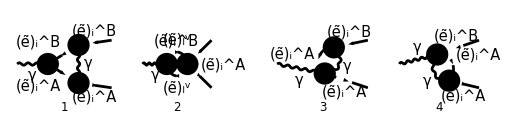

```mathematica
diagsVirt[0]=InsertFields[
CreateTopologies[1,1->2,
ExcludeTopologies->{Tadpoles,SelfEnergies}],
{V[1]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],(*Higgs*)
S[13|14],(*Squarks*)
V[2|3],(*Z, W*)
F[11|12](*Electroweakinos*)
}
];
Paint[
diagsVirt[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

### Photon bubbles

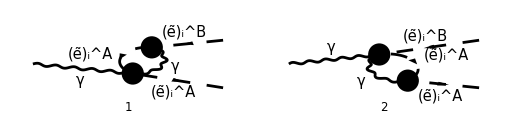

```mathematica
diagsVirt[1]=DiagramExtract[diagsVirt[0],{3,4}];
Paint[
diagsVirt[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
Mvirt[0]=FCFAConvert[
CreateFeynAmp[diagsVirt[1]],
IncomingMomenta->{p},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
ChangeDimension->D,
UndoChiralSplittings->True,
List->False,
Contract->True,
DropSumOver->True,
SMP->True
]
```

(ⅈ e^3 IndexDelta(A,B) (k·ε(p)-k_1·ε(p)))/(8 π^4 (0-m_l_iA^2).(k+k_1)^2)-(ⅈ e^3 IndexDelta(A,B) (k·ε(p)-k_2·ε(p)))/(8 π^4 (0-m_l_iA^2).(k+k_2)^2)

```mathematica
Mvirt[1]=Mvirt[0] 3/2SMP["e_Q"]//FCE//ReplaceAll[#,{
FAD[{k,MSf[A,2,i]},k+k1]->FAD[{k,MSf[B,2,i]},k+k1]
}]&
```

3/2 e_Q ((ⅈ e^3 IndexDelta(A,B) (k·ε(p)-k_1·ε(p)))/(8 π^4 (0-m_l_iB^2).(k+k_1)^2)-(ⅈ e^3 IndexDelta(A,B) (k·ε(p)-k_2·ε(p)))/(8 π^4 (0-m_l_iA^2).(k+k_2)^2))

```mathematica
Mvirt[2]=Mvirt[1]//TID[#,k,ToPaVe->True]&//FullSimplify
```

TID::failmsg: Error! TID has encountered a fatal problem and must abort the computation. The problem reads: The loop momentum k has scalar product rules attached to it.

$Aborted

```mathematica
FCClearScalarProducts[];
SPD[p]=s;
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
SPD[k1,k2]=1/2(s-MSf[A,2,i]^2-MSf[B,2,i]^2);
```

```mathematica
Mvirt[3]=Mvirt[2]//FullSimplify
```

Mvirt(2)

```mathematica
Mvirt[4]=Mvirt[3]//PaXEvaluateUV
```

0

```mathematica
A0[m1^2]/(4m1^2)+A0[m2^2]/(4m2^2)-B0[m1^2,0,m1^2]-B0[m2^2,0,m2^2]
%//PaXEvaluateIR
```

-B_0(m_1^2,0,m_1^2)-B_0(m_2^2,0,m_2^2)+(A_0(m_1^2))/(4 m_1^2)+(A_0(m_2^2))/(4 m_2^2)

0

### Slepton bubble

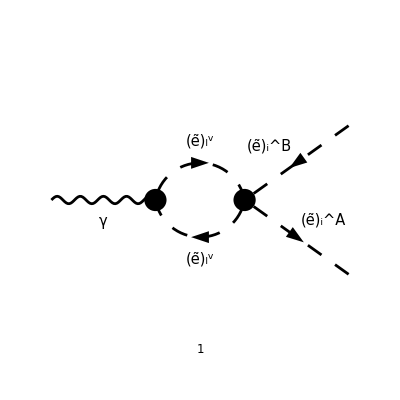

```mathematica
diagsVirt[2]=DiagramExtract[diagsVirt[0],2];
Paint[
diagsVirt[2],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
Mslepton[0]=FCFAConvert[
CreateFeynAmp[diagsVirt[2]],
IncomingMomenta->{p},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
ChangeDimension->D,
UndoChiralSplittings->True,
List->False,
Contract->True,
DropSumOver->True,
SMP->True
]
```

(ⅈ e^3 (-2 (k·ε(p))+k_1·ε(p)+k_2·ε(p)) (2 Conjugate[(USf(2,i)(B,2))] (IndexDelta(i,Gen4) Conjugate[(USf(2,i)(Sfe4,1))] ((MLE(i))^2 (cos(θ_W))^2 USf(2,i)(A,2) USf(2,i)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,1) USf(2,i)(Sfe4,2))+Conjugate[(USf(2,Gen4)(Sfe4,1))] (MLE(i) (cos(θ_W))^2 MLE(Gen4) USf(2,i)(A,1) USf(2,Gen4)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,Gen4)(Sfe4,1))+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) IndexDelta(i,Gen4) USf(2,i)(Sfe4,2) Conjugate[(USf(2,i)(Sfe4,2))]+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,Gen4)(Sfe4,2) Conjugate[(USf(2,Gen4)(Sfe4,2))])+Conjugate[(USf(2,i)(B,1))] (2 IndexDelta(i,Gen4) Conjugate[(USf(2,i)(Sfe4,2))] ((MLE(i))^2 (cos(θ_W))^2 USf(2,i)(A,1) USf(2,i)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,i)(Sfe4,1))+2 Conjugate[(USf(2,Gen4)(Sfe4,2))] (MLE(i) (cos(θ_W))^2 MLE(Gen4) USf(2,i)(A,2) USf(2,Gen4)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,1) USf(2,Gen4)(Sfe4,2))+CB^2 m_W^2 USf(2,i)(A,1) IndexDelta(i,Gen4) USf(2,i)(Sfe4,1) Conjugate[(USf(2,i)(Sfe4,1))]+CB^2 m_W^2 USf(2,i)(A,1) USf(2,Gen4)(Sfe4,1) Conjugate[(USf(2,Gen4)(Sfe4,1))])))/(64 π^4 CB^2 m_W^2 (cos(θ_W))^2 (sin(θ_W))^2 (k^2-m_l_Gen4Sfe4^2).((k-k_1-k_2)^2-m_l_Gen4Sfe4^2))

```mathematica
Mslepton[0]//FCE//StandardForm
```

(ⅈ FAD[{k,MSf[Sfe4,2,Gen4]},{k-k1-k2,MSf[Sfe4,2,Gen4]}] SMP[e]^3 (-2 SPD[k,Polarization[p,ⅈ]]+SPD[k1,Polarization[p,ⅈ]]+SPD[k2,Polarization[p,ⅈ]]) (2 (USf[2,i][B,2])^* (2 CB^2 (USf[2,i][Sfe4,2])^* IndexDelta[i,Gen4] SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,2] USf[2,i][Sfe4,2]+(USf[2,i][Sfe4,1])^* IndexDelta[i,Gen4] (MLE[i]^2 SMP[cos_W]^2 USf[2,i][A,2] USf[2,i][Sfe4,1]-CB^2 SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,1] USf[2,i][Sfe4,2])+2 CB^2 (USf[2,Gen4][Sfe4,2])^* SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,2] USf[2,Gen4][Sfe4,2]+(USf[2,Gen4][Sfe4,1])^* (-CB^2 SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,2] USf[2,Gen4][Sfe4,1]+MLE[i] MLE[Gen4] SMP[cos_W]^2 USf[2,i][A,1] USf[2,Gen4][Sfe4,2]))+(USf[2,i][B,1])^* (CB^2 (USf[2,i][Sfe4,1])^* IndexDelta[i,Gen4] SMP[m_W]^2 USf[2,i][A,1] USf[2,i][Sfe4,1]+2 (USf[2,i][Sfe4,2])^* IndexDelta[i,Gen4] (-CB^2 SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,2] USf[2,i][Sfe4,1]+MLE[i]^2 SMP[cos_W]^2 USf[2,i][A,1] USf[2,i][Sfe4,2])+CB^2 (USf[2,Gen4][Sfe4,1])^* SMP[m_W]^2 USf[2,i][A,1] USf[2,Gen4][Sfe4,1]+2 (USf[2,Gen4][Sfe4,2])^* (MLE[i] MLE[Gen4] SMP[cos_W]^2 USf[2,i][A,2] USf[2,Gen4][Sfe4,1]-CB^2 SMP[m_W]^2 SMP[sin_W]^2 USf[2,i][A,1] USf[2,Gen4][Sfe4,2]))))/(64 CB^2 π^4 SMP[cos_W]^2 SMP[m_W]^2 SMP[sin_W]^2)

```mathematica
Mslepton[1]=Mslepton[0]//TID[#,k,ToPaVe->True]&
```

0

```mathematica
FAD[{k,ma},{k-k1-k2,mb}]//TID[#,k,ToPaVe->True]&
```

ⅈ π^2 B_0(s,ma^2,mb^2)

### Radiation

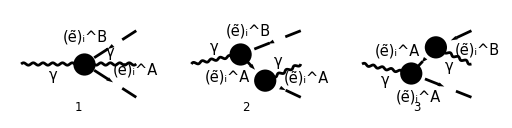

```mathematica
diagsRad[0]=InsertFields[
CreateTopologies[0,1->3,
ExcludeTopologies->{Tadpoles,SelfEnergies}],
{V[1]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],(*Higgs*)
S[13|14],(*Squarks*)
V[2|3],(*Z, W*)
F[11|12](*Electroweakinos*)
}
];
Paint[
diagsRad[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

### Full process

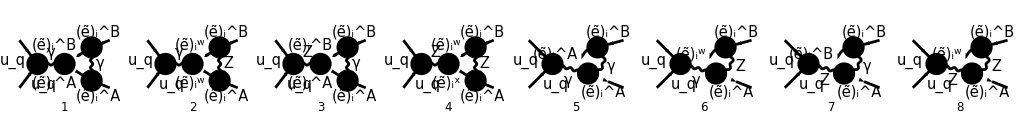

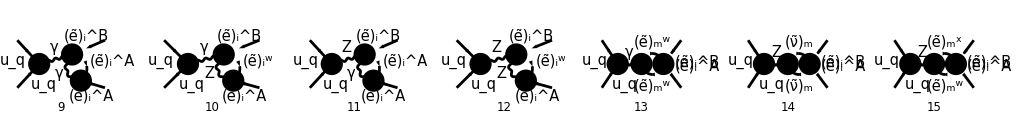

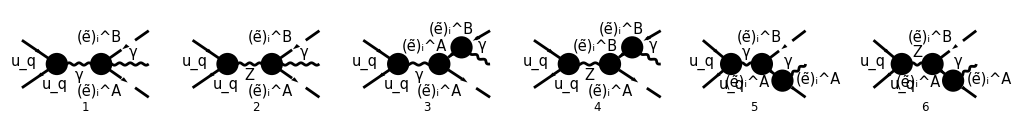

```mathematica
diagsVirt[0]=InsertFields[
CreateTopologies[1,2->2,
ExcludeTopologies->{Tadpoles,SelfEnergies}],
{F[3,{q}],-F[3,{q}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],(*Higgs*)
S[13|14],(*Squarks*)
V[3],(*Z, W*)
F[11|12](*Electroweakinos*),
F[3|4]
}
];
diagsRad[0]=InsertFields[
CreateTopologies[0,2->3,
ExcludeTopologies->{Tadpoles,SelfEnergies}],
{F[3,{q}],-F[3,{q}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],(*Higgs*)
S[13|14],(*Squarks*)
V[3],(*Z, W*)
F[11|12](*Electroweakinos*),
F[3|4]
}
];
Paint[
diagsVirt[0],
ColumnsXRows->{8,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{1024,128}
];
Paint[
diagsRad[0],
ColumnsXRows->{8,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{1024,128}
];
```

### Derivative of B0 function

```mathematica
B0[SPD[p],0,m^2]
```

B_0(s,0,m^2)

```mathematica
DB0[p,0,m^2]
```

DB0(p,0,m^2)

```mathematica
DB0[p,0,m^2]
```

DB0(p,0,m^2)

```mathematica
B0[SPD[p],0,m^2]
```

B_0(s,0,m^2)

```mathematica
SPD[k+2p]FAD[k,{k+p,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Simplify
```

-(ⅈ (k+2 p)^2)/(π^2 k^2.((k+p)^2-m^2))

2 (m^2+s) B_0(s,0,m^2)-A_0(m^2)

((m^2+2 s) ε_UV log(μ^2/m^2)+m^2 ((3-ℽ+log(4 π)) ε_UV+1)+2 s ((2-ℽ+log(4 π)) ε_UV+1))/ε_UV+(2 (s^2-m^4) log(m^2/(m^2-s)))/s

```mathematica
1/(A B)+2/A-2/B-2(p^2-m^2-2p^2)/(A B)//ReplaceAll[#,{A->k^2,B->(k+p)^2-m^2}]&
%//FullSimplify
```

-(2 (-m^2-p^2))/(k^2 ((k+p)^2-m^2))+1/(k^2 ((k+p)^2-m^2))+2/k^2-2/((k+p)^2-m^2)

(4 p (k+p)+1)/(k^2 (k-m+p) (k+m+p))

```mathematica
Gamma[1+ϵ]
%//Series[#,{ϵ,0,2}]&
```

ϵ+1

1-ℽ ϵ+1/12 (6 ℽ^2+π^2) ϵ^2+O(ϵ^3)

```mathematica
1/((1-x)^(1+ϵ))//Series[#,{ϵ,0,1}]&
```

1/(1-x)+(ϵ log(1-x))/(x-1)+O(ϵ^2)

```mathematica
PlusDistribution[1/(1-x)^2]
```

(1/(1-x)^2)_+

## 24.02

```mathematica
Gamma[1+ϵ]
%//Series[#,{ϵ,0,1}]&
```

ϵ+1

1-ℽ ϵ+O(ϵ^2)

```mathematica
x PlusDistribution[1/(1-x)]
%//Integrate2[#,{x,0,1}]&
```

x (1/(1-x))_+

-1

```mathematica
1/(3-2ϵ)
%//Series[#,{ϵ,0,1}]&
```

1/(3-2 ϵ)

1/3+(2 ϵ)/9+O(ϵ^2)

```mathematica
1/Gamma[2-2ϵ]
%//Series[#,{ϵ,0,1}]&
```

1/(2-2 ϵ)

1+(2-2 ℽ) ϵ+O(ϵ^2)

```mathematica
Gamma[2-2ϵ]
%//Series[#,{ϵ,0,1}]&
```

2-2 ϵ

1+2 (ℽ-1) ϵ+O(ϵ^2)

```mathematica
256 Pi^3/(4 Pi^2 s λ^(3/2))
```

(64 π)/(λ^(3/2) s)

```mathematica
96Pi/λ^(3/2)2/(3s)
```

(64 π)/(λ^(3/2) s)

```mathematica
32Pi e^2/λ^(3/2) λ/(64 Pi^3)
2e^2/(4Pi^2 λ^(1/2))
```

e^2/(2 π^2 √λ)

e^2/(2 π^2 √λ)

```mathematica
A0[m^2]//PaXEvaluateUVIRSplit//FCHideEpsilon
```

m^2 Δ_UV-m^2 (-log(μ^2/(π m^2))-1+log(4 π))

```mathematica
Gamma[2-2ϵ]
%//Series[#,{ϵ,0,1}]&
```

2-2 ϵ

1+2 (ℽ-1) ϵ+O(ϵ^2)

```mathematica
1/((1+x)(1-x))-2β1/((1+x)(1-x)^2)-2β2/((1+x)^2(1-x))
%//Apart[#,x]&
```

-(2 β_1)/((1-x)^2 (x+1))-(2 β_2)/((1-x) (x+1)^2)+1/((1-x) (x+1))

-β_1/(x-1)^2+(-β_1-β_2+1)/(2 (x+1))-β_2/(x+1)^2+(β_1+β_2-1)/(2 (x-1))

```mathematica
xm-xp//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&
```

-2 √λ

```mathematica
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2a b-2a c-2b c
```

```mathematica
(xp-1)(xm-1)//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&//ReplaceAll[#,{λ->Kallen[1,β1,β2]}]&//Simplify
```

4 β_1

```mathematica
(xp+1)(xm+1)//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&//ReplaceAll[#,{λ->Kallen[1,β1,β2]}]&//Simplify
```

4 β_2

```mathematica
(xp+1)(xm-1)//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&
```

(-β_1+β_2-√λ-1) (-β_1+β_2+√λ+1)

```mathematica
(xp-1)(xm+1)//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&
```

(-β_1+β_2-√λ+1) (-β_1+β_2+√λ-1)

```mathematica
(xp+1)(xm-1)/((xp-1)(xm+1))//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&//FullSimplify
```

((β_1-β_2)^2-(√λ+1)^2)/((β_1-β_2)^2-(√λ-1)^2)

```mathematica
Kallen[1,β1,β2]
```

β_1^2-2 β_2 β_1-2 β_1+β_2^2-2 β_2+1

```mathematica
(xp-x)(x-xm)/((1+x)^2(1-x)^2)Log[(xp-x)(x-xm)]
%//Integrate[#,{x,xm,xp},Assumptions->-1<xm<xp<1]&
```

((x-x^-) (x^+-x) log((x-x^-) (x^+-x)))/((1-x)^2 (x+1)^2)

$Aborted

```mathematica
(-β1/(x-1)^2-β2/(x+1)^2+(1-β1-β2)/2(1/(x+1)-1/(x-1)))(Log[xp-x]+Log[x-xm])
%//Integrate[#,{x,xm,xp},Assumptions->-1<xm<xp<1&&β1∈PositiveReals&&β2∈PositiveReals]&
```

(-β_1/(x-1)^2+1/2 (-β_1-β_2+1) (1/(x+1)-1/(x-1))-β_2/(x+1)^2) (log(x-x^-)+log(x^+-x))

ConditionalExpression[-((2 ⅈ π (x^-)^2 (x^+)^4+3 (x^-)^2 (x^+)^4-2 ⅈ π (x^+)^4-3 (x^+)^4-4 (x^-)^2 (x^+)^3+4 (x^+)^3-2 ⅈ π (x^-)^2 (x^+)^2-3 (x^-)^2 (x^+)^2+4 (x^-)^2 log(ⅇ^(1/4 x^+ (-2 ⅈ π x^+-3 x^++4))) (x^+)^2-4 log(ⅇ^(1/4 x^+ (-2 ⅈ π x^+-3 x^++4))) (x^+)^2+16 x^- β_1 log(1-x^-) (x^+)^2+16 β_1 log(1-x^-) (x^+)^2+16 x^- β_2 log(x^-+1) (x^+)^2-16 β_2 log(x^-+1) (x^+)^2-16 x^- β_1 log(1-x^+) (x^+)^2-16 β_1 log(1-x^+) (x^+)^2-16 x^- β_2 log(x^++1) (x^+)^2+16 β_2 log(x^++1) (x^+)^2+32 x^- β_1 log(x^+-x^-) (x^+)^2+32 β_1 log(x^+-x^-) (x^+)^2+32 x^- β_2 log(x^+-x^-) (x^+)^2-32 β_2 log(x^+-x^-) (x^+)^2+4 (x^-)^2 log(1-x^-) log(x^+-x^-) (x^+)^2-4 log(1-x^-) log(x^+-x^-) (x^+)^2-4 (x^-)^2 log(x^-+1) log(x^+-x^-) (x^+)^2-8 (x^-)^2 β_1 log(x^-+1) log(x^+-x^-) (x^+)^2+8 β_1 log(x^-+1) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_2 log(x^-+1) log(x^+-x^-) (x^+)^2-8 β_2 log(x^-+1) log(x^+-x^-) (x^+)^2+4 log(x^-+1) log(x^+-x^-) (x^+)^2-4 (x^-)^2 log(1-x^+) log(x^+-x^-) (x^+)^2+4 log(1-x^+) log(x^+-x^-) (x^+)^2-12 (x^-)^2 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_1 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2-8 β_1 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_2 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2-8 β_2 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2+12 log((x^--1)/(x^+-1)) log(x^+-x^-) (x^+)^2+8 (x^-)^2 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2-8 (x^-)^2 β_1 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2+8 β_1 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2-8 (x^-)^2 β_2 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2+8 β_2 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2-8 log((x^+-1)/(x^--1)) log(x^+-x^-) (x^+)^2+4 (x^-)^2 log((x^-+1)/(x^++1)) log(x^+-x^-) (x^+)^2-16 (x^-)^2 β_2 log((x^-+1)/(x^++1)) log(x^+-x^-) (x^+)^2+16 β_2 log((x^-+1)/(x^++1)) log(x^+-x^-) (x^+)^2-4 log((x^-+1)/(x^++1)) log(x^+-x^-) (x^+)^2+4 (x^-)^2 log(x^++1) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_1 log(x^++1) log(x^+-x^-) (x^+)^2-8 β_1 log(x^++1) log(x^+-x^-) (x^+)^2-8 (x^-)^2 β_2 log(x^++1) log(x^+-x^-) (x^+)^2+8 β_2 log(x^++1) log(x^+-x^-) (x^+)^2-4 log(x^++1) log(x^+-x^-) (x^+)^2-16 (x^-)^2 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_1 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2-8 β_1 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2+8 (x^-)^2 β_2 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2-8 β_2 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2+16 log((x^++1)/(x^-+1)) log(x^+-x^-) (x^+)^2-8 (x^-)^2 2(x^+-x^-)/(x^+-1) (x^+)^2+8 (x^-)^2 β_1 2(x^+-x^-)/(x^+-1) (x^+)^2-8 β_1 2(x^+-x^-)/(x^+-1) (x^+)^2+8 (x^-)^2 β_2 2(x^+-x^-)/(x^+-1) (x^+)^2-8 β_2 2(x^+-x^-)/(x^+-1) (x^+)^2+8 2(x^+-x^-)/(x^+-1) (x^+)^2+8 (x^-)^2 2(x^+-x^-)/(x^++1) (x^+)^2-8 (x^-)^2 β_1 2(x^+-x^-)/(x^++1) (x^+)^2+8 β_1 2(x^+-x^-)/(x^++1) (x^+)^2-8 (x^-)^2 β_2 2(x^+-x^-)/(x^++1) (x^+)^2+8 β_2 2(x^+-x^-)/(x^++1) (x^+)^2-8 2(x^+-x^-)/(x^++1) (x^+)^2+2 ⅈ π (x^+)^2+3 (x^+)^2+4 (x^-)^2 x^++16 (x^-)^2 β_1 log(1-x^-) x^+-16 β_1 log(1-x^-) x^++16 (x^-)^2 β_2 log(x^-+1) x^+-16 β_2 log(x^-+1) x^+-16 (x^-)^2 β_1 log(1-x^+) x^++16 β_1 log(1-x^+) x^+-16 (x^-)^2 β_2 log(x^++1) x^++16 β_2 log(x^++1) x^+-32 (x^-)^2 β_1 log(x^+-x^-) x^++32 β_1 log(x^+-x^-) x^+-32 (x^-)^2 β_2 log(x^+-x^-) x^++32 β_2 log(x^+-x^-) x^+-4 x^+-4 (x^-)^2 log(ⅇ^(1/4 x^+ (-2 ⅈ π x^+-3 x^++4)))+4 log(ⅇ^(1/4 x^+ (-2 ⅈ π x^+-3 x^++4)))+16 (x^-)^2 β_1 log(1-x^-)-16 x^- β_1 log(1-x^-)-32 β_1 log(1-x^-)-16 (x^-)^2 β_2 log(x^-+1)-16 x^- β_2 log(x^-+1)+32 β_2 log(x^-+1)-16 (x^-)^2 β_1 log(1-x^+)+16 x^- β_1 log(1-x^+)+32 β_1 log(1-x^+)+16 (x^-)^2 β_2 log(x^++1)+16 x^- β_2 log(x^++1)-32 β_2 log(x^++1)-32 (x^-)^2 β_1 log(x^+-x^-)-32 x^- β_1 log(x^+-x^-)+32 (x^-)^2 β_2 log(x^+-x^-)-32 x^- β_2 log(x^+-x^-)-4 (x^-)^2 log(1-x^-) log(x^+-x^-)+4 log(1-x^-) log(x^+-x^-)+4 (x^-)^2 log(x^-+1) log(x^+-x^-)+8 (x^-)^2 β_1 log(x^-+1) log(x^+-x^-)-8 β_1 log(x^-+1) log(x^+-x^-)-8 (x^-)^2 β_2 log(x^-+1) log(x^+-x^-)+8 β_2 log(x^-+1) log(x^+-x^-)-4 log(x^-+1) log(x^+-x^-)+4 (x^-)^2 log(1-x^+) log(x^+-x^-)-4 log(1-x^+) log(x^+-x^-)+12 (x^-)^2 log((x^--1)/(x^+-1)) log(x^+-x^-)-8 (x^-)^2 β_1 log((x^--1)/(x^+-1)) log(x^+-x^-)+8 β_1 log((x^--1)/(x^+-1)) log(x^+-x^-)-8 (x^-)^2 β_2 log((x^--1)/(x^+-1)) log(x^+-x^-)+8 β_2 log((x^--1)/(x^+-1)) log(x^+-x^-)-12 log((x^--1)/(x^+-1)) log(x^+-x^-)-8 (x^-)^2 log((x^+-1)/(x^--1)) log(x^+-x^-)+8 (x^-)^2 β_1 log((x^+-1)/(x^--1)) log(x^+-x^-)-8 β_1 log((x^+-1)/(x^--1)) log(x^+-x^-)+8 (x^-)^2 β_2 log((x^+-1)/(x^--1)) log(x^+-x^-)-8 β_2 log((x^+-1)/(x^--1)) log(x^+-x^-)+8 log((x^+-1)/(x^--1)) log(x^+-x^-)-4 (x^-)^2 log((x^-+1)/(x^++1)) log(x^+-x^-)+16 (x^-)^2 β_2 log((x^-+1)/(x^++1)) log(x^+-x^-)-16 β_2 log((x^-+1)/(x^++1)) log(x^+-x^-)+4 log((x^-+1)/(x^++1)) log(x^+-x^-)-4 (x^-)^2 log(x^++1) log(x^+-x^-)-8 (x^-)^2 β_1 log(x^++1) log(x^+-x^-)+8 β_1 log(x^++1) log(x^+-x^-)+8 (x^-)^2 β_2 log(x^++1) log(x^+-x^-)-8 β_2 log(x^++1) log(x^+-x^-)+4 log(x^++1) log(x^+-x^-)+16 (x^-)^2 log((x^++1)/(x^-+1)) log(x^+-x^-)-8 (x^-)^2 β_1 log((x^++1)/(x^-+1)) log(x^+-x^-)+8 β_1 log((x^++1)/(x^-+1)) log(x^+-x^-)-8 (x^-)^2 β_2 log((x^++1)/(x^-+1)) log(x^+-x^-)+8 β_2 log((x^++1)/(x^-+1)) log(x^+-x^-)-16 log((x^++1)/(x^-+1)) log(x^+-x^-)-8 ((x^-)^2-1) ((x^+)^2-1) (β_1+β_2-1) 2(x^--x^+)/(x^--1)+8 ((x^-)^2-1) ((x^+)^2-1) (β_1+β_2-1) 2(x^--x^+)/(x^-+1)+8 (x^-)^2 2(x^+-x^-)/(x^+-1)-8 (x^-)^2 β_1 2(x^+-x^-)/(x^+-1)+8 β_1 2(x^+-x^-)/(x^+-1)-8 (x^-)^2 β_2 2(x^+-x^-)/(x^+-1)+8 β_2 2(x^+-x^-)/(x^+-1)-8 2(x^+-x^-)/(x^+-1)-8 (x^-)^2 2(x^+-x^-)/(x^++1)+8 (x^-)^2 β_1 2(x^+-x^-)/(x^++1)-8 β_1 2(x^+-x^-)/(x^++1)+8 (x^-)^2 β_2 2(x^+-x^-)/(x^++1)-8 β_2 2(x^+-x^-)/(x^++1)+8 2(x^+-x^-)/(x^++1))/(16 (x^--1) (x^-+1) (x^+-1) (x^++1))), x^-≥0∧x^+>0]

```mathematica
%//FullSimplify
```

ConditionalExpression[1/16 (8 (β_1+β_2-1) 2(x^--x^+)/(x^--1)-8 (β_1+β_2-1) 2(x^--x^+)/(x^-+1)-8 (β_1+β_2-1) 2(x^+-x^-)/(x^+-1)+8 (β_1+β_2-1) 2(x^+-x^-)/(x^++1)-4 log(ⅇ^(1/4 x^+ (4+(-3-2 ⅈ π) x^+)))+1/(((x^-)^2-1) ((x^+)^2-1))(32 β_2 log(x^++1)+16 (β_1 (x^-+1) (x^++1) (x^-+x^+-2) log(1-x^+)+β_2 (-x^+ (x^++1)+(x^+-1) (x^-)^2+((x^+)^2-1) x^-) log(x^++1))+4 log(x^+-x^-) (4 log(x^++1)+8 (x^--x^+) (β_1 (x^-+1) (x^++1)+β_2 (x^--1) (x^+-1))-(2 β_1+2 β_2-3) ((x^-)^2-1) ((x^+)^2-1) log((x^--1)/(x^+-1))+2 (β_1+β_2-1) ((x^-)^2-1) ((x^+)^2-1) log((x^+-1)/(x^--1))-4 (β_1+β_2-(β_1+β_2-1) (x^+)^2+(β_1+β_2-1) ((x^+)^2-1) (x^-)^2) log(x^++1)+((x^-)^2-1) ((x^+)^2-1) log(1-x^+))+4 (x^-+1) (x^++1) log(1-x^-) ((x^-+x^+-x^+ x^--1) log(x^+-x^-)-4 β_1 (x^-+x^+-2))+16 (x^--1) (x^+-1) log(x^-+1) ((β_1+β_2-1) (x^-+1) (x^++1) log(x^+-x^-)-β_2 (x^-+x^++2))+((x^-)^2-1) x^+ (4+(-3-2 ⅈ π) x^+) ((x^+)^2-1))), x^-≥0]

```mathematica
(xp-x)(x-xm)
%//ReplaceAll[#,{
xm->-Sqrt[λ]-(β1-β2),
xp->Sqrt[λ]-(β1-β2)
}]&//FullSimplify
```

(x-x^-) (x^+-x)

λ-(β_1-β_2+x)^2

```mathematica
1/x Log[1-x]
%//Integrate[#,{x,a,b},Assumptions->-1<a<b<1]&
```

(log(1-x))/x

2a-2b

```mathematica
PolyLog[2,x]
```

2x

```mathematica
1/((x+1)^2(x-1)^2)
%//Apart
```

1/((x-1)^2 (x+1)^2)

1/(4 (x+1))+1/(4 (x+1)^2)-1/(4 (x-1))+1/(4 (x-1)^2)

```mathematica
Log[x]/x
%//Limit[#,x->0]&
```

(log(x))/x

Indeterminate

```mathematica
-1/(x-1)^2Log[xp-x]
%//Integrate[#,x,Assumptions->-1<xm<xp<1]&
```

-(log(x^+-x))/(x-1)^2

(log(1-x))/(x^+-1)-(log(x-x^+))/(x^+-1)+(log(x^+-x))/(x-1)

```mathematica
1/((x-a)(x-b))
%//Integrate[#,x]&
```

1/((x-a) (x-b))

(log(x-a)-log(x-b))/(a-b)

```mathematica
1/((x-a)(x-b))//Apart[#,x]&
```

1/((b-a) (x-b))+1/((a-b) (x-a))

```mathematica
(1/(x-xm)+1/(x-xp))(β1/(x-1)+β2/(x+1))
%//Apart[#,x]&
%//Integrate[#,x]&
```

(1/(x-x^-)+1/(x-x^+)) (β_1/(x-1)+β_2/(x+1))

(β_1-β_2+β_1 x^-+β_2 x^-)/((x-x^-) (x^--1) (x^-+1))+(β_1-β_2+β_1 x^++β_2 x^+)/((x-x^+) (x^+-1) (x^++1))-(β_1 (x^-+x^+-2))/((x-1) (x^--1) (x^+-1))-(β_2 (x^-+x^++2))/((x+1) (x^-+1) (x^++1))

((β_1 (x^-+1)+β_2 (x^--1)) log(x-x^-))/((x^-)^2-1)+((β_1 (x^++1)+β_2 (x^+-1)) log(x-x^+))/((x^+)^2-1)-(β_1 (x^-+x^+-2) log(x-1))/((x^--1) (x^+-1))-(β_2 (x^-+x^++2) log(x+1))/((x^-+1) (x^++1))

## 25.02

```mathematica
FCClearScalarProducts[];
SPD[q1]=SPD[q2]=0;
SPD[q1,q2]=Q^2/2;
```

```mathematica
SpinorUBarD[q2].GAD[ν].GSD[k+q2].GAD[μ].GSD[k-q1].GAD[ν].SpinorVD[q]
%//DiracSimplify//FullSimplify
```

ū(q2).γ^ν.(γ·(k+q2)).γ^μ.(γ·(k-q1)).γ^ν.v(q)

((D-2) k^2+4 (k·q2)-2 Q^2) (φ(q2)).γ^μ.(φ(-q))+(D-4) (φ(q2)).(γ·k).γ^μ.(γ·q1).(φ(-q))-2 ((D-2) k^μ+2 q2^μ) (φ(q2)).(γ·k).(φ(-q))+2 (φ(q2)).(γ·q1).γ^μ.(γ·k).(φ(-q))+4 q2^μ (φ(q2)).(γ·q1).(φ(-q))

```mathematica
FAD[k,k]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

-ⅈ/(π^2 (k^2)^2)

B_0(0,0,0)

1/ε_UV-1/ε_IR

```mathematica
Gamma[2-ϵ]
%//Series[#,{ϵ,0,1}]&
```

2-ϵ

1+(ℽ-1) ϵ+O(ϵ^2)

```mathematica
(2-2ϵ)^2/(4-2ϵ)
%//Series[#,{ϵ,0,2}]&
```

(2-2 ϵ)^2/(4-2 ϵ)

1-(3 ϵ)/2+ϵ^2/4+O(ϵ^3)

## 26.02

```mathematica
C0[m1^2,m2^2,0,m1^2,0,m2^2]
%//PaXEvaluateIR
%%//PaXEvaluateUV
```

C_0(m_1^2,m_2^2,0,m_1^2,0,m_2^2)

(log(m_1^2/m_2^2))/(2 m_1^2 ε_IR-2 m_2^2 ε_IR)

0

```mathematica
(2FVD[k,μ]+FVD[p,μ])FAD[{k,m3},{k+p,m4}]
%//TID[#,k,ToPaVe->True]&
%//PaXEvaluateUVIRSplit//Collect2[#,{FVD[p,μ]}]&
```

(2 k^μ+p^μ)/((k^2-m_3^2).((k+p)^2-m4^2))

-(ⅈ π^2 (m_3^2-m4^2) p^μ B_0(p^2,m_3^2,m4^2))/p^2+(ⅈ π^2 p^μ A_0(m_3^2))/p^2-(ⅈ π^2 p^μ A_0(m4^2))/p^2

1/(2 p^4)ⅈ π^2 p^μ (-2 m_3^2 p^2 log(μ^2/m4^2)+m_3^2 p^2 log(m_3^2/m4^2)-m4^2 p^2 log(m_3^2/m4^2)+m_3^4 log(m_3^2/m4^2)-2 m_3^2 m4^2 log(m_3^2/m4^2)-2 m_3^2 √(-2 m_3^2 m4^2-2 m_3^2 p^2+m_3^4+m4^4-2 m4^2 p^2+p^4) log((√(-2 p^2 (m_3^2+m4^2)+(m_3^2-m4^2)^2+p^4)+m_3^2+m4^2-p^2)/(2 m_3 m4))+2 m4^2 √(-2 m_3^2 m4^2-2 m_3^2 p^2+m_3^4+m4^4-2 m4^2 p^2+p^4) log((√(-2 p^2 (m_3^2+m4^2)+(m_3^2-m4^2)^2+p^4)+m_3^2+m4^2-p^2)/(2 m_3 m4))+m4^4 log(m_3^2/m4^2)+2 m_3^2 p^2 log(μ^2/m_3^2)-2 m_3^2 p^2+2 m4^2 p^2)

```mathematica
4SPD[k]/d((1-x)FVD[k1,μ]-(1-y)FVD[k2,μ])+((1-2x)FVD[k1,μ]-(1-2y)FVD[k2,μ])(SPD[k]+(x^2-2x+2-x-y+x y)m1^2+(y^2-2y+2-x-y+x y)m2^2-(2-x-y+x y)SPD[p])
%//Collect2[#,{FVD[k1,μ],FVD[k2,μ]},Factoring->FullSimplify]&
%//ReplaceAll[#,{m1->0,m2->0}]&//ReplaceAll[#,{FVD[k1,μ]->1/2(FVD[p,μ]-FVD[K,μ]),FVD[k2,μ]->1/2(FVD[p,μ]+FVD[K,μ])}]&//FullSimplify//ReplaceAll[#,SPD[p]->0]&
```

(4 k^2 ((1-x) k_1^μ-(1-y) k_2^μ))/d+((1-2 x) k_1^μ-(1-2 y) k_2^μ) (k^2+m_1^2 (x^2+x y-3 x-y+2)+m_2^2 (x y-x+y^2-3 y+2)-p^2 (x y-x-y+2))

k_1^μ ((1-2 x) (k^2+(x+y-2) (m_1^2 (x-1)+m_2^2 (y-1))+p^2 (x (-y)+x+y-2))-(4 k^2 (x-1))/d)+k_2^μ ((4 k^2 (y-1))/d-(1-2 y) (k^2+(x+y-2) (m_1^2 (x-1)+m_2^2 (y-1))+p^2 (x (-y)+x+y-2)))

(k^2 K^μ (d (x+y-1)+2 (x+y-2))-(d+2) k^2 p^μ (x-y))/d

## On-shell counterterm

```mathematica
triangle[0]=1/λQ(m1^2+m2^2-Q^2)(2Q^2B0[Q^2,m1^2,m2^2]+λQ C0[m1^2,m2^2,Q^2,m1^2,0,m2^2])-1/4(A0[m1^2]/m1^2+A0[m2^2]/m2^2)+1/(2λQ)((λQ+2(m2^2-Q^2)^2-2m1^4)B0[m1^2,0,m1^2]+(λQ+2(m1^2-Q^2)^2-2m2^4)B0[m2^2,0,m2^2])
```

((m_1^2+m_2^2-Q^2) (2 Q^2 B_0(Q^2,m_1^2,m_2^2)+λ_Q C_0(m_1^2,m_2^2,Q^2,m_1^2,0,m_2^2)))/λ_Q+((2 (m_2^2-Q^2)^2-2 m_1^4+λ_Q) B_0(m_1^2,0,m_1^2)+(2 (m_1^2-Q^2)^2-2 m_2^4+λ_Q) B_0(m_2^2,0,m_2^2))/(2 λ_Q)+1/4 (-(A_0(m_1^2))/m_1^2-(A_0(m_2^2))/m_2^2)

```mathematica
bubbles=-(B0[m1^2,0,m1^2]-A0[m1^2]/(4m1^2))+A0[m2^2]/(4m2^2)-B0[m2^2,0,m2^2]
```

-B_0(m_1^2,0,m_1^2)-B_0(m_2^2,0,m_2^2)+(A_0(m_1^2))/(4 m_1^2)+(A_0(m_2^2))/(4 m_2^2)

```mathematica
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2a b-2a c-2b c
```

```mathematica
triangle[1]=triangle[0]//ReplaceAll[#,{Q->0,λQ->Kallen[0,m1^2,m2^2]}]&//FullSimplify
```

1/4 ((2 (3 m_1^2+m_2^2) B_0(m_2^2,0,m_2^2)-2 (m_1^2+3 m_2^2) B_0(m_1^2,0,m_1^2))/(m_1^2-m_2^2)+4 (m_1^2+m_2^2) C_0(m_1^2,m_2^2,0,m_1^2,0,m_2^2)-(A_0(m_1^2))/m_1^2-(A_0(m_2^2))/m_2^2)

```mathematica
triangleIR=triangle[1]//PaXEvaluateIR
triangleUV=triangle[1]//PaXEvaluateUV
triangle[2]=triangle[1]//PaXEvaluateUVIRSplit//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->(FullSimplify[#,Assumptions->{m1∈PositiveReals,m2∈PositiveReals}]&)]&
```

((m_1^2+m_2^2) log(m_1^2/m_2^2))/(2 (m_1-m_2) (m_1+m_2) ε_IR)

1/(2 ε_UV)

((m_1^2+m_2^2) log(m_1/m_2))/((m_1-m_2) (m_1+m_2) ε_IR)-(4 (m_1^2+m_2^2) log(m_1/m_2) (-log(μ^2/m_2^2)+ℽ+log(π))+(3 m_1^2+5 m_2^2) log(μ^2/m_1^2)-(5 m_1^2+3 m_2^2) log(μ^2/m_2^2)+4 (m_1^2+m_2^2) log^2(m_1/m_2)+2 (m_1-m_2) (m_1+m_2) (-3+ℽ+log(π)))/(4 (m_1-m_2) (m_1+m_2))+1/(2 ε_UV)

```mathematica
Sin[Cos[x]^2]^2/Cos[Sin[x]^2]^2
%//Integrate[#,x,Assumptions->x∈Reals]&
```

sin^2(cos^2(x)) sec^2(sin^2(x))

Integrate[sin^2(cos^2(x)) sec^2(sin^2(x)),x,Assumptions→x∈ℝ]

## 27.02

```mathematica
C0[m1^2,m2^2,s,m1^2,0,m2^2]//PaXEvaluateUV
C0[m1^2,m2^2,s,m1^2,0,m2^2]//PaXEvaluateIR
```

0

(log((√(-2 m_1^2 (m_2^2+s)+(m_2^2-s)^2+m_1^4)+m_1^2+m_2^2-s)/(2 m_1 m_2)))/(ε_IR √(-2 m_1^2 s-2 m_2^2 s+m_1^4-2 m_2^2 m_1^2+m_2^4+s^2))

### Triangle

```mathematica
triangle[0]=1/(I Pi^2)FVD[2k+k1-k2,μ]SPD[k+2k1,k-2k2]FAD[k,{k+k1,m1},{k-k2,m2}]
```

-(ⅈ (2 k+k_1-k_2)^μ ((k+2 k_1)·(k-2 k_2)))/(π^2 k^2.((k+k_1)^2-m_1^2).((k-k_2)^2-m_2^2))

```mathematica
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1,k2]=1/2(SPD[p]-m1^2-m2^2);
SPD[p]=0;
```

```mathematica
triangle[1]=triangle[0]//TID[#,k,ToPaVe->True]&//FullSimplify
```

-((5 m_1^2+3 m_2^2) (k_1^μ+k_2^μ) B_0(0,m_1^2,m_2^2))/(m_1^2-m_2^2)+(((5 m_1^4+6 m_2^2 m_1^2+5 m_2^4) k_1^μ+(7 m_1^4+10 m_2^2 m_1^2-m_2^4) k_2^μ) B_0(m_1^2,0,m_1^2))/((m_1^2-m_2^2)^2)+(((m_1^4-10 m_2^2 m_1^2-7 m_2^4) k_1^μ-(5 m_1^4+6 m_2^2 m_1^2+5 m_2^4) k_2^μ) B_0(m_2^2,0,m_2^2))/((m_1^2-m_2^2)^2)+2 (m_1^2+m_2^2) (k_1^μ-k_2^μ) C_0(0,m_1^2,m_2^2,m_2^2,m_1^2,0)-2 (k_1^μ+k_2^μ) B_1(0,m_2^2,m_1^2)-(k_1^μ A_0(m_1^2))/m_1^2+(k_2^μ A_0(m_2^2))/m_2^2

```mathematica
triangleIR[0]=triangle[1]//PaXEvaluateIR//FullSimplify
triangleUV[0]=triangle[1]//PaXEvaluateUV//FullSimplify
```

((m_1^2+m_2^2) (k_1^μ-k_2^μ) log(m_1^2/m_2^2))/((m_1-m_2) (m_1+m_2) ε_IR)

(k_1^μ-k_2^μ)/ε_UV

```mathematica
triangle[2]=triangle[1]//PaXEvaluateUVIRSplit//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&
```

((m_1^2+m_2^2) (k_1^μ-k_2^μ) log(m_1^2/m_2^2))/((m_1-m_2) (m_1+m_2) ε_IR)+1/(2 (m_1-m_2)^2 (m_1+m_2)^2)(k_2^μ (16 (m_1^2+m_2^2) m_1^2 log(μ^2/m_1^2)-2 (3 m_1^2+m_2^2)^2 log(μ^2/m_2^2)+2 log(m_1^2/m_2^2) ((m_2^4-m_1^4) log(μ^2/m_2^2)+3 m_2^2 m_1^2+m_1^4 (5+ℽ+log(π))-m_2^4 (-1+ℽ+log(π)))+(m_1^4-m_2^4) log^2(m_1^2/m_2^2)+(m_1-m_2) (m_1+m_2) (m_1^2 (1+2 ℽ+2 log(π))+m_2^2 (13-2 ℽ-2 log(π))))-k_1^μ (8 (m_1^2+m_2^2)^2 log(μ^2/m_2^2)-2 (5 m_1^4+6 m_2^2 m_1^2+5 m_2^4) log(μ^2/m_1^2)+2 log(m_1^2/m_2^2) ((m_2^4-m_1^4) log(μ^2/m_2^2)-3 m_2^2 m_1^2+m_1^4 (-5+ℽ+log(π))-m_2^4 (1+ℽ+log(π)))+(m_1^4-m_2^4) log^2(m_1^2/m_2^2)+(m_1-m_2) (m_1+m_2) (m_1^2 (-13+2 ℽ+2 log(π))-m_2^2 (1+2 ℽ+2 log(π)))))+(k_1^μ-k_2^μ)/ε_UV

### Bubbles

```mathematica
bubble[0]=1/(I Pi^2)(-FVD[k-k1,μ]FAD[{k,m1},k+k1]+FVD[k-k2,μ]FAD[{k,m2},k+k2])
```

-(ⅈ ((k-k_2)^μ/((k^2-m_2^2).(k+k_2)^2)-(k-k_1)^μ/((k^2-m_1^2).(k+k_1)^2)))/π^2

```mathematica
bubble[1]=bubble[0]//TID[#,k,ToPaVe->True]&//FullSimplify
```

1/2 ((k_1^μ (4 m_1^2 B_0(m_1^2,0,m_1^2)-A_0(m_1^2)))/m_1^2+(k_2^μ (A_0(m_2^2)-4 m_2^2 B_0(m_2^2,0,m_2^2)))/m_2^2)

```mathematica
bubble[2]=bubble[1]//PaXEvaluateUVIRSplit//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&
```

1/2 (k_1^μ (3 log(μ^2/m_1^2)-3 ℽ+7-3 log(π))+k_2^μ (-3 log(μ^2/m_2^2)+3 ℽ-7+3 log(π)))+(3 (k_1^μ-k_2^μ))/(2 ε_UV)

### Self-energy

```mathematica
FCClearScalarProducts[];
SPD[p]=m^2;
```

```mathematica
self[0]=1/(I Pi^2)SPD[k+2p]FAD[k,{k+p,m}]
```

-(ⅈ (k+2 p)^2)/(π^2 k^2.((k+p)^2-m^2))

```mathematica
self[1]=self[0]//TID[#,k,ToPaVe->True]&
```

2 m^2 B_0(0,0,m^2)-A_0(m^2)

```mathematica
self[2]=self[1]//PaXEvaluateUVIRSplit//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&
```

m^2/ε_UV-m^2 (-log(μ^2/m^2)+ℽ-1+log(π))

### Integration for photon vacuum polarization

```mathematica
FCClearScalarProducts[];
```

```mathematica
(x(1-x)SPD[p]+(1-x)m1^2+x m2^2)Log[x(1-x)SPD[p]+(1-x)m1^2+x m2^2]
Integrate[%,{x,0,1},Assumptions->SPD[p]∈Reals&&m1∈PositiveReals&&m2∈PositiveReals]
```

(m_1^2 (1-x)+m_2^2 x+p^2 (1-x) x) log(m_1^2 (1-x)+m_2^2 x+p^2 (1-x) x)

### Tadpoles

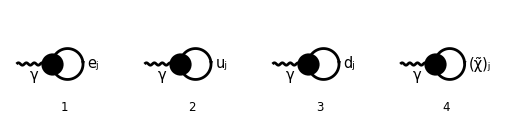

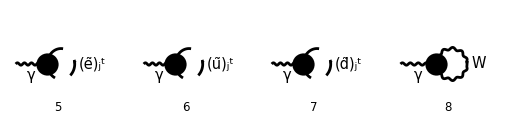

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,1->0],
{V[1]}->{},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1|2|3|4|5|6],U[1|2|3|4]}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

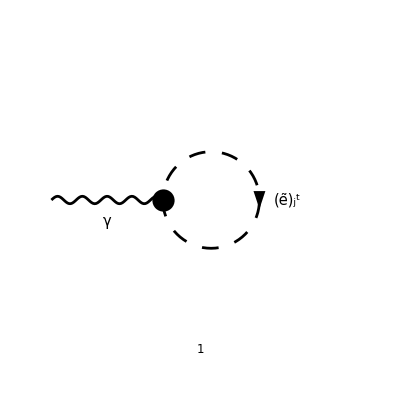

```mathematica
diags[1]=DiagramExtract[diags[0],5];
Paint[
diags[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
M[0]=FCFAConvert[
CreateFeynAmp[diags[1]],
IncomingMomenta->{p},
LoopMomenta->{k},
ChangeDimension->D,
UndoChiralSplittings->True,
List->False,
Contract->True,
DropSumOver->True,
SMP->True
]
```

-(ⅈ e (k·ε(p)))/(8 π^4 (k^2-m_l_Gen2Sfe2^2))

```mathematica
M[1]=M[0]//TID[#,k,ToPaVe->True]&
```

0

## 02.03

```mathematica
FVD[2k-p,μ]FVD[2k-p,ν]FAD[{k,m1},{k-p,m2}]
(%/(I Pi^2))//TID[#,k,ToPaVe->True]&//FCE//Collect2[#,{FVD[p,μ],FVD[p,ν],MTD[μ,ν]},Factoring->FullSimplify]&
%[[1]]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&
```

((2 k-p)^μ (2 k-p)^ν)/((k^2-m_1^2).((k-p)^2-m_2^2))

(g^μν (-(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) B_0(p^2,m_1^2,m_2^2)+(m_1^2-m_2^2+p^2) A_0(m_1^2)+(-m_1^2+m_2^2+p^2) A_0(m_2^2)))/((D-1) p^2)+(p^μ p^ν ((D (m_1^2-m_2^2)^2-2 (m_1^2+m_2^2) p^2+p^4) B_0(p^2,m_1^2,m_2^2)+A_0(m_2^2) (D (m_1-m_2) (m_1+m_2)+(D-2) p^2)+A_0(m_1^2) (D (m_2^2-m_1^2)+(D-2) p^2)))/((D-1) p^4)

(KK(1997))/(3 ε_UV)+(KK(2014))/18

```mathematica
KK[1997]//FRH
```

(3 (m_1^2+m_2^2)-p^2) g^μν

```mathematica
KK[2014]//FRH
```

1/p^4 g^μν (p^6 (-6 log((π μ^2)/m_2^2)+3 log(m_1^2/m_2^2)+6 ℽ-16-12 log(2))-3 p^4 (m_1^2 (-2 log(μ^2/m_1^2)-4 log(μ^2/m_2^2)+log(m_1^2/(4096 π^6 m_2^2))+6 ℽ-14)+m_2^2 (-6 log((π μ^2)/m_2^2)+3 log(m_1^2/m_2^2)+6 ℽ-14-12 log(2))+2 √(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) (log((√(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4)+m_1^2+m_2^2-p^2)/(m_1 m_2))-log(2)))+3 p^2 (-(m_1-m_2) (m_1+m_2) (2 m_1^2 (log(μ^2/m_2^2)-log(μ^2/m_1^2))+2 (m_1-m_2) (m_1+m_2)+(m_1^2+3 m_2^2) log(m_1^2/m_2^2))+4 m_1^2 √(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) log((√(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4)+m_1^2+m_2^2-p^2)/(2 m_1 m_2))+4 m_2^2 √(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) log((√(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4)+m_1^2+m_2^2-p^2)/(2 m_1 m_2)))+3 (m_1-m_2)^2 (m_1+m_2)^2 ((m_1-m_2) (m_1+m_2) log(m_1^2/m_2^2)-2 √(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) log((√(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4)+m_1^2+m_2^2-p^2)/(2 m_1 m_2))))

```mathematica
FVD[2k-p,μ]FVD[2k-p,ν]FAD[{k,m1},{k-p,m2}]
(%/(I Pi^2))//TID[#,k,ToPaVe->True]&//FCE//Collect2[#,{FVD[p,μ],FVD[p,ν],MTD[μ,ν]},Factoring->FullSimplify]&
%//ReplaceAll[#,{FVD[p,μ]->0}]&
%//PaXEvaluate
```

((2 k-p)^μ (2 k-p)^ν)/((k^2-m_1^2).((k-p)^2-m_2^2))

(g^μν (-(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) B_0(p^2,m_1^2,m_2^2)+(m_1^2-m_2^2+p^2) A_0(m_1^2)+(-m_1^2+m_2^2+p^2) A_0(m_2^2)))/((D-1) p^2)+(p^μ p^ν ((D (m_1^2-m_2^2)^2-2 (m_1^2+m_2^2) p^2+p^4) B_0(p^2,m_1^2,m_2^2)+A_0(m_2^2) (D (m_1-m_2) (m_1+m_2)+(D-2) p^2)+A_0(m_1^2) (D (m_2^2-m_1^2)+(D-2) p^2)))/((D-1) p^4)

(g^μν (-(-2 (m_1^2+m_2^2) p^2+(m_1^2-m_2^2)^2+p^4) B_0(p^2,m_1^2,m_2^2)+(m_1^2-m_2^2+p^2) A_0(m_1^2)+(-m_1^2+m_2^2+p^2) A_0(m_2^2)))/((D-1) p^2)

```mathematica
SPD[p]=0;
FVD[2k-p,μ]FVD[2k-p,ν]FAD[{k,m1},{k-p,m2}]
(%/(I Pi^2))//TID[#,k,ToPaVe->True]&//FCE//Collect2[#,{FVD[p,μ],FVD[p,ν],MTD[μ,ν]},Factoring->FullSimplify]&
%//ReplaceAll[#,{FVD[p,_]->0}]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

((2 k-p)^μ (2 k-p)^ν)/((k^2-m_1^2).((k-p)^2-m_2^2))

p^μ p^ν (B_0(0,m_1^2,m_2^2)+4 (B_1(0,m_1^2,m_2^2)+B_11(0,m_1^2,m_2^2)))+(2 g^μν (2 m_1^2 B_0(0,m_1^2,m_2^2)+(m_1-m_2) (m_1+m_2) B_1(0,m_1^2,m_2^2)+A_0(m_2^2)))/(D-1)

(2 g^μν (2 m_1^2 B_0(0,m_1^2,m_2^2)+(m_1-m_2) (m_1+m_2) B_1(0,m_1^2,m_2^2)+A_0(m_2^2)))/(D-1)

((m_1^2+m_2^2) g^μν)/ε_UV-(g^μν (-6 m_1^4 log(μ^2/m_2^2)+6 m_2^4 log(μ^2/m_2^2)+6 ℽ m_1^4-9 m_1^4-6 ℽ m_2^4+9 m_2^4+6 m_1^4 log(m_1^2/m_2^2)-6 m_1^4 log(π)-m_1^4 log(4096)+6 m_2^4 log(π)+m_2^4 log(4096)))/(6 (m_1-m_2) (m_1+m_2))

```mathematica
1/(-1+ϵ)//Series[#,{ϵ,0,1}]&
```

-1-ϵ+O(ϵ^2)

### Photon vacuum polarization

#### A-type

```mathematica
2I e^2 MTD[μ,ν]I FAD[{k,m}] /(2Pi)^4
%//TID[#,k,ToPaVe->True]&
Atype=%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

-(e^2 g^μν)/(8 π^4 (k^2-m^2))

-(ⅈ e^2 A_0(m^2) g^μν)/(8 π^2)

(ⅈ e^2 m^2 g^μν (-log(μ^2/m^2)+ℽ-1-log(4 π)))/(8 π^2)-(ⅈ e^2 m^2 g^μν)/(8 π^2 ε_UV)

#### B-type

```mathematica
FCClearScalarProducts[];
SPD[p]=s;
```

```mathematica
e^2/(2Pi)^4 FVD[2k-p,μ]FVD[2k-p,ν]FAD[{k,m1},{k-p,m2}]
%//TID[#,k,ToPaVe->True]&
%//FCE//ReplaceAll[#,{FVD[p,_]->0}]&
Btype=%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

(e^2 (2 k-p)^μ (2 k-p)^ν)/(16 π^4 (k^2-m_1^2).((k-p)^2-m_2^2))

-(ⅈ e^2 B_0(s,m_1^2,m_2^2) (D (m_1^2-m_2^2+s)^2 p^μ p^ν+2 (1-D) s (m_1^2-m_2^2+s) p^μ p^ν-(1-D) s^2 p^μ p^ν+4 m_1^2 s^2 g^μν-s (m_1^2-m_2^2+s)^2 g^μν-4 m_1^2 s p^μ p^ν))/(16 π^2 (1-D) s^2)-(ⅈ e^2 A_0(m_1^2) (-D (m_1^2-m_2^2+s) p^μ p^ν-2 (1-D) s p^μ p^ν+s (m_1^2-m_2^2+s) g^μν))/(16 π^2 (1-D) s^2)-(ⅈ e^2 A_0(m_2^2) (D (m_1^2-m_2^2+3 s) p^μ p^ν+2 (1-D) s p^μ p^ν-s (m_1^2-m_2^2+3 s) g^μν+4 s^2 g^μν-4 s p^μ p^ν))/(16 π^2 (1-D) s^2)

-(ⅈ e^2 B_0(s,m_1^2,m_2^2) (4 m_1^2 s^2 g^μν-s (m_1^2-m_2^2+s)^2 g^μν))/(16 π^2 (1-D) s^2)-(ⅈ e^2 A_0(m_2^2) (4 s^2 g^μν-s (m_1^2-m_2^2+3 s) g^μν))/(16 π^2 (1-D) s^2)-(ⅈ e^2 (m_1^2-m_2^2+s) A_0(m_1^2) g^μν)/(16 π^2 (1-D) s)

(ⅈ (3 m_1^2+3 m_2^2-s) g^μν e^2)/(48 ε_UV π^2)+1/(288 π^2 s^2)ⅈ (3 log(m_1^2/m_2^2) m_1^6-6 s m_1^4-9 m_2^2 log(m_1^2/m_2^2) m_1^4-3 s log(m_1^2/m_2^2) m_1^4-6 √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2)) m_1^4+6 s log(μ^2/m_1^2) m_1^4-6 s log(μ^2/m_2^2) m_1^4-18 ℽ s^2 m_1^2+42 s^2 m_1^2+12 m_2^2 s m_1^2+9 m_2^4 log(m_1^2/m_2^2) m_1^2-3 s^2 log(m_1^2/m_2^2) m_1^2-6 m_2^2 s log(m_1^2/m_2^2) m_1^2+12 m_2^2 √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2)) m_1^2+12 s √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2)) m_1^2+6 s^2 log(μ^2/m_1^2) m_1^2-6 m_2^2 s log(μ^2/m_1^2) m_1^2+12 s^2 log(μ^2/m_2^2) m_1^2+6 m_2^2 s log(μ^2/m_2^2) m_1^2+36 s^2 log(2 π) m_1^2-18 s^2 log(π) m_1^2+6 ℽ s^3-16 s^3-18 ℽ m_2^2 s^2+42 m_2^2 s^2-6 m_2^4 s-3 m_2^6 log(m_1^2/m_2^2)+3 s^3 log(m_1^2/m_2^2)-9 m_2^2 s^2 log(m_1^2/m_2^2)+9 m_2^4 s log(m_1^2/m_2^2)-6 m_2^4 √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2))-6 s^2 √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2))+12 m_2^2 s √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2))-6 s^3 log(μ^2/m_2^2)+18 m_2^2 s^2 log(μ^2/m_2^2)-12 s^3 log(2 π)+36 m_2^2 s^2 log(2 π)+6 s^3 log(π)-18 m_2^2 s^2 log(π)) g^μν e^2

```mathematica
Atype+Btype//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&
```

1/288 ⅈ KK(5676)-(ⅈ KK(5656))/(48 ε_UV)

```mathematica
KK[5656]//FRH
```

(e^2 (6 m^2-3 (m_1^2+m_2^2)+s) g^μν)/π^2

#### On-Shell

```mathematica
e^2/(2Pi)^4 FVD[2k-p,μ]FVD[2k-p,ν]FAD[{k,m},{k-p,m}]
%//TID[#,k,ToPaVe->True]&
%//FCE//ReplaceAll[#,{FVD[p,_]->0}]&
BtypeONSHELL=%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

(e^2 (2 k-p)^μ (2 k-p)^ν)/(16 π^4 (k^2-m^2).((k-p)^2-m^2))

(ⅈ e^2 g^μν (-(m^2 B_0(0,m^2,m^2))/(1-D)-(A_0(m^2))/(2 (1-D))))/(4 π^2)+(ⅈ e^2 p^μ p^ν B_0(0,m^2,m^2))/(48 π^2)

(ⅈ e^2 g^μν (-(m^2 B_0(0,m^2,m^2))/(1-D)-(A_0(m^2))/(2 (1-D))))/(4 π^2)

(ⅈ e^2 m^2 g^μν)/(8 π^2 ε_UV)-(ⅈ e^2 m^2 g^μν (-log(μ^2/m^2)+ℽ-1-log(4 π)))/(8 π^2)

```mathematica
Atype
BtypeONSHELL
```

(ⅈ e^2 m^2 g^μν (-log(μ^2/m^2)+ℽ-1-log(4 π)))/(8 π^2)-(ⅈ e^2 m^2 g^μν)/(8 π^2 ε_UV)

(ⅈ e^2 (m_1^2+m_2^2) g^μν)/(16 π^2 ε_UV)-(ⅈ e^2 g^μν (-6 m_1^4 log(μ^2/m_2^2)+6 m_2^4 log(μ^2/m_2^2)+6 ℽ m_1^4-9 m_1^4-6 ℽ m_2^4+9 m_2^4+6 m_1^4 log(m_1^2/m_2^2)-6 m_1^4 log(π)-m_1^4 log(4096)+6 m_2^4 log(π)+m_2^4 log(4096)))/(96 π^2 (m_1-m_2) (m_1+m_2))

```mathematica
Atype+BtypeONSHELL//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&
```

(ⅈ e^2 g^μν ((m_1-m_2) (m_1+m_2) (-4 m^2 log((4 π μ^2)/m^2)+4 (ℽ-1) m^2-(m_1^2+m_2^2) (-3+2 ℽ-4 log(2)))+2 (m_1^4-m_2^4) log((π μ^2)/m_2^2)-2 m_1^4 log(m_1^2/m_2^2)))/(32 π^2 (m_1-m_2) (m_1+m_2))-(ⅈ e^2 (2 m^2-m_1^2-m_2^2) g^μν)/(16 π^2 ε_UV)

```mathematica
Btype
```

(ⅈ e^2 (m_1^2+m_2^2) g^μν)/(16 π^2 ε_UV)-(ⅈ e^2 g^μν (-6 m_1^4 log(μ^2/m_2^2)+6 m_2^4 log(μ^2/m_2^2)+6 ℽ m_1^4-9 m_1^4-6 ℽ m_2^4+9 m_2^4+6 m_1^4 log(m_1^2/m_2^2)-6 m_1^4 log(π)-m_1^4 log(4096)+6 m_2^4 log(π)+m_2^4 log(4096)))/(96 π^2 (m_1-m_2) (m_1+m_2))

```mathematica
Btype-BtypeONSHELL
```

0

```mathematica
Btype//Limit[#,s->0,Assumptions->m1∈PositiveReals&&m2∈PositiveReals&&e∈PositiveReals]&
```

(ⅈ ((m_1^2-m_2^2) log(m_1^2/m_2^2)+2 Abs[m_1^2-m_2^2] log((2 m_1 m_2)/(m_1^2+m_2^2+Abs[m_1^2-m_2^2]))) g^μν) ∞

```mathematica
a Log[a]//Limit[#,a->0]&
```

0

```mathematica
A0[0]
```

0

```mathematica
A0[m^2]//PaXEvaluateUVIRSplit
%//Limit[#,m->0]&
```

m^2/ε_UV-m^2 (-log(μ^2/(π m^2))+ℽ-1)

0

## 03.03

### On-shell vertex correction

#### Triangle

```mathematica
FCClearScalarProducts[];
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1,k2]=1/2(SPD[p]-m1^2-m2^2);
SPD[p,k1]=1/2(SPD[p]+m1^2-m2^2);
SPD[p,k2]=1/2(SPD[p]+m2^2-m1^2);
SPD[p]=0(*on-shell condition*);
```

```mathematica
triangle[0]=SMP["e"]^2/(8Pi^2)1/(I Pi^2)(FVD[k,μ]+1/2FVD[p,μ])SPD[k-k1,k+p+k2]FAD[{k,m1},k+k1,{k+p,m2}]
triangle[1]=triangle[0]//FCE//ReplaceAll[#,{FVD[p,_]->0}]&
triangle[2]=triangle[1]//TID[#,k,ToPaVe->True]&//Simplify
triangle[3]=triangle[2]//FCE//ReplaceAll[#,{
FVD[k1,μ]->1/2(FVD[p,μ]-FVD[K,μ]),
FVD[k2,μ]->1/2(FVD[p,μ]+FVD[K,μ])
}]&//ReplaceAll[#,{FVD[p,μ]->0}]&//FullSimplify
```

-(ⅈ e^2 (k^μ+p^μ/2) ((k-k_1)·(k+k_2+p)))/(8 π^4 (k^2-m_1^2).(k+k_1)^2.((k+p)^2-m_2^2))

-(ⅈ e^2 k^μ ((k-k_1)·(k+k_2+p)))/(8 π^4 (k^2-m_1^2).(k+k_1)^2.((k+p)^2-m_2^2))

-1/(16 π^2 (D-2) m_1^2 m_2^2 (m_1^2-m_2^2)^2)e^2 (m_1^2 (m_2^2 (2 (D-2) ((m_1^2-m_2^2)^2 (2 (m_1^2+m_2^2) k_1^μ C_0(0,m_1^2,m_2^2,m_2^2,m_1^2,0)+p^μ B_1(0,m_1^2,m_2^2))+B_0(m_1^2,0,m_1^2) (4 m_1^2 (m_1^2+m_2^2) p^μ-(m_1^4+2 m_2^2 m_1^2-3 m_2^4) k_1^μ)+B_0(m_2^2,0,m_2^2) ((3 m_1^4-2 m_2^2 m_1^2-m_2^4) k_1^μ-2 (m_1^2+m_2^2)^2 p^μ))-(m_1^2-m_2^2) B_0(0,m_1^2,m_2^2) (D (m_1^2-m_2^2) k_1^μ+2 ((D-3) m_1^2+(2 D-3) m_2^2) p^μ+2 (m_1^2-m_2^2) k_2^μ))+A_0(m_2^2) (-((m_1^2-m_2^2) ((D-2) m_1^2+m_2^2) k_1^μ)+((D-2) m_1^4+(D-3) m_2^4+m_2^2 m_1^2) p^μ+(m_2^4-m_1^2 m_2^2) k_2^μ))+m_2^2 A_0(m_1^2) ((m_1^2-m_2^2) ((D-2) m_2^2+m_1^2) k_1^μ+m_1^2 (((3-2 D) m_1^2+m_2^2) p^μ+(m_1^2-m_2^2) k_2^μ)))

(e^2 K^μ (m_2^2 m_1^2 ((m_2^2-m_1^2) B_0(0,m_1^2,m_2^2)-2 (m_1^2+3 m_2^2) B_0(m_1^2,0,m_1^2)+2 (3 m_1^2+m_2^2) B_0(m_2^2,0,m_2^2)+4 (m_1^4-m_2^4) C_0(0,m_1^2,m_2^2,m_2^2,m_1^2,0))+m_1^4 (-A_0(m_2^2))+m_2^4 A_0(m_1^2)))/(32 π^2 m_1^2 (m_1-m_2) m_2^2 (m_1+m_2))

```mathematica
triangle[4]=triangle[3]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FullSimplify//FCE
triangle[5]=((triangle[4]/FVD[K,μ])//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&)FVD[K,μ]
```

(e^2 K^μ (log(m_1^2/m_2^2) ε_UV (2 (m_1^2+m_2^2) ε_IR log((4 π μ^2)/m_2^2)+m_1^2 (-2 ℽ ε_IR+ε_IR+2)-2 m_2^2 (ℽ ε_IR-1))+ε_IR (-(2 m_1^2+5 m_2^2) ε_UV log(μ^2/m_1^2)+(4 m_1^2+3 m_2^2) ε_UV log(μ^2/m_2^2)-2 (m_1-m_2) (m_1+m_2) ((-3+ℽ-log(4 π)) ε_UV-1))+(m_1^2+m_2^2) (-ε_IR) log^2(m_1^2/m_2^2) ε_UV))/(32 π^2 (m_1-m_2) (m_1+m_2) ε_IR ε_UV)

K^μ ((KK(6066))/(16 ε_IR)+(KK(6067))/(16 ε_UV)-(KK(6068))/32)

#### Bubbles

```mathematica
bubbles[0]=SMP["e"]^2/(8Pi^2)1/(I Pi^2)(-(FVD[k,μ]-FVD[k1,μ])FAD[{k,m1},k+k1]+(FVD[k,μ]-FVD[k2,μ])FAD[{k,m2},k+k2])
bubbles[1]=bubbles[0]//TID[#,k,ToPaVe->True]&//Simplify
bubbles[2]=bubbles[1]//FCE//ReplaceAll[#,{
FVD[k1,μ]->1/2(FVD[p,μ]-FVD[K,μ]),
FVD[k2,μ]->1/2(FVD[p,μ]+FVD[K,μ])
}]&//ReplaceAll[#,{FVD[p,μ]->0}]&//FullSimplify
```

-(ⅈ e^2 ((k_1^μ-k^μ)/((k^2-m_1^2).(k+k_1)^2)+(k^μ-k_2^μ)/((k^2-m_2^2).(k+k_2)^2)))/(8 π^4)

(e^2 (m_1^2 (k_2^μ (A_0(m_2^2)-4 m_2^2 B_0(m_2^2,0,m_2^2))+4 m_2^2 k_1^μ B_0(m_1^2,0,m_1^2))-m_2^2 k_1^μ A_0(m_1^2)))/(16 π^2 m_1^2 m_2^2)

(e^2 K^μ (m_1^2 (A_0(m_2^2)-4 m_2^2 (B_0(m_1^2,0,m_1^2)+B_0(m_2^2,0,m_2^2)))+m_2^2 A_0(m_1^2)))/(32 π^2 m_1^2 m_2^2)

```mathematica
bubbles[3]=bubbles[2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FCE
bubbles[4]=((bubbles[3]/FVD[K,μ])//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&)FVD[K,μ]
```

(e^2 K^μ (-3 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+6 ℽ-14-6 log(4 π)))/(32 π^2)-(3 e^2 K^μ)/(16 π^2 ε_UV)

K^μ ((KK(6203))/32-(3 KK(6067))/(16 ε_UV))

#### Results

```mathematica
triangle[5]
KK[6066]//FRH
KK[6067]//FRH
KK[6068]//FRH
```

K^μ ((KK(6066))/(16 ε_IR)+(KK(6067))/(16 ε_UV)-(KK(6068))/32)

(e^2 (m_1^2+m_2^2) log(m_1^2/m_2^2))/(π^2 (m_1-m_2) (m_1+m_2))

e^2/π^2

(e^2 (log(m_1^2/m_2^2) (-2 (m_1^2+m_2^2) log((4 π μ^2)/m_2^2)+(2 ℽ-1) m_1^2+2 ℽ m_2^2)+(2 m_1^2+5 m_2^2) log(μ^2/m_1^2)-(4 m_1^2+3 m_2^2) log(μ^2/m_2^2)+(m_1^2+m_2^2) log^2(m_1^2/m_2^2)+2 (m_1-m_2) (m_1+m_2) (-3+ℽ-log(4 π))))/(π^2 (m_1-m_2) (m_1+m_2))

```mathematica
bubbles[4]
KK[6203]//FRH
KK[6067]//FRH
```

K^μ ((KK(6203))/32-(3 KK(6067))/(16 ε_UV))

(e^2 (-3 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+6 ℽ-14-6 log(4 π)))/π^2

e^2/π^2

### On-shell scheme but for massive Z-boson

```mathematica
FCClearScalarProducts[];
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1,k2]=1/2(SPD[p]-m1^2-m2^2);
SPD[p,k1]=1/2(SPD[p]+m1^2-m2^2);
SPD[p,k2]=1/2(SPD[p]+m2^2-m1^2);
SPD[p]=SMP["m_Z"]^2(*on-shell condition*);
```

```mathematica
triangle[0]=SMP["e"]^2/(8Pi^2)1/(I Pi^2)(FVD[k,μ]+1/2FVD[p,μ])SPD[k-k1,k+p+k2]FAD[{k,m1},k+k1,{k+p,m2}]
triangle[1]=triangle[0]//FCE//ReplaceAll[#,{FVD[p,_]->0}]&
triangle[2]=triangle[1]//TID[#,k,ToPaVe->True]&//Simplify
triangle[3]=triangle[2]//FCE//ReplaceAll[#,{
FVD[k1,μ]->1/2(FVD[p,μ]-FVD[K,μ]),
FVD[k2,μ]->1/2(FVD[p,μ]+FVD[K,μ])
}]&//ReplaceAll[#,{FVD[p,μ]->0}]&//FullSimplify
```

-(ⅈ e^2 (k^μ+p^μ/2) ((k-k_1)·(k+k_2+p)))/(8 π^4 (k^2-m_1^2).(k+k_1)^2.((k+p)^2-m_2^2))

-(ⅈ e^2 k^μ ((k-k_1)·(k+k_2+p)))/(8 π^4 (k^2-m_1^2).(k+k_1)^2.((k+p)^2-m_2^2))

1/(16 π^2 m_Z^2)e^2 (1/((D-2) (m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))(2 (D-2) m_Z^2 (B_0(m_2^2,0,m_2^2) (k_1^μ (-3 m_Z^4+2 (3 m_1^2+m_2^2) m_Z^2-3 m_1^4+2 m_2^2 m_1^2+m_2^4)+2 (-m_Z^2+m_1^2+m_2^2)^2 p^μ)+B_0(m_1^2,0,m_1^2) (k_1^μ (-3 m_Z^4+2 (m_1^2+3 m_2^2) m_Z^2+m_1^4+2 m_2^2 m_1^2-3 m_2^4)-4 m_1^2 (-m_Z^2+m_1^2+m_2^2) p^μ)+2 k_1^μ (m_Z^6-3 (m_1^2+m_2^2) m_Z^4+(3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) m_Z^2-(m_1^2-m_2^2)^2 (m_1^2+m_2^2)) C_0(m_1^2,m_2^2,m_Z^2,m_1^2,0,m_2^2))+B_0(m_Z^2,m_1^2,m_2^2) (m_Z^2 (k_1^μ ((8 D-15) m_Z^4-2 (4 D-7) (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)+k_2^μ (m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))+p^μ ((5-3 D) m_Z^6+((5 D-8) m_2^2-(D-4) m_1^2) m_Z^4+(m_1^2-m_2^2) ((3 D-7) m_1^2+(D-1) m_2^2) m_Z^2+(D-2) (m_1^2-m_2^2)^3)))+A_0(m_1^2) ((k_1^μ m_Z^2)/m_1^2-p^μ)+(A_0(m_2^2) (k_1^μ m_Z^2+(m_2^2-m_Z^2) p^μ))/m_2^2)

(e^2 K^μ (-(2 (-2 (-m_Z^2+m_1^2+m_2^2) (2 m_Z^2 B_0(m_Z^2,m_1^2,m_2^2)+(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2) C_0(m_1^2,m_2^2,m_Z^2,m_1^2,0,m_2^2))+(-3 m_Z^4+2 (3 m_1^2+m_2^2) m_Z^2-3 m_1^4+2 m_2^2 m_1^2+m_2^4) B_0(m_2^2,0,m_2^2)+(-3 m_Z^4+2 (m_1^2+3 m_2^2) m_Z^2+m_1^4+2 m_2^2 m_1^2-3 m_2^4) B_0(m_1^2,0,m_1^2)))/(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)-(A_0(m_1^2))/m_1^2-(A_0(m_2^2))/m_2^2))/(32 π^2)

```mathematica
triangle[4]=triangle[3]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FullSimplify//FCE
triangle[5]=((triangle[4]/FVD[K,μ])//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->Simplify,IsolateNames->KK]&)FVD[K,μ]
```

PaXEvaluate::C0D0: The explicit result for the occurring C0 function(s) is expected to be very complicated. Please rerun PaXEvaluate with the option PaXC0Expand->True to show the result nevertheless. Please set $FCAdvice=False if you do not want to see this message in future.

-((K^μ e^2 (2 ε_UV ((log((16 m_1^2)/m_2^2) ε_IR+2 log((π μ^2)/m_1^2) ε_IR-2 ℽ ε_IR+4 ε_IR+2) (log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))-log(2))+2 ε_IR X`ScalarC0IR6(m_Z^2,m_1,m_2) √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)) m_Z^6+(ε_IR √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2) (-4 log((2 m_1^2)/m_2^2) ε_UV-5 log(μ^2/m_1^2) ε_UV+3 log(μ^2/m_2^2) ε_UV+2 (-3+ℽ-log(π)) ε_UV-2)+6 ε_UV (m_1^2+m_2^2) (log((16 m_1^2)/m_2^2) ε_IR+2 log((π μ^2)/m_1^2) ε_IR-2 ℽ ε_IR+4 ε_IR+2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2)))-12 ε_IR ε_UV (m_1^2+m_2^2) X`ScalarC0IR6(m_Z^2,m_1,m_2) √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)) m_Z^4+2 (ε_IR √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2) (ε_UV log(16) m_2^2-2 (ε_UV (-3+ℽ)-1) (m_1^2+m_2^2)+ε_UV ((log(μ^2/m_2^2)+log((16 π^2 μ^2)/m_1^2)) m_1^2+m_2^2 (4 log(m_1^2/m_2^2)+5 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+2 log(π))))+ε_UV (3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) (-((log(m_1^2/m_2^2)+2 log((4 π μ^2)/m_1^2)) ε_IR)+2 (-2+ℽ) ε_IR-2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2)))+2 ε_IR ε_UV (3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) X`ScalarC0IR6(m_Z^2,m_1,m_2) √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)) m_Z^2+(m_1-m_2) (m_1+m_2) (ε_IR √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2) (4 ε_UV (m_1^2+m_2^2) log(m_1^2/m_2^2)+(m_1-m_2) (m_1+m_2) (ε_UV (-6+2 ℽ+log(1/(16 π^2)))-2)+ε_UV (3 m_1^2+5 m_2^2) log(μ^2/m_1^2)-ε_UV (5 m_1^2+3 m_2^2) log(μ^2/m_2^2))+2 ε_UV (m_1^4-m_2^4) (log((16 m_1^2)/m_2^2) ε_IR+2 log((π μ^2)/m_1^2) ε_IR-2 ℽ ε_IR+4 ε_IR+2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2)))+4 ε_IR ε_UV (m_2^4-m_1^4) X`ScalarC0IR6(m_Z^2,m_1,m_2) √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))))/(32 ε_IR ε_UV π^2 (m_1-m_2-m_Z) (m_1+m_2-m_Z) (m_1-m_2+m_Z) (m_1+m_2+m_Z) √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)))

K^μ (-(KK(7259))/(8 ε_IR)+(KK(6067))/(16 ε_UV)+(KK(7276))/32)

```mathematica
bubbles[0]=SMP["e"]^2/(8Pi^2)1/(I Pi^2)(-(FVD[k,μ]-FVD[k1,μ])FAD[{k,m1},k+k1]+(FVD[k,μ]-FVD[k2,μ])FAD[{k,m2},k+k2])
bubbles[1]=bubbles[0]//TID[#,k,ToPaVe->True]&//Simplify
bubbles[2]=bubbles[1]//FCE//ReplaceAll[#,{
FVD[k1,μ]->1/2(FVD[p,μ]-FVD[K,μ]),
FVD[k2,μ]->1/2(FVD[p,μ]+FVD[K,μ])
}]&//ReplaceAll[#,{FVD[p,μ]->0}]&//FullSimplify
```

-(ⅈ e^2 ((k_1^μ-k^μ)/((k^2-m_1^2).(k+k_1)^2)+(k^μ-k_2^μ)/((k^2-m_2^2).(k+k_2)^2)))/(8 π^4)

(e^2 (m_1^2 (k_2^μ (A_0(m_2^2)-4 m_2^2 B_0(m_2^2,0,m_2^2))+4 m_2^2 k_1^μ B_0(m_1^2,0,m_1^2))-m_2^2 k_1^μ A_0(m_1^2)))/(16 π^2 m_1^2 m_2^2)

(e^2 K^μ (m_1^2 (A_0(m_2^2)-4 m_2^2 (B_0(m_1^2,0,m_1^2)+B_0(m_2^2,0,m_2^2)))+m_2^2 A_0(m_1^2)))/(32 π^2 m_1^2 m_2^2)

```mathematica
bubbles[3]=bubbles[2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FCE
bubbles[4]=((bubbles[3]/FVD[K,μ])//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&)FVD[K,μ]
```

(e^2 K^μ (-3 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+6 ℽ-14-6 log(4 π)))/(32 π^2)-(3 e^2 K^μ)/(16 π^2 ε_UV)

K^μ ((KK(6203))/32-(3 KK(6067))/(16 ε_UV))

#### Results

```mathematica
triangle[5]
KK[7259]//FRH
KK[6067]//FRH
KK[7276]//FRH
```

K^μ (-(KK(7259))/(8 ε_IR)+(KK(6067))/(16 ε_UV)+(KK(7276))/32)

(e^2 (-m_Z^2+m_1^2+m_2^2) (log(2)-log((-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2)+m_1^2+m_2^2)/(m_1 m_2))))/(π^2 √(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))

e^2/π^2

(e^2 (-4 X`ScalarC0IR6(m_Z^2,m_1,m_2) m_Z^6+(2 log((16 m_1^2)/m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^6)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))+(4 log((π μ^2)/m_1^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^6)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(4 ℽ (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^6)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))+(8 (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^6)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))+4 log((2 m_1^2)/m_2^2) m_Z^4+5 log(μ^2/m_1^2) m_Z^4-3 log(μ^2/m_2^2) m_Z^4+12 (m_1^2+m_2^2) X`ScalarC0IR6(m_Z^2,m_1,m_2) m_Z^4+(12 ℽ (m_1^2+m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^4)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(24 (m_1^2+m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^4)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(6 (m_1^2+m_2^2) log((16 m_1^2)/m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^4)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(12 (m_1^2+m_2^2) log((π μ^2)/m_1^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^4)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-2 (-3+ℽ-log(π)) m_Z^4+4 (-3+ℽ) (m_1^2+m_2^2) m_Z^2-2 ((log(μ^2/m_2^2)+log((16 π^2 μ^2)/m_1^2)) m_1^2+m_2^2 (4 log(m_1^2/m_2^2)+5 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+2 log(π))) m_Z^2-4 (3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) X`ScalarC0IR6(m_Z^2,m_1,m_2) m_Z^2-(4 (-2+ℽ) (3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^2)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))+(2 (3 m_1^4+2 m_2^2 m_1^2+3 m_2^4) (log(m_1^2/m_2^2)+2 log((4 π μ^2)/m_1^2)) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))) m_Z^2)/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-2 m_2^2 log(16) m_Z^2-4 (m_1-m_2) (m_1+m_2) (m_1^2+m_2^2) log(m_1^2/m_2^2)-(m_1-m_2) (m_1+m_2) (3 m_1^2+5 m_2^2) log(μ^2/m_1^2)+(m_1-m_2) (m_1+m_2) (5 m_1^2+3 m_2^2) log(μ^2/m_2^2)+4 (m_1-m_2) (m_1+m_2) (m_1^4-m_2^4) X`ScalarC0IR6(m_Z^2,m_1,m_2)+(4 ℽ (m_1-m_2)^2 (m_1+m_2)^2 (m_1^2+m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))))/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(8 (m_1-m_2)^2 (m_1+m_2)^2 (m_1^2+m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))))/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(2 (m_1-m_2)^2 (m_1+m_2)^2 (m_1^2+m_2^2) log((16 m_1^2)/m_2^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))))/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(4 (m_1-m_2)^2 (m_1+m_2)^2 (m_1^2+m_2^2) log((π μ^2)/m_1^2) (log(2)-log((m_1^2+m_2^2-m_Z^2+√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))/(m_1 m_2))))/(√(m_Z^4-2 (m_1^2+m_2^2) m_Z^2+(m_1^2-m_2^2)^2))-(m_1-m_2)^2 (m_1+m_2)^2 (-6+2 ℽ+log(1/(16 π^2)))))/(π^2 (m_1-m_2-m_Z) (m_1+m_2-m_Z) (m_1-m_2+m_Z) (m_1+m_2+m_Z))

```mathematica
bubbles[4]
KK[6203]//FRH
KK[6067]//FRH
```

K^μ ((KK(6203))/32-(3 KK(6067))/(16 ε_UV))

(e^2 (-3 log(μ^2/m_1^2)-3 log(μ^2/m_2^2)+6 ℽ-14-6 log(4 π)))/π^2

e^2/π^2

## Make sure 4-slepton coupling doesn’t contribute

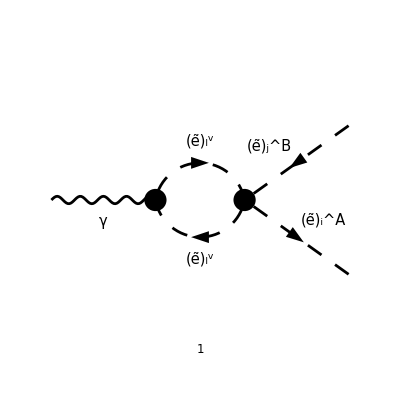

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,1->2,
ExcludeTopologies->{SelfEnergies,Tadpoles}],
{V[1]}->{-S[12,{B,j}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{V[1|2|3],S[1|2|3|4|5|6|13|14],F[11|12]}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
M[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
ChangeDimension->D,
Contract->False,
LorentzIndexNames->{μ,ν},
List->False,
SMP->True,
DropSumOver->True
]
```

(ⅈ e^3 (-2 k+k_1+k_2)^μ ε^μ(p) (2 Conjugate[(USf(2,j)(B,2))] (IndexDelta(i,Gen4) IndexDelta(j,Gen4) Conjugate[(USf(2,i)(Sfe4,1))] (MLE(i) MLE(j) (cos(θ_W))^2 USf(2,i)(A,2) USf(2,j)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,1) USf(2,j)(Sfe4,2))+IndexDelta(i,j) (Conjugate[(USf(2,Gen4)(Sfe4,1))] (MLE(j) (cos(θ_W))^2 MLE(Gen4) USf(2,j)(A,1) USf(2,Gen4)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,2) USf(2,Gen4)(Sfe4,1))+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,2) USf(2,Gen4)(Sfe4,2) Conjugate[(USf(2,Gen4)(Sfe4,2))])+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) IndexDelta(i,Gen4) IndexDelta(j,Gen4) USf(2,j)(Sfe4,2) Conjugate[(USf(2,i)(Sfe4,2))])+Conjugate[(USf(2,j)(B,1))] (2 IndexDelta(i,Gen4) IndexDelta(j,Gen4) Conjugate[(USf(2,i)(Sfe4,2))] (MLE(i) MLE(j) (cos(θ_W))^2 USf(2,i)(A,1) USf(2,j)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,j)(Sfe4,1))+IndexDelta(i,j) (2 Conjugate[(USf(2,Gen4)(Sfe4,2))] (MLE(j) (cos(θ_W))^2 MLE(Gen4) USf(2,j)(A,2) USf(2,Gen4)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,1) USf(2,Gen4)(Sfe4,2))+CB^2 m_W^2 USf(2,j)(A,1) USf(2,Gen4)(Sfe4,1) Conjugate[(USf(2,Gen4)(Sfe4,1))])+CB^2 m_W^2 USf(2,i)(A,1) IndexDelta(i,Gen4) IndexDelta(j,Gen4) USf(2,j)(Sfe4,1) Conjugate[(USf(2,i)(Sfe4,1))])))/(64 π^4 CB^2 m_W^2 (cos(θ_W))^2 (sin(θ_W))^2 (k^2-m_l_Gen4Sfe4^2).((k-k_1-k_2)^2-m_l_Gen4Sfe4^2))

```mathematica
M[1]=M[0]/ChangeDimension[PolarizationVector[p,μ],D](*Remove polarization vector*)
```

(ⅈ e^3 (-2 k+k_1+k_2)^μ (2 Conjugate[(USf(2,j)(B,2))] (IndexDelta(i,Gen4) IndexDelta(j,Gen4) Conjugate[(USf(2,i)(Sfe4,1))] (MLE(i) MLE(j) (cos(θ_W))^2 USf(2,i)(A,2) USf(2,j)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,1) USf(2,j)(Sfe4,2))+IndexDelta(i,j) (Conjugate[(USf(2,Gen4)(Sfe4,1))] (MLE(j) (cos(θ_W))^2 MLE(Gen4) USf(2,j)(A,1) USf(2,Gen4)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,2) USf(2,Gen4)(Sfe4,1))+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,2) USf(2,Gen4)(Sfe4,2) Conjugate[(USf(2,Gen4)(Sfe4,2))])+2 CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) IndexDelta(i,Gen4) IndexDelta(j,Gen4) USf(2,j)(Sfe4,2) Conjugate[(USf(2,i)(Sfe4,2))])+Conjugate[(USf(2,j)(B,1))] (2 IndexDelta(i,Gen4) IndexDelta(j,Gen4) Conjugate[(USf(2,i)(Sfe4,2))] (MLE(i) MLE(j) (cos(θ_W))^2 USf(2,i)(A,1) USf(2,j)(Sfe4,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,j)(Sfe4,1))+IndexDelta(i,j) (2 Conjugate[(USf(2,Gen4)(Sfe4,2))] (MLE(j) (cos(θ_W))^2 MLE(Gen4) USf(2,j)(A,2) USf(2,Gen4)(Sfe4,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,j)(A,1) USf(2,Gen4)(Sfe4,2))+CB^2 m_W^2 USf(2,j)(A,1) USf(2,Gen4)(Sfe4,1) Conjugate[(USf(2,Gen4)(Sfe4,1))])+CB^2 m_W^2 USf(2,i)(A,1) IndexDelta(i,Gen4) IndexDelta(j,Gen4) USf(2,j)(Sfe4,1) Conjugate[(USf(2,i)(Sfe4,1))])))/(64 π^4 CB^2 m_W^2 (cos(θ_W))^2 (sin(θ_W))^2 (k^2-m_l_Gen4Sfe4^2).((k-k_1-k_2)^2-m_l_Gen4Sfe4^2))

```mathematica
M[2]=M[1]//FCE//Collect2[#,{FVD[_,μ],FAD[__]},Factoring->FullSimplify,IsolateNames->KK]&
```

(ⅈ KK(670) (-2 k+k_1+k_2)^μ)/(64 (k^2-m_l_Gen4Sfe4^2).((k-k_1-k_2)^2-m_l_Gen4Sfe4^2))

```mathematica
M[3]=M[2]//ReplaceAll[#,{k1+k2->p,-k1-k2->-p}]&
```

(ⅈ KK(670) (p-2 k)^μ)/(64 (k^2-m_l_Gen4Sfe4^2).((k-p)^2-m_l_Gen4Sfe4^2))

```mathematica
M[4]=M[3]//TID[#,k,UsePaVeBasis->True]&
```

1/64 π^2 KK(670) p^μ B_0(p^2,m_l_Gen4Sfe4^2,m_l_Gen4Sfe4^2)+(ⅈ KK(670) p^μ)/(64 (k^2-m_l_Gen4Sfe4^2).((k-p)^2-m_l_Gen4Sfe4^2))

Proportional to p^μ as expected

## Finite integrations for radiation

```mathematica
$Assumptions={
xm∈Reals,
xp∈Reals,
-1<xm<xp<1,
λ∈PositiveReals
};
```

```mathematica
xpmRules={
xm->-(β1-β2)-Sqrt[λ],
xp->-(β1-β2)+Sqrt[λ]
};
fromλRules={
λ->1+β1^2+β2^2-2(β1+β2)-2β1 β2
};
toλRules={
β1^2-2(β2+1)β1+(β2-1)^2->λ,
(β1-1)^2+β2^2-2(β1+1)β2->λ
};
logRules={
-((-1+β1+β2+Sqrt[λ])/(1-β1-β2+Sqrt[λ]))->(Sqrt[λ]-1+β1+β2)^2/(4β1 β2),
(-β1+β2-Sqrt[λ]+1)/(-β1+β2+Sqrt[λ]+1)->(β1-β2+Sqrt[λ]-1)^2/(4β2),
(β1-β2-Sqrt[λ]+1)/(β1-β2+Sqrt[λ]+1)->(Sqrt[λ]-1-β1+β2)^2/(4β1),
(β1-β2+Sqrt[λ]+1)/(β1-β2-Sqrt[λ]+1)->4β1/(-β1+β2+Sqrt[λ]-1)^2,
(-β1+β2+Sqrt[λ]+1)/(-β1+β2-Sqrt[λ]+1)->4β2/(β1-β2+Sqrt[λ]-1)^2,
(β1+β2-Sqrt[λ]-1)/(β1+β2+Sqrt[λ]-1)->(β1+β2-Sqrt[λ]-1)^2/(4β1 β2)
};
```

```mathematica
(* Proof of logRules (remove semicolons) *)
-((-1+β1+β2+Sqrt[λ])/(1-β1-β2+Sqrt[λ]));
((%//Numerator)(-β1-β2-Sqrt[λ]+1))/((%//Denominator)(-β1-β2-Sqrt[λ]+1)//Expand//ReplaceAll[#,fromλRules]&//Simplify);
(**)
(-β1+β2-Sqrt[λ]+1)/(-β1+β2+Sqrt[λ]+1);
((%//Numerator)(-β1+β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&)/((%//Denominator)(-β1+β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify);
(**)
(β1-β2-Sqrt[λ]+1)/(β1-β2+Sqrt[λ]+1);
((%//Numerator)(β1-β2-Sqrt[λ]+1))/((%//Denominator)(β1-β2-Sqrt[λ]+1)//Expand//ReplaceAll[#,fromλRules]&//Simplify);
(**)
(β1-β2+Sqrt[λ]+1)/(β1-β2-Sqrt[λ]+1);
((%//Numerator)(β1-β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify)/((%//Denominator)(β1-β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&);
(**)
(-β1+β2+Sqrt[λ]+1)/(-β1+β2-Sqrt[λ]+1);
((%//Numerator)(-β1+β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify)/((%//Denominator)(-β1+β2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&);
(**)
(β1+β2-Sqrt[λ]-1)/(β1+β2+Sqrt[λ]-1);
((%//Numerator)(β1+β2-Sqrt[λ]-1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&)/((%//Denominator)(β1+β2-Sqrt[λ]-1)//ReplaceAll[#,fromλRules]&//FullSimplify);
```

### Divergent part

```mathematica
I1[0]=(xp-x)(x-xm)/((1+x)^2(1-x)^2)
I1[1]=I1[0]//Integrate2[#,{x,xm,xp}]&
I1[2]=I1[1]//ReplaceAll[#,Integrate3->Integrate]&//FRH
I1[3]=I1[2]//FullSimplify//ReplaceRepeated[#,Union[xpmRules,fromλRules]]&//FullSimplify//ReplaceAll[#,toλRules]&//ReplaceAll[#,logRules]&
```

((x-x^-) (x^+-x))/((1-x)^2 (x+1)^2)

1/4 x^- Hold[Integrate3][1/(1-x)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][1/(1-x)^2,{x,x^-,x^+}]+1/4 x^+ Hold[Integrate3][1/(1-x)^2,{x,x^-,x^+}]-1/4 Hold[Integrate3][1/(1-x)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][1/(1-x),{x,x^-,x^+}]+1/4 Hold[Integrate3][1/(1-x),{x,x^-,x^+}]-1/4 x^- Hold[Integrate3][1/(x+1)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][1/(x+1)^2,{x,x^-,x^+}]-1/4 x^+ Hold[Integrate3][1/(x+1)^2,{x,x^-,x^+}]-1/4 Hold[Integrate3][1/(x+1)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][1/(x+1),{x,x^-,x^+}]+1/4 Hold[Integrate3][1/(x+1),{x,x^-,x^+}]

1/4 (-1/(x^--1)-1/(1-x^+))+1/4 x^- (1/(x^--1)+1/(1-x^+))-1/4 x^- (1/(x^--1)+1/(1-x^+)) x^++1/4 (1/(x^--1)+1/(1-x^+)) x^+-1/4 x^- (1/(x^-+1)-1/(x^++1))-1/4 x^- x^+ (1/(x^-+1)-1/(x^++1))-1/4 x^+ (1/(x^-+1)-1/(x^++1))+1/4 (1/(x^++1)-1/(x^-+1))-1/4 x^- x^+ log((x^--1)/(x^+-1))+1/4 log((x^--1)/(x^+-1))-1/4 x^- x^+ log((x^++1)/(x^-+1))+1/4 log((x^++1)/(x^-+1))

1/2 (β_1+β_2-1) log((β_1+β_2+√λ-1)^2/(4 β_1 β_2))-√λ

### Finite δ(1-z) part

```mathematica
I2[0]=(xp-x)(x-xm)/((1+x)^2(1-x)^2)Log[(xp-x)(x-xm)]
I2[1]=I2[0]//Integrate2[#,{x,xm,xp}]&
I2[2]=I2[1]//ReplaceAll[#,Integrate3->Integrate]&//FRH
```

((x-x^-) (x^+-x) log((x-x^-) (x^+-x)))/((1-x)^2 (x+1)^2)

1/4 x^- Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]+1/4 x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]-1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x),{x,x^-,x^+}]+1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x),{x,x^-,x^+}]-1/4 x^- Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1),{x,x^-,x^+}]+1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1),{x,x^-,x^+}]

-1/4 x^- x^+ (-2(x^--1)/(x^+-1)+2(x^+-1)/(x^--1)+log((x^--1)/(x^+-1)) (log((x^--1) (x^+-1))-ⅈ π))+1/4 (-2(x^--1)/(x^+-1)+2(x^+-1)/(x^--1)+log((x^--1)/(x^+-1)) (log((x^--1) (x^+-1))-ⅈ π))-1/4 x^- x^+ (2(x^-+1)/(x^++1)-2(x^++1)/(x^-+1)-log((x^-+1)/(x^++1)) (log(x^-+1)+log(x^++1)-ⅈ π))+1/4 (2(x^-+1)/(x^++1)-2(x^++1)/(x^-+1)-log((x^-+1)/(x^++1)) (log(x^-+1)+log(x^++1)-ⅈ π))-(x^- x^+ ((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^--1) (x^+-1))+(x^+ ((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^--1) (x^+-1))+(x^- ((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^--1) (x^+-1))-((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-))/(4 (x^--1) (x^+-1))-(x^- x^+ ((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^-+1) (x^++1))-(x^+ ((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^-+1) (x^++1))-(x^- ((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^-+1) (x^++1))-((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-))/(4 (x^-+1) (x^++1))

```mathematica
I2[3]=I2[2]//FullSimplify//ReplaceRepeated[#,Union[xpmRules,fromλRules]]&//FullSimplify//ReplaceAll[#,toλRules]&//Simplify//ReplaceAll[#,logRules]&
```

1/8 (6 (β_1+β_2-1) log^2(-β_1+β_2-√λ+1)-2 (β_1+β_2-1) log^2((4 β_1)/(-β_1+β_2+√λ-1)^2)-2 (β_1+β_2-1) log^2(-β_1+β_2+√λ+1)-4 (β_1+β_2-1) log(-β_1+β_2+√λ+1) log(-β_1+β_2-√λ+1)+4 (β_1-β_2) log(((β_1-β_2+√λ)^2-1)/((-β_1+β_2+√λ)^2-1))+4 log((β_1+β_2-√λ-1)^2/(4 β_1 β_2))+4 ⅈ π (2 β_1+2 β_2-1) log((4 β_2)/(β_1-β_2+√λ-1)^2)+4 ⅈ π log((β_1-β_2+√λ-1)^2/(4 β_2))-4 (β_1+β_2-1) log(4 β_1) log((4 β_1)/(-β_1+β_2+√λ-1)^2)-8 (β_1-β_2+√λ) log(2 √λ)-8 (-β_1+β_2+√λ) log(2 √λ)+8 (β_1+β_2-1) 2(4 β_2)/(β_1-β_2+√λ-1)^2-8 (β_1+β_2-1) 2(-β_1+β_2+√λ-1)^2/(4 β_1))

```mathematica
I2[4]=I2[3]//Collect2[#,{Log},Factoring->FullSimplify,IsolateNames->KK]&
```

1/2 log((β_1+β_2-√λ-1)^2/(4 β_1 β_2))+1/2 ⅈ π log((β_1-β_2+√λ-1)^2/(4 β_2))+3/4 KK(612) log^2(-β_1+β_2-√λ+1)+1/4 KK(611) log^2((4 β_1)/(-β_1+β_2+√λ-1)^2)+1/4 KK(611) log^2(-β_1+β_2+√λ+1)+1/2 KK(611) log(-β_1+β_2+√λ+1) log(-β_1+β_2-√λ+1)+1/2 KK(613) log(((β_1-β_2+√λ)^2-1)/((-β_1+β_2+√λ)^2-1))+1/2 ⅈ KK(610) log((4 β_2)/(β_1-β_2+√λ-1)^2)+1/2 KK(611) log(4 β_1) log((4 β_1)/(-β_1+β_2+√λ-1)^2)-2 KK(614) log(2 √λ)+KK(639)

## 06.03

### Check diagram structure for hadron-side contribution

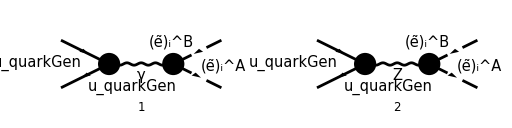

```mathematica
diags[0]=InsertFields[
CreateTopologies[0,2->2],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1|2|3|4|5|6]}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MLO[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
ChangeDimension->D,
LorentzIndexNames->{μ,ν},
UndoChiralSplittings->True,
DropSumOver->True,
List->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

{(ⅈ e (k_1-k_2)^ν g^μν IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(φ(p_1)))/(k_1+k_2)^2,-((ⅈ e (k_1-k_2)^ν g^μν (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e γ^μ.(γ̄)^6 δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ e γ^μ.(γ̄)^7 δ_Col1Col2 (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2)))}

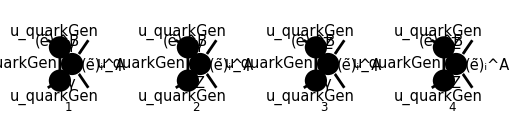

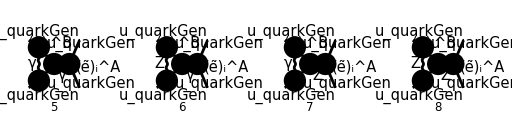

```mathematica
diags[1]=InsertFields[
CreateTopologies[1,2->2,
ExcludeTopologies->{Tadpoles,SelfEnergies}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],(*Higgs*)
F[11|12],(*Electroweakinos*)
S[11|12],(*Sleptons*)
S[13|14],(*Squarks*)
V[3](*W-bosons*)
}
];
Paint[
diags[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MLO[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
ChangeDimension->D,
LorentzIndexNames->{μ,ν},
UndoChiralSplittings->True,
DropSumOver->True,
List->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

{(ⅈ e (k_1-k_2)^ν g^μν IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(φ(p_1)))/(k_1+k_2)^2,-((ⅈ e (k_1-k_2)^ν g^μν (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e γ^μ.(γ̄)^6 δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ e γ^μ.(γ̄)^7 δ_Col1Col2 (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2)))}

## 09.03

```mathematica
$Assumptions={
0<x<1,
s∈PositiveReals,
d∈PositiveReals
};
```

```mathematica
(-x y s)^((d-4)/2)
%//Integrate[#,{y,0,1-x}]&
```

(-s x y)^((d-4)/2)

ConditionalExpression[(2 ⅈ^d (1-x)^(d/2-1) (s x)^(d/2-2))/(d-2), d>2]

```mathematica
1/Gamma[d-1]
%//ReplaceAll[#,d->4-2ϵ]&
%//Series[#,{ϵ,0,2}]&
```

1/(d-1)

1/(3-2 ϵ)

1/2+1/2 (3-2 ℽ) ϵ+1/6 (21-18 ℽ+6 ℽ^2-π^2) ϵ^2+O(ϵ^3)

```mathematica
Gamma[ϵ]//Series[#,{ϵ,0,2}]&
```

1/ϵ-ℽ+1/12 (6 ℽ^2+π^2) ϵ+1/6 ϵ^2 (-ℽ^3-(ℽ π^2)/2+21)+O(ϵ^3)

```mathematica
Gamma[2-ϵ]//Series[#,{ϵ,0,2}]&
```

1+(ℽ-1) ϵ+1/12 (-12 ℽ+6 ℽ^2+π^2) ϵ^2+O(ϵ^3)

```mathematica
1/Gamma[3-2ϵ]//Series[#,{ϵ,0,1}]&
```

1/2+1/2 (3-2 ℽ) ϵ+O(ϵ^2)

```mathematica
integrand=((d-2)/2x y-x-y+1)(-x y s)^((d-6)/2)
%//Integrate[#,{y,0,1-x}]&
%//Integrate[#,{x,0,1}]&
```

(1/2 (d-2) x y-x-y+1) (-s x y)^((d-6)/2)

ConditionalExpression[-(ⅈ^d (1-x)^(d/2-1) ((d-4) (d-2) x+4) (s x)^(d/2-3))/((d-4) (d-2)), d>4]

ConditionalExpression[-(ⅈ^d ((d-8) d+24) s^(d/2-3) d/2-2 d/2)/(2 (d-4) d-1), d>4]

```mathematica
Gamma[ϵ]//Series[#,{ϵ,0,2}]&
```

1/ϵ-ℽ+1/12 (6 ℽ^2+π^2) ϵ+1/6 ϵ^2 (-ℽ^3-(ℽ π^2)/2+21)+O(ϵ^3)

```mathematica
1/Gamma[2-2ϵ]//Series[#,{ϵ,0,2}]&
```

1+(2-2 ℽ) ϵ+(4-4 ℽ+2 ℽ^2-π^2/3) ϵ^2+O(ϵ^3)

```mathematica
Gamma[ϵ]//Series[#,{ϵ,0,1}]&
```

1/ϵ-ℽ+1/12 (6 ℽ^2+π^2) ϵ+O(ϵ^2)

```mathematica
1/(2-2ϵ)//Series[#,{ϵ,0,2}]&
```

1/2+ϵ/2+ϵ^2/2+O(ϵ^3)

```mathematica
(d^2-8d+24)/(2(d-2))//ReplaceAll[#,{d->4-2ϵ}]&//Series[#,{ϵ,0,2}]&
```

2+2 ϵ+3 ϵ^2+O(ϵ^3)

```mathematica
Gamma[-ϵ]//Series[#,{ϵ,0,1}]&
```

-1/ϵ-ℽ+1/12 (-6 ℽ^2-π^2) ϵ+O(ϵ^2)

```mathematica
(d^2-8d+24)/(2(d-2))Gamma[(4-d)/2]Gamma[(d-4)/2]Gamma[d/2]/Gamma[d-2]
%//ReplaceAll[#,{d->4-2ϵ}]&//Series[#,{ϵ,0,0}]&
```

((d^2-8 d+24) (4-d)/2 (d-4)/2 d/2)/(2 (d-2) d-2)

-2/ϵ^2+(2 (ℽ-2))/ϵ+1/6 (-54+24 ℽ-6 ℽ^2+π^2)+O(ϵ^1)

```mathematica
(1/ϵ-EulerGamma+ϵ(EulerGamma^2/2+Pi^2/12))(1/ϵ+EulerGamma+ϵ(EulerGamma^2/2+Pi^2/12))
%//Series[#,{ϵ,0,0}]&
```

((ℽ^2/2+π^2/12) ϵ+1/ϵ-ℽ) ((ℽ^2/2+π^2/12) ϵ+1/ϵ+ℽ)

1/ϵ^2+π^2/6+O(ϵ^1)

```mathematica
(1+ϵ(EulerGamma-1)+ϵ^2(EulerGamma^2/2-EulerGamma+Pi^2/12))(1-2ϵ(EulerGamma-1)+ϵ^2(2EulerGamma^2-4EulerGamma+4-Pi^2/3))
%//Series[#,{ϵ,0,2}]&
```

((4-4 ℽ+2 ℽ^2-π^2/3) ϵ^2-2 (ℽ-1) ϵ+1) ((-ℽ+ℽ^2/2+π^2/12) ϵ^2+(ℽ-1) ϵ+1)

1+(1-ℽ) ϵ+1/4 (8-4 ℽ+2 ℽ^2-π^2) ϵ^2+O(ϵ^3)

```mathematica
(d^2-8d+24)/(2(d-2))Gamma[(4-d)/2]Gamma[(d-4)/2]Gamma[d/2]/Gamma[d-2]
I2=%//ReplaceAll[#,{d->4-2EpsilonIR}]&//Series[#,{EpsilonIR,0,0}]&
```

((d^2-8 d+24) (4-d)/2 (d-4)/2 d/2)/(2 (d-2) d-2)

-2/ε_IR^2+(2 (ℽ-2))/ε_IR+1/6 (-54+24 ℽ-6 ℽ^2+π^2)+O(ε_IR^1)

```mathematica
2Gamma[(4-d)/2]Gamma[d/2]^2/Gamma[d-1]
I1=%//ReplaceAll[#,{d->4-2EpsilonUV}]&//Series[#,{EpsilonUV,0,0}]&
```

(2 (4-d)/2 (d/2)^2)/(d-1)

1/ε_UV+(1-ℽ)+O(ε_UV^1)

```mathematica
I1
```

1/ε_UV+(1-ℽ)+O(ε_UV^1)

```mathematica
I2
```

-2/ε_IR^2+(2 (ℽ-2))/ε_IR+1/6 (-54+24 ℽ-6 ℽ^2+π^2)+O(ε_IR^1)

```mathematica
-(I1+I2)//Normal//FullSimplify
```

(4-2 ℽ)/ε_IR+2/ε_IR^2-1/ε_UV-π^2/6+(ℽ-3) ℽ+8

## 10.03

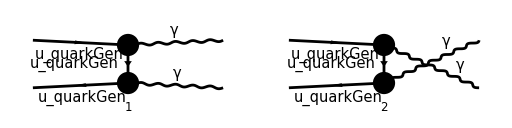

```mathematica
diags[0]=InsertFields[
CreateTopologies[0,2->2],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{V[1],V[1]},
Model->MSSM,
InsertionLevel->{Classes}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

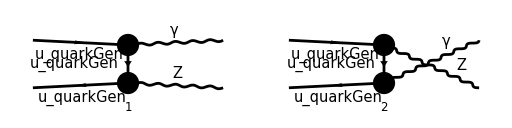

```mathematica
diags[1]=InsertFields[
CreateTopologies[0,2->2],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{V[1],V[2]},
Model->MSSM,
InsertionLevel->{Classes}
];
Paint[
diags[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
Mγ[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k,q},
LorentzIndexNames->{ρ,μ},
ChangeDimension->D,
SMP->True,
List->False,
DropSumOver->True,
UndoChiralSplittings->True
]/.{MQU[quarkGen]->0}
```

((ε^*)^ρ(k) (ε^*)^μ(q) (φ(-p_2)).(-2/3 ⅈ e γ^ρ δ_Col1Col2).(γ·(k-p_2)).(-2/3 ⅈ e γ^μ).(φ(p_1)))/(p_2-k)^2+((ε^*)^ρ(k) (ε^*)^μ(q) (φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(γ·(q-p_2)).(-2/3 ⅈ e γ^ρ).(φ(p_1)))/(p_2-q)^2

```mathematica
Mγ[1]=3/2SMP["e_Q"]Mγ[0]/(ChangeDimension[ComplexConjugate[PolarizationVector[k,ρ]],D] ChangeDimension[ComplexConjugate[PolarizationVector[q,μ]],D])//FullSimplify
```

3/2 e_Q (((φ(-p_2)).(-2/3 ⅈ e γ^ρ δ_Col1Col2).(γ·(k-p_2)).(-2/3 ⅈ e γ^μ).(φ(p_1)))/(p_2-k)^2+((φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(γ·(q-p_2)).(-2/3 ⅈ e γ^ρ).(φ(p_1)))/(p_2-q)^2)

```mathematica
GA[α,β,γ,δ,ϵ,ζ,η,θ,5]
%//DiracTrace
%//DiracSimplify//FCE//Collect2[#,{LC},IsolateNames->KK]&
```

(γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^ϵ.(γ̄)^ζ.(γ̄)^η.(γ̄)^θ.(γ̄)^5

tr((γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^ϵ.(γ̄)^ζ.(γ̄)^η.(γ̄)^θ.(γ̄)^5)

-4 ⅈ KK(128) (ϵ̄)^αβγδ-4 ⅈ KK(142) (ϵ̄)^αβγζ+4 ⅈ KK(136) (ϵ̄)^αβγη-4 ⅈ KK(143) (ϵ̄)^αβγθ+4 ⅈ KK(137) (ϵ̄)^αβγϵ-4 ⅈ KK(138) (ϵ̄)^αδϵζ+4 ⅈ KK(135) (ϵ̄)^αδϵη-4 ⅈ KK(141) (ϵ̄)^αδϵθ-4 ⅈ KK(134) (ϵ̄)^αζηθ+4 ⅈ KK(127) (ϵ̄)^βδϵζ-4 ⅈ KK(125) (ϵ̄)^βδϵη+4 ⅈ KK(129) (ϵ̄)^βδϵθ+4 ⅈ KK(140) (ϵ̄)^βζηθ-4 ⅈ KK(131) (ϵ̄)^γδϵζ+4 ⅈ KK(133) (ϵ̄)^γδϵη-4 ⅈ KK(139) (ϵ̄)^γδϵθ-4 ⅈ KK(132) (ϵ̄)^γζηθ+4 ⅈ KK(130) (ϵ̄)^δζηθ-4 ⅈ KK(126) (ϵ̄)^ϵζηθ

```mathematica
GA[α,β,γ,δ,ϵ,ζ,5]
%//DiracTrace
%//DiracSimplify//FCE//Collect2[#,{LC},IsolateNames->KK]&
```

(γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^ϵ.(γ̄)^ζ.(γ̄)^5

tr((γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^ϵ.(γ̄)^ζ.(γ̄)^5)

-4 ⅈ KK(161) (ϵ̄)^αβγδ-4 ⅈ KK(162) (ϵ̄)^αβγζ+4 ⅈ KK(159) (ϵ̄)^αβγϵ-4 ⅈ KK(163) (ϵ̄)^αδϵζ+4 ⅈ KK(158) (ϵ̄)^βδϵζ-4 ⅈ KK(160) (ϵ̄)^γδϵζ

```mathematica
GA[α,β,γ,δ,5]
%//DiracTrace
%//DiracSimplify//FCE//Collect2[#,{LC},IsolateNames->KK]&
```

(γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^5

tr((γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^5)

-4 ⅈ (ϵ̄)^αβγδ

```mathematica
GA[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8,μ9,μ10,5]
%//DiracTrace
%//DiracSimplify//FCE//Collect2[#,{LC},IsolateNames->KK]&
```

(γ̄)^μ1.(γ̄)^μ2.(γ̄)^μ3.(γ̄)^μ4.(γ̄)^μ5.(γ̄)^μ6.(γ̄)^μ7.(γ̄)^μ8.(γ̄)^μ9.(γ̄)^μ10.(γ̄)^5

tr((γ̄)^μ1.(γ̄)^μ2.(γ̄)^μ3.(γ̄)^μ4.(γ̄)^μ5.(γ̄)^μ6.(γ̄)^μ7.(γ̄)^μ8.(γ̄)^μ9.(γ̄)^μ10.(γ̄)^5)

-4 ⅈ KK(220) (ϵ̄)^μ1μ10μ2μ3-4 ⅈ KK(214) (ϵ̄)^μ1μ10μ4μ5-4 ⅈ KK(210) (ϵ̄)^μ1μ10μ6μ7-4 ⅈ KK(222) (ϵ̄)^μ1μ10μ8μ9-4 ⅈ KK(229) (ϵ̄)^μ1μ2μ3μ4+4 ⅈ KK(239) (ϵ̄)^μ1μ2μ3μ5-4 ⅈ KK(219) (ϵ̄)^μ1μ2μ3μ6+4 ⅈ KK(235) (ϵ̄)^μ1μ2μ3μ7-4 ⅈ KK(204) (ϵ̄)^μ1μ2μ3μ8+4 ⅈ KK(225) (ϵ̄)^μ1μ2μ3μ9-4 ⅈ KK(196) (ϵ̄)^μ1μ4μ5μ6+4 ⅈ KK(215) (ϵ̄)^μ1μ4μ5μ7-4 ⅈ KK(231) (ϵ̄)^μ1μ4μ5μ8+4 ⅈ KK(192) (ϵ̄)^μ1μ4μ5μ9-4 ⅈ KK(242) (ϵ̄)^μ1μ6μ7μ8+4 ⅈ KK(226) (ϵ̄)^μ1μ6μ7μ9-4 ⅈ KK(232) (ϵ̄)^μ10μ2μ4μ5-4 ⅈ KK(234) (ϵ̄)^μ10μ2μ6μ7-4 ⅈ KK(238) (ϵ̄)^μ10μ2μ8μ9+4 ⅈ KK(203) (ϵ̄)^μ10μ3μ4μ5+4 ⅈ KK(241) (ϵ̄)^μ10μ3μ6μ7+4 ⅈ KK(236) (ϵ̄)^μ10μ3μ8μ9-4 ⅈ KK(237) (ϵ̄)^μ10μ4μ6μ7-4 ⅈ KK(199) (ϵ̄)^μ10μ4μ8μ9+4 ⅈ KK(227) (ϵ̄)^μ10μ5μ6μ7+4 ⅈ KK(194) (ϵ̄)^μ10μ5μ8μ9-4 ⅈ KK(193) (ϵ̄)^μ10μ6μ8μ9+4 ⅈ KK(224) (ϵ̄)^μ10μ7μ8μ9+4 ⅈ KK(200) (ϵ̄)^μ2μ4μ5μ6-4 ⅈ KK(233) (ϵ̄)^μ2μ4μ5μ7+4 ⅈ KK(207) (ϵ̄)^μ2μ4μ5μ8-4 ⅈ KK(211) (ϵ̄)^μ2μ4μ5μ9+4 ⅈ KK(230) (ϵ̄)^μ2μ6μ7μ8-4 ⅈ KK(206) (ϵ̄)^μ2μ6μ7μ9-4 ⅈ KK(228) (ϵ̄)^μ3μ4μ5μ6+4 ⅈ KK(198) (ϵ̄)^μ3μ4μ5μ7-4 ⅈ KK(208) (ϵ̄)^μ3μ4μ5μ8+4 ⅈ KK(240) (ϵ̄)^μ3μ4μ5μ9-4 ⅈ KK(223) (ϵ̄)^μ3μ6μ7μ8+4 ⅈ KK(213) (ϵ̄)^μ3μ6μ7μ9+4 ⅈ KK(221) (ϵ̄)^μ4μ6μ7μ8-4 ⅈ KK(202) (ϵ̄)^μ4μ6μ7μ9-4 ⅈ KK(217) (ϵ̄)^μ5μ6μ7μ8+4 ⅈ KK(218) (ϵ̄)^μ5μ6μ7μ9

## 11.03

```mathematica
1/Gamma[(d-1)/2]
%//ReplaceAll[#,{d->4-2ϵ}]&
%//Series[#,{ϵ,0,1}]&
```

1/((d-1)/2)

1/(1/2 (3-2 ϵ))

2/(√π)+(2 ϵ 03/2)/(√π)+O(ϵ^2)

```mathematica
Gamma[(d-1)/2]
%//ReplaceAll[#,{d->4-2ϵ}]&
%//Series[#,{ϵ,0,1}]&
```

(d-1)/2

1/2 (3-2 ϵ)

(√π)/2-1/2 ϵ (√π 03/2)+O(ϵ^2)

```mathematica
HarmonicNumber[2]
```

3/2

## 12.03

```mathematica
S[μ_,ν_]:=1/t GAD[μ].GSD[p1-k].GAD[ν]-1/u GAD[ν].GSD[p2-k].GAD[μ]
```

```mathematica
GSD[p2].S[μ,ν].GSD[p1].S[σ,ρ]
```

(γ·p_2).((γ^μ.(γ·(p_1-k)).γ^ν)/t-(γ^ν.(γ·(p_2-k)).γ^μ)/u).(γ·p_1).((γ^σ.(γ·(p_1-k)).γ^ρ)/t-(γ^ρ.(γ·(p_2-k)).γ^σ)/u)

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,k,q,0,0,0,Q];
```

```mathematica
DiracTrace[GSD[p2].GAD[μ].GSD[p1-k].GAD[ν].GSD[p1].GAD[μ].GSD[p2-k].GAD[ν]]
%//DiracSimplify//FullSimplify
%//TrickMandelstam[#,{s,t,u,Q^2}]&//FullSimplify
```

tr((γ·p_2).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_1).γ^μ.(γ·(p_2-k)).γ^ν)

-2 (D-2) ((D-4) t u+2 s^2-2 s (t+u))

-2 (D-2) (u (D t+4 u)-2 Q^2 (s+2 u)+4 s^2+4 s u)

```mathematica
GAD[μ].GAD[ν].GAD[λ].GAD[μ]
%//DiracSimplify//Simplify
```

γ^μ.γ^ν.γ^λ.γ^μ

(D-4) γ^ν.γ^λ+4 g^λν

```mathematica
GAD[μ].GAD[ν].GAD[λ].GAD[ρ].GAD[μ]
%//DiracSimplify//Simplify
```

γ^μ.γ^ν.γ^λ.γ^ρ.γ^μ

-2 γ^ρ.γ^λ.γ^ν-((D-4) γ^ν.γ^λ.γ^ρ)

## 13.03

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,k,q,0,0,0,Q];
```

```mathematica
DiracTrace[GSD[p1].GAD[μ].GSD[p1-k].GAD[ν].GSD[p2].GAD[μ].GSD[p2-k].GAD[ν]]
%//DiracSimplify//FullSimplify
%//TrickMandelstam[#,{s,t,u,Q^2}]&//FullSimplify
```

tr((γ·p_1).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_2-k)).γ^ν)

-2 (D-2) ((D-4) t u+2 s^2-2 s (t+u))

-2 (D-2) (u (D t+4 u)-2 Q^2 (s+2 u)+4 s^2+4 s u)

```mathematica
DiracTrace[GSD[p1].GAD[μ].GSD[p1-k].GAD[ν].GSD[p2].GAD[μ].GSD[p2-k].GAD[ν]]
DiracTrace[GSD[p2].GAD[μ].GSD[p1-k].GAD[ν].GSD[p1].GAD[μ].GSD[p2-k].GAD[ν]]
FCCompareResults[{%//DiracSimplify},{%%//DiracSimplify}]
```

tr((γ·p_1).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_2-k)).γ^ν)

tr((γ·p_2).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_1).γ^μ.(γ·(p_2-k)).γ^ν)

Check of the results: The results agree.

True

```mathematica
GSD[p1].GAD[μ].GSD[p1-k].GAD[ν].GSD[p2].GAD[μ].GSD[p2-k].GAD[ν]
GSD[p1].GAD[μ].GSD[p2-k].GAD[ν].GSD[p2].GAD[μ].GSD[p1-k].GAD[ν]
FCCompareResults[{%//DiracSimplify},{%%//DiracSimplify}]
```

(γ·p_1).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_2-k)).γ^ν

(γ·p_1).γ^μ.(γ·(p_2-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_1-k)).γ^ν

Check of the results: The results disagree.

False

```mathematica
FCClearScalarProducts[];
```

```mathematica
DiracTrace[GSD[p1].GAD[μ].GSD[p1-k].GAD[ν].GSD[p2].GAD[μ].GSD[p2-k].GAD[ν]]
DiracTrace[GSD[p1].GAD[μ].GSD[p2-k].GAD[ν].GSD[p2].GAD[μ].GSD[p1-k].GAD[ν]]
FCCompareResults[{%//DiracSimplify},{%%//DiracSimplify}]
```

tr((γ·p_1).γ^μ.(γ·(p_1-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_2-k)).γ^ν)

tr((γ·p_1).γ^μ.(γ·(p_2-k)).γ^ν.(γ·p_2).γ^μ.(γ·(p_1-k)).γ^ν)

Check of the results: The results agree.

True

```mathematica
(2Pi)^d DeltaFunction[k+1-p1-p2]diff^(d-1)q
```

```mathematica
Gamma[1-ϵ]//Series[#,{ϵ,0,2}]&
-ϵ Gamma[-ϵ]//Series[#,{ϵ,0,2}]&
```

1+ℽ ϵ+1/12 (6 ℽ^2+π^2) ϵ^2+O(ϵ^3)

1+ℽ ϵ+1/12 (6 ℽ^2+π^2) ϵ^2+O(ϵ^3)

## 16.03

```mathematica
Gamma[1-ϵ]/Gamma[1-2ϵ]
%//Series[#,{ϵ,0,2}]&
```

(1-ϵ)/(1-2 ϵ)

1-ℽ ϵ+1/4 (2 ℽ^2-π^2) ϵ^2+O(ϵ^3)

```mathematica
1/(1-2ϵ)
%//Series[#,{ϵ,0,2}]&
```

1/(1-2 ϵ)

1+2 ϵ+4 ϵ^2+O(ϵ^3)

## 17.03

```mathematica
C0[0,s,0,0,0,0]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

C_0(0,s,0,0,0,0)

-(-log(-μ^2/s)+ℽ-log(4 π))/(s ε_IR)+1/(s ε_IR^2)+(6 log^2(-μ^2/s)+12 log(4 π) log(-μ^2/s)-12 ℽ log(-μ^2/s)-π^2+6 ℽ^2+6 log^2(4 π)-12 ℽ log(4 π))/(12 s)

```mathematica
(-z)^ϵ Gamma[ϵ]Gamma[2-ϵ]/(2(1-2ϵ))
%//Series[#,{ϵ,0,0}]&
```

((-z)^ϵ 2-ϵ ϵ)/(2 (1-2 ϵ))

1/(2 ϵ)+1/2 (log(-z)+1)+O(ϵ^1)

```mathematica
(-z)^ϵ Gamma[ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)+2Gamma[1-ϵ]/(1-ϵ)+Gamma[1-ϵ]/ϵ)
%//Series[#,{ϵ,0,0}]&
```

(-z)^ϵ ((1-ϵ)/(1-2 ϵ)+(2 1-ϵ)/(1-ϵ)+(1-ϵ)/ϵ+(ϵ 2-ϵ)/(2 (1-2 ϵ) (1-ϵ))) ϵ

1/ϵ^2+(log(-z)+3)/ϵ+1/6 (3 log^2(-z)+18 log(-z)+π^2+27)+O(ϵ^1)

```mathematica
Log[-z]//Assuming[z∈PositiveReals,#]&
```

log(-z)

```mathematica
Assuming[z∈PositiveReals,Re[Log[-z]^2]+I Im[Log[-z]^2]//FullSimplify//Expand]
```

log^2(z)+2 ⅈ π log(z)-π^2

```mathematica
27/6
```

9/2

```mathematica
C0[0,s,0,0,0,0]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

C_0(0,s,0,0,0,0)

-(-log(-μ^2/s)+ℽ-log(4 π))/(s ε_IR)+1/(s ε_IR^2)+(6 log^2(-μ^2/s)+12 log(4 π) log(-μ^2/s)-12 ℽ log(-μ^2/s)-π^2+6 ℽ^2+6 log^2(4 π)-12 ℽ log(4 π))/(12 s)

```mathematica
FCClearScalarProducts[];
SPD[p1]=0;
SPD[p2]=0;
SPD[p1,p2]=s/2;
```

```mathematica
SpinorVBarD[p2,0].GAD[ρ].GSD[k-p2].GAD[μ].GSD[k+p1].GAD[ρ].SpinorUD[p1,0] FAD[k,k+p1,k-p2]
%//DiracSimplify//FullSimplify
%//TID[#,k,ToPaVe->True]&//Collect2[#,{A0,B0,C0},Factoring->DiracSimplify,IsolateNames->KK]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
Γμ=%//FRH//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&
```

(v̄(p_2).γ^ρ.(γ·(k-p_2)).γ^μ.(γ·(k+p_1)).γ^ρ.u(p_1))/(k^2.(k+p_1)^2.(k-p_2)^2)

1/(k^2.(k+p_1)^2.(k-p_2)^2)(((D-2) k^2-2 (-2 (k·p_1)+2 (k·p_2)+s)) (φ(-p_2)).γ^μ.(φ(p_1))-2 ((D-2) k^μ+2 (p_1^μ-p_2^μ)) (φ(-p_2)).(γ·k).(φ(p_1)))

KK(14353) B_0(s,0,0)+4 ⅈ KK(14304) B_0(0,0,0)-2 ⅈ KK(14863) C_0(0,0,s,0,0,0)

-(2 ⅈ (KK(14863) log(-μ^2/s)+2 KK(14304) s-ℽ KK(14863)+KK(14863) log(4 π)))/(s ε_IR)-(2 ⅈ KK(14863))/(s ε_IR^2)-1/(6 s)(6 ⅈ KK(14863) log^2(-μ^2/s)-12 ⅈ ℽ KK(14863) log(-μ^2/s)+12 ⅈ KK(14863) log(4 π) log(-μ^2/s)-6 KK(14353) s log(-(4 π μ^2)/s)+6 ℽ KK(14353) s-12 KK(14353) s-ⅈ π^2 KK(14863)+6 ⅈ ℽ^2 KK(14863)+6 ⅈ KK(14863) log^2(4 π)-12 ⅈ ℽ KK(14863) log(4 π))+(KK(14353)+4 ⅈ KK(14304))/ε_UV

-(2 ⅈ KK(14304))/ε_IR^2+(2 ⅈ KK(16725))/ε_IR+(ⅈ KK(16723))/ε_UV+1/6 ⅈ KK(16730)

```mathematica
KK[14304]
KK[16725]//FRH
KK[16723]//FRH
KK[16730]//FRH
```

π^2 (φ(-p_2)).γ^μ.(φ(p_1))

π^2 (-log(-(4 π μ^2)/s)+ℽ-2) (φ(-p_2)).γ^μ.(φ(p_1))

π^2 (D-3) (φ(-p_2)).γ^μ.(φ(p_1))

π^2 (6 (D+2 ℽ-7) log(-(4 π μ^2)/s)-6 (ℽ-2) D-6 log(-μ^2/s) log(-(16 π^2 μ^2)/s)+π^2-6 (ℽ-7) ℽ-84-6 log^2(4 π)) (φ(-p_2)).γ^μ.(φ(p_1))

```mathematica
-I SMP["e"]^2SMP["e_Q"]^2 Γμ (SpinorUBarD[p1,0].GAD[μ].SpinorVD[p2,0])//FRH//FermionSpinSum[#,ExtraFactor->1/(4SUNN)]&//DiracSimplify//FullSimplify
```

1/(12 N ε_IR^2 ε_UV)π^2 (D-2) e^2 s e_Q^2 (6 ε_IR ε_UV ((2-(D+2 ℽ-7) ε_IR) log(-(4 π μ^2)/s)+ε_IR log(-μ^2/s) log(-(16 π^2 μ^2)/s))+ε_IR^2 (6 D ((ℽ-2) ε_UV-1)+(84+6 (ℽ-7) ℽ-π^2+6 log^2(4 π)) ε_UV+18)-12 (ℽ-2) ε_IR ε_UV+12 ε_UV)

```mathematica
$Assumptions={ϵ>0};
```

```mathematica
x^(-ϵ)y^(-ϵ)
Integrate[%,{y,0,1-x}]
Integrate[%,{x,0,1}]
```

x^-ϵ y^-ϵ

ConditionalExpression[((1-x)^(1-ϵ) x^-ϵ)/(1-ϵ), ϵ<1]

ConditionalExpression[-(√π 4^(ϵ-1) 1-ϵ)/((ϵ-1) 3/2-ϵ), ϵ<1]

```mathematica
$Assumptions={ϵ<0};
```

```mathematica
(1-ϵ)x^(-ϵ)y^(-ϵ)-x^(-ϵ)y^(-1-ϵ)-x^(-1-ϵ)y^(-ϵ)+x^(-1-ϵ)y^(-1-ϵ)
Integrate[%,{y,0,1-x}]//ExpandAll2
```

x^(-ϵ-1) y^(-ϵ-1)-x^(-ϵ-1) y^-ϵ-x^-ϵ y^(-ϵ-1)+(1-ϵ) x^-ϵ y^-ϵ

(x-1)^2 x (-((x-1) x))^(-ϵ-1)+((x-1)^2 (-((x-1) x))^(-ϵ-1))/((ϵ-1) ϵ)

```mathematica
(-z)^ϵ Gamma[ϵ]1/(2(1-2ϵ))Gamma[2-ϵ]
%//Series[#,{ϵ,0,0}]&
```

((-z)^ϵ 2-ϵ ϵ)/(2 (1-2 ϵ))

1/(2 ϵ)+1/2 (log(-z)+1)+O(ϵ^1)

```mathematica
(-z)^ϵ Gamma[ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)-2ϵ Gamma[1-ϵ]+Gamma[1-ϵ]/ϵ)
%//Series[#,{ϵ,0,0}]&
```

(-z)^ϵ (-2 ϵ 1-ϵ+(1-ϵ)/(1-2 ϵ)+(1-ϵ)/ϵ+(ϵ 2-ϵ)/(2 (1-2 ϵ) (1-ϵ))) ϵ

1/ϵ^2+(log(-z)+1)/ϵ+1/6 (3 log^2(-z)+6 log(-z)+π^2+3)+O(ϵ^1)

```mathematica
1/Gamma[2-ϵ]
%//Series[#,{ϵ,0,1}]&
```

1/(2-ϵ)

1+(1-ℽ) ϵ+O(ϵ^2)

```mathematica
B0[m^2,0,m^2]//PaXEvaluateUVIRSplit
```

log(μ^2/(π m^2))+1/ε_UV-ℽ+2

```mathematica
(-z)^ϵ(1/(2(1-2ϵ))Gamma[ϵ]Gamma[2-ϵ])
%//Series[#,{ϵ,0,0}]&
```

((-z)^ϵ 2-ϵ ϵ)/(2 (1-2 ϵ))

1/(2 ϵ)+1/2 (log(-z)+1)+O(ϵ^1)

```mathematica
(-z)^ϵ Gamma[ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)-2ϵ Gamma[1-ϵ]+Gamma[1-ϵ]/ϵ)
%//Series[#,{ϵ,0,0}]&
```

(-z)^ϵ (-2 ϵ 1-ϵ+(1-ϵ)/(1-2 ϵ)+(1-ϵ)/ϵ+(ϵ 2-ϵ)/(2 (1-2 ϵ) (1-ϵ))) ϵ

1/ϵ^2+(log(-z)+1)/ϵ+1/6 (3 log^2(-z)+6 log(-z)+π^2+3)+O(ϵ^1)

```mathematica
(-z)^ϵ Gamma[ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/ϵ)
%//Series[#,{ϵ,0,0}]&
```

(-z)^ϵ ((2 1-ϵ)/(1-2 ϵ)+(1-ϵ)/ϵ+(ϵ 2-ϵ)/(2 (1-2 ϵ) (1-ϵ))) ϵ

1/ϵ^2+(log(-z)+2)/ϵ+1/6 (3 log^2(-z)+12 log(-z)+π^2+27)+O(ϵ^1)

```mathematica
x^(-ϵ)y^(-ϵ)
 Integrate[Integrate[%,{y,0,1-x}],{x,0,1}]
```

x^-ϵ y^-ϵ

-(√π 4^(ϵ-1) 1-ϵ)/((ϵ-1) 3/2-ϵ)

```mathematica
$Assumptions={
ϵ∈Reals,
ϵIR∈NegativeReals,
ϵUV∈PositiveReals,
ϵIR>-1,
ϵUV<1
};
MakeBoxes[ϵIR,TraditionalForm]:=SubscriptBox["ϵ","IR"];
MakeBoxes[ϵUV,TraditionalForm]:=SubscriptBox["ϵ","UV"];
```

```mathematica
fullInt[X_]:=Integrate[Integrate[X,{y,0,1-x}],{x,0,1}]
```

```mathematica
fullInt[(1-ϵUV)^2x^(-ϵUV)y^(-ϵUV)]//FullSimplify
Gamma[1-ϵ]/Gamma[1-2ϵ]Gamma[2-ϵ]/(2(1-2ϵ))//.{ϵ->ϵUV}//FullSimplify
FCCompareResults[{%%},{%}]
```

(√π 4^(ϵ_UV-1) 2-ϵ_UV)/(3/2-ϵ_UV)

(1-ϵ_UV 2-ϵ_UV)/(2 2-2 ϵ_UV)

Check of the results: The results disagree.

False

```mathematica
ϵ fullInt[(1-ϵ)x^(-ϵ)y^(-ϵ)-x^(-ϵ)y^(-1-ϵ)-x^(-1-ϵ)y^(-ϵ)+x^(-1-ϵ)y^(-1-ϵ)]//.{ϵ->ϵIR}//FullSimplify
Gamma[1-ϵ]/Gamma[1-2ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/ϵ)//FullSimplify
FCCompareResults[{%%},{%}]
```

-(√π 4^(ϵ_IR-1) (ϵ_IR^2+2) -ϵ_IR)/(3/2-ϵ_IR)

(ϵ (ϵ^2+2) (-ϵ)^2)/(2 2-2 ϵ)

Check of the results: The results disagree.

False

```mathematica
(-z)^ϵUV Gamma[ϵUV]1/(2(1-2ϵUV))Gamma[2-ϵUV]+(-z)^ϵ Gamma[ϵ](ϵ/(2(1-ϵ)(1-2ϵ))Gamma[2-ϵ]+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/(1-2ϵ)+Gamma[1-ϵ]/ϵ)
virt=%//Series[#,{ϵ,0,0},{ϵUV,0,0}]&//Simplify
```

((-z)^ϵ_UV 2-ϵ_UV ϵ_UV)/(2 (1-2 ϵ_UV))+(-z)^ϵ ((2 1-ϵ)/(1-2 ϵ)+(1-ϵ)/ϵ+(ϵ 2-ϵ)/(2 (1-2 ϵ) (1-ϵ))) ϵ

1/ϵ^2+(log(-z)+2)/ϵ+(1/(2 ϵ_UV)+1/6 (3 log^2(-z)+15 log(-z)+π^2+30)+O(ϵ_UV^1))+O(ϵ^1)

```mathematica
rad=1/ϵ^2 DeltaFunction[1-z]-1/ϵ(1+z^2)PlusDistribution[1/(1-z)]-(1+z^2)Log[z]PlusDistribution[1/(1-z)]+2(1+z^2)PlusDistribution[Log[1-z]/(1-z)]
```

-((z^2+1) (1/(1-z))_+)/ϵ-(z^2+1) (1/(1-z))_+ log(z)+2 (z^2+1) ((log(1-z))/(1-z))_++(δ(1-z))/ϵ^2

```mathematica
rad-virt DeltaFunction[1-z]//Simplify
```

(-(z^2+1) (1/(1-z))_+-δ(1-z) (log(-z)+2))/ϵ+(-(δ(1-z))/(2 ϵ_UV)+(-(z^2+1) ((1/(1-z))_+ log(z)-2 ((log(1-z))/(1-z))_+)-1/6 δ(1-z) (3 log^2(-z)+15 log(-z)+π^2+30))+O(ϵ_UV^1))+O(ϵ^1)

## Going through hadron-side virtual calculation to find why I get a slightly different result from Tore

```mathematica
FCClearScalarProducts[];
SPD[p1]=0;
SPD[p2]=0;
SPD[p1,p2]=s/2;
```

```mathematica
SpinorVBarD[p2,0].GAD[ν].GSD[k-p2].GAD[μ].GSD[k+p1].GAD[ν].SpinorUD[p1,0]
%//DiracGammaExpand//FCE//ReplaceAll[#,{
GSD[k]->GSD[k]-x GSD[p1]+y GSD[p2]
}]&
%//DiracSimplify//FullSimplify//Uncontract[#,k]&//Collect2[#,{k},Factoring->Simplify,IsolateNames->KK]&
```

v̄(p_2).γ^ν.(γ·(k-p_2)).γ^μ.(γ·(k+p_1)).γ^ν.u(p_1)

(φ(-p_2)).γ^ν.(γ·k-γ·p_2-x γ·p_1+y γ·p_2).γ^μ.(γ·k+γ·p_1-x γ·p_1+y γ·p_2).γ^ν.(φ(p_1))

-2 KK(101) k^μ k^($AL($98))+2 KK(100) k^($AL($96))-2 KK(99) k^($AL($97))+KK(54) (k·p_1)+2 KK(57) (k·p_2)+k^2 KK(60)+KK(65)

#### Remove all terms linear in k

```mathematica
vNu=-2KK[101]FVD[k,μ]FVD[k,$AL[$98]]+SPD[k]KK[60]+KK[65]//FRH//FCE//ReplaceAll[#,{FVD[k,μ]FVD[k,$AL[$98]]->SPD[k]/D MTD[μ,$AL[$98]]}]&//Contract//FullSimplify
```

(((D-2)^2 k^2+D s (x (-D y+2 y+2)+2 (y-1))) (φ(-p_2)).γ^μ.(φ(p_1)))/D

Doing integrals over k using (B.38) and (B.39) in Schwartz

```mathematica
iΓμ[0]=GAD[μ]prefac ((D-2)^2/D intksquared + s((2-D)x y+2x+2y-2)intkzeroth)
iΓμ[1]=%//ReplaceAll[#,{
prefac->-2I SMP["e"]^2 SMP["e_Q"]^2 ScaleMu^(4-D),
intksquared->D/4 I/(4Pi)^(D/2)1/(-x y s)^(2-D/2) Gamma[(4-D)/2],
intkzeroth->-I/(2(4Pi)^(D/2))1/(-x y s)^(3-D/2) Gamma[(6-D)/2]
}]&//FullSimplify
iΓμHand=SMP["e"]^2SMP["e_Q"]^2 ScaleMu^(4-D)GAD[μ]/(4Pi)^(D/2)Gamma[(4-D)/2]((D-2)^2/2(-x y s)^((D-4)/2)+(4-D) s((D-2)/2 x y-x-y+1)(-x y s)^((D-6)/2))//FullSimplify
FCCompareResults[{iΓμ[1]},{iΓμHand}]
```

prefac γ^μ (((D-2)^2 intksquared)/D+intkzeroth s ((2-D) x y+2 x+2 y-2))

(2^-D π^(-D/2) e^2 γ^μ μ^(4-D) 2-D/2 e_Q^2 (y ((D-3) (D-2) x-D+4)-(D-4) (x-1)) (-s x y)^(D/2))/(s^2 x^3 y^3)

(2^-D π^(-D/2) e^2 γ^μ μ^(4-D) 2-D/2 e_Q^2 (y ((D-3) (D-2) x-D+4)-(D-4) (x-1)) (-s x y)^(D/2))/(s^2 x^3 y^3)

Check of the results: The results agree.

True

Checking the denominator after Feynman parameterization

```mathematica
x SPD[k+p1]+y SPD[k-p2]+(1-x-y)SPD[k]//ExpandScalarProduct//Simplify//FCE//ReplaceAll[#,{
SPD[k]->SPD[k]-2x SPD[k,p1]+2y SPD[k,p2]-2x y SPD[p1,p2],
SPD[k,p1]->SPD[k,p1]+y SPD[p2,p1],
SPD[k,p2]->SPD[k,p2]-x SPD[p1,p2]
}]&//FullSimplify
```

k^2+s x y

### We agree on the expression for iΓμ in terms of x,y-integrals. Now doing the integrals themselves

```mathematica
I1[0]=(-x y s)^((D-4)/2)
I1[1]=Integrate[I1[0],{y,0,1-x}]
I1[2]=Integrate[I1[1],{x,0,1}]
```

(-s x y)^((D-4)/2)

ConditionalExpression[-(2 (s (x-1) x)^((D-2)/2))/((D-2) s x), Re(D)>2]

ConditionalExpression[(2 (-s)^((D-4)/2) D/2-1 D/2)/((D-2) D-1), Re(D)>2]

```mathematica
Gamma[ϵ]Gamma[2-ϵ]
%//Series[#,{ϵ,0,0}]&
```

2-ϵ ϵ

1/ϵ-1+O(ϵ^1)

```mathematica
1/(1-x)//Series[#,{x,0,5}]&
```

1+x+x^2+x^3+x^4+x^5+O(x^6)

```mathematica
1/(1-2ϵ)(1-10/(2(1-ϵ))-4/(2ϵ))
%//Series[#,{ϵ,0,1}]&
```

(-2/ϵ-5/(1-ϵ)+1)/(1-2 ϵ)

-2/ϵ-8-21 ϵ+O(ϵ^2)

```mathematica
Gamma[ϵ]Gamma[2-ϵ]//Series[#,{ϵ,0,1}]&
```

1/ϵ-1+(π^2 ϵ)/6+O(ϵ^2)

```mathematica
Gamma[ϵ]//Series[#,{ϵ,0,1}]&
```

1/ϵ-ℽ+1/12 (6 ℽ^2+π^2) ϵ+O(ϵ^2)

```mathematica
Gamma[ϵUV]Gamma[2-ϵUV]+1/(1-2ϵ)(1-5/(1-ϵ)-2/ϵ)Gamma[ϵ]Gamma[2-ϵ]
%//Series[#,{ϵ,0,0},{ϵUV,0,0}]&
```

((-2/ϵ-5/(1-ϵ)+1) 2-ϵ ϵ)/(1-2 ϵ)+2-ϵUV ϵUV

-2/ϵ^2-6/ϵ+(1/ϵUV+1/3 (-42-π^2)+O(ϵUV^1))+O(ϵ^1)

```mathematica
(d-2)^2/2 x^((d-4)/2)y^((d-4)/2)
%//Integrate[#,{y,0,1-x}]&
int=(%//Integrate[#,{x,0,1}]&)//FullSimplify
intHand=Gamma[(d-2)/2]Gamma[d/2]/((d-3)Gamma[d-3])//FullSimplify
```

1/2 (d-2)^2 x^((d-4)/2) y^((d-4)/2)

ConditionalExpression[(d-2) (1-x)^(d/2-1) x^(d/2-2), Re(d)>2]

ConditionalExpression[(2 (d/2)^2)/(d-1), Re(d)>2]

(d/2-1 d/2)/(d-2)

```mathematica
(4-d)((d-2)/2 x y-x-y+1)x^((d-6)/2)y^((d-6)/2)
%//Integrate[#,{y,0,1-x}]&
%//Integrate[#,{x,0,1}]&//Simplify
```

(4-d) x^((d-6)/2) y^((d-6)/2) (1/2 (d-2) x y-x-y+1)

ConditionalExpression[-((1-x)^(d/2-1) x^(d/2-3) ((d-4) (d-2) x+4))/(d-2), Re(d)>4]

ConditionalExpression[-(((d-8) d+24) d/2-2 d/2)/(2 d-1), Re(d)>4]

```mathematica
(d-4)(1+2(d-2)/(d-4)(2/(d-4)-4/(d-2)))Gamma[d/2-1]Gamma[d/2]/Gamma[d-1]//Simplify
```

((d^2-12 d+40) d/2-1 d/2)/((d-4) d-1)

```mathematica
1/(1-2ϵUV)Gamma[ϵUV]Gamma[2-ϵUV]+(1-2/ϵ-3/(1-2ϵ))1/(1-2ϵ)Gamma[ϵ]Gamma[2-ϵ]
%//Series[#,{ϵ,0,0},{ϵUV,0,0}]&
```

((-2/ϵ-3/(1-2 ϵ)+1) 2-ϵ ϵ)/(1-2 ϵ)+(2-ϵUV ϵUV)/(1-2 ϵUV)

-2/ϵ^2-4/ϵ+(1/ϵUV+1/3 (-33-π^2)+O(ϵUV^1))+O(ϵ^1)

```mathematica
1/(1-ϵ)//Series[#,{ϵ,0,2}]&
```

1+ϵ+ϵ^2+O(ϵ^3)

```mathematica
(-1)^ϵ//Series[#,{ϵ,0,2}]&
```

1+ⅈ π ϵ-(π^2 ϵ^2)/2+O(ϵ^3)

```mathematica
1/(d-3)Gamma[(4-d)/2]Gamma[d/2]
%/.{d->4-2ϵ}
%//Series[#,{ϵ,0,0}]&
```

((4-d)/2 d/2)/(d-3)

(1/2 (4-2 ϵ) ϵ)/(1-2 ϵ)

1/ϵ+1+O(ϵ^1)

```mathematica
(-1)^ϵ(1/(1-2ϵ)Gamma[ϵ]Gamma[2-ϵ]+(1-2/ϵ-3/(1-2ϵ))1/(1-2ϵ)Gamma[ϵ]Gamma[2-ϵ])
%//Series[#,{ϵ,0,0}]&
```

(-1)^ϵ (((-2/ϵ-3/(1-2 ϵ)+1) 2-ϵ ϵ)/(1-2 ϵ)+(2-ϵ ϵ)/(1-2 ϵ))

-2/ϵ^2+(-3-2 ⅈ π)/ϵ+1/3 (-33-9 ⅈ π+2 π^2)+O(ϵ^1)

```mathematica
1/(d-3) Gamma[(4-d)/2]Gamma[d/2](1+(d-4)/(d-2)+4/(d-4)-4/(d-2))
%//.{d->4-2ϵ}
%//Series[#,{ϵ,0,0}]&
```

(((d-4)/(d-2)-4/(d-2)+4/(d-4)+1) (4-d)/2 d/2)/(d-3)

((-(2 ϵ)/(2-2 ϵ)-4/(2-2 ϵ)-2/ϵ+1) 1/2 (4-2 ϵ) ϵ)/(1-2 ϵ)

-2/ϵ^2-3/ϵ+1/3 (-24-π^2)+O(ϵ^1)

```mathematica
1/(1-2ϵ)Gamma[ϵ]Gamma[2-ϵ](1+1-2/ϵ-3/(1-2ϵ))
%//Series[#,{ϵ,0,0}]&
```

((-2/ϵ-3/(1-2 ϵ)+2) 2-ϵ ϵ)/(1-2 ϵ)

-2/ϵ^2-3/ϵ+1/3 (-33-π^2)+O(ϵ^1)

```mathematica
1+4/(d-4)-6/(d-2)/.{d->4-2ϵ}//Series[#,{ϵ,0,1}]&
(d-4)/(d-2)+4/(d-4)-4/(d-2)/.{d->4-2ϵ}//Series[#,{ϵ,0,1}]&
```

-2/ϵ-2-3 ϵ+O(ϵ^2)

-2/ϵ-2-3 ϵ+O(ϵ^2)

```mathematica
1/(1-2ϵ)Gamma[ϵ]Gamma[2-ϵ](1-2/ϵ-3/(1-ϵ))+1/(1-2δ)Gamma[δ]Gamma[2-δ]
%//Series[#,{ϵ,0,0},{δ,0,0}]&
```

(2-δ δ)/(1-2 δ)+((-2/ϵ-3/(1-ϵ)+1) 2-ϵ ϵ)/(1-2 ϵ)

-2/ϵ^2-4/ϵ+(1/δ+1/3 (-24-π^2)+O(δ^1))+O(ϵ^1)

```mathematica
24/3
```

8

```mathematica
Integrate[(1+z^2)Log[z]/(1-z),{z,a,1}]
```

ConditionalExpression[1/4 (-8 21-a-((a-1) (a+5))+2 a (a+2) log(a)), Im(a)==0∧(0<Re(a)<1∨Re(a)>1)]

## 26.03

```mathematica
FCClearScalarProducts[];
SPD[p1]=0;
SPD[p2]=0;
```

```mathematica
SpinorVBarD[p2].GSD[k+k1-k2].GSD[k+p1].GSD[k+2k1].SpinorUD[p1]
%//ReplaceAll[#,{k2->p1+p2-k1}]&
%//DiracSimplify//Uncontract[#,k,Pair->All]&//Collect2[#,{k},Factoring->Simplify,IsolateNames->KK]&
```

v̄(p_2).(γ·(k+k_1-k_2)).(γ·(k+p_1)).(γ·(k+2 k_1)).u(p_1)

v̄(p_2).(γ·(k+2 k_1-p_1-p_2)).(γ·(k+p_1)).(γ·(k+2 k_1)).u(p_1)

8 KK(544) k^($AL($529))+2 KK(543) k^($AL($530)) k^($AL($535))+KK(542) k^($AL($531)) k^($AL($532)) k^($AL($536))+4 KK(541) k^($AL($533)) k^($AL($534))-4 KK(539) k^($AL($537))+8 KK(540) k^($AL($538))+8 KK(246)

```mathematica
KK[544]
```

k_1^($AL($529)) (φ(-p_2)).(γ·k_1).(φ(p_1))

```mathematica
start=SpinorVBarD[p2].GSD[k+k1-k2].GSD[k+p1].GSD[k+2k1].SpinorUD[p1]//ReplaceAll[#,{k2->p1+p2-k1}]&
hand=SpinorVBarD[p2].(MTD[μ,ν]FVD[k,μ]FVD[k,ν]FVD[k,ρ]GAD[ρ]+2(2GSD[k1]MTD[μ,ν]+FVD[p1,μ]GAD[ν])FVD[k,μ]FVD[k,ν]+4(2FVD[k1,μ]GSD[k1]+(2SPD[p1,k1]-SPD[k1])GAD[μ])FVD[k,μ]+8SPD[p1,k1]GSD[k1]).SpinorUD[p1]
```

v̄(p_2).(γ·(k+2 k_1-p_1-p_2)).(γ·(k+p_1)).(γ·(k+2 k_1)).u(p_1)

v̄(p_2).(γ^ρ k^μ k^ν k^ρ g^μν+2 k^μ k^ν (2 g^μν γ·k_1+γ^ν p_1^μ)+4 k^μ (2 k_1^μ γ·k_1+γ^μ (2 (k_1·p_1)-k_1^2))+8 γ·k_1 (k_1·p_1)).u(p_1)

```mathematica
start//DiracSimplify//Simplify
hand//Contract//DiracSimplify//Simplify
FCCompareResults[{%%},{%}]
```

(2 (k·p_1)+8 (k_1·p_1)+k^2-4 k_1^2) (φ(-p_2)).(γ·k).(φ(p_1))+4 (2 (k_1·p_1+k·k_1)+k^2) (φ(-p_2)).(γ·k_1).(φ(p_1))

(2 (k·p_1)+8 (k_1·p_1)+k^2-4 k_1^2) (φ(-p_2)).(γ·k).(φ(p_1))+4 (2 (k_1·p_1+k·k_1)+k^2) (φ(-p_2)).(γ·k_1).(φ(p_1))

Check of the results: The results agree.

True

```mathematica
FCClearScalarProducts[];
```

```mathematica
MakeBoxes[p3,TraditionalForm]:=SubscriptBox["p","3"];
```

```mathematica
FAD[{k,m0},{k+p1,m1},{k+p1+p2,m2},{k+p1+p2+p3,m3}]
%//TID[#,k,ToPaVe->True]&
```

1/((k^2-m0^2).((k+p_1)^2-m_1^2).((k+p_1+p_2)^2-m_2^2).((k+p_1+p_2+p_3)^2-m_3^2))

ⅈ π^2 D_0(p_1^2,p_2^2,p_3^2,p_1^2+2 (p_1·p_2)+2 (p_1·p_3)+p_2^2+2 (p_2·p_3)+p_3^2,p_1^2+2 (p_1·p_2)+p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,m0^2,m_1^2,m_2^2,m_3^2)

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,m1,m2];
FAD[k,k+p1,k+p1+p2,{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&//PaVeOrder
%//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&
%//ReplaceAll[#,{m1^2->m^2,m2^2->m^2}]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&
```

-ⅈ/(π^2 k^2.(k+p_1)^2.(k+p_1+p_2)^2.((k+k_1)^2-m^2))

D_0(0,0,m_1^2,-m_1^2+s+t+u,s,t,0,0,0,m^2)

D_0(0,0,m_1^2,m_2^2,s,t,0,0,0,m^2)

D_0(0,0,m^2,m^2,s,t,0,0,0,m^2)

-(2 KK(993))/ε_IR^2+(KK(996))/ε_IR+(KK(1001))/3

```mathematica
KK[993]//FRH
KK[996]//FRH
KK[1001]//FRH
```

1/(m^2 s-s t)

(-2 log((π μ^2)/m^2)-log(-(16 m^2)/s)-2 log(m^2/(m^2-t))+2 ℽ)/(s (m^2-t))

1/(s (m^2-t))(6 ℽ log((4 π μ^2)/m^2)+3 (ℽ-log((4 π μ^2)/m^2)) log(-m^2/s)+6 (ℽ-log(-(4 π m^2)/s)) log(m^2/(m^2-t))-3 log(μ^2/m^2) (log(μ^2/m^2)+2 log((4 π m^2)/(m^2-t)))+2 π^2-3 ℽ^2-3 log^2(4 π))

```mathematica
D0[0,0,m1^2,m2^2,s,t,0,0,0,m^2]//PaVeOrder
D0[0,0,m2^2,m1^2,s,t,0,0,0,m^2]//PaVeOrder
```

D_0(0,0,m_1^2,m_2^2,s,t,0,0,0,m^2)

D_0(0,0,m_1^2,m_2^2,s,t,0,0,0,m^2)

```mathematica
FAD[{k,μ},k+p1,k+p1+p2,{k+k1,m2}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//PaVeOrder
```

-ⅈ/(π^2 (k^2-μ^2).(k+p_1)^2.(k+p_1+p_2)^2.((k+k_1)^2-m_2^2))

D_0(0,0,m_1^2,m_2^2,s,t,0,0,μ^2,m_2^2)

```mathematica
FAD[k,k+p1,{k+p1+p2,μ},{k+k1,m1}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//PaVeOrder
```

-ⅈ/(π^2 k^2.(k+p_1)^2.((k+p_1+p_2)^2-μ^2).((k+k_1)^2-m_1^2))

D_0(0,0,m_1^2,m_2^2,s,t,μ^2,0,0,m_1^2)

```mathematica
FVD[k,μ]FAD[k,k+p1,k+p1+p2,{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True,UsePaVeBasis->True]&//PaVeOrder
```

-(ⅈ k^μ)/(π^2 k^2.(k+p_1)^2.(k+p_1+p_2)^2.((k+k_1)^2-m^2))

k_1^μ D_1(m_1^2,t,0,s,0,-m_1^2+s+t+u,0,m^2,0,0)+p_1^μ D_1(0,0,m_1^2,-m_1^2+s+t+u,s,t,0,0,0,m^2)+(p_1^μ+p_2^μ) D_1(0,s,m_1^2,t,0,-m_1^2+s+t+u,0,0,0,m^2)

```mathematica
FVD[k,μ]FAD[{k,m0},{k+p1,m1},{k+p2,m2}]/(I Pi^2)
%//TID[#,k,ToPaVe->True,UsePaVeBasis->True]&//PaVeOrder
%//StandardForm
```

-(ⅈ k^μ)/(π^2 (k^2-m0^2).((k+p_1)^2-m_1^2).((k+p_2)^2-m_2^2))

p_1^μ C_1(0,-s,0,m0^2,m_1^2,m_2^2)+p_2^μ C_1(0,-s,0,m0^2,m_2^2,m_1^2)

Pair[LorentzIndex[μ,D],Momentum[p1,D]] PaVe[1,{0,-s,0},{m0^2,m1^2,m2^2},PaVeAutoOrder→True,PaVeAutoReduce→True]+Pair[LorentzIndex[μ,D],Momentum[p2,D]] PaVe[1,{0,-s,0},{m0^2,m2^2,m1^2},PaVeAutoOrder→True,PaVeAutoReduce→True]

```mathematica
C1[0,-s,0,m0^2,m1^2,m2^2]
```

C1(0,-s,0,m0^2,m_1^2,m_2^2)

```mathematica
SPD[k1,k]FAD[{k,μ1},k+p1,{k+p1+p2,μ2},{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True,UsePaVeBasis->True]&//PaVeOrder
```

-(ⅈ (k·k_1))/(π^2 (k^2-μ1^2).(k+p_1)^2.((k+p_1+p_2)^2-μ2^2).((k+k_1)^2-m^2))

-1/2 C_0(0,t,-m_1^2+s+t+u,μ2^2,0,m^2)+1/2 C_0(0,0,s,μ1^2,0,μ2^2)+1/2 (-μ1^2+m^2-m_1^2) D_0(0,0,m_1^2,-m_1^2+s+t+u,s,t,μ2^2,0,μ1^2,m^2)

```mathematica
FVD[k,μ]FAD[{k,μ1},k+p1,{k+p1+p2,μ2},{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&;
%//FCE//ReplaceAll[#,{FVD[p1,μ]->0,FVD[p2,μ]->0}]&//FullSimplify//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//FullSimplify
```

-(ⅈ k^μ)/(π^2 (k^2-μ1^2).(k+p_1)^2.((k+p_1+p_2)^2-μ2^2).((k+k_1)^2-m^2))

1/(2 m_1^2 m_2^2-2 t u)k_1^μ ((u-t) C_0(m_1^2,s,m_2^2,m^2,μ1^2,μ2^2)+(t-m_1^2) C_0(0,m_1^2,t,0,μ1^2,m^2)+(t-m_2^2) C_0(0,t,m_2^2,μ2^2,0,m^2)+s C_0(0,0,s,μ1^2,0,μ2^2)+(m^2 s+μ1^2 (t-m_2^2)+μ2^2 (t-m_1^2)-s t) D_0(0,0,m_1^2,m_2^2,s,t,μ2^2,0,μ1^2,m^2))

```mathematica
FVD[k,μ]FAD[{k,μ1},k+p1,{k+p1+p2,μ2},{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&;
%//FCE//Collect2[#,{FVD},Factoring->FullSimplify,IsolateNames->KK]&
```

-(ⅈ k^μ)/(π^2 (k^2-μ1^2).(k+p_1)^2.((k+p_1+p_2)^2-μ2^2).((k+k_1)^2-m^2))

1/2 KK(3537) k_1^μ-1/2 KK(3532) p_2^μ-1/2 KK(3546) p_1^μ

```mathematica
KK[3537]//FRH//PaVeOrder//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//FullSimplify
```

1/(m_1^2 m_2^2-t u)((u-t) C_0(m_1^2,m_2^2,s,μ1^2,m^2,μ2^2)+(t-m_1^2) C_0(0,m_1^2,t,0,μ1^2,m^2)+(t-m_2^2) C_0(0,m_2^2,t,0,μ2^2,m^2)+s C_0(0,0,s,μ1^2,0,μ2^2)+(m^2 s+μ1^2 (t-m_2^2)+μ2^2 (t-m_1^2)-s t) D_0(0,0,m_1^2,m_2^2,s,t,μ2^2,0,μ1^2,m^2))

```mathematica
FVD[k,μ]FAD[{k,μ1},k+p1,{k+p1+p2,μ2},{k+k1,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True,UsePaVeBasis->True]&
```

-(ⅈ k^μ)/(π^2 (k^2-μ1^2).(k+p_1)^2.((k+p_1+p_2)^2-μ2^2).((k+k_1)^2-m^2))

k_1^μ D_1(m_1^2,t,0,s,0,-m_1^2+s+t+u,μ1^2,m^2,0,μ2^2)+p_1^μ D_1(0,0,m_1^2,-m_1^2+s+t+u,s,t,μ2^2,0,μ1^2,m^2)+(p_1^μ+p_2^μ) D_1(0,s,m_1^2,t,0,-m_1^2+s+t+u,0,μ2^2,μ1^2,m^2)

```mathematica
KK[3790]//FRH
```

D_1(m_1^2,t,0,s,0,-m_1^2+s+t+u,μ1^2,m^2,0,μ2^2)

```mathematica
KK[3789]//FRH
```

D_1(0,s,m_1^2,t,0,-m_1^2+s+t+u,0,μ2^2,μ1^2,m^2)

```mathematica
FCClearScalarProducts[];
FVD[k,μ]FAD[{k,m0},{k+p1,m1},{k+p1+p2,m2},{k+p1+p2+p3,m3}]/(I Pi^2)
%//TID[#,k,ToPaVe->True,UsePaVeBasis->True]&//FCE//Collect2[#,{FVD[_,_]},Factoring->(PaVeOrder//FullSimplify)]&
```

-(ⅈ k^μ)/(π^2 (k^2-m0^2).((k+p_1)^2-m_1^2).((k+p_1+p_2)^2-m_2^2).((k+p_1+p_2+p_3)^2-m_3^2))

p_1^μ (-D_0(p_1^2,p_2^2,p_3^2,p_1^2+p_2^2+p_3^2+2 (p_1·p_2)+2 (p_1·p_3)+2 (p_2·p_3),p_1^2+p_2^2+2 (p_1·p_2),p_2^2+p_3^2+2 (p_2·p_3),m0^2,m_1^2,m_2^2,m_3^2)-D_1(p_1^2,p_1^2+p_2^2+2 (p_1·p_2),p_3^2,p_2^2+p_3^2+2 (p_2·p_3),p_2^2,p_1^2+p_2^2+p_3^2+2 (p_1·p_2)+2 (p_1·p_3)+2 (p_2·p_3),m_1^2,m0^2,m_2^2,m_3^2))+p_3^μ D_1(p_3^2,p_2^2+p_3^2+2 (p_2·p_3),p_1^2,p_1^2+p_2^2+2 (p_1·p_2),p_2^2,p_1^2+p_2^2+p_3^2+2 (p_1·p_2)+2 (p_1·p_3)+2 (p_2·p_3),m_2^2,m_3^2,m_1^2,m0^2)+p_2^μ (D_1(p_2^2,p_1^2+p_2^2+2 (p_1·p_2),p_1^2+p_2^2+p_3^2+2 (p_1·p_2)+2 (p_1·p_3)+2 (p_2·p_3),p_2^2+p_3^2+2 (p_2·p_3),p_1^2,p_3^2,m_1^2,m_2^2,m0^2,m_3^2)+D_1(p_3^2,p_2^2+p_3^2+2 (p_2·p_3),p_1^2,p_1^2+p_2^2+2 (p_1·p_2),p_2^2,p_1^2+p_2^2+p_3^2+2 (p_1·p_2)+2 (p_1·p_3)+2 (p_2·p_3),m_2^2,m_3^2,m_1^2,m0^2))

```mathematica
PaVe[1,{}]
```

FVD[p1,μ] (-PaVe[0,{Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+2 Pair[Momentum[p1,D],Momentum[p3,D]]+Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]]},{m0^2,m1^2,m2^2,m3^2}]-PaVe[1,{Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+2 Pair[Momentum[p1,D],Momentum[p3,D]]+Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]]},{m1^2,m0^2,m2^2,m3^2},PaVeAutoOrder→True,PaVeAutoReduce→True])+FVD[p3,μ] PaVe[1,{Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+2 Pair[Momentum[p1,D],Momentum[p3,D]]+Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]]},{m2^2,m3^2,m1^2,m0^2},PaVeAutoOrder→True,PaVeAutoReduce→True]+FVD[p2,μ] (PaVe[1,{Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+2 Pair[Momentum[p1,D],Momentum[p3,D]]+Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p3,D],Momentum[p3,D]]},{m1^2,m2^2,m0^2,m3^2},PaVeAutoOrder→True,PaVeAutoReduce→True]+PaVe[1,{Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]],Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p2,D],Momentum[p2,D]],Pair[Momentum[p1,D],Momentum[p1,D]]+2 Pair[Momentum[p1,D],Momentum[p2,D]]+2 Pair[Momentum[p1,D],Momentum[p3,D]]+Pair[Momentum[p2,D],Momentum[p2,D]]+2 Pair[Momentum[p2,D],Momentum[p3,D]]+Pair[Momentum[p3,D],Momentum[p3,D]]},{m2^2,m3^2,m1^2,m0^2},PaVeAutoOrder→True,PaVeAutoReduce→True])

## 03.04

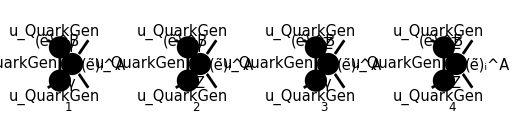

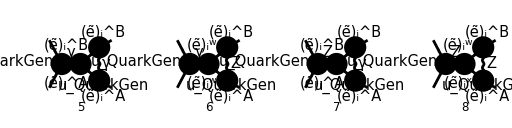

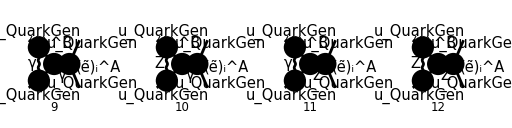

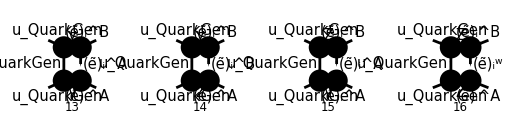

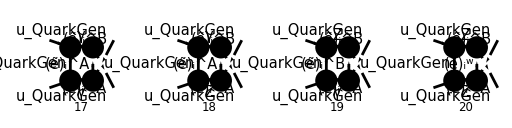

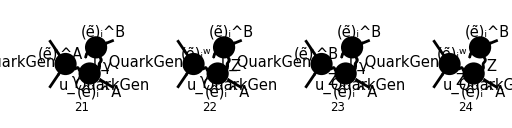

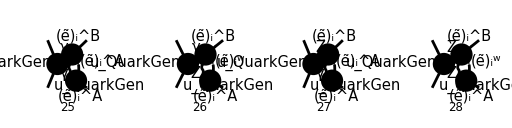

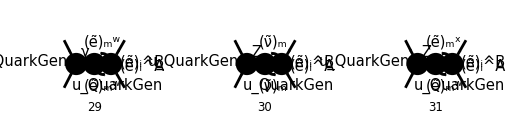

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{SelfEnergies,Tadpoles}],
{F[3,{QuarkGen}],-F[3,{QuarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
S[13|14],
F[11|12],
V[3]
}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

## 05.04

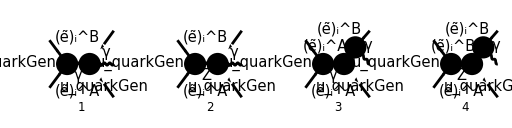

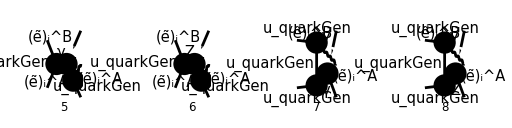

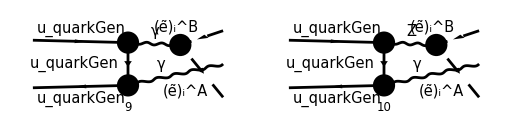

```mathematica
diags[0]=InsertFields[
CreateTopologies[0,2->3],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6]
}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k,k2},
LorentzIndexNames->{μ,ν,ρ,σ},
DropSumOver->True,
UndoChiralSplittings->True,
List->True,
SMP->True,
ChangeDimension->D
]/.{MQU[quarkGen]->0}
```

{-(2 ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) g^μρ (ε^*)^μ(k) g^νρ e^2)/(k+k_1+k_2)^2,(ⅈ (φ(-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) g^μρ (ε^*)^μ(k) g^νρ e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) (-k-2 k_1)^μ (ε^*)^μ(k) g^νρ (k+k_1-k_2)^ρ e^2)/((k+k_1+k_2)^2 ((-k-k_1)^2-m_l_iA^2)),(ⅈ (φ(-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-k-2 k_1)^μ (ε^*)^μ(k) g^νρ (k+k_1-k_2)^ρ e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((-k-k_1)^2-m_l_iB^2) ((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) (-k-2 k_2)^μ (ε^*)^μ(k) g^νρ (k-k_1+k_2)^ρ e^2)/((k+k_1+k_2)^2 ((k+k_2)^2-m_l_iA^2)),(ⅈ (φ(-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-k-2 k_2)^μ (ε^*)^μ(k) g^νρ (k-k_1+k_2)^ρ e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((k+k_2)^2-m_l_iA^2) ((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),((φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(γ·(k_1+k_2-p_2)).(-2/3 ⅈ γ^μ e).(φ(p_1)) IndexDelta(A,B) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e)/((k_1+k_2)^2 (-k_1-k_2+p_2)^2),-(((φ(-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(γ·(k_1+k_2-p_2)).(-2/3 ⅈ γ^μ e).(φ(p_1)) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 (-k_1-k_2+p_2)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),((φ(-p_2)).(-2/3 ⅈ γ^μ e δ_Col1Col2).(γ·(k-p_2)).(-2/3 ⅈ γ^ν e).(φ(p_1)) IndexDelta(A,B) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e)/((k_1+k_2)^2 (p_2-k)^2),-(((φ(-p_2)).(-2/3 ⅈ γ^μ e δ_Col1Col2).(γ·(k-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 (p_2-k)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))))}

### Quark amplitude

```mathematica
Mrqγ[0]=(Mlist[0][[{7,9}]]//Total)(3/2SMP["e_Q"])^2
```

9/4 e_Q^2 ((e (k_2-k_1)^ρ g^νρ (ε^*)^μ(k) IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(γ·(k-p_2)).(-2/3 ⅈ e γ^ν).(φ(p_1)))/((k_1+k_2)^2 (p_2-k)^2)+(e (k_2-k_1)^ρ g^νρ (ε^*)^μ(k) IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^ν δ_Col1Col2).(γ·(k_1+k_2-p_2)).(-2/3 ⅈ e γ^μ).(φ(p_1)))/((k_1+k_2)^2 (-k_1-k_2+p_2)^2))

```mathematica
MrqZ[0]=(Mlist[0][[{8,10}]]//Total//ZSimplify)3/2SMP["e_Q"]
```

(3 e e_Q (k_2-k_1)^ρ g^νρ (ε^*)^μ(k) Z_l_i^AB (((φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(γ·(k-p_2)).(2 ⅈ e (γ^ν.(γ̄)^7 Z_q_L+γ^ν.(γ̄)^6 Z_q_R))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/(p_2-k)^2+((φ(-p_2)).(2 ⅈ e δ_Col1Col2 (γ^ν.(γ̄)^7 Z_q_L+γ^ν.(γ̄)^6 Z_q_R))/((cos(θ_W)) (sin(θ_W))).(γ·(k_1+k_2-p_2)).(-2/3 ⅈ e γ^μ).(φ(p_1)))/(-k_1-k_2+p_2)^2))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-m_Z^2))

```mathematica
S[μ_,ρ_]:=GAD[μ].GSD[p1-k].GAD[ρ] FAD[p1-k]-GAD[ρ].GSD[p2-k].GAD[μ]FAD[p2-k];
```

```mathematica
MrqγHand[0]=SMP["e"]^3SMP["e_Q"]^2IndexDelta[A,B]FAD[k1+k2]SpinorVBarD[p2,0].S[μ,ρ].SpinorUD[p1,0] FVD[k1-k2,μ]ChangeDimension[Conjugate[PolarizationVector[k,ρ]],D]
```

(e^3 e_Q^2 (k_1-k_2)^μ (ε^*)^ρ(k) IndexDelta(A,B) v̄(p_2).((γ^μ.(γ·(p_1-k)).γ^ρ)/(p_1-k)^2-(γ^ρ.(γ·(p_2-k)).γ^μ)/(p_2-k)^2).u(p_1))/(k_1+k_2)^2

```mathematica
Γ5=Zql(1-GAD[5])+Zqr(1+GAD[5])
```

(1-(γ̄)^5) Z_q_L+((γ̄)^5+1) Z_q_R

```mathematica
MrqZHand[0]=-SMP["e"]^3SMP["e_Q"]ZliAB/(SMP["sin_W"]^2SMP["cos_W"]^2)FAD[{k1+k2,μZ}]SpinorVBarD[p2,0].S[μ,ρ].Γ5.SpinorUD[p1,0]FVD[k1-k2,μ]ChangeDimension[Conjugate[PolarizationVector[k,ρ]],D]
```

-(e^3 e_Q (k_1-k_2)^μ (ε^*)^ρ(k) Z_l_i^AB v̄(p_2).((γ^μ.(γ·(p_1-k)).γ^ρ)/(p_1-k)^2-(γ^ρ.(γ·(p_2-k)).γ^μ)/(p_2-k)^2).((1-(γ̄)^5) Z_q_L+((γ̄)^5+1) Z_q_R).u(p_1))/((cos(θ_W))^2 (sin(θ_W))^2 ((k_1+k_2)^2-μ_Z^2))

```mathematica
Mrq[0]=Mrqγ[0]+MrqZ[0]/.{SMP["m_Z"]->μZ}//FCE//ReplaceAll[#,{
FAD[-k1-k2+p2]->FAD[k-p1]
}]&//Contract
```

(3 e e_Q Z_l_i^AB ((4 e^2 δ_Col1Col2 (φ(-p_2)).(Z_q_L (γ·(k_2-k_1)).(γ̄)^7+Z_q_R (γ·(k_2-k_1)).(γ̄)^6).(γ·(k_1+k_2-p_2)).(γ·ε^*(k)).(φ(p_1)))/(3 (cos(θ_W)) (sin(θ_W)) (k-p_1)^2)+(4 e^2 δ_Col1Col2 (φ(-p_2)).(γ·ε^*(k)).(γ·(k-p_2)).(Z_q_L (γ·(k_2-k_1)).(γ̄)^7+Z_q_R (γ·(k_2-k_1)).(γ̄)^6).(φ(p_1)))/(3 (cos(θ_W)) (sin(θ_W)) (p_2-k)^2)))/(2 (cos(θ_W)) (sin(θ_W)) ((k_1+k_2)^2-μ_Z^2))+9/4 e_Q^2 (-(4 e^3 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k_2-k_1)).(γ·(k_1+k_2-p_2)).(γ·ε^*(k)).(φ(p_1)))/(9 (k_1+k_2)^2 (k-p_1)^2)-(4 e^3 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·ε^*(k)).(γ·(k-p_2)).(γ·(k_2-k_1)).(φ(p_1)))/(9 (k_1+k_2)^2 (p_2-k)^2))

```mathematica
MrqHand[0]=MrqγHand[0]+MrqZHand[0]//DiracSimplify//FullSimplify
FCCompareResults[{Mrq[0]},{MrqHand[0]}]
```

e^3 e_Q ((2 Z_l_i^AB ((Z_q_R (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(p_1-k)^2+(Z_q_L (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(p_1-k)^2-(Z_q_R (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(p_1-k)^2-(Z_q_L (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(p_1-k)^2-(2 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(p_1-k)^2-(2 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(p_1-k)^2+(2 Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(p_1-k)^2+(2 Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(p_1-k)^2-(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)))/(p_2-k)^2-(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)))/(p_2-k)^2+(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)))/(p_2-k)^2+(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)))/(p_2-k)^2+1/(p_2-k)^2 2 (Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))-Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))) (p_2·ε^*(k))))/(((k_1+k_2)^2-μ_Z^2) (cos(θ_W))^2 (sin(θ_W))^2)+1/(k_1+k_2)^2 IndexDelta(A,B) (-((φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(φ(p_1)))/(p_1-k)^2+((φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(φ(p_1)))/(p_1-k)^2+((φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1)))/(p_2-k)^2+2 ((φ(-p_2)).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(φ(p_1))) ((p_1·ε^*(k))/(p_1-k)^2-(p_2·ε^*(k))/(p_2-k)^2)) e_Q)

Check of the results: The results disagree.

False

```mathematica
Mrq[1]=Mrq[0]//FeynAmpDenominatorExplicit//FullSimplify
```

-((e^3 e_Q (IndexDelta(A,B) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (((φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(φ(p_1))-(φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(φ(p_1))+(φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) (k_1^2-2 (k_1·p_2)-k_2^2+2 (k_2·p_2))) (k^2-2 (k·p_2)+p_2^2)+(k^2-2 (k·p_1)+p_1^2) ((φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1))+2 ((φ(-p_2)).(γ·k_2).(φ(p_1))-(φ(-p_2)).(γ·k_1).(φ(p_1))) (p_2·ε^*(k)))) (cos(θ_W))^2 e_Q (sin(θ_W))^2+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2)-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2)+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) k_1^2 (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) k_1^2 (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k_1·p_2) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k_1·p_2) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) k_2^2 (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) k_2^2 (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_2)+p_2^2)+4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k_2·p_2) (k^2-2 (k·p_2)+p_2^2)+4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k_2·p_2) (k^2-2 (k·p_2)+p_2^2)-4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2) (p_2·ε^*(k))-4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2) (p_2·ε^*(k))+4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2) (p_2·ε^*(k))+4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2) (p_2·ε^*(k))) δ_Col1Col2)/((k_1^2+2 (k_1·k_2)+k_2^2) (-μ_Z^2+k_1^2+2 (k_1·k_2)+k_2^2) (k^2-2 (k·p_1)+p_1^2) (k^2-2 (k·p_2)+p_2^2) (cos(θ_W))^2 (sin(θ_W))^2))

```mathematica
MrqHand[1]=MrqHand[0]//FeynAmpDenominatorExplicit//FullSimplify
```

e^3 e_Q ((2 Z_l_i^AB ((Z_q_R (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(k^2-2 (k·p_1)+p_1^2)-(2 Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(k^2-2 (k·p_1)+p_1^2)-(2 Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(k^2-2 (k·p_1)+p_1^2)+(2 Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(k^2-2 (k·p_1)+p_1^2)+(2 Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(k^2-2 (k·p_1)+p_1^2)+1/(k^2-2 (k·p_2)+p_2^2)2 (Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))-Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))) (p_2·ε^*(k))+(Z_q_L (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(k^2-2 (k·p_1)+p_1^2)-(Z_q_R (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(k^2-2 (k·p_1)+p_1^2)-(Z_q_L (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(k^2-2 (k·p_1)+p_1^2)-(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)))/(k^2-2 (k·p_2)+p_2^2)-(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)))/(k^2-2 (k·p_2)+p_2^2)+(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)))/(k^2-2 (k·p_2)+p_2^2)+(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)))/(k^2-2 (k·p_2)+p_2^2)))/((-μ_Z^2+k_1^2+2 (k_1·k_2)+k_2^2) (cos(θ_W))^2 (sin(θ_W))^2)+1/(k_1^2+2 (k_1·k_2)+k_2^2)IndexDelta(A,B) (((φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1)))/(k^2-2 (k·p_2)+p_2^2)+1/(k^2-2 (k·p_1)+p_1^2)(-(φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(φ(p_1))+(φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(φ(p_1))+2 ((φ(-p_2)).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(φ(p_1))) (p_1·ε^*(k)))+(2 ((φ(-p_2)).(γ·k_2).(φ(p_1))-(φ(-p_2)).(γ·k_1).(φ(p_1))) (p_2·ε^*(k)))/(k^2-2 (k·p_2)+p_2^2)) e_Q)

```mathematica
FCCompareResults[{Mrq[1]},{MrqHand[1]}]
```

Check of the results: The results disagree.

False

```mathematica
SPD[k]=0;
SPD[p1]=0;
SPD[p2]=0;
```

```mathematica
Mrq[1]//DiracSimplify//Simplify
MrqHand[1]
```

-((e^3 e_Q (-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (k·p_1) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2+(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (k·p_1) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2-(φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2+(φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2+2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) (k_1·p_2) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2+(φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) k_2^2 (cos(θ_W))^2 e_Q (sin(θ_W))^2+(φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) k_1^2 (-μ_Z^2+k_1^2+2 (k_1·k_2)+k_2^2) (cos(θ_W))^2 e_Q (sin(θ_W))^2-2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) (k·p_2) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (k_2·p_2) (cos(θ_W))^2 e_Q (sin(θ_W))^2+2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (k·p_1) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (p_2·ε^*(k)) (cos(θ_W))^2 e_Q (sin(θ_W))^2-2 (φ(-p_2)).(γ·k_2).(φ(p_1)) IndexDelta(A,B) (k·p_1) (μ_Z^2-k_1^2-2 (k_1·k_2)-k_2^2) (p_2·ε^*(k)) (cos(θ_W))^2 e_Q (sin(θ_W))^2-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2)-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_1).(γ·k_2).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_2).(γ·k_1).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)-2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) k_1^2 (k_1^2+2 (k_1·k_2)+k_2^2)-2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) k_1^2 (k_1^2+2 (k_1·k_2)+k_2^2)+4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) (k_1·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)+4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) (k_1·p_2) (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) k_2^2 (k_1^2+2 (k_1·k_2)+k_2^2)+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) k_2^2 (k_1^2+2 (k_1·k_2)+k_2^2)-4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2) (k_2·p_2)-4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2) (k_2·p_2)+4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2) (p_2·ε^*(k))+4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2) (p_2·ε^*(k))-4 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2) (p_2·ε^*(k))-4 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k·p_1) (k_1^2+2 (k_1·k_2)+k_2^2) (p_2·ε^*(k))) δ_Col1Col2)/(2 (k·p_1) (k·p_2) (k_1^2+2 (k_1·k_2)+k_2^2) (-μ_Z^2+k_1^2+2 (k_1·k_2)+k_2^2) (cos(θ_W))^2 (sin(θ_W))^2))

e^3 e_Q ((2 Z_l_i^AB (-(Z_q_R (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(2 (k·p_1))+(Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(k·p_1)+(Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(k·p_1)-(Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (p_1·ε^*(k)))/(k·p_1)-(Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (p_1·ε^*(k)))/(k·p_1)-1/(k·p_2)(Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))-Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))) (p_2·ε^*(k))-(Z_q_L (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(2 (k·p_1))+(Z_q_R (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))/(2 (k·p_1))+(Z_q_L (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)))/(2 (k·p_1))+(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)))/(2 (k·p_2))+(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)))/(2 (k·p_2))-(Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)))/(2 (k·p_2))-(Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)))/(2 (k·p_2))))/((-μ_Z^2+k_1^2+2 (k_1·k_2)+k_2^2) (cos(θ_W))^2 (sin(θ_W))^2)+1/(k_1^2+2 (k_1·k_2)+k_2^2)IndexDelta(A,B) (-((φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1)))/(2 (k·p_2))-1/(2 (k·p_1))(-(φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(φ(p_1))+(φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(φ(p_1))+2 ((φ(-p_2)).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(φ(p_1))) (p_1·ε^*(k)))-(((φ(-p_2)).(γ·k_2).(φ(p_1))-(φ(-p_2)).(γ·k_1).(φ(p_1))) (p_2·ε^*(k)))/(k·p_2)) e_Q)

## 06.04

```mathematica
FCClearScalarProducts[];
SPD[p1]=0;
SPD[p2]=0;
SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(Q^2-m1^2-m2^2)/2;
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[x,{p1,p2,-k1,-k2,-k},{0,0,m1,m2,0}];
```

```mathematica
FCClearScalarProducts[];
SPD[p1]=0;
SPD[p2]=0;
SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(Q^2-m1^2-m2^2)/2;
SPD[p1,k]=xp1;
SPD[p2,k]=xp2;
SPD[k1,k]=x1;
SPD[k2,k]=x2;
SPD[p1,k1]=u;
MakeBoxes[xp1,TraditionalForm]:=SubscriptBox["x","p1"];
MakeBoxes[xp2,TraditionalForm]:=SubscriptBox["x","p2"];
```

```mathematica
DiracTrace[GSD[p2].GSD[k1-k2].GSD[k-p1].GSD[k+2k1].GSD[p1].GSD[k2]]
%//DiracSimplify//FullSimplify
%/.{
SPD[p1,k2]->SPD[p1,p2]-SPD[p1,k]-SPD[p1,k1],
SPD[p2,k1]->m1^2+SPD[k1,k2]+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(m1^2-m2^2)/2+SPD[k1,k]-SPD[p1,k]-SPD[p1,k1]
}//FullSimplify
```

tr((γ·p_2).(γ·(k_1-k_2)).(γ·(k-p_1)).(γ·(k+2 k_1)).(γ·p_1).(γ·k_2))

-2 (-m_1^2 (2 (x_p1 (m_2^2+2 (x_p1+x_p2-x_1)+Q^2)+u (-3 x_p1+2 x_p2+4 x_1-2 x_2)-6 u^2)+s (x_p1-2 x_p2+2 u+2 x_2))+m_2^2 (-2 (u (5 x_p1+2 x_p2+2 x_2)+2 x_p1 (x_p1-x_1)+2 u^2)+6 Q^2 x_p1+s (3 x_p1+6 u-2 x_1))+4 m_1^4 x_p1-6 m_2^4 x_p1+x_p1 (Q^2 (s-8 u+4 x_1)+2 s (5 u-3 x_1)-8 u (5 u-4 x_1+x_2))+4 x_p1^2 (s-8 u+3 x_1)-8 x_p1^3+2 (u-x_1) (Q^2 (s-4 u)+2 u (s-4 u+2 x_1-2 x_2)))

-2 (-m_1^2 (2 (x_p1 (m_2^2+2 (x_p1+x_p2-x_1)+Q^2)+u (-3 x_p1+2 x_p2+4 x_1-2 x_2)-6 u^2)+s (x_p1-2 x_p2+2 u+2 x_2))+m_2^2 (-2 (u (5 x_p1+2 x_p2+2 x_2)+2 x_p1 (x_p1-x_1)+2 u^2)+6 Q^2 x_p1+s (3 x_p1+6 u-2 x_1))+4 m_1^4 x_p1-6 m_2^4 x_p1+x_p1 (Q^2 (s-8 u+4 x_1)+2 s (5 u-3 x_1)-8 u (5 u-4 x_1+x_2))+4 x_p1^2 (s-8 u+3 x_1)-8 x_p1^3+2 (u-x_1) (Q^2 (s-4 u)+2 u (s-4 u+2 x_1-2 x_2)))

```mathematica
%/.{xp1->0,xp2->0,x1->0,x2->0}//FullSimplify
```

4 u (m_1^2 (s-6 u)+m_2^2 (2 u-3 s)-(Q^2+2 u) (s-4 u))

## 07.04

```mathematica
(4 Pi)^((d-3)/2)Gamma[(d-1)/2]
%//ReplaceAll[#,{d->4}]&
```

2^(d-3) π^((d-3)/2) (d-1)/2

π

```mathematica
Gamma[3/2]
```

(√π)/2

```mathematica
Hold[ 3Pi p^(d-4)/((d-1)(4Pi)^((d-3)/2)Gamma[(d-1)/2])]
%/.{d->4}//FRH
```

Hold[(3 π p^(d-4))/((d-1) (4 π)^((d-3)/2) (d-1)/2)]

1

## 08.04

```mathematica
SPD[2k2-q,q]FVD[k1,ρ]/(2SPD[k1,k])+SPD[2k1-q,q]FVD[k2,ρ]/(2SPD[k2,k])+FVD[q,ρ]
%//ReplaceAll[#,q->k1+k2+k]&//Together
```

(k_2^ρ ((2 k_1-q)·q))/(2 (k·k_2))+(k_1^ρ ((2 k_2-q)·q))/(2 (k·k_1))+q^ρ

1/(2 (k·k_1) (k·k_2))(k_1^ρ (k·k_2) ((-k-k_1+k_2)·(k+k_1+k_2))+k_2^ρ (k·k_1) ((-k+k_1-k_2)·(k+k_1+k_2))+2 (k+k_1+k_2)^ρ (k·k_1) (k·k_2))

```mathematica
K[μ_,ν_]:=FVD[k1,μ]FVD[k2,ν]/SPD[k2,k]+FVD[k2,μ]FVD[k1,ν]/SPD[k1,k]+MTD[μ,ν];
K[μ,ρ]K[ν,ρ]//Contract
SPD[k2]/SPD[k2,k]^2FVD[k1,μ]FVD[k1,ν]+SPD[k1]/SPD[k1,k]^2FVD[k2,μ]FVD[k2,ν]+MTD[μ,ν]+(SPD[k1,k2]/(SPD[k1,k]SPD[k2,k])+1/SPD[k1,k]+1/SPD[k2,k])(FVD[k1,μ]FVD[k2,ν]+FVD[k2,μ]FVD[k1,ν])
FCCompareResults[{%%},{%}]
```

(k_1^2 k_2^μ k_2^ν)/(k·k_1)^2+(k_2^2 k_1^μ k_1^ν)/(k·k_2)^2+g^μν+(k_2^μ k_1^ν (k_1·k_2))/((k·k_1) (k·k_2))+(k_1^μ k_2^ν (k_1·k_2))/((k·k_1) (k·k_2))+(k_2^μ k_1^ν)/(k·k_1)+(k_1^μ k_2^ν)/(k·k_1)+(k_2^μ k_1^ν)/(k·k_2)+(k_1^μ k_2^ν)/(k·k_2)

g^μν+(k_1^2 k_2^μ k_2^ν)/(k·k_1)^2+((k_1·k_2)/((k·k_1) (k·k_2))+1/(k·k_1)+1/(k·k_2)) (k_2^μ k_1^ν+k_1^μ k_2^ν)+(k_2^2 k_1^μ k_1^ν)/(k·k_2)^2

Check of the results: The results agree.

True

```mathematica
$Assumptions={
xm<x<xp,
z∈PositiveReals,
z<1
}
```

{x^-<x<x^+}

```mathematica
Integrate[((xp-x)(x-xm))^((d-4)/2),{x,xm,xp}]
```

ConditionalExpression[(√π 2^(3-d) (x^+-x^-)^(d-3) d/2-1)/((d-1)/2), Re(d)>2]

```mathematica
Integrate[(xp-x)^(a-1)(x-xm)^(b-1),{x,xm,xp}]
```

ConditionalExpression[(a b (x^+-x^-)^(a+b-1))/(a+b), x^->0∧Re(a)>0∧Re(b)>0]

```mathematica
1/Gamma[2-2ϵ]//Series[#,{ϵ,0,2}]&
```

1+(2-2 ℽ) ϵ+(4-4 ℽ+2 ℽ^2-π^2/3) ϵ^2+O(ϵ^3)

```mathematica
Integrate[(xp-x)^((d-2)/2)(x-xm)^((d-2)/2)/((z+x)^2(z-x)^2),{x,xm,xp}]
```

ConditionalExpression[1/(√π z^3)2^-d 3/2-d/2 d/2 (1/(d-2)(-1/((x^--z)^2))^(1-d/2) (-1/((x^+-z)^2))^(1-d/2) ((-1/((x^+-z)^2))^((d-2)/2) 2-d1-d/22-d/2(x^+-z)/(x^--z)-(-1/((x^--z)^2))^((d-2)/2) 2-d1-d/22-d/2(x^--z)/(x^+-z))-(2 (3-d) z (-1/((x^--z)^2))^(-d/2) (-1/((x^+-z)^2))^(-d/2) ((x^+-z) (-1/((x^+-z)^2))^((d-2)/2) 3-d1-d/23-d/2(x^+-z)/(x^--z)+(x^--z)^3 (-1/((x^--z)^2))^(d/2) 3-d1-d/23-d/2(x^--z)/(x^+-z)))/((d-4) (d-3) (x^--z)^3 (z-x^+)^3)-1/(d-2)(-1/((x^-+z)^2))^(1-d/2) (-1/((x^++z)^2))^(1-d/2) ((-1/((x^++z)^2))^((d-2)/2) 2-d1-d/22-d/2(x^++z)/(x^-+z)+(x^-+z)^2 (-1/((x^-+z)^2))^(d/2) 2-d1-d/22-d/2(x^-+z)/(x^++z))+(2 (3-d) z (-1/((x^-+z)^2))^(-d/2) (-1/((x^++z)^2))^(-d/2) ((x^++z) (-1/((x^++z)^2))^((d-2)/2) 3-d1-d/23-d/2(x^++z)/(x^-+z)+(x^-+z)^3 (-1/((x^-+z)^2))^(d/2) 3-d1-d/23-d/2(x^-+z)/(x^++z)))/((d-4) (d-3) (x^-+z)^3 (x^++z)^3)), ]

```mathematica
3Pi s^((d-4)/2)λ^((d-4)/2)μ^(4-d)/(2^(d-4)(d-1)2^(d-3)Pi^((d-3)/2)Gamma[(d-1)/2])
%/.{d->4}
```

(3 2^(7-2 d) π^((3-d)/2+1) λ^((d-4)/2) μ^(4-d) s^((d-4)/2))/((d-1) (d-1)/2)

1

```mathematica
Gamma[2]
```

1

```mathematica
3k^(d-4)Gamma[(d-2)/2]/((d-1)Pi^((d-4)/2)Gamma[d-2])//FullSimplify
3Pi k^(d-4)/((d-1)(4Pi)^((d-3)/2)Gamma[(d-1)/2])//FullSimplify
FCCompareResults[{%%},{%}]
```

(3 2^(2-d) π^(5/2-d/2) k^(d-4))/((d+1)/2)

(3 2^(2-d) π^(5/2-d/2) k^(d-4))/((d+1)/2)

Check of the results: The results agree.

True

```mathematica
8Pi α^2/(3 N s^(7/2))s^(3/2)λ^(3/2)/8 FqliAB 3Pi s^((d-4)/2)λ^((d-4)/2)μ^(4-d)/(2^(d-4)(d-1)2^(d-3)Pi^((d-3)/2)Gamma[(d-1)/2])
%//FullSimplify
```

(α^2 2^(7-2 d) π^((3-d)/2+2) FqliAB λ^((d-4)/2+3/2) μ^(4-d) s^((d-4)/2-2))/((d-1) N (d-1)/2)

(α^2 4^(3-d) π^(7/2-d/2) FqliAB λ^((d-1)/2) μ^(4-d) s^(d/2-4))/(N (d+1)/2)

```mathematica
Gamma[1-ϵ]
```

1-ϵ

```mathematica
(4Pi μ^2/s)^((4-d)/2)2^(4-d)/(λ^((d-1)/2)Gamma[(d-2)/2])
%/.{d->4-2ϵ}
%//Series[#,{ϵ,0,1}]&
```

(2^(8-2 d) π^((4-d)/2) λ^((1-d)/2) (μ^2/s)^((4-d)/2))/((d-2)/2)

(2^(8-2 (4-2 ϵ)) π^ϵ λ^(1/2 (2 ϵ-3)) (μ^2/s)^ϵ)/(1/2 (2-2 ϵ))

1/λ^(3/2)+(ϵ (log(λ)+log(μ^2/s)-ℽ+log(π)+4 log(2)))/λ^(3/2)+O(ϵ^2)

## 15.04

```mathematica
FCClearScalarProducts[];
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1,k2]=1/2 (s-m1^2-m2^2);
```

```mathematica
I1=FVD[k,μ]SPD[k-k1,k+k1+2k2]FAD[{k,m1},k+k1,{k+k1+k2,m2}];
I2=FVD[k+k1,μ]FAD[{k,m2},k+k2];
I3=-FVD[k-k1,μ]FAD[{k,m1},k+k1];
Itot[0]=(I1+I2+I3)/(I Pi^2)
Itot[1]=Itot[0]//TID[#,k,ToPaVe->True]&//FCE//ReplaceAll[#,{FVD[k2,μ]->FVD[q,μ]-FVD[k1,μ]}]&//Collect2[#,{FVD[_,_]},Factoring->FullSimplify,IsolateNames->KK]&
```

-(ⅈ (-(k-k_1)^μ/((k^2-m_1^2).(k+k_1)^2)+(k+k_1)^μ/((k^2-m_2^2).(k+k_2)^2)+(k^μ ((k-k_1)·(k+k_1+2 k_2)))/((k^2-m_1^2).(k+k_1)^2.((k+k_1+k_2)^2-m_2^2))))/π^2

1/2 KK(2034) q^μ-KK(2026) k_1^μ

```mathematica
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2a b-2a c-2b c;
```

```mathematica
toλRules={
((m1-m2)^2-s)((m1+m2)^2-s)->λ,
-2m1^2(m2^2+s)+(m2^2-s)^2+m1^4->λ,
2m1^2(m2^2-s)+2m2^2s+m1^4-3m2^4+s^2->λ+4m2^2(m1^2-m2^2+s),
2m1^2(m2^2+s)+(m2^2-s)^2-3m1^4->λ+4m1^2(-m1^2+m2^2+s)
};
```

toλRules are verified in the next cell (all lines give zero)

```mathematica
((m1-m2)^2-s)((m1+m2)^2-s)-Kallen[s,m1^2,m2^2]//Simplify;
2m1^2(m2^2-s)+2m2^2s+m1^4-3m2^4+s^2-(Kallen[s,m1^2,m2^2]+4m2^2(m1^2-m2^2+s))//Simplify;
-2m1^2(m2^2+s)+(m2^2-s)^2+m1^4-Kallen[s,m1^2,m2^2]//Simplify;
2m1^2(m2^2+s)+(m2^2-s)^2-3m1^4-(Kallen[s,m1^2,m2^2]+4m1^2(-m1^2+m2^2+s))//Simplify;
```

```mathematica
-KK[2026]//FRH//ReplaceAll[#,toλRules]&
```

-1/λ(2 (m_1^2+m_2^2-s) (2 s B_0(s,m_1^2,m_2^2)+λ C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2))+(λ+4 m_1^2 (-m_1^2+m_2^2+s)) B_0(m_1^2,0,m_1^2)+(λ+4 m_2^2 (m_1^2-m_2^2+s)) B_0(m_2^2,0,m_2^2))

## 16.04

```mathematica
(xp-x)(x-xm)/((1+x)^2(1-x)^2)
```

((x-x^-) (x^+-x))/((1-x)^2 (x+1)^2)

```mathematica
1/((1+x)(1-x))-2β1/((1+x)(1-x)^2)-2β2/((1+x)^2(1-x))
%//Apart[#,x]&
```

-(2 β_1)/((1-x)^2 (x+1))-(2 β_2)/((1-x) (x+1)^2)+1/((1-x) (x+1))

-β_1/(x-1)^2+(-β_1-β_2+1)/(2 (x+1))-β_2/(x+1)^2+(β_1+β_2-1)/(2 (x-1))

```mathematica
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2a b-2a c-2b c;
```

```mathematica
(1+xp)(1-xm)
%//ReplaceAll[#,{xm->-Sqrt[λ]-(β1-β2),xp->Sqrt[λ]-(β1-β2)}]&//FullSimplify
```

(1-x^-) (x^++1)

(β_1-β_2+√λ+1) (-β_1+β_2+√λ+1)

```mathematica
(1-xp)(1+xm)
%//ReplaceAll[#,{xm->-Sqrt[λ]-(β1-β2),xp->Sqrt[λ]-(β1-β2)}]&//FullSimplify
```

(x^-+1) (1-x^+)

(√λ-1)^2-(β_1-β_2)^2

```mathematica
(1+xp)(1+xm)//ReplaceAll[#,{xm->-Sqrt[λ]-(β1-β2),xp->Sqrt[λ]-(β1-β2)}]&//FullSimplify//ReplaceAll[#,{λ->Kallen[1,β1,β2]}]&//FullSimplify
```

4 β_2

```mathematica
(1-xp)(1-xm)//ReplaceAll[#,{xm->-Sqrt[λ]-(β1-β2),xp->Sqrt[λ]-(β1-β2)}]&//FullSimplify//ReplaceAll[#,{λ->Kallen[1,β1,β2]}]&//FullSimplify
```

4 β_1

```mathematica
((Sqrt[λ]+1)^2-(β1-β2)^2)/((Sqrt[λ]-1)^2-(β1-β2)^2)
```

((√λ+1)^2-(β_1-β_2)^2)/((√λ-1)^2-(β_1-β_2)^2)

```mathematica
λ-2Sqrt[λ]+1-(β1-β2)^2//ReplaceAll[#,{λ->Kallen[1,β1,β2]}]&//FullSimplify
```

-2 (β_1+β_2+√((β_1-1)^2+β_2^2-2 (β_1+1) β_2)-1)

```mathematica
(1+xp)(1-xm)//ReplaceAll[#,{xp->Sqrt[λ]-(β1-β2),xm->-Sqrt[λ]-(β1-β2)}]&
(1-xp)(1+xm)//ReplaceAll[#,{xp->Sqrt[λ]-(β1-β2),xm->-Sqrt[λ]-(β1-β2)}]&
```

(β_1-β_2+√λ+1) (-β_1+β_2+√λ+1)

(β_1-β_2-√λ+1) (-β_1+β_2-√λ+1)

```mathematica
(Sqrt[λ]-1)^2-(β1-β2)^2
%//ReplaceAll[#,{λ->Kallen[1,β1,β2]}]&//FullSimplify
```

(√λ-1)^2-(β_1-β_2)^2

-2 (β_1+β_2+√((β_1-1)^2+β_2^2-2 (β_1+1) β_2)-1)

```mathematica
((Sqrt[λ]+1)^2-(β1-β2)^2)((Sqrt[λ]-1)^2-(β1-β2)^2)
%//FullSimplify//ReplaceAll[#,{λ->Kallen[1,β1,β2]}]&//FullSimplify
```

((√λ-1)^2-(β_1-β_2)^2) ((√λ+1)^2-(β_1-β_2)^2)

16 β_1 β_2

```mathematica
((Sqrt[λ]-1)^2-(β1-β2)^2)^2//FullSimplify//ReplaceAll[#,{λ->Kallen[1,β1,β2]}]&//FullSimplify
```

4 (β_1+β_2+√((β_1-1)^2+β_2^2-2 (β_1+1) β_2)-1)^2

```mathematica
3Pi/((d-1)(4Pi)^((d-3)/2)Gamma[(d-1)/2])
%/.d->4
```

(3 2^(3-d) π^((3-d)/2+1))/((d-1) (d-1)/2)

1

```mathematica
Gamma[3/2]
```

(√π)/2

```mathematica
2^(1-d+2)Sqrt[Pi]Gamma[d-2]/Gamma[(d-2)/2]//FullSimplify
```

(d-1)/2

```mathematica
Gamma[1]
```

1

```mathematica
1/Gamma[1-ϵ]//Series[#,{ϵ,0,1}]&
```

1-ℽ ϵ+O(ϵ^2)

```mathematica
Pi α^2 μ^(4-d)/(N s^2) FqliAB (s/(4Pi))^((d-4)/2) λ^((d-1)/2)Gamma[(d-2)/2]/((d-1)Gamma[d-2])((d-2)/2 μ^(4-d))
%//ReplaceAll[#,{d->4}]&
```

(α^2 2^(3-d) (d-2) π^((4-d)/2+1) FqliAB λ^((d-1)/2) μ^(8-2 d) s^((d-4)/2-2) (d-2)/2)/((d-1) N d-2)

(π α^2 FqliAB λ^(3/2))/(3 N s^2)

```mathematica
Integrate[Log[1-x],{x,0,1}]
```

-1

```mathematica
Log[-x]
Re[%]+I Im[%]
%//Simplify[#,Assumptions->{x∈PositiveReals}]&
```

log(-x)

Re(log(-x))+ⅈ Im(log(-x))

log(x)+ⅈ π

## 17.04

```mathematica
rad[0]=σ α/Pi (16 Pi μ^2/Q^2)^ϵ λ^ϵ/Gamma[1-ϵ](1/λ^(3/2) (1-z)/z (xp-xm)+Irad)//ReplaceAll[#,{
xp->Sqrt[λz]-(β1-β2),
xm->-Sqrt[λz]-(β1-β2)
}]&
rad[1]=rad[0]//ReplaceAll[#,{Irad->-1/ϵ 1/λ^(1/2)DiracDelta[1-z]Iinf+1/λ^(1/2) DiracDelta[1-z]Iδ +PlusDistribution[1/(1-z)]2z^2/λ^(1/2)Ip}]&
rad[2]=rad[1]//ReplaceAll[#,{Iinf->-λ^(1/2)-(1-β1-β2)Log[(1-β1-β2-λ^(1/2))/(2Sqrt[β1 β2])]}]&
rad[3]=rad[2]//ReplaceAll[#,{
β1->m1^2/s,
β2->m2^2/s,
λ->λs/s^2
}]&//FullSimplify[#,Assumptions->s∈PositiveReals&&λ∈PositiveReals&&λs∈PositiveReals&&m1∈PositiveReals&&m2∈PositiveReals]&
```

(α σ 16^ϵ π^(ϵ-1) λ^ϵ (μ^2/Q^2)^ϵ (Irad+(2 √λz (1-z))/(λ^(3/2) z)))/(1-ϵ)

(α σ 16^ϵ π^(ϵ-1) λ^ϵ (μ^2/Q^2)^ϵ ((Iδ z-1)/(√λ)-(Iinf z-1)/(√λ ϵ)+(2 Ip (1/(1-z))_+ z^2)/(√λ)+(2 √λz (1-z))/(λ^(3/2) z)))/(1-ϵ)

(α σ 16^ϵ π^(ϵ-1) λ^ϵ (μ^2/Q^2)^ϵ ((Iδ z-1)/(√λ)-(z-1 (-((-β_1-β_2+1) log((-β_1-β_2-√λ+1)/(2 √(β_1 β_2))))-√λ))/(√λ ϵ)+(2 Ip (1/(1-z))_+ z^2)/(√λ)+(2 √λz (1-z))/(λ^(3/2) z)))/(1-ϵ)

(α σ 16^ϵ π^(ϵ-1) ((μ^2 λ_s)/(Q^2 s^2))^ϵ ((Iδ s z-1)/(√λ_s)+(z-1 (1-((m_1^2+m_2^2-s) log(-(m_1^2+m_2^2+√λ_s-s)/(2 m_1 m_2)))/(√λ_s)))/ϵ+(s (2 Ip z^3 (1/(1-z))_+ λ_s-2 √λz s^2 (z-1)))/(z λ_s^(3/2))))/(1-ϵ)

```mathematica
virt[0]=σ DiracDelta[1-z]α/Pi (-1/ϵ-1/ϵ (s-m1^2-m2^2)/λs^(1/2)Log[(s-m1^2-m2^2-λs^(1/2))/(2m1 m2)]+IvirtFin)
```

(α σ z-1 (IvirtFin-((-m_1^2-m_2^2+s) log((-m_1^2-m_2^2-√λ_s+s)/(2 m_1 m_2)))/(ϵ √λ_s)-1/ϵ))/π

```mathematica
full[0]=rad[3]+virt[0]//Series[#,{ϵ,0,0}]&//FullSimplify//Normal
full[1]=full[0]//Collect2[#,{DiracDelta,PlusDistribution},Factoring->FullSimplify,IsolateNames->KK]&
```

α σ (((Iδ s z-1)/(√λ_s)+(s (2 Ip z^3 (1/(1-z))_+ λ_s-2 √λz s^2 (z-1)))/(z λ_s^(3/2)))/π+(z-1 ((m_1^2+m_2^2-s) log(-(m_1^2+m_2^2+√λ_s-s)/(2 m_1 m_2))-√λ_s) (ℽ-log((16 π μ^2 λ_s)/(Q^2 s^2))))/(π √λ_s))+(α IvirtFin σ z-1)/π

KK(201) z-1+2 KK(206) (1/(1-z))_+-2 KK(207)

```mathematica
δnew=KK[201]//FRH//ReplaceAll[#,{
s->Q^2,
λs->λQ
}]&
```

(α σ ((Iδ Q^2)/(√λ_Q)+IvirtFin+(((m_1^2+m_2^2-Q^2) log(-(m_1^2+m_2^2-Q^2+√λ_Q)/(2 m_1 m_2))-√λ_Q) (ℽ-log((16 π μ^2 λ_Q)/Q^6)))/(√λ_Q)))/π

```mathematica
full[2]=δnew DiracDelta[1-z]+2KK[206]PlusDistribution[1/(1-z)]-2KK[207]//FRH//ReplaceAll[#,{λz->1/s^2 λQ}]&//FullSimplify[#,Assumptions->s∈PositiveReals&&λ∈PositiveReals&&λs∈PositiveReals&&m1∈PositiveReals&&m2∈PositiveReals]&
```

(α σ z-1 ((Iδ Q^2)/(√λ_Q)+IvirtFin+(((m_1^2+m_2^2-Q^2) log(-(m_1^2+m_2^2-Q^2+√λ_Q)/(2 m_1 m_2))-√λ_Q) (ℽ-log((16 π μ^2 λ_Q)/Q^6)))/(√λ_Q)))/π+(2 α s σ (Ip z^3 (1/(1-z))_+ λ_s-s (z-1) √λ_Q))/(π z λ_s^(3/2))

```mathematica
fullHand[0]=σ α/Pi (DiracDelta[1-z] IvirtFin+DiracDelta[1-z]Q^2/λQ^(1/2)Iδ+PlusDistribution[1/(1-z)]2z Q^2/λs^(1/2)Ip+2s^2λQ^(1/2)/λs^(3/2)(1-z)/z+DiracDelta[1-z](Log[16Pi μ^2/Q^2]+Log[λQ^(1/2)/Q^2]-EulerGamma)(1+(Q^2-m1^2-m2^2)/λQ^(1/2)Log[(Q^2-m1^2-m2^2-λQ^(1/2))/2m1 m2]))//FullSimplify[#,Assumptions->s∈PositiveReals&&λ∈PositiveReals&&λs∈PositiveReals&&m1∈PositiveReals&&m2∈PositiveReals]&
```

1/π α σ ((Iδ Q^2 z-1)/(√λ_Q)+IvirtFin z-1+z-1 (1-((m_1^2+m_2^2-Q^2) log(-1/2 m_1 m_2 (m_1^2+m_2^2-Q^2+√λ_Q)))/(√λ_Q)) (log((√λ_Q)/Q^2)+log((16 π μ^2)/Q^2)-ℽ)+(2 Ip Q^2 z^2 (1/(1-z))_+ λ_s-2 s^2 (z-1) √λ_Q)/(z λ_s^(3/2)))

```mathematica
FCCompareResults[{full[2]//Expand},{fullHand[0]//Expand}]
```

Check of the results: The results disagree.

False

```mathematica
full[2]//StandardForm
fullHand[0] Pi/(α σ)//Simplify
```

1/π α σ DiracDelta[-1+z] (IvirtFin+(Iδ Q^2)/(√λQ)+((-√λQ+(m1^2+m2^2-Q^2) Log[-(m1^2+m2^2-Q^2+√λQ)/(2 m1 m2)]) (EulerGamma-Log[(16 π λQ μ^2)/Q^6]))/(√λQ))+(2 s α σ (-s (-1+z) √λQ+Ip z^3 λs PlusDistribution[1/(1-z)]))/(π z λs^(3/2))

(Iδ Q^2 z-1)/(√λ_Q)+IvirtFin z-1+z-1 (1-((m_1^2+m_2^2-Q^2) log(-1/2 m_1 m_2 (m_1^2+m_2^2-Q^2+√λ_Q)))/(√λ_Q)) (log((√λ_Q)/Q^2)+log((16 π μ^2)/Q^2)-ℽ)+(2 Ip Q^2 z^2 (1/(1-z))_+ λ_s-2 s^2 (z-1) √λ_Q)/(z λ_s^(3/2))

```mathematica
((1+x)(1-x)-2β1(1+x)-2β2(1-x))/((1+x)^2(1-x)^2)
%//Apart[#,x]&
```

(-2 β_1 (x+1)-2 β_2 (1-x)+(1-x) (x+1))/((1-x)^2 (x+1)^2)

-β_1/(x-1)^2+(-β_1-β_2+1)/(2 (x+1))-β_2/(x+1)^2+(β_1+β_2-1)/(2 (x-1))

```mathematica
(xm-1)(xp-1)//ReplaceAll[#,{xp->Sqrt[λ]-(β1-β2),xm->-Sqrt[λ]-(β1-β2)}]&//FullSimplify//ReplaceAll[#,{λ->1+β1^2+β2^2-2(β1+β2)-2β1 β2}]&//FullSimplify
```

4 β_1

```mathematica
(xm+1)(xp+1)//ReplaceAll[#,{xp->Sqrt[λ]-(β1-β2),xm->-Sqrt[λ]-(β1-β2)}]&//FullSimplify//ReplaceAll[#,{λ->1+β1^2+β2^2-2(β1+β2)-2β1 β2}]&//FullSimplify
```

4 β_2

```mathematica
(xp+1)/(xm+1)//ReplaceAll[#,{xp->Sqrt[λ]-(β1-β2),xm->-Sqrt[λ]-(β1-β2)}]&//FullSimplify//Together
```

(β_1-β_2-√λ-1)/(β_1-β_2+√λ-1)

```mathematica
(xp+1)/(xm+1)//ReplaceAll[#,xpmRules]&//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify//Together
(1-xp)/(1-xm)//ReplaceAll[#,xpmRules]&//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify//Together
```

(β_1-β_2-√λ-1)/(β_1-β_2+√λ-1)

(β_1-β_2-√λ+1)/(β_1-β_2+√λ+1)

```mathematica
(1+xp)(1-xm)/((1-xp)(1+xm))//ReplaceAll[#,xpmRules]&//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify//Together
```

(2 (β_1+β_2-1))/(β_1+β_2+√λ-1)-1

```mathematica
(1+xm)(1-xm)/((1+xp)(1-xp))//ReplaceAll[#,xpmRules]&//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

((β_1-β_2+√λ-1) (β_1-β_2+√λ+1))/((-β_1+β_2+√λ)^2-1)

```mathematica
PolyLog[2,(xm-1)/(xp-1)]+I Pi Log[(xm-1)/(xp-1)]
%//Im//FullSimplify
```

2(x^--1)/(x^+-1)+ⅈ π log((x^--1)/(x^+-1))

0

```mathematica
(1+β1-β2)^2-λ//ReplaceAll[#,fromλRules]&//Simplify
```

4 β_1

```mathematica
-Integrate[Log[1-x]/x,{x,0,3/2}]
```

-22/3+π^2/3-(log^2(2))/2-ⅈ π log(3/2)+log(3) coth^-1(7)

```mathematica
(1-xm)(1+xp)/((1-xp)(1+xm))//ReplaceAll[#,xpmRules]&//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&
```

(β_1+β_2-√λ-1)/(β_1+β_2+√λ-1)

```mathematica
(1-xm)(1+xm)/((1-xp)(1+xp))//ReplaceAll[#,xpmRules]&//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

((β_1-β_2+√λ-1) (β_1-β_2+√λ+1))/((-β_1+β_2+√λ)^2-1)

```mathematica
1-(Sqrt[λ]+β2-β1)^2//ExpandAll//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

2 β_1 (2 β_2+√λ+1)-2 β_2 (β_2+√λ-1)-2 β_1^2

```mathematica
(1+β2-β1)^2-λ//ReplaceAll[#,fromλRules]&//FullSimplify
```

4 β_2

```mathematica
1-(Sqrt[λ]+β1-β2)^2
%//ReplaceAll[#,fromλRules]&//ReplaceAll[#,{β1->β,β2->β}]&//FullSimplify
```

1-(β_1-β_2+√λ)^2

4 β

```mathematica
(1+Sqrt[λ]+β1-β2)(1-Sqrt[λ]-β1+β2)//ReplaceAll[#,fromλRules]&//FullSimplify//Expand//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify//ReplaceAll[#,{-β1^2+2β2 β1+β1-β2^2+β2->λ-β1-β2-1}]&//FullSimplify
```

2 (β_2-β_1) √λ-2 (β_1+β_2+1)+2 λ

```mathematica
Log[(1+Sqrt[λ]+β1-β2)/(1-Sqrt[λ]-β1+β2)]//FullSimplify
```

log(-2/(β_1-β_2+√λ-1)-1)

```mathematica
(1+Sqrt[λ]+β1-β2)(1-Sqrt[λ]+β1-β2)//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify
```

4 β_1

```mathematica
(1-Sqrt[λ]-β1+β2)(1-Sqrt[λ]+β1-β2)//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

-2 (β_1+β_2+√λ-1)

```mathematica
(1+Sqrt[λ]+β1-β2)(1-Sqrt[λ]-β1+β2)//ReplaceAll[#,fromλRules]&//FullSimplify//Expand//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

2 ((β_2-β_1) √λ-β_1^2+2 β_2 β_1+β_1-β_2^2+β_2)

```mathematica
Log[(-β1+β2+Sqrt[λ]+1)/(-β1+β2-Sqrt[λ]+1)]
```

log((-β_1+β_2+√λ+1)/(-β_1+β_2-√λ+1))

log((2 (β_1-β_2-1))/(β_1-β_2+√λ-1)-1)

```mathematica
2(β1-β2-1)/(β1-β2+Sqrt[λ]-1)-1
```

(2 (β_1-β_2-1))/(β_1-β_2+√λ-1)-1

```mathematica
(1-β1+β2+Sqrt[λ])/(1-β1+β2-Sqrt[λ])//FullSimplify
```

(2 (β_1-β_2-1))/(β_1-β_2+√λ-1)-1

```mathematica
Log[4β2/(β1-β2+Sqrt[λ]-1)^2]
Log[4β2]-2Log[1-Sqrt[λ]-β1+β2]
%-%%//FullSimplify[#,Assumptions->λ∈PositiveReals&&β1∈PositiveReals&&β2∈PositiveReals]&
```

log((4 β_2)/(β_1-β_2+√λ-1)^2)

log(4 β_2)-2 log(-β_1+β_2-√λ+1)

log((β_1-β_2+√λ-1)^2)-2 log(-β_1+β_2-√λ+1)

```mathematica
(2Log[-β1+β2-Sqrt[λ]+1]+Log[4β2])Log[4β2/(β1-β2+Sqrt[λ]-1)^2]
Log[4β2]^2-4Log[1-Sqrt[λ]+β2-β1]^2
%%-%//PowerExpand//FullSimplify
```

(2 log(-β_1+β_2-√λ+1)+log(4 β_2)) log((4 β_2)/(β_1-β_2+√λ-1)^2)

log^2(4 β_2)-4 log^2(-β_1+β_2-√λ+1)

2 (2 log(-β_1+β_2-√λ+1)+log(β_2)+log(4)) (log(-β_1+β_2-√λ+1)-log(β_1-β_2+√λ-1))

```mathematica
(1-β1+β2-Sqrt[λ])/(1+β1-β2+Sqrt[λ])//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

-(β_1+β_2+√λ-1)/(2 β_1)

```mathematica
(1-β1+β2-Sqrt[λ])(1+β1-β2+Sqrt[λ])//Expand//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

2 ((β_2-β_1) √λ-β_1^2+2 β_2 β_1+β_1-β_2^2+β_2)

```mathematica
1-(Sqrt[λ]+β1-β2)^2//ReplaceAll[#,fromλRules]&//ExpandAll//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

-2 (β_1 (-2 β_2+√λ-1)+β_2 (β_2-√λ-1)+β_1^2)

```mathematica
(1+xp)/(1+xm)
%//ReplaceAll[#,xpmRules]&//ReplaceAll[#,logRules]&
```

(x^++1)/(x^-+1)

(4 β_2)/(β_1-β_2+√λ-1)^2

```mathematica
(Log[4β2]-2Log[1-Sqrt[λ]-β1+β2])^2
%//ExpandAll
```

(log(4 β_2)-2 log(-β_1+β_2-√λ+1))^2

4 log^2(-β_1+β_2-√λ+1)-4 log(4 β_2) log(-β_1+β_2-√λ+1)+log^2(4 β_2)

```mathematica
PolyLog[2,(1+xp)/(1+xm)]+(PolyLog[2,(1+xm)/(1+xp)]+Log[(1+xp)/(1+xm)]^2/2-Pi^2/3+I Pi Log[(1+xp)/(1+xm)])//FullSimplify
```

0

```mathematica
(1+xm)(1-xp)/((1+xp)(1-xm))//ReplaceAll[#,xpmRules]&//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//ReplaceAll[#,logRules]&//FullSimplify
```

(β_1+β_2+√λ-1)^2/(4 β_1 β_2)

```mathematica
PolyLog[2,(1+xp)/(1+xm)]+PolyLog[2,(1-xm)/(1-xp)]
%//ReplaceAll[#,xpmRules]&//ReplaceAll[#,{β1->β,β2->β}]&
```

2(1-x^-)/(1-x^+)+2(x^++1)/(x^-+1)

2 2(√λ+1)/(1-√λ)

```mathematica
1-(1-xm)/(1-xp)//ReplaceAll[#,xpmRules]&//Expand//ReplaceAll[#,logRules]&//FullSimplify
```

2/((-β_1+β_2-1)/(√λ)+1)

```mathematica
(1+xp)/(1+xm)//ReplaceAll[#,xpmRules]&//ReplaceAll[#,logRules]&
```

(4 β_2)/(β_1-β_2+√λ-1)^2

```mathematica
(1+xm)/(1+xp)//ReplaceAll[#,xpmRules]&//ReplaceAll[#,logRules]&
```

(β_1-β_2+√λ-1)^2/(4 β_2)

```mathematica
(Log[4β2]-2Log[1-Sqrt[λ]-β1+β2])^2//Expand
```

4 log^2(-β_1+β_2-√λ+1)-4 log(4 β_2) log(-β_1+β_2-√λ+1)+log^2(4 β_2)

```mathematica
(1+Sqrt[λ]+β1-β2)(1-Sqrt[λ]-β1+β2)//Expand//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

2 ((β_2-β_1) √λ-β_1^2+2 β_2 β_1+β_1-β_2^2+β_2)

```mathematica
(1-xp)/(1-xm)//ReplaceAll[#,xpmRules]&//ReplaceAll[#,logRules]&//FullSimplify
```

(-β_1+β_2+√λ-1)^2/(4 β_1)

```mathematica
1-(1-xp)/(1-xm)//FullSimplify//ReplaceAll[#,xpmRules]&//ReplaceAll[#,logRules]&//FullSimplify
```

(2 √λ)/(β_1-β_2+√λ+1)

```mathematica
(1+xm)(1-xm)/((1+xp)(1-xp))//ReplaceAll[#,xpmRules]&//ReplaceAll[#,logRules]&
```

((β_1-β_2+√λ-1)^2 (β_1-β_2+√λ+1))/(4 β_2 (β_1-β_2-√λ+1))

```mathematica
(1+xm)(1-xm)/((1+xp)(1-xp))
%//ReplaceAll[#,xpmRules]&//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify//ExpandAll//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

((1-x^-) (x^-+1))/((1-x^+) (x^++1))

(2 (β_1^2-(2 β_2+1) β_1+(β_2-1) β_2))/(-β_1 (2 β_2+√λ+1)+β_2 (β_2+√λ-1)+β_1^2)-1

```mathematica
(1+xm)(1-xp)/((1+xp)(1-xm))//ReplaceAll[#,xpmRules]&//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//ReplaceAll[#,logRules]&//FullSimplify
```

(β_1+β_2+√λ-1)^2/(4 β_1 β_2)

```mathematica
(1+xp)/(1+xm)//ReplaceAll[#,xpmRules]&//ReplaceAll[#,logRules]&
```

(4 β_2)/(β_1-β_2+√λ-1)^2

```mathematica
(1-xm)/(1-xp)//ReplaceAll[#,xpmRules]&//ReplaceAll[#,logRules]&
```

(4 β_1)/(-β_1+β_2+√λ-1)^2

```mathematica
(1-Sqrt[λ]+β1-β2)(1-Sqrt[λ]-β1+β2)//Expand//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

-2 (β_1+β_2+√λ-1)

```mathematica
(1-Sqrt[λ]+β1-β2)/(1-Sqrt[λ]-β1+β2)
```

(β_1-β_2-√λ+1)/(-β_1+β_2-√λ+1)

```mathematica
(1-Sqrt[λ]+β1-β2)(1-Sqrt[λ]-β1+β2)//Expand//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

-2 (β_1+β_2+√λ-1)

```mathematica
(1-xm xp)//ReplaceAll[#,xpmRules]&//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify
```

-2 (β_1+β_2-1)

```mathematica
(1+Sqrt[λ]+β1-β2)/(1-Sqrt[λ]-β1+β2)//ReplaceAll[#,logRules]&
```

(β_1-β_2+√λ+1)/(-β_1+β_2-√λ+1)

```mathematica
(1+Sqrt[λ]+β1-β2)(1-Sqrt[λ]-β1+β2)//ReplaceAll[#,fromλRules]&//Expand//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

2 ((β_2-β_1) √λ-β_1^2+2 β_2 β_1+β_1-β_2^2+β_2)

```mathematica
(1-Sqrt[λ]+β1-β2)/(1-Sqrt[λ]-β1+β2)//ReplaceAll[#,logRules]&
```

(β_1-β_2-√λ+1)/(-β_1+β_2-√λ+1)

```mathematica
(1-Sqrt[λ]+β1-β2)(1-Sqrt[λ]-β1+β2)//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&
```

-2 (β_1+β_2+√λ-1)

```mathematica
(1+xp)/(1+xm)//ReplaceAll[#,xpmRules]&//ReplaceAll[#,logRules]&
```

(4 β_2)/(β_1-β_2+√λ-1)^2

```mathematica
(1+Sqrt[λ]+β1-β2)(1-Sqrt[λ]-β1+β2)//Expand//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify//ReplaceAll[#,-β1^2+2β1 β2+β1-β2^2+β2->-λ-β1-β2]&//FullSimplify
```

-2 ((β_1-β_2) √λ+β_1+β_2+λ)

```mathematica
(1-xm)//ReplaceAll[#,xpmRules]&
```

β_1-β_2+√λ+1

```mathematica
1+xm//ReplaceAll[#,xpmRules]&
```

-β_1+β_2-√λ+1

## 21.04

```mathematica
SetMandelstam[x,{p1,p2,-k1,-k2,-k},{0,0,m1,m2,0}];
```

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(s z-m1^2-m2^2)/2;
SPD[p1,k]=s(1-z)(1-y)/2;
SPD[p2,k]=s(1-z)y/2;
SPD[k1,k]=s(1-z)/(4z)(z-x);
SPD[k2,k]=s(1-z)/(4z)(z+x);
SPD[p1,k2]=SPD[p1,p2]-SPD[p1,k]-SPD[p1,k1];
SPD[p2,k1]=m1^2+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1];
SPD[p2,k2]=(m1^2-m2^2)/2+SPD[k1,k]-SPD[p1,k]-SPD[p1,k1];
```

```mathematica
trace1[0]=1/SPD[p1-k] DiracTrace[GSD[p2].GSD[k1-k2].GSD[p1-k].GAD[ρ].GSD[p1].GAD[ν]]
trace2[0]=1/SPD[p2-k]DiracTrace[GSD[p2].GAD[ρ].GSD[p2-k].GSD[k1-k2].GSD[p1].GAD[ν]]
```

(tr((γ·p_2).(γ·(k_1-k_2)).(γ·(p_1-k)).γ^ρ.(γ·p_1).γ^ν))/(p_1-k)^2

(tr((γ·p_2).γ^ρ.(γ·(p_2-k)).(γ·(k_1-k_2)).(γ·p_1).γ^ν))/(p_2-k)^2

```mathematica
trace1[1]=trace1[0]//DiracSimplify//ExpandScalarProduct//FullSimplify
```

1/(s (y-1) (z-1) z)(2 (s y p_1^ν k^ρ z^2-s p_2^ν k^ρ z^2+s y p_2^ν k^ρ z^2+s y p_1^ν k_1^ρ z^2+s p_2^ν k_1^ρ z^2-s y p_2^ν k_1^ρ z^2-s y p_1^ν k_2^ρ z^2-s p_2^ν k_2^ρ z^2+s y p_2^ν k_2^ρ z^2+s y k^ν p_1^ρ z^2-2 s y p_1^ν p_1^ρ z^2+2 s p_2^ν p_1^ρ z^2-2 s y p_2^ν p_1^ρ z^2+s k^ν p_2^ρ z^2-s y k^ν p_2^ρ z^2+s p_1^ν k^ρ z-s y p_1^ν k^ρ z-s y p_2^ν k^ρ z+s k^ν k_1^ρ z-s y p_1^ν k_1^ρ z-s p_2^ν k_1^ρ z+s y p_2^ν k_1^ρ z-s k^ν k_2^ρ z+s y p_1^ν k_2^ρ z+s p_2^ν k_2^ρ z-s y p_2^ν k_2^ρ z+s k^ν p_1^ρ z-s y k^ν p_1^ρ z-2 s p_1^ν p_1^ρ z+2 s y p_1^ν p_1^ρ z+s x p_2^ν p_1^ρ z+2 s y p_2^ν p_1^ρ z+s y k^ν p_2^ρ z+s x p_1^ν p_2^ρ z+s k_2^ν (k^ρ+(-z y+y-2) p_1^ρ-(y-1) (z-1) p_2^ρ) z+s k_1^ν (-k^ρ+(y (z-1)+2) p_1^ρ+(y-1) (z-1) p_2^ρ) z+4 (p_2^ν (k^ρ-2 p_1^ρ)-k^ν p_2^ρ) (k_1·p_1) z-s x p_2^ν p_1^ρ-s x p_1^ν p_2^ρ)-s (z-1) g^νρ (s (x+(2 (y-1) y (z-1)-1) z)+4 y z (k_1·p_1)))

```mathematica
trace2[1]=trace2[0]//DiracSimplify//ExpandScalarProduct//FullSimplify
```

1/(s y (z-1) z)(s (z-1) g^νρ (s (x+z+2 y z (-z y+y+z-1))-4 y z (k_1·p_1))+2 (-s y p_1^ν k^ρ z^2+s p_2^ν k^ρ z^2-s y p_2^ν k^ρ z^2-s y p_1^ν k_1^ρ z^2-s p_2^ν k_1^ρ z^2+s y p_2^ν k_1^ρ z^2+s y p_1^ν k_2^ρ z^2+s p_2^ν k_2^ρ z^2-s y p_2^ν k_2^ρ z^2+s y k^ν p_1^ρ z^2+s k^ν p_2^ρ z^2-s y k^ν p_2^ρ z^2+2 s y p_1^ν p_2^ρ z^2-2 s p_2^ν p_2^ρ z^2+2 s y p_2^ν p_2^ρ z^2-s p_1^ν k^ρ z+s y p_1^ν k^ρ z+s y p_2^ν k^ρ z-s k^ν k_1^ρ z+s y p_1^ν k_1^ρ z+s p_2^ν k_1^ρ z-s y p_2^ν k_1^ρ z+s k^ν k_2^ρ z-s y p_1^ν k_2^ρ z-s p_2^ν k_2^ρ z+s y p_2^ν k_2^ρ z+s k^ν p_1^ρ z-s y k^ν p_1^ρ z-s x p_2^ν p_1^ρ z+s y k^ν p_2^ρ z+2 s p_1^ν p_2^ρ z-s x p_1^ν p_2^ρ z-2 s y p_1^ν p_2^ρ z-2 s y p_2^ν p_2^ρ z+s k_1^ν (k^ρ+y (z-1) p_1^ρ+(-y+(y-1) z-1) p_2^ρ) z+s k_2^ν (-k^ρ-y (z-1) p_1^ρ+(-z y+y+z+1) p_2^ρ) z-4 (p_2^ν k^ρ+(k^ν-2 p_2^ν) p_2^ρ) (k_1·p_1) z+s x p_2^ν p_1^ρ+s x p_1^ν p_2^ρ))

```mathematica
T1[μ_,ρ_]:=FVD[k+k1-k2,μ]FVD[k+2k1,ρ]/(SPD[k+k1]-m1^2)
T2[μ_,ρ_]:=FVD[k1+k2-k1,μ]FVD[k+2k2,ρ]/(SPD[k+k2]-m2^2)
```

```mathematica
genTrace[p1_,p2_,k1_,k2_]:=DiracTrace[GSD[p2].GSD[k1-k2].GSD[k-p1].GSD[k+2k1].GSD[p1].GSD[k2]]/(SPD[p1-k](SPD[k+k1]-SPD[k1]))
```

```mathematica
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
```

```mathematica
traceRes[p1_,p2_,k1_,k2_]:=genTrace[p1,p2,k1,k2]//DiracSimplify//FullSimplify//ExpandScalarProduct//FullSimplify
```

```mathematica
res[0]=traceRes[p1,p2,k1,k2]+traceRes[p2,p1,k1,k2]+traceRes[p1,p2,k2,k1]+traceRes[p2,p1,k2,k1]//FullSimplify
```

1/((k·k_1) (k·k_2) (k·p_1) (k·p_2))(-(((k·p_2) (m_2^2 s-4 (k_1·p_2) (k_2·p_1))+(k·p_1) (m_2^2 s-4 (k_1·p_1) (k_2·p_2))) (k·k_1)^2)+(2 ((m_2^2 (k_1·p_2)-m_1^2 (k_2·p_2)) (k·p_1)^2+((k_2·p_2) (s m_1^2-s (k_1·k_2)+2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1) (k_2·p_2-2 (k_1·p_2)))+(k·p_2) ((s+k_2·p_1+k_2·p_2) m_1^2-(k_1·k_2) (s+2 (k_1·p_1)+2 (k_1·p_2))+(k_1·p_2) (m_2^2+2 (k_2·p_1))+(k_1·p_1) (m_2^2-4 (k_1·p_2)+2 (k_2·p_2)))) (k·p_1)+(k·p_2) ((k·p_2) (m_2^2 (k_1·p_1)-m_1^2 (k_2·p_1))+(k_2·p_1) (s m_1^2-s (k_1·k_2)+2 (k_1·p_2) (k_2·p_1-2 (k_1·p_1))+2 (k_1·p_1) (k_2·p_2))))-(k·k_2) (k·p_1+k·p_2) ((m_1^2+m_2^2) s-4 (k_1·k_2) s-4 (k_1·p_1) (k_1·p_2-2 (k_2·p_2))+4 (k_2·p_1) (2 (k_1·p_2)-k_2·p_2))) (k·k_1)+(k·k_2) (2 ((m_1^2 (k_2·p_2)-m_2^2 (k_1·p_2)) (k·p_1)^2+((k_1·p_2) (s m_2^2-s (k_1·k_2)+2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1-2 (k_2·p_1)) (k_2·p_2))+(k·p_2) ((k_2·p_1+k_2·p_2) m_1^2+m_2^2 s+(k_1·p_2) (m_2^2+2 (k_2·p_1))-4 (k_2·p_1) (k_2·p_2)+(k_1·p_1) (m_2^2+2 (k_2·p_2))-(k_1·k_2) (s+2 (k_2·p_1)+2 (k_2·p_2)))) (k·p_1)+(k·p_2) ((k·p_2) (k_2·p_1) m_1^2+(k_1·p_1) (s m_2^2-(k·p_2) m_2^2-s (k_1·k_2)+2 (k_2·p_1) (k_1·p_2-2 (k_2·p_2)))+2 (k_1·p_1)^2 (k_2·p_2)))-(k·k_2) ((k·p_1) (m_1^2 s-4 (k_1·p_2) (k_2·p_1))+(k·p_2) (m_1^2 s-4 (k_1·p_1) (k_2·p_2)))))

```mathematica
SPD[k1,k2]=(s z-m1^2-m2^2)/2;
```

```mathematica
resNum[0]=res[0]//Numerator//FullSimplify
```

-(((k·p_2) (m_2^2 s-4 (k_1·p_2) (k_2·p_1))+(k·p_1) (m_2^2 s-4 (k_1·p_1) (k_2·p_2))) (k·k_1)^2)+(2 (m_2^2 (k_1·p_2)-m_1^2 (k_2·p_2)) (k·p_1)^2+((k_2·p_2) (s (3 m_1^2+m_2^2-s z)+4 (k_1·p_2) (k_2·p_1)+4 (k_1·p_1) (k_2·p_2-2 (k_1·p_2)))+(k·p_2) (2 (k_2·p_1+k_2·p_2) m_1^2+s (3 m_1^2+m_2^2-s z)+2 (k_1·p_2) (m_1^2+2 m_2^2-s z+2 (k_2·p_1))+2 (k_1·p_1) (m_1^2+2 m_2^2-s z-4 (k_1·p_2)+2 (k_2·p_2)))) (k·p_1)-(k·k_2) (k·p_1+k·p_2) (s (3 (m_1^2+m_2^2)-2 s z)-4 (k_1·p_1) (k_1·p_2-2 (k_2·p_2))+4 (k_2·p_1) (2 (k_1·p_2)-k_2·p_2))+(k·p_2) (2 (k·p_2) (m_2^2 (k_1·p_1)-m_1^2 (k_2·p_1))+(k_2·p_1) (s (3 m_1^2+m_2^2-s z)+4 (k_1·p_2) (k_2·p_1)+4 (k_1·p_1) (k_2·p_2-2 (k_1·p_2))))) (k·k_1)+(k·k_2) (2 (m_1^2 (k_2·p_2)-m_2^2 (k_1·p_2)) (k·p_1)^2+((k_1·p_2) (s (m_1^2+3 m_2^2-s z)+4 (k_1·p_2) (k_2·p_1)+4 (k_1·p_1-2 (k_2·p_1)) (k_2·p_2))+(k·p_2) (s (m_1^2+3 m_2^2-s z)+2 (2 m_1^2+m_2^2-s z) (k_2·p_1)+2 (k_1·p_2) (m_2^2+2 (k_2·p_1))+2 (2 m_1^2+m_2^2-s z-4 (k_2·p_1)) (k_2·p_2)+2 (k_1·p_1) (m_2^2+2 (k_2·p_2)))) (k·p_1)+(k·p_2) (2 (k·p_2) (k_2·p_1) m_1^2+(k_1·p_1) (-2 (k·p_2) m_2^2+s (m_1^2+3 m_2^2-s z)+4 (k_2·p_1) (k_1·p_2-2 (k_2·p_2)))+4 (k_1·p_1)^2 (k_2·p_2))-(k·k_2) ((k·p_1) (m_1^2 s-4 (k_1·p_2) (k_2·p_1))+(k·p_2) (m_1^2 s-4 (k_1·p_1) (k_2·p_2))))

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(s z-m1^2-m2^2)/2;
```

```mathematica
DiracTrace[GSD[p2].GSD[k1-k2].GSD[k-p1].GSD[k+2k1].GSD[p1].GSD[k2]]//ReplaceAll[#,k2->p1+p2-k1-k]&//DiracSimplify//FullSimplify
%//ReplaceAll[#,{m1->0,m2->0}]&
```

-1/(2 z^2)(4 (k_1·p_1) (8 z (k_1·p_1) (4 z (k_1·p_1)+2 (m_2^2-m_1^2) z-2 s x (z-1)+s z (4 y (z-1)-3 z+1))+s (4 z (m_1^2 (x (z-1)+z (y (-z)+y+z+1))-m_2^2 (z-1) (x+(2-3 y) z))+s (z-1) (2 x^2 (z-1)+2 x z (-5 y z+5 y+4 z-1)+z^2 (y (10 y (z-1)-17 z+5)+7 z-1))))+s (z-1) (2 s z (m_2^2 (y-1) (z-1) (-2 x+5 y z-3 z)-m_1^2 (2 x+z (y (-3 y z+3 y+2 z-6)+z+1)))-8 m_1^2 (m_1-m_2) (m_1+m_2) (y-1) z^2+s^2 (z-1) (-2 x^2 y-z^2 (5 x (y-1)^2+y^2 (4 y-3)+y)+x z (2 x (y-1)+y (5 y-1))+(y-1) (y (4 y-9)+3) z^3)))

-1/(2 z^2)(4 (k_1·p_1) (8 z (k_1·p_1) (4 z (k_1·p_1)-2 s x (z-1)+s z (4 y (z-1)-3 z+1))+s^2 (z-1) (2 x^2 (z-1)+2 x z (-5 y z+5 y+4 z-1)+z^2 (y (10 y (z-1)-17 z+5)+7 z-1)))+s^3 (z-1)^2 (-2 x^2 y-z^2 (5 x (y-1)^2+y^2 (4 y-3)+y)+x z (2 x (y-1)+y (5 y-1))+(y-1) (y (4 y-9)+3) z^3))

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
```

```mathematica
SPD[k1,k]DiracTrace[GSD[p2,k1,p1,k2]]
%//ReplaceAll[#,k2->p1+p2-k1-k]&//DiracSimplify//FullSimplify
```

(k·k_1) tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2))

4 (k·k_1) ((p_1·p_2) (k·k_1+m_1^2)-(k·p_2) (k_1·p_1)-(k·p_1+2 (k_1·p_1)) (k_1·p_2))

```mathematica
DiracTrace[GSD[p2,k1-k2,k-p1,k+2k1,p1,k2]]
%//DiracSimplify//FullSimplify//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]},Factoring->FullSimplify,IsolateNames->KK]&
```

tr((γ·p_2).(γ·(k_1-k_2)).(γ·(k-p_1)).(γ·(k+2 k_1)).(γ·p_1).(γ·k_2))

-8 KK(1769) (k·p_1)+8 KK(1765) (k·k_1)+8 KK(1775)

```mathematica
KK[1769]//FRH
```

(k_1·p_2) (k_2·p_1+m_2^2)+(k_2·p_2) (k_1·p_1-2 (k_2·p_1)-2 (k_1·k_2)+m_1^2)+(p_1·p_2) (m_2^2-k_1·k_2)

## 22.04

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
```

```mathematica
DiracTrace[GSD[p2,k1,p1,k2]]
%//DiracSimplify//FullSimplify
```

tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2))

4 ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-(k_1·k_2) (p_1·p_2))

```mathematica
DiracTrace[GSD[p2,k1,p1,k2]]//ReplaceAll[#,k2->p1+p2-k1-k]&
%//DiracSimplify//FullSimplify
%//FCE//ReplaceAll[#,{
SPD[p1,k]->SPD[p1,p2]-SPD[p1,k]-SPD[p1,k1],
SPD[p2,k1]->SPD[k1]+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(SPD[k1]-SPD[k2])/2+SPD[k1,k]-SPD[p1,k]-SPD[p1,k1]
}]&//FullSimplify
```

tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·(-k-k_1+p_1+p_2)))

4 (p_1·p_2) (k·k_1+m_1^2)-4 (k·p_2) (k_1·p_1)-4 (k·p_1+2 (k_1·p_1)) (k_1·p_2)

4 (p_1·p_2) (k·k_1+m_1^2)-4 (-(k·p_1)+k_1·p_1+p_1·p_2) (-k_1·p_1+k·k_1+k_1·k_2+m_1^2)-4 (k·p_2) (k_1·p_1)

```mathematica
DiracTrace[GSD[p2,k1,p1,k2]]
%//DiracSimplify//FullSimplify
%//FCE//ReplaceAll[#,{
SPD[p1,k]->SPD[p1,p2]-SPD[p1,k]-SPD[p1,k1],
SPD[p2,k1]->SPD[k1]+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(SPD[k1]-SPD[k2])/2+SPD[k1,k]-SPD[p1,k]-SPD[p1,k1]
}]&//FullSimplify
```

tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2))

4 ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-(k_1·k_2) (p_1·p_2))

2 (k_1·p_1) (-2 (k·p_1)-2 (k_1·p_1)+2 (k·k_1)+m_1^2-m_2^2)+4 (k_2·p_1) (-k_1·p_1+k·k_1+k_1·k_2+m_1^2)-4 (k_1·k_2) (p_1·p_2)

```mathematica
DiracTrace[GSD[p2,k,p1,k2]]//ReplaceAll[#,k2->p1+p2-k1-k]&
%//DiracSimplify//FullSimplify
%//FCE//ReplaceAll[#,{
SPD[p1,k]->SPD[p1,p2]-SPD[p1,k]-SPD[p1,k1],
SPD[p2,k1]->SPD[k1]+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(SPD[k1]-SPD[k2])/2+SPD[k1,k]-SPD[p1,k]-SPD[p1,k1]
}]&//FullSimplify
```

tr((γ·p_2).(γ·k).(γ·p_1).(γ·(-k-k_1+p_1+p_2)))

-4 ((k·p_2) (k_1·p_1)+(k·p_1) (2 (k·p_2)+k_1·p_2)-(k·k_1) (p_1·p_2))

4 (k·p_1+k_1·p_1-p_1·p_2) (2 (k·p_2)-k_1·p_1+k·k_1+k_1·k_2+m_1^2)-4 (k·p_2) (k_1·p_1)+4 (k·k_1) (p_1·p_2)

```mathematica
top1k1Rules={
SPD[p1,k2]->SPD[p1,p2]-SPD[p1,k]-SPD[p1,k1],
SPD[p2,k1]->SPD[k1]+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(SPD[k1]-SPD[k2])/2+SPD[k1,k]-SPD[p1,k]-SPD[p1,k1]
};
```

```mathematica
8(SPD[k1,k]-SPD[p1,k1])DiracTrace[GSD[p2,k1,p1,k2]]-4m1^2DiracTrace[GSD[p2,k,p1,k2]]
bigTrace[0]=%//DiracSimplify//FullSimplify
```

8 (k·k_1-k_1·p_1) tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2))-4 m_1^2 tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_2))

8 (-2 m_1^2 ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2))+m_1^2 s (k·k_2)+2 (k·k_1-k_1·p_1) (2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1) (k_2·p_2)-s (k_1·k_2)))

```mathematica
bigTrace[1]=bigTrace[0]//ReplaceAll[#,k2->p1+p2-k1-k]&//ExpandScalarProduct//FullSimplify
```

8 (2 s (k·k_1)^2+(k·k_1) (-2 (k_1·p_1) (2 (k·p_2)+4 (k_1·p_2)+s)-4 (k·p_1) (k_1·p_2)+m_1^2 s)+2 ((k_1·p_1) ((k·p_2) (2 (k_1·p_1)+m_1^2)+4 (k_1·p_1) (k_1·p_2)+m_1^2 (-s))+(k·p_1) (2 m_1^2 (k·p_2)+(k_1·p_2) (2 (k_1·p_1)+m_1^2))))

```mathematica
genTrace[p1_,p2_,k1_,k2_]:=(8(SPD[k1,k]-SPD[p1,k1])DiracTrace[GSD[p2,k1,p1,k2]]-4m1^2DiracTrace[GSD[p2,k,p1,k2]])/(SPD[p1,k]SPD[k1,k])
```

```mathematica
tr1=genTrace[p1,p2,k1,k2]//DiracSimplify//FullSimplify
tr2=genTrace[p1,p2,k2,k1]//DiracSimplify//FullSimplify
tr3=genTrace[p2,p1,k1,k2]//DiracSimplify//FullSimplify
tr4=genTrace[p2,p1,k2,k1]//DiracSimplify//FullSimplify
```

1/((k·k_1) (k·p_1))8 (-2 m_1^2 ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2))+m_1^2 s (k·k_2)+2 (k·k_1-k_1·p_1) (2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1) (k_2·p_2)-s (k_1·k_2)))

1/((k·k_2) (k·p_1))8 (-2 m_1^2 ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2))+m_1^2 s (k·k_1)+2 (k·k_2-k_2·p_1) (2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1) (k_2·p_2)-s (k_1·k_2)))

1/((k·k_1) (k·p_2))8 (-2 m_1^2 ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2))+m_1^2 s (k·k_2)+2 (k·k_1-k_1·p_2) (2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1) (k_2·p_2)-s (k_1·k_2)))

1/((k·k_2) (k·p_2))8 (-2 m_1^2 ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2))+m_1^2 s (k·k_1)+2 (k·k_2-k_2·p_2) (2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1) (k_2·p_2)-s (k_1·k_2)))

```mathematica
tr12=tr1+tr2//FullSimplify
tr34=tr3+tr4//FullSimplify
```

1/(k·p_1)8 (1/(k·k_1)(-2 m_1^2 ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2))+m_1^2 s (k·k_2)+2 (k·k_1-k_1·p_1) (2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1) (k_2·p_2)-s (k_1·k_2)))+1/(k·k_2)(-2 m_1^2 ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2))+m_1^2 s (k·k_1)+2 (k·k_2-k_2·p_1) (2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1) (k_2·p_2)-s (k_1·k_2))))

1/(k·p_2)8 (1/(k·k_1)(-2 m_1^2 ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2))+m_1^2 s (k·k_2)+2 (k·k_1-k_1·p_2) (2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1) (k_2·p_2)-s (k_1·k_2)))+1/(k·k_2)(-2 m_1^2 ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2))+m_1^2 s (k·k_1)+2 (k·k_2-k_2·p_2) (2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1) (k_2·p_2)-s (k_1·k_2))))

```mathematica
tr12-tr34//FullSimplify//ExpandScalarProduct//ExpandAll
```

-(16 (k·p_2) (k_1·p_1) m_1^2)/((k·k_2) (k·p_1))+(16 (k_1·p_1) m_1^2)/(k·k_2)-(16 (k_1·p_2) m_1^2)/(k·k_2)+(16 (k·p_1) (k_1·p_2) m_1^2)/((k·k_2) (k·p_2))-(16 (k·p_2) (k_2·p_1) m_1^2)/((k·k_1) (k·p_1))+(16 (k_2·p_1) m_1^2)/(k·k_1)-(16 (k_2·p_2) m_1^2)/(k·k_1)+(16 (k·p_1) (k_2·p_2) m_1^2)/((k·k_1) (k·p_2))+(8 s (k·k_2) m_1^2)/((k·k_1) (k·p_1))+(8 s (k·k_1) m_1^2)/((k·k_2) (k·p_1))-(8 s (k·k_2) m_1^2)/((k·k_1) (k·p_2))-(8 s (k·k_1) m_1^2)/((k·k_2) (k·p_2))-(32 (k_1·p_2) (k_2·p_1)^2)/((k·k_2) (k·p_1))+(32 (k_1·p_1) (k_2·p_2)^2)/((k·k_2) (k·p_2))-(32 s (k_1·k_2))/(k·p_1)+(32 s (k_1·k_2))/(k·p_2)+(16 s (k_1·k_2) (k_1·p_1))/((k·k_1) (k·p_1))-(16 s (k_1·k_2) (k_1·p_2))/((k·k_1) (k·p_2))+(32 (k_1·p_2)^2 (k_2·p_1))/((k·k_1) (k·p_2))+(16 s (k_1·k_2) (k_2·p_1))/((k·k_2) (k·p_1))-(32 (k_1·p_1) (k_1·p_2) (k_2·p_1))/((k·k_1) (k·p_1))+(64 (k_1·p_2) (k_2·p_1))/(k·p_1)-(64 (k_1·p_2) (k_2·p_1))/(k·p_2)-(32 (k_1·p_1)^2 (k_2·p_2))/((k·k_1) (k·p_1))-(16 s (k_1·k_2) (k_2·p_2))/((k·k_2) (k·p_2))+(64 (k_1·p_1) (k_2·p_2))/(k·p_1)-(64 (k_1·p_1) (k_2·p_2))/(k·p_2)+(32 (k_1·p_1) (k_1·p_2) (k_2·p_2))/((k·k_1) (k·p_2))-(32 (k_1·p_1) (k_2·p_1) (k_2·p_2))/((k·k_2) (k·p_1))+(32 (k_1·p_2) (k_2·p_1) (k_2·p_2))/((k·k_2) (k·p_2))

```mathematica
genTrace[p1,p2,k1,k2]//DiracSimplify//FCE//Collect2[#,{SPD},Factoring->FullSimplify,IsolateNames->KK]&
```

-(16 KK(2332) (k·p_2) (k_2·p_1))/((k·k_1) (k·p_1))-(16 KK(2332) (k_2·p_2))/(k·k_1)+(8 KK(2333) (k·k_2))/((k·k_1) (k·p_1))+(16 s (k_1·k_2) (k_1·p_1))/((k·k_1) (k·p_1))-(16 s (k_1·k_2))/(k·p_1)-(32 (k_2·p_2) (k_1·p_1)^2)/((k·k_1) (k·p_1))-(32 (k_1·p_2) (k_2·p_1) (k_1·p_1))/((k·k_1) (k·p_1))+(32 (k_2·p_2) (k_1·p_1))/(k·p_1)+(32 (k_1·p_2) (k_2·p_1))/(k·p_1)

## 23.04

```mathematica
4y(1-y)
%//ReplaceAll[#,y->1/2 (1+c)]&//FullSimplify
```

4 (1-y) y

1-c^2

```mathematica
1-c^2
%//ReplaceAll[#,c->(x+β1-β2)/Sqrt[λ]]&
%//Together
((%//Numerator)//ReplaceAll[#,λ->z^2+β1^2+β2^2-2β1 β2-2z(β1+β2)]&//FullSimplify)/(%//Denominator)
```

1-c^2

1-(β_1-β_2+x)^2/λ

(-β_1^2-β_2^2+2 β_1 β_2+λ-x^2-2 β_1 x+2 β_2 x)/λ

(2 β_2 (x-z)-(x+z) (2 β_1+x-z))/λ

```mathematica
(xp-x)(x-xm)/λ
%//ReplaceAll[#,{xp->Sqrt[λ]-(β1-β2),xm->-Sqrt[λ]-(β1-β2)}]&//FullSimplify
```

((x-x^-) (x^+-x))/λ

1-(β_1-β_2+x)^2/λ

```mathematica
γ=Sqrt[s]/(2Q)(1-z);
γβ=Sqrt[s]/(2Q)(1-z);
cθ=2y-1;
sθ=2Sqrt[y(1-y)];
```

```mathematica
E1=(z+β1-β2)Sqrt[s]/(2Sqrt[z]);
E2=(z+β2-β1)Sqrt[s]/(2Sqrt[z]);
kabs=Sqrt[λ]Sqrt[s]/(2Sqrt[z]);
cθast=(x+(β1-β2))/Sqrt[λ];
sθast=Sqrt[(xp-x)(x-xm)]/Sqrt[λ];
```

```mathematica
pk[pzsign_,kt_,kx_,kz_]:=Sqrt[s]/2 (γ kt-γβ kz -pzsign(-kx sθ + (-γβ kt+γ kz)cθ))
```

```mathematica
p1k1=pk[1,E1,kabs sθast cϕast,kabs cθast]//FullSimplify
```

(2 cϕast Q s √(-((x-x^-) (x-x^+))) √(-((y-1) y))+s^(3/2) y (z-1) (x-z))/(4 Q √z)

```mathematica
p2k1=pk[-1,E1,kabs sθast cϕast,kabs cθast]//FullSimplify
```

(-2 cϕast Q s √(-((x-x^-) (x-x^+))) √(-((y-1) y))-(s^(3/2) (y-1) (z-1) (x-z)))/(4 Q √z)

```mathematica
p1k2=pk[1,E2,-kabs sθast cϕast,-kabs cθast]//FullSimplify
```

(s^(3/2) (-y) (z-1) (x+z)-2 cϕast Q s √(-((x-x^-) (x-x^+))) √(-((y-1) y)))/(4 Q √z)

```mathematica
p2k2=pk[-1,E2,-kabs sθast cϕast,-kabs cθast]//FullSimplify
```

(2 cϕast Q s √(-((x-x^-) (x-x^+))) √(-((y-1) y))+s^(3/2) (y-1) (z-1) (x+z))/(4 Q √z)

```mathematica
cosθ=(x+m1-m2)/Sqrt[λ]
```

(m_1-m_2+x)/(√λ)

```mathematica
1-cosθ^2//Together
((%//Numerator)//ReplaceAll[#,λ->1+m1^4+m2^4-2(m1^2+m2^2)-2m1^2 m2^2]&)/(%//Denominator)//FullSimplify
```

(λ-2 m_1 x+2 m_2 x-m_1^2+2 m_2 m_1-m_2^2-x^2)/λ

(2 m_1 (m_2-x)+2 m_2 x+m_1^4-(2 m_2^2+3) m_1^2+m_2^4-3 m_2^2-x^2+1)/λ

```mathematica
$Assumptions={Q∈PositiveReals,δ∈PositiveReals};
```

```mathematica
Q/(2Sqrt[z])(1-z)==δ//Solve[#,{z},PositiveReals]&
%[[1,1,2]]
%//FullSimplify
```

{{z→(2 δ^2+Q^2)/Q^2-(2 √(δ^4+δ^2 Q^2))/Q^2}}

(2 δ^2+Q^2)/Q^2-(2 √(δ^4+δ^2 Q^2))/Q^2

(2 δ (δ-√(δ^2+Q^2)))/Q^2+1

## 26.04

```mathematica
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
```

```mathematica
SPD[p1,p2]SPD[k2,k]-SPD[p1,k2]SPD[p2,k]
%//ReplaceAll[#,k2->p1+p2-k1-k]&//ExpandScalarProduct//FullSimplify
%//ReplaceAll[#,p2->k1+k2+k-p1]&//ExpandScalarProduct//FullSimplify//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]},Factoring->FullSimplify]&
```

1/2 s (k·k_2)-(k·p_2) (k_2·p_1)

(k·p_1) (k·p_2+s/2)+(k·p_2) (k_1·p_1)-1/2 s (k·k_1)

(k·p_1) (-k_1·p_1+k·k_2+s/2)+(k·k_1) (k_1·p_1-s/2)-(k·p_1)^2+(k·k_1) (k·p_1)+(k·k_2) (k_1·p_1)

```mathematica
SPD[p1,k1]SPD[p2,k]//ReplaceAll[#,p2->k1+k2+k-p1]&//ExpandScalarProduct//FullSimplify//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]}]&
```

(k·k_1) (k_1·p_1)+(k·k_2) (k_1·p_1)-(k·p_1) (k_1·p_1)

```mathematica
SPD[p1,p2]SPD[k2,k]-SPD[p1,k2]SPD[p2,k]
%//ReplaceAll[#,{k2->p1+p2-k1-k,p2->k1+k2+k-p1}]&//ExpandScalarProduct//FullSimplify//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]},Factoring->FullSimplify]&
```

1/2 s (k·k_2)-(k·p_2) (k_2·p_1)

(k·p_1) (-k_1·p_1+k·k_2+s)+1/2 s (k·p_2)+(k·k_1) (k_1·p_1-s)+(k·k_2) (k_1·p_1-s/2)-(k·p_1)^2+(k·k_1) (k·p_1)

```mathematica
SPD[p2,k2]
%//ReplaceAll[#,k2->p1+p2-k1-k]&//ExpandScalarProduct//FullSimplify
%//ReplaceAll[#,p2->k1+k2+k-p1]&//ExpandScalarProduct//FullSimplify
```

k_2·p_2

1/2 (-2 (k·p_2)-2 (k_1·p_2)+s)

k·p_1+k_1·p_1-2 (k·k_1)-k·k_2-k_1·k_2-m_1^2+s/2

```mathematica
SPD[p2,k2]
%//ReplaceAll[#,p2->k1+k2+k-p1]&//ExpandScalarProduct//FullSimplify
```

k_2·p_2

-k_2·p_1+k·k_2+k_1·k_2+m_2^2

```mathematica
SPD[p1,k2]SPD[p2,k1]+SPD[p1,k1]SPD[p2,k2]
%//ReplaceAll[#,k2->p1+p2-k1-k]&//ExpandScalarProduct//FullSimplify//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]},Factoring->FullSimplify]&
%//ReplaceAll[#,p2->k1+k2+k-p1]&//ExpandScalarProduct//FullSimplify//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]},Factoring->FullSimplify]&
```

(k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)

1/2 ((k_1·p_1) (-2 (k·p_2)-4 (k_1·p_2)+s)+s (k_1·p_2))-(k·p_1) (k_1·p_2)

-(2 (k_1·k_2+m_1^2)+k·k_2) (k_1·p_1)-(k·p_1) (-2 (k_1·p_1)+k_1·k_2+m_1^2)+1/2 s (k_1·k_2+m_1^2)+1/2 (k·k_1) (s-6 (k_1·p_1))+2 (k_1·p_1)^2-(k·k_1) (k·p_1)

```mathematica
SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]
%//FCE//ReplaceAll[#,{
SPD[p1,k2]->SPD[p1,p2]-SPD[p1,k]-SPD[p1,k1],
SPD[p2,k1]->m1^2+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(m1^2-m2^2)/2+SPD[k1,k]-SPD[p1,k]-SPD[p1,k1]
}]&//ExpandScalarProduct//FullSimplify
```

(k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)

1/2 ((k·k_1+k_1·k_2+m_1^2) (s-2 (k·p_1))-(k_1·p_1) (2 (k_1·k_2)+m_1^2+m_2^2+s))

## 27.04

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(Q^2-m1^2-m2^2)/2;
```

```mathematica
top1k1Rules={
SPD[p1,k2]->SPD[p1,p2]-SPD[p1,k]-SPD[p1,k1],
SPD[p2,k1]->SPD[k1]+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(SPD[k1]-SPD[k2])/2+SPD[k1,k]-SPD[p1,k]-SPD[p1,k1]
};
```

```mathematica
SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]
%//FCE//ReplaceAll[#,top1k1Rules]&//FullSimplify
%//Collect2[#,{SPD[p1,k],SPD[p2,k],SPD[k1,k],SPD[k2,k]},Factoring->FullSimplify]&
```

(k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)

1/4 ((2 (k·k_1)+m_1^2-m_2^2+Q^2) (s-2 (k·p_1))-2 (Q^2+s) (k_1·p_1))

1/4 (s (m_1^2-m_2^2+Q^2)-2 (Q^2+s) (k_1·p_1))-1/2 (m_1^2-m_2^2+Q^2) (k·p_1)-(k·k_1) (k·p_1)+1/2 s (k·k_1)

```mathematica
SPD[p2,k]
```

k·p_2

```mathematica
SPD[p2,k]-SPD[p2,k2]
%//ReplaceAll[#,top1k1Rules]&//FullSimplify
```

k·p_2-k_2·p_2

k·p_1+k·p_2+k_1·p_1-k·k_1+1/2 (m_2^2-m_1^2)

```mathematica
firstBracket[p1_,p2_,k1_,k2_]:=-2SPD[p1,k1]/(SPD[p1,k]SPD[k1,k])-2SPD[p1,k2]/(SPD[p1,k]SPD[k2,k])+4/SPD[p1,k]
secondBracket[p1_,p2_,k1_,k2_]:=SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]-s/2 SPD[k1,k2]
thirdBracket[p1_,p2_,k1_,k2_]:=SPD[k1]SPD[p1,k1]/SPD[k1,k]-SPD[k1]SPD[p1,p2]/SPD[p1,k]+SPD[k1]SPD[p1,k1]SPD[p2,k]/(SPD[p1,k]SPD[k1,k])
```

```mathematica
fullCurl[0]=(firstBracket[p1,p2,k1,k2]-firstBracket[p2,p1,k1,k2])secondBracket[p1,p2,k1,k2]+thirdBracket[p1,p2,k1,k2]-thirdBracket[p2,p1,k1,k2]+thirdBracket[p1,p2,k2,k1]-thirdBracket[p2,p1,k2,k1]
fullCurl[1]=fullCurl[0]//ReplaceAll[#,top1k1Rules]&//FullSimplify
```

(-(2 (k_1·p_1))/((k·k_1) (k·p_1))+(2 (k_1·p_2))/((k·k_1) (k·p_2))-(2 (k_2·p_1))/((k·k_2) (k·p_1))+(2 (k_2·p_2))/((k·k_2) (k·p_2))+4/(k·p_1)-4/(k·p_2)) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-1/4 s (-m_1^2-m_2^2+Q^2))-(m_1^2 s)/(2 (k·p_1))+(m_1^2 s)/(2 (k·p_2))-(m_2^2 s)/(2 (k·p_1))+(m_2^2 s)/(2 (k·p_2))+(m_1^2 (k·p_2) (k_1·p_1))/((k·k_1) (k·p_1))+(m_1^2 (k_1·p_1))/(k·k_1)-(m_1^2 (k_1·p_2))/(k·k_1)-(m_1^2 (k·p_1) (k_1·p_2))/((k·k_1) (k·p_2))+(m_2^2 (k·p_2) (k_2·p_1))/((k·k_2) (k·p_1))+(m_2^2 (k_2·p_1))/(k·k_2)-(m_2^2 (k_2·p_2))/(k·k_2)-(m_2^2 (k·p_1) (k_2·p_2))/((k·k_2) (k·p_2))

1/2 (-((((m_1^2-m_2^2+Q^2) (k·p_1)+(Q^2+s) (k_1·p_1)-(k·k_1) (s-2 (k·p_1))+m_1^2 (-s)) ((k·k_2) ((m_1^2-m_2^2+Q^2) (k·p_1)-2 (k·p_1+k·p_2) (k_1·p_1))+(k·k_1) ((k·p_1) (2 (k·p_2)-2 (k_1·p_1)-2 (k·k_2)+m_1^2-m_2^2)+(k·p_2) (2 (k_1·p_1)+4 (k·k_2)-s)-2 (k·p_1)^2)+2 (k·k_1)^2 (k·p_1)))/((k·k_1) (k·k_2) (k·p_1) (k·p_2)))-(m_1^2 (-2 (k_1·p_1)+2 (k·k_1)+m_1^2-m_2^2+Q^2))/(k·k_1)-(m_1^2 (k·p_1) (-2 (k_1·p_1)+2 (k·k_1)+m_1^2-m_2^2+Q^2))/((k·k_1) (k·p_2))-(m_1^2 s)/(k·p_1)+(m_1^2 s)/(k·p_2)+(m_2^2 (k·p_2) (-2 (k·p_1)-2 (k_1·p_1)+s))/((k·k_2) (k·p_1))+(m_2^2 (-2 (k·p_1)-2 (k_1·p_1)+s))/(k·k_2)-(m_2^2 s)/(k·p_1)+(m_2^2 s)/(k·p_2)+(2 m_1^2 (k·p_2) (k_1·p_1))/((k·k_1) (k·p_1))+(2 m_1^2 (k_1·p_1))/(k·k_1)+(m_2^2 (2 (k·p_1)+2 (k_1·p_1)-2 (k·k_1)-m_1^2+m_2^2))/(k·k_2)+(m_2^2 (k·p_1) (2 (k·p_1)+2 (k_1·p_1)-2 (k·k_1)-m_1^2+m_2^2))/((k·k_2) (k·p_2)))

-Graphics-

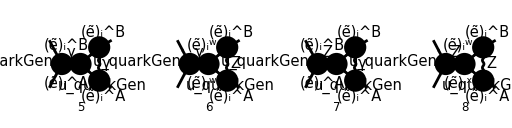

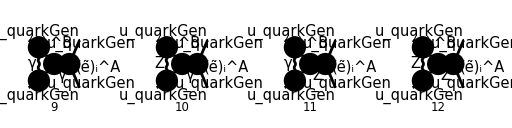

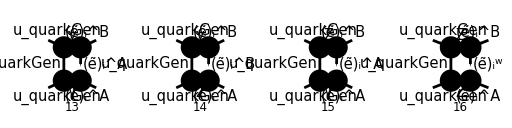

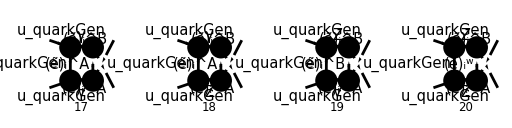

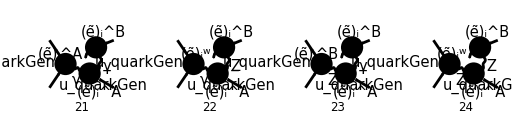

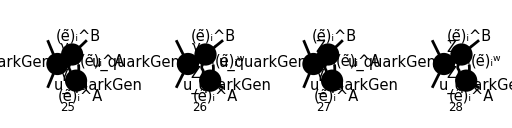

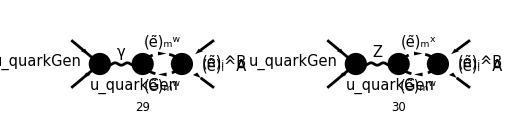

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles,SelfEnergies}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
V[3],
F[11|12],
S[11|13|14]
}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(Q^2-m1^2-m2^2)/2;
```

```mathematica
SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]-s/2 SPD[k1,k2]
%//ReplaceAll[#,top1k1Rules]&//FullSimplify
%//ReplaceAll[#,SPD[k1,k2]->1/2(Q^2-m1^2-m2^2)]&//FullSimplify
%//Collect2[#,{SPD[p1,k],SPD[p2,k],SPD[k1,k],SPD[k2,k]},Factoring->FullSimplify]&
```

(k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-1/2 s (k_1·k_2)

1/2 (-(k_1·p_1) (2 (k_1·k_2)+m_1^2+m_2^2+s)-2 (k_1·k_2+m_1^2) (k·p_1)+(k·k_1) (s-2 (k·p_1))+m_1^2 s)

1/2 (-(m_1^2-m_2^2+Q^2) (k·p_1)-(Q^2+s) (k_1·p_1)+(k·k_1) (s-2 (k·p_1))+m_1^2 s)

1/2 (m_1^2 s-(Q^2+s) (k_1·p_1))-1/2 (m_1^2-m_2^2+Q^2) (k·p_1)-(k·k_1) (k·p_1)+1/2 s (k·k_1)

```mathematica
firstBracket[p1,p2,k1,k2]-firstBracket[p2,p1,k1,k2]
%//ReplaceAll[#,top1k1Rules]&
```

-(2 (k_1·p_1))/((k·k_1) (k·p_1))+(2 (k_1·p_2))/((k·k_1) (k·p_2))-(2 (k_2·p_1))/((k·k_2) (k·p_1))+(2 (k_2·p_2))/((k·k_2) (k·p_2))+4/(k·p_1)-4/(k·p_2)

(2 (-k·p_1-k_1·p_1+k·k_1+1/2 (m_1^2-m_2^2)))/((k·k_2) (k·p_2))+(2 (-k_1·p_1+k·k_1+k_1·k_2+m_1^2))/((k·k_1) (k·p_2))-(2 (-k·p_1-k_1·p_1+s/2))/((k·k_2) (k·p_1))-(2 (k_1·p_1))/((k·k_1) (k·p_1))+4/(k·p_1)-4/(k·p_2)

```mathematica
firstBracket[p1,p2,k1,k2]
%//ReplaceAll[#,top1k1Rules]&
```

-(2 (k_1·p_1))/((k·k_1) (k·p_1))-(2 (k_2·p_1))/((k·k_2) (k·p_1))+4/(k·p_1)

-(2 (-k·p_1-k_1·p_1+s/2))/((k·k_2) (k·p_1))-(2 (k_1·p_1))/((k·k_1) (k·p_1))+4/(k·p_1)

```mathematica
secondBracket[p1,p2,k1,k2]
%//ReplaceAll[#,top1k1Rules]&//FullSimplify
```

(k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-1/4 s (-m_1^2-m_2^2+Q^2)

1/2 (-(m_1^2-m_2^2+Q^2) (k·p_1)-(Q^2+s) (k_1·p_1)+(k·k_1) (s-2 (k·p_1))+m_1^2 s)

```mathematica
2(SPD[p1,k1]/SPD[p1,k]-SPD[p2,k1]/SPD[p2,k])(1/SPD[k2,k]-1/SPD[k1,k])+(1/SPD[p1,k]-1/SPD[p2,k])(4-s/SPD[k2,k])
%//ReplaceAll[#,top1k1Rules]&//FullSimplify
%//Together//FullSimplify
%//Numerator//FullSimplify
```

(1/(k·p_1)-1/(k·p_2)) (4-s/(k·k_2))+2 (1/(k·k_2)-1/(k·k_1)) ((k_1·p_1)/(k·p_1)-(k_1·p_2)/(k·p_2))

2 (1/(k·k_2)-1/(k·k_1)) ((k_1·p_1)/(k·p_1)-(-2 (k_1·p_1)+2 (k·k_1)+m_1^2-m_2^2+Q^2)/(2 (k·p_2)))+(1/(k·p_1)-1/(k·p_2)) (4-s/(k·k_2))

1/((k·k_1) (k·k_2) (k·p_1) (k·p_2))((k·k_1) ((k·p_1) (2 (k_1·p_1)-2 (k·k_2)-m_1^2+m_2^2-Q^2+s)+(k·p_2) (2 (k_1·p_1)+4 (k·k_2)-s))+(k·k_2) ((m_1^2-m_2^2+Q^2) (k·p_1)-2 (k·p_1+k·p_2) (k_1·p_1))-2 (k·k_1)^2 (k·p_1))

(k·k_1) ((k·p_1) (2 (k_1·p_1)-2 (k·k_2)-m_1^2+m_2^2-Q^2+s)+(k·p_2) (2 (k_1·p_1)+4 (k·k_2)-s))+(k·k_2) ((m_1^2-m_2^2+Q^2) (k·p_1)-2 (k·p_1+k·p_2) (k_1·p_1))-2 (k·k_1)^2 (k·p_1)

## 28.04

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
```

```mathematica
DiracTrace[GSD[p2,k1,p1,k2]]
%//DiracSimplify
```

tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2))

4 (k_1·p_2) (k_2·p_1)+4 (k_1·p_1) (k_2·p_2)-2 s (k_1·k_2)

```mathematica
DiracTrace[GSD[p2,k,p1,k2]]
%//ReplaceAll[#,k->p1+p2-k1-k2]&//DiracGammaExpand//FCTraceExpand
%[[4]]+%[[3]]//DiracSimplify
%%[[2]]//DiracSimplify
```

tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_2))

-tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2))-tr((γ·p_2).(γ·k_2).(γ·p_1).(γ·k_2))+tr((γ·p_2).(γ·p_1).(γ·p_1).(γ·k_2))+tr((γ·p_2).(γ·p_2).(γ·p_1).(γ·k_2))

0

2 m_2^2 s-8 (k_2·p_1) (k_2·p_2)

```mathematica
SPD[p2,k]SPD[k2,k](2s m1^2m2^2-8m1^2SPD[p1,k2]SPD[p2,k2])
%//ReplaceAll[#,{k1->k2,k2->k1,m1->m2,m2->m1}]&
%%-%//FullSimplify//ReplaceAll[#,top1k1Rules]&//Expand//FullSimplify
```

(k·k_2) (k·p_2) (2 m_1^2 m_2^2 s-8 m_1^2 (k_2·p_1) (k_2·p_2))

(k·k_1) (k·p_2) (2 m_1^2 m_2^2 s-8 m_2^2 (k_1·p_1) (k_1·p_2))

-2 (k·p_2) (m_1^2 (k·k_2) ((m_1^2-2 m_2^2) s-2 (k·p_1+k_1·p_1) (-2 (k·p_1)-2 (k_1·p_1)+m_1^2-m_2^2+s))+(k·k_1) (2 m_1^2 (k·k_2) (-2 (k·p_1)-2 (k_1·p_1)+s)+m_2^2 (-4 (k_1·k_2+m_1^2) (k_1·p_1)+4 (k_1·p_1)^2+m_1^2 s))-4 m_2^2 (k·k_1)^2 (k_1·p_1))

```mathematica
SPD[p1-k2]SPD[p2-k2]
%//ReplaceAll[#,p2-k2->k1+k-p1]&//ExpandScalarProduct//Collect2[#,{m1,m2},Factoring->FullSimplify]&
```

(p_1-k_2)^2 (p_2-k_2)^2

-2 m_1^2 (k_2·p_1)+2 m_2^2 (-k·p_1-k_1·p_1+k·k_1)+4 (k·p_1+k_1·p_1-(k·k_1)) (k_2·p_1)+m_2^2 m_1^2

```mathematica
expr[p1_,p2_,k1_,k2_]:=(2SPD[p1,k1]SPD[p2,k]SPD[k2,k]-SPD[k1]SPD[p2,k]SPD[k2,k])DiracTrace[GSD[p2,k1,p1,k2]]+2 SPD[p1+p2]SPD[k1]SPD[k2]SPD[p2,k]SPD[k2,k]-8SPD[k1]SPD[p1,k2]SPD[p2,k2]SPD[p2,k]SPD[k2,k]
```

```mathematica
exprFull=expr[p1,p2,k1,k2]-expr[p2,p1,k1,k2]-expr[p1,p2,k2,k1]+expr[p2,p1,k2,k1]//ExpandScalarProduct//DiracSimplify//FullSimplify
```

2 ((k·k_2) ((k·p_2) ((m_1^2-2 (k_1·p_1)) (s (k_1·k_2)-2 (k_1·p_2) (k_2·p_1))-2 (k_2·p_2) (2 m_1^2 (k_2·p_1)+(k_1·p_1) (m_1^2-2 (k_1·p_1)))+m_1^2 m_2^2 s)+(k·p_1) ((m_1^2-2 (k_1·p_2)) (2 (k_1·p_2) (k_2·p_1)-s (k_1·k_2))+2 (k_2·p_2) (2 m_1^2 (k_2·p_1)+(k_1·p_1) (m_1^2-2 (k_1·p_2)))-m_1^2 m_2^2 s))+(k·k_1) ((k·p_1) (s (k_1·k_2) (m_2^2-2 (k_2·p_2))-2 (k_1·p_2) (k_2·p_1) (m_2^2-2 (k_2·p_2))-2 (k_1·p_1) (2 m_2^2 (k_1·p_2)+(k_2·p_2) (m_2^2-2 (k_2·p_2)))+m_1^2 m_2^2 s)-(k·p_2) (s (k_1·k_2) (m_2^2-2 (k_2·p_1))-2 (k_1·p_2) (2 m_2^2 (k_1·p_1)+(k_2·p_1) (m_2^2-2 (k_2·p_1)))-2 (k_1·p_1) (k_2·p_2) (m_2^2-2 (k_2·p_1))+m_1^2 m_2^2 s)))

```mathematica
exprHand=(2SPD[p1,k1]SPD[p2,k]SPD[k2,k]-2SPD[p2,k1]SPD[p1,k]SPD[k2,k]-2SPD[p1,k2]SPD[p2,k]SPD[k1,k]+2SPD[p2,k2]SPD[p1,k]SPD[k1,k]-SPD[p2-p1,k](m1^2SPD[k2,k]-m2^2SPD[k1,k]))DiracTrace[GSD[p2,k1,p1,k2]]+2s m1^2m2^2SPD[p2-p1,k]SPD[k2-k1,k]-8m1^2SPD[p1,k2]SPD[p2,k2]SPD[k2,k]SPD[p2-p1,k]+8m2^2SPD[p1,k1]SPD[p2,k1]SPD[k1,k]SPD[p2-p1,k]//ExpandScalarProduct//DiracSimplify//FullSimplify
```

2 ((k·k_2) ((k·p_2) ((m_1^2-2 (k_1·p_1)) (s (k_1·k_2)-2 (k_1·p_2) (k_2·p_1))-2 (k_2·p_2) (2 m_1^2 (k_2·p_1)+(k_1·p_1) (m_1^2-2 (k_1·p_1)))+m_1^2 m_2^2 s)+(k·p_1) ((m_1^2-2 (k_1·p_2)) (2 (k_1·p_2) (k_2·p_1)-s (k_1·k_2))+2 (k_2·p_2) (2 m_1^2 (k_2·p_1)+(k_1·p_1) (m_1^2-2 (k_1·p_2)))-m_1^2 m_2^2 s))+(k·k_1) ((k·p_1) (s (k_1·k_2) (m_2^2-2 (k_2·p_2))-2 (k_1·p_2) (k_2·p_1) (m_2^2-2 (k_2·p_2))-2 (k_1·p_1) (2 m_2^2 (k_1·p_2)+(k_2·p_2) (m_2^2-2 (k_2·p_2)))+m_1^2 m_2^2 s)-(k·p_2) (s (k_1·k_2) (m_2^2-2 (k_2·p_1))-2 (k_1·p_2) (2 m_2^2 (k_1·p_1)+(k_2·p_1) (m_2^2-2 (k_2·p_1)))-2 (k_1·p_1) (k_2·p_2) (m_2^2-2 (k_2·p_1))+m_1^2 m_2^2 s)))

```mathematica
FCCompareResults[exprFull,exprHand];
```

Check of the results: The results agree.

```mathematica
p1k1=s/4((y+z(1-y))(1+β1-β2)+2Sqrt[y(1-y)z]Sqrt[(xp-x)(x-xm)]cosϕ-(y-z(1-y))(x+β1-β2))
p1k2=s/4((y+z(1-y))(1-β1+β2)-2Sqrt[y(1-y)z]Sqrt[(xp-x)(x-xm)]cosϕ+(y-z(1-y))(x+β1-β2))
p2k1=s/4((1-y+z y)(1+β1-β2)-2Sqrt[y(1-y)z]Sqrt[(xp-x)(x-xm)]cosϕ-(1-y-z y)(x+β1-β2))
p2k2=s/4((1-y+z y)(1-β1+β2)+2Sqrt[y(1-y)z]Sqrt[(xp-x)(x-xm)]cosϕ+(1-y-z y)(x+β1-β2))
```

1/4 s (2 cosϕ √((x-x^-) (x^+-x)) √((1-y) y z)-(β_1-β_2+x) (y-(1-y) z)+(β_1-β_2+1) ((1-y) z+y))

1/4 s (-2 cosϕ √((x-x^-) (x^+-x)) √((1-y) y z)+(β_1-β_2+x) (y-(1-y) z)+(-β_1+β_2+1) ((1-y) z+y))

1/4 s (-2 cosϕ √((x-x^-) (x^+-x)) √((1-y) y z)-(β_1-β_2+x) (y (-z)-y+1)+(β_1-β_2+1) (y z-y+1))

1/4 s (2 cosϕ √((x-x^-) (x^+-x)) √((1-y) y z)+(β_1-β_2+x) (y (-z)-y+1)+(-β_1+β_2+1) (y z-y+1))

```mathematica
p1k1 p1k2
```

1/16 s^2 (2 cosϕ √((x-x^-) (x^+-x)) √((1-y) y z)-(β_1-β_2+x) (y-(1-y) z)+(β_1-β_2+1) ((1-y) z+y)) (-2 cosϕ √((x-x^-) (x^+-x)) √((1-y) y z)+(β_1-β_2+x) (y-(1-y) z)+(-β_1+β_2+1) ((1-y) z+y))

```mathematica
p1k1 p1k1//Expand//Simplify//FullSimplify
```

1/16 s^2 (y^2 (x^2 (z (4 cosϕ^2+z+2)+1)+4 cosϕ^2 x^- x^+ z-4 cosϕ^2 x (x^-+x^+) z+2 x (z+1) (2 β_1 z-2 β_2 z+z-1)+(2 β_1-2 β_2+1) z (2 β_1 z-2 β_2 z+z-2)+1)-2 y (z (-2 β_1+2 β_2+(2 cosϕ^2+1) x^2+2 x (β_1-β_2+cosϕ (√(-((x-x^-) (x-x^+))) √(-((y-1) y z))-cosϕ (x^-+x^+)))+2 cosϕ (cosϕ x^- x^++(2 β_1-2 β_2+1) √(-((x-x^-) (x-x^+))) √(-((y-1) y z)))-1)+2 cosϕ (x-1) √(-((x-x^-) (x-x^+))) √(-((y-1) y z))+z^2 (2 β_1-2 β_2+x+1)^2)+z (2 β_1-2 β_2+x+1) (4 cosϕ √(-((x-x^-) (x-x^+))) √(-((y-1) y z))+z (2 β_1-2 β_2+x+1)))

```mathematica
2Sqrt[y(1-y)z]Sqrt[(xp-x)(x-xm)]Cos[ϕ]+2z(1-y)(β1-β2)+(z(1-y)-y)x
% %//Expand//FullSimplify
```

2 √((x-x^-) (x^+-x)) √((1-y) y z) cos(ϕ)+x ((1-y) z-y)+2 (β_1-β_2) (1-y) z

-4 √(-((x-x^-) (x-x^+))) √(-((y-1) y z)) cos(ϕ) (x ((y-1) z+y)+2 (β_1-β_2) (y-1) z)+4 (x-x^-) (x-x^+) (y-1) y z cos^2(ϕ)+(x ((y-1) z+y)+2 (β_1-β_2) (y-1) z)^2

```mathematica
(Sqrt[λ]+β2-β1)(-Sqrt[λ]+β2-β1)//FullSimplify//ReplaceAll[#,λ->1+β1^2+β2^2-2(β1+β2)-2β1 β2]&//FullSimplify
```

2 β_1+2 β_2-1

```mathematica
p1k2 p2k1//FullSimplify//Expand//Simplify
```

1/16 s^2 (y^2 (x^2 ((4 cosϕ^2+2) z+z^2+1)-4 x z (cosϕ^2 (x^-+x^+)-(β_1-β_2) (z+1))+z (4 cosϕ^2 x^- x^++2)+(4 β_1^2-8 β_2 β_1+4 β_2^2-1) z^2-1)+y (-(x^2 ((4 cosϕ^2+2) z+z^2+1))+4 x (z (-β_1+β_2+cosϕ^2 (x^-+x^+)-cosϕ √(-((x-x^-) (x-x^+))) √(-((y-1) y z))+1)-cosϕ √(-((x-x^-) (x-x^+))) √(-((y-1) y z))+(β_2-β_1) z^2)+z (4 β_1-4 β_2-4 cosϕ^2 x^- x^++8 (β_2-β_1) cosϕ √(-((x-x^-) (x-x^+))) √(-((y-1) y z))-2)+(-4 β_1^2+8 β_2 β_1-4 β_2^2+1) z^2+1)+z (2 β_1-2 β_2+x-1) (2 cosϕ √(-((x-x^-) (x-x^+))) √(-((y-1) y z))+x-1)+2 cosϕ (x-1) √(-((x-x^-) (x-x^+))) √(-((y-1) y z)))

```mathematica
p1k1 p2k2
```

1/16 s^2 (2 cosϕ √((x-x^-) (x^+-x)) √((1-y) y z)-(β_1-β_2+x) (y-(1-y) z)+(β_1-β_2+1) ((1-y) z+y)) (2 cosϕ √((x-x^-) (x^+-x)) √((1-y) y z)+(β_1-β_2+x) (y (-z)-y+1)+(-β_1+β_2+1) (y z-y+1))

```mathematica
p1k2 p2k1+p1k1 p2k2//Expand//Simplify//Collect2[#,{cosϕ},Factoring->FullSimplify]&
```

1/2 cosϕ^2 s^2 (x-x^-) (x-x^+) (y-1) y z-1/4 cosϕ s^2 √(-((x-x^-) (x-x^+))) (2 y-1) √(-((y-1) y z)) (x z+x+2 β_1 z-2 β_2 z)+1/8 s^2 (y^2 (x (z+1)+(2 β_1-2 β_2-1) z+1) (x z+x+2 β_1 z-2 β_2 z+z-1)-y (x (z+1)+(2 β_1-2 β_2-1) z+1) (x z+x+2 β_1 z-2 β_2 z+z-1)+x z (2 β_1-2 β_2+x)+z)

```mathematica
top1k1Rules={
SPD[p1,k2]->SPD[p1,p2]-SPD[p1,k]-SPD[p1,k1],
SPD[p2,k1]->m1^2+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(m1^2-m2^2)/2+SPD[k1,k]-SPD[p1,k]-SPD[p1,k1]
};
spdToxyzRules={
SPD[p1,k]->s/2(1-z)(1-y),
SPD[p2,k]->s/2(1-z)y,
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x)
};
```

```mathematica
SPD[p1,k2]SPD[p2,k1]+SPD[p1,k1]SPD[p2,k2]-s/2SPD[k1,k2]
%//ReplaceAll[#,top1k1Rules]&//FullSimplify//ReplaceAll[#,2SPD[k1,k2]+m1^2+m2^2->Q^2]&
%//Collect2[#,{s,m1,m2},Factoring->FullSimplify]&
%//ReplaceAll[#,SPD[k1,k2]->(Q^2-m1^2-m2^2)/2]&//FullSimplify//Collect2[#,{s,Q},Factoring->FullSimplify]&
%//ReplaceAll[#,spdToxyzRules]&//ReplaceAll[#,{1-z->Z,1-y->Y,1+x->XP,1-x->X}]&//Collect2[#,{X,Y,Z},Factoring->FullSimplify]&
```

(k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-1/2 s (k_1·k_2)

1/2 (-2 (k_1·k_2+m_1^2) (k·p_1)-(Q^2+s) (k_1·p_1)+(k·k_1) (s-2 (k·p_1))+m_1^2 s)

-m_1^2 (k·p_1)-1/2 Q^2 (k_1·p_1)+1/2 s (k·k_1-k_1·p_1)-(k·k_1+k_1·k_2) (k·p_1)+(m_1^2 s)/2

1/2 s (-k_1·p_1+k·k_1+m_1^2)-1/2 (2 (k·k_1)+m_1^2-m_2^2) (k·p_1)-1/2 Q^2 (k·p_1+k_1·p_1)

1/2 (m_1^2 s-(Q^2+s) (k_1·p_1))-1/4 s Y Z (m_1^2-m_2^2+Q^2)-1/8 s^2 X Y Z^2+1/8 s^2 X Z

```mathematica
p1k10=Q^2/4(y(1-x)/z+(1-y)(1+x)+2Sqrt[y(1-y)/z]Sqrt[(xp-x)(x-xm)]Cos[ϕ])
p1k20=Q^2/4(y(1+x)/z+(1-y)(1-x)-2Sqrt[y(1-y)/z]Sqrt[(xp-x)(x-xm)]Cos[ϕ])
p2k10=Q^2/4((1-y)(1-x)/z+y(1+x)-2Sqrt[y(1-y)/z]Sqrt[(xp-x)(x-xm)]Cos[ϕ])
p2k20=Q^2/4((1-y)(1+x)/z+y(1-x)+2Sqrt[y(1-y)/z]Sqrt[(xp-x)(x-xm)]Cos[ϕ])
```

1/4 Q^2 (2 √((x-x^-) (x^+-x)) √(((1-y) y)/z) cos(ϕ)+((1-x) y)/z+(x+1) (1-y))

1/4 Q^2 (-2 √((x-x^-) (x^+-x)) √(((1-y) y)/z) cos(ϕ)+((x+1) y)/z+(1-x) (1-y))

1/4 Q^2 (-2 √((x-x^-) (x^+-x)) √(((1-y) y)/z) cos(ϕ)+((1-x) (1-y))/z+(x+1) y)

1/4 Q^2 (2 √((x-x^-) (x^+-x)) √(((1-y) y)/z) cos(ϕ)+((x+1) (1-y))/z+(1-x) y)

```mathematica
p1k10 -p2k20//Simplify
```

(Q^2 (z-1) (x-2 y+1))/(4 z)

```mathematica
p1k1
p2k2
p1k1-p2k2//Simplify
```

1/4 s (2 cosϕ √((x-x^-) (x^+-x)) √((1-y) y z)-(β_1-β_2+x) (y-(1-y) z)+(β_1-β_2+1) ((1-y) z+y))

1/4 s (2 cosϕ √((x-x^-) (x^+-x)) √((1-y) y z)+(β_1-β_2+x) (y (-z)-y+1)+(-β_1+β_2+1) (y z-y+1))

1/4 s (x (z-1)-2 y (z-1)+2 β_1 z-2 β_2 z+z-1)

```mathematica
p1k10+p1k20//Simplify
p1k10+p2k10//Simplify
p1k10-p2k20//Simplify
```

-(Q^2 (y (z-1)-z))/(2 z)

(Q^2 (x (z-1)+z+1))/(4 z)

(Q^2 (z-1) (x-2 y+1))/(4 z)

```mathematica
DiracTrace[GSD[p2,k,p1,k2]]
%//DiracSimplify//FullSimplify
```

tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_2))

4 (k·p_2) (k_2·p_1)+4 (k·p_1) (k_2·p_2)-2 s (k·k_2)

```mathematica
SPD[k1+k2+k-p1,k]//ExpandScalarProduct
```

-k·p_1+k·k_1+k·k_2

```mathematica
p1k20 p2k10//FullSimplify
p1k10 p2k20//FullSimplify
%%+%//FullSimplify
```

1/16 Q^4 (-2 √((x-x^-) (x^+-x)) √(-((y-1) y)/z) cos(ϕ)+((x-1) (y-1))/z+(x+1) y) (-2 √((x-x^-) (x^+-x)) √(-((y-1) y)/z) cos(ϕ)+((x+1) y)/z+(x-1) (y-1))

1/16 Q^4 (2 √(-((x-x^-) (x-x^+))) √(-((y-1) y)/z) cos(ϕ)-(y (x z+x+z-1))/z+x+1) (2 √((x-x^-) (x^+-x)) √(-((y-1) y)/z) cos(ϕ)-((x+1) (y-1))/z-x y+y)

1/(8 z^2)Q^4 ((x^2-1) (y-1) y z^2+(x^2+1) (2 (y-1) y+1) z+(x^2-1) (y-1) y+4 (x-x^-) (x-x^+) (y-1) y z cos^2(ϕ)-2 x √(-((x-x^-) (x-x^+))) (2 y-1) (z+1) z √(-((y-1) y)/z) cos(ϕ))

```mathematica
p1k10^2//Expand//Simplify
```

1/(16 z^2)Q^4 (4 (x-x^-) (x-x^+) (y-1) y z cos^2(ϕ)-4 √(-((x-x^-) (x-x^+))) z √(-((y-1) y)/z) cos(ϕ) (y (x z+x+z-1)-(x+1) z)+((x+1) z-y (x z+x+z-1))^2)

```mathematica
p2k10+p2k20//Simplify
```

(Q^2 (y (z-1)+1))/(2 z)

```mathematica
p1k20 p2k10
```

1/16 Q^4 (-2 √((x-x^-) (x^+-x)) √(-((y-1) y)/z) cos(ϕ)+((x-1) (y-1))/z+(x+1) y) (-2 √((x-x^-) (x^+-x)) √(-((y-1) y)/z) cos(ϕ)+((x+1) y)/z+(x-1) (y-1))

```mathematica
p1k20^2+p1k10^2//FullSimplify
```

1/(8 z^2)Q^4 (x^2 ((y-1) z+y)^2+4 (x-x^-) (x-x^+) (y-1) y z cos^2(ϕ)-4 x √(-((x-x^-) (x-x^+))) z √(-((y-1) y)/z) ((y-1) z+y) cos(ϕ)+(y (-z)+y+z)^2)

```mathematica
p1k1+p1k2//Simplify
```

1/2 s (y (-z)+y+z)

```mathematica
p1k1s=s/4(y(1-x)+z(1-y)(1+(x+2M^2))+Φ)
p1k2s=s/4(y(1+x)+z(1-y)(1-(x+2M^2))-Φ)
p2k1s=s/4((1-y)(1-x)+z y(1+(x+2M^2))-Φ)
p2k2s=s/4((1-y)(1+x)+z y(1-(x+2M^2))+Φ)
```

1/4 s ((1-y) z (2 M^2+x+1)+Φ+(1-x) y)

1/4 s ((1-y) z (-2 M^2-x+1)-Φ+(x+1) y)

1/4 s (y z (2 M^2+x+1)-Φ+(1-x) (1-y))

1/4 s (y z (-2 M^2-x+1)+Φ+(x+1) (1-y))

```mathematica
p1k1s p1k2s//ReplaceAll[#,{1-y->Y,1-z->Z,1-x->XM,1+x->XP}]&//Collect2[#,Φ,Factoring->FullSimplify]&
```

-1/16 s^2 Φ (4 M^2 Y z+(XM-XP) (y-Y z))+1/16 s^2 (Y z (XM-2 M^2)+XP y) (Y z (2 M^2+XP)+XM y)-1/16 s^2 Φ^2

```mathematica
(Y z(XM-2M^2)+XP y)(Y z(2M^2+XP)+XM y)//ReplaceAll[#,{XM->1-x,XP->1+x,Y->1-y,Z->1-z}]&//FullSimplify//ReplaceAll[#,M->0]&//FullSimplify
```

((x-1) (y-1) z+(x+1) y) (-y (x z+x+z-1)+x z+z)

### Find pi.kj directly

```mathematica
$Assumptions={
0<z<=1,
Q∈PositiveReals,
s∈PositiveReals,
λ∈PositiveReals,
-1<xm<=x<=xp<1,
0<=y<=1
};
```

```mathematica
rotyθ={{1,0,0,0},{0,Cos[θ],0,Sin[θ]},{0,0,1,0},{0,-Sin[θ],0,Cos[θ]}}
boostzβ={{γ,0,0,-γβ},{0,1,0,0},{0,0,1,0},{-γβ,0,0,γ}}
k1vecp={{E1},{k1abs Sin[θp]Cos[ϕp]},{k1abs Sin[θp]Sin[ϕp]},{k1abs Cos[θp]}}
k2vecp={{E2},{-k1abs Sin[θp]Cos[ϕp]},{-k1abs Sin[θp]Sin[ϕp]},{-k1abs Cos[θp]}}
```

(1 | 0 | 0 | 0
0 | cos(θ) | 0 | sin(θ)
0 | 0 | 1 | 0
0 | -sin(θ) | 0 | cos(θ))

(γ | 0 | 0 | -γβ
0 | 1 | 0 | 0
0 | 0 | 1 | 0
-γβ | 0 | 0 | γ)

(E1
k1abs sin(θp) cos(ϕp)
k1abs sin(θp) sin(ϕp)
k1abs cos(θp))

(E2
-k1abs sin(θp) cos(ϕp)
-k1abs sin(θp) sin(ϕp)
-k1abs cos(θp))

```mathematica
k1vec=rotyθ.boostzβ.k1vecp
k2vec=rotyθ.boostzβ.k2vecp
```

(γ E1-γβ k1abs cos(θp)
γβ (-E1) sin(θ)+γ k1abs sin(θ) cos(θp)+k1abs cos(θ) sin(θp) cos(ϕp)
k1abs sin(θp) sin(ϕp)
γβ (-E1) cos(θ)+γ k1abs cos(θ) cos(θp)-k1abs sin(θ) sin(θp) cos(ϕp))

(γ E2+γβ k1abs cos(θp)
γβ (-E2) sin(θ)-γ k1abs sin(θ) cos(θp)-k1abs cos(θ) sin(θp) cos(ϕp)
-k1abs sin(θp) sin(ϕp)
γβ (-E2) cos(θ)-γ k1abs cos(θ) cos(θp)+k1abs sin(θ) sin(θp) cos(ϕp))

```mathematica
p1vec=Sqrt[s]/2{{1},{0},{0},{1}}
p2vec=Sqrt[s]/2{{1},{0},{0},{-1}}
```

((√s)/2
0
0
(√s)/2)

((√s)/2
0
0
-(√s)/2)

```mathematica
energyMomentumRules={
γ->Sqrt[s](1+z)/(2Q),
γβ->Sqrt[s](1-z)/(2Q),
E1->Q/2(1+mt1^2-mt2^2),
E2->Q/2(1-mt1^2+mt2^2),
k1abs->Q/2 Sqrt[λ],
Cos[θ]->2y-1,
Sin[θ]->Sqrt[(1-(2y-1)^2)],
Cos[θp]->(x+mt1^2-mt2^2)/Sqrt[λ],
Sin[θp]->Sqrt[(xp-x)(x-xm)]/Sqrt[λ],
s->Q^2/z
};
```

```mathematica
p1dotk1=p1vec[[1]]k1vec[[1]]-p1vec[[4]]k1vec[[4]]//ReplaceRepeated[#,energyMomentumRules]&//FullSimplify
p2dotk1=p2vec[[1]]k1vec[[1]]-p2vec[[4]]k1vec[[4]]//ReplaceRepeated[#,energyMomentumRules]&//FullSimplify
p1dotk2=p1vec[[1]]k2vec[[1]]-p1vec[[4]]k2vec[[4]]//ReplaceRepeated[#,energyMomentumRules]&//FullSimplify
p2dotk2=p2vec[[1]]k2vec[[1]]-p2vec[[4]]k2vec[[4]]//ReplaceRepeated[#,energyMomentumRules]&//FullSimplify
```

{(Q^2 (-(y-1) z (2 mt1^2-2 mt2^2+x+1)+2 cos(ϕp) √((x-x^-) (x-x^+) (y-1) y z)-x y+y))/(4 z)}

{(Q^2 (y z (2 mt1^2-2 mt2^2+x+1)-2 cos(ϕp) √((x-x^-) (x-x^+) (y-1) y z)+(x-1) (y-1)))/(4 z)}

{(Q^2 ((y-1) z (2 mt1^2-2 mt2^2+x-1)-2 cos(ϕp) √((x-x^-) (x-x^+) (y-1) y z)+(x+1) y))/(4 z)}

{(Q^2 (-y z (2 mt1^2-2 mt2^2+x-1)+2 cos(ϕp) √((x-x^-) (x-x^+) (y-1) y z)-((x+1) (y-1))))/(4 z)}

```mathematica
simplifyRules={
2mt1^2-2mt2^2->2Mt^2,
Sqrt[(x-xm)(x-xp)(y-1)y z]Cos[ϕp]->Φ/2
};
```

```mathematica
p1dotk1s=p1dotk1//ReplaceAll[#,simplifyRules]&
p2dotk1s=p2dotk1//ReplaceAll[#,simplifyRules]&
p1dotk2s=p1dotk2//ReplaceAll[#,simplifyRules]&
p2dotk2s=p2dotk2//ReplaceAll[#,simplifyRules]&
```

{(Q^2 (-(y-1) z (2 Mt^2+x+1)+Φ-x y+y))/(4 z)}

{(Q^2 (y z (2 Mt^2+x+1)-Φ+(x-1) (y-1)))/(4 z)}

{(Q^2 ((y-1) z (2 Mt^2+x-1)-Φ+(x+1) y))/(4 z)}

{(Q^2 (-y z (2 Mt^2+x-1)+Φ-((x+1) (y-1))))/(4 z)}

```mathematica
p1dotk2s p2dotk1s//Collect2[#,Φ,Factoring->FullSimplify]&
p1dotk1s p2dotk2s//Collect2[#,Φ,Factoring->FullSimplify]&
%%+%//Collect2[#,Φ,Factoring->FullSimplify]&
```

{-(Q^4 Φ (Mt^2 (4 y-2) z+x (2 y-1) (z+1)+z+1))/(16 z^2)+(Q^4 ((y-1) z (2 Mt^2+x-1)+(x+1) y) (y z (2 Mt^2+x+1)+(x-1) (y-1)))/(16 z^2)+(Q^4 Φ^2)/(16 z^2)}

{(Q^4 Φ (Mt^2 (2-4 y) z-x (2 y-1) (z+1)+z+1))/(16 z^2)+(Q^4 ((y-1) z (2 Mt^2+x+1)+(x-1) y) (y z (2 Mt^2+x-1)+(x+1) (y-1)))/(16 z^2)+(Q^4 Φ^2)/(16 z^2)}

{(Q^4 ((2 (y-1) y+1) z (2 Mt^2 x+x^2+1)+(y-1) y z^2 ((2 Mt^2+x)^2-1)+(x^2-1) (y-1) y))/(8 z^2)-(Q^4 Φ (2 y-1) (2 Mt^2 z+x z+x))/(8 z^2)+(Q^4 Φ^2)/(8 z^2)}

```mathematica
Gamma[1/2-ϵ]//Series[#,{ϵ,0,1}]&
```

√π-√π ϵ 01/2+O(ϵ^2)

## 29.04

```mathematica
x^n/Sqrt[(1-x^2)]
Assuming[n∈PositiveIntegers,Integrate[%,{x,-1,1}]]
```

x^n/(√(1-x^2))

(√π ((-1)^n+1) (n+1)/2)/(n n/2)

```mathematica
x^n/(1-x^2)^((5-d)/2)
Integrate[%,{x,-1,1}]
```

(1-x^2)^((d-5)/2) x^n

ConditionalExpression[(((-1)^n+1) (d-3)/2 (n+1)/2)/(2 1/2 (d+n-2)), Re(d)>3∧Re(n)>-1]

```mathematica
Integrate[1/Sqrt[1-x^2],{x,-1,1}]
```

π

```mathematica
Gamma[1/2]
```

√π

```mathematica
4y(1-y)z(xp-x)(x-xm)+2t y(1-x)+2t z(1-y)(1+x+2M^2)-t^2-y^2(1-x)^2-z^2(1-y)^2(1+x+2M^2)^2-2y(1-y)z(1-x)(1+x+2M^2)
Reduce[%==0,t]
```

2 t (1-y) z (2 M^2+x+1)-(1-y)^2 z^2 (2 M^2+x+1)^2-2 (1-x) (1-y) y z (2 M^2+x+1)-t^2+2 t (1-x) y+4 (x-x^-) (x^+-x) (1-y) y z-(1-x)^2 y^2

t==-2 M^2 y z+2 M^2 z-2 √(x^2 y^2 z-x^2 y z-x^- x y^2 z+x^- x y z-x^+ x y^2 z+x^+ x y z+x^- x^+ y^2 z-x^- x^+ y z)-x y z-x y+x z-y z+y+z∨t==-2 M^2 y z+2 M^2 z+2 √(x^2 y^2 z-x^2 y z-x^- x y^2 z+x^- x y z-x^+ x y^2 z+x^+ x y z+x^- x^+ y^2 z-x^- x^+ y z)-x y z-x y+x z-y z+y+z

```mathematica
Λ^2+2t a-t^2-a^2
Reduce[%==0,t]
```

-a^2+2 a t+Λ^2-t^2

t==a-Λ∨t==a+Λ

```mathematica
-(t-A+Λ)(t-A-Λ)//Expand
```

-A^2+2 A t+Λ^2-t^2

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[p1,k1]=t;
SPD[k1,k2]=(Q^2-m1^2-m2^2)/2;
```

```mathematica
top1k1Rules={
SPD[p1,k2]->s/2-SPD[p1,k1]-SPD[p1,k],
SPD[p2,k1]->m1^2+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(m2^2-m1^2)/2-SPD[k1,k]+SPD[p1,k]+SPD[p1,k1]
};
```

```mathematica
DiracTrace[GSD[p2,k1,p1,k2]]
%//DiracSimplify//FullSimplify
%//FCE//ReplaceAll[#,top1k1Rules]&//FullSimplify//Collect2[#,t,Factoring->FullSimplify]&
```

tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2))

4 t (k_2·p_2)+4 (k_1·p_2) (k_2·p_1)+s (m_1^2+m_2^2-Q^2)

-2 t (-4 (k·p_1)+4 (k·k_1)+2 m_1^2-2 m_2^2+Q^2+s)-2 (k·p_1) (2 (k·k_1)+m_1^2-m_2^2+Q^2)+2 s (k·k_1+m_1^2)+8 t^2

```mathematica
2SPD[p2,k2]-m2^2
%//ReplaceAll[#,top1k1Rules]&
```

2 (k_2·p_2)-m_2^2

2 (k·p_1-k·k_1+1/2 (m_2^2-m_1^2)+t)-m_2^2

```mathematica
2SPD[p1,k2]-m2^2
%//ReplaceAll[#,top1k1Rules]&
```

2 (k_2·p_1)-m_2^2

2 (-k·p_1+s/2-t)-m_2^2

```mathematica
(2SPD[p1,k1]-m1^2)/((1-y)(1-x))-(2SPD[p2,k1]-m1^2)/(y(1-x))-(2SPD[p1,k2]-m2^2)/((1-y)(1+x))+(2SPD[p2,k2]-m2^2)/(y(1+x))
%//ReplaceAll[#,top1k1Rules]&//ReplaceAll[#,{
SPD[k,p1]->s/2(1-z)(1-y),
SPD[k,k1]->s/4(1-z)(1-x)
}]&//ReplaceAll[#,{
1-z->Z,
1-y->Y,
1-x->XM,
1+x->XP
}]&//FullSimplify//Apart[#,{XM,XP,y,Y}]&
```

-(2 (k_1·p_2)-m_1^2)/((1-x) y)-(2 (k_2·p_1)-m_2^2)/((x+1) (1-y))+(2 (k_2·p_2)-m_2^2)/((x+1) y)+(2 t-m_1^2)/((1-x) (1-y))

{(m_1^2 (-y)+m_2^2 Y-Q^2 Y+2 t y+2 t Y)/(XM y Y)-(-2 m_2^2 y+2 m_1^2 Y+s XP Y Z-2 s y Y Z+2 s y-2 s Y^2 Z-4 t y-4 t Y)/(2 XP y Y)-(s XM Z)/(2 XP y),(-2 m_1^2 y+2 m_2^2 Y-2 Q^2 Y-s XM Y Z+4 t y+4 t Y)/(2 XM y Y)+(2 m_2^2 y-2 m_1^2 Y-s XM Y Z+2 s y Y Z-2 s y+2 s Y^2 Z+4 t y+4 t Y)/(2 XP y Y),(-2 m_1^2 XM+2 m_2^2 XP-2 Q^2 XP-s XM^2 Z-s XM XP Z+2 s XM Y Z+4 t XM+4 t XP)/(2 XM XP y)+(m_2^2 XM+m_1^2 (-XP)+s XM Y Z-s XM+2 t XM+2 t XP)/(XM XP Y),-(2 m_1^2 XM-2 m_2^2 XP+2 Q^2 XP+s XM^2 Z+s XM XP Z-2 s XM y Z-4 t XM-4 t XP)/(2 XM XP y)+(m_2^2 XM+m_1^2 (-XP)-s XM+2 t XM+2 t XP)/(XM XP Y)+(s Y Z)/(XP y)}

```mathematica
%//StandardForm
```

1/(2 XM XP y Y)(2 (4 t+m2^2 XM-s XM-m1^2 XP) y+2 (4 t-m1^2 XM+(m2-Q) (m2+Q) XP) Y-s XM Y (2-2 (y+Y)) Z)

```mathematica
m2^2(1-x)-m1^2(1+x)-s(1-x)+2t (1-x)+2t (1+x)//FullSimplify
```

-(m_1^2 (x+1))-m_2^2 (x-1)+s (x-1)+4 t

```mathematica
p1k1
```

p1k1

```mathematica
p1k1=s/4(y(1-x)+z(1-y)(1+(x+2M^2))+Φ)
p2k1=s/4((1-y)(1-x)+z y(1+(x+2M^2))-Φ)
```

1/4 s ((1-y) z (2 M^2+x+1)+Φ+(1-x) y)

1/4 s (y z (2 M^2+x+1)-Φ+(1-x) (1-y))

```mathematica
p1k1-p2k1//FullSimplify
```

1/4 (2 s Φ-s (2 y-1) (2 M^2 z+x z+x+z-1))

```mathematica
A11=y/(1-y)(1-x)+z(1+x)+2Sqrt[y/(1-y)]Sqrt[z]Sqrt[(xp-x)(x-xm)]Cos[ϕ]
A21=(1-y)/y(1-x)+z(1+x)-2Sqrt[(1-y)/y]Sqrt[z]Sqrt[(xp-x)(x-xm)]Cos[ϕ]
```

2 √((x-x^-) (x^+-x)) √(y/(1-y)) √z cos(ϕ)+((1-x) y)/(1-y)+(x+1) z

-2 √((x-x^-) (x^+-x)) √((1-y)/y) √z cos(ϕ)+((1-x) (1-y))/y+(x+1) z

```mathematica
A11 A21//Collect2[#,Cos[ϕ],Factoring->FullSimplify]&
```

((x^2-1) (2 (y-1) y+1) z)/((y-1) y)+4 (x-x^-) (x-x^+) √(1/y-1) √(-y/(y-1)) z cos^2(ϕ)+2 √(-((x-x^-) (x-x^+))) √z cos(ϕ) (-(x+1) √(1/y-1) z+(x+1) √(-y/(y-1)) z+(1-x)/(√(-y/(y-1)))+(x-1)/(√(1/y-1)))+(x+1)^2 z^2+(x-1)^2

## 30.04

```mathematica
A^2-Φ^2-B^2+2B Φ
%//FullSimplify
```

A^2-B^2+2 B Φ-Φ^2

(A+B-Φ) (A-B+Φ)

```mathematica
(1-Φ)(1+Φ)^2/((Φp-Φ)(Φ-Φm))
Integrate[%,{Φ,Φm,Φp}]
%//FullSimplify//ReplaceAll[#,{Φp->B+A,Φm->B-A}]&//FullSimplify
```

((1-Φ) (Φ+1)^2)/((Φ-Φm) (Φp-Φ))

Integrate::idiv: Integral of -((-1+Φ) (1+Φ)^2)/((-Φ+Φm) (Φ-Φp)) does not converge on {Φm,Φp}.

∫_Φm^Φp ((1-Φ) (Φ+1)^2)/((Φ-Φm) (Φp-Φ))ⅆΦ

Integrate::idiv: Integral of -((-1+Φ) (1+Φ)^2)/((A+B-Φ) (A-B+Φ)) does not converge on {-A+B,A+B}.

∫_(B-A)^(A+B) -((Φ-1) (Φ+1)^2)/((A+B-Φ) (A-B+Φ))ⅆΦ

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(Q^2-m1^2-m2^2)/2;
```

```mathematica
p1k1Rules={
SPD[p1,k2]->SPD[p1,p1+p2-k1-k],
SPD[p2,k1]->SPD[k1+k2+k-p1,k1],
SPD[p2,k2]->1/2(m2^2-SPD[k1+k-p1])
};
p1kiRules={
SPD[p2,k1]->SPD[k1+k2+k-p1,k1],
SPD[p2,k2]->SPD[k1+k2+k-p1,k2]
};
kdotRules={
SPD[p1,k]->s/2(1-z)(1-y),
SPD[p2,k]->s/2(1-z)y,
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x)
};
toOneMinusRules={
1+x->Xp,
1-x->Xm,
1-y->Y,
1-z->Z
};
fromOneMinusRules={
Xp->1+x,
Xm->1-x,
Y->1-y,
Z->1-z
};
```

```mathematica
(2SPD[p1,k1]-m1^2)/((1-y)(1-x))-(2SPD[p2,k1]-m1^2)/(y(1-x))-(2SPD[p1,k2]-m2^2)/((1-y)(1+x))+(2SPD[p2,k2]-m2^2)/(y(1+x))
%//ReplaceAll[#,p1kiRules]&//ExpandScalarProduct//FCE//ReplaceAll[#,kdotRules]&//ReplaceAll[#,toOneMinusRules]&//FullSimplify//ReplaceAll[#,{y+Y->1}]&
%//Numerator//ReplaceAll[#,fromOneMinusRules]&//FullSimplify
%//ReplaceAll[#,{
SPD[p1,k1]->s/4(C+Φ),
SPD[p1,k2]->s/4(C-Φ)
}]&//FullSimplify
```

(2 (k_1·p_1)-m_1^2)/((1-x) (1-y))-(2 (k_1·p_2)-m_1^2)/((1-x) y)-(2 (k_2·p_1)-m_2^2)/((x+1) (1-y))+(2 (k_2·p_2)-m_2^2)/((x+1) y)

(-2 Xm (k_2·p_1)+2 Xp (k_1·p_1)+2 Y (k_1·k_2) (Xm-Xp)+m_2^2 Xm+m_1^2 (-Xp))/(Xm Xp y Y)

2 (x+1) (k_1·p_1)+2 (x-1) (k_2·p_1)+4 x (y-1) (k_1·k_2)-(m_1^2 (x+1))-m_2^2 (x-1)

C s x+4 x (y-1) (k_1·k_2)-(m_1^2 (x+1))-m_2^2 x+m_2^2+s Φ

```mathematica
s m1^2m2^2-4m1^2SPD[p1,k2]SPD[p2,k2]
%//ReplaceAll[#,p1kiRules]&//ExpandScalarProduct//FCE//ReplaceAll[#,SPD[k1,k2]->(Q^2-m1^2-m2^2)/2]&//FullSimplify
```

m_1^2 m_2^2 s-4 m_1^2 (k_2·p_1) (k_2·p_2)

m_1^2 (m_2^2 s-2 (k_2·p_1) (-2 (k_2·p_1)+2 (k·k_2)-m_1^2+m_2^2+Q^2))

```mathematica
(2SPD[p1,k1]-m1^2)(SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]-s/2SPD[k1,k2])+s/2m1^2m2^2-2m1^2SPD[p1,k2]SPD[p2,k2]
%//ReplaceAll[#,p1kiRules]&//ExpandScalarProduct//FullSimplify
%//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]},Factoring->FullSimplify,IsolateNames->KK]&
```

(2 (k_1·p_1)-m_1^2) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-1/2 s (k_1·k_2))-2 m_1^2 (k_2·p_1) (k_2·p_2)+1/2 m_2^2 m_1^2 s

1/2 (-(m_1^2-2 (k_1·p_1)) (2 (k_1·p_1) (-2 (k_2·p_1)+k·k_2+m_2^2)+2 (k·k_1+m_1^2) (k_2·p_1)+(k_1·k_2) (2 (k_1·p_1)+2 (k_2·p_1)-s))-4 m_1^2 (k_2·p_1) (-k_2·p_1+k·k_2+k_1·k_2+m_2^2)+m_2^2 m_1^2 s)

(KK(66))/2-KK(61) (k·k_1)

```mathematica
KK[61]//FRH//Expand
```

m_1^2 (k_2·p_1)-2 (k_1·p_1) (k_2·p_1)

```mathematica
KK[66]//FRH
```

(m_1^2-2 (k_1·p_1)) (s (k_1·k_2)-2 (k·k_2+k_1·k_2+m_2^2) (k_1·p_1))+4 m_1^2 (k_2·p_1)^2-2 (k_2·p_1) (-2 (k_1·k_2+2 m_1^2) (k_1·p_1)+m_1^2 (2 (k·k_2)+3 (k_1·k_2)+m_1^2+2 m_2^2)+4 (k_1·p_1)^2)+m_1^2 m_2^2 s

```mathematica
(2SPD[p1,k1]-m1^2)(SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]-s/2SPD[k1,k2])+s/2m1^2m2^2-2m1^2SPD[p1,k2]SPD[p2,k2]
%//ReplaceAll[#,p1k1Rules]&//ExpandScalarProduct//FullSimplify//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]},Factoring->FullSimplify,IsolateNames->KK]&
```

(2 (k_1·p_1)-m_1^2) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-1/4 s (-m_1^2-m_2^2+Q^2))-2 m_1^2 (k_2·p_1) (k_2·p_2)+1/2 m_2^2 m_1^2 s

2 KK(51) (k·p_1)^2+KK(90) (k·p_1)+KK(77) (k·k_1) (k·p_1)+KK(79) (k·k_1)+(KK(93))/2

```mathematica
KK[90]//FRH
```

(k_1·p_1) (4 (k_1·p_1)+m_1^2+m_2^2-Q^2)+1/2 m_1^2 (-m_1^2+m_2^2+Q^2-2 s)

```mathematica
KK[77]//FRH
```

-2 (k_1·p_1)-m_1^2

```mathematica
KK[79]//FRH
```

(k_1·p_1) (s-4 (k_1·p_1))+(m_1^2 s)/2

```mathematica
SPD[p1,k1]^2
SPD[p1,k1]SPD[p1,p1+p2-k2-k]//ExpandScalarProduct//FullSimplify
```

(k_1·p_1)^2

1/2 (k_1·p_1) (-2 (k·p_1)-2 (k_2·p_1)+s)

```mathematica
SPD[p1,k1](m1^2SPD[p2,k]-2SPD[p1,k1]SPD[p2,k]+s m1^2-4SPD[p1,k1]SPD[p2,k1])
%//ReplaceAll[#,p1k1Rules]&//ExpandScalarProduct//FullSimplify
```

(k_1·p_1) (m_1^2 (k·p_2)-2 (k·p_2) (k_1·p_1)-4 (k_1·p_1) (k_1·p_2)+m_1^2 s)

(k_1·p_1) (4 (k_1·p_1)^2-2 (k_1·p_1) (k·p_2+2 (k·k_1)+m_1^2-m_2^2+Q^2)+m_1^2 (k·p_2+s))

```mathematica
(m1^2-2SPD[p1,k1])DiracTrace[GSD[p2,k,p1,k1]]
%//DiracSimplify//FullSimplify
```

(m_1^2-2 (k_1·p_1)) tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_1))

2 (m_1^2-2 (k_1·p_1)) (2 (k·p_2) (k_1·p_1)+2 (k·p_1) (k_1·p_2)-s (k·k_1))

```mathematica
SPD[k2,k]((m1^2-2SPD[p1,k1])SPD[p1,k1]SPD[p2,k]+s m1^2SPD[p1,k1]-4SPD[p1,k1]^2SPD[p2,k1])
%-(%//ReplaceAll[#,{k1->k2,k2->k1,m1->m2,m2->m1}]&)
%//FullSimplify//ReplaceAll[#,p1kiRules]&//ExpandScalarProduct//FullSimplify
```

(k·k_2) (m_1^2 s (k_1·p_1)+(k·p_2) (k_1·p_1) (m_1^2-2 (k_1·p_1))-4 (k_1·p_1)^2 (k_1·p_2))

(k·k_2) (m_1^2 s (k_1·p_1)+(k·p_2) (k_1·p_1) (m_1^2-2 (k_1·p_1))-4 (k_1·p_1)^2 (k_1·p_2))-(k·k_1) (m_2^2 s (k_2·p_1)+(k·p_2) (k_2·p_1) (m_2^2-2 (k_2·p_1))-4 (k_2·p_1)^2 (k_2·p_2))

(k·k_2) (k_1·p_1) (4 (k_1·p_1)^2-2 (k_1·p_1) (k·p_2+2 (k·k_1)+m_1^2-m_2^2+Q^2)+m_1^2 (k·p_2+s))-(k·k_1) (k_2·p_1) (4 (k_2·p_1)^2-2 (k_2·p_1) (k·p_2+2 (k·k_2)-m_1^2+m_2^2+Q^2)+m_2^2 (k·p_2+s))

```mathematica
SPD[p1,k1](m1^2SPD[p2,k]-2SPD[p1,k1]SPD[p2,k]+s m1^2-4SPD[p1,k1]SPD[p2,k1])
%//ReplaceAll[#,p2->k1+k2+k-p1]&//ExpandScalarProduct//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]},Factoring->FullSimplify]&
```

(k_1·p_1) (m_1^2 (k·p_2)-2 (k·p_2) (k_1·p_1)-4 (k_1·p_1) (k_1·p_2)+m_1^2 s)

(k_1·p_1) (-2 (k_1·p_1) (k·k_2+m_1^2-m_2^2+Q^2)+m_1^2 (k·k_2+s)+4 (k_1·p_1)^2)+(k·k_1) (k_1·p_1) (m_1^2-6 (k_1·p_1))+(k·p_1) (k_1·p_1) (2 (k_1·p_1)-m_1^2)

```mathematica
SPD[p1,k1](m1^2SPD[p2,k]-2SPD[p1,k1]SPD[p2,k]+s m1^2-4SPD[p1,k1]SPD[p2,k1])
%//ReplaceAll[#,SPD[p2,k1]->(m1^2-m2^2)/2-SPD[k2,k]+SPD[p1,k]+SPD[p1,k2]]&//Collect2[#,{SPD[_,k]},Factoring->FullSimplify]&
```

(k_1·p_1) (m_1^2 (k·p_2)-2 (k·p_2) (k_1·p_1)-4 (k_1·p_1) (k_1·p_2)+m_1^2 s)

(k_1·p_1) (m_1^2 s-2 (k_1·p_1) (2 (k_2·p_1)+m_1^2-m_2^2))+(k·p_2) (k_1·p_1) (m_1^2-2 (k_1·p_1))+4 (k·k_2) (k_1·p_1)^2-4 (k·p_1) (k_1·p_1)^2

```mathematica
(m1^2-2SPD[p1,k1]-(d-2)/2SPD[k1,k])DiracTrace[GSD[p2,k,p1,k1]]
%//DiracSimplify//FullSimplify
```

(-1/2 (d-2) (k·k_1)-2 (k_1·p_1)+m_1^2) tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_1))

-((s (k·k_1)-2 ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2))) (2 (m_1^2-2 (k_1·p_1))-(d-2) (k·k_1)))

```mathematica
-m1^2SPD[p1,k1]/SPD[k1,k]+s/2(2SPD[p1,k1]-m1^2)/SPD[p1,k]
%-(%//ReplaceAll[#,{p1->p2,p2->p1}]&)-(%//ReplaceAll[#,{k1->k2,k2->k1,m1->m2,m2->m1}]&)+(%//ReplaceAll[#,{p1->p2,p2->p1,k1->k2,k2->k1,m1->m2,m2->m1}]&)//FullSimplify
%//ReplaceAll[#,p1k1Rules]&//ExpandScalarProduct//FullSimplify
```

(s (2 (k_1·p_1)-m_1^2))/(2 (k·p_1))-(m_1^2 (k_1·p_1))/(k·k_1)

(s (2 (k_1·p_1)-2 (k_2·p_1)-m_1^2+m_2^2))/(2 (k·p_1))+(s (-2 (k_1·p_2)+2 (k_2·p_2)+m_1^2-m_2^2))/(2 (k·p_2))+(m_1^2 (k_1·p_2-k_1·p_1))/(k·k_1)+(m_2^2 (k_2·p_1-k_2·p_2))/(k·k_2)

1/2 (-(s (-2 (k·p_1)-4 (k_1·p_1)+4 (k·k_1)+m_1^2-m_2^2+Q^2))/(k·p_2)+(m_1^2 (-4 (k_1·p_1)+2 (k·k_1)+m_1^2-m_2^2+Q^2))/(k·k_1)+(m_2^2 (-4 (k·p_1)-4 (k_1·p_1)+2 (k·k_1)+m_1^2-m_2^2+s))/(k·k_2)+(s (2 (k·p_1)+4 (k_1·p_1)-m_1^2+m_2^2-s))/(k·p_1))

```mathematica
1/2(m1^2-SPD[p2-k1])//ExpandScalarProduct
1/2(m1^2-SPD[k2+k-p1])//ExpandScalarProduct//FullSimplify
```

k_1·p_2

k·p_1+k_2·p_1-k·k_2+1/2 (m_1-m_2) (m_1+m_2)

```mathematica
4SPD[k2,k]-SPD[p2,k]+m2^2-m1^2//ReplaceAll[#,{k2->p1+p2-k1-k}]&//ExpandScalarProduct//FullSimplify
```

4 (k·p_1)+3 (k·p_2)-4 (k·k_1)-m_1^2+m_2^2

```mathematica
DiracTrace[GSD[p2,k1-k2,p1-k,k1,p1,k2]]
%//ReplaceAll[#,k2->p1+p2-k1-k]&//DiracGammaExpand
%//DiracSimplify//FCE//ReplaceAll[#,p1k1Rules]&//ExpandScalarProduct//FullSimplify//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]},Factoring->FullSimplify]&
```

tr((γ·p_2).(γ·(k_1-k_2)).(γ·(p_1-k)).(γ·k_1).(γ·p_1).(γ·k_2))

tr((γ·p_2).(γ·k+2 γ·k_1-γ·p_1-γ·p_2).(γ·p_1-γ·k).(γ·k_1).(γ·p_1).(-(γ·k)-γ·k_1+γ·p_1+γ·p_2))

4 (k·k_1) (k·p_1) (-12 (k_1·p_1)-2 m_2^2+2 Q^2+s)+(k·k_1) (8 (k_1·p_1) (2 (k·p_2)-8 (k_1·p_1)+2 (m_1^2-m_2^2+Q^2)+s)-4 m_1^2 s)+8 (k_1·p_1) (-2 (k_1·p_1) (k·p_2+m_1^2-m_2^2+Q^2)+m_1^2 (s-k·p_2)+4 (k_1·p_1)^2)+(k·p_1) (-4 m_1^2 (4 (k·p_2)+m_1^2-m_2^2+Q^2-s)-8 (k_1·p_1) (k·p_2+m_1^2-2 m_2^2+2 Q^2)+32 (k_1·p_1)^2)-4 (k·p_1)^2 (-2 (k_1·p_1)+m_1^2-m_2^2+Q^2)-8 (k·k_1)^2 (s-4 (k_1·p_1))+16 (k·k_1)^2 (k·p_1)-8 (k·k_1) (k·p_1)^2

```mathematica
4SPD[k1,k]SPD[p1,k](-12SPD[k1,p1])+SPD[k1,k](8SPD[k1,p1](2SPD[p2,k]-8SPD[p1,k1]+2(m1^2-m2^2+Q^2)+s)-4m1^2s)+8SPD[p1,k1](-2SPD[p1,k1](SPD[p2,k]+m1^2-m2^2+Q^2)+m1^2(s-SPD[p2,k])+4SPD[p1,k1]^2)+SPD[p1,k](-4m1^2 (4SPD[p2,k])-8SPD[p1,k1](SPD[p2,k]+m1^2-2m2^2+2Q^2)+32SPD[p1,k1]^2)-4SPD[p1,k]^2(-2SPD[p1,k1]+m1^2-m2^2+Q^2)-SPD[k1,k]^2(s-4SPD[p1,k1])
%//FullSimplify//FCE//Collect2[#,SPD[p1,k1],Factoring->FullSimplify]&
```

(k·k_1) (8 (k_1·p_1) (2 (k·p_2)-8 (k_1·p_1)+2 (m_1^2-m_2^2+Q^2)+s)-4 m_1^2 s)+8 (k_1·p_1) (-2 (k_1·p_1) (k·p_2+m_1^2-m_2^2+Q^2)+m_1^2 (s-k·p_2)+4 (k_1·p_1)^2)-4 (k·p_1)^2 (-2 (k_1·p_1)+m_1^2-m_2^2+Q^2)+(k·p_1) (-8 (k_1·p_1) (k·p_2+m_1^2-2 m_2^2+2 Q^2)-16 m_1^2 (k·p_2)+32 (k_1·p_1)^2)-((k·k_1)^2 (s-4 (k_1·p_1)))-48 (k·k_1) (k·p_1) (k_1·p_1)

4 (k_1·p_1) (2 (k·k_1) (-6 (k·p_1)+2 (k·p_2)+2 (m_1^2-m_2^2+Q^2)+s)+2 (-(k·p_1) (k·p_2+m_1^2-2 m_2^2+2 Q^2)+m_1^2 (s-k·p_2)+(k·p_1)^2)+(k·k_1)^2)-16 (k_1·p_1)^2 (-2 (k·p_1)+k·p_2+4 (k·k_1)+m_1^2-m_2^2+Q^2)-4 (k·p_1) ((m_1^2-m_2^2+Q^2) (k·p_1)+4 m_1^2 (k·p_2))-4 m_1^2 s (k·k_1)+32 (k_1·p_1)^3-s (k·k_1)^2

```mathematica
p1k1=C+B+A cϕ
p1k2=C-B-A cϕ
p1k1^2//Expand//FullSimplify
p1k2^2//Expand//FullSimplify
p1k1 p1k2//Expand//FullSimplify
```

A cϕ+B+C

-A cϕ-B+C

(A cϕ+B+C)^2

(A cϕ+B-C)^2

-((A cϕ+B-C) (A cϕ+B+C))

```mathematica
t=s/4Φ
```

(s Φ)/4

```mathematica
$Assumptions={
Φm∈Reals,
Φp∈Reals,
Φm<Φp,
3<d<5,
a∈Reals,
b∈Reals,
c∈Reals
};
```

```mathematica
Φ/((Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2))
Integrate[%,{Φ,Φm,Φp}]
```

Φ (Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2)

(√π 2^(3-d) (d-3)/2 (Φm+Φp) (Φp-Φm)^(d-4))/(d/2-1)

```mathematica
-4(SPD[p1,k1]^2+SPD[p1,k1](SPD[p2,k]/2+m1^2+SPD[k1,k2]+SPD[k1,k])-(m1^2SPD[p2,k]+s m1^2-m1^2SPD[p1,k]+s SPD[k1,k])/4)//FullSimplify
m1^2SPD[p2,k]-2SPD[p1,k1]SPD[p2,k]+s m1^2-4SPD[p1,k1](m1^2+SPD[k1,k2]+SPD[k1,k])-4SPD[p1,k1]^2-m1^2SPD[p1,k]+s SPD[k1,k]//FullSimplify
FCCompareResults[%%,%]
```

-2 (k_1·p_1) (k·p_2+m_1^2-m_2^2+Q^2)+m_1^2 (-k·p_1+k·p_2+s)+(k·k_1) (s-4 (k_1·p_1))-4 (k_1·p_1)^2

-2 (k_1·p_1) (k·p_2+m_1^2-m_2^2+Q^2)+m_1^2 (-k·p_1+k·p_2+s)+(k·k_1) (s-4 (k_1·p_1))-4 (k_1·p_1)^2

Check of the results: The results agree.

True

```mathematica
$Assumptions={
s∈PositiveReals,
z∈PositiveReals,
0<z<1
};
```

```mathematica
1/4(Q^2+m1^2-m2^2+SPD[p2,k]+2SPD[k1,k])^2+s SPD[k1,k]+m1^2(s+SPD[p2,k]-SPD[p1,k])
%//ReplaceAll[#,{
SPD[p1,k]->s/2(1-z)(1-y),
SPD[p2,k]->s/2(1-z)y,
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x)
}]&//FullSimplify//ReplaceAll[#,{
m1->Q mt1,
m2->Q mt2
}]&//FullSimplify//ReplaceAll[#,Q^2->s z]&//FullSimplify
s^2/4(1/4(2z(mt1^2-mt2^2+1)+(z-1)(x-y-1))^2+2mt1^2z(-2y(z-1)+z+1)+(x-1)(z-1))
FCCompareResults[%%,%]
%%//ReplaceAll[#,{
1-z->Z,
1-y->Y,
1-x->Xm,
1+x->Xp,
z-1->-Z,
y-1->-Y,
x-1->-Xm,
x+1->Xp
}]&//Expand//FullSimplify//ReplaceAll[#,fromOneMinusRules]&//FullSimplify
```

1/4 (k·p_2+2 (k·k_1)+m_1^2-m_2^2+Q^2)^2+m_1^2 (-k·p_1+k·p_2+s)+s (k·k_1)

1/4 (1/4 (2 s z (mt1^2-mt2^2+1)+s (z-1) (x-y-1))^2+2 mt1^2 s^2 z (-2 y (z-1)+z+1)+s^2 (x-1) (z-1))

1/4 s^2 (1/4 (2 z (mt1^2-mt2^2+1)+(z-1) (x-y-1))^2+2 mt1^2 z (-2 y (z-1)+z+1)+(x-1) (z-1))

Check of the results: The results agree.

True

1/16 s^2 (4 mt1^4 z^2+4 mt1^2 z (z (-2 mt2^2+x-5 y+3)-x+5 y+3)+(-2 mt2^2 z+x (z-1)-y z+y+z+1)^2+4 (x-1) (z-1))

```mathematica
2z y(1-y)4m1^2+y^2(1-x)^2+z^2(1-y)^2(1+x)^2+z^2(1-y)^2 4(m1^2-m2^2)^2+4z^2(1-y)^2(1+x)(m1^2-m2^2)
%//FullSimplify
```

4 (m_1^2-m_2^2) (x+1) (1-y)^2 z^2+4 (m_1^2-m_2^2)^2 (1-y)^2 z^2+8 m_1^2 (1-y) y z+(1-x)^2 y^2+(x+1)^2 (1-y)^2 z^2

(y-1)^2 z^2 (2 m_1^2-2 m_2^2+x+1)^2-8 m_1^2 (y-1) y z+(x-1)^2 y^2

## 01.05

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(Q^2-m1^2-m2^2)/2;
```

```mathematica
p1k1Rules={
SPD[p1,k2]->SPD[p1,p1+p2-k1-k],
SPD[p2,k1]->SPD[k1+k2+k-p1,k1],
SPD[p2,k2]->1/2(m2^2-SPD[k1+k-p1])
};
p1kiRules={
SPD[p2,k1]->SPD[k1+k2+k-p1,k1],
SPD[p2,k2]->SPD[k1+k2+k-p1,k2]
};
kdotRules={
SPD[p1,k]->s/2(1-z)(1-y),
SPD[p2,k]->s/2(1-z)y,
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x)
};
toOneMinusRules={
1+x->Xp,
1-x->Xm,
1-y->Y,
1-z->Z
};
fromOneMinusRules={
Xp->1+x,
Xm->1-x,
Y->1-y,
Z->1-z
};
```

```mathematica
SPD[p2,k1]
SPD[k1+k2+k-p1,k1]//ExpandScalarProduct//FullSimplify
1/2(m1^2-SPD[p2-k1])//ExpandScalarProduct
1/2(m1^2-SPD[k2+k-p1])//ExpandScalarProduct//FullSimplify
```

k_1·p_2

1/2 (-2 (k_1·p_1)+2 (k·k_1)+m_1^2-m_2^2+Q^2)

k_1·p_2

k·p_1+k_2·p_1-k·k_2+1/2 (m_1-m_2) (m_1+m_2)

```mathematica
2(2SPD[p1,k1]/(SPD[p1,k]SPD[k1,k])DiracTrace[GSD[p2,k1,p1,k2]]+m1^2/(SPD[p1,k]SPD[k1,k])DiracTrace[GSD[p2,k,p1,k2]])
%//DiracSimplify
```

2 ((m_1^2 tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1))+(2 (k_1·p_1) tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1)))

(16 (k_2·p_2) (k_1·p_1)^2)/((k·k_1) (k·p_1))+(4 m_1^2 s (k_1·p_1))/((k·k_1) (k·p_1))-(4 m_1^2 s (k·k_2))/((k·k_1) (k·p_1))+(4 m_2^2 s (k_1·p_1))/((k·k_1) (k·p_1))+(8 m_1^2 (k·p_2) (k_2·p_1))/((k·k_1) (k·p_1))+(8 m_1^2 (k_2·p_2))/(k·k_1)-(4 Q^2 s (k_1·p_1))/((k·k_1) (k·p_1))+(16 (k_1·p_1) (k_1·p_2) (k_2·p_1))/((k·k_1) (k·p_1))

```mathematica
SPD[p1,k1]
```

```mathematica
A+B cϕ
(A+B cϕ)(A-B cϕ)//Expand
```

A+B cϕ

A^2-B^2 cϕ^2

```mathematica
$Assumptions={
A∈Reals,
B∈Reals,
3<d<5
};
```

```mathematica
(A+Φ)(A-Φ)/((Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2))
Integrate[%,{Φ,Φm,Φp}]
```

(A-Φ) (A+Φ) (Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2)

ConditionalExpression[(√π 2^-d d (d-3)/2 (Φp-Φm)^(d-4) (4 A^2 (d-2)-d (Φm+Φp)^2+Φm^2+Φp (6 Φm+Φp)))/(d/2+1), 0<Re(Φm)<Φp∧Φm==Re(Φm)]

```mathematica
$Assumptions={
Φm∈Reals,
Φp∈Reals,
Φm<Φp,
3<d<5,
n∈NonNegativeIntegers,
a∈Reals,
b∈Reals,
c∈Reals,
ϵ∈NegativeReals
};
```

```mathematica
(c^2-Φ^2)Φ/((Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2))
Integrate[%,{Φ,Φm,Φp}]
```

Φ (c^2-Φ^2) (Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2)

-(√π 2^-d (d-3)/2 (Φm+Φp) (Φp-Φm)^(d-4) (-4 c^2 (d-2)+d (Φm+Φp)^2+Φm^2+Φp (Φp-10 Φm)))/(d/2)

```mathematica
(a Φ^3+b Φ^2+c Φ+CONST)/((Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2))
Integrate[%,{Φ,Φm,Φp}]
```

(Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2) (a Φ^3+b Φ^2+c Φ+CONST)

ⅈ a ⅇ^((ⅈ π d)/2) (Φp-Φm)^((3 d)/2-7/2) (Φm-Φp)^(1/2 (-d-1)) ((√π 2^(4-d) Φm^3 (d-3)/2)/(d/2-1)-(3 √π 2^(4-d) Φm^2 (d-1)/2 (Φm-Φp))/((d-3) d/2-1)+(6 Φm (d-3)/2 (d+3)/2 (Φm-Φp)^2)/((d+1) d-1)-((d-3)/2 (d+3)/2 (Φm-Φp)^3)/d)+(ⅈ b 2^(1-d) ⅇ^((ⅈ π d)/2) (Φp-Φm)^((3 d)/2+1/2) (Φm-Φp)^(1/2 (-d-9)) ((d-3) (d-3)/2 (8 √π (d+1) Φm^2 d-1+2^d d/2-1 (d+3)/2 (Φm-Φp)^2)-16 √π (d+1) Φm (d-1)/2 d-1 (Φm-Φp)))/((d-3) (d+1) d/2-1 d-1)+(√π c 2^(4-d) (Φp-Φm)^(d-4) ((d-1)/2 (Φp-Φm)+(d-3) Φm (d-3)/2))/((d-3) d/2-1)+(2 π CONST sec((π d)/2) (d-1)/2 (Φp-Φm)^(d-4))/((d-3) (5-d)/2 d-3)

```mathematica
%//ReplaceAll[#,{
Φp-Φm->2A,
Φm-Φp->-2A,
Φp+Φm->2B
}]&
```

ⅈ a 2^(1/2 (-d-1)+(3 d)/2-7/2) ⅇ^((ⅈ π d)/2) A^((3 d)/2-7/2) (-A)^(1/2 (-d-1)) ((8 A^3 (d-3)/2 (d+3)/2)/d+(24 A^2 Φm (d-3)/2 (d+3)/2)/((d+1) d-1)+(3 √π A 2^(5-d) Φm^2 (d-1)/2)/((d-3) d/2-1)+(√π 2^(4-d) Φm^3 (d-3)/2)/(d/2-1))+(√π c A^(d-4) (2 A (d-1)/2+(d-3) Φm (d-3)/2))/((d-3) d/2-1)+(π CONST 2^(d-3) A^(d-4) sec((π d)/2) (d-1)/2)/((d-3) (5-d)/2 d-3)+(ⅈ b 2^(1/2 (-d-9)+d/2+3/2) ⅇ^((ⅈ π d)/2) A^((3 d)/2+1/2) (-A)^(1/2 (-d-9)) ((d-3) (d-3)/2 (A^2 2^(d+2) d/2-1 (d+3)/2+8 √π (d+1) Φm^2 d-1)+32 √π A (d+1) Φm (d-1)/2 d-1))/((d-3) (d+1) d/2-1 d-1)

```mathematica
%//FullSimplify
```

1/4 √π A^(d-4) ((4 π d sec((π d)/2))/(5/2-d/2 d/2-1)+1/((d-3) d/2)A (-A)^(-d/2-3/2) (d-1)/2 (-4 (d-2) (ⅈ ⅇ^((ⅈ π d)/2) Φm^2 A^((d+1)/2) (a Φm+b)+ⅈ ⅇ^((ⅈ π d)/2) Φm A^((d+3)/2) (3 a Φm+2 b)+c Φm (-A)^((d+1)/2)+A c (-A)^((d+1)/2))-4 ⅈ ⅇ^((ⅈ π d)/2) A^((d+5)/2) (a A (d+1)+3 a (d-1) Φm+b (d-1))))

```mathematica
1/((Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2))
Integrate[%,{Φ,Φm,Φp}]
```

(Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2)

(π^(3/2) 2^(4-d) sec((π d)/2) (Φp-Φm)^(d-4))/(5/2-d/2 d/2-1)

```mathematica
Φ/((Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2))
Integrate[%,{Φ,Φm,Φp}]
```

Φ (Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2)

(√π 2^(3-d) (d-3)/2 (Φm+Φp) (Φp-Φm)^(d-4))/(d/2-1)

```mathematica
(A^2-Φ^2)/((Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2))
Integrate[%,{Φ,Φm,Φp}]
```

(A^2-Φ^2) (Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2)

√π 2^(2-d) (Φp-Φm)^(d-4) ((4 π A^2 sec((π d)/2))/(5/2-d/2 d/2-1)-((d-1)/2 ((d-1) Φm^2+2 (d-3) Φm Φp+(d-1) Φp^2))/((d-3) d/2))

```mathematica
SPD[k1,k]SPD[p1,k2]-SPD[k2,k]SPD[p1,k1]-2SPD[p1,k]SPD[p1,k2]
%//ReplaceAll[#,p1k1Rules]&//ExpandScalarProduct//FullSimplify//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]},Factoring->FullSimplify]&
```

-(k·k_2) (k_1·p_1)+(k·k_1) (k_2·p_1)-2 (k·p_1) (k_2·p_1)

-(k·p_1) (s-2 (k_1·p_1))+1/2 (k·k_1) (s-2 (k_1·p_1))+2 (k·p_1)^2-(k·k_1) (k·p_1)-(k·k_2) (k_1·p_1)

```mathematica
SPD[k1,k]SPD[p1,k2]
%//ReplaceAll[#,p1k1Rules]&//ExpandScalarProduct//FullSimplify
```

(k·k_1) (k_2·p_1)

1/2 (k·k_1) (-2 (k·p_1)-2 (k_1·p_1)+s)

```mathematica
DiracTrace[GSD[k,k1,p1,k2]]//DiracSimplify
```

2 m_1^2 (k·p_1)+2 m_2^2 (k·p_1)-2 Q^2 (k·p_1)+4 (k·k_2) (k_1·p_1)+4 (k·k_1) (k_2·p_1)

```mathematica
SPD[p1,k2]^2
%//ReplaceAll[#,p1k1Rules]&//ExpandScalarProduct//FullSimplify//Expand
```

(k_2·p_1)^2

(k·p_1)^2+(k_1·p_1)^2-s (k·p_1)-s (k_1·p_1)+2 (k·p_1) (k_1·p_1)+s^2/4

```mathematica
2SPD[k2,k]/SPD[k1,k]SPD[p1,k1]^2-2SPD[k1,k]/SPD[k2,k]SPD[p1,k2]^2-m2^2SPD[p1,k1]+m1^2SPD[p1,k2]+SPD[k1,k]/SPD[k2,k]m2^2SPD[p1,k2]-SPD[k2,k]/SPD[k1,k]m1^2SPD[p1,k1]+((2SPD[p1,k2]-m2^2)/SPD[k2,k]-(SPD[p1,k1]-m1^2)/SPD[k1,k])SPD[p1,k]SPD[k1,k2]+(2SPD[p1,k1]/SPD[k1,k]-SPD[p1,k2]/SPD[k2,k])(m1^2SPD[p1,k2]+m2^2SPD[p1,k1]-2SPD[p1,k1]SPD[p1,k2])-2m1^2SPD[p1,k2]SPD[p1,k]/SPD[k1,k]+2m2^2SPD[p1,k1]SPD[p2,k]/SPD[k2,k]
%//ReplaceAll[#,p1k1Rules]&//ExpandScalarProduct//FullSimplify
%//Numerator//FCE//Collect2[#,SPD[p1,k1],Factoring->FullSimplify,IsolateNames->KK]&
```

1/2 (-m_1^2-m_2^2+Q^2) (k·p_1) ((2 (k_2·p_1)-m_2^2)/(k·k_2)-(k_1·p_1-m_1^2)/(k·k_1))-(m_1^2 (k·k_2) (k_1·p_1))/(k·k_1)-(2 m_1^2 (k·p_1) (k_2·p_1))/(k·k_1)+m_1^2 (k_2·p_1)-m_2^2 (k_1·p_1)+(2 m_2^2 (k·p_2) (k_1·p_1))/(k·k_2)+(m_2^2 (k·k_1) (k_2·p_1))/(k·k_2)+((2 (k_1·p_1))/(k·k_1)-(k_2·p_1)/(k·k_2)) (m_1^2 (k_2·p_1)+m_2^2 (k_1·p_1)-2 (k_1·p_1) (k_2·p_1))+(2 (k·k_2) (k_1·p_1)^2)/(k·k_1)-(2 (k·k_1) (k_2·p_1)^2)/(k·k_2)

1/(2 (k·k_1) (k·k_2))(m_2^2 (k·k_1)^2 (-2 (k·p_1)-2 (k_1·p_1)+s)-2 m_1^2 (k_1·p_1) (k·k_2)^2-(k·k_1)^2 (-2 (k·p_1)-2 (k_1·p_1)+s)^2+4 (k·k_2)^2 (k_1·p_1)^2+(m_1^2+m_2^2-Q^2) (k·p_1) ((k·k_1) (2 (k·p_1)+2 (k_1·p_1)+m_2^2-s)+(k·k_2) (k_1·p_1-m_1^2))+m_1^2 (k·k_1) (k·k_2) (-2 (k·p_1)-2 (k_1·p_1)+s)+2 m_1^2 (k·k_2) (k·p_1) (2 (k·p_1)+2 (k_1·p_1)-s)+1/2 ((k·k_1) (-2 (k·p_1)-2 (k_1·p_1)+s)-4 (k·k_2) (k_1·p_1)) (2 (k_1·p_1) (-2 (k_1·p_1)+m_1^2-m_2^2+s)+2 (k·p_1) (m_1^2-2 (k_1·p_1))+m_1^2 (-s))-2 m_2^2 (k·k_1) (k·k_2) (k_1·p_1)+4 m_2^2 (k·k_1) (k·p_2) (k_1·p_1))

4 KK(2287) (k_1·p_1)^3+KK(2299) (k_1·p_1)^2+KK(2296) (k_1·p_1)+KK(2309)

```mathematica
KK[2309]//FRH//Collect2[#,SPD]&
```

-m_1^2 (k·k_2) (k·p_1) (m_1^2+m_2^2-Q^2+2 s)+(k·k_1) (k·p_1) (-m_2^2 Q^2-m_2^2 s+m_1^2 s+m_2^4+m_1^2 m_2^2+Q^2 s)+2 (k·k_1) (m_2-Q) (m_2+Q) (k·p_1)^2-2 (k·k_1)^2 (m_2^2-2 s) (k·p_1)+4 m_1^2 (k·k_2) (k·p_1)^2-2 m_1^2 (k·k_1) (k·k_2) (k·p_1)-1/2 m_1^2 s^2 (k·k_1)+m_1^2 s (k·k_1) (k·k_2)+s (k·k_1)^2 (m_2^2-s)-4 (k·k_1)^2 (k·p_1)^2

```mathematica
KK[2287]//FRH
```

k·k_1+2 (k·k_2)

```mathematica
KK[2299]//FRH
```

2 (k·k_1) (4 (k·p_1)-m_1^2+m_2^2-2 s)+4 (k·k_2) (2 (k·p_1)+k·k_2-m_1^2+m_2^2-s)-4 (k·k_1)^2

```mathematica
2SPD[k2,k]SPD[p1,k1]^2-SPD[k2,k]m1^2SPD[p1,k1]-(2SPD[p1,k1]-m1^2)SPD[p1,k]SPD[k1,k2]+2SPD[p1,k1](m1^2SPD[p1,k2]+m2^2SPD[p1,k1]-2SPD[p1,k1]SPD[p1,k2])-2m1^2SPD[p1,k]SPD[p1,k2]
%//ReplaceAll[#,p1k1Rules]&ReplaceAll[#,SPD[p1,k1]->1/2(m1^2-t)]&//FullSimplify
```

-1/2 (-m_1^2-m_2^2+Q^2) (k·p_1) (2 (k_1·p_1)-m_1^2)+m_1^2 (-(k·k_2)) (k_1·p_1)-2 m_1^2 (k·p_1) (k_2·p_1)+2 (k_1·p_1) (m_1^2 (k_2·p_1)+m_2^2 (k_1·p_1)-2 (k_1·p_1) (k_2·p_1))+2 (k·k_2) (k_1·p_1)^2

1/2 (-(k·p_1) (4 m_1^2 (k_2·p_1)+t (m_1^2+m_2^2-Q^2))+(m_1^2-t) (2 t (k_2·p_1)+m_2^2 (m_1^2-t))+t (k·k_2) (t-m_1^2))

## 02.05

```mathematica
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p1]=s/2;
```

```mathematica
$Assumptions={
Φm<Φp,
3<d<5,
0<z<=1,
0<=y<=1,
-1<xm<xp<1
};
```

```mathematica
spdExplicitRules={
SPD[k1,k]->s/4 (1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x),
SPD[p1,k]->s/2(1-z)(1-y),
SPD[p2,k]->s/2(1-z)y,
SPD[p1,k1]->s/4(A+Φ),
SPD[p1,k2]->s/4(A-Φ)
};
```

```mathematica
(2SPD[p1,k1]/SPD[k1,k]-2SPD[p1,k2]/SPD[k2,k])(-2SPD[p1,k1]SPD[p1,k2])
%//ReplaceAll[#,spdExplicitRules]&
%//FullSimplify
% (Φp-Φ)^((d-5)/2)(Φ-Φm)^((d-5)/2)
Integrate[%,{Φ,Φm,Φp}]
```

-2 (k_1·p_1) (k_2·p_1) ((2 (k_1·p_1))/(k·k_1)-(2 (k_2·p_1))/(k·k_2))

-1/8 s^2 (A-Φ) (A+Φ) ((2 (A+Φ))/((1-x) (1-z))-(2 (A-Φ))/((x+1) (1-z)))

-(s^2 (A-Φ) (A+Φ) (A x+Φ))/(2 (x^2-1) (z-1))

-(s^2 (A-Φ) (A+Φ) (A x+Φ) (Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2))/(2 (x^2-1) (z-1))

ConditionalExpression[1/((x^2-1) (z-1) d/2)√π 2^(-d-1) s^2 (d-3)/2 (Φp-Φm)^(d-4) ((Φm-Φp)^2 (2 A (d-1) x+5 d Φm+d Φp-7 Φm+Φp)-4 (d-2) (2 A^3 x+A^2 (Φm+Φp)-2 A Φm Φp x+Φm^2 (Φm-3 Φp))), Re(Φm)<Φp∧Φm==Re(Φm)∧Re(d)>3]

```mathematica
(A-Φ)^2(Φp-Φ)^((4-5)/2)(Φ-Φm)^((4-5)/2)
Integrate[%,{Φ,Φm,Φp}]
```

(A-Φ)^2/(√(Φ-Φm) √(Φp-Φ))

1/8 π (8 A^2-8 A (Φm+Φp)+3 Φm^2+2 Φm Φp+3 Φp^2)

```mathematica
y+z(1-y)+(2z(1-y)(m1^2-m2^2)-(y-z(1-y))x+2Sqrt[z y(1-y)(xp-x)(x-xm)]cϕ)
%^2//Expand//FullSimplify
```

2 cϕ √((x-x^-) (x^+-x) (1-y) y z)+2 (m_1^2-m_2^2) (1-y) z-x (y-(1-y) z)+(1-y) z+y

y^2 (2 z (x (-2 cϕ^2 x^-+2 cϕ^2 x+x)+2 cϕ^2 (x^--x) x^++2 m_1^2 (x-1)-2 m_2^2 (x-1)-1)+z^2 (2 m_1^2-2 m_2^2+x+1)^2+(x-1)^2)-2 y (z ((2 cϕ^2+1) x^2+2 cϕ^2 x^- x^+-2 cϕ^2 x (x^-+x^+)+2 m_1^2 (2 cϕ √((x-x^-) (x-x^+) (y-1) y z)+x-1)-2 m_2^2 (2 cϕ √((x-x^-) (x-x^+) (y-1) y z)+x-1)+2 cϕ x √((x-x^-) (x-x^+) (y-1) y z)+2 cϕ √((x-x^-) (x-x^+) (y-1) y z)-1)+2 cϕ (x-1) √((x-x^-) (x-x^+) (y-1) y z)+z^2 (2 m_1^2-2 m_2^2+x+1)^2)+z (2 m_1^2-2 m_2^2+x+1) (4 cϕ √((x-x^-) (x-x^+) (y-1) y z)+z (2 m_1^2-2 m_2^2+x+1))

```mathematica
Φ(Φp-Φ)^((d-5)/2)(Φ-Φm)^((d-5)/2)
Integrate[%,{Φ,Φm,Φp}]
```

Φ (Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2)

(√π 2^(3-d) (d-3)/2 (Φm+Φp) (Φp-Φm)^(d-4))/(d/2-1)

```mathematica
(Φp-Φ)^((d-5)/2)(Φ-Φm)^((d-5)/2)
Integrate[%,{Φ,Φm,Φp}]
```

(Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2)

(π^(3/2) 2^(4-d) sec((π d)/2) (Φp-Φm)^(d-4))/(5/2-d/2 d/2-1)

```mathematica
Φ(Φp-Φ)^((d-5)/2)(Φ-Φm)^((d-5)/2)
Integrate[%,{Φ,Φm,Φp}]
```

Φ (Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2)

(√π 2^(3-d) (d-3)/2 (Φm+Φp) (Φp-Φm)^(d-4))/(d/2-1)

```mathematica
Φ^2(Φp-Φ)^((d-5)/2)(Φ-Φm)^((d-5)/2)
Integrate[%,{Φ,Φm,Φp}]
```

Φ^2 (Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2)

(√π 2^(2-d) (d-1)/2 (Φp-Φm)^(d-4) ((d-1) Φm^2+2 (d-3) Φm Φp+(d-1) Φp^2))/((d-3) d/2)

```mathematica
Φ^3(Φp-Φ)^((d-5)/2)(Φ-Φm)^((d-5)/2)
Integrate[%,{Φ,Φm,Φp}]
```

Φ^3 (Φ-Φm)^((d-5)/2) (Φp-Φ)^((d-5)/2)

(√π 2^-d (d-3)/2 (Φm+Φp) (Φp-Φm)^(d-4) ((d+1) Φm^2+2 (d-5) Φm Φp+(d+1) Φp^2))/(d/2)

```mathematica
SPD[p2,k1]
1/2(m1^2-SPD[p2-k1])//ExpandScalarProduct
1/2(m1^2-SPD[k2+k-p1])//ExpandScalarProduct
```

k_1·p_2

k_1·p_2

1/2 (2 (k·p_1)+2 (k_2·p_1)-2 (k·k_2)+m_1^2-m_2^2-s/2)

```mathematica
p1->p2->k1+k2+k-p1
```

p_1→p_2→k+k_1+k_2-p_1

## 03.05

```mathematica
2SPD[p1,k1]SPD[p1,k2](2(SPD[k1,k]SPD[p1,k2]-SPD[k2,k]SPD[p1,k1])+SPD[k1,k]^2-SPD[k2,k]^2+(m1^2-m2^2)SPD[k1+k2,k])
%//ReplaceAll[#,SPD[p1,k2]->s/2-SPD[p1,k]-SPD[p1,k1]]&//Collect2[#,{SPD[p1,k1],SPD[p1,k]},Factoring->FullSimplify,IsolateNames->KK]&
```

2 (k_1·p_1) (k_2·p_1) ((m_1^2-m_2^2) (k·(k_1+k_2))+2 ((k·k_1) (k_2·p_1)-(k·k_2) (k_1·p_1))+(k·k_1)^2-(k·k_2)^2)

4 KK(319) (k_1·p_1)^3-2 KK(336) (k_1·p_1)^2+4 KK(332) (k·p_1) (k_1·p_1)^2+4 KK(337) (k·p_1)^2 (k_1·p_1)+KK(340) (k_1·p_1)+2 KK(334) (k·p_1) (k_1·p_1)

```mathematica
KK[319]
KK[336]//FRH
KK[340]//FRH
```

k·k_1+k·k_2

(m_1-m_2) (m_1+m_2) (k·(k_1+k_2))+2 s (k·k_1)+(k·k_2) (s-k·k_2)+(k·k_1)^2

s ((m_1-m_2) (m_1+m_2) (k·(k_1+k_2))+(k·k_1) (k·k_1+s)-(k·k_2)^2)

```mathematica
2SPD[p1,k1]SPD[p1,k2](2(SPD[k1,k]SPD[p1,k2]-SPD[k2,k]SPD[p1,k1])+SPD[k1,k]^2-SPD[k2,k]^2+(m1^2-m2^2)SPD[k1+k2,k])
%//ReplaceAll[#,SPD[p1,k2]->s/2-SPD[p1,k]-SPD[p1,k1]]&//Collect2[#,{SPD[p1,k1]},Factoring->FullSimplify,IsolateNames->KK]&
```

2 (k_1·p_1) (k_2·p_1) ((m_1^2-m_2^2) (k·(k_1+k_2))+2 ((k·k_1) (k_2·p_1)-(k·k_2) (k_1·p_1))+(k·k_1)^2-(k·k_2)^2)

4 KK(319) (k_1·p_1)^3+2 KK(329) (k_1·p_1)^2+KK(326) (k_1·p_1)

```mathematica
KK[319]//FRH
KK[329]//FRH
KK[326]//FRH
```

k·k_1+k·k_2

(m_2^2-m_1^2) (k·(k_1+k_2))-2 (k·k_1) (s-2 (k·p_1))+(k·k_2) (2 (k·p_1)+k·k_2-s)-(k·k_1)^2

(s-2 (k·p_1)) ((m_1-m_2) (m_1+m_2) (k·(k_1+k_2))+(k·k_1) (-2 (k·p_1)+k·k_1+s)-(k·k_2)^2)

```mathematica
SPD[k1,k](SPD[p1,k2])(m1^2SPD[k2,k]+m2^2SPD[k1,k]-s(SPD[k1,k]+m1^2))-SPD[k2,k]SPD[p1,k1](m1^2SPD[k2,k]+m2^2SPD[k1,k]-s(SPD[k2,k]+m2^2))
%//ReplaceAll[#,SPD[p1,k2]->s/2-SPD[p1,k]-SPD[p1,k1]]&//Collect2[#,{SPD[p1,k1]},Factoring->FullSimplify,IsolateNames->KK]&
```

(k·k_1) (k_2·p_1) (-s (k·k_1+m_1^2)+m_1^2 (k·k_2)+m_2^2 (k·k_1))-(k·k_2) (k_1·p_1) (-s (k·k_2+m_2^2)+m_1^2 (k·k_2)+m_2^2 (k·k_1))

KK(349) (k_1·p_1)+(KK(353))/2

```mathematica
KK[349]//FRH
```

(k·k_1)^2 (s-m_2^2)+(k·k_1) (m_1^2 s-(m_1^2+m_2^2) (k·k_2))+(k·k_2) ((k·k_2) (s-m_1^2)+m_2^2 s)

```mathematica
KK[353]//FRH
```

(k·k_1) (m_1^2 (k·k_2-s)+(k·k_1) (m_2^2-s)) (s-2 (k·p_1))

```mathematica
2SPD[p1,k](SPD[p1,k2](SPD[k1,k]SPD[k1,k2]-m1^2SPD[k2,k]+SPD[k1,k]^2+m1^2SPD[k1,k])-SPD[p1,k1](SPD[k2,k]SPD[k1,k2]-m2^2SPD[k1,k]+SPD[k2,k]^2+m2^2SPD[k2,k]))
%//ReplaceAll[#,SPD[p1,k2]->s/2-SPD[p1,k]-SPD[p1,k1]]&//Collect2[#,{SPD[p1,k1]},Factoring->FullSimplify,IsolateNames->KK]&
```

2 (k·p_1) ((m_1^2 (k·k_1)-m_1^2 (k·k_2)+(k·k_1)^2+(k·k_1) (k_1·k_2)) (k_2·p_1)-(m_2^2 (-(k·k_1))+m_2^2 (k·k_2)+(k·k_2)^2+(k·k_2) (k_1·k_2)) (k_1·p_1))

KK(361)-2 KK(358) (k_1·p_1)

```mathematica
KK[358]//FRH
KK[361]//FRH
```

((k·k_1) (k_1·k_2+m_1^2-m_2^2)+(k·k_2) (k·k_2+k_1·k_2-m_1^2+m_2^2)+(k·k_1)^2) (k·p_1)

(m_1^2 (-(k·k_2))+(k·k_1) (k_1·k_2+m_1^2)+(k·k_1)^2) (k·p_1) (s-2 (k·p_1))

```mathematica
2SPD[p1,k1]SPD[p1,k2](2(SPD[k1,k]SPD[p1,k2]-SPD[k2,k]SPD[p1,k1])+SPD[k1,k]^2-SPD[k2,k]^2+(m1^2-m2^2)SPD[k1+k2,k])+SPD[p1,k2]SPD[k1,k](m1^2SPD[k2,k]+m2^2SPD[k1,k]-s(SPD[k1,k]+m1^2))-SPD[p1,k1]SPD[k2,k](m1^2SPD[k2,k]+m2^2SPD[k1,k]-s(SPD[k2,k]+m2^2))+2SPD[p1,k2]SPD[p1,k](SPD[k1,k]SPD[k1,k2]-m1^2SPD[k2,k]+SPD[k1,k]^2+m1^2SPD[k1,k])-2SPD[p1,k1]SPD[p1,k](SPD[k2,k]SPD[k1,k2]-m2^2SPD[k1,k]+SPD[k2,k]^2+m2^2SPD[k2,k])
```

2 (k_2·p_1) (k_1·p_1) ((m_1^2-m_2^2) (k·(k_1+k_2))+2 ((k·k_1) (k_2·p_1)-(k·k_2) (k_1·p_1))+(k·k_1)^2-(k·k_2)^2)-(k·k_2) (k_1·p_1) (-s (k·k_2+m_2^2)+m_1^2 (k·k_2)+m_2^2 (k·k_1))+(k·k_1) (k_2·p_1) (-s (k·k_1+m_1^2)+m_1^2 (k·k_2)+m_2^2 (k·k_1))-2 (m_2^2 (-(k·k_1))+m_2^2 (k·k_2)+(k·k_2)^2+(k·k_2) (k_1·k_2)) (k·p_1) (k_1·p_1)+2 (m_1^2 (k·k_1)-m_1^2 (k·k_2)+(k·k_1)^2+(k·k_1) (k_1·k_2)) (k·p_1) (k_2·p_1)

```mathematica
2SPD[p1,k1]SPD[p1,k2](2(SPD[k1,k]SPD[p1,k2]-SPD[k2,k]SPD[p1,k1])+SPD[k1,k]^2-SPD[k2,k]^2+(m1^2-m2^2)SPD[k1+k2,k])+SPD[p1,k2]SPD[k1,k](m1^2SPD[k2,k]+m2^2SPD[k1,k]-s(SPD[k1,k]+m1^2))-SPD[p1,k1]SPD[k2,k](m1^2SPD[k2,k]+m2^2SPD[k1,k]-s(SPD[k2,k]+m2^2))+2SPD[p1,k2]SPD[p1,k](SPD[k1,k]SPD[k1,k2]-m1^2SPD[k2,k]+SPD[k1,k]^2+m1^2SPD[k1,k])-2SPD[p1,k1]SPD[p1,k](SPD[k2,k]SPD[k1,k2]-m2^2SPD[k1,k]+SPD[k2,k]^2+m2^2SPD[k2,k])//ReplaceAll[#,SPD[p1,k2]->s/2-SPD[p1,k]-SPD[p1,k1]]&//ExpandScalarProduct//FullSimplify
4SPD[k1+k2,k]SPD[p1,k1]^3+2((m2^2-m1^2)SPD[k1+k2,k]-2SPD[k1,k](s-2SPD[p1,k])+SPD[k2,k](2SPD[p1,k]-s)+SPD[k2,k]^2-SPD[k1,k]^2)SPD[p1,k1]^2+(s-2SPD[p1,k])((m1^2-m2^2)SPD[k1+k2,k]+SPD[k1,k](s-2SPD[p1,k])+SPD[k1,k]^2-SPD[k2,k]^2)SPD[p1,k1]+(SPD[k1,k]^2(s-m2^2)+SPD[k2,k]^2(s-m1^2)-SPD[k1,k]SPD[k2,k](m1^2+m2^2)+s(m1^2SPD[k1,k]+m2^2SPD[k2,k]))SPD[p1,k1]+SPD[k1,k](s-2SPD[p1,k])(m1^2SPD[k2,k]+m2^2SPD[k1,k]-s(SPD[k1,k]+m1^2))-2SPD[p1,k](SPD[k1,k]^2+SPD[k2,k]^2+SPD[k1,k2]SPD[k1+k2,k]+(m1^2-m2^2)(SPD[k1,k]-SPD[k2,k]))SPD[p1,k1]+SPD[p1,k](s-2SPD[p1,k])(SPD[k1,k]^2+SPD[k1,k2]SPD[k1,k]+m1^2(SPD[k1,k]-SPD[k2,k]))
(%%-%)//Collect2[#,{SPD[p1,k1]},Factoring->FullSimplify,IsolateNames->KK]&
FCCompareResults[%%//ExpandScalarProduct//FullSimplify,%//ExpandScalarProduct//FullSimplify];
```

(k_1·p_1) (-2 (k·p_1)-2 (k_1·p_1)+s) ((k·k_1)^2+(k·k_1) (-2 (k·p_1)-2 (k_1·p_1)+m_1^2-m_2^2+s)-(k·k_2) (2 (k_1·p_1)+k·k_2-m_1^2+m_2^2))-(k·p_1) (2 (k·p_1)+2 (k_1·p_1)-s) ((k·k_1)^2+m_1^2 (-(k·k_2))+(k·k_1) (k_1·k_2+m_1^2))+1/2 (k·k_1) (m_1^2 (k·k_2-s)+(k·k_1) (m_2^2-s)) (-2 (k·p_1)-2 (k_1·p_1)+s)-(k·k_2) (k_1·p_1) ((k·k_2) (m_1^2-s)+m_2^2 (k·k_1)+m_2^2 (-s))-2 ((k·k_2) (k·k_2+k_1·k_2+m_2^2)-m_2^2 (k·k_1)) (k·p_1) (k_1·p_1)

2 (k_1·p_1)^2 ((m_2^2-m_1^2) (k·(k_1+k_2))-2 (k·k_1) (s-2 (k·p_1))+(k·k_2) (2 (k·p_1)-s)-(k·k_1)^2+(k·k_2)^2)+(k_1·p_1) (s-2 (k·p_1)) ((m_1^2-m_2^2) (k·(k_1+k_2))+(k·k_1) (s-2 (k·p_1))+(k·k_1)^2-(k·k_2)^2)-2 (k·p_1) (k_1·p_1) ((k_1·k_2) (k·(k_1+k_2))+(m_1^2-m_2^2) (k·k_1-k·k_2)+(k·k_1)^2+(k·k_2)^2)+4 (k_1·p_1)^3 (k·(k_1+k_2))+(k_1·p_1) ((k·k_1)^2 (s-m_2^2)+(k·k_2)^2 (s-m_1^2)+s (m_1^2 (k·k_1)+m_2^2 (k·k_2))-(m_1^2+m_2^2) (k·k_2) (k·k_1))+(k·k_1) (-s (k·k_1+m_1^2)+m_1^2 (k·k_2)+m_2^2 (k·k_1)) (s-2 (k·p_1))+(m_1^2 (k·k_1-k·k_2)+(k·k_1)^2+(k·k_1) (k_1·k_2)) (k·p_1) (s-2 (k·p_1))

-4 KK(367) (k_1·p_1)^3-2 KK(329) (k_1·p_1)^2+KK(374) (k_1·p_1)+KK(388)

Check of the results: The results disagree.

```mathematica
KK[365]/2//FRH
```

1/2 (k·k_1) (m_1^2 (s-k·k_2)+(k·k_1) (s-m_2^2)) (s-2 (k·p_1))

```mathematica
2SPD[p1,k1]SPD[p1,k2](2(SPD[k1,k]SPD[p1,k2]-SPD[k2,k]SPD[p1,k1])+SPD[k1,k]^2-SPD[k2,k]^2+(m1^2-m2^2)SPD[k1+k2,k])+SPD[p1,k2]SPD[k1,k](m1^2SPD[k2,k]+m2^2SPD[k1,k]-s(SPD[k1,k]+m1^2))-SPD[p1,k1]SPD[k2,k](m1^2SPD[k2,k]+m2^2SPD[k1,k]-s(SPD[k2,k]+m2^2))+2SPD[p1,k2]SPD[p1,k](SPD[k1,k]SPD[k1,k2]-m1^2SPD[k2,k]+SPD[k1,k]^2+m1^2SPD[k1,k])-2SPD[p1,k1]SPD[p1,k](SPD[k2,k]SPD[k1,k2]-m2^2SPD[k1,k]+SPD[k2,k]^2+m2^2SPD[k2,k])
%//ReplaceAll[#,SPD[p1,k2]->s/2-SPD[p1,k]-SPD[p1,k1]]&//FullSimplify//FCE//Collect2[#,SPD[p1,k1],Factoring->FullSimplify,IsolateNames->KK]&
```

2 (k_2·p_1) (k_1·p_1) ((m_1^2-m_2^2) (k·(k_1+k_2))+2 ((k·k_1) (k_2·p_1)-(k·k_2) (k_1·p_1))+(k·k_1)^2-(k·k_2)^2)-(k·k_2) (k_1·p_1) (-s (k·k_2+m_2^2)+m_1^2 (k·k_2)+m_2^2 (k·k_1))+(k·k_1) (k_2·p_1) (-s (k·k_1+m_1^2)+m_1^2 (k·k_2)+m_2^2 (k·k_1))-2 (m_2^2 (-(k·k_1))+m_2^2 (k·k_2)+(k·k_2)^2+(k·k_2) (k_1·k_2)) (k·p_1) (k_1·p_1)+2 (m_1^2 (k·k_1)-m_1^2 (k·k_2)+(k·k_1)^2+(k·k_1) (k_1·k_2)) (k·p_1) (k_2·p_1)

4 KK(319) (k_1·p_1)^3+2 KK(329) (k_1·p_1)^2+KK(409) (k_1·p_1)-(KK(403))/2

```mathematica
4KK[319]//FRH
2KK[329]//FRH
KK[409]//FRH
-KK[403]/2//FRH
```

4 (k·k_1+k·k_2)

2 ((m_2^2-m_1^2) (k·(k_1+k_2))-2 (k·k_1) (s-2 (k·p_1))+(k·k_2) (2 (k·p_1)+k·k_2-s)-(k·k_1)^2)

(m_1-m_2) (m_1+m_2) (k·(k_1+k_2)) (s-2 (k·p_1))-((k·k_1)^2 (4 (k·p_1)+m_2^2-2 s))+(k·k_1) (-2 (k·p_1) (k_1·k_2+m_1^2-m_2^2+2 s)-(m_1^2+m_2^2) (k·k_2)+4 (k·p_1)^2+s (m_1^2+s))+(k·k_2) (2 (-k_1·k_2+m_1^2-m_2^2) (k·p_1)+m_2^2 s)-m_1^2 (k·k_2)^2

-1/2 (s-2 (k·p_1)) ((k·k_1)^2 (-2 (k·p_1)-m_2^2+s)+(k·k_1) (-2 (k_1·k_2+m_1^2) (k·p_1)-m_1^2 (k·k_2)+m_1^2 s)+2 m_1^2 (k·k_2) (k·p_1))

```mathematica
4KK[319]//FRH
2KK[329]//FRH//Collect2[#,SPD,Factoring->FullSimplify]&
KK[409]//FRH
-KK[403]/2//FRH//Collect2[#,SPD[p1,k],Factoring->FullSimplify]&
```

4 (k·k_1+k·k_2)

2 (m_2^2-m_1^2) (k·(k_1+k_2))+8 (k·k_1) (k·p_1)+4 (k·k_2) (k·p_1)-4 s (k·k_1)-2 s (k·k_2)-2 (k·k_1)^2+2 (k·k_2)^2

(m_1-m_2) (m_1+m_2) (k·(k_1+k_2)) (s-2 (k·p_1))-((k·k_1)^2 (4 (k·p_1)+m_2^2-2 s))+(k·k_1) (-2 (k·p_1) (k_1·k_2+m_1^2-m_2^2+2 s)-(m_1^2+m_2^2) (k·k_2)+4 (k·p_1)^2+s (m_1^2+s))+(k·k_2) (2 (-k_1·k_2+m_1^2-m_2^2) (k·p_1)+m_2^2 s)-m_1^2 (k·k_2)^2

(k·p_1) (m_1^2 (-s) (k·k_2)-(k·k_1)^2 (m_2^2-2 s)+(k·k_1) (m_1^2 (2 s-k·k_2)+s (k_1·k_2)))+(2 m_1^2 (k·k_2)-2 (k·k_1) (k_1·k_2+m_1^2)-2 (k·k_1)^2) (k·p_1)^2+1/2 s (k·k_1) (m_1^2 (k·k_2-s)+(k·k_1) (m_2^2-s))

```mathematica
$Assumptions={
s∈PositiveReals,
0<z<=1,
0<=y<=1,
-1<xm<xp<1
}
```

{s∈ℝ∧s>0,0<z≤1,0≤y≤1,-1<x^-<x^+<1}

```mathematica
(y(1-x)+z(1-y)(1+x+2(mt1^2-mt2^2)))^2-4z y(1-y)((1+x)(1-x)-2mt1^2(1+x)-2mt2^2(1-x))
%//ReplaceAll[#,{
1-y->Y,
1-z->Z,
1+x->Xp,
1-x->Xm
}]&
%//Expand//FullSimplify
%//ReplaceAll[#,{
y->2/(s(1-z))SPD[p2,k],
Y->2/(s(1-z))SPD[p1,k],
Xp->4/(s(1-z))SPD[k2,k],
Xm->4/(s(1-z))SPD[k1,k]
}]&//FullSimplify
%//ReplaceAll[#,{
m1->Sqrt[s z] mt1,
m2->Sqrt[s z] mt2,
SPD[a_,b_]->s PROD[a,b]
}]&//FullSimplify
```

((1-y) z (2 (mt1^2-mt2^2)+x+1)+(1-x) y)^2-4 (1-y) y z (-2 mt1^2 (x+1)-2 mt2^2 (1-x)+(1-x) (x+1))

(Y z (2 (mt1^2-mt2^2)+Xp)+Xm y)^2-4 y Y z (-2 mt1^2 Xp-2 mt2^2 Xm+Xm Xp)

2 Xm y Y z (2 (mt1^2+mt2^2)-Xp)+Y z (Y z (2 mt1^2-2 mt2^2+Xp)^2+8 mt1^2 Xp y)+Xm^2 y^2

1/(s-s z)^4 16 (-4 z (k·p_2) (k·p_1) (s (z-1) (k·k_1) (mt1^2+mt2^2)+2 (k·k_2) (k·k_1+mt1^2 s (z-1)))+z^2 (k·p_1)^2 (s (z-1) (mt1-mt2) (mt1+mt2)-2 (k·k_2))^2+4 (k·k_1)^2 (k·p_2)^2)

1/(s-s z)^4 16 s^2 (-4 s z PROD(k,p_2) PROD(k,p_1) (s (z-1) (mt1^2+mt2^2) PROD(k,k_1)+2 s PROD(k,k_2) (PROD(k,k_1)+mt1^2 (z-1)))+z^2 (PROD(k,p_1))^2 (s (z-1) (mt1-mt2) (mt1+mt2)-2 s PROD(k,k_2))^2+4 s^2 (PROD(k,k_1))^2 (PROD(k,p_2))^2)

```mathematica
y(1-x)+z(1-y)(1+x+2(mt1^2-mt2^2))
%//ReplaceAll[#,{
1-y->Y,
1-z->Z,
1+x->Xp,
1-x->Xm
}]&
%//ReplaceAll[#,{
y->2/(s(1-z))SPD[p2,k],
Y->2/(s(1-z))SPD[p1,k],
Xp->4/(s(1-z))SPD[k2,k],
Xm->4/(s(1-z))SPD[k1,k]
}]&//FullSimplify
```

(1-y) z (2 (mt1^2-mt2^2)+x+1)+(1-x) y

Y z (2 (mt1^2-mt2^2)+Xp)+Xm y

(4 z (k·p_1) (2 (k·k_2)-s (z-1) (mt1-mt2) (mt1+mt2))+8 (k·k_1) (k·p_2))/(s^2 (z-1)^2)

```mathematica
SPD[p1,k2]SPD[k1,k](m1^2SPD[k2,k]+m2^2SPD[k1,k]-s(SPD[k1,k]+m1^2))-SPD[p1,k1]SPD[k2,k](m1^2SPD[k2,k]+m2^2SPD[k1,k]-s(SPD[k2,k]+m2^2))
%//ReplaceAll[#,{
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x),
m1^2->s z mt1^2,
m2^2->s z mt2^2,
SPD[p1,k1]->s/4(A+B cosϕ),
SPD[p1,k2]->s/4(A-B cosϕ)
}]&//FullSimplify//Collect2[#,cosϕ,Factoring->FullSimplify]&
```

(k·k_1) (k_2·p_1) (-s (k·k_1+m_1^2)+m_1^2 (k·k_2)+m_2^2 (k·k_1))-(k·k_2) (k_1·p_1) (-s (k·k_2+m_2^2)+m_1^2 (k·k_2)+m_2^2 (k·k_1))

1/32 A s^4 (z-1) (-z (mt1^2 (x (x (z-1)+z+1)-2)+mt2^2 (x (x (-z)+x+z+1)+2)-2 x)-2 x)-1/32 B cosϕ s^4 (z-1) (z (mt1^2 (z+1)+mt2^2 (z+1)-1)+x (z-3) z (mt1-mt2) (mt1+mt2)-(x^2 (z-1))+1)

```mathematica
SPD[p1]
```

s/2

#### HJELP! HAR BRUKT SPD[p1]=s/2 i to dager :’(

### Trying from “scratch” again

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
```

```mathematica
Ttensor[μ_,ν_]:=FVD[k2,μ]FVD[k1,ν]/SPD[k1,k]+FVD[k1,μ]FVD[k2,ν]/SPD[k2,k]
Stensor[μ_,ν_]:=GAD[μ].GSD[p1-k].GAD[ν]/SPD[p1,k]-GAD[ν].GSD[p2-k].GAD[μ]/SPD[p2,k]
```

```mathematica
top1k1Rules={
SPD[p2,k1]->m1^2+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(m2^2-m1^2)/2+SPD[p1,k]-SPD[k1,k]+SPD[p1,k1],
SPD[p1,k2]->s/2-SPD[p1,k]-SPD[p1,k1]
};
top1kiRules={
SPD[p2,k1]->m1^2+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->m2^2+SPD[k1,k2]+SPD[k2,k]-SPD[p1,k2]
};
```

```mathematica
pikjCollect={SPD[p1,k1],SPD[p1,k2],SPD[p2,k1],SPD[p2,k2]};
kCollect={SPD[p1,k],SPD[p2,k],SPD[k1,k],SPD[k2,k]};
```

```mathematica
expr[0]=FVD[k1-k2,μ]Ttensor[ρ,ν]DiracTrace[GSD[p2].Stensor[μ,ν].GSD[p1].GAD[ρ]]
expr[1]=expr[0]//Contract
```

(k_1-k_2)^μ ((k_2^ν k_1^ρ)/(k·k_2)+(k_1^ν k_2^ρ)/(k·k_1)) tr((γ·p_2).((γ^μ.(γ·(p_1-k)).γ^ν)/(k·p_1)-(γ^ν.(γ·(p_2-k)).γ^μ)/(k·p_2)).(γ·p_1).γ^ρ)

(tr((γ·p_2).(((γ·(k_1-k_2)).(γ·(p_1-k)).(γ·k_1))/(k·p_1)-((γ·k_1).(γ·(p_2-k)).(γ·(k_1-k_2)))/(k·p_2)).(γ·p_1).(γ·k_2)))/(k·k_1)+(tr((γ·p_2).(((γ·(k_1-k_2)).(γ·(p_1-k)).(γ·k_2))/(k·p_1)-((γ·k_2).(γ·(p_2-k)).(γ·(k_1-k_2)))/(k·p_2)).(γ·p_1).(γ·k_1)))/(k·k_2)

Check that my expression for (exprFirst - (p1<->p2)) - (k1<->k2) is correct:

```mathematica
exprFirst[0]=DiracTrace[GSD[p2,k1-k2,p1-k,k1,p1,k2]]/(SPD[p1,k]SPD[k1,k])
exprSum[0]=exprFirst[0]-(exprFirst[0]//ReplaceAll[#,{p1->p2,p2->p1}]&)-(exprFirst[0]//ReplaceAll[#,{k1->k2,k2->k1}]&)+(exprFirst[0]//ReplaceAll[#,{p1->p2,p2->p1,k1->k2,k2->k1}]&)
FCCompareResults[exprSum[0]//DiracSimplify//FullSimplify,expr[1]//DiracSimplify//FullSimplify];
```

(tr((γ·p_2).(γ·(k_1-k_2)).(γ·(p_1-k)).(γ·k_1).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1))

-(tr((γ·p_1).(γ·(k_1-k_2)).(γ·(p_2-k)).(γ·k_1).(γ·p_2).(γ·k_2)))/((k·k_1) (k·p_2))+(tr((γ·p_2).(γ·(k_1-k_2)).(γ·(p_1-k)).(γ·k_1).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1))-(tr((γ·p_2).(γ·(k_2-k_1)).(γ·(p_1-k)).(γ·k_2).(γ·p_1).(γ·k_1)))/((k·k_2) (k·p_1))+(tr((γ·p_1).(γ·(k_2-k_1)).(γ·(p_2-k)).(γ·k_2).(γ·p_2).(γ·k_1)))/((k·k_2) (k·p_2))

Check of the results: The results agree.

Collect common divisor (p1.k)(p2.k)(k1.k)(k2.k)

```mathematica
exprFirstNum[0]=(exprFirst[0]//Numerator)/8
exprFirstDen[0]=(exprFirst[0]//Denominator)/8
```

1/8 tr((γ·p_2).(γ·(k_1-k_2)).(γ·(p_1-k)).(γ·k_1).(γ·p_1).(γ·k_2))

1/8 (k·k_1) (k·p_1)

```mathematica
exprFirstNum[0]
exprFirstNum[1]=exprFirstNum[0]//ReplaceAll[#,{
k1-k2->p1+p2-k-2k2
}]&//DiracSimplify//FullSimplify//FCE//ReplaceAll[#,top1k1Rules]&//Collect2[#,pikjCollect,Factoring->FullSimplify,IsolateNames->KK]&
```

1/8 tr((γ·p_2).(γ·(k_1-k_2)).(γ·(p_1-k)).(γ·k_1).(γ·p_1).(γ·k_2))

2 KK(285) (k_1·p_1)^2+1/2 KK(283) (k_1·p_1)+4 (k_1·p_1)^3+(KK(292))/2

```mathematica
KK[285]//FRH
KK[283]//FRH//ReplaceAll[#,SPD[k1,k2]->(Q^2-m1^2-m2^2)/2]&//FullSimplify
KK[292]//FRH//ReplaceAll[#,SPD[k1,k2]->(Q^2-m1^2-m2^2)/2]&//FCE//Collect2[#,{SPD[p1,k],SPD[k1,k]},Factoring->FullSimplify]&
```

3 (k·p_1)-3 (k·k_1)+k·k_2-m_1^2+m_2^2-s

(k·p_1) (4 (k·p_1)+2 m_2^2-Q^2-3 s)+2 (k·k_1) (-6 (k·p_1)-2 (k·k_2)+m_1^2-m_2^2+3 s)+2 (k·k_2) (2 (k·p_1)-m_1^2+m_2^2)-2 m_2^2 (k·p_2)+4 (k·k_1)^2+2 m_1^2 s

m_1^2 (k·p_1) (-m_1^2+m_2^2+Q^2-s)+(k·k_1) (k·p_1) (-2 m_2^2+2 Q^2+s)+(3 m_1^2+m_2^2-Q^2) (k·p_1)^2+m_1^2 (-s) (k·k_1)-2 (k·k_1) (k·p_1)^2+4 (k·k_1)^2 (k·p_1)-2 s (k·k_1)^2

```mathematica
exprSecondNum[0]=exprFirstNum[1]//FRH//ReplaceAll[#,{
p1->p2,
p2->p1
}]&//ReplaceAll[#,top1k1Rules]&//FCE//Collect2[#,SPD[p1,k1],Factoring->FullSimplify,IsolateNames->KK]&
```

1/2 KK(576) (k_1·p_1)^2+1/2 KK(575) (k_1·p_1)-4 (k_1·p_1)^3+(KK(593))/4

```mathematica
exprThirdNum[0]=exprFirstNum[1]//FRH//ReplaceAll[#,{
k1->k2,
k2->k1,
m1->m2,
m2->m1
}]&//ReplaceAll[#,top1k1Rules]&//FCE//Collect2[#,SPD[p1,k1],Factoring->FullSimplify,IsolateNames->KK]&
```

1/2 KK(598) (k_1·p_1)^2+1/2 KK(597) (k_1·p_1)-4 (k_1·p_1)^3+(KK(610))/8

```mathematica
KK[598]//FRH
```

-12 (k·p_1)+2 (k·k_1)-14 (k·k_2)-2 (k_1·k_2)+3 m_1^2-5 m_2^2+9 s

```mathematica
KK[593]//FRH
```

2 (k_1·k_2)^2 (8 (k·p_2)+2 (k·k_2)+3 (5 m_1^2+m_2^2-s))+2 (k_1·k_2) ((k·p_2) (2 (k·p_2)+18 m_1^2+m_2^2-2 s)-(m_1^2+m_2^2) (k·p_1)+(k·k_2) (2 (k·p_2)+3 m_1^2+m_2^2)+2 m_1^2 (6 m_1^2+3 m_2^2-2 s))+m_1^2 ((2 (m_1^2+m_2^2)-s) (k·k_2-k·p_1)+(k·p_2) (-2 (k·p_1)+4 (k·k_2)+17 m_1^2+5 m_2^2-4 s)+10 (k·p_2)^2+2 m_1^2 (3 (m_1^2+m_2^2)-s))+(k·k_1) (2 ((k_1·k_2) (10 (k·p_2)+12 m_1^2+4 m_2^2-s)+(k·p_2) (2 (k·p_2)+9 m_1^2+m_2^2-s)-(m_1^2+m_2^2) (k·p_1)+(k·k_2) (2 (k·p_2)+2 (k_1·k_2)+m_1^2+m_2^2)+8 (k_1·k_2)^2)+m_1^2 (8 (m_1^2+m_2^2)-s))+2 (k·k_1)^2 (2 (k·p_2)+2 (k_1·k_2)+m_1^2+m_2^2)+12 (k_1·k_2)^3

```mathematica
SPD[p1,k1]^3
-%//ReplaceAll[#,p1->p2]&//ReplaceAll[#,p2->p-p1]&//ExpandScalarProduct//FCE//Collect2[#,SPD[p1,k1],Factoring->FullSimplify]&
```

(k_1·p_1)^3

-(k_1·p)^3+3 (k_1·p_1) (k_1·p)^2-3 (k_1·p_1)^2 (k_1·p)+(k_1·p_1)^3

```mathematica
%//ReplaceAll[#,p1->p2]&//ReplaceAll[#,top1k1Rules]&//ExpandAll//Collect2[#,SPD[p1,k1],Factoring->FullSimplify]&
```

#### Old:

```mathematica
expr[1]=expr[0]//Contract//FullSimplify//DiracSimplify//FullSimplify//Together
```

-((2 (-s (k·k_2)^2 (k·p_1) m_1^2+s (k·k_1) (k·k_2) (k·p_1) m_1^2+s (k·k_2)^2 (k·p_2) m_1^2-s (k·k_1) (k·k_2) (k·p_2) m_1^2-2 (k·k_1) (k·p_2)^2 (k_2·p_1) m_1^2-2 (k·k_2) (k·p_2)^2 (k_2·p_1) m_1^2+2 s (k·k_1) (k·p_2) (k_2·p_1) m_1^2-2 (k·k_1) (k·p_1) (k·p_2) (k_2·p_1) m_1^2+2 (k·k_2) (k·p_1) (k·p_2) (k_2·p_1) m_1^2+2 (k·k_1) (k·p_1)^2 (k_2·p_2) m_1^2+2 (k·k_2) (k·p_1)^2 (k_2·p_2) m_1^2-2 s (k·k_1) (k·p_1) (k_2·p_2) m_1^2+2 (k·k_1) (k·p_1) (k·p_2) (k_2·p_2) m_1^2-2 (k·k_2) (k·p_1) (k·p_2) (k_2·p_2) m_1^2+4 (k·k_1) (k·p_2) (k_1·p_2) (k_2·p_1)^2-4 (k·k_1) (k·p_1) (k_1·p_1) (k_2·p_2)^2+m_2^2 s (k·k_1)^2 (k·p_1)-m_2^2 s (k·k_1) (k·k_2) (k·p_1)-m_2^2 s (k·k_1)^2 (k·p_2)+m_2^2 s (k·k_1) (k·k_2) (k·p_2)+2 m_2^2 (k·k_1) (k·p_2)^2 (k_1·p_1)+2 m_2^2 (k·k_2) (k·p_2)^2 (k_1·p_1)-2 m_2^2 s (k·k_2) (k·p_2) (k_1·p_1)-2 m_2^2 (k·k_1) (k·p_1) (k·p_2) (k_1·p_1)+2 m_2^2 (k·k_2) (k·p_1) (k·p_2) (k_1·p_1)+2 s (k·k_2) (k·p_2) (k_1·k_2) (k_1·p_1)+4 (k·k_1) (k·p_1) (k·p_2) (k_1·k_2) (k_1·p_1)-2 m_2^2 (k·k_1) (k·p_1)^2 (k_1·p_2)-2 m_2^2 (k·k_2) (k·p_1)^2 (k_1·p_2)+2 m_2^2 s (k·k_2) (k·p_1) (k_1·p_2)+2 m_2^2 (k·k_1) (k·p_1) (k·p_2) (k_1·p_2)-2 m_2^2 (k·k_2) (k·p_1) (k·p_2) (k_1·p_2)-2 s (k·k_2) (k·p_1) (k_1·k_2) (k_1·p_2)-4 (k·k_1) (k·p_1) (k·p_2) (k_1·k_2) (k_1·p_2)-4 (k·k_1) (k·k_2) (k·p_1) (k_1·p_1) (k_1·p_2)+4 (k·k_1) (k·k_2) (k·p_2) (k_1·p_1) (k_1·p_2)+4 (k·k_2) (k·p_1) (k_1·p_2)^2 (k_2·p_1)-2 s (k·k_1) (k·p_2) (k_1·k_2) (k_2·p_1)-4 (k·k_2) (k·p_1) (k·p_2) (k_1·k_2) (k_2·p_1)+4 (k·k_2)^2 (k·p_1) (k_1·p_2) (k_2·p_1)+4 (k·k_1)^2 (k·p_2) (k_1·p_2) (k_2·p_1)-8 (k·k_1) (k·p_2) (k_1·p_1) (k_1·p_2) (k_2·p_1)-4 (k·k_2) (k·p_2) (k_1·p_1) (k_1·p_2) (k_2·p_1)-4 (k·k_2) (k·p_2) (k_1·p_1)^2 (k_2·p_2)+2 s (k·k_1) (k·p_1) (k_1·k_2) (k_2·p_2)+4 (k·k_2) (k·p_1) (k·p_2) (k_1·k_2) (k_2·p_2)-4 (k·k_1)^2 (k·p_1) (k_1·p_1) (k_2·p_2)-4 (k·k_2)^2 (k·p_2) (k_1·p_1) (k_2·p_2)+8 (k·k_1) (k·p_1) (k_1·p_1) (k_1·p_2) (k_2·p_2)+4 (k·k_2) (k·p_1) (k_1·p_1) (k_1·p_2) (k_2·p_2)+4 (k·k_1) (k·k_2) (k·p_1) (k_2·p_1) (k_2·p_2)-4 (k·k_1) (k·k_2) (k·p_2) (k_2·p_1) (k_2·p_2)+4 (k·k_1) (k·p_2) (k_1·p_1) (k_2·p_1) (k_2·p_2)+8 (k·k_2) (k·p_2) (k_1·p_1) (k_2·p_1) (k_2·p_2)-4 (k·k_1) (k·p_1) (k_1·p_2) (k_2·p_1) (k_2·p_2)-8 (k·k_2) (k·p_1) (k_1·p_2) (k_2·p_1) (k_2·p_2)))/((k·k_1) (k·k_2) (k·p_1) (k·p_2)))

```mathematica
exprNum[0]=(expr[1]//Numerator)/8//FullSimplify//FCE//ReplaceAll[#,top1k1Rules]&//Collect2[#,SPD[p1,k1],Factoring->FullSimplify,IsolateNames->KK]&
exprDen[0]=8(expr[1]//Denominator)
```

4 KK(142) (k_1·p_1)^3+1/2 KK(235) (k_1·p_1)^2+1/4 KK(234) (k_1·p_1)+(KK(253))/4

8 (k·k_1) (k·k_2) (k·p_1) (k·p_2)

```mathematica
KK[142]//FRH
```

(k·k_1+k·k_2) (k·p_1+k·p_2)

```mathematica
KK[235]//FRH//ReplaceAll[#,SPD[k1,k2]->(Q^2-m1^2-m2^2)/2]&//FullSimplify//Collect2[#,{m1,m2,Q,s},Factoring->FullSimplify]&
```

-4 m_1^2 (k·k_1+k·k_2) (2 (k·p_1)+k·p_2)+4 m_2^2 (k·k_1+k·k_2) (2 (k·p_1)+k·p_2)-Q^2 (3 (k·k_1) (k·p_1+k·p_2)+(k·k_2) (5 (k·p_1)+k·p_2))-s (3 (k·k_2) (k·p_1+k·p_2)+(k·k_1) (k·p_1+5 (k·p_2)))-2 (k·k_1+k·k_2) ((-6 (k·p_1)+7 (k·k_1)+k·k_2) (k·p_1)-(6 (k·p_1)-5 (k·k_1)+k·k_2) (k·p_2))

```mathematica
KK[234]//FRH//Collect2[#,{m1,m2,Q,s},Factoring->FullSimplify]&//ReplaceAll[#,SPD[a_,b_]+SPD[a_,c_]->SPD[a,b+c]]&
```

-m_2^2 s (k·k_1) (k·(p_1+p_2))+2 s ((k·k_2) (k·p_1) (-2 (k·(p_1+p_2))+k·k_2+3 (k_1·k_2))+2 (k·k_1)^2 (k·p_1+3 (k·p_2))+(k·k_1) (-(k·p_1) (k·p_1+3 (k·p_2))+(k·k_2) (5 (k·p_1)+4 (k·p_2))+3 (k_1·k_2) (k·p_2)))+4 ((k·k_1)^2 (-6 (k·p_1) (k·(p_1+p_2))+4 (k·k_2) (k·p_1)+(k_1·k_2) (3 (k·p_1)+k·p_2))+(k·k_2) (k·p_1) (2 (k·p_1) (k·(p_1+p_2))-(k_1·k_2) (7 (k·p_1)+3 (k·p_2))+(k·k_2) (-(k·p_1)+k·p_2+k_1·k_2)+(k_1·k_2)^2)+(k·k_1)^3 (3 (k·p_1)+k·p_2)+(k·k_1) ((k·k_2)^2 (k·p_1-k·p_2)-(k·k_2) (7 (k·p_1)^2+(5 (k·p_2)-6 (k_1·k_2)) (k·p_1)+(k_1·k_2) (k·p_2))+2 (k·p_1) ((k·p_1)^2+(k·p_2-2 (k_1·k_2)) (k·p_1)-3 (k_1·k_2) (k·p_2))))+m_1^2 s (5 (k·k_1+2 (k·k_2)) (k·p_1)+(11 (k·k_1)+4 (k·k_2)) (k·p_2))+m_1^4 (7 (k·k_1)+10 (k·k_2)) (k·p_1)-2 m_2^2 m_1^2 (4 (k·k_1)+3 (k·k_2)) (k·p_1)+2 m_1^2 (2 (k·k_1)^2 (5 (k·p_1)+k·p_2)-(k·k_1) (12 (k·p_1)^2+(11 (k·p_2)-3 (k_1·k_2)) (k·p_1)+(k·p_2)^2+(k·k_2) (k·p_2-14 (k·p_1)))+(k·k_2) (-17 (k·p_1)^2+(7 (k_1·k_2)-2 (k·p_2)) (k·p_1)-(k·p_2)^2+(k·k_2) (2 (k·p_1)-k·p_2)))+m_2^4 (k·k_1) (k·p_1)-2 m_2^2 (4 (k·k_1)^2 (k·p_1)+(k·k_1) (-2 (k·p_1)^2+3 (k_1·k_2-k·p_2) (k·p_1)+(k·p_2)^2+(k·k_2) (2 (k·p_1)+k·p_2))+(k·k_2) (-(k·p_1)^2+3 (k_1·k_2) (k·p_1)+(k·p_2) (k·p_2-k·k_2)))+s^2 (k·k_1) (k·p_2)

```mathematica
2((2SPD[p1,k1]/(SPD[p1,k]SPD[k1,k])-2/SPD[p1,k])DiracTrace[GSD[p2,k1,p1,k2]]+m1^2/(SPD[p1,k]SPD[k1,k])DiracTrace[GSD[p2,k,p1,k2]])
%//DiracSimplify//FullSimplify
exprFirst[0]//ReplaceAll[#,k1-k2->k+2k1-p1-p2]&//DiracSimplify//FullSimplify
%%-%//FullSimplify
```

2 ((m_1^2 tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1))+((2 (k_1·p_1))/((k·k_1) (k·p_1))-2/(k·p_1)) tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2)))

1/((k·k_1) (k·p_1))(8 m_1^2 ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2))-4 m_1^2 s (k·k_2)+8 (k·k_1-k_1·p_1) (s (k_1·k_2)-2 ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2))))

1/((k·k_1) (k·p_1))(8 m_1^2 (k·p_2) (k_2·p_1)+8 (k_2·p_2) ((k·p_1) (k_1·p_1+m_1^2)+2 (k_1·p_1) (k_1·p_1-k·k_1))-4 m_1^2 s (k·k_2)+4 (-k·p_1-2 (k_1·p_1)+2 (k·k_1)) (s (k_1·k_2)-2 (k_1·p_2) (k_2·p_1)))

(-8 (k_1·p_2) (k_2·p_1)-8 (k_1·p_1) (k_2·p_2)+4 s (k_1·k_2))/(k·k_1)

### NEW TEST

```mathematica
exprFirst[0]=2(2SPD[p1,k1]/(SPD[p1,k]SPD[k1,k])DiracTrace[GSD[p2,k1,p1,k2]]+m1^2/(SPD[p1,k]SPD[k1,k])DiracTrace[GSD[p2,k,p1,k2]])
exprFirst[1]=exprFirst[0]//DiracSimplify//FullSimplify
```

2 ((m_1^2 tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1))+(2 (k_1·p_1) tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1)))

1/((k·k_1) (k·p_1))(8 (k_2·p_2) (2 (k_1·p_1)^2+m_1^2 (k·p_1))+8 (k_2·p_1) (m_1^2 (k·p_2)+2 (k_1·p_1) (k_1·p_2))-4 m_1^2 s (k·k_2)-8 s (k_1·k_2) (k_1·p_1))

```mathematica
exprFirstNum[0]=(exprFirst[1]//Numerator)/8
exprFirstDen[0]=(exprFirst[1]//Denominator)/8
```

1/8 (8 (k_2·p_2) (2 (k_1·p_1)^2+m_1^2 (k·p_1))+8 (k_2·p_1) (m_1^2 (k·p_2)+2 (k_1·p_1) (k_1·p_2))-4 m_1^2 s (k·k_2)-8 s (k_1·k_2) (k_1·p_1))

1/8 (k·k_1) (k·p_1)

```mathematica
exprFirstNum[1]=exprFirstNum[0]//FCE//Collect2[#,pikjCollect,Factoring->FullSimplify]&
```

m_1^2 (k·p_2) (k_2·p_1)+m_1^2 (k·p_1) (k_2·p_2)-1/2 m_1^2 s (k·k_2)-s (k_1·k_2) (k_1·p_1)+2 (k_1·p_1) (k_1·p_2) (k_2·p_1)+2 (k_1·p_1)^2 (k_2·p_2)

```mathematica
p1k1=y+z(1-y)+2z(1-y)(mt1^2-mt2^2)-(y-z(1-y))x+Φ
p1k2=y+z(1-y)-2z(1-y)(mt1^2-mt2^2)+(y-z(1-y))x-Φ
p2k1=1-y+z y+2z y(mt1^2-mt2^2)-x(1-y-y z)-Φ
p2k2=1-y+z y-2z y(mt1^2-mt2^2)+x(1-y-y z)+Φ
```

2 (1-y) z (mt1^2-mt2^2)+Φ-x (y-(1-y) z)+(1-y) z+y

-2 (1-y) z (mt1^2-mt2^2)-Φ+x (y-(1-y) z)+(1-y) z+y

2 y z (mt1^2-mt2^2)-Φ-x (y (-z)-y+1)+y z-y+1

-2 y z (mt1^2-mt2^2)+Φ+x (y (-z)-y+1)+y z-y+1

```mathematica
p1k1=y Xm+z Y(Xp+2M^2)+Φ
p1k2=y Xp+z Y(Xm-2M^2)-Φ
p2k1=Y Xm+z y(Xp+2M^2)-Φ
p2k2=Y Xp+z y(Xm-2M^2)+Φ
```

Y z (2 M^2+Xp)+Φ+Xm y

Y z (Xm-2 M^2)-Φ+Xp y

y z (2 M^2+Xp)-Φ+Xm Y

y z (Xm-2 M^2)+Φ+Xp Y

```mathematica
p1k1 p2k2//Collect2[#,Φ,Factoring->FullSimplify]&
```

Φ (2 M^2 z (Y-y)+Xm y (z+1)+Xp Y (z+1))+(y z (Xm-2 M^2)+Xp Y) (Y z (2 M^2+Xp)+Xm y)+Φ^2

```mathematica
p1k2 p2k1//Collect2[#,Φ,Factoring->FullSimplify]&
```

-Φ (2 M^2 z (y-Y)+Xm Y (z+1)+Xp y (z+1))+(y z (2 M^2+Xp)+Xm Y) (Y z (Xm-2 M^2)+Xp y)+Φ^2

```mathematica
p1k1 p2k2+p1k2 p2k1//Collect2[#,Φ,Factoring->FullSimplify]&
%//ReplaceAll[#,2mt1^2-2mt2^2->M^2]&
```

z (y^2+Y^2) (2 M^2 (Xp-Xm)+Xm^2+Xp^2)+2 y Y z^2 (Xm-2 M^2) (2 M^2+Xp)+Φ (y-Y) (-4 M^2 z+Xm (z+1)-Xp (z+1))+2 Φ^2+2 Xm Xp y Y

z (y^2+Y^2) (2 M^2 (Xp-Xm)+Xm^2+Xp^2)+2 y Y z^2 (Xm-2 M^2) (2 M^2+Xp)+Φ (y-Y) (-4 M^2 z+Xm (z+1)-Xp (z+1))+2 Φ^2+2 Xm Xp y Y

```mathematica
SPD[p2,k]SPD[p1,k2]+SPD[p1,k]SPD[p2,k2]
%//ReplaceAll[#,top1k1Rules]&//FCE//Collect2[#,SPD[p1,k1],Factoring->FullSimplify]&
```

(k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2)

-1/2 (k·p_1) (2 (k·p_2)+2 (k·k_1)+m_1^2-m_2^2)+1/2 s (k·p_2)+(k·p_1)^2+(k·p_1-k·p_2) (k_1·p_1)

```mathematica
2(SPD[p2,k]SPD[k2,k]SPD[p1,k1]-SPD[p1,k]SPD[k2,k]SPD[p2,k1]-SPD[p2,k]SPD[k1,k]SPD[p1,k2]+SPD[p1,k]SPD[k1,k]SPD[p2,k2])(SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]+s SPD[k1,k2])+(SPD[p2,k]-SPD[p1,k])(m1^2(SPD[p2,k]SPD[p1,k2]+SPD[p1,k]SPD[p2,k2]-s/2 SPD[k2,k])-m2^2(SPD[p2,k]SPD[p1,k1]+SPD[p1,k]SPD[p2,k1]-s/2 SPD[k1,k]))
%//ReplaceAll[#,top1k1Rules]&//FCE//Collect2[#,SPD[p1,k1],Factoring->FullSimplify,IsolateNames->KK]&
```

(k·p_2-k·p_1) (m_1^2 ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2)-1/2 s (k·k_2))-m_2^2 ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2)-1/2 s (k·k_1)))+2 ((k·k_2) (k·p_2) (k_1·p_1)-(k·k_2) (k·p_1) (k_1·p_2)-(k·k_1) (k·p_2) (k_2·p_1)+(k·k_1) (k·p_1) (k_2·p_2)) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)+s (k_1·k_2))

4 KK(1344) (k_1·p_1)^3+KK(1369) (k_1·p_1)^2+1/2 KK(1361) (k_1·p_1)+(KK(1391))/2

```mathematica
KK[1344]//FRH
KK[1369]//FRH
KK[1361]//FRH
KK[1391]//FRH
```

(k·k_1+k·k_2) (k·p_1+k·p_2)

-(k·k_1) ((k·p_1) (-8 (k·p_2)+8 (k·k_2)+2 (k_1·k_2)+5 m_1^2-3 m_2^2+s)+(k·p_2) (4 (k·k_2)+2 (k_1·k_2)+3 m_1^2-m_2^2+3 s)-8 (k·p_1)^2)-(k·k_2) ((k·p_1) (-4 (k·p_2)+6 (k_1·k_2)+7 m_1^2-m_2^2+s)+(k·p_2) (2 (k_1·k_2)+3 m_1^2-m_2^2+s)-4 (k·p_1)^2)-4 (k·k_1)^2 (2 (k·p_1)+k·p_2)

2 (k·k_1)^2 ((k·p_1) (-6 (k·p_2)+4 (k·k_2)+2 (k_1·k_2)+5 m_1^2-3 m_2^2+2 s)+3 s (k·p_2)-10 (k·p_1)^2)+(k·k_1) (-2 (k·p_1)^2 (-4 (k·p_2)+6 (k·k_2)+4 (k_1·k_2)+7 m_1^2-3 m_2^2+s)+(k·p_1) (2 (-5 m_1^2+m_2^2-3 s) (k·p_2)+2 (k_1·k_2) (-4 (k·p_2)+m_1^2-m_2^2+3 s)+2 (k·k_2) (-2 (k·p_2)+6 (k_1·k_2)+7 m_1^2-m_2^2+2 s)+(3 m_1^2-m_2^2) (m_1^2-m_2^2+s))+s (k·p_2) (2 (k·k_2)+8 (k_1·k_2)+5 m_1^2-m_2^2+s)+8 (k·p_1)^3)+2 (k·k_2) ((k·p_1) (-2 (k_1·k_2+m_1^2) (k·p_2)+(k_1·k_2) (2 (k_1·k_2)+5 m_1^2-m_2^2+4 s)+m_1^2 (3 m_1^2-m_2^2+2 s))+s (3 (k_1·k_2)+m_1^2) (k·p_2)-6 (k_1·k_2+m_1^2) (k·p_1)^2)-2 (m_1^2+m_2^2) (k·p_1-k·p_2)^2+8 (k·k_1)^3 (k·p_1)

(k·k_1)^2 ((s-2 (k·p_1)) ((k·p_1) (2 (k·p_1)+2 (k·p_2)-2 (k·k_2)-3 m_1^2+m_2^2)-s (k·p_2))+2 (k_1·k_2) (k·p_1) (2 (k·p_1)-3 s))+(k·k_1) (2 (k·p_1)^2 (-2 (k_1·k_2+m_1^2) (k·p_2)+(k_1·k_2) (m_1^2-m_2^2+3 s)+4 (k·k_2) (k_1·k_2+m_1^2)+m_1^2 (m_1^2-m_2^2+s+1)+m_2^2)+(k·p_1) ((k·p_2) (8 s (k_1·k_2)+4 m_1^2 s-2 (m_1^2+m_2^2))-4 s (k·k_2) (2 (k_1·k_2)+m_1^2)-s (3 (m_1-m_2) (m_1+m_2) (k_1·k_2)+m_1^4-m_2^2 m_1^2+m_2^2))+s (k·p_2) (-3 s (k_1·k_2)+m_1^2 (-s)+m_2^2)-4 (k_1·k_2+m_1^2) (k·p_1)^3)+(k·p_1-k·p_2) (m_1^2 ((k·p_1) (-2 (k·p_1)+2 (k·p_2)+m_1^2+m_2^2)-s (k·p_2))+2 m_2^2 (k_1·k_2) (k·p_1))+(k·k_2) (m_1^2 (-s) (k·p_2)+s (-8 m_1^2 (k_1·k_2)-6 (k_1·k_2)^2-2 m_1^4+m_1^2) (k·p_1)+4 (k_1·k_2+m_1^2)^2 (k·p_1)^2)+2 (k·k_1)^3 (k·p_1) (2 (k·p_1)-s)

```mathematica
2(SPD[p2,k]SPD[k2,k]SPD[p1,k1]-SPD[p1,k]SPD[k2,k]SPD[p2,k1]-SPD[p2,k]SPD[k1,k]SPD[p1,k2]+SPD[p1,k]SPD[k1,k]SPD[p2,k2])(SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]+s SPD[k1,k2])+(SPD[p2,k]-SPD[p1,k])(m1^2(SPD[p2,k]SPD[p1,k2]+SPD[p1,k]SPD[p2,k2]-s/2 SPD[k2,k])-m2^2(SPD[p2,k]SPD[p1,k1]+SPD[p1,k]SPD[p2,k1]-s/2 SPD[k1,k]))
%//ReplaceAll[#,{
SPD[p1,k]->s/2(1-z)(1-y),
SPD[p2,k]->s/2(1-z)y,
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x)
}]&//FullSimplify//Collect2[#,pikjCollect,Factoring->FullSimplify,IsolateNames->KK]&
```

(k·p_2-k·p_1) (m_1^2 ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2)-1/2 s (k·k_2))-m_2^2 ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2)-1/2 s (k·k_1)))+2 ((k·k_2) (k·p_2) (k_1·p_1)-(k·k_2) (k·p_1) (k_1·p_2)-(k·k_1) (k·p_2) (k_2·p_1)+(k·k_1) (k·p_1) (k_2·p_2)) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)+s (k_1·k_2))

1/4 KK(1403) (k_2·p_2) (k_1·p_1)^2+1/4 KK(1400) (k_2·p_2)^2 (k_1·p_1)+1/4 KK(1414) (k_1·p_1)+1/4 KK(1403) (k_1·p_2) (k_2·p_1) (k_1·p_1)+1/4 KK(1402) (k_1·p_2) (k_2·p_2) (k_1·p_1)+1/4 KK(1404) (k_2·p_1) (k_2·p_2) (k_1·p_1)+1/4 KK(1404) (k_1·p_2) (k_2·p_1)^2+1/4 KK(1407) (k_1·p_2)+1/4 KK(1402) (k_1·p_2)^2 (k_2·p_1)+1/4 KK(1412) (k_2·p_1)+1/4 KK(1410) (k_2·p_2)+1/4 KK(1400) (k_1·p_2) (k_2·p_1) (k_2·p_2)-(KK(1416))/16

```mathematica
SPD[p2,k]SPD[k2,k]SPD[p1,k1]-SPD[p1,k]SPD[k2,k]SPD[p2,k1]-SPD[p2,k]SPD[k1,k]SPD[p1,k2]+SPD[p1,k]SPD[k1,k]SPD[p2,k2]
%//ReplaceAll[#,{
SPD[p1,k]->s/2(1-z)(1-y),
SPD[p2,k]->s/2(1-z)y,
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x)
}]&//FullSimplify
%//ReplaceAll[#,top1kiRules]&//ReplaceAll[#,{
SPD[p1,k]->s/2(1-z)(1-y),
SPD[p2,k]->s/2(1-z)y,
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x)
}]&//FullSimplify
```

(k·k_2) (k·p_2) (k_1·p_1)-(k·k_2) (k·p_1) (k_1·p_2)-(k·k_1) (k·p_2) (k_2·p_1)+(k·k_1) (k·p_1) (k_2·p_2)

1/8 s^2 (z-1)^2 ((x+1) y (k_1·p_1)+(x+1) (y-1) (k_1·p_2)+(x-1) (y (k_2·p_1)+(y-1) (k_2·p_2)))

1/8 s^2 (z-1)^2 ((x+1) (k_1·p_1)+(x-1) (k_2·p_1)+2 x (y-1) (k_1·k_2)+(y-1) (m_1^2 (x+1)+m_2^2 (x-1)))

```mathematica
SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]+s SPD[k1,k2]
%//ReplaceAll[#,top1kiRules]&//ReplaceAll[#,{
SPD[p1,k]->s/2(1-z)(1-y),
SPD[p2,k]->s/2(1-z)y,
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x)
}]&//FullSimplify
```

(k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)+s (k_1·k_2)

1/4 ((k_1·p_1) (-8 (k_2·p_1)+4 m_2^2-s (x+1) (z-1))+(k_2·p_1) (4 m_1^2+s (x-1) (z-1)))+(k_1·k_2) (k_1·p_1+k_2·p_1+s)

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(Q^2-m1^2-m2^2)/2;
```

```mathematica
2(SPD[p2,k]SPD[k2,k]SPD[p1,k1]-SPD[p1,k]SPD[k2,k]SPD[p2,k1]-SPD[p2,k]SPD[k1,k]SPD[p1,k2]+SPD[p1,k]SPD[k1,k]SPD[p2,k2])(SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]+s SPD[k1,k2])+(SPD[p2,k]-SPD[p1,k])(m1^2(SPD[p2,k]SPD[p1,k2]+SPD[p1,k]SPD[p2,k2]-s/2 SPD[k2,k])-m2^2(SPD[p2,k]SPD[p1,k1]+SPD[p1,k]SPD[p2,k1]-s/2 SPD[k1,k]))
%//ReplaceAll[#,top1kiRules]&//FCE//Collect2[#,pikjCollect,Factoring->FullSimplify,IsolateNames->KK]&
%//FRH//ReplaceAll[#,{
SPD[p1,k]->s/2Z Y,
SPD[p2,k]->s/2Z y,
SPD[k1,k]->s/4Z Xm,
SPD[k2,k]->s/4Z Xp
}]&//FullSimplify//Collect2[#,pikjCollect,Factoring->FullSimplify,IsolateNames->KK]&
%//FRH//ReplaceAll[#,{
SPD[p1,k1]->s/4(C+Φ),
SPD[p1,k2]->s/4(C-Φ)
}]&//FullSimplify//Collect2[#,Φ,Factoring->FullSimplify,IsolateNames->KK]&
```

2 ((k·k_2) (k·p_2) (k_1·p_1)-(k·k_2) (k·p_1) (k_1·p_2)-(k·k_1) (k·p_2) (k_2·p_1)+(k·k_1) (k·p_1) (k_2·p_2)) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)+1/2 s (-m_1^2-m_2^2+Q^2))+(k·p_2-k·p_1) (m_1^2 ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2)-1/2 s (k·k_2))-m_2^2 ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2)-1/2 s (k·k_1)))

-KK(1498) (k_1·p_1)^2-4 KK(1444) (k_2·p_1) (k_1·p_1)^2+4 KK(1448) (k_2·p_1)^2 (k_1·p_1)+1/2 KK(1512) (k_1·p_1)+KK(1504) (k_2·p_1) (k_1·p_1)-KK(1500) (k_2·p_1)^2+1/2 KK(1509) (k_2·p_1)+(KK(1522))/2

1/16 KK(1560) (k_1·p_1)^2-1/2 KK(1555) (k_2·p_1) (k_1·p_1)^2+1/2 KK(1561) (k_2·p_1)^2 (k_1·p_1)+1/32 KK(1580) (k_1·p_1)+1/8 KK(1566) (k_2·p_1) (k_1·p_1)-1/16 KK(1557) (k_2·p_1)^2+1/32 KK(1600) (k_2·p_1)+(KK(1587))/16

1/128 KK(1605) Φ^3-1/256 KK(1622) Φ^2+1/128 KK(1617) Φ-(KK(1637))/256

```mathematica
KK[1605]//FRH (*Φ^3*)
KK[1622]//FRH (*Φ^2*)
KK[1617]//FRH (*Φ*)
KK[1637]//FRH (*const.*)
```

s^5 Z^2 (Xm+Xp) (y+Y)

s^4 Z^2 ((Xm-Xp) (s (y+Y) (2 C+Z (Xm+Xp))-4 Q^2 Y)+4 m_1^2 (Xm+Xp) (y+2 Y)-4 m_2^2 (Xm+Xp) (y+2 Y))

s^3 Z^2 (s (Xm+Xp) (y+Y) (2 (C+2) Q^2-C^2 s)+m_1^2 (2 s (y+Y) ((C-2) Xm-(C+2) Xp)-4 Y (2 m_2^2 (Xm+Xp)+Q^2 (Xm-Xp))+s Y Z (Xm-Xp) (Xm+Xp)-8 (y-Y)^2)-m_2^2 (2 s (y+Y) ((C+2) Xm-(C-2) Xp)+4 Q^2 Y (Xp-Xm)+s Y Z (Xm-Xp) (Xm+Xp)+8 (y-Y)^2)+s Z (C s (Xm^2+Xp^2) (y+Y)-Q^2 Y (Xm-Xp)^2)+4 m_1^4 Y (Xm+Xp)+4 m_2^4 Y (Xm+Xp))

s^2 Z^2 (-2 C^3 s^3 (Xm-Xp) (y+Y)+C^2 s^2 ((Xm+Xp) (s Z (Xm-Xp) (y+Y)-4 m_1^2 Y)+4 Q^2 (Xm-Xp) (y+2 Y))-2 m_2^2 (4 s (Xm Y (C Q^2+2 Y Z-2)+C (Q^2 Xp Y-2 (y-Y)^2)+4 Q^2 Xp Y+Xm y (2-2 Y Z))+C s^2 (-2 Y ((C-2) Xm+(C+2) Xp)+4 y (Xm-Xp)+Y Z (Xm+Xp)^2)+16 Q^2 Y (Y-y))+2 C s (m_1^2 (4 Q^2 Y (Xm+Xp)-4 s (Xm-Xp) (y+Y)+s Y Z (Xm+Xp)^2-8 (y-Y)^2)-Q^2 (Xm-Xp) (4 Q^2 Y+s Y Z (Xm+Xp)-4 s (y+Y)))-16 (m_1^2 (-2 Q^2 s Xm Y+2 Q^2 Y (y-Y)+s Xp (y-Y) (Y Z-1))+m_1^4 Y (s (Xm+Xp)-2 y+2 Y)+Q^4 s Y (Xm-Xp))+16 m_2^4 Y (s (Xm+Xp)-2 y+2 Y))

```mathematica
KK[1580]//FRH//ReplaceAll[#,{
Xm+Xp->2,
y+Y->1
}]&
KK[1575]//FRH//ReplaceAll[#,{
Xm+Xp->2,
y+Y->1
}]&
```

s^2 Z^2 (s Xp Y Z (-2 m_1^2+2 m_2^2+Q^2 (Xm-Xp))+2 (-2 m_2^2 (Q^2 (-Xm) Y+s Xp+2 (y-Y)^2)-2 m_1^2 (2 m_2^2 Y+Q^2 Xm Y+s Xp)+2 m_1^4 Y+2 m_2^4 Y+Q^4 Xm Y-Q^4 Xp Y+2 Q^2 s Xp))

s^2 Z^2 (4 m_1^2 (2 m_2^2 Y-Q^2 Xp Y+s Xm+2 (y-Y)^2)+s Xm Y Z (-2 m_1^2+2 m_2^2+Q^2 (Xm-Xp))-2 (m_2-Q) (m_2+Q) (2 m_2^2 Y+Q^2 Y (Xm-Xp)-2 s Xm)-4 m_1^4 Y)

```mathematica
KK[1555]//FRH
KK[1561]//FRH
```

s^2 Xp Z^2 (y+Y)

s^2 Xm Z^2 (y+Y)

```mathematica
KK[1560]//FRH
KK[1557]//FRH
KK[1566]//FRH
```

s^2 Xp Z^2 (y+Y) (2 (m_2^2+Q^2)-2 m_1^2+s Xp Z)

s^2 Xm Z^2 (y+Y) (2 (m_1^2-m_2^2+Q^2)+s Xm Z)

s^2 Z^2 (y+3 Y) (m_1^2 (Xm+Xp)-m_2^2 (Xm+Xp)+Q^2 (Xp-Xm))

```mathematica
KK[1560]SPD[p1,k1]+KK[1566]SPD[p1,k2]//FRH//ReplaceAll[#,{
y+Y->1,
y+3Y->2Y,
Xm+Xp->2
}]&
```

2 s^2 Y Z^2 (k_2·p_1) (2 m_1^2-2 m_2^2+Q^2 (Xp-Xm))+s^2 Xp Z^2 (k_1·p_1) (2 (m_2^2+Q^2)-2 m_1^2+s Xp Z)

```mathematica
SPD[p1,k]->s/2(1-z)(1-y),
SPD[p2,k]->s/2(1-z)y,
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x)
```

## 04.05

### Checking p1k1 calculation again

```mathematica
$Assumptions={
s∈PositiveReals,
Q∈PositiveReals,
x∈Reals,
y∈NonNegativeReals,
z∈PositiveReals,
mt1∈PositiveReals,
mt2∈PositiveReals,
Q<=s,
0<=y<=1,
0<z<=1,
-1<xm<=x<=xp<1
};
```

```mathematica
p1=Sqrt[s]/2{{1},{0},{0},{1}}
p2=Sqrt[s]/2{{1},{0},{0},{-1}}
```

((√s)/2
0
0
(√s)/2)

((√s)/2
0
0
-(√s)/2)

```mathematica
Roty={{1,0,0,0},{0,Cos[θ],0,-Sin[θ]},{0,0,1,0},{0,Sin[θ],0,Cos[θ]}}
Boostz={{γ,0,0,γβ},{0,1,0,0},{0,0,1,0},{γβ,0,0,γ}}
```

(1 | 0 | 0 | 0
0 | cos(θ) | 0 | -sin(θ)
0 | 0 | 1 | 0
0 | sin(θ) | 0 | cos(θ))

(γ | 0 | 0 | γβ
0 | 1 | 0 | 0
0 | 0 | 1 | 0
γβ | 0 | 0 | γ)

```mathematica
p1ast=Boostz.Roty.p1//ReplaceAll[#,{
γ->Sqrt[s]/(2Q)(1+z),
γβ->Sqrt[s]/(2Q)(1-z)
}]&
p2ast=Boostz.Roty.p2//ReplaceAll[#,{
γ->Sqrt[s]/(2Q)(1+z),
γβ->Sqrt[s]/(2Q)(1-z)
}]&
```

((s (1-z) cos(θ))/(4 Q)+(s (z+1))/(4 Q)
-1/2 √s sin(θ)
0
(s (z+1) cos(θ))/(4 Q)+(s (1-z))/(4 Q))

((s (z+1))/(4 Q)-(s (1-z) cos(θ))/(4 Q)
1/2 √s sin(θ)
0
(s (1-z))/(4 Q)-(s (z+1) cos(θ))/(4 Q))

```mathematica
k1ast[0]={{E1ast},{k1abs Sin[θast]Cos[ϕast]},{k1abs Sin[θast]Sin[ϕast]},{k1abs Cos[θast]}}
k2ast[0]={{E2ast},{-k1abs Sin[θast]Cos[ϕast]},{-k1abs Sin[θast]Sin[ϕast]},{-k1abs Cos[θast]}}
```

(E1ast
k1abs sin(θast) cos(ϕast)
k1abs sin(θast) sin(ϕast)
k1abs cos(θast))

(E2ast
-k1abs sin(θast) cos(ϕast)
-k1abs sin(θast) sin(ϕast)
-k1abs cos(θast))

```mathematica
k1ast[1]=k1ast[0]//ReplaceAll[#,{
E1ast->Q/2(1+mt1^2-mt2^2),
E2ast->Q/2(1-mt1^2+mt2^2),
k1abs->Q/2 Sqrt[λ],
Cos[θast]->(x+mt1^2-mt2^2)/Sqrt[λ],
Sin[θast]->Sqrt[(xp-x)(x-xm)]/Sqrt[λ]
}]&
k2ast[1]=k2ast[0]//ReplaceAll[#,{
E1ast->Q/2(1+mt1^2-mt2^2),
E2ast->Q/2(1-mt1^2+mt2^2),
k1abs->Q/2 Sqrt[λ],
Cos[θast]->(x+mt1^2-mt2^2)/Sqrt[λ],
Sin[θast]->Sqrt[(xp-x)(x-xm)]/Sqrt[λ]
}]&
```

(1/2 Q (mt1^2-mt2^2+1)
1/2 Q √((x-x^-) (x^+-x)) cos(ϕast)
1/2 Q √((x-x^-) (x^+-x)) sin(ϕast)
1/2 Q (mt1^2-mt2^2+x))

(1/2 Q (-mt1^2+mt2^2+1)
-1/2 Q √((x-x^-) (x^+-x)) cos(ϕast)
-1/2 Q √((x-x^-) (x^+-x)) sin(ϕast)
-1/2 Q (mt1^2-mt2^2+x))

```mathematica
p1ast[[4]]
```

{(s (z+1) cos(θ))/(4 Q)+(s (1-z))/(4 Q)}

```mathematica
p1k1=p1ast[[1]]k1ast[1][[1]]-p1ast[[2]]k1ast[1][[2]]-p1ast[[3]]k1ast[1][[3]]-p1ast[[4]]k1ast[1][[4]]//ReplaceAll[#,{
Cos[θ]->2y-1,
Sin[θ]->2Sqrt[y(1-y)],
Q->Sqrt[s z]
}]&//FullSimplify
p1k2=p1ast[[1]]k2ast[1][[1]]-p1ast[[2]]k2ast[1][[2]]-p1ast[[3]]k2ast[1][[3]]-p1ast[[4]]k2ast[1][[4]]//ReplaceAll[#,{
Cos[θ]->2y-1,
Sin[θ]->2Sqrt[y(1-y)],
Q->Sqrt[s z]
}]&//FullSimplify
p2k1=p2ast[[1]]k1ast[1][[1]]-p2ast[[2]]k1ast[1][[2]]-p2ast[[3]]k1ast[1][[3]]-p2ast[[4]]k1ast[1][[4]]//ReplaceAll[#,{
Cos[θ]->2y-1,
Sin[θ]->2Sqrt[y(1-y)],
Q->Sqrt[s z]
}]&//FullSimplify
p2k2=p2ast[[1]]k2ast[1][[1]]-p2ast[[2]]k2ast[1][[2]]-p2ast[[3]]k2ast[1][[3]]-p2ast[[4]]k2ast[1][[4]]//ReplaceAll[#,{
Cos[θ]->2y-1,
Sin[θ]->2Sqrt[y(1-y)],
Q->Sqrt[s z]
}]&//FullSimplify
```

{1/4 s (-(y-1) z (2 mt1^2-2 mt2^2+x+1)+2 cos(ϕast) √((x-x^-) (x-x^+) (y-1) y z)-x y+y)}

{1/4 s ((y-1) z (2 mt1^2-2 mt2^2+x-1)-2 cos(ϕast) √((x-x^-) (x-x^+) (y-1) y z)+(x+1) y)}

{1/4 s (y z (2 mt1^2-2 mt2^2+x+1)-2 cos(ϕast) √((x-x^-) (x-x^+) (y-1) y z)+(x-1) (y-1))}

{1/4 s (-y z (2 mt1^2-2 mt2^2+x-1)+2 cos(ϕast) √((x-x^-) (x-x^+) (y-1) y z)-((x+1) (y-1)))}

```mathematica
p1k1Hand=s/4(y+z(1-y)+(2Sqrt[y(1-y)z(xp-x)(x-xm)]Cos[ϕast]-x y+z(1-y)(x+2(mt1^2-mt2^2))))//FullSimplify
p1k2Hand=s/4(y+z(1-y)-(2Sqrt[y(1-y)z(xp-x)(x-xm)]Cos[ϕast]-x y+z(1-y)(x+2(mt1^2-mt2^2))))//FullSimplify
p2k1Hand=s/4(1-y+z y+(-2Sqrt[y(1-y)z(xp-x)(x-xm)]Cos[ϕast]-x(1-y)+z y(x+2(mt1^2-mt2^2))))
p2k2Hand=s/4(1-y+z y-(-2Sqrt[y(1-y)z(xp-x)(x-xm)]Cos[ϕast]-x(1-y)+z y(x+2(mt1^2-mt2^2))))
```

1/4 s (-(y-1) z (2 mt1^2-2 mt2^2+x+1)+2 cos(ϕast) √((x-x^-) (x-x^+) (y-1) y z)-x y+y)

1/4 s ((y-1) z (2 mt1^2-2 mt2^2+x-1)-2 cos(ϕast) √((x-x^-) (x-x^+) (y-1) y z)+(x+1) y)

1/4 s (y z (2 (mt1^2-mt2^2)+x)-2 cos(ϕast) √((x-x^-) (x^+-x) (1-y) y z)-x (1-y)+y z-y+1)

1/4 s (-y z (2 (mt1^2-mt2^2)+x)+2 cos(ϕast) √((x-x^-) (x^+-x) (1-y) y z)+x (1-y)+y z-y+1)

```mathematica
FCCompareResults[
{p1k1,p1k2,p2k1,p2k2},
{p1k1Hand,p1k2Hand,p2k1Hand,p2k2Hand}
];
```

Check of the results: The results agree.

```mathematica
1/2(4z(mt2^2-mt1^2)-(1-x)((4mt1^2-3)(1-y)z+y+1-z)+(1+x)((4mt2^2-3)(1-y)z+y+1-z))
-2z(1-y)(x+2(mt1^2-mt2^2))+2x y+2z(mt2^2-mt1^2)+2z(1-y)(mt1^2-mt2^2+x mt1^2+x mt2^2)+x(-z(1-y)-y+1-z)
FCCompareResults[%%,%]
```

1/2 (4 z (mt2^2-mt1^2)-(1-x) ((4 mt1^2-3) (1-y) z+y-z+1)+(x+1) ((4 mt2^2-3) (1-y) z+y-z+1))

-2 (1-y) z (2 (mt1^2-mt2^2)+x)+2 (1-y) z (mt1^2 x+mt1^2+mt2^2 x-mt2^2)+2 z (mt2^2-mt1^2)+x (-(1-y) z-y-z+1)+2 x y

Check of the results: The results agree.

True

```mathematica
2z(mt2^2-mt1^2)+2z(1-y)(mt1^2-mt2^2+x mt1^2+x mt2^2)+x(-z(1-y)-y+1-z)//FullSimplify
```

x z (-2 mt1^2 (y-1)-2 mt2^2 (y-1)+y-2)+2 y z (mt2^2-mt1^2)+x (-y)+x

```mathematica
Sec[Pi d/2]
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,4}]&
```

sec((π d)/2)

1+(π^2 ϵ^2)/2+(5 π^4 ϵ^4)/24+O(ϵ^5)

```mathematica
Tan[Pi d/2]//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

-π ϵ+O(ϵ^3)

## 05.05

```mathematica
Gamma[(d-3)/2]/Gamma[d/2-1]
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

((d-3)/2)/(d/2-1)

√π+ϵ (-ℽ √π-√π 01/2)+1/6 ϵ^2 (3 ℽ^2 √π+π^(5/2)+6 ℽ √π 01/2+3 √π (01/2)^2)+O(ϵ^3)

```mathematica
Φ(Φp-Φ)^((d-3)/2)(Φ-Φm)^((d-3)/2)
Integrate[%,{Φ,Φm,Φp}]
```

Φ (Φ-Φm)^((d-3)/2) (Φp-Φ)^((d-3)/2)

(√π 2^-d d (d-1)/2 (Φm+Φp) (Φp-Φm)^(d-2))/(d/2+1)

```mathematica
(c1[0]+A^2-B^2)/(c2[0]+2B)//ReplaceAll[#,{A->2Sqrt[y(1-y)z(xp-x)(x-xm)],B->z(1-y)(x+2(mt1^2-mt2^2))-x y}]&//ReplaceAll[#,XYZToxyzRules]&//FullSimplify
```

(z (mt1^2 (2 x^2 (y-1)+x (8 (y-1) y+3)+4 y^2-2 y-3)+mt2^2 (2 x^2 (y-1)+x (-8 (y-1) y-3)+4 y^2-2 y-3)+3 x^2+4 x^- x^+ y-4 x (x^-+x^+) y-2 (x^2-2 (x^-+x^+) x+2 x^- x^++1) y^2+3)+z^2 (-4 mt1^4 (y-1) (x-y)+mt1^2 (2 y (-4 mt2^2 (y-1)-2 y+1)-2 x^2 (y-1)+x (4 y-5)+1)+4 mt2^4 (y-1) (x+y)+mt2^2 (-2 x (x+2) y+x (2 x+5)-4 y^2+2 y+1)+(x^2+1) (y-1) (y+2))+(x^2+1) (y-1) y)/(x (z (2 mt1^2 (y-1)+2 mt2^2 (y-1)-y+2)+y-1)+2 y z (mt1-mt2) (mt1+mt2))

```mathematica
c1[0]//FullSimplify//ReplaceAll[#,xyzSimplifyRules]&//FullSimplify
c1[0]+A^2-B^2//ReplaceAll[#,{A->2Sqrt[y Y z(xp-x)(x-xm)],B->z Y(x+2(mt1^2-mt2^2))-x y}]&//FullSimplify//ReplaceAll[#,xyzSimplifyRules]&//FullSimplify
c1[0]+A^2-B^2//ReplaceAll[#,{A->2Sqrt[y Y z(Xp Xm-2mt1^2 Xp-2mt2^2 Xm)],B->z Y(x+2(mt1^2-mt2^2))-x y}]&//FullSimplify//ReplaceAll[#,xyzSimplifyRules]&//FullSimplify
```

1/4 (4 y z (mt1^2 (Xm-Xp-2)+2 mt2^2 (x-1)-2 Y+4)+y Z (Xp (8 mt1^2 Y z+Xp+2)+Xm (8 mt2^2 Y z-2 Xp+2)+Xm^2)-4 y^2 (mt1^2 Xp z Z+mt2^2 Xm z Z+1)+16 z (mt1^2+mt2^2-1)+Y z (Z (Xm (Xp (-4 mt1^2-4 mt2^2+6)-4 mt2^2 Y+2)+Xp (-4 mt1^2 Y+(4 mt2^2-3) Xp+2)+(4 mt1^2-3) Xm^2)-4 z (-4 mt1^4 Xm+mt1^2 ((4 mt2^2+3) Xm+4 mt2^2 Xp-3 Xp+2)-4 mt2^4 Xp+mt2^2 (-3 Xm+3 Xp+2)+Y-4)))

y z (mt1^2 (Xm-Xp-2)+2 mt2^2 (x-1)-2 Y+4)-(x y-Y z (2 mt1^2-2 mt2^2+x))^2+1/4 y Z (Xp (8 mt1^2 Y z+Xp+2)+Xm (8 mt2^2 Y z-2 Xp+2)+Xm^2)-(y^2 (mt1^2 Xp z Z+mt2^2 Xm z Z+1))+4 z (mt1^2+mt2^2-1)+1/4 Y z (Z (Xm (Xp (-4 mt1^2-4 mt2^2+6)-4 mt2^2 Y+2)+Xp (-4 mt1^2 Y+(4 mt2^2-3) Xp+2)+(4 mt1^2-3) Xm^2)-4 z (-4 mt1^4 Xm+mt1^2 ((4 mt2^2+3) Xm+4 mt2^2 Xp-3 Xp+2)-4 mt2^4 Xp+mt2^2 (-3 Xm+3 Xp+2)+Y-4))+4 (x-x^-) (x^+-x) y Y z

y z (mt1^2 (Xm-Xp-2)+2 mt2^2 (x-1)-2 Y+4)-(x y-Y z (2 mt1^2-2 mt2^2+x))^2+1/4 y Z (Xp (8 mt1^2 Y z+Xp+2)+Xm (8 mt2^2 Y z-2 Xp+2)+Xm^2)-(y^2 (mt1^2 Xp z Z+mt2^2 Xm z Z+1))+4 y Y z (Xp (Xm-2 mt1^2)-2 mt2^2 Xm)+4 z (mt1^2+mt2^2-1)+1/4 Y z (Z (Xm (Xp (-4 mt1^2-4 mt2^2+6)-4 mt2^2 Y+2)+Xp (-4 mt1^2 Y+(4 mt2^2-3) Xp+2)+(4 mt1^2-3) Xm^2)-4 z (-4 mt1^4 Xm+mt1^2 ((4 mt2^2+3) Xm+4 mt2^2 Xp-3 Xp+2)-4 mt2^4 Xp+mt2^2 (-3 Xm+3 Xp+2)+Y-4))

```mathematica
Gamma[(d-3)/2]/Gamma[(d-2)/2]
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

((d-3)/2)/((d-2)/2)

√π+ϵ (-ℽ √π-√π 01/2)+1/6 ϵ^2 (3 ℽ^2 √π+π^(5/2)+6 ℽ √π 01/2+3 √π (01/2)^2)+O(ϵ^3)

```mathematica
Gamma[d-3]/Gamma[(d-2)/2]^2
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

(d-3)/((d-2)/2)^2

1+(π^2 ϵ^2)/6+O(ϵ^3)

```mathematica
Tan[Pi d/2]
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

tan((π d)/2)

-π ϵ+O(ϵ^3)

```mathematica
Pi^(3/2)2^(4-d)Sec[Pi d/2]2^(d-4)A^(d-4)/(Gamma[(5-d)/2]Gamma[(d-2)/2])//FullSimplify
Gamma[d-3]/(Gamma[(d-2)/2]^2)Pi (A/2)^(d-4)//FullSimplify
FCCompareResults[%%,%];
```

(π^(3/2) A^(d-4) sec((π d)/2))/(5/2-d/2 d/2-1)

(π 2^(4-d) A^(d-4) d-3)/(d/2-1)^2

Check of the results: The results disagree.

```mathematica
(1-d)/d Gamma[1-d/2]Gamma[1+d/2]/(Gamma[2-d]Gamma[d])
%//FullSimplify
```

((1-d) 1-d/2 d/2+1)/(d 2-d d)

cos((π d)/2)

```mathematica
(1-d)/d 2/(2-d)2^(1-4+d)Sqrt[Pi](3-d)(2-d)Gamma[2-d]/Gamma[(5-d)/2]d(d-2)/4 Gamma[(d-2)/2]/(Gamma[2-d]Gamma[d])
%//FullSimplify
```

(√π 2^(d-4) (1-d) (3-d) (d-2) (d-2)/2)/((5-d)/2 d)

cos((π d)/2)

```mathematica
(1-d)(d-2)(3-d)Sqrt[Pi]2^(d-4)Gamma[(d-2)/2]/(Gamma[d]Gamma[(5-d)/2])
%//FullSimplify
```

(√π 2^(d-4) (1-d) (3-d) (d-2) (d-2)/2)/((5-d)/2 d)

cos((π d)/2)

```mathematica
Gamma[d-4]Gamma[d-4]/Gamma[2(d-4)]
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

(d-4)^2/(2 (d-4))

-1/ϵ+(2 π^2 ϵ)/3-8 ϵ^2 21+O(ϵ^3)

```mathematica
Gamma[d-3]Gamma[d-3]/Gamma[2(d-3)]
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

(d-3)^2/(2 (d-3))

1+4 ϵ-2/3 (π^2-24) ϵ^2+O(ϵ^3)

```mathematica
Gamma[d-2]Gamma[d-4]/Gamma[d-4+d-2]
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

(d-4 d-2)/(2 d-6)

-1/(2 ϵ)-1+1/3 (π^2-12) ϵ+2/3 ϵ^2 (-10+π^2+21-7 22)+O(ϵ^3)

### Adjusting interference calculation in safe space

```mathematica
FCClearScalarProducts[];
SPD[p1] = SPD[p2] = SPD[k] = 0;
SPD[k1] = m1^2;
SPD[k2] = m2^2;
SPD[p1, p2] = s/2;
(*SPD[k1, k2] = (Q^2 - m1^2 - m2^2)/2;*)
```

```mathematica
top1k1Rules={
SPD[p2,k1]->m1^2+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->(m2^2-m1^2)/2+SPD[p1,k]-SPD[k1,k]+SPD[p1,k1],
SPD[p1,k2]->s/2-SPD[p1,k]-SPD[p1,k1]
};
top1kiRules={
SPD[p2,k1]->m1^2+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->m2^2+SPD[k1,k2]+SPD[k2,k]-SPD[p1,k2]
};
SPDxyzRules={
SPD[p1,k]->s/2Z Y,
SPD[p2,k]->s/2Z y,
SPD[k1,k]->s/4Z Xm,
SPD[k2,k]->s/4Z Xp
};
SPDp1kiRules={
SPD[p1,k1]->s/4(y+z Y+Φ),
SPD[p1,k2]->s/4(y+z Y-Φ)
};
xyzSimplifyRules={
y+Y->1,
z+Z->1,
Xp+Xm->2,
Xp-Xm->2x
};
xyzToXYZRules={
1+x->Xp,
x+1->Xp,
1-z->Z,
z-1->-Z,
1-y->Y,
y-1->-Y
};
XYZToxyzRules={
Xp->1+x,
Xm->1-x,
Z->1-z,
Y->1-y
};
```

Note the use of  Y=(1-y), Z=(1-z), Xp=(1+x) and Xm=(1-x) to simplify expressions while keeping these structures.

```mathematica
pikjCollect={SPD[p1,k1],SPD[p1,k2],SPD[p2,k1],SPD[p2,k2]};
kCollect={SPD[p1,k],SPD[p2,k],SPD[k1,k],SPD[k2,k]};
```

exprFirst[0] means only the first term, before adding the (p1<->p2) and (k1<->k2) parts.
The expression given here was arrived at by hand, with the help of Mathematica

```mathematica
exprFirst[0]=2(2SPD[p1,k1]/(SPD[p1,k]SPD[k1,k])DiracTrace[GSD[p2,k1,p1,k2]]+m1^2/(SPD[p1,k]SPD[k1,k])DiracTrace[GSD[p2,k,p1,k2]])
exprFirst[1]=exprFirst[0]//DiracSimplify//FullSimplify
```

2 ((m_1^2 tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1))+(2 (k_1·p_1) tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1)))

1/((k·k_1) (k·p_1))(8 (k_2·p_2) (2 (k_1·p_1)^2+m_1^2 (k·p_1))+8 (k_2·p_1) (m_1^2 (k·p_2)+2 (k_1·p_1) (k_1·p_2))-4 m_1^2 s (k·k_2)-8 s (k_1·k_2) (k_1·p_1))

```mathematica
exprFirstNum[0]=(exprFirst[1]//Numerator)/8
exprFirstDen[0]=(exprFirst[1]//Denominator)/8
```

1/8 (8 (k_2·p_2) (2 (k_1·p_1)^2+m_1^2 (k·p_1))+8 (k_2·p_1) (m_1^2 (k·p_2)+2 (k_1·p_1) (k_1·p_2))-4 m_1^2 s (k·k_2)-8 s (k_1·k_2) (k_1·p_1))

1/8 (k·k_1) (k·p_1)

```mathematica
exprFirstNum[1]=exprFirstNum[0]//FCE//Collect2[#,pikjCollect,Factoring->FullSimplify]&
```

m_1^2 (k·p_2) (k_2·p_1)+m_1^2 (k·p_1) (k_2·p_2)-1/2 m_1^2 s (k·k_2)-s (k_1·k_2) (k_1·p_1)+2 (k_1·p_1) (k_1·p_2) (k_2·p_1)+2 (k_1·p_1)^2 (k_2·p_2)

```mathematica
exprFirstNum[2]=exprFirstNum[1]SPD[p2,k]SPD[k2,k]
exprDen[0]=exprFirstDen[0]SPD[p2,k]SPD[k2,k]
```

(k·k_2) (k·p_2) (m_1^2 (k·p_2) (k_2·p_1)+m_1^2 (k·p_1) (k_2·p_2)-1/2 m_1^2 s (k·k_2)-s (k_1·k_2) (k_1·p_1)+2 (k_1·p_1) (k_1·p_2) (k_2·p_1)+2 (k_1·p_1)^2 (k_2·p_2))

1/8 (k·k_1) (k·k_2) (k·p_1) (k·p_2)

Full expression found by hand, starting from exprFirstNum[1] and adding (p1<->p2) and (k1<->k2) parts, and using the symmetries under these exchanges in some of the factors.

```mathematica
exprNum[0]=2(SPD[p2,k]SPD[k2,k]SPD[p1,k1]-SPD[p1,k]SPD[k2,k]SPD[p2,k1]-SPD[p2,k]SPD[k1,k]SPD[p1,k2]+SPD[p1,k]SPD[k1,k]SPD[p2,k2])(SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]-s/2 SPD[k1,k2])+(SPD[p2,k]-SPD[p1,k])(m1^2SPD[k2,k](SPD[p2,k]SPD[p1,k2]+SPD[p1,k]SPD[p2,k2]-s/2 SPD[k2,k])-m2^2SPD[k1,k](SPD[p2,k]SPD[p1,k1]+SPD[p1,k]SPD[p2,k1]-s/2 SPD[k1,k]))
```

(k·p_2-k·p_1) (m_1^2 (k·k_2) ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2)-1/2 s (k·k_2))-m_2^2 (k·k_1) ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2)-1/2 s (k·k_1)))+2 ((k·k_2) (k·p_2) (k_1·p_1)-(k·k_2) (k·p_1) (k_1·p_2)-(k·k_1) (k·p_2) (k_2·p_1)+(k·k_1) (k·p_1) (k_2·p_2)) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-1/2 s (k_1·k_2))

```mathematica
FCCompareResults[exprNum[0],
exprFirstNum[2]
-(exprFirstNum[2]//ReplaceAll[#,{p1->p2,p2->p1}]&)
-(exprFirstNum[2]//ReplaceAll[#,{k1->k2,k2->k1,m1->m2,m2->m1}]&)
+(exprFirstNum[2]//ReplaceAll[#,{p1->p2,p2->p1,k1->k2,k2->k1,m1->m2,m2->m1}]&)
];
```

Check of the results: The results agree.

Reducing to only p1.k1 and p1.k2, and inserting expressions for pi.k and ki.k. Using the definition that p1.k1 = s/4(C+Φ) and p1.k2 = s/4(C-Φ).

```mathematica
exprNum[0]//ReplaceAll[#,top1kiRules]&//FullSimplify//ReplaceAll[#,SPDxyzRules]&//FCE//ReplaceAll[#,{
SPD[k1,k2]->(s z-m1^2-m2^2)
}]&//Collect2[#,SPD,Factoring->FullSimplify]&//ReplaceAll[#,xyzSimplifyRules]&//Collect2[#,SPD,Factoring->Function[col,Collect2[col,{y,Y,z,Z},Factoring->FullSimplify]],IsolateNames->KK]&
```

KK(269) (k_1·p_1)^2-1/2 KK(178) (k_2·p_1) (k_1·p_1)^2+1/2 KK(183) (k_2·p_1)^2 (k_1·p_1)+KK(272) (k_1·p_1)+KK(270) (k_2·p_1) (k_1·p_1)+KK(268) (k_2·p_1)^2+KK(271) (k_2·p_1)+KK(273)

```mathematica
KK[269]//FRH
```

-1/4 m_1^2 s^2 Xp Z^2+1/16 s^3 Xp^2 Z^3+1/4 s^3 Xp z Z^2

```mathematica
KK[203]//FRH
```

s^2 Z^2 (s (m_2^2 (Xm Z (y-Y)^2+Xp^2 (-Y) Z-2 Xp (2 Y z+1))+2 s z (x Xp Y Z+4 x Y z+Xp))+m_1^2 (4 m_2^2 Xp Y+s Xp (Xm Y Z-4 Y z-2)+8 s Xm Y z)-4 m_1^4 Xm Y)

```mathematica
exprNum[1]=exprNum[0]//ReplaceAll[#,top1kiRules]&//FullSimplify//ReplaceAll[#,SPDxyzRules]&//FCE//ReplaceAll[#,{
SPD[k1,k2]->(s z-m1^2-m2^2)
}]&//FullSimplify//FRH//ReplaceAll[#,SPDp1kiRules]&//FullSimplify//ReplaceAll[#,{
m1->Sqrt[s z] mt1,
m2->Sqrt[s z] mt2
}]&//FullSimplify//ReplaceAll[#,xyzSimplifyRules]&//Collect2[#,Φ,Factoring->FullSimplify,IsolateNames->KK]&
```

1/64 KK(35) Φ^3+1/128 KK(61) Φ^2+1/256 KK(56) Φ+(KK(105))/256

All coefficients have a common factor s^5(1-z)^2. We can factor this out.

```mathematica
exprNum[2]=64/(s^5 Z^2)exprNum[1]//FRH//FullSimplify//Collect2[#,Φ,Factoring->FullSimplify,IsolateNames->KK]&
exprDen[1]=64/(s^5 Z^2)exprDen[0]//FCE//ReplaceAll[#,SPDxyzRules]&
```

1/2 KK(60) Φ^2+1/4 KK(55) Φ+(KK(104))/4+Φ^3

(Xm Xp y Y Z^2)/(8 s)

```mathematica
KK[60]//FRH
KK[60]//FRH//ReplaceAll[#,mt2^2-mt1^2->Mm]&//Collect2[#,{mt1,mt2}]&
-4mt1^2 Xm Yz+4mt2^2 Xp Y z
```

4 z (mt2^2-mt1^2)-Xm ((4 mt1^2-3) Y z+y+Z)+Xp ((4 mt2^2-3) Y z+y+Z)

4 Mm z-4 mt1^2 Xm Y z+4 mt2^2 Xp Y z-Xm y+3 Xm Y z-Xm Z+Xp y-3 Xp Y z+Xp Z

4 mt2^2 Xp Y z-4 mt1^2 Xm Yz

```mathematica
KK[60]//FRH
KK[60]-(A/2)^2//ReplaceAll[#,A->2Sqrt[y Y z (Xp Xm-2mt1^2 Xp-2mt2^2 Xm)]]&//FRH//ReplaceAll[#,mt2^2-mt1^2->Mm]&//FullSimplify//Collect2[#,{mt1,mt2},Factoring->FullSimplify]&
%//ReplaceAll[#,XYZToxyzRules]&//FullSimplify
```

4 z (mt2^2-mt1^2)-Xm ((4 mt1^2-3) Y z+y+Z)+Xp ((4 mt2^2-3) Y z+y+Z)

4 Mm z+2 mt1^2 Y z (Xp y-2 Xm)+2 mt2^2 Y z (Xm y+2 Xp)-Xm (Xp y Y z+y-3 Y z+Z)+Xp (y-3 Y z+Z)

z (4 Mm-(y-1) (2 mt1^2 (y-2)+2 mt2^2 (y+2)-y))+2 x (z (-(mt1^2 (y^2+y-2))+mt2^2 (y-2) (y-1)+3 y-4)+y+1)-(x^2 (y-1) y z)

```mathematica
(1+x)y-2(1-x)+(1-x)y+2(1+x)//FullSimplify
```

2 (2 x+y)

```mathematica
KK[60]//FRH
KK[60]//FRH//ReplaceAll[#,mt2^2-mt1^2->Mm]&//FullSimplify//Collect2[#,{z,Z,y,Y},Factoring->FullSimplify]&
%//ReplaceAll[#,{Xp-Xm->2x,Xm-Xp->-2x}]&//FullSimplify
%//Collect2[#,{mt1,mt2},Factoring->FullSimplify]&//ReplaceAll[#,{Xp-Xm->2x,Xm-Xp->-2x}]&
%//ReplaceAll[#,{Xp->1+x,Xm->1-x}]&//Collect2[#,{x,y,z,Y,Z},Factoring->FullSimplify]&
%//ReplaceAll[#,{mt2^2-mt1^2->Mm,4mt1^2+4mt2^2->4Mp}]&//Collect2[#,{y,Y,z,Z}]&
%//ReplaceAll[#,Z->1-z]&//Collect2[#,{y,Y,z},Factoring->FullSimplify]&
```

4 z (mt2^2-mt1^2)-Xm ((4 mt1^2-3) Y z+y+Z)+Xp ((4 mt2^2-3) Y z+y+Z)

4 Mm z+Y z ((3-4 mt1^2) Xm+(4 mt2^2-3) Xp)+y (Xp-Xm)+Z (Xp-Xm)

4 Mm z+Y z ((3-4 mt1^2) Xm+(4 mt2^2-3) Xp)+2 x (y+Z)

4 Mm z-4 mt1^2 Xm Y z+4 mt2^2 Xp Y z+2 x (y+Z)-6 x Y z

4 Mm z+x Y z (4 mt1^2+4 mt2^2-6)+4 Y z (mt2^2-mt1^2)+2 x y+2 x Z

2 Y z (2 Mm+2 Mp x-3 x)+4 Mm z+2 x y+2 x Z

2 Y z (2 Mm+(2 Mp-3) x)+z (4 Mm-2 x)+2 x y+2 x

```mathematica
KK[60]//FRH
KK[60]+2B//ReplaceAll[#,B->z Y(x+2Mm)-x y]&//FRH//ReplaceAll[#,mt2^2-mt1^2->Mm]&//FullSimplify//Collect2[#,{z,Z,y,Y},Factoring->FullSimplify]&
%//ReplaceAll[#,{Xp-Xm->2x,Xm-Xp->-2x}]&//FullSimplify
%//Collect2[#,{mt1,mt2},Factoring->FullSimplify]&//ReplaceAll[#,{Xp-Xm->2x,Xm-Xp->-2x}]&
%//ReplaceAll[#,{Xp->1+x,Xm->1-x}]&//Collect2[#,{x,y,z,Y,Z},Factoring->FullSimplify]&
%//ReplaceAll[#,{mt2^2-mt1^2->Mm,mt1^2+mt2^2->Mp}]&//Collect2[#,{y,Y,z,Z}]&
%//ReplaceAll[#,Z->1-z]&//Collect2[#,{y,Y,z},Factoring->FullSimplify]&
```

4 z (mt2^2-mt1^2)-Xm ((4 mt1^2-3) Y z+y+Z)+Xp ((4 mt2^2-3) Y z+y+Z)

Y z (4 Mm-4 mt1^2 Xm+4 mt2^2 Xp+2 x+3 Xm-3 Xp)+4 Mm z+y (-2 x-Xm+Xp)+Z (Xp-Xm)

4 Mm (Y+1) z+Y z (-4 mt1^2 Xm+4 mt2^2 Xp+2 x+3 Xm-3 Xp)+2 x Z

4 Mm (Y+1) z-4 mt1^2 Xm Y z+4 mt2^2 Xp Y z+2 x (Y z+Z)-6 x Y z

4 Y z (Mm-mt1^2+mt2^2)+4 Mm z+4 x Y z (mt1^2+mt2^2-1)+2 x Z

4 Y z (2 Mm+Mp x-x)+4 Mm z+2 x Z

4 Y z (2 Mm+(Mp-1) x)+z (4 Mm-2 x)+2 x

```mathematica
exprNum[2]
```

1/2 KK(60) Φ^2+1/4 KK(55) Φ+(KK(104))/4+Φ^3

```mathematica
c2=1/2KK[60]//FRH;
c1=1/4KK[55]//FRH;
c0=1/4KK[104]//FRH;
```

```mathematica
(1+c2)B^2+c1 B+c0//ReplaceAll[#,{
B->z Y(x-2Mm)-x y,
mt2^2-mt1^2->Mm,
mt1^2+mt2^2->Mp
}]&//Expand//FullSimplify
```

4 Xp Y^2 z^2 Z mt1^4-4 Xp y Y z^2 Z mt1^4+4 Mm Y^2 z^3 mt1^2+8 Mm mt2^2 Xp Y^2 z^3 mt1^2-6 Mm Xp Y^2 z^3 mt1^2+4 Mm y Y z^2 mt1^2-4 mt2^2 Xp y Y z^2 mt1^2+2 Mm Xp y Y z^2 mt1^2+2 Xp y Y z^2 mt1^2-Xp^2 Y^2 z Z^2 mt1^2+Xp^2 y Y z Z^2 mt1^2-Xp y^2 z mt1^2+2 Xp y z mt1^2+2 Mm Xp Y^3 z^2 Z mt1^2+Xp Y^3 z^2 Z mt1^2-4 Xp Y^2 z^2 Z mt1^2-4 Mm Xp y Y^2 z^2 Z mt1^2-2 Xp y Y^2 z^2 Z mt1^2+2 Mm Xp y^2 Y z^2 Z mt1^2+Xp y^2 Y z^2 Z mt1^2+4 Xp y Y z^2 Z mt1^2+Xp y^3 z Z mt1^2+Xp y Y^2 z Z mt1^2-Xp^2 y z Z mt1^2+Xp^2 Y z Z mt1^2-2 Xp y^2 Y z Z mt1^2-(Xp y^3)/2+2 Mm Y^3 z^3-6 Mm^2 Xp Y^3 z^3+8 Mm^2 mt2^2 Xp Y^3 z^3-2 mt2^2 Xp Y^3 z^3+3/2 Xp Y^3 z^3+8 Mm^3 Y^2 z^3+4 Mm mt2^2 Y^2 z^3-8 Mm Y^2 z^3-8 Mm mt2^4 Xp Y^2 z^3+6 Mm mt2^2 Xp Y^2 z^3-4 Mp mt2^2 Xp Y^2 z^3+8 mt2^2 Xp Y^2 z^3+3 Mp Xp Y^2 z^3-6 Xp Y^2 z^3+4 Mm^2 Y^2 z^2+4 Mm y Y^2 z^2+2 Mm^2 Xp y Y^2 z^2-4 mt2^2 Xp y Y^2 z^2+5/2 Xp y Y^2 z^2+8 Mm Y z^2-8 Mm Mp Y z^2+8 Mp mt2^2 Xp Y z^2-8 mt2^2 Xp Y z^2-6 Mp Xp Y z^2+6 Xp Y z^2+4 Mm mt2^2 y Y z^2-8 Mm y Y z^2-4 mt2^4 Xp y Y z^2-2 Mm mt2^2 Xp y Y z^2+10 mt2^2 Xp y Y z^2-4 Xp y Y z^2-mt2^2 Xp y^2 z+2 Xp y^2 z+2 mt2^2 Xp y z-2 Xp y z+2 Mm y^2 Y z-2 mt2^2 Xp y^2 Y z+1/2 Xp y^2 Y z+1/4 Xp^2 y^2 Z-2 Mm mt2^2 Xp^2 Y^2 z^2 Z+mt2^2 Xp^2 Y^2 z^2 Z+3/2 Mm Xp^2 Y^2 z^2 Z-3/4 Xp^2 Y^2 z^2 Z+2 Mm^2 Xp Y^2 z^2 Z-Mm Xp Y^2 z^2 Z+mt2^2 Xp^2 y Y z Z-1/2 Mm Xp^2 y Y z Z-1/2 Xp^2 y Y z Z-Mm Xp y Y z Z+1/2 x^2 (y-Y z)^2 (4 Mm z-Xm (y+(4 mt1^2-3) Y z+Z)+Xp (y+(4 mt2^2-3) Y z+Z)+2)+1/4 x (y-Y z) (4 (Xp z Z mt1^2+mt2^2 Xm z Z+1) y^2+4 ((-Xm+Xp+2) mt1^2+2 (mt2^2+Y-2)+(Xm-Xp) (mt2^2-2 Mm Y)) z y-(Xm^2+(8 Y z mt2^2-2 Xp+2) Xm+Xp (8 Y z mt1^2+Xp+2)) Z y+z (16 (-Mp+Mm Y+1)+4 Y (-4 Xm mt1^4+((4 mt2^2+3) Xm+(4 mt2^2-3) Xp+2) mt1^2+mt2^2 (-3 Xm+(3-4 mt2^2) Xp+2)+Y+2 Mm (4 Mm+(3-4 mt1^2) Xm Y+(4 mt2^2-3) Xp Y)-4) z+Y ((3-4 mt1^2) Xm^2+(4 Y mt2^2-8 Mm+(4 mt1^2+4 mt2^2-6) Xp-2) Xm+Xp (4 Y mt1^2+8 Mm-4 mt2^2 Xp+3 Xp-2)) Z))-1/4 Xm^2 Z (y^2+2 z (2 (Y Z-1) mt2^2+(2 mt1^2+Mm-1) Y) y+Y z ((4-4 Y Z) mt2^2+(2 Mm+1) (4 mt1^2-3) Y z))+1/2 Xm ((1-2 mt2^2 z Z) y^3+z ((4 Y+2) mt1^2-Y+mt2^2 (2 Y (2 Mm z-z+2) Z+2)-4) y^2+z (8 Y z mt1^4-2 (2 (-2 mt2^2+Mm-2 Y+5) Y z+Xp Y Z+2) mt1^2+Y (-4 Y Mm^2-5 Y+8) z+2 Mm (Xp-1) Y Z+8 mt2^4 Y z Z+2 mt2^2 (2 (Mm-1) Y z+Y (Xp-4 z+Y (-4 Mm z+2 z-1)) Z-2)+4) y+Y z^2 ((4 mt1^2-3) (-4 Mp+Y (2 Mp+Y-4 Mm (mt1^2-mt2^2+Mm Y)-4) z+4)-2 Y (2 Mm^2+(-2 mt1^2-2 mt2^2+3) Xp Mm-2 mt2^2 Y Mm+Mm+mt1^2 Xp+mt2^2 (4 mt2^2-Xp+Y-4)) Z))

```mathematica
Φ(Φp-Φ)^((d-3)/2)(Φ-Φm)^((d-3)/2)
Integrate[%,{Φ,Φm,Φp}]
```

Φ (Φ-Φm)^((d-3)/2) (Φp-Φ)^((d-3)/2)

ConditionalExpression[(√π 2^(1-d) (d-1)/2 (Φm+Φp) (Φp-Φm)^(d-2))/(d/2), Re(Φm)<Φp∧Φm==Re(Φm)∧Re(d)>1]

## 06.05

### Should I have included Goldstone bosons?

#### LO

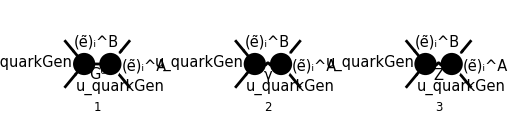

```mathematica
diagsLO[0]=InsertFields[
CreateTopologies[0,2->2],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|5],
V[3],
F[11|12],
S[11|13|14]
}
];
Paint[
diagsLO[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

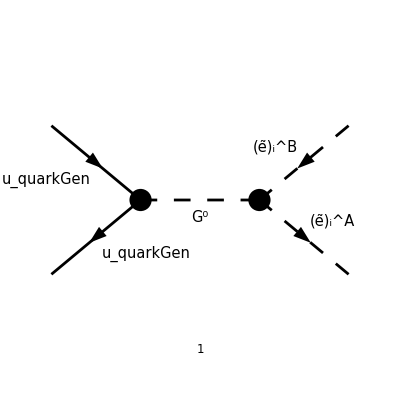

```mathematica
diagsLOGold[0]=DiagramExtract[diagsLO[0],1];
Paint[
diagsLOGold[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MLOGold[0]=FCFAConvert[
CreateFeynAmp[diagsLOGold[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k,k2},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
List->False,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->4
]
```

-((e MLE(i) (USf(2,i)(A,1) Conjugate[(USf(2,i)(B,2))] (MUE TB-Conjugate[Af(2,i,i)])+USf(2,i)(A,2) Conjugate[(USf(2,i)(B,1))] (Af(2,i,i)-TB Conjugate[MUE])) (φ(-OverBar[p_2],MQU(quarkGen))).((e (γ̄)^7 MQU(quarkGen) δ_Col1Col2)/(2 m_W (sin(θ_W)))-(e (γ̄)^6 MQU(quarkGen) δ_Col1Col2)/(2 m_W (sin(θ_W)))).(φ(OverBar[p_1],MQU(quarkGen))))/(2 m_W (sin(θ_W)) ((k̄+OverBar[k_1])^2-m_Z^2)))

```mathematica
MLOGold[1]=MLOGold[0]//DiracSimplify//FullSimplify
%/.{MQU[quarkGen]->0}
```

(e^2 MLE(i) MQU(quarkGen) δ_Col1Col2 ((φ(-OverBar[p_2],MQU(quarkGen))).(γ̄)^6.(φ(OverBar[p_1],MQU(quarkGen)))-(φ(-OverBar[p_2],MQU(quarkGen))).(γ̄)^7.(φ(OverBar[p_1],MQU(quarkGen)))) (USf(2,i)(A,1) Conjugate[(USf(2,i)(B,2))] (MUE TB-Conjugate[Af(2,i,i)])+USf(2,i)(A,2) Conjugate[(USf(2,i)(B,1))] (Af(2,i,i)-TB Conjugate[MUE])))/(4 m_W^2 (sin(θ_W))^2 ((k̄+OverBar[k_1])^2-m_Z^2))

0

```mathematica
MLOGoldSquared[0]=ComplexConjugate[MLOGold[1]]MLOGold[1]//FermionSpinSum[#,ExtraFactor->1/(4SUNN)]&//DiracSimplify//FullSimplify
%/.{MQU[quarkGen]->0}
```

1/(16 N m_W^4 (sin(θ_W))^4)e^4 (MLE(i))^2 (MQU(quarkGen))^2 δ_Col1Col2^2 (OverBar[p_1]·OverBar[p_2]+(MQU(quarkGen))^2) (1/((k̄+OverBar[k_1])^2-m_Z^2))^2 (USf(2,i)(A,1) Conjugate[(USf(2,i)(B,2))] (MUE TB-Conjugate[Af(2,i,i)])+USf(2,i)(A,2) Conjugate[(USf(2,i)(B,1))] (Af(2,i,i)-TB Conjugate[MUE]))^2

0

#### Emission

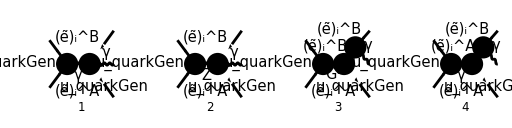

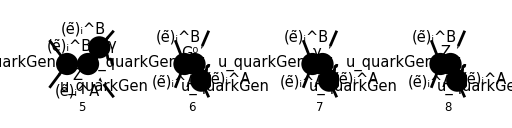

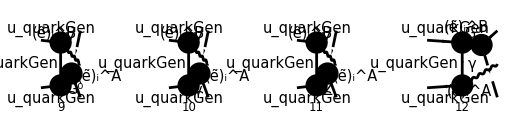

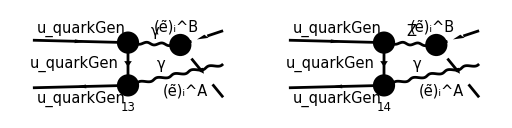

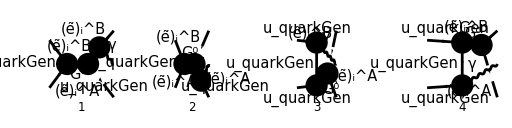

```mathematica
diagsEmission[0]=InsertFields[
CreateTopologies[0,2->3],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|5],
V[3],
F[11|12],
S[11|13|14]
}
];
Paint[
diagsEmission[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MEmissionGold[0]=FCFAConvert[
CreateFeynAmp[diagsEmissionGold[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k,k2},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
List->False,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->4
]
```

-(e^2 MLE(i) (-k̄-2 OverBar[k_2])^μ ((ε̄)^*)^μ(k) (USf(2,i)(A,1) Conjugate[(USf(2,i)(B,2))] (MUE TB-Conjugate[Af(2,i,i)])+USf(2,i)(A,2) Conjugate[(USf(2,i)(B,1))] (Af(2,i,i)-TB Conjugate[MUE])) (φ(-OverBar[p_2],MQU(quarkGen))).((e (γ̄)^7 MQU(quarkGen) δ_Col1Col2)/(2 m_W (sin(θ_W)))-(e (γ̄)^6 MQU(quarkGen) δ_Col1Col2)/(2 m_W (sin(θ_W)))).(φ(OverBar[p_1],MQU(quarkGen))))/(2 m_W (sin(θ_W)) ((k̄+OverBar[k_2])^2-m_l_iA^2) ((k̄+OverBar[k_1]+OverBar[k_2])^2-m_Z^2))+(e^2 MLE(i) (-k̄-2 OverBar[k_1])^μ ((ε̄)^*)^μ(k) (USf(2,i)(A,1) Conjugate[(USf(2,i)(B,2))] (MUE TB-Conjugate[Af(2,i,i)])+USf(2,i)(A,2) Conjugate[(USf(2,i)(B,1))] (Af(2,i,i)-TB Conjugate[MUE])) (φ(-OverBar[p_2],MQU(quarkGen))).((e (γ̄)^7 MQU(quarkGen) δ_Col1Col2)/(2 m_W (sin(θ_W)))-(e (γ̄)^6 MQU(quarkGen) δ_Col1Col2)/(2 m_W (sin(θ_W)))).(φ(OverBar[p_1],MQU(quarkGen))))/(2 m_W (sin(θ_W)) ((-k̄-OverBar[k_1])^2-m_l_iB^2) ((k̄+OverBar[k_1]+OverBar[k_2])^2-m_Z^2))-(ⅈ e MLE(i) ((ε̄)^*)^μ(k) (USf(2,i)(A,1) Conjugate[(USf(2,i)(B,2))] (MUE TB-Conjugate[Af(2,i,i)])+USf(2,i)(A,2) Conjugate[(USf(2,i)(B,1))] (Af(2,i,i)-TB Conjugate[MUE])) (φ(-OverBar[p_2],MQU(quarkGen))).(-2/3 ⅈ e (γ̄)^μ δ_Col1Col2).(γ̄·(k̄-OverBar[p_2])+MQU(quarkGen)).((e (γ̄)^7 MQU(quarkGen))/(2 m_W (sin(θ_W)))-(e (γ̄)^6 MQU(quarkGen))/(2 m_W (sin(θ_W)))).(φ(OverBar[p_1],MQU(quarkGen))))/(2 m_W (sin(θ_W)) ((OverBar[k_1]+OverBar[k_2])^2-m_Z^2) ((OverBar[p_2]-k̄)^2-(MQU(quarkGen))^2))-(ⅈ e MLE(i) ((ε̄)^*)^μ(k) (USf(2,i)(A,1) Conjugate[(USf(2,i)(B,2))] (MUE TB-Conjugate[Af(2,i,i)])+USf(2,i)(A,2) Conjugate[(USf(2,i)(B,1))] (Af(2,i,i)-TB Conjugate[MUE])) (φ(-OverBar[p_2],MQU(quarkGen))).((e (γ̄)^7 MQU(quarkGen) δ_Col1Col2)/(2 m_W (sin(θ_W)))-(e (γ̄)^6 MQU(quarkGen) δ_Col1Col2)/(2 m_W (sin(θ_W)))).(γ̄·(OverBar[k_1]+OverBar[k_2]-OverBar[p_2])+MQU(quarkGen)).(-2/3 ⅈ e (γ̄)^μ).(φ(OverBar[p_1],MQU(quarkGen))))/(2 m_W (sin(θ_W)) ((OverBar[k_1]+OverBar[k_2])^2-m_Z^2) ((-OverBar[k_1]-OverBar[k_2]+OverBar[p_2])^2-(MQU(quarkGen))^2))

```mathematica
MEmissionGold[1]=MEmissionGold[0]//DiracSimplify//FullSimplify
%/.{MQU[quarkGen]->0}
```

1/(12 m_W^2 (sin(θ_W))^2)e^3 MLE(i) MQU(quarkGen) δ_Col1Col2 (USf(2,i)(A,1) Conjugate[(USf(2,i)(B,2))] (MUE TB-Conjugate[Af(2,i,i)])+USf(2,i)(A,2) Conjugate[(USf(2,i)(B,1))] (Af(2,i,i)-TB Conjugate[MUE])) (1/((k̄+OverBar[k_1]+OverBar[k_2])^2-m_Z^2)3 ((φ(-OverBar[p_2],MQU(quarkGen))).(γ̄)^6.(φ(OverBar[p_1],MQU(quarkGen)))-(φ(-OverBar[p_2],MQU(quarkGen))).(γ̄)^7.(φ(OverBar[p_1],MQU(quarkGen)))) ((k̄·(ε̄)^*(k)+2 (OverBar[k_1]·(ε̄)^*(k)))/((k̄+OverBar[k_1])^2-m_l_iB^2)-(k̄·(ε̄)^*(k)+2 (OverBar[k_2]·(ε̄)^*(k)))/((k̄+OverBar[k_2])^2-m_l_iA^2))+1/((OverBar[k_1]+OverBar[k_2])^2-m_Z^2)2 ((2 (OverBar[p_2]·(ε̄)^*(k)) ((φ(-OverBar[p_2],MQU(quarkGen))).(γ̄)^7.(φ(OverBar[p_1],MQU(quarkGen)))-(φ(-OverBar[p_2],MQU(quarkGen))).(γ̄)^6.(φ(OverBar[p_1],MQU(quarkGen))))+(φ(-OverBar[p_2],MQU(quarkGen))).(γ̄·(ε̄)^*(k)).(γ̄·k̄).(γ̄)^6.(φ(OverBar[p_1],MQU(quarkGen)))-(φ(-OverBar[p_2],MQU(quarkGen))).(γ̄·(ε̄)^*(k)).(γ̄·k̄).(γ̄)^7.(φ(OverBar[p_1],MQU(quarkGen))))/((k̄-OverBar[p_2])^2-(MQU(quarkGen))^2)+((φ(-OverBar[p_2],MQU(quarkGen))).(γ̄·OverBar[k_1]).(γ̄·(ε̄)^*(k)).(γ̄)^6.(φ(OverBar[p_1],MQU(quarkGen)))-(φ(-OverBar[p_2],MQU(quarkGen))).(γ̄·OverBar[k_1]).(γ̄·(ε̄)^*(k)).(γ̄)^7.(φ(OverBar[p_1],MQU(quarkGen)))+(φ(-OverBar[p_2],MQU(quarkGen))).(γ̄·OverBar[k_2]).(γ̄·(ε̄)^*(k)).(γ̄)^6.(φ(OverBar[p_1],MQU(quarkGen)))-(φ(-OverBar[p_2],MQU(quarkGen))).(γ̄·OverBar[k_2]).(γ̄·(ε̄)^*(k)).(γ̄)^7.(φ(OverBar[p_1],MQU(quarkGen))))/((OverBar[k_1]+OverBar[k_2]-OverBar[p_2])^2-(MQU(quarkGen))^2)))

0

```mathematica
MEmissionGoldSquared[0]=ComplexConjugate[MEmissionGold[1]]MEmissionGold[1]//FermionSpinSum[#,ExtraFactor->1/(4SUNN)]&//DiracSimplify
%/.{MQU[quarkGen]->0}
```

(MUE^2 TB^2 (Conjugate[(USf(2,i)(B,2))])^2 6 δ_Col1Col2^2 (USf(2,i)(A,1))^2 e^6)/(16 N m_W^4 (sin(θ_W))^4)+3238+(TB Conjugate[MUE] Conjugate[Af(2,i,i)] 10 USf(2,i)(A,1) USf(2,i)(A,2) e^6)/(18 N m_W^4 (sin(θ_W))^4)
 |  |  |  |

0

#### Virtual

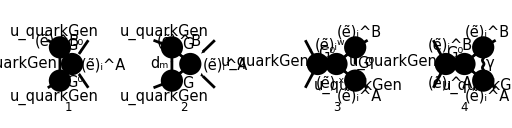

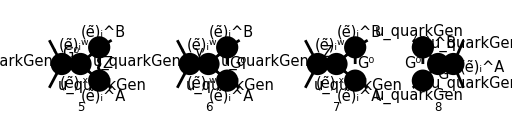

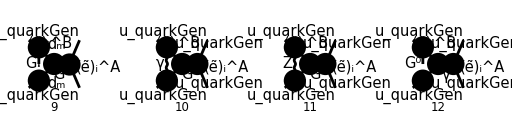

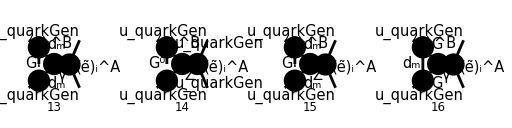

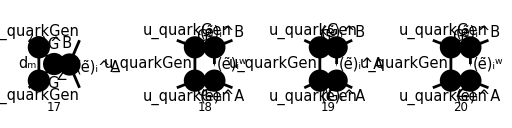

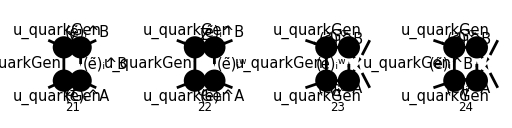

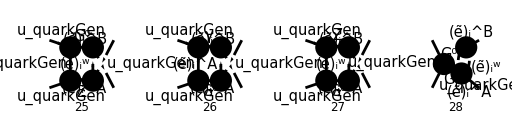

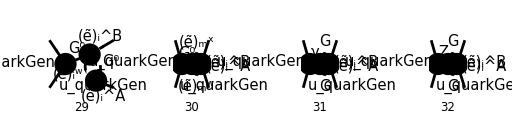

```mathematica
diagsVirtualGold[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles,SelfEnergies}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|5],
V[3],
F[11|12],
S[11|13|14]
},
LastSelections->{S[4|6]}
];
Paint[
diagsVirtualGold[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
diagsVirtualGold[1]=DiagramExtract[diagsVirtualGold[0],{4,10,11,19,21,24,26,30}];
Paint[
diagsVirtualGold[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
MVirtualGold[0]=FCFAConvert[
CreateFeynAmp[diagsVirtualGold[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
List->False,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->4
]
```

(ⅈ (φ(-OverBar[p_2],MQU(quarkGen))).(((γ̄)^7 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))-((γ̄)^6 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))).(φ(OverBar[p_1],MQU(quarkGen))) MLE(i) (ḡ)^μν (k̄+2 OverBar[k_1])^μ (k̄-2 OverBar[k_2])^ν e^3 ((MUE TB-Conjugate[Af(2,i,i)]) Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,1)+(Af(2,i,i)-TB Conjugate[MUE]) Conjugate[(USf(2,i)(B,1))] USf(2,i)(A,2)))/(32 π^4 (k̄)^2.((k̄+OverBar[k_1])^2-m_l_iB^2).((k̄-OverBar[k_2])^2-m_l_iA^2) ((OverBar[k_1]+OverBar[k_2])^2-m_Z^2) m_W (sin(θ_W)))-(ⅈ (φ(-OverBar[p_2],MQU(quarkGen))).(((γ̄)^7 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))-((γ̄)^6 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))).(φ(OverBar[p_1],MQU(quarkGen))) MLE(Gen5) e^3 (2 Conjugate[(USf(2,i)(B,2))] (2 CB^2 Conjugate[(USf(2,i)(Sfe6,2))] IndexDelta(i,Gen5) m_W^2 USf(2,i)(A,2) USf(2,i)(Sfe5,2) (sin(θ_W))^2+2 CB^2 Conjugate[(USf(2,Gen5)(Sfe6,2))] m_W^2 USf(2,i)(A,2) USf(2,Gen5)(Sfe5,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(Sfe6,1))] IndexDelta(i,Gen5) ((MLE(i))^2 (cos(θ_W))^2 USf(2,i)(A,2) USf(2,i)(Sfe5,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,1) USf(2,i)(Sfe5,2))+Conjugate[(USf(2,Gen5)(Sfe6,1))] (MLE(i) MLE(Gen5) (cos(θ_W))^2 USf(2,i)(A,1) USf(2,Gen5)(Sfe5,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,Gen5)(Sfe5,1)))+Conjugate[(USf(2,i)(B,1))] (CB^2 Conjugate[(USf(2,i)(Sfe6,1))] IndexDelta(i,Gen5) USf(2,i)(A,1) USf(2,i)(Sfe5,1) m_W^2+CB^2 Conjugate[(USf(2,Gen5)(Sfe6,1))] USf(2,i)(A,1) USf(2,Gen5)(Sfe5,1) m_W^2+2 Conjugate[(USf(2,i)(Sfe6,2))] IndexDelta(i,Gen5) ((MLE(i))^2 (cos(θ_W))^2 USf(2,i)(A,1) USf(2,i)(Sfe5,2)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,2) USf(2,i)(Sfe5,1))+2 Conjugate[(USf(2,Gen5)(Sfe6,2))] (MLE(i) MLE(Gen5) (cos(θ_W))^2 USf(2,i)(A,2) USf(2,Gen5)(Sfe5,1)-CB^2 m_W^2 (sin(θ_W))^2 USf(2,i)(A,1) USf(2,Gen5)(Sfe5,2)))) ((MUE TB-Conjugate[Af(2,Gen5,Gen5)]) Conjugate[(USf(2,Gen5)(Sfe5,2))] USf(2,Gen5)(Sfe6,1)+(Af(2,Gen5,Gen5)-TB Conjugate[MUE]) Conjugate[(USf(2,Gen5)(Sfe5,1))] USf(2,Gen5)(Sfe6,2)))/(128 CB^2 π^4 ((k̄)^2-m_l_Gen5Sfe5^2).((k̄-OverBar[k_1]-OverBar[k_2])^2-m_l_Gen5Sfe6^2) ((OverBar[k_1]+OverBar[k_2])^2-m_Z^2) (cos(θ_W))^2 m_W^3 (sin(θ_W))^3)-((φ(-OverBar[p_2],MQU(quarkGen))).(-2/3 ⅈ (γ̄)^μ e δ_Col1Col2).(γ̄·k̄+MQU(quarkGen)).(((γ̄)^7 MQU(quarkGen) e)/(2 m_W (sin(θ_W)))-((γ̄)^6 MQU(quarkGen) e)/(2 m_W (sin(θ_W)))).(φ(OverBar[p_1],MQU(quarkGen))) MLE(i) (ḡ)^μν (-k̄+2 OverBar[k_1]-OverBar[p_2])^ν e^2 ((MUE TB-Conjugate[Af(2,i,i)]) Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,1)+(Af(2,i,i)-TB Conjugate[MUE]) Conjugate[(USf(2,i)(B,1))] USf(2,i)(A,2)))/(32 π^4 ((k̄)^2-(MQU(quarkGen))^2).(k̄+OverBar[p_2])^2.((k̄-OverBar[k_1]+OverBar[p_2])^2-m_l_iB^2).((k̄-OverBar[k_1]-OverBar[k_2]+OverBar[p_2])^2-m_Z^2) m_W (sin(θ_W)))+((φ(-OverBar[p_2],MQU(quarkGen))).(-2/3 ⅈ (γ̄)^μ e δ_Col1Col2).(γ̄·k̄+MQU(quarkGen)).(((γ̄)^7 MQU(quarkGen) e)/(2 m_W (sin(θ_W)))-((γ̄)^6 MQU(quarkGen) e)/(2 m_W (sin(θ_W)))).(φ(OverBar[p_1],MQU(quarkGen))) MLE(i) (ḡ)^μν (-k̄+2 OverBar[k_2]-OverBar[p_2])^ν e^2 ((MUE TB-Conjugate[Af(2,i,i)]) Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,1)+(Af(2,i,i)-TB Conjugate[MUE]) Conjugate[(USf(2,i)(B,1))] USf(2,i)(A,2)))/(32 π^4 ((k̄)^2-(MQU(quarkGen))^2).(k̄+OverBar[p_2])^2.((k̄-OverBar[k_2]+OverBar[p_2])^2-m_l_iA^2).((k̄-OverBar[k_1]-OverBar[k_2]+OverBar[p_2])^2-m_Z^2) m_W (sin(θ_W)))-((φ(-OverBar[p_2],MQU(quarkGen))).(((γ̄)^7 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))-((γ̄)^6 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))).(γ̄·k̄+MQU(quarkGen)).(-2/3 ⅈ (γ̄)^μ e).(φ(OverBar[p_1],MQU(quarkGen))) MLE(i) (ḡ)^μν (k̄+OverBar[k_1]-OverBar[k_2]+OverBar[p_2])^ν e^2 ((MUE TB-Conjugate[Af(2,i,i)]) Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,1)+(Af(2,i,i)-TB Conjugate[MUE]) Conjugate[(USf(2,i)(B,1))] USf(2,i)(A,2)))/(32 π^4 ((k̄)^2-(MQU(quarkGen))^2).((k̄+OverBar[p_2])^2-m_Z^2).((k̄-OverBar[k_2]+OverBar[p_2])^2-m_l_iB^2).(k̄-OverBar[k_1]-OverBar[k_2]+OverBar[p_2])^2 m_W (sin(θ_W)))+((φ(-OverBar[p_2],MQU(quarkGen))).(((γ̄)^7 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))-((γ̄)^6 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))).(γ̄·k̄+MQU(quarkGen)).(-2/3 ⅈ (γ̄)^μ e).(φ(OverBar[p_1],MQU(quarkGen))) MLE(i) (ḡ)^μν (k̄-OverBar[k_1]+OverBar[k_2]+OverBar[p_2])^ν e^2 ((MUE TB-Conjugate[Af(2,i,i)]) Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,1)+(Af(2,i,i)-TB Conjugate[MUE]) Conjugate[(USf(2,i)(B,1))] USf(2,i)(A,2)))/(32 π^4 ((k̄)^2-(MQU(quarkGen))^2).((k̄+OverBar[p_2])^2-m_Z^2).((k̄-OverBar[k_1]+OverBar[p_2])^2-m_l_iA^2).(k̄-OverBar[k_1]-OverBar[k_2]+OverBar[p_2])^2 m_W (sin(θ_W)))-(ⅈ (φ(-OverBar[p_2],MQU(quarkGen))).(-2/3 ⅈ (γ̄)^ν e).(γ̄·(-k̄-OverBar[p_2])+MQU(quarkGen)).(((γ̄)^7 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))-((γ̄)^6 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))).(γ̄·(-k̄+OverBar[k_1]+OverBar[k_2]-OverBar[p_2])+MQU(quarkGen)).(-2/3 ⅈ (γ̄)^μ e).(φ(OverBar[p_1],MQU(quarkGen))) MLE(i) (ḡ)^μν e ((MUE TB-Conjugate[Af(2,i,i)]) Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,1)+(Af(2,i,i)-TB Conjugate[MUE]) Conjugate[(USf(2,i)(B,1))] USf(2,i)(A,2)))/(32 π^4 (k̄)^2.((k̄+OverBar[p_2])^2-(MQU(quarkGen))^2).((k̄-OverBar[k_1]-OverBar[k_2]+OverBar[p_2])^2-(MQU(quarkGen))^2) ((-OverBar[k_1]-OverBar[k_2])^2-m_Z^2) m_W (sin(θ_W)))-(ⅈ (φ(-OverBar[p_2],MQU(quarkGen))).((2 ⅈ (γ̄)^ν.(γ̄)^6 e (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ (γ̄)^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(γ̄·(-k̄-OverBar[p_2])+MQU(quarkGen)).(((γ̄)^7 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))-((γ̄)^6 MQU(quarkGen) e δ_Col1Col2)/(2 m_W (sin(θ_W)))).(γ̄·(-k̄+OverBar[k_1]+OverBar[k_2]-OverBar[p_2])+MQU(quarkGen)).((2 ⅈ (γ̄)^μ.(γ̄)^6 e (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ (γ̄)^μ.(γ̄)^7 e (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1],MQU(quarkGen))) MLE(i) (ḡ)^μν e ((MUE TB-Conjugate[Af(2,i,i)]) Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,1)+(Af(2,i,i)-TB Conjugate[MUE]) Conjugate[(USf(2,i)(B,1))] USf(2,i)(A,2)))/(32 π^4 ((k̄)^2-m_Z^2).((k̄+OverBar[p_2])^2-(MQU(quarkGen))^2).((k̄-OverBar[k_1]-OverBar[k_2]+OverBar[p_2])^2-(MQU(quarkGen))^2) ((-OverBar[k_1]-OverBar[k_2])^2-m_Z^2) m_W (sin(θ_W)))

```mathematica
MVirtualGold[1]=MVirtualGold[0]//DiracSimplify
%/.{MQU[quarkGen]->0}
```

839+(ⅈ 12 1)/(64 5 1^2)
 |  |  |  |

0

```mathematica
MVirtualGoldSquared[0]=ComplexConjugate[MVirtualGold[1]]MVirtualGold[1]//FermionSpinSum[#,ExtraFactor->1/(4SUNN)]&//DiracSimplify
%/.{MQU[quarkGen]->0}
```

(MUE^2 TB^2 (Conjugate[(USf(2,i)(B,2))])^2 (1/1)^2 (MLE(i))^2 (MQU(quarkGen))^8 e^8 δ_Col1Col2^2 (USf(2,i)(A,1))^2)/(648 π^8 N (k̄)^2.(1^2-1^2).((1)^2-(MQU(quarkGen))^2) 1 (cos(θ_W))^2 m_W^4 (sin(θ_W))^2)+79808+1/1
 |  |  |  |

0

```mathematica
exprNum[0]//ReplaceAll[#,top1kiRules]&//FullSimplify//ReplaceAll[#,SPDxyzRules]&//FCE//ReplaceAll[#,{
SPD[k1,k2]->s z(1-Mp)
}]&//FullSimplify//FRH//ReplaceAll[#,SPDp1kiRules]&//FullSimplify//ReplaceAll[#,{
m1->Sqrt[s z] Sqrt[1/2 (Mp+Mm)],
m2->Sqrt[s z] Sqrt[1/2(Mp-Mm)]
}]&//FullSimplify//ReplaceAll[#,xyzSimplifyRules]&//Collect2[#,Φ,Factoring->FullSimplify,IsolateNames->KK]&
64/(s^5 Z^2)%//FRH//FullSimplify//Collect2[#,Φ,Factoring->FullSimplify,IsolateNames->KK]&
```

1/128 KK(720) Φ^3+1/128 KK(761) Φ^2+1/256 KK(752) Φ+(KK(773))/256

1/2 KK(774) Φ^3+1/2 KK(776) Φ^2+1/4 KK(751) Φ+(KK(772))/4

```mathematica
KK[776]//FRH//ReplaceAll[#,xyzSimplifyRules]&//ReplaceAll[#,{Xp->1+x,Xm->1-x}]&//FullSimplify//ReplaceAll[#,y+2Y->1+Y]&
KK[751]//FRH//ReplaceAll[#,{Xp->1+x,Xm->1-x}]&//FullSimplify//Collect2[#,{Mm,Mp},Factoring->FullSimplify]&//ReplaceAll[#,xyzSimplifyRules]&//ReplaceAll[#,{z-Z+1->2z,y+Y->1,y+Y z->z+y Z}]&//Collect2[#,{y,Y},Factoring->FullSimplify]&
```

2 x ((2 Mp-3) Y z+y+Z)-4 Mm (Y+1) z

-4 y^2 (Mm x z (Z+2)+Mp z Z+Z)-4 y Y z (4 Mm x z-2 Mp Z+Z)-4 Y^2 z (Mm x (2 z+Z)+Mp Z)+4 Y z (z (4 Mm (Mm-(Mp-2) x)-1)+x Z ((2 Mp-3) x-2 Mm)+Z)+y (4 Z (-2 (Mp-2) z+x^2+1)-4 z)-8 z (Mp (z-2)-2 z+2)

```mathematica
KK[772]//FRH//ReplaceAll[#,{Xm->1-x,Xp->1+x}]&//Collect2[#,{Mm,Mp},Factoring->FullSimplify]&//ReplaceAll[#,xyzSimplifyRules]&//ReplaceAll[#,{Y Z-1->-y-z Y}]&//FullSimplify//ReplaceAll[#,Y+Z-1->Z-y]&//ReplaceAll[#,xyzSimplifyRules]&//Collect2[#,{y,Y},Factoring->FullSimplify]&//ReplaceAll[#,-8z^2+z(Z-2)+Z^2->Z-2z(1+4z)]&//ReplaceAll[#,2z(Z+5)+Z^2+Z+2->z Z+4(1+2z)]&//Collect2[#,{y,Y},Factoring->FullSimplify]&
```

-4 Y^2 z (z (-2 Mm^2 x Z-Mm (x^2-5) Z+8 Mm z+3 x (4 z+Z))+2 Mp^2 x z (2 z-Z)+2 Mp x (Z-2 z (4 z+1)))+4 y Y z (-4 Mm Mp z Z+Mm (x^2+1) Z^2+Z (Mm x-2) (x-2 Mm z)-8 z (Mm+x)-2 Mp^2 x z (Z+2)+2 Mp x (z (Z+8)+4))+y^3 (4 Mm z Z+4 x (Mp z (Z-2)-1))+4 y^2 Y z (Mm (z-3) Z+2 Mm+Mp x z (Z-4)-2 Mp x (Z+2)+x)+4 y Y^2 z (-2 Mm z (Z-2)+(5-10 Mp) x z+Mp x Z)-4 y z (x (Mm x Z+2 Mp Z+4)+Mm Z)+4 Y^3 z^2 (Mm (2 z+Z)+(3-4 Mp) x z+Mp x Z)-8 Y z (2 Mm (Mp-2) z-x (4 (Mp-3) Mp z+Mp Z+6 z))+4 x y^2 (4 (Mp+1) z+Z)

```mathematica
testFunc[expr_]:=ReplaceAll[expr,{Z->1-z,Y->1-y}];
```

```mathematica
KK[772]//FRH//testFunc//FullSimplify
```

2 Xm (-y z (z^2 (6 Mm^2-4 Mm Mp+Mm+14 Mp^2-25 Mp+9)-z (6 Mm^2+2 Mp (9 Mp-14)+7)+Mm+7 Mp-6)+y^2 (z-1) (z (4 Mm^2 z+2 Mp (z (-2 Mm+4 Mp-3)-5)+7)+1)+z^2 (2 Mm^2 (z-1)-Mm (4 Mp+z-3)+(2 Mp-3) (Mp (3 z-5)-2 z+3))+y^3 (z-1)^2 (z (2 Mm-6 Mp+3)+1))-2 Xp (y^2 (z-1) (z (4 Mm^2 z+2 Mp z (2 Mm+Xp-3)+2 Mm Xp (z-1)+8 Mp^2 z-2 Mp (Xp+5)+7)+1)+y z (-(z^2 (6 Mm^2+Mm (4 Mp+3 Xp-1)+Mp (14 Mp+3 Xp-25)+9))+z (6 Mm^2+4 Xp (Mm+Mp)+2 Mp (9 Mp-14)+7)-Mm Xp+Mm-Mp Xp-7 Mp+6)+z^2 (2 Mm^2 (z-1)+Mm (4 Mp+Xp (z-1)+z-3)+Mp (z (6 Mp+Xp-13)-10 Mp-Xp+21)+6 z-9)+y^3 (-(z-1)^2) (z (2 Mm+6 Mp-3)-1))-2 Xm^2 (2 y-1) (z-1) z (Mm-Mp) (y (z-1)-z)

```mathematica
KK[772]//FRH//testFunc//FullSimplify
```

2 Xm (-y z (z^2 (6 Mm^2-4 Mm Mp+Mm+14 Mp^2-25 Mp+9)-z (6 Mm^2+2 Mp (9 Mp-14)+7)+Mm+7 Mp-6)+y^2 (z-1) (z (4 Mm^2 z+2 Mp (z (-2 Mm+4 Mp-3)-5)+7)+1)+z^2 (2 Mm^2 (z-1)-Mm (4 Mp+z-3)+(2 Mp-3) (Mp (3 z-5)-2 z+3))+y^3 (z-1)^2 (z (2 Mm-6 Mp+3)+1))-2 Xp (y^2 (z-1) (z (4 Mm^2 z+2 Mp z (2 Mm+Xp-3)+2 Mm Xp (z-1)+8 Mp^2 z-2 Mp (Xp+5)+7)+1)+y z (-(z^2 (6 Mm^2+Mm (4 Mp+3 Xp-1)+Mp (14 Mp+3 Xp-25)+9))+z (6 Mm^2+4 Xp (Mm+Mp)+2 Mp (9 Mp-14)+7)-Mm Xp+Mm-Mp Xp-7 Mp+6)+z^2 (2 Mm^2 (z-1)+Mm (4 Mp+Xp (z-1)+z-3)+Mp (z (6 Mp+Xp-13)-10 Mp-Xp+21)+6 z-9)+y^3 (-(z-1)^2) (z (2 Mm+6 Mp-3)-1))-2 Xm^2 (2 y-1) (z-1) z (Mm-Mp) (y (z-1)-z)

```mathematica
mt1
```

(m̂)_1

```mathematica
SubscriptBox["m","1"]
```

SubscriptBox[m,1]

```mathematica
quadSqrt=Sqrt[b^2-4a c]
```

√(b^2-4 a c)

```mathematica
a x^2+b x+c
a(x-(-b+quadSqrt)/(2a))(x-(-b-quadSqrt)/(2a))//Expand//FullSimplify
```

a x^2+b x+c

a x^2+b x+c

```mathematica
c2=KK[495]//FRH;
c1=KK[490]//FRH;
c0=KK[523]//FRH;
```

```mathematica
c1^2-4(1+c2)c0//ReplaceAll[#,XYZToxyzRules]&//FullSimplify
```

((1-z) z (x^2 (1-2 ((m̂)_1^2+(m̂)_2^2-2) (y-1))-((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) x (4 (y-1) y+3)-((m̂)_1^2+(m̂)_2^2) (1-2 y)^2-2 ((m̂)_1^2+(m̂)_2^2-1) y+1)+z (4 (m̂)_1^4 (x-1) (y-1) z+(m̂)_1^2 (z (8 (m̂)_2^2 (y-1)-8 x y+6 x-2)+4)-4 (m̂)_2^4 (x+1) (y-1) z+(m̂)_2^2 (z (x (8 y-6)-2)+4)+3 z-4)+y (z-1)^2 (x^2-y+1))^2-4 (2 (m̂)_1^2 z (x (-y)+x+y-2)-2 (m̂)_2^2 z (x (y-1)+y-2)+x (3 y z+y-4 z+1)+1) (-(((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) x^2 (2 y-1) (z-1) z (y (z-1)-z))+x (-z^2 (1-2 ((m̂)_1^2+(m̂)_2^2-2) (y-1)) (2 (m̂)_1^2 (z-2)+2 (m̂)_2^2 (z-2)-3 z+4)+z (z-1)^2 ((m̂)_1^2 (y (2 y (3 y-7)+9)-2)+(m̂)_2^2 (y (2 y (3 y-7)+9)-2)+y ((9-4 y) y-2))+(1-z) z (4 (m̂)_1^4 (y-1) (3 y-1) z+(m̂)_1^2 (z (2 y (4 (m̂)_2^2 (y-1)-8 y+7)-1)+2)+4 (m̂)_2^4 (y-1) (3 y-1) z-(m̂)_2^2 (2 y (8 y-7) z+z-2)+y (8 y z+z-4)-3 z)+(y-1) y^2 (z-1)^3)+2 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) (y-1) z (-2 ((m̂)_1^2+(m̂)_2^2) y z (z-1)+z (2 ((m̂)_1^2+(m̂)_2^2-1)+z)+y^2 (z-1)^2))

```mathematica
yzToYZ[expr_]:=ReplaceAll[expr,{
1-z->Z,
z-1->-Z,
1-y->Y,
y-1->-Y
}];
YZToyz[expr_]:=ReplaceAll[expr,{
Z->1-z,
Y->1-y
}];
xyzSimplify[expr_]:=ReplaceAll[expr,{
y+Y->1,
z+Z->1,
z-2->-1-Z,
y-2->-1-Y
}];
```

```mathematica
ABToxyz[expr_]:=ReplaceAll[expr,{
B->z Y(x+2(mt1^2-mt2^2))-x y,
A->2Sqrt[y Y z (xp-x)(x-xm)]
}];
```

```mathematica
y^(d-4)Y^(d-4)((1+c2)B^2+c1 B+c0);
%//BToxyz//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&
```

KK(673) y^(d-4) Y^(d-1)-KK(740) y^(d-4) Y^(d-2)+KK(747) y^(d-4) Y^(d-3)+KK(756) y^(d-4) Y^(d-4)+KK(693) y^(d-3) Y^(d-3)+KK(708) y^(d-3) Y^(d-2)+KK(754) y^(d-3) Y^(d-4)+KK(716) y^(d-2) Y^(d-3)+KK(721) y^(d-2) Y^(d-4)+KK(749) y^(d-1) Y^(d-4)

```mathematica
K1 y^(d-4)(1-y)^(d-1)-K2 y^(d-4)Y^(d-2)+K3 y^(d-4)Y^(d-3)+K4 y^(d-4)Y^(d-4)+K
```

```mathematica
Integrate[%,{y,0,1}]
```

1/(d+1/2)√π 4^(1-d) (2 d-3) (2 d-1) d-3 ((d-3) (x ((m̂)_1^2 yYCoeff(1563) z+(m̂)_2^2 yYCoeff(1561) z-2 x^2 yYCoeff(1558) z+yYCoeff(1557) Z^2)-2 (m̂)_1^4 yYCoeff(1525) z^2 Z-2 (m̂)_2^4 yYCoeff(1552) z^2 Z)+2 (d-2) (x (x^2 (-yYCoeff(1570))+x yYCoeff(1567)+yYCoeff(1569) z Z)+yYCoeff(1492) yYCoeff(1493) z^2 Z)+4 (2 d-5) x yYCoeff(1573) z^2+(d-3) yYCoeff(1490) z+2 (2 d-5) yYCoeff(1502) z-2 (d-2) yYCoeff(1521) z+2 (d-3) yYCoeff(1542) z+2 (2 d-5) yYCoeff(1549) z+(d-1) yYCoeff(1555) z+(d-1) yYCoeff(1565) Z)

```mathematica
Block[{KK[721]},Integrate[%,{y,0,1}]]//FullSimplify
```

Block::lvsym: Local variable specification {KK(721)} contains KK(721), which is not a symbol or an assignment to a symbol.

Block[{KK(721)},∫_0^1 %ⅆy]

```mathematica
y^(d-4)Y^(d-4)((1+c2)B^2+c1 B+c0);
%//BToxyz//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&//YZToyz
int2=ReplaceAll[%,{
y^a_ (1-y)^b_->Gamma[a+1]Gamma[b+1]/Gamma[a+b+2]
}]//FullSimplify
```

KK(721) y^(d-2) (1-y)^(d-4)+KK(749) y^(d-1) (1-y)^(d-4)+KK(754) y^(d-3) (1-y)^(d-4)+KK(756) y^(d-4) (1-y)^(d-4)+KK(693) y^(d-3) (1-y)^(d-3)+KK(716) y^(d-2) (1-y)^(d-3)+KK(747) y^(d-4) (1-y)^(d-3)+KK(708) y^(d-3) (1-y)^(d-2)-KK(740) y^(d-4) (1-y)^(d-2)+KK(673) y^(d-4) (1-y)^(d-1)

1/(d-3/2)√π 4^(2-d) ((d-1) KK(673)+2 (d-3) KK(693)+d (KK(708)+KK(716)+2 KK(721)-2 KK(740)+4 KK(747)+KK(749)+4 KK(754)+8 KK(756))-3 KK(708)-3 KK(716)-4 KK(721)+4 KK(740)-10 KK(747)-KK(749)-10 (KK(754)+2 KK(756))) d-3

```mathematica
Hold[]
```

```mathematica
FCCompareResults[int1,int2];
```

Check of the results: The results disagree.

```mathematica
Integrate[y^a(1-y)^b,{y,0,1}]
```

ConditionalExpression[(a+1 b+1)/(a+b+2), Re(a)>-1∧Re(b)>-1]

```mathematica
exprNum[0]//top1ki//FullSimplify//pikikToxyz//FCE//ReplaceAll[#,{
SPD[k1,k2]->(s z-m1^2-m2^2)
}]&//FullSimplify//FRH//p1kiToyzPhi//FullSimplify//ReplaceAll[#,{
m1->Sqrt[s z] mt1,
m2->Sqrt[s z] mt2
}]&//FullSimplify//xyzSimplify//Collect2[#,Φ,Factoring->FullSimplify,IsolateNames->KK]&
```

ReplaceAll::reps: {top1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDxyzRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDp1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

1/64 KK(470) Φ^3+1/64 KK(496) Φ^2+1/64 KK(491) Φ-(KK(1904))/64

```mathematica
exprNum[2]=64/(s^5 Z^2)exprNum[1]//FRH//FullSimplify//Collect2[#,Φ,Factoring->FullSimplify,IsolateNames->KK]&
exprDen[1]=64/(s^5 Z^2)exprDen[0]//FCE//pikikToxyz
```

```mathematica
exprNum[0]
```

(k·p_2-k·p_1) (m_1^2 (k·k_2) ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2)-1/2 s (k·k_2))-m_2^2 (k·k_1) ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2)-1/2 s (k·k_1)))+2 ((k·k_2) (k·p_2) (k_1·p_1)-(k·k_2) (k·p_1) (k_1·p_2)-(k·k_1) (k·p_2) (k_2·p_1)+(k·k_1) (k·p_1) (k_2·p_2)) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-1/2 s (k_1·k_2))

```mathematica
exprNum[0]
exprNum[0]//FCE//Collect2[#,Complement[Variables[exprNum[0]],{SPD[k1,k],SPD[k2,k],m1,m2}],Factoring->FullSimplify,IsolateNames->KK]&
```

(k·p_2-k·p_1) (m_1^2 (k·k_2) ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2)-1/2 s (k·k_2))-m_2^2 (k·k_1) ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2)-1/2 s (k·k_1)))+2 ((k·k_2) (k·p_2) (k_1·p_1)-(k·k_2) (k·p_1) (k_1·p_2)-(k·k_1) (k·p_2) (k_2·p_1)+(k·k_1) (k·p_1) (k_2·p_2)) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-1/2 s (k_1·k_2))

ReplaceAll::reps: {top1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDxyzRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDp1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

1/2 KK(1977) s (k·p_1)+KK(1931) s (k_1·k_2) (k_1·p_2) (k·p_1)-KK(1932) s (k_1·k_2) (k_2·p_2) (k·p_1)+1/2 KK(1976) s (k·p_2)-KK(1931) s (k_1·k_2) (k·p_2) (k_1·p_1)+KK(1932) s (k_1·k_2) (k·p_2) (k_2·p_1)+KK(1975) (k_1·p_2) (k·p_1)^2-KK(1974) (k_2·p_2) (k·p_1)^2+2 KK(1932) (k_1·p_1) (k_2·p_2)^2 (k·p_1)+KK(1975) (k·p_2) (k_1·p_1) (k·p_1)-KK(1975) (k·p_2) (k_1·p_2) (k·p_1)-2 KK(1931) (k_1·p_2)^2 (k_2·p_1) (k·p_1)-KK(1974) (k·p_2) (k_2·p_1) (k·p_1)+KK(1974) (k·p_2) (k_2·p_2) (k·p_1)-2 KK(1931) (k_1·p_1) (k_1·p_2) (k_2·p_2) (k·p_1)+2 KK(1932) (k_1·p_2) (k_2·p_1) (k_2·p_2) (k·p_1)-2 KK(1932) (k·p_2) (k_1·p_2) (k_2·p_1)^2-KK(1975) (k·p_2)^2 (k_1·p_1)+KK(1974) (k·p_2)^2 (k_2·p_1)+2 KK(1931) (k·p_2) (k_1·p_1) (k_1·p_2) (k_2·p_1)+2 KK(1931) (k·p_2) (k_1·p_1)^2 (k_2·p_2)-2 KK(1932) (k·p_2) (k_1·p_1) (k_2·p_1) (k_2·p_2)

```mathematica
KK[1931]//FRH
```

k·k_2

```mathematica
exprNum[0]//FCE//Collect2[#,{SPD[k1,k],SPD[k2,k]},Factoring->FullSimplify]&
exprNum[0]//top1ki//FullSimplify//pikikToxyz
```

```mathematica
exprNum[0]//ReplaceAll[#,{SPD[k1,k]->s/4(1-z)XM,SPD[k2,k]->s/4(1-z)XP}]&//Collect2[#,{XM,XP,m1,m2},Factoring->FullSimplify,IsolateNames->KK]&
```

ReplaceAll::reps: {top1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDxyzRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDp1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-1/32 KK(1983) m_2^2 XM^2-1/4 KK(1982) m_2^2 XM+1/32 KK(1983) m_1^2 XP^2+1/4 KK(1980) m_1^2 XP+1/4 KK(1985) XM+1/4 KK(1988) XP

```mathematica
KK[1980]//FRH
KK[1982]//FRH
```

s (z-1) (k·p_1-k·p_2) ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2))

s (z-1) (k·p_1-k·p_2) ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2))

```mathematica
exprNum[0]//ReplaceAll[#,{SPD[k1,k]->s/4(1-z)XM,SPD[k2,k]->s/4(1-z)XP}]&//Collect2[#,{XM,XP,m1,m2},Factoring->FullSimplify,IsolateNames->KK]&
```

ReplaceAll::reps: {top1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDxyzRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDp1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-1/32 KK(1983) m_2^2 XM^2-1/4 KK(1982) m_2^2 XM+1/32 KK(1983) m_1^2 XP^2+1/4 KK(1980) m_1^2 XP+1/4 KK(1985) XM+1/4 KK(1988) XP

```mathematica
KK[1983]//FRH
KK[1982]//FRH
KK[1980]//FRH
KK[1985]//FRH
KK[1988]//FRH
```

s^3 (z-1)^2 (k·p_1-k·p_2)

s (z-1) (k·p_1-k·p_2) ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2))

s (z-1) (k·p_1-k·p_2) ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2))

s (z-1) ((k·p_2) (k_2·p_1)-(k·p_1) (k_2·p_2)) (2 (k_1·p_2) (k_2·p_1)+2 (k_1·p_1) (k_2·p_2)-s (k_1·k_2))

s (z-1) ((k·p_2) (k_1·p_1)-(k·p_1) (k_1·p_2)) (s (k_1·k_2)-2 ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)))

```mathematica
exprNum[0]//top1ki//ReplaceAll[#,{SPD[k,k1]->s/4(1-z)XM,SPD[k,k2]->s/4(1-z)XP}]&//pikikToxyz//Collect2[#,{XM},Factoring->FullSimplify,IsolateNames->KK]&
```

ReplaceAll::reps: {top1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDxyzRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDp1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-1/64 KK(2151) XM^2+1/16 KK(2161) XM+(KK(2171))/64

```mathematica
KK[2151]//FRH
KK[2161]//FRH//Collect2[#,{XP,m1,m2},Factoring->FullSimplify,IsolateNames->KK]&
KK[2171]//FRH
```

s^3 (z-1)^2 Z (-4 Y (k_1·k_2+m_2^2) (k_2·p_1)+4 (y+Y) (k_2·p_1)^2+m_2^2 s (y-Y) (Y Z-1))

ReplaceAll::reps: {top1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDxyzRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {SPDp1kiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

KK(2106) m_2^2 XP-KK(2103) m_1^2 XP-4 KK(2053) m_2^4+KK(2081) m_1^2 m_2^2+KK(2173) m_2^2+4 KK(2115) m_1^2+KK(2119) XP+2 KK(2102)

s^2 XP (z-1) Z (4 (k_1·k_2) ((k_1·p_1) (-4 (y+3 Y) (k_2·p_1)+4 (m_1^2+m_2^2) Y+s Y (XP (-z)+XP+2)+2 s y)+m_1^2 Y (8 (k_2·p_1)+s (-y Z+Y Z-2))-4 (y+Y) (k_1·p_1)^2)-4 (k_1·p_1) (4 m_2^2-s XP (z-1)) ((y+Y) (k_1·p_1)-m_1^2 Y)+4 (k_2·p_1) (-4 m_1^2 (y+3 Y) (k_1·p_1)+8 (y+Y) (k_1·p_1)^2-m_1^2 s Z (y-Y)^2+4 m_1^4 Y)-8 Y (k_1·k_2)^2 (-2 (k_1·p_1)-2 (k_2·p_1)+s)+m_1^2 s (y-Y) (s XP (z-1) (Y Z-1)-4 m_2^2 Y Z))

```mathematica
//pikikToxyz//top1ki//Collect2[#,{XM,XP,m1,m2},Factoring->FullSimplify,IsolateNames->KK]&
```

```mathematica
1-(1-z)(1-y)
y+z(1-y)
%%-%//Simplify
```

1-(1-y) (1-z)

(1-y) z+y

0

## 08.05

```mathematica
Gamma[(d-1)/2]Gamma[(d-2)/2]
%//FullSimplify
```

(d-2)/2 (d-1)/2

√π 2^(3-d) d-2

```mathematica
128/2^4
```

8

```mathematica
I0mat=Integrate[int[0],{Φ,Φm,Φp}]//ReplaceAll[#,Φp-Φm->2A]&
I0me=Gamma[d-3]/Gamma[(d-2)/2]^2Pi(A/2)^(d-4)
```

(π^(3/2) A^(d-4) sec((π d)/2))/(5/2-d/2 d/2-1)

(π 2^(4-d) A^(d-4) d-3)/((d-2)/2)^2

```mathematica
FCCompareResults[I0mat,I0me]
```

Check of the results: The results disagree.

False

```mathematica
Sec[Pi d/2]
Gamma[d]Gamma[(5-d)/2]/(Gamma[(d-2)/2]2^(d-4)Sqrt[Pi](d-1)(d-2)(d-3))//FullSimplify
```

sec((π d)/2)

sec((π d)/2)

```mathematica
1/(2 Pi)^(2d-3)ω^(d-3)k1abs^(d-3)/(16 Q Sqrt[s])cθ2^((d-4)/2)cθast2^((d-4)/2)cϕast2^((d-5)/2)dcθ dcθast dcϕast dΩ2 dΩ3
%//ReplaceAll[#,{
dcθ->2dy,
dcθast->dx/Sqrt[λ],
dcϕast->dΦ/A,
cθ2->4y(1-y),
cθast2->(xp-x)(x-xm)/λ,
cϕast2->(Φp-Φ)(Φ-Φm)/A^2
}]&//PowerExpand//Simplify
%//ReplaceAll[#,{
dΩ2->2Pi^((d-2)/2)/Gamma[(d-2)/2],
dΩ3->2Pi^((d-3)/2)/Gamma[(d-3)/2]
}]&//Simplify
%//ReplaceAll[#,{
ω->Sqrt[s]/2(1-z),
k1abs->Q/2Sqrt[λ]
}]&//Simplify
%//ReplaceAll[#,s->Q^2/z]&//PowerExpand//FullSimplify
byHand=(Q^2/(4Pi))^(d-4)z^((4-d)/2)(1-z)^(d-3)y^((d-4)/2)(1-y)^((d-4)/2)(xp-x)^((d-4)/2)(x-xm)^((d-4)/2)A^(4-d)/(256 Pi^4 Gamma[d-3](Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2))dx dy dΦ//PowerExpand//FullSimplify
FCCompareResults[%%,%]
```

(2^(-2 d-1) π^(3-2 d) dcθ dcθast dcϕast dΩ2 dΩ3 cθ2^((d-4)/2) cθast2^((d-4)/2) cϕast2^((d-5)/2) k1abs^(d-3) ω^(d-3))/(Q √s)

(2^(-d-4) π^(3-2 d) dΦ dx dy dΩ2 dΩ3 A^(4-d) λ^(3/2-d/2) k1abs^(d-3) ((Φ-Φ^-) (Φ^+-Φ))^((d-5)/2) ω^(d-3) ((x-x^+) (y-1))^(d/2) ((x-x^-) y)^((d-4)/2))/(Q √s (x-x^+)^2 (y-1)^2)

(2^(-d-2) π^(1/2-d) dΦ dx dy A^(4-d) λ^(3/2-d/2) k1abs^(d-3) ((Φ-Φ^-) (Φ^+-Φ))^((d-5)/2) ω^(d-3) ((x-x^+) (y-1))^(d/2) ((x-x^-) y)^((d-4)/2))/(Q √s (x-x^+)^2 (y-1)^2 (d-3)/2 (d-2)/2)

(2^(4-3 d) π^(1/2-d) dΦ dx dy A^(4-d) λ^(3/2-d/2) ((Φ-Φ^-) (Φ^+-Φ))^((d-5)/2) ((x-x^+) (y-1))^(d/2) ((x-x^-) y)^((d-4)/2) (-Q (z-1) √(λ s))^(d-3))/(Q √s (x-x^+)^2 (y-1)^2 (d-3)/2 (d-2)/2)

-((-1/(4 π))^d dΦ dx dy A^(4-d) Q^(2 d-8) ((Φ-Φ^-) (Φ^+-Φ))^((d-5)/2) ((x-x^-) (x-x^+))^((d-4)/2) (z-1)^(d-3) (((y-1) y)/z)^((d-4)/2))/(d-3)

((4 π)^-d dΦ dx dy z^2 A^(4-d) Q^(2 d-8) ((Φ-Φ^-) (Φ^+-Φ))^((d-5)/2) (1-z)^(d-3) ((x-x^-) y)^((d-4)/2) (((x-x^+) (y-1))/z)^(d/2))/((x-x^+)^2 (y-1)^2 d-3)

Check of the results: The results disagree.

False

```mathematica
256/16
```

16

```mathematica
(a+I b)^2//Expand
(a-I b)^2//Expand
```

a^2+2 ⅈ a b-b^2

a^2-2 ⅈ a b-b^2

## 09.05

```mathematica
(Q^2/(4Pi))^(d-4)z^((4-d)/2)(1-z)^(d-3)(y(1-y))^((d-4)/2)((xp-x)(x-xm))^((d-4)/2)A^(4-d)/(256Pi^4Gamma[d-3]((Φp-Φ)(Φ-Φm))^((5-d)/2))
(Q^2/(4Pi))^((d-4)/2)k1abs^(d-3)z^((4-d)/2)(1-z)^(d-3)(y(1-y))^((d-4)/2)((xp-x)(x-xm))^((d-4)/2)A^(4-d)/(128Pi^((d-4)/2)Pi^4Q Gamma[d-3]((Φp-Φ)(Φ-Φm))^((5-d)/2)λ^((d-3)/2))//ReplaceAll[#,k1abs->Q/2 Sqrt[λ]]&
%%/%//Simplify
```

((4 π)^-d A^(4-d) (Q^2)^(d-4) ((Φ-Φ^-) (Φ^+-Φ))^((d-5)/2) ((x-x^-) (x^+-x))^((d-4)/2) ((1-y) y)^((d-4)/2) (1-z)^(d-3) z^((4-d)/2))/(d-3)

(2^(-2 d) π^-d A^(4-d) λ^((3-d)/2) (Q^2)^((d-4)/2) ((Φ-Φ^-) (Φ^+-Φ))^((d-5)/2) ((x-x^-) (x^+-x))^((d-4)/2) ((1-y) y)^((d-4)/2) (1-z)^(d-3) z^((4-d)/2) (√λ Q)^(d-3))/(Q d-3)

1

## 10.05

```mathematica
4^3
```

64

```mathematica
128/16
```

8

```mathematica
128/4
```

32

```mathematica
-e^6 μ^(3(4-d))Qq/(4N s^2Q^2)FqliAB (Q^2/(4Pi))^((d-4)/2)k1abs^(d-3)z^((4-d)/2)(1-z)^(d-3)(y(1-y))^((d-4)/2)(xp-x)^((d-4)/2)(x-xm)^((d-4)/2)A^(4-d)/(128 Pi^((d-4)/2)Pi^4 Q Gamma[d-3](Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2)λ^((d-3)/2)) Mrql
-4Pi^3 α^2 μ^(2(4-d))k1abs^(d-1)/(N Pi^(d/2)s^2 Q^3)FqliAB α μ^(4-d)Qq k1abs^(-2)/(32Pi^2 Gamma[d-3]λ^((d-3)/2))(Q^2/(4Pi))^((d-4)/2)z^((4-d)/2)(1-z)^(d-3)(y(1-y))^((d-4)/2)(xp-x)^((d-4)/2)(x-xm)^((d-4)/2)A^(4-d)/((Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2))Mrql//ReplaceAll[#,α->e^2/(4Pi)]&
%%/%//FullSimplify
```

-1/(N Q^3 s^2 d-3)2^(-d-5) π^-d e^6 FqliAB Mrql Qq A^(4-d) λ^((3-d)/2) k1abs^(d-3) μ^(3 (4-d)) (Q^2)^((d-4)/2) (Φ-Φ^-)^((d-5)/2) (Φ^+-Φ)^((d-5)/2) (x-x^-)^((d-4)/2) (x^+-x)^((d-4)/2) ((1-y) y)^((d-4)/2) (1-z)^(d-3) z^((4-d)/2)

-1/(N Q^3 s^2 d-3)2^(-d-5) π^((4-d)/2-d/2-2) e^6 FqliAB Mrql Qq A^(4-d) λ^((3-d)/2) k1abs^(d-3) μ^(2 (4-d)-d+4) (Q^2)^((d-4)/2) (Φ-Φ^-)^((d-5)/2) (Φ^+-Φ)^((d-5)/2) (x-x^-)^((d-4)/2) (x^+-x)^((d-4)/2) ((1-y) y)^((d-4)/2) (1-z)^(d-3) z^((4-d)/2)

1

```mathematica
(d-1)/(d-2)
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

(d-1)/(d-2)

3/2+ϵ/2+ϵ^2/2+O(ϵ^3)

```mathematica
(d-3)Gamma[d-3]
%//FullSimplify
```

(d-3) d-3

d-2

```mathematica
(d-1)(d-3)/((d-2))
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

((d-3) (d-1))/(d-2)

3/2-(5 ϵ)/2-ϵ^2/2+O(ϵ^3)

```mathematica
(d-1)(d-3)/((d-2)Gamma[(d-2)/2])
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

((d-3) (d-1))/((d-2) (d-2)/2)

3/2+(-5/2-(3 ℽ)/2) ϵ+1/8 (-4+20 ℽ+6 ℽ^2-π^2) ϵ^2+O(ϵ^3)

```mathematica
Gamma[d-3]/Gamma[(d-2)/2]^3
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

(d-3)/((d-2)/2)^3

1-ℽ ϵ+1/12 (6 ℽ^2+π^2) ϵ^2+O(ϵ^3)

```mathematica
(d-2)Gamma[(d-2)/2]//FullSimplify
```

2 d/2

```mathematica
(d-1)/(d-2)Gamma[d-2]/Gamma[(d-2)/2]^3
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

((d-1) d-2)/((d-2) ((d-2)/2)^3)

3/2+1/2 (-5-3 ℽ) ϵ+1/8 (-4+20 ℽ+6 ℽ^2+π^2) ϵ^2+O(ϵ^3)

```mathematica
c0
%//ReplaceAll[#,{
Y^3->Y^2(1-y),
Y^2->Y(1-y),
y^2->y(1-Y)
}]&//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&//ReplaceAll[#,{
Y^3->Y^2(1-y),
Y^2->Y(1-y),
y^2->y(1-Y)
}]&//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&
```

KK(544) y^2 Y-KK(560) y^2-2 KK(544) y Y^2-KK(567) y Y+KK(575) y+KK(549) Y^3+KK(559) Y^2+KK(573) Y-KK(577)

KK(951) y^2 Y-2 KK(544) y Y^2-KK(992) y Y+KK(793) y+KK(999) Y-KK(577)

```mathematica
KK[577]//FRH
```

(2 (m̂)_1^2+2 (m̂)_2^2-1) x (Z-1)

```mathematica
c0//FRH//ReplaceAll[#,{Y->1-y}]&//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,{y^3->y^2(1-Y),y^2->y(1-Y)}]&//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&
```

-KK(1005) y^3+KK(1025) y^2-KK(1018) y+KK(1030)

KK(1005) y^2 Y-KK(1005) y^2-KK(1025) y Y+KK(1044) y+KK(1030)

```mathematica
KK[1005]//FRH
KK[1035]//FRH
```

Z^2 (2 (m̂)_1^2 (3 x+1) (Z-1)+2 (m̂)_2^2 (3 x-1) (Z-1)+x (4-3 Z))

(Z-1) Z (4 (m̂)_1^4 (3 x+1) (Z-1)+2 (m̂)_1^2 x (4 (m̂)_2^2 (Z-1)+(x-4) Z+8)+4 (m̂)_2^4 (3 x-1) (Z-1)-2 (m̂)_2^2 x ((x+4) Z-8)+x (3 Z-8))

## 11.05

```mathematica
4Pi^3α^2 μ^(2(4-d))k1abs^(d-1)/(N Pi^(d/2)s^2Q^3)(d-2)/(d-1)Gamma[(d-2)/2]/Gamma[d-2]FqliAB
Pi^(d/2)α Qq/(2Pi^3Q^3k1abs^(d-1))(d-1)/(d-2)Gamma[d-2]/Gamma[(d-2)/2]%//ReplaceAll[#,Q->Sqrt[s]]&
```

(4 α^2 (d-2) π^(3-d/2) FqliAB k1abs^(d-1) μ^(2 (4-d)) (d-2)/2)/((d-1) N Q^3 s^2 d-2)

(2 α^3 FqliAB Qq μ^(2 (4-d)))/(N s^5)

```mathematica
2/3(d-1)/((d-2)Gamma[(d-2)/2])
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

(2 (d-1))/(3 (d-2) (d-2)/2)

1+1/3 (1-3 ℽ) ϵ+1/12 (4-4 ℽ+6 ℽ^2-π^2) ϵ^2+O(ϵ^3)

```mathematica
1/(1-2ϵ)
%//Series[#,{ϵ,0,2}]&
```

1/(1-2 ϵ)

1+2 ϵ+4 ϵ^2+O(ϵ^3)

```mathematica
a^ϵ//Series[#,{ϵ,0,2}]&
```

1+ϵ log(a)+1/2 ϵ^2 log^2(a)+O(ϵ^3)

```mathematica
1/(d-2)//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

1/2+ϵ/2+ϵ^2/2+O(ϵ^3)

```mathematica
cy10+cy01//FRH//FullSimplify
%//ReplaceAll[#,{z->1}]&//FullSimplify
%//ReplaceAll[#,{x->(Xp-Xm)/2}]&//Collect2[#,{Xm,Xp},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,{Xm^3->Xm^2(2-Xp),Xp^3->Xp^2(2-Xm)}]&//Collect2[#,{Xm,Xp},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,{Xm^2->Xm(2-Xp),Xp^2->Xp(2-Xm)}]&//Collect2[#,{Xm,Xp},Factoring->FullSimplify,IsolateNames->KK]&
((%//SelectNotFree2[#,{Xm,Xp}]&)+(%//SelectFree2[#,{Xm,Xp}]&)(Xp-Xm)/2)/(Xm Xp)//Collect2[#,{Xp,Xm},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,{Xp->1+x,Xm->1-x}]&//Integrate[#,{x,xm,xp}]&
%//FRH//Simplify
%//ReplaceAll[#,{xp->mt2^2-mt1^2+Sqrt[λ],xm->mt2^2-mt1^2-Sqrt[λ]}]&//FullSimplify
```

z^2 (2 (m̂)_1^4 ((12 (m̂)_2^2-1) z+x (2 x-9 z+5)+3)-2 (m̂)_1^2 (-2 (m̂)_2^2 (3 x z+5 x-2)+12 (m̂)_2^4 z+x (x (-x+3 z+2)-5 z+6)-z+1)+2 (m̂)_2^4 (x (-2 x-9 z+5)+z+1)+2 (m̂)_2^2 (x (x (x+3 z+2)+5 (z-2))-z+1)-8 (m̂)_1^6 z+8 (m̂)_2^6 z+x (-(x^2 (z+2))+x-4 z+6))+(x+1) x^2

2 (-(m̂)_1^2 ((m̂)_2^2 (4-16 x)+12 (m̂)_2^4-(x-5) x^2+x)+2 (m̂)_1^4 (6 (m̂)_2^2+(x-1)^2)-2 (m̂)_2^4 (x (x+2)-1)+(m̂)_2^2 x (x (x+5)-5)-4 (m̂)_1^6+4 (m̂)_2^6-x^3+x^2+x)

1/4 KK(16149) Xm^3+3/4 KK(495) Xm^2 Xp+1/2 KK(16146) Xm^2-3/4 KK(495) Xm Xp^2+KK(16145) Xm Xp+KK(16150) Xm+1/4 KK(495) Xp^3+1/2 KK(16146) Xp^2+KK(16148) Xp-4 KK(16153)

KK(495) Xm^2 Xp+KK(16155) Xm^2+KK(16149) Xm Xp^2+KK(16145) Xm Xp+KK(16150) Xm+KK(16154) Xp^2+KK(16148) Xp-4 KK(16153)

KK(495) Xm^2 Xp+KK(16149) Xm Xp^2-2 KK(16146) Xm Xp+KK(16157) Xm+KK(16159) Xp-4 KK(16153)

KK(495) Xm+(KK(16170))/Xm+KK(16149) Xp+(KK(16166))/Xp-2 KK(16146)

1/2 (x^--x^+) ((KK(495)-KK(16149)) (x^-+x^+)+4 KK(16146))+KK(16170) log((x^--1)/(x^+-1))+KK(16166) log((x^++1)/(x^-+1))

1/2 (x^--x^+) (2 (m̂)_1^2 (x^-+x^+-10)-2 (-(m̂)_2^2 (x^-+x^++10)+4 (m̂)_2^4+x^-+x^+-2)+8 (m̂)_1^4)+(-4 (m̂)_1^6-5 (m̂)_1^2+4 (m̂)_2^6-4 (3 (m̂)_1^2+1) (m̂)_2^4+(12 ((m̂)_1^4+(m̂)_1^2)+1) (m̂)_2^2+1) log((x^--1)/(x^+-1))+(4 (m̂)_1^6+(4-12 (m̂)_2^2) (m̂)_1^4+(12 (m̂)_2^4-12 (m̂)_2^2-5) (m̂)_1^2-4 (m̂)_2^6+9 (m̂)_2^2+1) log((x^++1)/(x^-+1))

-4 √λ ((m̂)_1^4-4 (m̂)_1^2-(m̂)_2^4+4 (m̂)_2^2+1)+(4 (m̂)_1^6+(4-12 (m̂)_2^2) (m̂)_1^4+(12 (m̂)_2^4-12 (m̂)_2^2-5) (m̂)_1^2-4 (m̂)_2^6+9 (m̂)_2^2+1) log(2/((√λ)/((m̂)_1^2-(m̂)_2^2-1)+1)-1)+(-4 (m̂)_1^6-5 (m̂)_1^2+4 (m̂)_2^6-4 (3 (m̂)_1^2+1) (m̂)_2^4+(12 ((m̂)_1^4+(m̂)_1^2)+1) (m̂)_2^2+1) log(1/(1/2-(√λ)/(2 ((m̂)_1^2-(m̂)_2^2+1)))-1)

```mathematica
KK[16170]//FRH//Collect2[#,{mt1,mt2},Factoring->FullSimplify]&
KK[16166]//FRH//Collect2[#,{mt1,mt2},Factoring->FullSimplify]&
%+%%//FullSimplify
```

-4 (m̂)_1^6+12 (m̂)_2^2 (m̂)_1^4-12 (m̂)_2^4 (m̂)_1^2+12 (m̂)_2^2 (m̂)_1^2-5 (m̂)_1^2+4 (m̂)_2^6-4 (m̂)_2^4+(m̂)_2^2+1

4 (m̂)_1^6-12 (m̂)_2^2 (m̂)_1^4+4 (m̂)_1^4+12 (m̂)_2^4 (m̂)_1^2-12 (m̂)_2^2 (m̂)_1^2-5 (m̂)_1^2-4 (m̂)_2^6+9 (m̂)_2^2+1

2 (2 (m̂)_1^4-5 (m̂)_1^2-2 (m̂)_2^4+5 (m̂)_2^2+1)

```mathematica
(2-d)DiracTrace[GSD[p2,k1-k2,p1-k,p1]]/SPD[p1,k]
%//DiracSimplify//FullSimplify
(%-(%//ReplaceAll[#,{p1->p2,p2->p1}]&))//top1ki//FullSimplify
%//pikikToxyz//FullSimplify//ReplaceAll[#,{Y->1-y,Z->1-z}]&
%//p1kiToyzPhi//FullSimplify//Collect2[#,{Φ},Factoring->FullSimplify,IsolateNames->KK]&
Integrate[%/((Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2)),{Φ,Φm,Φp}]
%//FRH//ReplaceAll[#,{Φm->B-A,Φp->B+A}]&//ABToxyz//ReplaceAll[#,{Y->1-y,Z->1-z}]&//ReplaceAll[#,{m1->mt1 Sqrt[s z],m2->mt2 Sqrt[s z]}]&//FullSimplify
```

((2-d) tr((γ·p_2).(γ·(k_1-k_2)).(γ·(p_1-k)).(γ·p_1)))/(k·p_1)

(2 (d-2) (2 (k·p_2) (k_2·p_1-k_1·p_1)+2 (k·p_1) (k_1·p_2-k_2·p_2)+s (k·k_1)-s (k·k_2)))/(k·p_1)

1/((k·p_1) (k·p_2))2 (d-2) (2 (k·p_1+k·p_2) ((k·p_1) (-k_1·p_1+k_2·p_1+m_1^2-m_2^2)+(k·p_2) (k_2·p_1-k_1·p_1))+(k·k_2) ((k·p_1) (s-2 (k·p_1))-(k·p_2) (2 (k·p_1)+s))+(k·k_1) ((k·p_2) (2 (k·p_1)+s)-(k·p_1) (s-2 (k·p_1))))

(2 (d-2) (-2 (k_1·p_1-k_2·p_1)+2 (m_1-m_2) (m_1+m_2) (1-y)-s x ((1-y) (1-z)+2 y-1)))/((1-y) y)

2 KK(16408) Φ+2 KK(16411)

(π^(3/2) 2^(4-d) (Φ^+-Φ^-)^(d-4) sec((π d)/2) (KK(16408) (Φ^-+Φ^+)+2 KK(16411)))/(5/2-d/2 d/2-1)

0

```mathematica
KK[16294]//FRH//FullSimplify//ReplaceAll[#,Z->1-z]&
```

2 ((m̂)_2^2-(m̂)_1^2) Y z+x (y-Y z)

```mathematica
8(d-2)(SPD[p2,k1]-SPD[p1,k1]+(SPD[p2,k]-SPD[p1,k])/(SPD[p1,k]SPD[p2,k])s/2 SPD[k1,k]-(SPD[p1,k1]SPD[p2,k]^2-SPD[p2,k1]SPD[p1,k]^2)/(SPD[p1,k]SPD[p2,k]))
%//top1ki//pikikToxyz//p1kiToyzPhi//FCE//ReplaceAll[#,{SPD[k1,k2]->(Q^2-m1^2-m2^2)/2}]&//FullSimplify//ReplaceAll[#,y+Y->1]&//Collect2[#,{Φ},Factoring->FullSimplify,IsolateNames->KK]&
r4int=(%y Y/(2s(d-2))//FRH//ReplaceAll[#,{y+Y->1}]&//ReplaceAll[#,{m1->mt1 Sqrt[s z],m2->mt2 Sqrt[s z],Q->Sqrt[s z]}]&//Collect2[#,{Φ},Factoring->FullSimplify,IsolateNames->KK]&)2 s(d-2)/(y Y)
```

8 (d-2) ((s (k·k_1) (k·p_2-k·p_1))/(2 (k·p_1) (k·p_2))-k_1·p_1+k_1·p_2-((k·p_2)^2 (k_1·p_1)-(k·p_1)^2 (k_1·p_2))/((k·p_1) (k·p_2)))

2 KK(16318)-2 KK(16299) Φ

(2 (d-2) s (KK(16329)-Φ))/(y Y)

```mathematica
KK[16329]//FRH//ReplaceAll[#,{Z->1-z,Y->1-y}]&//FullSimplify//ReplaceAll[#,{y-1->-Y}]&
```

Y z (2 (m̂)_1^2-2 (m̂)_2^2+x)-x y

```mathematica
r4int/((Φp-Φ)^((5-d)/2)(Φ-Φm)^((5-d)/2))
Integrate[%,{Φ,Φm,Φp}]
%//FRH//ReplaceAll[#,{Z->1-z,Y->1-y}]&//FullSimplify
%//ReplaceAll[#,{Φp->A+B,Φm->B-A}]&//ABToxyz//FullSimplify
%//ReplaceAll[#,Y->1-y]&
```

(2 (d-2) s (Φ-Φ^-)^((d-5)/2) (Φ^+-Φ)^((d-5)/2) (KK(16329)-Φ))/(y Y)

-(π^(3/2) 2^(4-d) (d-2) s (Φ^+-Φ^-)^(d-4) sec((π d)/2) (2 KK(16307) y-2 KK(16328) Y+Φ^-+Φ^++2 y^2))/(y Y 5/2-d/2 d/2-1)

(π^(3/2) 2^(4-d) (d-2) s (Φ^+-Φ^-)^(d-4) sec((π d)/2) (4 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) (y-1) z+Φ^-+Φ^++2 x ((y-1) z+y)))/((y-1) y 5/2-d/2 d/2-1)

(π^(3/2) 2^(d-3) (d-2) s z sec((π d)/2) (2 (m̂)_1^2-2 (m̂)_2^2+x) (y+Y-1) (Xm Xp y Y z)^((d-4)/2))/((y-1) y 5/2-d/2 d/2-1)

0

```mathematica
cy10+cy01//FRH//ReplaceAll[#,z->1]&//FullSimplify
```

2 (-(m̂)_1^2 ((m̂)_2^2 (4-16 x)+12 (m̂)_2^4-(x-5) x^2+x)+2 (m̂)_1^4 (6 (m̂)_2^2+(x-1)^2)-2 (m̂)_2^4 (x (x+2)-1)+(m̂)_2^2 x (x (x+5)-5)-4 (m̂)_1^6+4 (m̂)_2^6-x^3+x^2+x)

```mathematica
cy10+cy01//FRH//ReplaceAll[#,z->1]&//Collect2[#,{x},Factoring->FullSimplify,IsolateNames->KK]&
Integrate[%/((1+x)(1-x)),{x,xm,xp}]
%//Collect2[#,Log,Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,Log[(xm+1)(xp-1)/((xm-1)(xp+1))]->2Log[(Sqrt[λ]+1-mt1^2-mt2^2)/(2mt1 mt2)]]&
```

2 KK(495) x^3+2 KK(16146) x^2-2 KK(16150) x-4 KK(16153)

KK(16146) (2 x^--2 x^+-log(((x^-+1) (x^+-1))/((x^--1) (x^++1))))+2 KK(16153) log(((x^-+1) (x^+-1))/((x^--1) (x^++1)))+KK(16150) log(((x^+)^2-1)/((x^-)^2-1))-KK(495) (-(x^-)^2+(x^+)^2+log(((x^+)^2-1)/((x^-)^2-1)))

KK(16432) log(((x^-+1) (x^+-1))/((x^--1) (x^++1)))+4 KK(16433) log(((x^+)^2-1)/((x^-)^2-1))+KK(16438)

2 KK(16432) log((√λ-(m̂)_1^2-(m̂)_2^2+1)/(2 (m̂)_1 (m̂)_2))+4 KK(16433) log(((x^+)^2-1)/((x^-)^2-1))+KK(16438)

```mathematica
KK[16432]//FRH//Expand
```

4 (m̂)_1^6-12 (m̂)_2^2 (m̂)_1^4-4 (m̂)_1^4+12 (m̂)_2^4 (m̂)_1^2+4 (m̂)_2^2 (m̂)_1^2+5 (m̂)_1^2-4 (m̂)_2^6-5 (m̂)_2^2-1

```mathematica
KK[16433]//FRH
```

(m̂)_1^4-4 (m̂)_2^2 (m̂)_1^2+(m̂)_2^4+(m̂)_2^2

```mathematica
(mt2^2-mt1^2-Sqrt[λ])^2//Expand
%//ReplaceAll[#,λ->1+mt1^4+mt2^4-2(mt1^2+mt2^2)-2mt1^2mt2^2]&//FullSimplify
```

λ+2 √λ (m̂)_1^2-2 √λ (m̂)_2^2+(m̂)_1^4-2 (m̂)_2^2 (m̂)_1^2+(m̂)_2^4

2 (m̂)_1^4+2 (-2 (m̂)_2^2+√((m̂)_2^4-2 ((m̂)_1^2+1) (m̂)_2^2+((m̂)_1^2-1)^2)-1) (m̂)_1^2+2 (m̂)_2^4-2 (m̂)_2^2 (√((m̂)_2^4-2 ((m̂)_1^2+1) (m̂)_2^2+((m̂)_1^2-1)^2)+1)+1

```mathematica
1-λ-(mt2^2-mt1^2)^2
%//ReplaceAll[#,λ->1+mt1^4+mt2^4-2mt1^2mt2^2-2(mt1^2+mt2^2)]&//FullSimplify
-2λ+2(1-mt1^2-mt2^2)
%-%%//ReplaceAll[#,λ->1+mt1^4+mt2^4-2mt1^2mt2^2-2(mt1^2+mt2^2)]&//FullSimplify
```

-λ-((m̂)_2^2-(m̂)_1^2)^2+1

2 (-(m̂)_1^4+(2 (m̂)_2^2+1) (m̂)_1^2-(m̂)_2^4+(m̂)_2^2)

2 (-(m̂)_1^2-(m̂)_2^2+1)-2 λ

0

```mathematica
cy10+cy01//FRH//ReplaceAll[#,z->1]&//Collect2[#,{x},Factoring->FullSimplify,IsolateNames->KK]&
Integrate[%/((1+x)(1-x)),{x,xm,xp}]
%//FRH//ReplaceAll[#,{mt1->mt,mt2->mt,xp->Sqrt[λ],xm->-Sqrt[λ]}]&//FullSimplify
```

2 KK(495) x^3+2 KK(16146) x^2-2 KK(16150) x-4 KK(16153)

KK(16146) (2 x^--2 x^+-log(((x^-+1) (x^+-1))/((x^--1) (x^++1))))+2 KK(16153) log(((x^-+1) (x^+-1))/((x^--1) (x^++1)))+KK(16150) log(((x^+)^2-1)/((x^-)^2-1))-KK(495) (-(x^-)^2+(x^+)^2+log(((x^+)^2-1)/((x^-)^2-1)))

-4 √λ-log((√λ-1)^2/(√λ+1)^2)

```mathematica
cy10+cy01//ReplaceAll[#,z->1]&//FullSimplify//ReplaceAll[#,{mt1->mt,mt2->mt}]&//FullSimplify
```

2 x (8 mt^4+2 mt^2 (x^2-3)-x^2+x+1)

```mathematica
Gamma[(d-4)/2]//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

-1/ϵ-ℽ+1/12 (-6 ℽ^2-π^2) ϵ+1/6 ϵ^2 (-ℽ^3-(ℽ π^2)/2+21)+O(ϵ^3)

```mathematica
cy01
```

z^2 (2 (m̂)_1^4 ((12 (m̂)_2^2-1) z+x (2 x-9 z+5)+3)-2 (m̂)_1^2 (-2 (m̂)_2^2 (3 x z+5 x-2)+12 (m̂)_2^4 z+x (x (-x+3 z+2)-5 z+6)-z+1)+2 (m̂)_2^4 (x (-2 x-9 z+5)+z+1)+2 (m̂)_2^2 (x (x (x+3 z+2)+5 (z-2))-z+1)-8 (m̂)_1^6 z+8 (m̂)_2^6 z+x (-(x^2 (z+2))+x-4 z+6))

```mathematica
cy10
```

x^2 (x+1)

```mathematica
cy01+cy10//ReplaceAll[#,{
z->1,
mt1->Sqrt[1/2((1+xp xm)/2-(xp+xm))],
mt2->Sqrt[1/2((1+xp xm)/2+(xp+xm))]
}]&//FullSimplify//Collect2[#,{x},Factoring->FullSimplify,IsolateNames->KK]&
Integrate[% (xp-x)^((d-4)/2)(x-xm)^((d-4)/2)/((1+x)(1-x)),{x,xm,xp}]
```

KK(16524) x^3+KK(16529) x^2+KK(16528) x+4 KK(16531)

$Aborted

```mathematica
cy01+cy10//ReplaceAll[#,z->1]&//FullSimplify//ReplaceAll[#,x->(onePlusX-oneMinusX)/2]&//Collect2[#,{onePlusX,oneMinusX},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,{
oneMinusX^3->oneMinusX^2(2-onePlusX),
onePlusX^3->onePlusX^2(2-oneMinusX)
}]&//Collect2[#,{oneMinusX,onePlusX},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,{
oneMinusX^2->oneMinusX(2-onePlusX),
onePlusX^2->onePlusX(2-oneMinusX)
}]&//Collect2[#,{oneMinusX,onePlusX},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,
a_ oneMinusX^2onePlusX+b_ oneMinusX onePlusX^2->oneMinusX onePlusX (a (1-x)+b (1+x))
]&//FRH//Collect2[#,{oneMinusX,onePlusX},Factoring->FullSimplify,IsolateNames->KK]&
(%//SelectNotFree2[#,{oneMinusX,onePlusX}]&)+((%//SelectFree[#,{oneMinusX,onePlusX}]& )(onePlusX+oneMinusX)/2)//Collect2[#,{oneMinusX,onePlusX},Factoring->FullSimplify,IsolateNames->KK]&
(xp-x)^((d-4)/2)(x-xm)^((d-4)/2)%/(oneMinusX onePlusX)//Simplify//ReplaceAll[#,{oneMinusX->1-x,onePlusX->1+x}]&//FRH//FullSimplify//Collect2[#,{x}]&
```

1/4 KK(16149) oneMinusX^3+3/4 KK(495) oneMinusX^2 onePlusX+1/2 KK(16146) oneMinusX^2-3/4 KK(495) oneMinusX onePlusX^2+KK(16145) oneMinusX onePlusX+KK(16150) oneMinusX+1/4 KK(495) onePlusX^3+1/2 KK(16146) onePlusX^2+KK(16148) onePlusX-4 KK(16153)

KK(495) oneMinusX^2 onePlusX+KK(16155) oneMinusX^2+KK(16149) oneMinusX onePlusX^2+KK(16145) oneMinusX onePlusX+KK(16150) oneMinusX+KK(16154) onePlusX^2+KK(16148) onePlusX-4 KK(16153)

KK(495) oneMinusX^2 onePlusX+KK(16149) oneMinusX onePlusX^2-2 KK(16146) oneMinusX onePlusX+KK(16157) oneMinusX+KK(16159) onePlusX-4 KK(16153)

-2 KK(16673) oneMinusX onePlusX+KK(16157) oneMinusX+KK(16159) onePlusX-4 KK(16153)

-2 KK(16673) oneMinusX onePlusX+KK(16678) oneMinusX+KK(16170) onePlusX

-(2 (2 (m̂)_1^4-5 (m̂)_1^2-2 (m̂)_2^4+5 (m̂)_2^2+1) x^2 ((x-x^-) (x^+-x))^((d-4)/2))/(x^2-1)+(4 ((m̂)_1-(m̂)_2)^2 ((m̂)_1+(m̂)_2)^2 (2 (m̂)_1^2-2 (m̂)_2^2-1) ((x-x^-) (x^+-x))^((d-4)/2))/(x^2-1)+(2 (4 (m̂)_1^4-16 (m̂)_2^2 (m̂)_1^2+(m̂)_1^2+4 (m̂)_2^4+5 (m̂)_2^2-1) x ((x-x^-) (x^+-x))^((d-4)/2))/(x^2-1)-(2 ((m̂)_1^2+(m̂)_2^2-1) x^3 ((x-x^-) (x^+-x))^((d-4)/2))/(x^2-1)

```mathematica
((xp-x)(x-xm))^((d-4)/2)/((1+x)(1-x))
Integrate[%,{x,xm,xp}]
```

(((x-x^-) (x^+-x))^((d-4)/2))/((1-x) (x+1))

1/(√π (d-4))ⅈ^-d 2^(3-d) 5/2-d/2 d/2-1 (((x^-+1)^4 (x^++1)^d 4-d2-d/23-d/2(x^-+1)/(x^++1)-(x^++1)^4 (x^-+1)^d 4-d2-d/23-d/2(x^++1)/(x^-+1))/((x^-+1)^4 (x^++1)^4)-((x^--1)^4 (1-x^+)^d 4-d2-d/23-d/2(x^--1)/(x^+-1)-(x^+-1)^4 (1-x^-)^d 4-d2-d/23-d/2(x^+-1)/(x^--1))/((x^--1)^4 (x^+-1)^4))

## 12.05

```mathematica
KK[490]//FRH
KK[520]//FRH
KK[524]//FRH
```

s^5 Z^2 (-y Z (2 Y z ((m̂)_1^2 (x+1)-(m̂)_2^2 (x-1))+x^2+1)+Y z (Z ((m̂)_1^2 (x (Y+2)+Y)+(m̂)_2^2 (Y-x (Y+2))+x^2-1)+z (-2 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) (2 (m̂)_1^2-2 (m̂)_2^2+x)+Y-2))+y^2 ((m̂)_1^2 (x+1) z Z-(m̂)_2^2 (x-1) z Z+1)+2 y z (((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) x+Y-1)-2 ((m̂)_1^2+(m̂)_2^2-1) z)

KK(520)

KK(524)

```mathematica
KK[493]//FRH
KK[493]//FRH//ReplaceAll[#,{Y->1-y,Z->1-z}]&//FullSimplify//ReplaceAll[#,y-2->-Y-1]&//FullSimplify
```

x (y-Y z+Z)-2 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) (Y+1) z

x (y+1)-(Y+1) z (2 (m̂)_1^2-2 (m̂)_2^2+x)

```mathematica
KK[528]//FRH//xyzSimplify
KK[529]//FRH
KK[541]//FRH
```

(Z-1) (2 (m̂)_1^2-2 (m̂)_2^2+x)

2 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) (Z-1)+x Z

(Z-1) Z ((m̂)_1^2 (x+1)-(m̂)_2^2 (x-1))-1

```mathematica
KK[649]//FRH
KK[650]//FRH
```

z (2 (m̂)_1^2-2 (m̂)_2^2+x)

-2 (m̂)_1^2 z+2 (m̂)_2^2 z+x Z

```mathematica
KK[659]//FRH
```

z (-((m̂)_1^2 (x+1) Z)+(m̂)_2^2 (x-1) Z+2)-1

```mathematica
KK[649]//FRH
KK[663]//FRH
```

z (2 (m̂)_1^2-2 (m̂)_2^2+x)

x-z (2 (m̂)_1^2-2 (m̂)_2^2+x)

```mathematica
KK[676]//FRH
```

z ((m̂)_1^2 (x+1) (z-1)+(m̂)_2^2 (x (-z)+x+z-1)+2)-1

```mathematica
KK[837]//FRH
KK[839]//FRH
KK[837]-KK[839]//FRH//FullSimplify
%//Collect2[#,x,Factoring->FullSimplify]&
```

x^2 (x+1)

z^2 (2 (m̂)_1^2-2 (m̂)_2^2+x)^2 (z (2 (m̂)_1^2-2 (m̂)_2^2+x)-1)

x^2 (x+1)-z^2 (2 (m̂)_1^2-2 (m̂)_2^2+x)^2 (z (2 (m̂)_1^2-2 (m̂)_2^2+x)-1)

x^2 (6 ((m̂)_2^2-(m̂)_1^2) z^3+z^2+1)-4 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) x z^2 (3 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) z-1)-4 ((m̂)_1-(m̂)_2)^2 ((m̂)_1+(m̂)_2)^2 z^2 (2 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) z-1)+x^3 (1-z^3)

```mathematica
cy10+cy01//ReplaceAll[#,z->1]&//FullSimplify
```

x^2 (x+1)-(2 (m̂)_1^2-2 (m̂)_2^2+x-1) (2 (m̂)_1^2-2 (m̂)_2^2+x)^2

```mathematica
KK[704]//FRH
KK[749]//FRH
```

-x (x+4) z+(x+1)^2+3 z

-z (2 (m̂)_1^2-2 (m̂)_2^2+x)+x+3

```mathematica
cy01+cy10//ReplaceAll[#,z->1]&
%//ReplaceAll[#,{1+x->xPlus,x-1->-xMinus}]&
%//ReplaceAll[#,x->(xPlus-xMinus)/2]&
%//Collect2[#,{xPlus,xMinus},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,{
xPlus^3->xPlus^2(2-xMinus),
xMinus^3->xMinus^2(2-xPlus)
}]&//Collect2[#,{xPlus,xMinus},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,{
xPlus^2->xPlus(2-xMinus),
xMinus^2->xMinus(2-xPlus)
}]&//Collect2[#,{xPlus,xMinus},Factoring->FullSimplify,IsolateNames->KK]&
(%//SelectNotFree2[#,{xPlus,xMinus}]&)+(%//SelectFree2[#,xPlus,xMinus]&)(xPlus+xMinus)/2//Collect2[#,{xPlus,xMinus},Factoring->FullSimplify,IsolateNames->KK]&
%/(xMinus xPlus)//Collect2[#,{xPlus,xMinus},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,{xPlus->1+x,xMinus->1-x}]&
Integrate[%,{x,xm,xp}]//FRH//FullSimplify
```

x^2 (x+1)-(2 (m̂)_1^2-2 (m̂)_2^2+x-1) (2 (m̂)_1^2-2 (m̂)_2^2+x)^2

x^2 xPlus-(2 (m̂)_1^2-2 (m̂)_2^2+x)^2 (2 (m̂)_1^2-2 (m̂)_2^2-xMinus)

1/4 xPlus (xPlus-xMinus)^2-(2 (m̂)_1^2-2 (m̂)_2^2-xMinus) (2 (m̂)_1^2-2 (m̂)_2^2+(xPlus-xMinus)/2)^2

5/2 KK(580) xMinus^2+3 KK(862) xMinus xPlus+8 KK(864) xMinus+1/2 KK(580) xPlus^2-4 KK(864) xPlus-8 KK(865)+xMinus^3/4-(xMinus^2 xPlus)/4-(xMinus xPlus^2)/4+xPlus^3/4

1/2 KK(867) xMinus^2+3 KK(862) xMinus xPlus+8 KK(864) xMinus+1/2 KK(866) xPlus^2-4 KK(864) xPlus-8 KK(865)-(xMinus^2 xPlus)/2-(xMinus xPlus^2)/2

3 KK(868) xMinus xPlus+KK(869) xMinus+KK(870) xPlus-8 KK(865)+(xMinus^2 xPlus)/2+(xMinus xPlus^2)/2

3 KK(868) xMinus xPlus-KK(873) xMinus+KK(874) xPlus+(xMinus^2 xPlus)/2+(xMinus xPlus^2)/2

(KK(874))/xMinus-(KK(873))/xPlus+KK(875)+xMinus/2+xPlus/2

-(KK(873))/(x+1)+(KK(874))/(1-x)+KK(875)+(1-x)/2+(x+1)/2

(6 (m̂)_1^2-6 (m̂)_2^2-3) (x^+-x^-)+((m̂)_1^2-(m̂)_2^2-1) (-2 (m̂)_1^2+2 (m̂)_2^2+1)^2 log((x^-+1)/(x^++1))+(-4 ((m̂)_1^2-(m̂)_2^2)^3-4 ((m̂)_1^2-(m̂)_2^2)^2-(m̂)_1^2+(m̂)_2^2+1) log((x^--1)/(x^+-1))-x^-+x^+

```mathematica
(mt1^2-mt2^2-1)(-2mt1^2+2mt2^2+1)^2//Expand
-4(mt1^2-mt2^2)^3-4(mt1^2-mt2^2)^2-mt1^2+mt2^2+1//Expand
%%+%//FullSimplify
```

4 (m̂)_1^6-12 (m̂)_2^2 (m̂)_1^4-8 (m̂)_1^4+12 (m̂)_2^4 (m̂)_1^2+16 (m̂)_2^2 (m̂)_1^2+5 (m̂)_1^2-4 (m̂)_2^6-8 (m̂)_2^4-5 (m̂)_2^2-1

-4 (m̂)_1^6+12 (m̂)_2^2 (m̂)_1^4-4 (m̂)_1^4-12 (m̂)_2^4 (m̂)_1^2+8 (m̂)_2^2 (m̂)_1^2-(m̂)_1^2+4 (m̂)_2^6-4 (m̂)_2^4+(m̂)_2^2+1

-4 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) (3 (m̂)_1^2-3 (m̂)_2^2-1)

```mathematica
Gamma[(d-4)/2]^2/Gamma[d-4]
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,1}]&
```

((d-4)/2)^2/(d-4)

-2/ϵ+(π^2 ϵ)/3+O(ϵ^2)

```mathematica
Hold[(1+c2)B^2+c1 B+c0+(3+c2)/d2 A^2]
%//FRH//ABToxyz//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&;
%//ReplaceAll[#,{
y^3->y^2(1-Y),
Y^3->Y^2(1-y)
}]&//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&;
%//ReplaceAll[#,{
y^2->y(1-Y),
Y^2->Y(1-y)
}]&//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&
((%//SelectNotFree2[#,y,Y]&)+(%//SelectFree2[#,y,Y]&)(y+Y))//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&
yint[1]=y^((d-6)/2)Y^((d-6)/2)%
```

Hold[(A^2 (c_2+3))/d2+B^2 (c_2+1)+B c_1+c_0]

KK(821) y^2 (-Y)+KK(822) y Y^2+KK(836) y Y+KK(837) y-KK(839) Y

KK(821) y^2 (-Y)+KK(822) y Y^2+KK(836) y Y+KK(837) y-KK(839) Y

y^((d-6)/2) Y^((d-6)/2) (KK(821) y^2 (-Y)+KK(822) y Y^2+KK(836) y Y+KK(837) y-KK(839) Y)

```mathematica
a Gamma[(d-4)/2]Gamma[(d-2)/2]/Gamma[d-3]+b Gamma[(d-4)/2]^2/Gamma[d-4]
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,1}]&
```

(a (d-2)/2 (d-4)/2)/(d-3)+(b ((d-4)/2)^2)/(d-4)

(-a-2 b)/ϵ+1/6 ϵ (π^2 a+2 π^2 b)+O(ϵ^2)

```mathematica
-σLO Gp 3/2 α Qq/(Pi z λ^(3/2))(1+ϵ Log[4z λ]+ϵ^2/2 Log[4z λ]^2)(-1/(2ϵ) δ+plusDist-2ϵ logPlusDist)1/((1+x)(1-x))(1-ϵ Log[Xp Xm]+ϵ^2/2Log[Xp Xm]^2)(-1/ϵ coeffDiv+coeff0-4ϵ coeff1)
%//Series[#,{ϵ,0,0}]&
```

-1/(2 π λ^(3/2) (1-x) (x+1) z)3 α Gp Qq σLO (coeff0-4 coeff1 ϵ-coeffDiv/ϵ) (-δ/(2 ϵ)-2 logPlusDist ϵ+plusDist) (1/2 ϵ^2 log^2(Xm Xp)-ϵ log(Xm Xp)+1) (1/2 ϵ^2 log^2(4 λ z)+ϵ log(4 λ z)+1)

(3 α coeffDiv δ Gp Qq σLO)/(4 π λ^(3/2) (x-1) (x+1) z ϵ^2)-(3 (α Gp Qq σLO (coeff0 δ+2 coeffDiv plusDist+coeffDiv δ log(Xm Xp)-coeffDiv δ log(4 λ z))))/(4 ϵ (π λ^(3/2) (x-1) (x+1) z))+1/(8 π λ^(3/2) (x-1) (x+1) z)3 α Gp Qq σLO (4 coeff0 plusDist+2 coeff0 δ log(Xm Xp)-2 coeff0 δ log(4 λ z)+8 coeff1 δ+8 coeffDiv logPlusDist+4 coeffDiv plusDist log(Xm Xp)-4 coeffDiv plusDist log(4 λ z)+coeffDiv δ log^2(Xm Xp)-2 coeffDiv δ log(Xm Xp) log(4 λ z)+coeffDiv δ log^2(4 λ z))+O(ϵ^1)

```mathematica
int[n_]:=Φ^n (Φp-Φ)^((d-5)/2)(Φ-Φm)^((d-5)/2);
```

```mathematica
int0=Integrate[int[0],{Φ,Φm,Φp}]
int1=Integrate[int[1],{Φ,Φm,Φp}]
int2=Integrate[int[2],{Φ,Φm,Φp}]
int3=Integrate[int[3],{Φ,Φm,Φp}]
```

(π^(3/2) 2^(4-d) (Φ^+-Φ^-)^(d-4) sec((π d)/2))/(5/2-d/2 d/2-1)

(√π 2^(3-d) (Φ^-+Φ^+) (Φ^+-Φ^-)^(d-4) (d-3)/2)/(d/2-1)

(√π 2^(2-d) (Φ^+-Φ^-)^(d-4) ((d-1) (Φ^-)^2+(d-1) (Φ^+)^2+2 (d-3) Φ^+ Φ^-) (d-1)/2)/((d-3) d/2)

(√π 2^-d (Φ^-+Φ^+) (Φ^+-Φ^-)^(d-4) ((d+1) (Φ^-)^2+(d+1) (Φ^+)^2+2 (d-5) Φ^+ Φ^-) (d-3)/2)/(d/2)

```mathematica
1/Sec[Pi d/2]-(1-d)(d-2)(3-d)Sqrt[Pi]2^(d-4)Gamma[(d-2)/2]/(Gamma[d]Gamma[(5-d)/2])//FullSimplify
```

0

```mathematica
int0hand=Gamma[d-3]/Gamma[(d-2)/2]^2 Pi (A/2)^(d-4)
```

(π 2^(4-d) A^(d-4) d-3)/((d-2)/2)^2

```mathematica
int0//ReplaceAll[#,{
Φm->B-A,
Φp->B+A,
Sec[Pi d/2]->1/((1-d)(d-2)(3-d)Sqrt[Pi]2^(d-4)Gamma[(d-2)/2]/(Gamma[d]Gamma[(5-d)/2]))
}]&//FullSimplify
int0hand-%//FullSimplify
```

(√π A^(d-4) (d-3)/2)/(d/2-1)

0

```mathematica
int1-int0hand B//ReplaceAll[#,{
Φm->B-A,
Φp->B+A
}]&//FullSimplify
int2-int0hand(B^2+A^2/(d-2))//ReplaceAll[#,{
Φm->B-A,
Φp->B+A
}]&//FullSimplify
int3-int0hand B(B^2+3A^2/(d-2))//ReplaceAll[#,{
Φm->B-A,
Φp->B+A
}]&//FullSimplify
```

0

0

0

```mathematica
int3//ReplaceAll[#,{
Φm->B-A,
Φp->B+A
}]&//FullSimplify
```

(√π B A^(d-4) (d-3)/2 (3 A^2+B^2 (d-2)))/(2 d/2)

```mathematica
KK[962]//FRH
KK[953]//FRH
KK[923]//FRH
KK[962]+KK[923]//FRH//FullSimplify
KK[953]+KK[923]//FRH//FullSimplify
```

z (2 z ((4 Xm Xp (2 (m̂)_1^2-2 (m̂)_2^2+x))/(d-2)-(m̂)_2^2 (x^2+x+1)+3 (m̂)_1^4 (x+1)+(m̂)_1^2 (x (-6 (m̂)_2^2+x-1)+1)+3 (m̂)_2^4 (x-1)+x)-((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) z^2 (6 (m̂)_1^2 (x+1)-6 (m̂)_2^2 (x-1)+3 x^2-1)-((m̂)_2^2 (x-2) x)+(m̂)_1^2 (x+1)^2-(m̂)_2^2)

z (2 x (z-(4 Xm Xp)/(d-2))+(m̂)_1^2 (z^2 (-4 (m̂)_2^2 x+x^2-3)+2 z (x (2 (m̂)_2^2+x+3)+5)-3 (x+1)^2)+(m̂)_2^2 (-(x^2 (z-1) (z+3))+6 x (z-1)+(z-3) (3 z-1))+2 (m̂)_1^4 (x+1) (z-1) z+2 (m̂)_2^4 (x-1) (z-1) z)

1/(d-2)z ((m̂)_1^2 (-2 z ((d-2) (-2 (m̂)_2^2 x+x^2+x+3)+4 Xm Xp)+(d-2) z^2 (-4 (m̂)_2^2 x+x^2+1)+(d-2) (x+1)^2)+(m̂)_2^2 (-(d-2) (x^2+1) z^2+2 (d-2) ((x-1) x+3) z-((d-2) (x-1)^2)+8 Xm Xp z)+2 (d-2) (m̂)_1^4 (x+1) (z-1) z+2 (d-2) (m̂)_2^4 (x-1) (z-1) z-2 x z (d+2 Xm Xp-2)+4 x Xm Xp)

-1/(d-2)2 z ((m̂)_1^2 ((d-2) z^2 (-4 (m̂)_2^2 x+x^2-1)+2 (d-2) z (2 (m̂)_2^2 x+x+1)-((d-2) (x+1)^2)-4 Xm Xp z)+(m̂)_2^2 (-(d-2) (x^2-1) z^2+2 (d-2) (x-1) z+(d-2) (x-1)^2+4 Xm Xp z)+2 (d-2) (m̂)_1^4 (x+1) (z-1) z+2 (d-2) (m̂)_2^4 (x-1) (z-1) z-2 x Xm Xp (z+1))

-1/(d-2)2 z ((m̂)_1^2 ((d-2) z^2 (4 (m̂)_2^2 x-x^2+1)-2 (d-2) z (2 (m̂)_2^2 x+x+1)+(d-2) (x+1)^2+4 Xm Xp z)+(m̂)_2^2 ((d-2) (x^2-1) z^2+2 z (d (-x)+d+2 x-2 Xm Xp-2)-((d-2) (x-1)^2))-2 (d-2) (m̂)_1^4 (x+1) (z-1) z-2 (d-2) (m̂)_2^4 (x-1) (z-1) z+2 x Xm Xp (z+1))

```mathematica
KK[972]//FRH
KK[978]//FRH
```

1/(d-2)z ((m̂)_1^2 ((d-2) z^2 (-4 (m̂)_2^2 x+x^2-1)+2 (d-2) z (2 (m̂)_2^2 x+x+1)-((d-2) (x+1)^2)-4 Xm Xp z)+(m̂)_2^2 (-(d-2) (x^2-1) z^2+2 (d-2) (x-1) z+(d-2) (x-1)^2+4 Xm Xp z)+2 (d-2) (m̂)_1^4 (x+1) (z-1) z+2 (d-2) (m̂)_2^4 (x-1) (z-1) z-2 x Xm Xp (z+1))

1/(d-2)z ((m̂)_1^2 ((d-2) z^2 (4 (m̂)_2^2 x-x^2+1)-2 (d-2) z (2 (m̂)_2^2 x+x+1)+(d-2) (x+1)^2+4 Xm Xp z)+(m̂)_2^2 ((d-2) (x^2-1) z^2+2 z (d (-x)+d+2 x-2 Xm Xp-2)-((d-2) (x-1)^2))-2 (d-2) (m̂)_1^4 (x+1) (z-1) z-2 (d-2) (m̂)_2^4 (x-1) (z-1) z+2 x Xm Xp (z+1))

```mathematica
KK[972]+KK[978]//FRH//FullSimplify
```

0

```mathematica
c2+3B//FRH//ABToxyz//Simplify//FullSimplify
```

(2 Y-1) z (2 (m̂)_1^2-2 (m̂)_2^2+x)-2 x y+x

```mathematica
KK[681]//FRH
KK[682]//FRH
```

1/d2 z (d2 (z-1) ((m̂)_1^2 (z (-4 (m̂)_2^2 x+x^2-1)+(x+1)^2)+2 (m̂)_1^4 (x+1) z-(m̂)_2^2 (x-1) (-2 (m̂)_2^2 z+x z+x+z-1))-2 Xm Xp (z (2 (m̂)_1^2-2 (m̂)_2^2+x)+x))

(4 Xm Xp z (z (2 (m̂)_1^2-2 (m̂)_2^2+x)+x))/d2-2 (z-1) z ((m̂)_1^2 (z (-4 (m̂)_2^2 x+x^2-1)+(x+1)^2)+2 (m̂)_1^4 (x+1) z-(m̂)_2^2 (x-1) (-2 (m̂)_2^2 z+x z+x+z-1))

```mathematica
KK[684]//FRH
KK[682]//FRH
%+%%//FullSimplify
```

2 (z-1) z ((m̂)_1^2 (z (-4 (m̂)_2^2 x+x^2-1)+(x+1)^2)+2 (m̂)_1^4 (x+1) z-(m̂)_2^2 (x-1) (-2 (m̂)_2^2 z+x z+x+z-1))-(4 Xm Xp z (z (2 (m̂)_1^2-2 (m̂)_2^2+x)+x))/d2

(4 Xm Xp z (z (2 (m̂)_1^2-2 (m̂)_2^2+x)+x))/d2-2 (z-1) z ((m̂)_1^2 (z (-4 (m̂)_2^2 x+x^2-1)+(x+1)^2)+2 (m̂)_1^4 (x+1) z-(m̂)_2^2 (x-1) (-2 (m̂)_2^2 z+x z+x+z-1))

0

```mathematica
KK[674]//FRH
KK[679]//FRH
```

Xm Xp z (z (2 (m̂)_1^2-2 (m̂)_2^2+x)+x)

(z-1) z ((m̂)_1^2 (z (-4 (m̂)_2^2 x+x^2-1)+(x+1)^2)+2 (m̂)_1^4 (x+1) z-(m̂)_2^2 (x-1) (-2 (m̂)_2^2 z+x z+x+z-1))

```mathematica
KK[687]//FRH//Collect2[#,d2,Factoring->FullSimplify]&
```

(z-1) z ((m̂)_1^2 (z (-4 (m̂)_2^2 x+x^2-1)+(x+1)^2)+2 (m̂)_1^4 (x+1) z-(m̂)_2^2 (x-1) (-2 (m̂)_2^2 z+x z+x+z-1))-(2 Xm Xp z (z (2 (m̂)_1^2-2 (m̂)_2^2+x)+x))/d2

```mathematica
c2+3B//FRH//ABToxyz//FullSimplify//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&
%(y Y)^((d-6)/2)//ReplaceAll[#,{Y->1-y}]&//Integrate[#,{y,0,1}]&
```

2 KK(508) Y+KK(509)-2 x y

0

```mathematica
B^3+c2 B^2+c1 B+c0//FRH//ABToxyz//FullSimplify//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&
%(y Y)^((d-6)/2)//ReplaceAll[#,{Y->1-y}]&//Integrate[#,{y,0,1}]&
%//FRH//FullSimplify
```

KK(633) y^3+KK(686) y^2 Y+2 KK(622) y^2+KK(685) y Y^2+KK(679) y Y+KK(631) y+KK(595) Y^3+KK(690) Y^2-KK(631) Y

1/((d-1)/2)√π 2^(1-d) z d/2-2 (2 (d-4) KK(601)+d KK(619)+d KK(632)+(d-4) KK(684)+KK(510) (d KK(594)+2 (d-2) KK(689))+4 d x-4 KK(619)-8 x)

0

```mathematica
c2//FRH//FullSimplify
c1//FRH//FullSimplify
c0//FRH//FullSimplify
```

x (y+1)-(Y+1) z (2 (m̂)_1^2-2 (m̂)_2^2+x)

y (-z (x (2 (m̂)_1^2-2 (m̂)_2^2+x)+1)+x^2+1)+y^2 (z ((m̂)_1^2 (x+1) (z-1)+(m̂)_2^2 (x (-z)+x+z-1)+2)-1)+2 y Y (1-z) z ((m̂)_1^2 (x+1)-(m̂)_2^2 (x-1))+Y^2 z ((m̂)_1^2 (x+1) (z-1)+(m̂)_2^2 (x (-z)+x+z-1)-z)+Y z ((2 (m̂)_1^2-2 (m̂)_2^2+x) (2 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) z+x (z-1))+z+1)+2 ((m̂)_1^2+(m̂)_2^2-1) z

((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) x^2 (z-1) z (y-Y) (Y (z-1)+1)+x (y^3 (-(((m̂)_1^2+(m̂)_2^2) (z-1) z)-1)+y^2 (1-z ((m̂)_1^2 (-Y) (z-1)+(m̂)_2^2 Y (z-2) (z-1)+Y-1))+y z (2 (m̂)_1^4 Y (z-1) z+(m̂)_1^2 (Y (z-1) (z (-4 (m̂)_2^2+2 Y-1)-Y-1)+2 z)+2 (m̂)_2^4 Y (z-1) z+(m̂)_2^2 (Y (z-1) (2 Y z-Y-2)+2 z)+Y^2 z-2)+Y z (-2 (m̂)_1^4 Y (z-1) z-(m̂)_1^2 (Y (z-1) (z (-4 (m̂)_2^2+2 Y-1)-Y-1)+4 z-2)-2 (m̂)_2^4 Y (z-1) z+(m̂)_2^2 (-Y (z-1) (Y z-2)-4 z+2)+z ((Y-1) Y z-Y+2)))+z ((m̂)_1^2 (-(y^3 (z-1))+y^2 Y (z+1)+y (Y (2 (Y-1) z^2+Y z+Y-2)+z-1)-Y^3+Y (Y (3 Y-4)+3) z+Y)+(m̂)_2^2 (y (Y z (-2 (m̂)_2^2 (z-1)+z+2)-(Y^2 (2 z^2+z+1))+Y-z+1)+Y (Y z (2 (m̂)_2^2 (z-1)-Y (z+1)+z+2)+(4 (m̂)_2^2-3) z+Y-1)+y^3 (z-1)+y^2 Y (z-3) z)-2 (m̂)_1^4 Y z (y (-z)+y+Y (z-1)+2))

```mathematica
eulerBeta[a_,b_]:=Gamma[a]Gamma[b]/Gamma[a+b];
eulerBeta[3,9]-eulerBeta[4,8]
```

1/792

```mathematica
1/4 DiracTrace[GSD[p2,k,p1,k2]]
%//DiracSimplify//FullSimplify
```

1/4 tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_2))

(k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2)-1/2 s (k·k_2)

```mathematica
FVD[k1-k2,μ]Ttensor[ρ,ν]DiracTrace[GSD[p2].Stensor[μ,ν].GSD[p1].GAD[ρ]]
%//DiracSimplify//FullSimplify
%//top1ki//pikikToxyz//FCE//ReplaceAll[#,{SPD[k1,k2]->s z(1-mt1^2-mt2^2)/2}]&//p1kiToyzPhi//Collect2[#,{Φ},Factoring->FullSimplify,IsolateNames->KK]&
num=(%//FRH//ReplaceAll[#,y+Y->1]&)y Y Z^2(1-x^2)/(8s)//Collect2[#,{Φ},Factoring->FullSimplify,IsolateNames->KK]&
den=y Y Z^2(1-x^2)/(8s)
```

(k_1-k_2)^μ ((k_2^ν k_1^ρ)/(k·k_2)+(k_1^ν k_2^ρ)/(k·k_1)) tr((γ·p_2).((γ^μ.(γ·(p_1-k)).γ^ν)/(k·p_1)-(γ^ν.(γ·(p_2-k)).γ^μ)/(k·p_2)).(γ·p_1).γ^ρ)

-((2 (((k·p_2) (4 (k_1·p_2) (k_2·p_1)-m_2^2 s)+(k·p_1) (m_2^2 s-4 (k_1·p_1) (k_2·p_2))) (k·k_1)^2+((k·k_2) (k·p_1-k·p_2) ((m_1-m_2) (m_1+m_2) s-4 (k_1·p_1) (k_1·p_2)+4 (k_2·p_1) (k_2·p_2))-2 ((m_2^2 (k_1·p_2)-m_1^2 (k_2·p_2)) (k·p_1)^2+((k·p_2) ((k_2·p_1-k_2·p_2) m_1^2+(m_2^2-2 (k_1·k_2)) (k_1·p_1-k_1·p_2))+(k_2·p_2) (s m_1^2-s (k_1·k_2)+2 (k_1·p_2) (k_2·p_1-2 (k_1·p_1))+2 (k_1·p_1) (k_2·p_2))) (k·p_1)+(k·p_2) ((k·p_2) (m_1^2 (k_2·p_1)-m_2^2 (k_1·p_1))+(k_2·p_1) (-s m_1^2+s (k_1·k_2)-2 (k_1·p_2) (k_2·p_1)+(k_1·p_1) (4 (k_1·p_2)-2 (k_2·p_2)))))) (k·k_1)+(k·k_2) ((k·k_2) ((k·p_1) (4 (k_1·p_2) (k_2·p_1)-m_1^2 s)+(k·p_2) (m_1^2 s-4 (k_1·p_1) (k_2·p_2)))+2 ((m_2^2 (k_1·p_1)-m_1^2 (k_2·p_1)) (k·p_2)^2+(-2 (k_2·p_2) (k_1·p_1)^2+(-s m_2^2+(k·p_1) m_2^2+s (k_1·k_2)-2 (k_2·p_1) (k_1·p_2-2 (k_2·p_2))) (k_1·p_1)-(k·p_1) (m_2^2 (k_1·p_2)-(m_1^2-2 (k_1·k_2)) (k_2·p_1-k_2·p_2))) (k·p_2)+(k·p_1) ((k·p_1) (k_2·p_2) m_1^2+2 (k_1·p_2)^2 (k_2·p_1)+(k_1·p_2) (s m_2^2-(k·p_1) m_2^2-s (k_1·k_2)+2 (k_1·p_1-2 (k_2·p_1)) (k_2·p_2)))))))/((k·k_1) (k·k_2) (k·p_1) (k·p_2)))

-8 KK(867) Φ^3-8 KK(903) Φ^2-8 KK(896) Φ+8 KK(1087)

KK(1053) Φ^2-KK(1052) Φ+KK(1089)+Φ^3

((1-x^2) y Y Z^2)/(8 s)

```mathematica
(B^3+KK[1053]B^2-KK[1052]B+KK[1089]+(KK[1053]+3B)/d2 A^2)Gamma[d-3]/Gamma[(d-2)/2]^2Pi(A/2)^(d-4)A^(4-d)
%//Simplify//ABToxyz
%//FRH//Collect2[#,{y,Y,d2},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,{
y^4->y^2(1-Y)^2,
Y^4->Y^2(1-y)^2,
y^3->y^2(1-Y),
Y^3->Y^2(1-y)
}]&//Collect2[#,{y,Y,d2},Factoring->FullSimplify,IsolateNames->KK]&
%//ReplaceAll[#,{
y^2->y(1-Y),
Y^2->Y(1-y)
}]&//Collect2[#,{y,Y,d2},Factoring->FullSimplify,IsolateNames->KK]&
%/(y Y)//Collect2[#,{y,Y,d2},Factoring->FullSimplify,IsolateNames->KK]&
% (y Y)^((d-4)/2)//ReplaceAll[#,Y->1-y]&//Integrate[#,{y,0,1}]&
%//FRH//ReplaceAll[#,{
d2->d-2,
Z->1-z,
m1->Sqrt[s z]mt1,
m2->Sqrt[s z]mt2
}]&//Simplify
```

(π 2^(4-d) d-3 ((A^2 (3 B+(KK(902))/s))/d2+B^3+(B^2 KK(902))/s-(B KK(895) KK(1051))/(KK(644) s^2)+(KK(1051) KK(1088))/(KK(644) s^2)))/((d-2)/2)^2

1/(d2 KK(644) s^2 ((d-2)/2)^2)π 2^(4-d) d-3 (KK(644) s (KK(902) (d2 (Y z (2 ((m̂)_1^2-(m̂)_2^2)+x)-x y)^2+4 Xm Xp y Y z)+s (Y z (2 ((m̂)_1^2-(m̂)_2^2)+x)-x y) (d2 (Y z (2 ((m̂)_1^2-(m̂)_2^2)+x)-x y)^2+12 Xm Xp y Y z))+d2 KK(1051) (KK(1088)-KK(895) (Y z (2 ((m̂)_1^2-(m̂)_2^2)+x)-x y)))

(KK(2222) y^2 Y)/d2+(KK(2219) y Y^2)/d2+KK(1193) y^4+KK(1169) y^3 Y+KK(1235) y^3-KK(1226) y^2 Y^2-KK(1192) y^2 Y-KK(1199) y^2-KK(1166) y Y^3+KK(1127) y Y^2-KK(1222) y Y-KK(1147) y-KK(1223) Y^4-KK(1164) Y^3-KK(1145) Y^2+KK(1239) Y

(KK(2222) y^2 Y)/d2+(KK(2219) y Y^2)/d2+KK(1290) y^2 (-Y)-KK(1324) y^2-KK(1317) y Y^2-KK(1222) y Y-KK(1147) y-KK(1347) Y^2+KK(1239) Y

-(KK(2219) y^2 Y)/d2-(KK(2222) y Y^2)/d2+(3 KK(2225) y Y)/d2+KK(1317) y^2 Y+KK(1290) y Y^2+KK(1427) y Y-KK(1418) y+KK(1353) Y

-(KK(2219) y)/d2-(KK(2222) Y)/d2+(3 KK(2225))/d2+KK(1317) y+(KK(1353))/y+KK(1290) Y-(KK(1418))/Y+KK(1427)

1/(d2 s^2 (d-1)/2 ((KK(1126))/2)^2)π^(3/2) 2^(1-d) d/2-2 KK(1125) (d2 2^(KK(1092)) (4 (d-3) (KK(1352)-KK(644) KK(938) KK(1417) s x)+(d-4) KK(1289) s+(d-4) KK(1316) s+2 (d-4) KK(1426))-(d-4) 2^(KK(1148)) (KK(2218)+KK(2221)-6 KK(2224)) s Xm Xp z)

0

```mathematica
%//FRH
```

-(3 π^(3/2) 4^(4-d) (d-4) Xm Xp z d/2-2 d-3 (2 ((m̂)_1^2-(m̂)_2^2) z+x (z-1)))/((d-2) (d/2-1)^2 (d-1)/2)

```mathematica
%//ReplaceAll[#,d->4-2ϵ]&//Series[#,{ϵ,0,2}]&
```

-6 (π Xm Xp z (2 ((m̂)_1^2-(m̂)_2^2) z+x (z-1)))-6 ϵ (π Xm Xp z (1+ℽ+4 log(2)+03/2) (2 (m̂)_1^2 z-2 (m̂)_2^2 z+x z-x))-3 ϵ^2 (π Xm Xp z (6+2 ℽ+ℽ^2+16 log^2(2)+8 log(2)+8 ℽ log(2)+2 03/2+2 ℽ 03/2+(03/2)^2+8 log(2) 03/2) (2 (m̂)_1^2 z-2 (m̂)_2^2 z+x z-x))+O(ϵ^3)

```mathematica
MrqHandStart=FVD[k1-k2,μ]Ttensor[ρ,ν]DiracTrace[GSD[p2].Stensor[μ,ν].GSD[p1].GAD[ρ]]
```

(k_1-k_2)^μ ((k_2^ν k_1^ρ)/(k·k_2)+(k_1^ν k_2^ρ)/(k·k_1)) tr((γ·p_2).((γ^μ.(γ·(p_1-k)).γ^ν)/(k·p_1)-(γ^ν.(γ·(p_2-k)).γ^μ)/(k·p_2)).(γ·p_1).γ^ρ)

```mathematica
2SPD[p1,k1]/(SPD[p1,k]SPD[k1,k])DiracTrace[GSD[p2,k1,p1,k2]]+m1^2/(SPD[p1,k]SPD[k1,k])DiracTrace[GSD[p2,k,p1,k2]]
MrqHand=(%-(%//ReplaceAll[#,{p1->p2,p2->p1}]&)-(%//ReplaceAll[#,{k1->k2,k2->k1,m1->m2,m2->m1}]&)+(%//ReplaceAll[#,{p1->p2,p2->p1,k1->k2,k2->k1,m1->m2,m2->m1}]&))2
```

(m_1^2 tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1))+(2 (k_1·p_1) tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1))

2 ((m_1^2 tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1))-(m_1^2 tr((γ·p_1).(γ·k).(γ·p_2).(γ·k_2)))/((k·k_1) (k·p_2))-(m_2^2 tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_1)))/((k·k_2) (k·p_1))+(m_2^2 tr((γ·p_1).(γ·k).(γ·p_2).(γ·k_1)))/((k·k_2) (k·p_2))+(2 (k_1·p_1) tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1))-(2 (k_1·p_2) tr((γ·p_1).(γ·k_1).(γ·p_2).(γ·k_2)))/((k·k_1) (k·p_2))-(2 (k_2·p_1) tr((γ·p_2).(γ·k_2).(γ·p_1).(γ·k_1)))/((k·k_2) (k·p_1))+(2 (k_2·p_2) tr((γ·p_1).(γ·k_2).(γ·p_2).(γ·k_1)))/((k·k_2) (k·p_2)))

```mathematica
MrqHandStart//Contract//DiracSimplify//FullSimplify//top1ki//pikikToxyz//FCE//ReplaceAll[#,{SPD[k1,k2]->(s z-m1^2-m2^2)/2}]&//p1kiToyzPhi//Simplify//ReplaceAll[#,{Z->1-z,Y->1-y}]&//FullSimplify
MrqHand//DiracSimplify//FullSimplify//top1ki//pikikToxyz//FCE//ReplaceAll[#,{SPD[k1,k2]->(s z-m1^2-m2^2)/2}]&//p1kiToyzPhi//Simplify//ReplaceAll[#,{Z->1-z,Y->1-y}]&//FullSimplify
```

-1/(s (x^2-1) (y-1) y (z-1)^2)8 (m_2^2 s (-(x^2 (2 y-1) (z-1) (y (z-1)-z))+x (-3 Φ-4 y^3 (z-1)^2+4 y^2 (z-1) (Φ+2 z-2)+y (4 Φ+z (-8 Φ-5 z+6)-5)+z^2+5 Φ z+z)+2 (y-1) (y^2 (z-1)^2-z)+2 Φ^2 (y-2)-Φ (4 (y-1) y (z-1)+z+1))-m_1^2 (4 m_2^2 (y-1) (2 Φ+x (2 y-1) (z-1))+s (-(x^2 (2 y-1) (z-1) (y (z-1)-z))+x (4 y^3 (z-1)^2-4 y^2 (z-1) (-Φ+2 z-2)+y (4 Φ+z (-8 Φ+5 z-6)+5)+Φ (5 z-3)-z (z+1))+2 (y-1) (y^2 (z-1)^2-z)+2 Φ^2 (y-2)+Φ (4 (y-1) y (z-1)+z+1)))+2 m_1^4 (y-1) (2 Φ+x (2 y-1) (z-1)+2 y (z-1)-z-1)+2 m_2^4 (y-1) (2 Φ+x (2 y-1) (z-1)-2 y z+2 y+z+1)+s^2 (Φ+x ((y-1) z+y)) (-Φ^2-Φ x+Φ x z+(y-1) y (z-1)^2+z))

-1/(s (x^2-1) (y-1) y (z-1)^2)8 (m_2^2 s (-(x^2 (2 y-1) (z-1) (y (z-1)-z))+x (-3 Φ-4 y^3 (z-1)^2+4 y^2 (z-1) (Φ+2 z-2)+y (4 Φ+z (-8 Φ-5 z+6)-5)+z^2+5 Φ z+z)+2 (y-1) (y^2 (z-1)^2-z)+2 Φ^2 (y-2)-Φ (4 (y-1) y (z-1)+z+1))-m_1^2 (4 m_2^2 (y-1) (2 Φ+x (2 y-1) (z-1))+s (-(x^2 (2 y-1) (z-1) (y (z-1)-z))+x (4 y^3 (z-1)^2-4 y^2 (z-1) (-Φ+2 z-2)+y (4 Φ+z (-8 Φ+5 z-6)+5)+Φ (5 z-3)-z (z+1))+2 (y-1) (y^2 (z-1)^2-z)+2 Φ^2 (y-2)+Φ (4 (y-1) y (z-1)+z+1)))+2 m_1^4 (y-1) (2 Φ+x (2 y-1) (z-1)+2 y (z-1)-z-1)+2 m_2^4 (y-1) (2 Φ+x (2 y-1) (z-1)-2 y z+2 y+z+1)+s^2 (Φ+x ((y-1) z+y)) (-Φ^2-Φ x+Φ x z+(y-1) y (z-1)^2+z))

```mathematica
%%-%//FullSimplify
```

0

```mathematica
B^3+KK[1053]B^2-KK[1052]B+KK[1089]+(KK[1053]+3B)/d2 A^2
B^3+c2 B^2+c1 B+c0+(c2+3B)/d2 A^2
%-%%//FRH//ReplaceAll[#,{Z->1-z,Y->1-y,m1->Sqrt[s z]mt1,m2->Sqrt[s z]mt2}]&//FullSimplify
```

(A^2 (3 B+(KK(902))/s))/d2+B^3+(B^2 KK(902))/s-(B KK(895) KK(1051))/(KK(644) s^2)+(KK(1051) KK(1088))/(KK(644) s^2)

(A^2 (3 B-2 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) (Y+1) z+x (y-Y z+Z)))/d2+B^3+B^2 (x (y-Y z+Z)-2 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) (Y+1) z)+B (y Z (2 Y z ((m̂)_1^2 (x+1)-(m̂)_2^2 (x-1))+x^2+1)-Y z (Z ((m̂)_1^2 (x (Y+2)+Y)+(m̂)_2^2 (Y-x (Y+2))+x^2-1)+z (-2 ((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) (2 (m̂)_1^2-2 (m̂)_2^2+x)+Y-2))-(y^2 ((m̂)_1^2 (x+1) z Z-(m̂)_2^2 (x-1) z Z+1))-2 y z (((m̂)_1-(m̂)_2) ((m̂)_1+(m̂)_2) x+Y-1)+2 ((m̂)_1^2+(m̂)_2^2-1) z)+Z ((m̂)_1^2 (x+1) y^2 z (y-Y)+(m̂)_1^2 (x+1) Y z^2 (2 (m̂)_1^2-2 (m̂)_2^2+Y-2) (Y-y)+(m̂)_2^2 (x-1) Y z^2 (y-Y)^2+2 (m̂)_2^2 (x-1) Y z^2 (y-Y)-2 ((m̂)_1-(m̂)_2) (m̂)_2^2 ((m̂)_1+(m̂)_2) (x-1) Y z^2 (Y-y)+(m̂)_1^2 x (x+1) z (Y-y)+(m̂)_1^2 (x+1) z (Y-y)+(m̂)_2^2 (x-1) y z (y-Y)^2+(m̂)_2^2 (x-1) x z (y-Y)+(m̂)_2^2 (x-1) z (Y-y)-2 Y z ((m̂)_1^2-(m̂)_2^2+x) (y+Y z)+x (y+Y z)^2)+Y z Z^2 (Y-y) ((m̂)_2^2 (x-1)^2-(m̂)_1^2 (x+1) (x-y+1))-((y+(Y-2) z) (y+Y z)-2 ((m̂)_1^2+(m̂)_2^2-1) z) (x y-Y z (2 (m̂)_1^2-2 (m̂)_2^2+x))

0

```mathematica
6A^2 B/d2//ABToxyz//FullSimplify
```

(24 Xm Xp y Y z (Y z (2 (m̂)_1^2-2 (m̂)_2^2+x)-x y))/d2

```mathematica
c2-KK[1053]//FRH//ReplaceAll[#,{Z->1-z,Y->1-y,m1->Sqrt[s z]mt1,m2->Sqrt[s z]mt2}]&//FullSimplify
```

0

## Box diagrams

-Graphics-

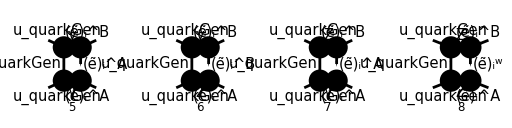

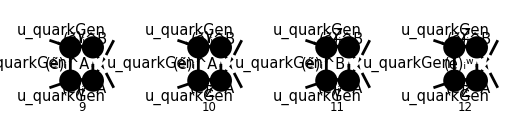

```mathematica
diagsBox[0]=InsertFields[
CreateTopologies[1,2->2,BoxesOnly],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
V[3],
F[11|12],
S[11|13|14]
}
];
Paint[
diagsBox[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

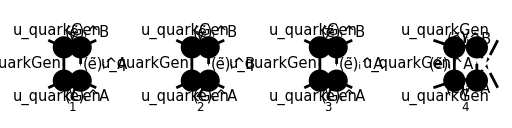

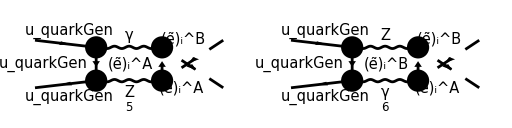

```mathematica
diagsBox[1]=DiagramExtract[diagsBox[0],{5,6,7,9,10,11}];
Paint[
diagsBox[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MboxList[0]=FCFAConvert[
CreateFeynAmp[diagsBox[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
List->True,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->D
]/.{MQU[quarkGen]->0,MSf[B,2,i]->m1,MSf[A,2,i]->m2}//ZSimplify
```

{-((ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ρ e δ_Col1Col2).(γ·k).(-2/3 ⅈ γ^μ e).(φ(p_1)) IndexDelta(A,B) g^μν (-k-k_1+k_2-p_2)^ν g^ρσ (k-2 k_2+p_2)^σ e^2)/(16 π^4 k^2.(k+p_2)^2.((k-k_2+p_2)^2-m_2^2).(k-k_1-k_2+p_2)^2)),-((ⅈ Z_l_i^AB (φ(-p_2)).(2 ⅈ (Z_q_R γ^ρ.(γ̄)^6+Z_q_L γ^ρ.(γ̄)^7) e δ_Col1Col2)/((cos(θ_W)) (sin(θ_W))).(γ·k).(-2/3 ⅈ γ^μ e).(φ(p_1)) g^μν (-k-k_1+k_2-p_2)^ν g^ρσ (k-2 k_2+p_2)^σ e^2)/(16 π^4 k^2.((k+p_2)^2-m_Z^2).((k-k_2+p_2)^2-m_1^2).(k-k_1-k_2+p_2)^2 (cos(θ_W)) (sin(θ_W)))),-((ⅈ Z_l_i^AB (φ(-p_2)).(-2/3 ⅈ γ^ρ e δ_Col1Col2).(γ·k).(2 ⅈ (Z_q_R γ^μ.(γ̄)^6+Z_q_L γ^μ.(γ̄)^7) e)/((cos(θ_W)) (sin(θ_W))).(φ(p_1)) g^μν (-k-k_1+k_2-p_2)^ν g^ρσ (k-2 k_2+p_2)^σ e^2)/(16 π^4 k^2.(k+p_2)^2.((k-k_2+p_2)^2-m_2^2).((k-k_1-k_2+p_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),-((ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ρ e δ_Col1Col2).(γ·k).(-2/3 ⅈ γ^μ e).(φ(p_1)) IndexDelta(A,B) g^μν (-k+k_1-k_2-p_2)^ν g^ρσ (k-2 k_1+p_2)^σ e^2)/(16 π^4 k^2.(k+p_2)^2.((k-k_1+p_2)^2-m_2^2).(k-k_1-k_2+p_2)^2)),-((ⅈ Z_l_i^AB (φ(-p_2)).(2 ⅈ (Z_q_R γ^ρ.(γ̄)^6+Z_q_L γ^ρ.(γ̄)^7) e δ_Col1Col2)/((cos(θ_W)) (sin(θ_W))).(γ·k).(-2/3 ⅈ γ^μ e).(φ(p_1)) g^μν (-k+k_1-k_2-p_2)^ν g^ρσ (k-2 k_1+p_2)^σ e^2)/(16 π^4 k^2.((k+p_2)^2-m_Z^2).((k-k_1+p_2)^2-m_2^2).(k-k_1-k_2+p_2)^2 (cos(θ_W)) (sin(θ_W)))),-((ⅈ Z_l_i^AB (φ(-p_2)).(-2/3 ⅈ γ^ρ e δ_Col1Col2).(γ·k).(2 ⅈ (Z_q_R γ^μ.(γ̄)^6+Z_q_L γ^μ.(γ̄)^7) e)/((cos(θ_W)) (sin(θ_W))).(φ(p_1)) g^μν (-k+k_1-k_2-p_2)^ν g^ρσ (k-2 k_1+p_2)^σ e^2)/(16 π^4 k^2.(k+p_2)^2.((k-k_1+p_2)^2-m_1^2).((k-k_1-k_2+p_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))))}

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,m1,m2];
```

```mathematica
Mγ[0]=(MboxList[0][[{1,4}]]//Total)(3/2SMP["e_Q"])^2;
Mγ[1]=Mγ[0]//Contract//FullSimplify
Mγ[2]=Mγ[1]//FeynAmpDenominatorSplit//FCE//ReplaceAll[#,{FAD[{k-k1+p2,m2}]->FAD[{k-k1+p2,m1}]}]&//FeynAmpDenominatorCombine
```

1/(16 π^4)ⅈ e^4 e_Q^2 δ_Col1Col2 IndexDelta(A,B) (((φ(-p_2)).(γ·(k-2 k_1+p_2)).(γ·k).(γ·(-k+k_1-k_2-p_2)).(φ(p_1)))/(k^2.(k+p_2)^2.((k-k_1+p_2)^2-m_2^2).(k-k_1-k_2+p_2)^2)+((φ(-p_2)).(γ·(k-2 k_2+p_2)).(γ·k).(γ·(-k-k_1+k_2-p_2)).(φ(p_1)))/(k^2.(k+p_2)^2.((k-k_2+p_2)^2-m_2^2).(k-k_1-k_2+p_2)^2))

(ⅈ e^4 e_Q^2 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k-2 k_1+p_2)).(γ·k).(γ·(-k+k_1-k_2-p_2)).(φ(p_1)))/(16 π^4 k^2.(k+p_2)^2.((k-k_1+p_2)^2-m_1^2).(k-k_1-k_2+p_2)^2)+(ⅈ e^4 e_Q^2 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·(k-2 k_2+p_2)).(γ·k).(γ·(-k-k_1+k_2-p_2)).(φ(p_1)))/(16 π^4 k^2.(k+p_2)^2.((k-k_2+p_2)^2-m_2^2).(k-k_1-k_2+p_2)^2)

```mathematica
Mγ[3]=Mγ[2]//TID[#,k,ToPaVe->True]&//DiracGammaExpand//FCE//ReplaceAll[#,{GSD[k2]->GSD[p1+p2-k1]}]&//DiracSimplify//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//FullSimplify
```

-(((-2 m_2^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^6-16 m_2^4 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^6+8 m_2^2 u D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^6-8 m_2^2 u C_0(0,m_1^2,u,0,0,m_1^2) m_1^4-2 m_2^4 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+3 m_2^2 t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+3 m_2^2 u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+2 t u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+2 m_2^4 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4-m_2^2 t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4-m_2^2 u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4+8 m_2^2 t C_0(m_1^2,t,0,0,m_2^2,0) m_1^4-2 u^3 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^4+4 m_2^2 t^2 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^4-12 m_2^2 u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^4-4 t u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^4+24 m_2^4 u D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^4-2 t^2 u D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^4+16 m_2^2 t u D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^4+2 m_2^4 B_0(m_2^2,0,m_1^2) m_1^2-m_2^2 t B_0(m_2^2,0,m_1^2) m_1^2-m_2^2 u B_0(m_2^2,0,m_1^2) m_1^2-2 m_2^4 B_0(m_2^2,0,m_2^2) m_1^2+m_2^2 t B_0(m_2^2,0,m_2^2) m_1^2+m_2^2 u B_0(m_2^2,0,m_2^2) m_1^2+2 u^3 C_0(0,m_1^2,u,0,0,m_1^2) m_1^2+8 m_2^2 u^2 C_0(0,m_1^2,u,0,0,m_1^2) m_1^2+4 t u^2 C_0(0,m_1^2,u,0,0,m_1^2) m_1^2+2 t^2 u C_0(0,m_1^2,u,0,0,m_1^2) m_1^2-8 m_2^2 t^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+8 m_2^4 t C_0(0,m_2^2,t,0,0,m_2^2) m_1^2-8 m_2^2 s t C_0(0,s,0,0,0,0) m_1^2+8 m_2^2 s u C_0(0,s,0,0,0,0) m_1^2-m_2^2 t^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-9 m_2^2 u^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-3 t u^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+m_2^4 t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+m_2^4 u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-3 t^2 u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+8 m_2^2 t u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+2 m_2^6 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+9 m_2^2 t^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+m_2^2 u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+t u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-3 m_2^4 t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-3 m_2^4 u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+t^2 u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-8 m_2^2 t u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-2 t^3 C_0(m_1^2,t,0,0,m_2^2,0) m_1^2-8 m_2^2 t^2 C_0(m_1^2,t,0,0,m_2^2,0) m_1^2-2 t u^2 C_0(m_1^2,t,0,0,m_2^2,0) m_1^2-4 t^2 u C_0(m_1^2,t,0,0,m_2^2,0) m_1^2+8 m_2^2 u^2 C_0(m_2^2,u,0,0,m_1^2,0) m_1^2-8 m_2^4 u C_0(m_2^2,u,0,0,m_1^2,0) m_1^2+4 u^4 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^2+2 m_2^2 u^3 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^2+6 t u^3 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^2-8 m_2^4 u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^2-20 m_2^2 t u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^2-2 t^3 u D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^2-6 m_2^2 t^2 u D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0) m_1^2+(2 m_1^2-t-u) (m_1^2 m_2^2-t u) B_0(m_1^2,0,m_1^2)-(2 m_1^2-t-u) (m_1^2 m_2^2-t u) B_0(m_1^2,0,m_2^2)+t u^2 B_0(m_2^2,0,m_1^2)+t^2 u B_0(m_2^2,0,m_1^2)-2 m_2^2 t u B_0(m_2^2,0,m_1^2)-t u^2 B_0(m_2^2,0,m_2^2)-t^2 u B_0(m_2^2,0,m_2^2)+2 m_2^2 t u B_0(m_2^2,0,m_2^2)-2 u^4 C_0(0,m_1^2,u,0,0,m_1^2)-4 t u^3 C_0(0,m_1^2,u,0,0,m_1^2)-2 t^2 u^2 C_0(0,m_1^2,u,0,0,m_1^2)+2 t^4 C_0(0,m_2^2,t,0,0,m_2^2)-2 m_2^2 t^3 C_0(0,m_2^2,t,0,0,m_2^2)+2 t^2 u^2 C_0(0,m_2^2,t,0,0,m_2^2)-2 m_2^2 t u^2 C_0(0,m_2^2,t,0,0,m_2^2)+4 t^3 u C_0(0,m_2^2,t,0,0,m_2^2)-4 m_2^2 t^2 u C_0(0,m_2^2,t,0,0,m_2^2)+2 s t^3 C_0(0,s,0,0,0,0)-2 s u^3 C_0(0,s,0,0,0,0)-2 s t u^2 C_0(0,s,0,0,0,0)+2 s t^2 u C_0(0,s,0,0,0,0)+2 u^4 C_0(m_1^2,m_2^2,s,0,m_1^2,0)+3 t u^3 C_0(m_1^2,m_2^2,s,0,m_1^2,0)-m_2^2 t u^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0)-t^3 u C_0(m_1^2,m_2^2,s,0,m_1^2,0)-m_2^2 t^2 u C_0(m_1^2,m_2^2,s,0,m_1^2,0)-2 t^4 C_0(m_1^2,m_2^2,s,0,m_2^2,0)+t u^3 C_0(m_1^2,m_2^2,s,0,m_2^2,0)+3 m_2^2 t u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0)-3 t^3 u C_0(m_1^2,m_2^2,s,0,m_2^2,0)+3 m_2^2 t^2 u C_0(m_1^2,m_2^2,s,0,m_2^2,0)-2 m_2^4 t u C_0(m_1^2,m_2^2,s,0,m_2^2,0)+2 t^4 C_0(m_1^2,t,0,0,m_2^2,0)+2 t^2 u^2 C_0(m_1^2,t,0,0,m_2^2,0)+4 t^3 u C_0(m_1^2,t,0,0,m_2^2,0)-2 u^4 C_0(m_2^2,u,0,0,m_1^2,0)+2 m_2^2 u^3 C_0(m_2^2,u,0,0,m_1^2,0)-4 t u^3 C_0(m_2^2,u,0,0,m_1^2,0)-2 t^2 u^2 C_0(m_2^2,u,0,0,m_1^2,0)+4 m_2^2 t u^2 C_0(m_2^2,u,0,0,m_1^2,0)+2 m_2^2 t^2 u C_0(m_2^2,u,0,0,m_1^2,0)-2 u^5 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0)+2 m_2^2 u^4 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0)-2 t u^4 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0)+2 t^2 u^3 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0)+4 m_2^2 t u^3 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0)+2 t^3 u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0)+2 m_2^2 t^2 u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,0)+2 (t-m_2^2) ((2 m_2^2-t) m_1^2+t (-m_2^2+t-u)) (-2 m_1 m_2+t+u) (2 m_1 m_2+t+u) D_0(0,m_2^2,m_1^2,0,t,s,0,0,m_2^2,0)) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(16 π^2 (-2 m_1 m_2+t+u) (2 m_1 m_2+t+u) (m_1^2 m_2^2-t u)))

```mathematica
Mγ[3]=Mγ[2]//TID[#,k,ToPaVe->True]&//DiracGammaExpand//FCE//ReplaceAll[#,{GSD[k2]->GSD[p1+p2-k1]}]&//DiracSimplify//FullSimplify
```

((-2 C_0(0,m_1^2,u,0,0,m_1^2) m_1^10-2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^10-2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^10+4 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^10+2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^10-8 m_2^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^10+2 s D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^10+4 t D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^10+2 m_2^2 C_0(0,m_1^2,u,0,0,m_1^2) m_1^8+6 s C_0(0,m_1^2,u,0,0,m_1^2) m_1^8+2 t C_0(0,m_1^2,u,0,0,m_1^2) m_1^8+4 u C_0(0,m_1^2,u,0,0,m_1^2) m_1^8-2 m_2^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^8+s C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^8-t C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^8+u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^8-4 m_2^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^8+8 s C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^8+6 t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^8+2 u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^8+4 m_2^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^8+9 s C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^8+t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^8+3 u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^8-2 m_2^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^8-16 s C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^8-4 t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^8-8 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^8+2 m_2^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^8-8 s C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^8-4 t C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^8-2 u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^8+8 m_2^4 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^8-6 s^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^8-4 t^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^8+18 m_2^2 s D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^8+4 m_2^2 t D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^8-14 s t D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^8+20 m_2^2 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^8-4 s u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^8-8 t u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^8+2 m_2^2 B_0(m_2^2,0,m_1^2) m_1^6-t B_0(m_2^2,0,m_1^2) m_1^6-2 m_2^2 B_0(m_2^2,0,m_2^2) m_1^6+t B_0(m_2^2,0,m_2^2) m_1^6+2 m_2^4 C_0(0,m_1^2,u,0,0,m_1^2) m_1^6-6 s^2 C_0(0,m_1^2,u,0,0,m_1^2) m_1^6-2 u^2 C_0(0,m_1^2,u,0,0,m_1^2) m_1^6+4 m_2^2 s C_0(0,m_1^2,u,0,0,m_1^2) m_1^6-4 m_2^2 t C_0(0,m_1^2,u,0,0,m_1^2) m_1^6-4 s t C_0(0,m_1^2,u,0,0,m_1^2) m_1^6-6 m_2^2 u C_0(0,m_1^2,u,0,0,m_1^2) m_1^6-12 s u C_0(0,m_1^2,u,0,0,m_1^2) m_1^6-2 t u C_0(0,m_1^2,u,0,0,m_1^2) m_1^6+2 m_2^4 C_0(0,m_2^2,t,0,0,m_2^2) m_1^6-t^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^6+7 m_2^2 s C_0(0,m_2^2,t,0,0,m_2^2) m_1^6+3 m_2^2 t C_0(0,m_2^2,t,0,0,m_2^2) m_1^6-s t C_0(0,m_2^2,t,0,0,m_2^2) m_1^6+3 m_2^2 u C_0(0,m_2^2,t,0,0,m_2^2) m_1^6+t u C_0(0,m_2^2,t,0,0,m_2^2) m_1^6-3 s^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^6+2 t^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^6-2 u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^6-2 m_2^2 s C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^6+s t C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^6-3 s u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^6+8 m_2^4 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^6-12 s^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^6-4 t^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^6+22 m_2^2 s C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^6-2 m_2^2 t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^6-19 s t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^6+6 m_2^2 u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^6-8 s u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^6-4 t u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^6-16 s^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^6+t^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^6-u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^6-2 m_2^2 s C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^6-4 m_2^2 t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^6-4 s t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^6-8 m_2^2 u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^6-11 s u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^6-6 m_2^4 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^6+25 s^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^6+5 u^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^6-11 m_2^2 s C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^6+5 m_2^2 t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^6+13 s t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^6+9 m_2^2 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^6+26 s u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^6+3 t u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^6-6 m_2^4 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^6+12 s^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^6+2 t^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^6-14 m_2^2 s C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^6+2 m_2^2 t C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^6+12 s t C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^6-4 m_2^2 u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^6+8 s u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^6+2 t u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^6+8 m_2^6 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6+6 s^3 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6-20 m_2^2 s^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6+8 m_2^2 t^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6+8 s t^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6-16 m_2^2 u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6+2 s u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6+4 t u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6+22 m_2^4 s D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6-20 m_2^4 t D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6+16 s^2 t D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6-20 m_2^2 s t D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6-28 m_2^4 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6+12 s^2 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6+4 t^2 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6-42 m_2^2 s u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6+26 s t u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^6+t^2 B_0(m_2^2,0,m_1^2) m_1^4-3 m_2^2 s B_0(m_2^2,0,m_1^2) m_1^4-2 m_2^2 t B_0(m_2^2,0,m_1^2) m_1^4+2 s t B_0(m_2^2,0,m_1^2) m_1^4-3 m_2^2 u B_0(m_2^2,0,m_1^2) m_1^4+t u B_0(m_2^2,0,m_1^2) m_1^4-t^2 B_0(m_2^2,0,m_2^2) m_1^4+3 m_2^2 s B_0(m_2^2,0,m_2^2) m_1^4+2 m_2^2 t B_0(m_2^2,0,m_2^2) m_1^4-2 s t B_0(m_2^2,0,m_2^2) m_1^4+3 m_2^2 u B_0(m_2^2,0,m_2^2) m_1^4-t u B_0(m_2^2,0,m_2^2) m_1^4-2 m_2^6 C_0(0,m_1^2,u,0,0,m_1^2) m_1^4+2 s^3 C_0(0,m_1^2,u,0,0,m_1^2) m_1^4-6 m_2^2 s^2 C_0(0,m_1^2,u,0,0,m_1^2) m_1^4+4 m_2^2 u^2 C_0(0,m_1^2,u,0,0,m_1^2) m_1^4+6 s u^2 C_0(0,m_1^2,u,0,0,m_1^2) m_1^4+6 m_2^4 s C_0(0,m_1^2,u,0,0,m_1^2) m_1^4+2 m_2^4 t C_0(0,m_1^2,u,0,0,m_1^2) m_1^4+2 s^2 t C_0(0,m_1^2,u,0,0,m_1^2) m_1^4-4 m_2^2 s t C_0(0,m_1^2,u,0,0,m_1^2) m_1^4+12 s^2 u C_0(0,m_1^2,u,0,0,m_1^2) m_1^4-4 m_2^2 s u C_0(0,m_1^2,u,0,0,m_1^2) m_1^4+4 m_2^2 t u C_0(0,m_1^2,u,0,0,m_1^2) m_1^4+4 s t u C_0(0,m_1^2,u,0,0,m_1^2) m_1^4+2 m_2^6 C_0(0,m_2^2,t,0,0,m_2^2) m_1^4+t^3 C_0(0,m_2^2,t,0,0,m_2^2) m_1^4-9 m_2^2 s^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^4+2 s t^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^4-m_2^2 u^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^4-t u^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^4+3 m_2^4 s C_0(0,m_2^2,t,0,0,m_2^2) m_1^4-5 m_2^4 t C_0(0,m_2^2,t,0,0,m_2^2) m_1^4+3 s^2 t C_0(0,m_2^2,t,0,0,m_2^2) m_1^4-5 m_2^2 s t C_0(0,m_2^2,t,0,0,m_2^2) m_1^4-5 m_2^4 u C_0(0,m_2^2,t,0,0,m_2^2) m_1^4-8 m_2^2 s u C_0(0,m_2^2,t,0,0,m_2^2) m_1^4-3 m_2^2 t u C_0(0,m_2^2,t,0,0,m_2^2) m_1^4-2 s t u C_0(0,m_2^2,t,0,0,m_2^2) m_1^4+3 s^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4-t^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4+u^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4+m_2^2 s^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4-2 m_2^2 t^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4-4 s t^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4+2 m_2^2 u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4+4 s u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4+t u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4+2 m_2^4 t C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4+9 m_2^2 s t C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4-2 m_2^4 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4+4 s^2 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4-t^2 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4-3 m_2^2 s u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^4+4 m_2^6 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+8 s^3 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4-27 m_2^2 s^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+8 m_2^2 t^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+9 s t^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4-4 m_2^2 u^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+16 m_2^4 s C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4-14 m_2^4 t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+18 s^2 t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4-22 m_2^2 s t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4-14 m_2^4 u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+12 s^2 u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4-25 m_2^2 s u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+4 m_2^2 t u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4+13 s t u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^4-4 m_2^6 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4+14 s^3 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4-11 m_2^2 s^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4-3 m_2^2 t^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4+3 m_2^2 u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4+3 s u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4-2 m_2^4 s C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4+6 m_2^4 t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4+5 s^2 t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4+m_2^2 s t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4+6 m_2^4 u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4+15 s^2 u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4+4 m_2^2 s u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4-s t u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^4+2 m_2^6 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4-19 s^3 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4-u^3 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4+28 m_2^2 s^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4+m_2^2 t^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4-s t^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4-8 m_2^2 u^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4-13 s u^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4-11 m_2^4 s C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4+m_2^4 t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4-14 s^2 t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4+5 m_2^2 s t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4+5 m_2^4 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4-31 s^2 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4+t^2 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4+14 m_2^2 s u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4-5 m_2^2 t u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4-6 s t u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^4-2 m_2^6 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4-8 s^3 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4+22 m_2^2 s^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4-4 m_2^2 t^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4-4 s t^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4+4 m_2^2 u^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4-12 m_2^4 s C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4+8 m_2^4 t C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4-12 s^2 t C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4+12 m_2^2 s t C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4+10 m_2^4 u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4-12 s^2 u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4+16 m_2^2 s u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4-6 s t u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^4-8 m_2^8 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-2 s^4 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4+10 m_2^2 s^3 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4+4 m_2^2 u^3 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-22 m_2^4 s^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-4 m_2^4 t^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-4 s^2 t^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4+8 m_2^2 s t^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4+28 m_2^4 u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-6 s^2 u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4+32 m_2^2 s u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-4 m_2^2 t u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-12 s t u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4+22 m_2^6 s D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4+12 m_2^6 t D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-6 s^3 t D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4+24 m_2^2 s^2 t D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-30 m_2^4 s t D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-4 m_2^6 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-12 s^3 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4+40 m_2^2 s^2 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-8 m_2^2 t^2 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-8 s t^2 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-48 m_2^4 s u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4+24 m_2^4 t u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-28 s^2 t u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4+28 m_2^2 s t u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^4-2 m_2^6 B_0(m_2^2,0,m_1^2) m_1^2+m_2^2 s^2 B_0(m_2^2,0,m_1^2) m_1^2-m_2^2 t^2 B_0(m_2^2,0,m_1^2) m_1^2-s t^2 B_0(m_2^2,0,m_1^2) m_1^2+m_2^2 u^2 B_0(m_2^2,0,m_1^2) m_1^2-m_2^4 s B_0(m_2^2,0,m_1^2) m_1^2+3 m_2^4 t B_0(m_2^2,0,m_1^2) m_1^2-s^2 t B_0(m_2^2,0,m_1^2) m_1^2+2 m_2^2 s t B_0(m_2^2,0,m_1^2) m_1^2+2 m_2^4 u B_0(m_2^2,0,m_1^2) m_1^2+4 m_2^2 s u B_0(m_2^2,0,m_1^2) m_1^2-2 s t u B_0(m_2^2,0,m_1^2) m_1^2+2 m_2^6 B_0(m_2^2,0,m_2^2) m_1^2-m_2^2 s^2 B_0(m_2^2,0,m_2^2) m_1^2+m_2^2 t^2 B_0(m_2^2,0,m_2^2) m_1^2+s t^2 B_0(m_2^2,0,m_2^2) m_1^2-m_2^2 u^2 B_0(m_2^2,0,m_2^2) m_1^2+m_2^4 s B_0(m_2^2,0,m_2^2) m_1^2-3 m_2^4 t B_0(m_2^2,0,m_2^2) m_1^2+s^2 t B_0(m_2^2,0,m_2^2) m_1^2-2 m_2^2 s t B_0(m_2^2,0,m_2^2) m_1^2-2 m_2^4 u B_0(m_2^2,0,m_2^2) m_1^2-4 m_2^2 s u B_0(m_2^2,0,m_2^2) m_1^2+2 s t u B_0(m_2^2,0,m_2^2) m_1^2-2 m_2^4 u^2 C_0(0,m_1^2,u,0,0,m_1^2) m_1^2-6 s^2 u^2 C_0(0,m_1^2,u,0,0,m_1^2) m_1^2+2 m_2^6 u C_0(0,m_1^2,u,0,0,m_1^2) m_1^2-4 s^3 u C_0(0,m_1^2,u,0,0,m_1^2) m_1^2+10 m_2^2 s^2 u C_0(0,m_1^2,u,0,0,m_1^2) m_1^2-8 m_2^4 s u C_0(0,m_1^2,u,0,0,m_1^2) m_1^2-2 m_2^4 t u C_0(0,m_1^2,u,0,0,m_1^2) m_1^2-2 s^2 t u C_0(0,m_1^2,u,0,0,m_1^2) m_1^2+4 m_2^2 s t u C_0(0,m_1^2,u,0,0,m_1^2) m_1^2-2 m_2^8 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+5 m_2^2 s^3 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2-2 m_2^2 t^3 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2-2 s t^3 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2-8 m_2^4 s^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+3 m_2^4 t^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2-s^2 t^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+6 m_2^2 s t^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+2 m_2^4 u^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+2 m_2^2 s u^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+2 m_2^2 t u^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+2 s t u^2 C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+5 m_2^6 s C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+m_2^6 t C_0(0,m_2^2,t,0,0,m_2^2) m_1^2-3 s^3 t C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+5 m_2^2 s^2 t C_0(0,m_2^2,t,0,0,m_2^2) m_1^2-7 m_2^4 s t C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+m_2^6 u C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+7 m_2^2 s^2 u C_0(0,m_2^2,t,0,0,m_2^2) m_1^2-4 m_2^4 s u C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+3 m_2^4 t u C_0(0,m_2^2,t,0,0,m_2^2) m_1^2+s^2 t u C_0(0,m_2^2,t,0,0,m_2^2) m_1^2-s^4 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2+2 m_2^2 t^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2+2 s t^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2-2 m_2^2 u^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2-2 s u^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2-m_2^4 s^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2-2 m_2^4 t^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2+2 s^2 t^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2-8 m_2^2 s t^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2+2 m_2^4 u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2-2 s^2 u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2+8 m_2^2 s u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2-2 m_2^2 t u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2-2 s t u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2+2 m_2^6 s C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2+s^3 t C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2+3 m_2^4 s t C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2-3 s^3 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2+2 m_2^2 t^2 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2+2 s t^2 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2-9 m_2^4 s u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0) m_1^2-6 m_2^8 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-2 s^4 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+11 m_2^2 s^3 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-21 m_2^4 s^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-4 m_2^4 t^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-3 s^2 t^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+7 m_2^2 s t^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+8 m_2^4 u^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+9 m_2^2 s u^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+18 m_2^6 s C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+10 m_2^6 t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-5 s^3 t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+18 m_2^2 s^2 t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-23 m_2^4 s t C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+2 m_2^6 u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-8 s^3 u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+24 m_2^2 s^2 u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-18 m_2^4 s u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+4 m_2^4 t u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2-12 s^2 t u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+8 m_2^2 s t u C_0(m_1^2,m_2^2,s,0,m_1^2,0) m_1^2+2 m_2^8 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-6 s^4 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+13 m_2^2 s^3 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-5 m_2^4 s^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+3 m_2^4 t^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-2 s^2 t^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-3 m_2^2 s t^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-3 m_2^4 u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-3 s^2 u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-m_2^2 s u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-6 m_2^6 s C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-4 m_2^6 t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-2 s^3 t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+4 m_2^2 s^2 t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+6 m_2^4 s t C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2-9 s^3 u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+10 m_2^2 s^2 u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+5 m_2^4 s u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+2 s^2 t u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+4 m_2^2 s t u C_0(m_1^2,m_2^2,s,0,m_2^2,0) m_1^2+2 m_2^8 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+7 s^4 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2-19 m_2^2 s^3 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+2 m_2^2 u^3 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+2 s u^3 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+19 m_2^4 s^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2-2 m_2^4 t^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+2 s^2 t^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+m_2^4 u^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+11 s^2 u^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2-8 m_2^2 s u^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2-9 m_2^6 s C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2-m_2^6 t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+5 s^3 t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2-15 m_2^2 s^2 t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+11 m_2^4 s t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2-5 m_2^6 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+16 s^3 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2-29 m_2^2 s^2 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2-2 m_2^2 t^2 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2-2 s t^2 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+18 m_2^4 s u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+m_2^4 t u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+3 s^2 t u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2-8 m_2^2 s t u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0) m_1^2+4 m_2^8 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2+2 s^4 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2-10 m_2^2 s^3 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2+18 m_2^4 s^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2+2 m_2^4 t^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2+2 s^2 t^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2-4 m_2^2 s t^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2-8 m_2^4 u^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2-8 m_2^2 s u^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2-14 m_2^6 s C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2-6 m_2^6 t C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2+4 s^3 t C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2-14 m_2^2 s^2 t C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2+16 m_2^4 s t C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2+8 s^3 u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2-20 m_2^2 s^2 u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2+20 m_2^4 s u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2-6 m_2^4 t u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2+6 s^2 t u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2-8 m_2^2 s t u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0) m_1^2-8 m_2^4 u^3 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2-8 m_2^2 s u^3 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2-8 m_2^6 u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2+6 s^3 u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2-24 m_2^2 s^2 u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2+34 m_2^4 s u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2-4 m_2^4 t u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2+12 s^2 t u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2-8 m_2^2 s t u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2+12 m_2^8 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2+4 s^4 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2-18 m_2^2 s^3 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2+36 m_2^4 s^2 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2+4 m_2^4 t^2 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2+4 s^2 t^2 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2-8 m_2^2 s t^2 u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2-34 m_2^6 s u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2-16 m_2^6 t u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2+10 s^3 t u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2-36 m_2^2 s^2 t u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2+42 m_2^4 s t u D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0) m_1^2-(m_1^2-m_2^2+s) ((2 m_2^2-t) m_1^4+(2 m_2^4-(s+3 (t+u)) m_2^2+t (s+t+u)) m_1^2+u (-m_2^4+(s+t+u) m_2^2-s t)) B_0(m_1^2,0,m_1^2)+(m_1^2-m_2^2+s) ((2 m_2^2-t) m_1^4+(2 m_2^4-(s+3 (t+u)) m_2^2+t (s+t+u)) m_1^2+u (-m_2^4+(s+t+u) m_2^2-s t)) B_0(m_1^2,0,m_2^2)-m_2^4 u^2 B_0(m_2^2,0,m_1^2)-m_2^2 s u^2 B_0(m_2^2,0,m_1^2)+m_2^6 u B_0(m_2^2,0,m_1^2)-m_2^2 s^2 u B_0(m_2^2,0,m_1^2)-m_2^4 t u B_0(m_2^2,0,m_1^2)+s^2 t u B_0(m_2^2,0,m_1^2)+m_2^4 u^2 B_0(m_2^2,0,m_2^2)+m_2^2 s u^2 B_0(m_2^2,0,m_2^2)-m_2^6 u B_0(m_2^2,0,m_2^2)+m_2^2 s^2 u B_0(m_2^2,0,m_2^2)+m_2^4 t u B_0(m_2^2,0,m_2^2)-s^2 t u B_0(m_2^2,0,m_2^2)+2 s^3 u^2 C_0(0,m_1^2,u,0,0,m_1^2)-4 m_2^2 s^2 u^2 C_0(0,m_1^2,u,0,0,m_1^2)+2 m_2^4 s u^2 C_0(0,m_1^2,u,0,0,m_1^2)-m_2^2 s^4 C_0(0,m_2^2,t,0,0,m_2^2)+3 m_2^4 s^3 C_0(0,m_2^2,t,0,0,m_2^2)+m_2^4 t^3 C_0(0,m_2^2,t,0,0,m_2^2)+s^2 t^3 C_0(0,m_2^2,t,0,0,m_2^2)-2 m_2^2 s t^3 C_0(0,m_2^2,t,0,0,m_2^2)-3 m_2^6 s^2 C_0(0,m_2^2,t,0,0,m_2^2)-2 m_2^6 t^2 C_0(0,m_2^2,t,0,0,m_2^2)-2 m_2^2 s^2 t^2 C_0(0,m_2^2,t,0,0,m_2^2)+4 m_2^4 s t^2 C_0(0,m_2^2,t,0,0,m_2^2)-m_2^6 u^2 C_0(0,m_2^2,t,0,0,m_2^2)-m_2^2 s^2 u^2 C_0(0,m_2^2,t,0,0,m_2^2)+2 m_2^4 s u^2 C_0(0,m_2^2,t,0,0,m_2^2)-m_2^4 t u^2 C_0(0,m_2^2,t,0,0,m_2^2)-s^2 t u^2 C_0(0,m_2^2,t,0,0,m_2^2)+2 m_2^2 s t u^2 C_0(0,m_2^2,t,0,0,m_2^2)+m_2^8 s C_0(0,m_2^2,t,0,0,m_2^2)+m_2^8 t C_0(0,m_2^2,t,0,0,m_2^2)+s^4 t C_0(0,m_2^2,t,0,0,m_2^2)-3 m_2^2 s^3 t C_0(0,m_2^2,t,0,0,m_2^2)+4 m_2^4 s^2 t C_0(0,m_2^2,t,0,0,m_2^2)-3 m_2^6 s t C_0(0,m_2^2,t,0,0,m_2^2)+m_2^8 u C_0(0,m_2^2,t,0,0,m_2^2)-2 m_2^2 s^3 u C_0(0,m_2^2,t,0,0,m_2^2)+5 m_2^4 s^2 u C_0(0,m_2^2,t,0,0,m_2^2)-4 m_2^6 s u C_0(0,m_2^2,t,0,0,m_2^2)-m_2^6 t u C_0(0,m_2^2,t,0,0,m_2^2)-m_2^2 s^2 t u C_0(0,m_2^2,t,0,0,m_2^2)+2 m_2^4 s t u C_0(0,m_2^2,t,0,0,m_2^2)+m_2^2 s^4 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-3 m_2^4 s^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-m_2^4 t^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-s^2 t^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+2 m_2^2 s t^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+m_2^4 u^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+s^2 u^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-2 m_2^2 s u^3 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+3 m_2^6 s^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+2 m_2^6 t^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+2 m_2^2 s^2 t^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-4 m_2^4 s t^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-2 m_2^6 u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-2 m_2^2 s^2 u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+4 m_2^4 s u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+m_2^4 t u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+s^2 t u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-2 m_2^2 s t u^2 C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-m_2^8 s C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-m_2^8 t C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-s^4 t C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+3 m_2^2 s^3 t C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-4 m_2^4 s^2 t C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+3 m_2^6 s t C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+m_2^8 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+s^4 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-m_2^2 s^3 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-m_2^4 t^2 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-s^2 t^2 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)+2 m_2^2 s t^2 u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-m_2^6 s u C_0(0,s,-m_1^2-m_2^2+s+t+u,0,0,0)-4 m_2^6 u^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0)-3 m_2^2 s^2 u^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0)+7 m_2^4 s u^2 C_0(m_1^2,m_2^2,s,0,m_1^2,0)+4 m_2^8 u C_0(m_1^2,m_2^2,s,0,m_1^2,0)+2 s^4 u C_0(m_1^2,m_2^2,s,0,m_1^2,0)-9 m_2^2 s^3 u C_0(m_1^2,m_2^2,s,0,m_1^2,0)+16 m_2^4 s^2 u C_0(m_1^2,m_2^2,s,0,m_1^2,0)-13 m_2^6 s u C_0(m_1^2,m_2^2,s,0,m_1^2,0)-4 m_2^6 t u C_0(m_1^2,m_2^2,s,0,m_1^2,0)+3 s^3 t u C_0(m_1^2,m_2^2,s,0,m_1^2,0)-10 m_2^2 s^2 t u C_0(m_1^2,m_2^2,s,0,m_1^2,0)+11 m_2^4 s t u C_0(m_1^2,m_2^2,s,0,m_1^2,0)+s^5 C_0(m_1^2,m_2^2,s,0,m_2^2,0)-4 m_2^2 s^4 C_0(m_1^2,m_2^2,s,0,m_2^2,0)+6 m_2^4 s^3 C_0(m_1^2,m_2^2,s,0,m_2^2,0)-4 m_2^6 s^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0)-m_2^6 t^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0)+s^3 t^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0)-3 m_2^2 s^2 t^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0)+3 m_2^4 s t^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0)+m_2^6 u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0)+s^3 u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0)-2 m_2^2 s^2 u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0)-2 m_2^4 s u^2 C_0(m_1^2,m_2^2,s,0,m_2^2,0)+m_2^8 s C_0(m_1^2,m_2^2,s,0,m_2^2,0)+m_2^8 t C_0(m_1^2,m_2^2,s,0,m_2^2,0)-m_2^2 s^3 t C_0(m_1^2,m_2^2,s,0,m_2^2,0)+3 m_2^4 s^2 t C_0(m_1^2,m_2^2,s,0,m_2^2,0)-3 m_2^6 s t C_0(m_1^2,m_2^2,s,0,m_2^2,0)-m_2^8 u C_0(m_1^2,m_2^2,s,0,m_2^2,0)+2 s^4 u C_0(m_1^2,m_2^2,s,0,m_2^2,0)-6 m_2^2 s^3 u C_0(m_1^2,m_2^2,s,0,m_2^2,0)+3 m_2^4 s^2 u C_0(m_1^2,m_2^2,s,0,m_2^2,0)+2 m_2^6 s u C_0(m_1^2,m_2^2,s,0,m_2^2,0)-s^3 t u C_0(m_1^2,m_2^2,s,0,m_2^2,0)+4 m_2^2 s^2 t u C_0(m_1^2,m_2^2,s,0,m_2^2,0)-3 m_2^4 s t u C_0(m_1^2,m_2^2,s,0,m_2^2,0)-s^5 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+4 m_2^2 s^4 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-6 m_2^4 s^3 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-m_2^4 u^3 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-s^2 u^3 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+2 m_2^2 s u^3 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+4 m_2^6 s^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+m_2^6 t^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-s^3 t^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+3 m_2^2 s^2 t^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-3 m_2^4 s t^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+2 m_2^6 u^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-3 s^3 u^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+8 m_2^2 s^2 u^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-7 m_2^4 s u^2 C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-m_2^8 s C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-m_2^8 t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+m_2^2 s^3 t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-3 m_2^4 s^2 t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+3 m_2^6 s t C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-m_2^8 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-3 s^4 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+10 m_2^2 s^3 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-12 m_2^4 s^2 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+m_2^4 t^2 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+s^2 t^2 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-2 m_2^2 s t^2 u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+6 m_2^6 s u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+m_2^6 t u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+m_2^2 s^2 t u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)-2 m_2^4 s t u C_0(m_1^2,t,-m_1^2-m_2^2+s+t+u,0,m_2^2,0)+4 m_2^6 u^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)+4 m_2^2 s^2 u^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)-8 m_2^4 s u^2 C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)-4 m_2^8 u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)-2 s^4 u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)+8 m_2^2 s^3 u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)-14 m_2^4 s^2 u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)+12 m_2^6 s u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)+4 m_2^6 t u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)-2 s^3 t u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)+8 m_2^2 s^2 t u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)-10 m_2^4 s t u C_0(m_2^2,u,-m_1^2-m_2^2+s+t+u,0,m_1^2,0)+4 m_2^6 u^3 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)+4 m_2^2 s^2 u^3 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)-8 m_2^4 s u^3 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)-4 m_2^8 u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)-2 s^4 u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)+8 m_2^2 s^3 u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)-14 m_2^4 s^2 u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)+12 m_2^6 s u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)+4 m_2^6 t u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)-4 s^3 t u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)+12 m_2^2 s^2 t u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)-12 m_2^4 s t u^2 D_0(0,m_1^2,m_2^2,-m_1^2-m_2^2+s+t+u,u,s,0,0,m_1^2,0)-((m_1-m_2)^2-s) ((m_1+m_2)^2-s) ((4 m_2^2-2 t) m_1^6+(4 t (s+u)-2 m_2^2 (4 s+5 u)) m_1^4-(4 m_2^6+2 (2 s-5 t) m_2^4-(5 s^2+5 t s+13 u s-8 t^2+8 u^2) m_2^2+t (s+t+u) (3 s-2 t+2 u)) m_1^2+2 m_2^6 u+s t (s^2+2 u s+(t-u)^2)+m_2^4 (s^2+(t+u) s-4 t u)-m_2^2 (s^3+(t+4 u) s^2+(2 t^2-u t+5 u^2) s-2 (t-u) u (t+u))) D_0(0,m_2^2,m_1^2,-m_1^2-m_2^2+s+t+u,t,s,0,0,m_2^2,0)) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(16 π^2 (m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2) ((2 m_2^2-t) m_1^4+(2 m_2^4-(s+3 (t+u)) m_2^2+t (s+t+u)) m_1^2+u (-m_2^4+(s+t+u) m_2^2-s t)))

```mathematica
MγUV=Mγ[3]//PaXEvaluateUV[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

0

```mathematica
MγIR=Mγ[3]//PaXEvaluateIR[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

(((54+m_2^2 s t u) 4 e^4)/(32 π^2 s (m_2^2-t) (1))-1-1-1/(2 s (1)))/ε_IR^2+(-1/(32 3 (1))+4+1)/ε_IR
 |  |  |  |

```mathematica
MγIR//Collect2[#,{EpsilonIR},Factoring->Simplify,IsolateNames->KK]&
```

(KK(8255))/(16 ε_IR)-(KK(8222))/(16 ε_IR^2)

```mathematica
KK[8222]//FRH//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&
```

0

```mathematica
KK[8255]//FRH//FullSimplify[#,Assumptions->{
m1∈PositiveReals,
m2∈PositiveReals,
s∈PositiveReals,
m1^2-t>0,
m2^2-t>0,
m1^2-u>0,
m2^2-u>0,
ScaleMu∈PositiveReals
}]&
```

$Aborted

```mathematica
Mγ[3]//TrickMandelstam[#,{s,t,u,m1^2+m2^2+FAKEMASS^2}]&//FullSimplify//PaXEvaluateIR
```

1/ε_IR^2(((2 m_2^2 FAKEMASS^6+6 m_2^4 FAKEMASS^4-2 m_1^2 m_2^2 FAKEMASS^4-m_2^2 s FAKEMASS^4+2 m_1^2 t FAKEMASS^4-6 m_2^2 t FAKEMASS^4-s t FAKEMASS^4+4 m_2^6 FAKEMASS^2-4 m_1^2 m_2^4 FAKEMASS^2-4 m_1^2 t^2 FAKEMASS^2+4 m_2^2 t^2 FAKEMASS^2+4 s t^2 FAKEMASS^2-3 m_2^4 s FAKEMASS^2+m_1^2 m_2^2 s FAKEMASS^2-8 m_2^4 t FAKEMASS^2+8 m_1^2 m_2^2 t FAKEMASS^2-m_1^2 s t FAKEMASS^2-m_2^2 s t FAKEMASS^2-4 s t^3-2 s^2 t^2+4 m_1^2 s t^2+8 m_2^2 s t^2+4 m_1^2 m_2^4 s+2 m_2^2 s^2 t-4 m_2^4 s t-8 m_1^2 m_2^2 s t) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e_Q^2 δ_Col1Col2 e^4)/(32 π^2 s (m_2^2-t) (-m_2^2 m_1^4-m_2^4 m_1^2+FAKEMASS^2 m_2^2 m_1^2-FAKEMASS^2 t m_1^2+m_2^2 t m_1^2+m_2^2 u m_1^2+t u m_1^2-t u^2-FAKEMASS^2 m_2^2 u-t^2 u+FAKEMASS^2 t u+m_2^2 t u))+((FAKEMASS^2 m_1^2-s u) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e_Q^2 δ_Col1Col2 e^4)/(16 π^2 (-m_2^2 m_1^4-m_2^4 m_1^2+FAKEMASS^2 m_2^2 m_1^2-FAKEMASS^2 t m_1^2+m_2^2 t m_1^2+m_2^2 u m_1^2+t u m_1^2-t u^2-FAKEMASS^2 m_2^2 u-t^2 u+FAKEMASS^2 t u+m_2^2 t u))-1/(2 (m_2^2-t))(-((t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u))))-(m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^4 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(5 t^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^4 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^4 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t^3 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^4 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 s t^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 t^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^4 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(7 m_1^2 m_2^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^4 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^6 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 m_2^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t^3 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s t^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^4 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u))))-1/(2 s (m_1^2-u))((m_1^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 s u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 m_1^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^2 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(5 m_1^4 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^4 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^6 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^4 m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 m_2^2 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^6 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 m_2^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^6 m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 s u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(9 m_1^2 s u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^4 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(5 m_1^2 s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^4 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(5 m_1^4 m_2^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(2 m_1^4 m_2^4 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(2 m_1^6 m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 m_2^2 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 m_2^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^8 m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s u^5 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 s u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 s u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 s^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^4 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(7 m_1^4 m_2^2 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 s^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 s t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 s t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(2 m_1^4 m_2^4 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 m_2^2 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 m_2^2 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 m_2^2 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^6 m_2^4 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))))+1/ε_IR(-(((2 m_2^2 FAKEMASS^6+6 m_2^4 FAKEMASS^4-2 m_1^2 m_2^2 FAKEMASS^4-m_2^2 s FAKEMASS^4+2 m_1^2 t FAKEMASS^4-6 m_2^2 t FAKEMASS^4-s t FAKEMASS^4+4 m_2^6 FAKEMASS^2-4 m_1^2 m_2^4 FAKEMASS^2-4 m_1^2 t^2 FAKEMASS^2+4 m_2^2 t^2 FAKEMASS^2+4 s t^2 FAKEMASS^2-3 m_2^4 s FAKEMASS^2+m_1^2 m_2^2 s FAKEMASS^2-8 m_2^4 t FAKEMASS^2+8 m_1^2 m_2^2 t FAKEMASS^2-m_1^2 s t FAKEMASS^2-m_2^2 s t FAKEMASS^2-4 s t^3-2 s^2 t^2+4 m_1^2 s t^2+8 m_2^2 s t^2+4 m_1^2 m_2^4 s+2 m_2^2 s^2 t-4 m_2^4 s t-8 m_1^2 m_2^2 s t) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (2 log(-m_2^2/FAKEMASS^2)-2 log(-m_2^2/s)-log(μ^2/m_2^2)-2 log(m_2^2/(m_2^2-t))-log(4 π)+2 log(2 π)+ℽ) e_Q^2 δ_Col1Col2 e^4)/(32 π^2 s (m_2^2-t) (-m_2^2 m_1^4-m_2^4 m_1^2+FAKEMASS^2 m_2^2 m_1^2-FAKEMASS^2 t m_1^2+m_2^2 t m_1^2+m_2^2 u m_1^2+t u m_1^2-t u^2-FAKEMASS^2 m_2^2 u-t^2 u+FAKEMASS^2 t u+m_2^2 t u)))-((FAKEMASS^2 m_1^2-s u) (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) (-log(μ^2/m_1^2)-2 log(m_1^2/(m_1^2-u))-log(4 π)+2 log(π)+2 log(2)+ℽ) e_Q^2 δ_Col1Col2 e^4)/(16 π^2 (-m_2^2 m_1^4-m_2^4 m_1^2+FAKEMASS^2 m_2^2 m_1^2-FAKEMASS^2 t m_1^2+m_2^2 t m_1^2+m_2^2 u m_1^2+t u m_1^2-t u^2-FAKEMASS^2 m_2^2 u-t^2 u+FAKEMASS^2 t u+m_2^2 t u))+1/(2 (m_2^2-t))(-log(μ^2/m_2^2)-2 log(m_2^2/(m_2^2-t))-log(4 π)+2 log(π)+2 log(2)+ℽ) (-((t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u))))-(m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^4 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(5 t^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^4 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^4 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t^3 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^4 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 s t^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 t^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^4 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(7 m_1^2 m_2^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^4 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^6 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 m_2^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t^3 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s t^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^4 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u))))+((log(-μ^2/FAKEMASS^2))/(FAKEMASS^2-s)-(log(-μ^2/s))/(FAKEMASS^2-s)) (-(((φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^10)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u))))+(u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(5 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(5 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 m_2^2 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(11 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 s^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_2^2 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(7 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^2 m_2^2 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_2^2 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 s^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 m_2^2 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s^3 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 m_2^2 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 s^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 m_2^2 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(16 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^2 m_2^4 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 m_2^2 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s^3 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^3 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 s^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^3 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 s^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^4 s^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 s^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^3 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u))))+1/(2 s (m_1^2-u))(2 log(-m_1^2/FAKEMASS^2)-2 log(-m_1^2/s)-log(μ^2/m_1^2)-2 log(m_1^2/(m_1^2-u))-log(4 π)+2 log(2 π)+ℽ) ((m_1^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^8)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^6)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 s u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(3 m_1^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^2 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(5 m_1^4 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^4 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^6 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^4 m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 m_2^2 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^6 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 m_2^2 t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^6 m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^4)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 s u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(9 m_1^2 s u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(3 m_1^4 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(s^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(5 m_1^2 s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_2^2 s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^4 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(5 m_1^4 m_2^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 s^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(2 m_1^4 m_2^4 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(2 m_1^6 m_2^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 m_2^2 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 s t (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 m_2^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^8 m_2^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2 FAKEMASS^2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s u^5 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t u^4 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s t^2 u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 s u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 s u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s t u^3 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 m_2^2 s^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(s^2 t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_2^2 s t^2 u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^4 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(7 m_1^4 m_2^2 s u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 s t u^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 m_2^2 s^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^2 s^2 t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(8 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^4 s t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^2 m_2^2 s t^2 u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(2 m_1^4 m_2^4 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^6 m_2^2 s u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 m_2^2 s t u (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(2 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))-(m_1^4 m_2^2 s t^2 (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(4 π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))+(m_1^6 m_2^4 s (φ(-p_2)).(γ·k_1).(φ(p_1)) IndexDelta(A,B) e^4 e_Q^2 δ_Col1Col2)/(π^2 (FAKEMASS^2+2 m_1 m_2-t-u) (-FAKEMASS^2+2 m_1 m_2+t+u) (FAKEMASS^2 (m_2^2-t) (m_1^2-u)-(m_1^2+m_2^2-t-u) (m_1^2 m_2^2-t u)))))

```mathematica
%//Collect2[#,{EpsilonIR},Factoring->Simplify,IsolateNames->KK]&
```

(KK(19325))/(16 ε_IR)-(KK(19304))/(16 ε_IR^2)

```mathematica
KK[19304]//FRH//ReplaceAll[#,{FAKEMASS->0}]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&
```

0

```mathematica
KK[19325]//FRH//Collect2[#,{Log},Factoring->Simplify,IsolateNames->KK]&
```

KK(19331) log(-μ^2/FAKEMASS^2)+2 KK(19326) log(-m_1^2/FAKEMASS^2)+KK(19339) log(-m_2^2/FAKEMASS^2)-2 KK(19353) log(μ^2/m_1^2)-KK(19346) log(μ^2/m_2^2)+2 KK(19347) log(-m_1^2/s)-KK(19339) log(-m_2^2/s)-2 KK(19346) log(m_2^2/(m_2^2-t))-4 KK(19353) log(m_1^2/(m_1^2-u))-KK(19331) log(-μ^2/s)+KK(19373)+KK(19304) log(π)+KK(19332) log(4096)-KK(19355) log(1024)+KK(19368) log(512)+KK(19356) log(256)+KK(19366) log(64)+KK(19372) log(32)+KK(19360) log(16)+KK(19371) log(8)+KK(19363) log(4)+KK(19335) log(2)

```mathematica
KK[19331]+2KK[19326]//FRH//ReplaceAll[#,FAKEMASS->0]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&
```

-(2 e^4 e_Q^2 δ_Col1Col2 (-m_1^2 t-m_2^2 t+2 m_2^2 m_1^2+t^2-t u) IndexDelta(A,B) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(π^2 s (m_1^2 m_2^2-t u))

```mathematica
Mγ[3]//PaXEvaluateIR[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,{EpsilonIR},Factoring->Simplify,IsolateNames->KK]&
```

(KK(8255))/(16 ε_IR)-(KK(8222))/(16 ε_IR^2)

```mathematica
KK[8222]//FRH//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&
```

0

```mathematica
KK[8255]//FRH//Collect2[#,{Log},Factoring->FullSimplify,IsolateNames->KK]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2+δ}]&
```

KK(19460) log(-μ^2/δ)+2 KK(19375) log(-m_1^2/δ)-KK(19447) log(-m_2^2/δ)+2 KK(19394) log(μ^2/m_1^2)-KK(19379) log(μ^2/m_2^2)-2 KK(19375) log(-m_1^2/s)+KK(19447) log(-m_2^2/s)-2 KK(19379) log(m_2^2/(m_2^2-t))+4 KK(19394) log(m_1^2/(m_1^2-u))+KK(19462) log(-μ^2/s)+KK(19438)+KK(8222) (-log(π))-KK(19396) log(4398046511104)+KK(19425) log(4294967296)+KK(19393) log(1073741824)-KK(19377) log(16777216)+KK(19384) log(1048576)+KK(19450) log(262144)+KK(19429) log(65536)+KK(19402) log(16384)+KK(19457) log(4096)+KK(19437) log(1024)+KK(19453) log(256)+KK(19434) log(64)-KK(19411) log(16)+KK(19442) log(4)

```mathematica
$Assumptions={
m1∈PositiveReals,
m2∈PositiveReals,
s∈PositiveReals,
m1^2-t>0,
m2^2-t>0,
m1^2-u>0,
m2^2-u>0
};
```

```mathematica
%//ComplexExpand
```

ⅈ (-2 KK(19379) tan^-1(cos(arg(m_2^2-t)),-sin(arg(m_2^2-t)))+4 KK(19394) tan^-1(cos(arg(m_1^2-u)),-sin(arg(m_1^2-u)))+2 KK(19375) arg(-1/δ)-KK(19447) arg(-1/δ)+KK(19460) arg(-1/δ)-2 KK(19375) arg(-1/s)+KK(19447) arg(-1/s)+KK(19462) arg(-1/s))-KK(19375) log(δ^2)+1/2 KK(19447) log(δ^2)-1/2 KK(19460) log(δ^2)-KK(19379) log(μ^2)+2 KK(19394) log(μ^2)+KK(19460) log(μ^2)+KK(19462) log(μ^2)+KK(19379) log((m_2^2-t)^2)-2 KK(19394) log((m_1^2-u)^2)+2 KK(19394) log(1/m_1^2)+4 KK(19394) log(m_1^2)-KK(19379) log(1/m_2^2)-2 KK(19379) log(m_2^2)+KK(19375) log(s^2)-1/2 KK(19447) log(s^2)-1/2 KK(19462) log(s^2)+KK(19438)+KK(8222) (-log(π))-KK(19396) log(4398046511104)+KK(19425) log(4294967296)+KK(19393) log(1073741824)-KK(19377) log(16777216)+KK(19384) log(1048576)+KK(19450) log(262144)+KK(19429) log(65536)+KK(19402) log(16384)+KK(19457) log(4096)+KK(19437) log(1024)+KK(19453) log(256)+KK(19434) log(64)-KK(19411) log(16)+KK(19442) log(4)

```mathematica
KK[19460]//FRH
2KK[19375]//FRH
-KK[19447]//FRH
%+%%+%%%//FullSimplify//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&
```

(e^4 e_Q^2 δ_Col1Col2 IndexDelta(A,B) (m_1^2 (2 (t-u) (m_2^2-t-u)+s^2+s (t+u))-m_2^2 (s^2+s (t+u)+2 (t-u) (t+u))-(m_1^4 (s-t+u))+m_2^4 (s+t-u)+(t-u) (s^2+(t+u)^2)) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(π^2 (m_1^2+m_2^2-t-u) (m_1^2 (-m_2^2 (s+3 (t+u))+2 m_2^4+t (s+t+u))+u (m_2^2 (s+t+u)-m_2^4-s t)+m_1^4 (2 m_2^2-t)))

(2 e^4 e_Q^2 δ_Col1Col2 IndexDelta(A,B) (m_1^2 (-3 m_2^2 (s+2 (t+u))+4 m_2^4+(s+2 t) (s+t+u))+u (2 m_2^2 (s+t+u)-2 m_2^4-s (s+2 t))+m_1^4 (4 m_2^2-s-2 t)) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(π^2 s (-m_1^2 (-m_2^2 (s+3 (t+u))+2 m_2^4+t (s+t+u))+u (-m_2^2 (s+t+u)+m_2^4+s t)+m_1^4 (t-2 m_2^2)))

-((e^4 e_Q^2 δ_Col1Col2 IndexDelta(A,B) (-m_1^2 (-m_2^2 (5 s^2+5 s t+13 s u-8 t^2+8 u^2)+2 m_2^4 (2 s-5 t)+4 m_2^6+t (s+t+u) (3 s-2 t+2 u))+m_2^4 (s^2+s (t+u)-4 t u)-m_2^2 (s^3+s^2 (t+4 u)+s (2 t^2-t u+5 u^2)-2 u (t-u) (t+u))+m_1^4 (4 t (s+u)-2 m_2^2 (4 s+5 u))+m_1^6 (4 m_2^2-2 t)+2 m_2^6 u+s t (s^2+2 s u+(t-u)^2)) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(π^2 s (m_2^2-t) (m_1^2 (-m_2^2 (s+3 (t+u))+2 m_2^4+t (s+t+u))+u (m_2^2 (s+t+u)-m_2^4-s t)+m_1^4 (2 m_2^2-t))))

0

```mathematica
(*Test each scalar integral family separately*)testB=B0[m2^2,0,m1^2]//PaXEvaluateIR[#,PaXImplicitPrefactor->(2 Pi)^(4-D)]&

testC1=C0[m1^2,m2^2,s,0,m1^2,0]//PaXEvaluateIR[#,PaXImplicitPrefactor->(2 Pi)^(4-D)]&

testD=D0[0,m1^2,m2^2,0,u,s,0,0,m1^2,0]//PaXEvaluate[#,PaXImplicitPrefactor->(2 Pi)^(4-D)]&
```

0

0

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression -∞+∞-log(m_1^2/(m_1^2-Power[«2»])) encountered.

Indeterminate

```mathematica
//FullSimplify[#,Assumptions->{
m1∈PositiveReals,
m2∈PositiveReals,
s∈PositiveReals,
m1^2-t>0,
m2^2-t>0,
m1^2-u>0,
m2^2-u>0,
ScaleMu∈PositiveReals
}]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&
```

```mathematica
MZ[0]=(MboxList[0][[{2,3,5,6}]]//Total)3/2SMP["e_Q"];
MZ[1]=MZ[0]//Contract//FullSimplify;
MZ[2]=MZ[1]//TID[#,k,ToPaVe->True]&//DiracGammaExpand//FCE//ReplaceAll[#,{GSD[k2]->GSD[p1+p2-k1]}]&//DiracSimplify//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//FullSimplify
MZUV=MZ[2]//PaXEvaluateUV[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
MZIR=MZ[2]//PaXEvaluateIR[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//FullSimplify[#,Assumptions->{
m1∈PositiveReals,
m2∈PositiveReals,
s∈PositiveReals,
m1^2-t>0,
m2^2-t>0,
m1^2-u>0,
m2^2-u>0,
ScaleMu∈PositiveReals
}]&
```

(Z_l_i^AB (Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))) e^4 e_Q (2 m_2^2 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,m_Z^2) m_1^4-u D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,m_Z^2) m_1^4-2 m_2^2 D_0(0,m_2^2,m_1^2,0,t,s,0,m_Z^2,m_1^2,0) m_1^4+t D_0(0,m_2^2,m_1^2,0,t,s,0,m_Z^2,m_1^2,0) m_1^4+u C_0(0,m_1^2,u,0,m_Z^2,m_2^2) m_1^2-t C_0(m_1^2,t,0,0,m_1^2,0) m_1^2-t C_0(m_1^2,t,0,m_Z^2,m_2^2,0) m_1^2+2 u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,m_Z^2) m_1^2-3 m_2^2 u D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,m_Z^2) m_1^2-t u D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,m_Z^2) m_1^2+2 m_2^4 D_0(0,m_1^2,m_2^2,0,u,s,0,m_Z^2,m_2^2,0) m_1^2+u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,m_Z^2,m_2^2,0) m_1^2-3 m_2^2 u D_0(0,m_1^2,m_2^2,0,u,s,0,m_Z^2,m_2^2,0) m_1^2-2 m_2^4 D_0(0,m_2^2,m_1^2,0,t,s,0,0,m_2^2,m_Z^2) m_1^2-t^2 D_0(0,m_2^2,m_1^2,0,t,s,0,0,m_2^2,m_Z^2) m_1^2+3 m_2^2 t D_0(0,m_2^2,m_1^2,0,t,s,0,0,m_2^2,m_Z^2) m_1^2-2 t^2 D_0(0,m_2^2,m_1^2,0,t,s,0,m_Z^2,m_1^2,0) m_1^2+3 m_2^2 t D_0(0,m_2^2,m_1^2,0,t,s,0,m_Z^2,m_1^2,0) m_1^2+t u D_0(0,m_2^2,m_1^2,0,t,s,0,m_Z^2,m_1^2,0) m_1^2+((m_1^2-u) u D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,m_Z^2)+(m_2^2-u) u D_0(0,m_1^2,m_2^2,0,u,s,0,m_Z^2,m_2^2,0)+t (t-m_2^2) D_0(0,m_2^2,m_1^2,0,t,s,0,0,m_2^2,m_Z^2)+t (t-m_1^2) D_0(0,m_2^2,m_1^2,0,t,s,0,m_Z^2,m_1^2,0)) m_Z^2+(m_1^2-u) u C_0(0,m_1^2,u,0,0,m_1^2)-u^2 C_0(0,m_1^2,u,0,m_Z^2,m_2^2)+t (t-m_2^2) (C_0(0,m_2^2,t,0,0,m_2^2)+C_0(0,m_2^2,t,0,m_Z^2,m_1^2))+s t C_0(0,s,0,0,0,m_Z^2)-s u C_0(0,s,0,0,0,m_Z^2)+s t C_0(0,s,0,0,m_Z^2,0)-s u C_0(0,s,0,0,m_Z^2,0)-t^2 C_0(m_1^2,m_2^2,s,0,m_1^2,m_Z^2)+u^2 C_0(m_1^2,m_2^2,s,0,m_1^2,m_Z^2)-t^2 C_0(m_1^2,m_2^2,s,m_Z^2,m_2^2,0)+u^2 C_0(m_1^2,m_2^2,s,m_Z^2,m_2^2,0)+t^2 C_0(m_1^2,t,0,0,m_1^2,0)+t^2 C_0(m_1^2,t,0,m_Z^2,m_2^2,0)-u^2 C_0(m_2^2,u,0,0,m_2^2,0)+m_2^2 u C_0(m_2^2,u,0,0,m_2^2,0)-u^2 C_0(m_2^2,u,0,m_Z^2,m_1^2,0)+m_2^2 u C_0(m_2^2,u,0,m_Z^2,m_1^2,0)-u^3 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,m_Z^2)+m_2^2 u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,m_Z^2)+t u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,0,m_1^2,m_Z^2)-u^3 D_0(0,m_1^2,m_2^2,0,u,s,0,m_Z^2,m_2^2,0)+2 m_2^2 u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,m_Z^2,m_2^2,0)+t u^2 D_0(0,m_1^2,m_2^2,0,u,s,0,m_Z^2,m_2^2,0)-m_2^4 u D_0(0,m_1^2,m_2^2,0,u,s,0,m_Z^2,m_2^2,0)-m_2^2 t u D_0(0,m_1^2,m_2^2,0,u,s,0,m_Z^2,m_2^2,0)+t^3 D_0(0,m_2^2,m_1^2,0,t,s,0,0,m_2^2,m_Z^2)-2 m_2^2 t^2 D_0(0,m_2^2,m_1^2,0,t,s,0,0,m_2^2,m_Z^2)+m_2^4 t D_0(0,m_2^2,m_1^2,0,t,s,0,0,m_2^2,m_Z^2)-t^2 u D_0(0,m_2^2,m_1^2,0,t,s,0,0,m_2^2,m_Z^2)+m_2^2 t u D_0(0,m_2^2,m_1^2,0,t,s,0,0,m_2^2,m_Z^2)+t^3 D_0(0,m_2^2,m_1^2,0,t,s,0,m_Z^2,m_1^2,0)-m_2^2 t^2 D_0(0,m_2^2,m_1^2,0,t,s,0,m_Z^2,m_1^2,0)-t^2 u D_0(0,m_2^2,m_1^2,0,t,s,0,m_Z^2,m_1^2,0)) δ_Col1Col2)/(4 π^2 (m_1^2 m_2^2-t u) (cos(θ_W))^2 (sin(θ_W))^2)

0

(e^4 e_Q δ_Col1Col2 Z_l_i^AB log(((m_1^2-u) (u-m_2^2))/((m_1^2-t) (t-m_2^2))) (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))))/(2 π^2 ε_IR (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2)

```mathematica
MLO=2SMP["e"]^2 ScaleMu^(4-D)(SMP["e_Q"]IndexDelta[A,B]/s SpinorVBarD[p2].GSD[k1].SpinorUD[p1]-ZliAB/(SMP["sin_W"]^2SMP["cos_W"]^2)1/(s-SMP["m_Z"]^2)SpinorVBarD[p2].GSD[k1].(Zql(1-GAD[5])+Zqr(1+GAD[5])).SpinorUD[p1])
```

2 e^2 μ^(4-D) ((e_Q IndexDelta(A,B) v̄(p_2).(γ·k_1).u(p_1))/s-(Z_l_i^AB v̄(p_2).(γ·k_1).((1-(γ̄)^5) Z_q_L+((γ̄)^5+1) Z_q_R).u(p_1))/((cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2))

```mathematica
ComplexConjugate[MLO](MγIR+MZIR)//FermionSpinSum[#,ExtraFactor->1/(4SUNN^2)]&//DiracSimplify//Simplify//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//FullSimplify[#,Assumptions->{
m1∈PositiveReals,
m2∈PositiveReals,
s∈PositiveReals,
m1^2-t>0,
m2^2-t>0,
m1^2-u>0,
m2^2-u>0,
ScaleMu∈PositiveReals
}]&
%//SUNSimplify[#,SUNNToCACF->False]&//FullSimplify//ReplaceAll[#,u->m1^2+m2^2-s-t]&//Collect2[#,t,Factoring->FullSimplify,IsolateNames->KK]&
```

-((e^6 μ^(4-D) e_Q δ_Col1Col2 (m_1^2 m_2^2-t u) (2 e_Q (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2 IndexDelta(A,B) (s Z_l_i^AB (Z_q_L+Z_q_R) (tanh^-1((u-t)/(-2 m_1^2+t+u))+3 tanh^-1((u-t)/(-2 m_2^2+t+u)))+e_Q (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2 log((m_2^2-t)/(m_2^2-u)))+2 s^2 (Z_l_i^AB)^2 (Z_q_L^2+Z_q_R^2) log(((m_1^2-t) (t-m_2^2))/((m_1^2-u) (u-m_2^2)))))/(4 π^2 N^2 s^2 ε_IR (cos(θ_W))^4 (s-m_Z^2)^2 (sin(θ_W))^4))

-1/2 KK(12430) t^2 log((m_2^2-t)/(-m_1^2+s+t))-1/2 KK(12429) t^2 log(((m_1^2-t) (m_2^2-t))/((-m_1^2+s+t) (-m_2^2+s+t)))-3/2 KK(12435) t^2 tanh^-1((m_1^2+m_2^2-s-2 t)/(m_1^2-m_2^2-s))-1/2 KK(12435) t^2 tanh^-1((m_1^2+m_2^2-s-2 t)/(-m_1^2+m_2^2-s))+1/2 KK(12434) t log((m_2^2-t)/(-m_1^2+s+t))+1/2 KK(12438) t log(((m_1^2-t) (m_2^2-t))/((-m_1^2+s+t) (-m_2^2+s+t)))-1/2 KK(12439) log((m_2^2-t)/(-m_1^2+s+t))-1/2 KK(12436) log(((m_1^2-t) (m_2^2-t))/((-m_1^2+s+t) (-m_2^2+s+t)))+3/2 KK(12433) t tanh^-1((m_1^2+m_2^2-s-2 t)/(m_1^2-m_2^2-s))+1/2 KK(12433) t tanh^-1((m_1^2+m_2^2-s-2 t)/(-m_1^2+m_2^2-s))-3/2 KK(12437) tanh^-1((m_1^2+m_2^2-s-2 t)/(m_1^2-m_2^2-s))-1/2 KK(12437) tanh^-1((m_1^2+m_2^2-s-2 t)/(-m_1^2+m_2^2-s))

```mathematica
Log[1+x]-Log[1-x]//FullSimplify
```

2 tanh^-1(x)

## 16.05

```mathematica
diags[0]=InsertFields[
CreateTopologies[0,2->3],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],F[11],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
V[3]
}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

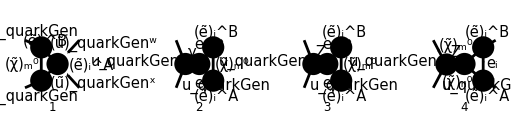

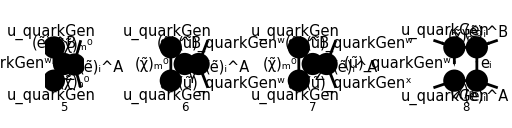

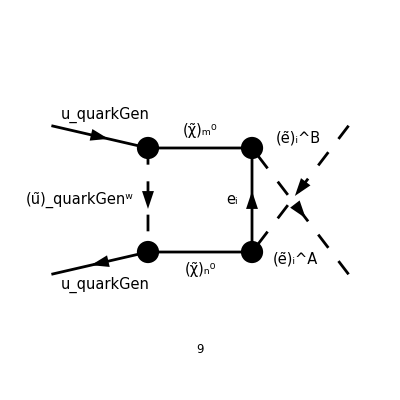

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{SelfEnergies,Tadpoles}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
V[3]
},
LastSelections->{F[11]}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
List->True,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->D
]/.{MQU[quarkGen]->0,MSf[B,2,i]->m1,MSf[A,2,i]->m2}//ZSimplify;
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,m1,m2];
```

```mathematica
Mlist[0][[1]]//TID[#,k,ToPaVe->True]&//DiracSimplify//Simplify//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//DiracGammaExpand//FCE//ReplaceAll[#,GSD[k2]->GSD[p1+p2-k1-k2]]&//DiracSimplify//DiracSubstitute67//FCE//ReplaceAll[#,GAD[5]->0]&//DiracSimplify//Simplify
```

(e^4 δ_Col1Col2 (USf(3,quarkGen)(Sfe6,1) Conjugate[(USf(3,quarkGen)(Sfe5,1))] ((2 (cos(θ_W))^2+2 (sin(θ_W))^2+1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]-2 (sin(θ_W))^2 A,B)+4 (sin(θ_W))^2 USf(3,quarkGen)(Sfe6,2) Conjugate[(USf(3,quarkGen)(Sfe5,2))] (2 A,B-3 USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))])) ((φ(-p_2)).(γ·k_2).(φ(p_1)) (B_0(0,(MNeu(Neu5))^2,(MSf(Sfe5,3,quarkGen))^2)-B_0(s,(MSf(Sfe5,3,quarkGen))^2,(MSf(Sfe6,3,quarkGen))^2)) (3 (cos(θ_W)) Conjugate[ZNeu(Neu5,2)] USf(3,quarkGen)(Sfe5,1) Conjugate[(USf(3,quarkGen)(Sfe6,1))] (3 (cos(θ_W)) ZNeu(Neu5,2)+(sin(θ_W)) ZNeu(Neu5,1))+(sin(θ_W)) Conjugate[ZNeu(Neu5,1)] (USf(3,quarkGen)(Sfe5,1) Conjugate[(USf(3,quarkGen)(Sfe6,1))] (3 (cos(θ_W)) ZNeu(Neu5,2)+(sin(θ_W)) ZNeu(Neu5,1))+16 (sin(θ_W)) ZNeu(Neu5,1) USf(3,quarkGen)(Sfe5,2) Conjugate[(USf(3,quarkGen)(Sfe6,2))]))+C_0(0,s,0,(MNeu(Neu5))^2,(MSf(Sfe6,3,quarkGen))^2,(MSf(Sfe5,3,quarkGen))^2) ((sin(θ_W)) Conjugate[ZNeu(Neu5,1)] (12 s (cos(θ_W)) MNeu(Neu5) (φ(-p_2)).(φ(p_1)) Conjugate[ZNeu(Neu5,2)] USf(3,quarkGen)(Sfe5,1) Conjugate[(USf(3,quarkGen)(Sfe6,2))]-(φ(-p_2)).(γ·k_2).(φ(p_1)) ((MNeu(Neu5))^2-(MSf(Sfe6,3,quarkGen))^2) (USf(3,quarkGen)(Sfe5,1) Conjugate[(USf(3,quarkGen)(Sfe6,1))] (3 (cos(θ_W)) ZNeu(Neu5,2)+(sin(θ_W)) ZNeu(Neu5,1))+16 (sin(θ_W)) ZNeu(Neu5,1) USf(3,quarkGen)(Sfe5,2) Conjugate[(USf(3,quarkGen)(Sfe6,2))]))+Conjugate[(USf(3,quarkGen)(Sfe6,1))] (3 (cos(θ_W)) ZNeu(Neu5,2)+(sin(θ_W)) ZNeu(Neu5,1)) (3 (cos(θ_W)) Conjugate[ZNeu(Neu5,2)] USf(3,quarkGen)(Sfe5,1) (φ(-p_2)).(γ·k_2).(φ(p_1)) ((MSf(Sfe6,3,quarkGen))^2-(MNeu(Neu5))^2)+4 s (sin(θ_W)) MNeu(Neu5) (φ(-p_2)).(φ(p_1)) ZNeu(Neu5,1) USf(3,quarkGen)(Sfe5,2))+4 s (sin(θ_W))^2 MNeu(Neu5) (φ(-p_2)).(φ(p_1)) (Conjugate[ZNeu(Neu5,1)])^2 USf(3,quarkGen)(Sfe5,1) Conjugate[(USf(3,quarkGen)(Sfe6,2))])))/(6912 π^2 s (cos(θ_W))^4 (sin(θ_W))^4)

```mathematica
SpinorUBarD[p1].GSD[k1].SpinorVD[p2] Mlist[0][[1]]//FermionSpinSum[#]&//DiracSimplify//Simplify//FCE//ReplaceAll[#,GAD[5]->0]&//DiracSimplify//Simplify//TID[#,k,ToPaVe->True]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&
```

0

```mathematica
SpinorUBarD[p1].GSD[k1].SpinorVD[p2] Mlist[0][[8]]//ReplaceAll[#,k2->p1+p2-k1]&//DiracSimplify//FermionSpinSum//DiracSimplify//FCE//ReplaceAll[#,GAD[5]->0]&//DiracSimplify//TID[#,k,ToPaVe->True]&
```

9+C_0(0,0,s,(MNeu(Neu5))^2,(MSf(Sfe5,3,quarkGen))^2,(MNeu(Neu6))^2) (1/(576 4 1^4)-1/1)
 |  |  |  |

```mathematica
%%%%+(%%%%//ReplaceAll[#,{k1->k2,k2->k1,m1->m2,m2->m1,t->u,u->t}]&)
```

19+C_0(0,0,s,(MNeu(Neu5))^2,(MSf(Sfe5,3,quarkGen))^2,(MNeu(Neu6))^2) (1/(576 4 1^4)-1/1)
 |  |  |  |

```mathematica
%//Simplify
```

$Aborted

```mathematica
SpinorUBarD[p1].GSD[k1].SpinorVD[p2] Mlist[0][[8]]//FermionSpinSum[#]&//DiracSimplify//Simplify//FCE//ReplaceAll[#,GAD[5]->0]&//DiracSimplify//Simplify//TID[#,k,ToPaVe->True]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&
```

$Aborted

```mathematica
SpinorUBarD[p1].GSD[k1].SpinorVD[p2] Mlist[0][[9]]//FermionSpinSum[#]&//DiracSimplify//Simplify//FCE//ReplaceAll[#,GAD[5]->0]&//DiracSimplify//Simplify//TID[#,k,ToPaVe->True]&//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&
```

```mathematica
SpinorUBarD[p1].GSD[k1].SpinorVD[p2]Mlist[0][[{8,9}]]//Total//FermionSpinSum//DiracSimplify//FCE//ReplaceAll[#,GAD[5]->0]&//DiracSimplify//TID[#,k,ToPaVe->True]&
```

C_0(m_1^2,m_2^2,s,(MNeu(Neu5))^2,(MLE(i))^2,(MNeu(Neu6))^2) (-(δ_Col1Col2 (CB^2 Conjugate[ZNeu(Neu5,1)] 9 m_1^4+797+32 14 1) e^4)/(1152 CB^2 π^2 (cos(θ_W))^4 m_W^2 (sin(θ_W))^4)-((1) 2 e^4)/(2304 5 1^4))+10+1 1
 |  |  |  |

```mathematica
%+(%//ReplaceAll[#,{k1->k2,k2->k1,m1->m2,m2->m1,t->u,u->t}]&)
```

C_0(0,m_1^2,u,(MSf(Sfe5,3,quarkGen))^2,(MNeu(Neu6))^2,(MLE(i))^2) ((e^4 δ_Col1Col2 (428+1))/(1152 CB^2 π^2 (cos(θ_W))^4 m_W^2 (sin(θ_W))^4)-((1) e^4 δ_1 (1))/(4608 CB^2 π^2 (1) 1^4 m_W^2 (sin(θ_W))^4))+22+D_0(1) 1
 |  |  |  |

```mathematica
Mlist[0][[8]]//ReplaceAll[#,k2->p1+p2-k1]&//TID[#,k,ToPaVe->True]&//DiracSimplify//DiracSubstitute67
```

(Conjugate[ZNeu(Neu5,1)] (Conjugate[ZNeu(Neu6,1)])^2 Conjugate[(USf(2,i)(B,1))] 7 USf(2,i)(A,1) USf(3,quarkGen)(Sfe5,1) m_1^6)/(288 π^2 s (m_1^4-s m_1^2-t m_1^2-u m_1^2+t u) (cos(θ_W))^4)-1/(144 3 1^4)+10281+1/1-1/(24 CB π^2 1^2 m_W (sin(θ_W))^2)
 |  |  |  |

```mathematica
%//FCE//Collect2[#,{GAD,GSD,Spinor},IsolateNames->KK]&
```

-(KK(25202) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/1152+1/72 KK(25204) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+1/288 KK(25206) (φ(-p_2)).(γ̄)^6.(φ(p_1))+1/288 KK(25208) (φ(-p_2)).(γ̄)^7.(φ(p_1))

```mathematica
%//DiracSubstitute67
```

-(KK(25202) (φ(-p_2)).(γ·k_1).(1/2-(γ̄)^5/2).(φ(p_1)))/1152+1/72 KK(25204) (φ(-p_2)).(γ·k_1).((γ̄)^5/2+1/2).(φ(p_1))+1/288 KK(25206) (φ(-p_2)).((γ̄)^5/2+1/2).(φ(p_1))+1/288 KK(25208) (φ(-p_2)).(1/2-(γ̄)^5/2).(φ(p_1))

```mathematica
Mlist[0][[{8,9}]]//Total//ReplaceAll[#,k2->p1+p2-k1]&//TID[#,k,ToPaVe->True]&//DiracSimplify//FCE//Collect2[#,{GAD,GSD,Spinor},IsolateNames->KK]&
```

-(KK(31084) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/1152+1/72 KK(31086) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+1/288 KK(31088) (φ(-p_2)).(γ̄)^6.(φ(p_1))+1/288 KK(31090) (φ(-p_2)).(γ̄)^7.(φ(p_1))

## 19.05

```mathematica
myAssumptions={
x∈Reals,
xm∈Reals,
xp∈Reals,
-1<xm<0<xp<1,
xm<=x<=xp,
d∈PositiveReals,
4<d<5,
z∈PositiveReals,
0<z<=1
};
```

```mathematica
(xp-x)^((d-2)/2)(x-xm)^((d-2)/2)/((z+x)^2(z-x)^2)
Integrate[%,{x,xm,xp},Assumptions->myAssumptions]
```

((x-x^-)^((d-2)/2) (x^+-x)^((d-2)/2))/((z-x)^2 (x+z)^2)

ConditionalExpression[1/(√π z^3)3/2-d/2 d/2 (-1/((d-2) (x^--z)^2 (x^+-z)^2)(2 ⅈ)^-d ((x^+-z)^2 (x^--z)^d 2-d1-d/22-d/2(x^+-z)/(x^--z)-(x^--z)^2 (x^+-z)^d 2-d1-d/22-d/2(x^--z)/(x^+-z))-1/((d-2) (x^-+z)^2 (x^++z)^2)(2 ⅈ)^-d ((x^-+z)^2 (x^++z)^d 2-d1-d/22-d/2(x^-+z)/(x^++z)-(x^++z)^2 (x^-+z)^d 2-d1-d/22-d/2(x^++z)/(x^-+z))-(ⅈ^-d 2^(1-d) (3-d) z ((z-x^+)^3 (x^--z)^d 3-d1-d/23-d/2(x^+-z)/(x^--z)+(x^--z)^3 (x^+-z)^d 3-d1-d/23-d/2(x^--z)/(x^+-z)))/((d-4) (d-3) (x^+-z)^3 (z-x^-)^3)+(ⅈ^-d 2^(1-d) (3-d) z ((x^-+z)^3 (x^++z)^d 3-d1-d/23-d/2(x^-+z)/(x^++z)-(x^++z)^3 (x^-+z)^d 3-d1-d/23-d/2(x^++z)/(x^-+z)))/((d-4) (d-3) (x^-+z)^3 (x^++z)^3)), z<1∧x^+>z∧x^->z]

```mathematica
(xp-x)^((d-2)/2)(x-xm)^((d-2)/2)/((1+x)^2(1-x)^2)
Integrate[%,{x,xm,xp},Assumptions->myAssumptions]
```

((x-x^-)^((d-2)/2) (x^+-x)^((d-2)/2))/((1-x)^2 (x+1)^2)

1/(√π)3/2-d/2 d/2 (-1/((d-2) (x^--1)^2 (x^+-1)^2)(2 ⅈ)^-d ((x^+-1)^2 (1-x^-)^d 2-d1-d/22-d/2(x^+-1)/(x^--1)-(x^--1)^2 (1-x^+)^d 2-d1-d/22-d/2(x^--1)/(x^+-1))-1/((d-2) (x^-+1)^2 (x^++1)^2)(2 ⅈ)^-d ((x^-+1)^2 (x^++1)^d 2-d1-d/22-d/2(x^-+1)/(x^++1)-(x^++1)^2 (x^-+1)^d 2-d1-d/22-d/2(x^++1)/(x^-+1))-(ⅈ^-d 2^(1-d) (3-d) ((x^+-1)^3 (1-x^-)^d 3-d1-d/23-d/2(x^+-1)/(x^--1)-(x^--1)^3 (1-x^+)^d 3-d1-d/23-d/2(x^--1)/(x^+-1)))/((d-4) (d-3) (x^--1)^3 (x^+-1)^3)+(ⅈ^-d 2^(1-d) (3-d) ((x^-+1)^3 (x^++1)^d 3-d1-d/23-d/2(x^-+1)/(x^++1)-(x^++1)^3 (x^-+1)^d 3-d1-d/23-d/2(x^++1)/(x^-+1)))/((d-4) (d-3) (x^-+1)^3 (x^++1)^3))

```mathematica
(xp-x)(x-xm)/((1+x)^2(1-x)^2)
Integrate[%,{x,xm,xp},Assumptions->myAssumptions]
```

((x-x^-) (x^+-x))/((1-x)^2 (x+1)^2)

1/4 (2 x^--2 x^++log(((x^--1) (x^++1))/((x^-+1) (x^+-1)))+2 x^+ x^- tanh^-1((x^+-x^-)/(x^- x^+-1)))

```mathematica
(xp-x)(x-xm)/((1+x)^2(1-x)^2)Log[(xp-x)(x-xm)]
Integrate[%,{x,xm,xp},Assumptions->myAssumptions]
```

((x-x^-) (x^+-x) log((x-x^-) (x^+-x)))/((1-x)^2 (x+1)^2)

1/4 ((x^- x^+-1) 2(x^--1)/(x^+-1)+(1-x^- x^+) 2(x^+-1)/(x^--1)-x^- x^+ 2(x^-+1)/(x^++1)+2(x^-+1)/(x^++1)+x^- x^+ 2(x^++1)/(x^-+1)-2(x^++1)/(x^-+1)+log^2(1-x^-)-log^2(x^-+1)-x^- log(1-x^-)-ⅈ π log(1-x^-)+2 log(1-x^-)-x^- log(x^-+1)+ⅈ π log(x^-+1)-2 log(x^-+1)-log^2(1-x^+)+log^2(x^++1)+x^+ log(1-x^+)+ⅈ π log(1-x^+)-2 log(1-x^+)+x^+ log(x^++1)-ⅈ π log(x^++1)+2 log(x^++1)-x^- x^+ log^2(1-x^-)+x^- x^+ log^2(x^-+1)+x^- x^+ log^2(1-x^+)-x^- x^+ log^2(x^++1)+ⅈ π x^- x^+ log(1-x^-)-x^+ log(1-x^-)-ⅈ π x^- x^+ log(x^-+1)-x^+ log(x^-+1)+x^- log(1-x^+)-ⅈ π x^- x^+ log(1-x^+)+x^- log(x^++1)+ⅈ π x^- x^+ log(x^++1)+4 x^- log(x^+-x^-)-4 x^+ log(x^+-x^-))

```mathematica
%//Collect2[#,I,Factoring->FullSimplify,IsolateNames->KK]&
```

(KK(1182))/4

```mathematica
ReleaseHold[1/4 HoldForm[KK[1182]]]
```

1/4 (x^- x^+ 2(KK(1175))/(KK(1173))+KK(1181) 2(KK(1173))/(KK(1175))-2(KK(1175))/(KK(1173))+KK(1178) 2(KK(1179))/(KK(1180))+KK(1181) 2(KK(1180))/(KK(1179))-x^- log(KK(1172))-x^- log(KK(1173))+x^- log(KK(1174))+x^- log(KK(1175))-x^+ log(KK(1172))-x^+ log(KK(1173))+x^+ log(KK(1174))+x^+ log(KK(1175))-x^- x^+ log^2(KK(1172))+x^- x^+ log^2(KK(1173))+x^- x^+ log^2(KK(1174))-x^- x^+ log^2(KK(1175))+log^2(KK(1172))-log^2(KK(1173))-log^2(KK(1174))+log^2(KK(1175))+4 KK(1176) log(KK(1177))+2 ⅈ π tanh^-1(x^-)-4 tanh^-1(x^-)-2 ⅈ π tanh^-1(x^+)+4 tanh^-1(x^+)-2 ⅈ π x^- x^+ tanh^-1(x^-)+2 ⅈ π x^- x^+ tanh^-1(x^+))

## 20.05

```mathematica
$Assumptions={
d∈PositiveReals,
d>4,
m∈PositiveReals,
s∈PositiveReals,
s>2m
};
```

```mathematica
(2-x)/x^(3-d/2)((m^2+(1-x)(2m^2+s))^(d/2-2)-m^(d-4))
Integrate[%,{x,0,1}]
```

(2-x) x^(d/2-3) (((1-x) (2 m^2+s)+m^2)^(d/2-2)-m^(d-4))

(2 (3 m^2+s)^(d/2-2) ((3 m^2+s) 1-d/2(d-4)/2(d-2)/2(2 m^2+s)/(3 m^2+s)+(m^2+s) 2-d/2(d-4)/2(d-2)/2(2 m^2+s)/(3 m^2+s)))/((d-4) (2 m^2+s))-(2 d m^(d-4))/(d^2-6 d+8)

```mathematica
(2-x)/(x^(3-d/2)(m^2+2y m^2+y s)^(3-d/2))
Integrate[%,{x,0,1},{y,0,1-x}]
%//ReplaceAll[#,{d->4-2ϵ}]&//Series[#,{ϵ,0,0}]&//Normal//Collect2[#,{ϵ},Factoring->FullSimplify,IsolateNames->KK]&
%//FRH//Collect2[#,{m,s},Factoring->FullSimplify,IsolateNames->KK]&
```

(2-x) x^(d/2-3) (2 m^2 y+m^2+s y)^(d/2-3)

(4 ((3 m^2+s)^(d/2-2) ((3 m^2+s) 1-d/2(d-4)/2(d-2)/2(2 m^2+s)/(3 m^2+s)+(m^2+s) 2-d/2(d-4)/2(d-2)/2(2 m^2+s)/(3 m^2+s))-(d m^(d-4) (2 m^2+s))/(d-2)))/((d-4)^2 (2 m^2+s)^2)

(KK(249))/ϵ+(KK(255))/2

-(8 log^2(m) m^2)/((2 m^2+s)^2)+(2 log^2(3 m^2+s) m^2)/((2 m^2+s)^2)-(2 KK(261) m^2)/((2 m^2+s)^2)+(4 KK(259) log(m) m^2)/((2 m^2+s)^2)-(4 KK(257) log(3 m^2+s) m^2)/((2 m^2+s)^2)-(3 KK(257) Hypergeometric2F1^(0,0,1,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)+(3 log(3 m^2+s) Hypergeometric2F1^(0,0,1,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)-(KK(257) Hypergeometric2F1^(0,0,1,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)+(log(3 m^2+s) Hypergeometric2F1^(0,0,1,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)+(3 Hypergeometric2F1^(0,0,2,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/(2 (2 m^2+s)^2)+(Hypergeometric2F1^(0,0,2,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/(2 (2 m^2+s)^2)+(3 KK(257) Hypergeometric2F1^(0,1,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)-(3 log(3 m^2+s) Hypergeometric2F1^(0,1,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)+(KK(257) Hypergeometric2F1^(0,1,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)-(log(3 m^2+s) Hypergeometric2F1^(0,1,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)-(3 Hypergeometric2F1^(0,1,1,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)-(Hypergeometric2F1^(0,1,1,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)+(3 Hypergeometric2F1^(0,2,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/(2 (2 m^2+s)^2)+(Hypergeometric2F1^(0,2,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/(2 (2 m^2+s)^2)-(3 KK(257) Hypergeometric2F1^(1,0,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)+(3 log(3 m^2+s) Hypergeometric2F1^(1,0,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)-(KK(257) Hypergeometric2F1^(1,0,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)+(log(3 m^2+s) Hypergeometric2F1^(1,0,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)+(3 Hypergeometric2F1^(1,0,1,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)+(Hypergeometric2F1^(1,0,1,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)-(3 Hypergeometric2F1^(1,1,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)-(Hypergeometric2F1^(1,1,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/((2 m^2+s)^2)+(3 Hypergeometric2F1^(2,0,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)) m^2)/(2 (2 m^2+s)^2)+(Hypergeometric2F1^(2,0,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)) m^2)/(2 (2 m^2+s)^2)-(4 s log^2(m))/((2 m^2+s)^2)+(s log^2(3 m^2+s))/((2 m^2+s)^2)-(s KK(261))/((2 m^2+s)^2)+(2 s KK(259) log(m))/((2 m^2+s)^2)-(2 s KK(257) log(3 m^2+s))/((2 m^2+s)^2)-(s KK(257) Hypergeometric2F1^(0,0,1,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)+(s log(3 m^2+s) Hypergeometric2F1^(0,0,1,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)-(s KK(257) Hypergeometric2F1^(0,0,1,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)+(s log(3 m^2+s) Hypergeometric2F1^(0,0,1,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)+(s Hypergeometric2F1^(0,0,2,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/(2 (2 m^2+s)^2)+(s Hypergeometric2F1^(0,0,2,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/(2 (2 m^2+s)^2)+(s KK(257) Hypergeometric2F1^(0,1,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)-(s log(3 m^2+s) Hypergeometric2F1^(0,1,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)+(s KK(257) Hypergeometric2F1^(0,1,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)-(s log(3 m^2+s) Hypergeometric2F1^(0,1,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)-(s Hypergeometric2F1^(0,1,1,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)-(s Hypergeometric2F1^(0,1,1,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)+(s Hypergeometric2F1^(0,2,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/(2 (2 m^2+s)^2)+(s Hypergeometric2F1^(0,2,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/(2 (2 m^2+s)^2)-(s KK(257) Hypergeometric2F1^(1,0,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)+(s log(3 m^2+s) Hypergeometric2F1^(1,0,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)-(s KK(257) Hypergeometric2F1^(1,0,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)+(s log(3 m^2+s) Hypergeometric2F1^(1,0,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)+(s Hypergeometric2F1^(1,0,1,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)+(s Hypergeometric2F1^(1,0,1,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)-(s Hypergeometric2F1^(1,1,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)-(s Hypergeometric2F1^(1,1,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/((2 m^2+s)^2)+(s Hypergeometric2F1^(2,0,0,0)(0,-1,1,(2 m^2+s)/(3 m^2+s)))/(2 (2 m^2+s)^2)+(s Hypergeometric2F1^(2,0,0,0)(0,0,1,(2 m^2+s)/(3 m^2+s)))/(2 (2 m^2+s)^2)

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,m,m,m1,m2];
```

```mathematica
SpinorVBarD[p2].GSD[k+p1+m].SpinorUD[p1]FAD[k,{k+p1,m},k+p1+p2]
%//TID[#,k,ToPaVe->True]&//DiracSimplify//Simplify
%//PaXEvaluateUVIRSplit[#,PaXC0Expand->True,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

(v̄(p_2).(γ·(k+m+p_1)).u(p_1))/(k^2.((k+p_1)^2-m^2).(k+p_1+p_2)^2)

ⅈ π^2 C_0(m^2,m^2,s,0,m^2,0) (φ(-p_2)).(γ·m).(φ(p_1))

-(ⅈ π^2 √((s-4 m^2)/s) (12 2((√(1-(4 m^2)/s)-1) s)/(2 m^2)+1+3 log^2((s (√(1-(4 m^2)/s)-1))/(2 m^2)+1)+4 π^2) (φ(-p_2)).(γ·m).(φ(p_1)))/(6 (4 m^2-s))

```mathematica
C0[m^2,m^2,s,0,m^2,0]
%//PaXEvaluateUVIRSplit[#,PaXC0Expand->True]&
```

C_0(m^2,m^2,s,0,m^2,0)

(12 2((√(1-(4 m^2)/s)-1) s)/(2 m^2)+1+3 log^2((s (√(1-(4 m^2)/s)-1))/(2 m^2)+1)+4 π^2)/(6 s √((s-4 m^2)/s))

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{SelfEnergies,Tadpoles}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
V[3],
F[11|12],
S[11|13|14]
}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

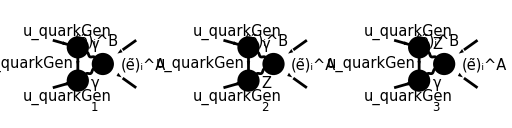

```mathematica
diags[1]=DiagramExtract[diags[0],{1,2,3}];
Paint[
diags[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,m,m,m1,m2];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
List->True,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->D
]/.{MQU[quarkGen]->m,MSf[B,2,i]->m1,MSf[A,2,i]->m2}//ZSimplify;
```

```mathematica
M[0]=(Mlist[0][[1]](3/2SMP["e_Q"])^2)+(Mlist[0][[{2,3}]]3/2SMP["e_Q"]//Total)//ReplaceAll[#,{p2-k1-k2->-p1}]&//Contract//DiracSimplify//Simplify
```

-1/(8 π^4 (cos(θ_W))^2 (sin(θ_W))^2)ⅈ e^4 e_Q δ_Col1Col2 (2 D m Z_l_i^AB (φ(-p_2,m)).(γ̄)^6.(φ(p_1,m)) (Z_q_L/((k^2-m^2).((k+p_2)^2-m_Z^2).(k-p_1)^2)+Z_q_R/((k^2-m^2).(k+p_2)^2.((k-p_1)^2-m_Z^2)))+2 D m Z_l_i^AB (φ(-p_2,m)).(γ̄)^7.(φ(p_1,m)) (Z_q_L/((k^2-m^2).(k+p_2)^2.((k-p_1)^2-m_Z^2))+Z_q_R/((k^2-m^2).((k+p_2)^2-m_Z^2).(k-p_1)^2))-(2 D Z_q_L Z_l_i^AB (φ(-p_2,m)).(γ·k).(γ̄)^7.(φ(p_1,m)))/((k^2-m^2).(k+p_2)^2.((k-p_1)^2-m_Z^2))-(2 D Z_q_L Z_l_i^AB (φ(-p_2,m)).(γ·k).(γ̄)^7.(φ(p_1,m)))/((k^2-m^2).((k+p_2)^2-m_Z^2).(k-p_1)^2)-(2 D Z_q_R Z_l_i^AB (φ(-p_2,m)).(γ·k).(γ̄)^6.(φ(p_1,m)))/((k^2-m^2).(k+p_2)^2.((k-p_1)^2-m_Z^2))-(2 D Z_q_R Z_l_i^AB (φ(-p_2,m)).(γ·k).(γ̄)^6.(φ(p_1,m)))/((k^2-m^2).((k+p_2)^2-m_Z^2).(k-p_1)^2)+(4 Z_q_L Z_l_i^AB (φ(-p_2,m)).(γ·k).(γ̄)^7.(φ(p_1,m)))/((k^2-m^2).(k+p_2)^2.((k-p_1)^2-m_Z^2))+(4 Z_q_L Z_l_i^AB (φ(-p_2,m)).(γ·k).(γ̄)^7.(φ(p_1,m)))/((k^2-m^2).((k+p_2)^2-m_Z^2).(k-p_1)^2)+(4 Z_q_R Z_l_i^AB (φ(-p_2,m)).(γ·k).(γ̄)^6.(φ(p_1,m)))/((k^2-m^2).(k+p_2)^2.((k-p_1)^2-m_Z^2))+(4 Z_q_R Z_l_i^AB (φ(-p_2,m)).(γ·k).(γ̄)^6.(φ(p_1,m)))/((k^2-m^2).((k+p_2)^2-m_Z^2).(k-p_1)^2)+(D e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2,m)).(γ·k).(φ(p_1,m)))/((k^2-m^2).(k+p_2)^2.(k-p_1)^2)+-(D m e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2,m)).(φ(p_1,m)))/((k^2-m^2).(k+p_2)^2.(k-p_1)^2)-(2 e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2,m)).(γ·k).(φ(p_1,m)))/((k^2-m^2).(k+p_2)^2.(k-p_1)^2))

```mathematica
diracLOγ=SpinorVBarD[p2,m].GSD[k1-k2].SpinorUD[p1,m]
diracLOZ=SpinorVBarD[p2,m].GSD[k1-k2].(Zql(1-GAD[5])+Zqr(1+GAD[5])).SpinorUD[p1,m]
```

v̄(p_2,m).(γ·(k_1-k_2)).u(p_1,m)

v̄(p_2,m).(γ·(k_1-k_2)).((1-(γ̄)^5) Z_q_L+((γ̄)^5+1) Z_q_R).u(p_1,m)

```mathematica
DataType[x,FCVariable]=True;
DataType[y,FCVariable]=True;
DataType[z,FCVariable]=True;
DataType[m,FCVariable]=True;
```

```mathematica
SpinorVBarD[p2,m].GSD[k-(1+x+y)p1-(1+y)p2+(2-z)k1].GSD[k+(1-x-y)p1-y p2-z k1+m].GSD[k-(x+y)p1-y p2+(2-z)k1].SpinorUD[p1,m];
%//DiracSimplify//FullSimplify;
SpinorUBarD[p1,m].GSD[2k1-p1-p2].SpinorVD[p2,m]%//FermionSpinSum//DiracSimplify//Collect2[#,{m,m1,m2},Factoring->Simplify,IsolateNames->KK]&
```

-8 KK(4167) m^4 (k·m)+8 KK(4176) m^4 (k_1·m)-16 KK(4167) m_1^2 m^2 (k·m)+8 KK(4172) m^2 (k·m)+16 KK(4176) m_1^2 m^2 (k_1·m)+4 KK(4207) m^2 (k_1·m)-8 KK(4167) m_1^4 (k·m)-8 KK(4200) (k·m)+8 KK(4205) m_1^2 (k·m)+8 KK(4176) m_1^4 (k_1·m)+4 KK(4198) (k_1·m)+4 KK(4214) m_1^2 (k_1·m)-4 KK(4184) m^6-4 KK(4174) m^4 (m·p_1)-4 KK(4206) m^4 (m·p_2)-4 KK(4185) m^4-4 KK(4217) m_1^2 m^4-4 KK(4171) m_1^2 m^2 (m·p_1)+4 KK(4212) m^2 (m·p_1)+4 KK(4175) m^2 (m·p_2)-4 KK(4181) m_1^2 m^2 (m·p_2)+4 KK(4189) m^2-4 KK(4204) m_1^2 m^2-4 KK(4211) m_1^4 m^2+4 KK(4169) m_1^4 (m·p_1)-4 KK(4201) m_1^2 (m·p_1)+4 KK(4208) (m·p_1)+4 KK(4179) m_1^2 (m·p_2)+4 KK(4195) (m·p_2)-4 KK(4203) m_1^4 (m·p_2)-4 KK(4178) m_1^6-4 KK(4186) m_1^4+4 KK(4193) m_1^2-4 KK(4224)

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{SelfEnergies,Tadpoles}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
V[3],
F[11|12],
S[11|13|14]
}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
diags[1]=DiagramExtract[diags[0],{13,14,15,17,18,19}];
Paint[
diags[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

-Graphics-

-Graphics-

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,m,m,m1,m2];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
List->True,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->D
]/.{MQU[quarkGen]->m,MSf[B,2,i]->m1,MSf[A,2,i]->m2}//ZSimplify;
```

```mathematica
Mlist[0]//Total//ReplaceAll[#,p2-k1-k2->-p1]&;
%//TID[#,k,ToPaVe->True]&//TrickMandelstam[#,{s,t,u,2m^2+m1^2+m2^2}]&
```

$Aborted

## Emission sleptonside xtilde integrals

```mathematica
$Assumptions={
-1<xm<xp<1
};
```

```mathematica
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2a b-2a c-2b c
```

```mathematica
xpmRules={
xm->mt2^2-mt1^2-Sqrt[λ],
xp->mt2^2-mt1^2+Sqrt[λ]
};
fromλRules={
λ->1+mt1^4+mt2^4-2(mt1^2+mt2^2)-2mt1^2mt2^2
};
toλRules={
mt1^4-2(mt2^2+1)mt1^2+(mt2^2-1)^2->λ,
(mt1^2-1)^2+mt2^4-2(mt1^2+1)mt2^2->λ
};
```

```mathematica
logRules={
-((-1+mt1^2+mt2^2+Sqrt[λ])/(1-mt1^2-mt2^2+Sqrt[λ]))->(Sqrt[λ]-1+mt1^2+mt2^2)^2/(4mt1^2mt2^2),
(-mt1^2+mt2^2-Sqrt[λ]+1)/(-mt1^2+mt2^2+Sqrt[λ]+1)->(mt1^2-mt2^2+Sqrt[λ]-1)^2/(4mt2^2),
(mt1^2-mt2^2-Sqrt[λ]+1)/(mt1^2-mt2^2+Sqrt[λ]+1)->(Sqrt[λ]-1-mt1^2+mt2^2)^2/(4mt1^2),
(mt1^2-mt2^2+Sqrt[λ]+1)/(mt1^2-mt2^2-Sqrt[λ]+1)->4mt1^2/(-mt1^2+mt2^2+Sqrt[λ]-1)^2,
(-mt1^2+mt2^2+Sqrt[λ]+1)/(-mt1^2+mt2^2-Sqrt[λ]+1)->4mt2^2/(mt1^2-mt2^2+Sqrt[λ]-1)^2,
(mt1^2+mt2^2-Sqrt[λ]-1)/(mt1^2+mt2^2+Sqrt[λ]-1)->(mt1^2+mt2^2-Sqrt[λ]-1)^2/(4mt1^2mt2^2)
};
```

```mathematica
(* Proof of logRules (remove semicolons) *)
-((-1+mt1^2+mt2^2+Sqrt[λ])/(1-mt1^2-mt2^2+Sqrt[λ]));
((%//Numerator)(-mt1^2-mt2^2-Sqrt[λ]+1))/((%//Denominator)(-mt1^2-mt2^2-Sqrt[λ]+1)//Expand//ReplaceAll[#,fromλRules]&);
%-(Sqrt[λ]-1+mt1^2+mt2^2)^2/(4mt1^2mt2^2)//FullSimplify
(**)
(-mt1^2+mt2^2-Sqrt[λ]+1)/(-mt1^2+mt2^2+Sqrt[λ]+1);
((%//Numerator)(-mt1^2+mt2^2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&)/((%//Denominator)(-mt1^2+mt2^2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&);
%-(mt1^2-mt2^2+Sqrt[λ]-1)^2/(4mt2^2)//FullSimplify
(**)
(mt1^2-mt2^2-Sqrt[λ]+1)/(mt1^2-mt2^2+Sqrt[λ]+1);
((%//Numerator)(mt1^2-mt2^2-Sqrt[λ]+1))/((%//Denominator)(mt1^2-mt2^2-Sqrt[λ]+1)//Expand//ReplaceAll[#,fromλRules]&);
%-(Sqrt[λ]-1-mt1^2+mt2^2)^2/(4mt1^2)//FullSimplify
(**)
(mt1^2-mt2^2+Sqrt[λ]+1)/(mt1^2-mt2^2-Sqrt[λ]+1);
((%//Numerator)(mt1^2-mt2^2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify)/((%//Denominator)(mt1^2-mt2^2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&);
%-4mt1^2/(-mt1^2+mt2^2+Sqrt[λ]-1)^2//FullSimplify
(**)
(-mt1^2+mt2^2+Sqrt[λ]+1)/(-mt1^2+mt2^2-Sqrt[λ]+1);
((%//Numerator)(-mt1^2+mt2^2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify)/((%//Denominator)(-mt1^2+mt2^2-Sqrt[λ]+1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&);
%-4mt2^2/(mt1^2-mt2^2+Sqrt[λ]-1)^2//FullSimplify
(**)
(mt1^2+mt2^2-Sqrt[λ]-1)/(mt1^2+mt2^2+Sqrt[λ]-1);
((%//Numerator)(mt1^2+mt2^2-Sqrt[λ]-1)//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&)/((%//Denominator)(mt1^2+mt2^2-Sqrt[λ]-1)//ReplaceAll[#,fromλRules]&//FullSimplify);
%-(mt1^2+mt2^2-Sqrt[λ]-1)^2/(4mt1^2mt2^2)//FullSimplify
```

0

0

0

«3 more identical outputs»

```mathematica
(xp-x)(x-xm)/((1+x)^2(1-x)^2)
Integrate[%,{x,xm,xp},Assumptions->myAssumptions]
```

((x-x^-) (x^+-x))/((1-x)^2 (x+1)^2)

1/4 (2 x^--2 x^++log(((x^--1) (x^++1))/((x^-+1) (x^+-1)))+2 x^+ x^- tanh^-1((x^+-x^-)/(x^- x^+-1)))

```mathematica
I2[0]=(xp-x)(x-xm)/((1+x)^2(1-x)^2)Log[(xp-x)(x-xm)]
I2[1]=Integrate2[I2[0],{x,xm,xp}]
I2[2]=I2[1]//ReplaceAll[#,Integrate3->Integrate]&//FRH
```

((x-x^-) (x^+-x) log((x-x^-) (x^+-x)))/((1-x)^2 (x+1)^2)

1/4 x^- Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]+1/4 x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]-1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x),{x,x^-,x^+}]+1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(1-x),{x,x^-,x^+}]-1/4 x^- Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1)^2,{x,x^-,x^+}]-1/4 x^- x^+ Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1),{x,x^-,x^+}]+1/4 Hold[Integrate3][(log(-((x-x^-) (x-x^+))))/(x+1),{x,x^-,x^+}]

-1/4 x^- x^+ (-2(x^--1)/(x^+-1)+2(x^+-1)/(x^--1)+log((x^--1)/(x^+-1)) (log((x^--1) (x^+-1))-ⅈ π))+1/4 (-2(x^--1)/(x^+-1)+2(x^+-1)/(x^--1)+log((x^--1)/(x^+-1)) (log((x^--1) (x^+-1))-ⅈ π))-1/4 x^- x^+ (2(x^-+1)/(x^++1)-2(x^++1)/(x^-+1)-log((x^-+1)/(x^++1)) (log(x^-+1)+log(x^++1)-ⅈ π))+1/4 (2(x^-+1)/(x^++1)-2(x^++1)/(x^-+1)-log((x^-+1)/(x^++1)) (log(x^-+1)+log(x^++1)-ⅈ π))-(x^- x^+ ((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^--1) (x^+-1))+(x^+ ((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^--1) (x^+-1))+(x^- ((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^--1) (x^+-1))-((x^-+x^+-2) log((x^--1)/(x^+-1))+2 (x^+-x^-) log(x^+-x^-))/(4 (x^--1) (x^+-1))-(x^- x^+ ((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^-+1) (x^++1))-(x^+ ((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^-+1) (x^++1))-(x^- ((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-)))/(4 (x^-+1) (x^++1))-((x^-+x^++2) log((x^-+1)/(x^++1))+2 (x^+-x^-) log(x^+-x^-))/(4 (x^-+1) (x^++1))

```mathematica
I2[3]=I2[2]//FullSimplify//Collect2[#,{Log,PolyLog},Factoring->FullSimplify]&
```

-1/2 (x^- x^+-1) 2(x^+-1)/(x^--1)+1/2 (x^- x^+-1) 2(x^++1)/(x^-+1)+3/8 (x^- x^+-1) log^2(x^-+1)-1/8 (x^- x^+-1) log^2((x^--1)/(x^+-1))-1/8 (x^- x^+-1) log^2(x^++1)-1/4 (x^- x^+-1) log(x^++1) log(x^-+1)-1/4 (x^- x^+-1) log((x^--1)/(x^+-1)) log((x^--1) (x^+-1))+1/2 ⅈ π log((x^-+1)/(x^++1))+1/2 ⅈ π x^- x^+ log((x^++1)/(x^-+1))+1/2 log(((x^--1) (x^++1))/((x^-+1) (x^+-1)))+(x^--x^+) log(x^+-x^-)-1/4 (x^-+x^+) log(((x^-)^2-1)/((x^+)^2-1))

```mathematica
I2dilog[0]=-1/2(xm xp-1)PolyLog[2,(xp-1)/(xm-1)]+1/2(xm xp-1)PolyLog[2,(xp+1)/(xm+1)];
I2doubleLog[0]=3/8(xm xp-1)Log[xm+1]^2+1/8(1-xm xp)(Log[xp+1]^2+Log[(xm-1)/(xp-1)]^2+2Log[xp+1]Log[xm+1]+2Log[(xm-1)/(xp-1)]Log[(xm-1)(xp-1)]);
I2singleLog[0]=1/2 I Pi Log[(xm+1)/(xp+1)]+1/2 I Pi xm xp Log[(xp+1)/(xm+1)]+1/2 Log[(xm-1)(xp+1)/((xm+1)(xp-1))]+(xm-xp)Log[xp-xm]-1/4(xm+xp)Log[(xm^2-1)/(xp^2-1)];
(*Check that the parts are written correctly and give the full I2 when put together*)
FCCompareResults[
{I2[3]},
{I2dilog[0]+I2doubleLog[0]+I2singleLog[0]}
]
```

Check of the results: The results agree.

True

#### Simplify dilogarithmic part

```mathematica
I2dilog[0]
I2dilog[1]=I2dilog[0]//ReplaceAll[#,{xm xp-1->(xm xp-1//ReplaceAll[#,xpmRules]&//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify)}]&//FullSimplify
```

1/2 (x^- x^+-1) 2(x^++1)/(x^-+1)-1/2 (x^- x^+-1) 2(x^+-1)/(x^--1)

(mt1^2+mt2^2-1) (2(x^++1)/(x^-+1)-2(x^+-1)/(x^--1))

#### Simplify single logarithmic part

```mathematica
I2singleLog[0]
I2singleLog[1]=I2singleLog[0]//Collect2[#,{Log},IsolateNames->KK]&
```

1/2 ⅈ π log((x^-+1)/(x^++1))+1/2 ⅈ π x^- x^+ log((x^++1)/(x^-+1))+1/2 log(((x^--1) (x^++1))/((x^-+1) (x^+-1)))+(x^--x^+) log(x^+-x^-)-1/4 (x^-+x^+) log(((x^-)^2-1)/((x^+)^2-1))

1/2 ⅈ KK(5797) log((x^++1)/(x^-+1))+KK(5796) log(x^+-x^-)+1/4 KK(5795) log(((x^-)^2-1)/((x^+)^2-1))+1/2 ⅈ π log((x^-+1)/(x^++1))+1/2 log(((x^--1) (x^++1))/((x^-+1) (x^+-1)))

```mathematica
KK[5797]//FRH//ReplaceAll[#,xpmRules]&//FullSimplify
KK[5796]//FRH//ReplaceAll[#,xpmRules]&//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&
KK[5795]//FRH//ReplaceAll[#,xpmRules]&//ReplaceAll[#,fromλRules]&//FullSimplify
Log[(xp-xm)]//ReplaceAll[#,xpmRules]&//FullSimplify
```

π ((mt1^2-mt2^2)^2-λ)

-2 √λ

2 (mt1-mt2) (mt1+mt2)

log(2 √λ)

```mathematica
I2singleLog[2]=1/2I Pi(2mt1^2+2mt2^2-1)Log[(xp+1)/(xm+1)]-2Sqrt[λ]Log[2Sqrt[λ]]+1/4 2(mt1^2-mt2^2)Log[(xm^2-1)/(xp^2-1)]+1/2 I Pi Log[(xm+1)/(xp+1)]+1/2Log[(xm-1)(xp+1)/((xm+1)(xp-1))]
FCCompareResults[{I2singleLog[1]//FRH//ReplaceRepeated[#,Union[xpmRules,fromλRules]]&//FullSimplify},
{I2singleLog[2]//ReplaceRepeated[#,Union[xpmRules,fromλRules]]&//FullSimplify}
];
```

-2 √λ log(2 √λ)+1/2 ⅈ π (2 mt1^2+2 mt2^2-1) log((x^++1)/(x^-+1))+1/2 (mt1^2-mt2^2) log(((x^-)^2-1)/((x^+)^2-1))+1/2 ⅈ π log((x^-+1)/(x^++1))+1/2 log(((x^--1) (x^++1))/((x^-+1) (x^+-1)))

Check of the results: The results agree.

```mathematica
I2singleLog[3]=I2singleLog[2]//Collect2[#,{Log}]&//ReplaceAll[#,Log[(xm+1)/(xp+1)]->-Log[(xp+1)/(xm+1)]]&//FullSimplify
```

1/2 (-2 √λ log(4 λ)-2 ⅈ π (mt1^2+mt2^2-1) log((x^-+1)/(x^++1))+(mt1-mt2) (mt1+mt2) log(((x^-)^2-1)/((x^+)^2-1))+log(((x^--1) (x^++1))/((x^-+1) (x^+-1))))

#### Simplify double logarithmic part

```mathematica
I2doubleLog[1]=I2doubleLog[0]//FullSimplify
```

-1/8 (x^- x^+-1) (log^2((x^--1)/(x^+-1))+2 log((x^--1) (x^+-1)) log((x^--1)/(x^+-1))+(3 log(x^-+1)+log(x^++1)) log((x^++1)/(x^-+1)))

```mathematica
doubleLogRules={
Log[(xm-1)/(xp-1)]^2+2Log[(xm-1)(xp-1)]Log[(xm-1)/(xp-1)]->(Log[(xm-1)/(xp-1)]+Log[(xm-1)(xp-1)])^2-Log[(xm-1)(xp-1)]^2,
Log[(xm-1)/(xp-1)]+Log[(xm-1)(xp-1)]->2Log[1-xm],
xm xp-1->2(mt1^2+mt2^2-1),
3Log[xm+1]+Log[xp+1]->2Log[xm+1]+Log[4mt2^2],
Log[(xm-1)(xp-1)]->Log[4mt1^2],
Log[2(mt1^2-mt2^2-1)/(mt1^2-mt2^2+Sqrt[λ]-1)-1]->Log[(1+mt2^2-mt1^2+Sqrt[λ])/(1+mt2^2-mt1^2-Sqrt[λ])],
Log[2(mt1^2-mt2^2-1)/(mt1^2-mt2^2+Sqrt[λ]-1)-1]->Log[(1-mt1^2+mt2^2+Sqrt[λ])/(1-mt1^2+mt2^2-Sqrt[λ])]
};
FCCompareResults[
{
Log[(xm-1)/(xp-1)]^2+2Log[(xm-1)(xp-1)]Log[(xm-1)/(xp-1)],
Log[(1-xm)/(1-xp)]+Log[(1-xm)(1-xp)]//ReplaceAll[#,{Log[a_ b_]->Log[a]+Log[b],Log[a_/b_]->Log[a]-Log[b]}]&//FullSimplify,
xm xp-1//ReplaceRepeated[#,Union[xpmRules,fromλRules]]&//FullSimplify,
Log[xm+1]+Log[xp+1]//Simplify//ReplaceRepeated[#,Union[xpmRules,fromλRules]]&//FullSimplify,
Log[(xm-1)(xp-1)]//Simplify//ReplaceRepeated[#,Union[xpmRules,fromλRules]]&//FullSimplify,
Log[2(mt1^2-mt2^2-1)/(mt1^2-mt2^2+Sqrt[λ]-1)-1]//FullSimplify
},{
(Log[(xm-1)/(xp-1)]+Log[(xm-1)(xp-1)])^2-Log[(xm-1)(xp-1)]^2,
2Log[1-xm],
2(mt1^2+mt2^2-1),
Log[4mt2^2],
Log[4mt1^2],
Log[(1+mt2^2-mt1^2+Sqrt[λ])/(1+mt2^2-mt1^2-Sqrt[λ])]//FullSimplify
}
];
```

Check of the results: The results agree.

```mathematica
I2doubleLog[2]=I2doubleLog[1]//ReplaceRepeated[#,doubleLogRules]&
```

-1/4 (mt1^2+mt2^2-1) (-log^2(4 mt1^2)+log((x^++1)/(x^-+1)) (log(4 mt2^2)+2 log(x^-+1))+4 log^2(1-x^-))

```mathematica
I2doubleLog[3]=I2doubleLog[2]//ReplaceAll[#,xpmRules]&//FullSimplify//ReplaceAll[#,fromλRules]&//FullSimplify//ReplaceAll[#,toλRules]&//FullSimplify
```

1/4 (mt1^2+mt2^2-1) (-4 log^2(√λ+mt1^2-mt2^2+1)-log(2/((√λ)/(mt1^2-mt2^2-1)+1)-1) (2 log(-√λ-mt1^2+mt2^2+1)+log(4 mt2^2))+log^2(4 mt1^2))

```mathematica
I2doubleLog[4]=I2doubleLog[3]//ReplaceAll[#,doubleLogRules]&//ReplaceAll[#,logRules]&//FullSimplify[#,Assumptions->1-Sqrt[λ]-β1+β2>0]&
```

1/4 (mt1^2+mt2^2-1) (-4 log^2(√λ+mt1^2-mt2^2+1)-log(2/((√λ)/(mt1^2-mt2^2-1)+1)-1) (2 log(-√λ-mt1^2+mt2^2+1)+log(4 mt2^2))+log^2(4 mt1^2))

## 22.05

```mathematica
a^ϵ/Gamma[1-ϵ]
%//Series[#,{ϵ,0,1}]&
```

a^ϵ/(1-ϵ)

1+ϵ (log(a)-ℽ)+O(ϵ^2)

```mathematica
C0[m1^2,m2^2,s,m1^2,0,m2^2]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D),PaXC0Expand->True]&
```

C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2)

(log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2)))/(ε_IR √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s))+(-log^2((2 s)/(m_1^2-m_2^2+s-√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))-2 log((m_1^2-m_2^2+s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 s)) log((2 s)/(m_1^2-m_2^2+s-√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))-log^2((m_1^2-m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 s))+log^2((m_1^2-m_2^2+s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 s))+log^2(-(2 s)/(-m_1^2+m_2^2+s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))+4 log((m_1 m_2)/s) log((2 m_1 m_2)/(m_1^2+m_2^2-s-√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))+2 log(m_1^2/m_2^2) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2))+4 log(4 π) log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2))-4 ℽ log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2))+2 log((m_1^2-m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 s)) log(-(2 s)/(-m_1^2+m_2^2+s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))-4 log((√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/s) log((-m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(-m_1^2+m_2^2+s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))+4 log((m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 m_1 m_2)) log(μ^2/m_1^2)+4 2(-m_1^2+m_2^2-s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 √(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))-4 2(-m_1^2+m_2^2+s+√(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))/(2 √(m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)))/(4 √(m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s))

```mathematica
B0[1000,50,80]
%//PaX
```

B_0(1000,50,80)

log((π μ^2)/20)+1/200 (200/ε+2 ⅈ √7409 π-200 ℽ+400-400 log(2 π)-2 √7409 log(87+√7409)+√7409 log(160)+97 log(8/5))

```mathematica
-(s-m1^2-m2^2)C0[m1^2,m2^2,s,m1^2,0,m2^2]+1/2B0[m1^2,0,m1^2]+1/2B0[m2^2,0,m2^2]-2s(s-m1^2-m2^2)/λs B0[s,m1^2,m2^2]+2m1^2(s+m2^2-m1^2)/λs B0[m1^2,0,m1^2]+2m2^2(s+m1^2-m2^2)/λs B0[m2^2,0,m2^2]
%//PaXEvaluate[#,PaXC0Expand->True]&//Collect2[#,{Epsilon},Factoring->Simplify,IsolateNames->KK]&
```

(2 m_1^2 (-m_1^2+m_2^2+s) B_0(m_1^2,0,m_1^2))/λ_s+(2 m_2^2 (m_1^2-m_2^2+s) B_0(m_2^2,0,m_2^2))/λ_s-(2 s (-m_1^2-m_2^2+s) B_0(s,m_1^2,m_2^2))/λ_s+1/2 B_0(m_1^2,0,m_1^2)+1/2 B_0(m_2^2,0,m_2^2)+(m_1^2+m_2^2-s) C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2)

(KK(9419))/ε+(KK(9421))/4

```mathematica
KK[9421]//FRH//ReplaceAll[#,{
s->Q^2,
m1->Q mt1,
m2->Q mt2,
λs-> Q^4λ
}]&//Simplify[#,Assumptions->{s∈PositiveReals,Q∈PositiveReals}]&//ReplaceAll[#,toλRules]&//PowerExpand//Simplify
```

1/λ^(3/2)(-8 (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)) (m̂)_1^6-8 √λ log(((m̂)_1)/((m̂)_2)) (m̂)_1^4-8 √λ (-2 log((m̂)_1)-2 log(Q)+2 log(μ)+log(π)) (m̂)_1^4+8 (m̂)_2^2 (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)) (m̂)_1^4+24 (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)) (m̂)_1^4+8 ℽ √λ (m̂)_1^4-16 √λ (m̂)_1^4+16 √λ log(π) (m̂)_1^4-λ (log(2)-log((m̂)_1^2-(m̂)_2^2+√λ-1))^2 (m̂)_1^2+λ (log(2)-log((m̂)_1^2-(m̂)_2^2+√λ+1))^2 (m̂)_1^2+λ (ⅈ log(-(m̂)_1^2+(m̂)_2^2+√λ-1)-ⅈ log(2)+π)^2 (m̂)_1^2+λ (-log(-(m̂)_1^2+(m̂)_2^2+√λ+1)+log(2)+ⅈ π)^2 (m̂)_1^2+8 (m̂)_2^2 √λ (-2 log((m̂)_1)-2 log(Q)+2 log(μ)+log(π)) (m̂)_1^2+8 √λ (-2 log((m̂)_1)-2 log(Q)+2 log(μ)+log(π)) (m̂)_1^2+8 (m̂)_2^2 √λ (-2 log((m̂)_2)-2 log(Q)+2 log(μ)+log(π)) (m̂)_1^2+8 √λ (-2 log((m̂)_2)-2 log(Q)+2 log(μ)+log(π)) (m̂)_1^2+4 λ log((m̂)_1 (m̂)_2) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2-√λ-1)+log(2)) (m̂)_1^2+2 λ (log(2)-log((m̂)_1^2-(m̂)_2^2+√λ+1)) (-log(-(m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)+ⅈ π) (m̂)_1^2+2 λ log(1/2 ((m̂)_1^2-(m̂)_2^2+√λ-1)) (-log(-(m̂)_1^2+(m̂)_2^2+√λ+1)+log(2)+ⅈ π) (m̂)_1^2+8 (m̂)_2^4 (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)) (m̂)_1^2+16 (m̂)_2^2 (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)) (m̂)_1^2+4 ℽ λ (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)) (m̂)_1^2-4 λ log(((m̂)_1)/((m̂)_2)) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)) (m̂)_1^2+8 λ (log((m̂)_1)+log(Q)-log(μ)) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)) (m̂)_1^2-4 λ log(4 π) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)) (m̂)_1^2+8 λ log(2 π) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)) (m̂)_1^2-24 (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)) (m̂)_1^2-2 λ (log(-(m̂)_1^2+(m̂)_2^2+√λ-1)-log(-(m̂)_1^2+(m̂)_2^2+√λ+1)) log(λ) (m̂)_1^2-4 λ 2(-(m̂)_1^2+(m̂)_2^2+√λ+1)/(2 √λ) (m̂)_1^2-16 ℽ (m̂)_2^2 √λ (m̂)_1^2+32 (m̂)_2^2 √λ (m̂)_1^2-16 ℽ √λ (m̂)_1^2+32 √λ (m̂)_1^2-32 (m̂)_2^2 √λ log(π) (m̂)_1^2-32 √λ log(π) (m̂)_1^2-(m̂)_2^2 λ (log(2)-log((m̂)_1^2-(m̂)_2^2+√λ-1))^2+λ (log(2)-log((m̂)_1^2-(m̂)_2^2+√λ-1))^2+(m̂)_2^2 λ (log(2)-log((m̂)_1^2-(m̂)_2^2+√λ+1))^2-λ (log(2)-log((m̂)_1^2-(m̂)_2^2+√λ+1))^2+λ (-log(-(m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)+ⅈ π)^2+(m̂)_2^2 λ (ⅈ log(-(m̂)_1^2+(m̂)_2^2+√λ-1)-ⅈ log(2)+π)^2+(m̂)_2^2 λ (-log(-(m̂)_1^2+(m̂)_2^2+√λ+1)+log(2)+ⅈ π)^2+λ (ⅈ log(-(m̂)_1^2+(m̂)_2^2+√λ+1)-ⅈ log(2)+π)^2-4 ℽ λ^(3/2)+8 λ^(3/2)+8 (m̂)_2^4 √λ log(((m̂)_1)/((m̂)_2))-16 (m̂)_2^2 √λ log(((m̂)_1)/((m̂)_2))+8 √λ log(((m̂)_1)/((m̂)_2))+2 λ^(3/2) (-2 log((m̂)_1)-2 log(Q)+2 log(μ)+log(π))+2 λ^(3/2) (-2 log((m̂)_2)-2 log(Q)+2 log(μ)+log(π))-8 (m̂)_2^4 √λ (-2 log((m̂)_2)-2 log(Q)+2 log(μ)+log(π))+16 (m̂)_2^2 √λ (-2 log((m̂)_2)-2 log(Q)+2 log(μ)+log(π))-8 √λ (-2 log((m̂)_2)-2 log(Q)+2 log(μ)+log(π))+4 (m̂)_2^2 λ log((m̂)_1 (m̂)_2) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2-√λ-1)+log(2))-4 λ log((m̂)_1 (m̂)_2) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2-√λ-1)+log(2))+2 λ log(1/2 ((m̂)_1^2-(m̂)_2^2+√λ+1)) (-log(-(m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)+ⅈ π)+2 (m̂)_2^2 λ (log(2)-log((m̂)_1^2-(m̂)_2^2+√λ+1)) (-log(-(m̂)_1^2+(m̂)_2^2+√λ-1)+log(2)+ⅈ π)+2 (m̂)_2^2 λ log(1/2 ((m̂)_1^2-(m̂)_2^2+√λ-1)) (-log(-(m̂)_1^2+(m̂)_2^2+√λ+1)+log(2)+ⅈ π)+2 λ (log(2)-log((m̂)_1^2-(m̂)_2^2+√λ-1)) (-log(-(m̂)_1^2+(m̂)_2^2+√λ+1)+log(2)+ⅈ π)-8 (m̂)_2^6 (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))+24 (m̂)_2^4 (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))-24 (m̂)_2^2 (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))+4 ℽ (m̂)_2^2 λ (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))-4 ℽ λ (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))-4 (m̂)_2^2 λ log(((m̂)_1)/((m̂)_2)) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))+4 λ log(((m̂)_1)/((m̂)_2)) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))+8 (m̂)_2^2 λ (log((m̂)_1)+log(Q)-log(μ)) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))-8 λ (log((m̂)_1)+log(Q)-log(μ)) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))-4 (m̂)_2^2 λ log(4 π) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))+4 λ log(4 π) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))+8 (m̂)_2^2 λ log(2 π) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))-8 λ log(2 π) (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))+8 (log((m̂)_1)+log((m̂)_2)-log((m̂)_1^2+(m̂)_2^2+√λ-1)+log(2))-2 (m̂)_2^2 λ (log(-(m̂)_1^2+(m̂)_2^2+√λ-1)-log(-(m̂)_1^2+(m̂)_2^2+√λ+1)) log(λ)+2 λ (log(-(m̂)_1^2+(m̂)_2^2+√λ-1)-log(-(m̂)_1^2+(m̂)_2^2+√λ+1)) log(λ)+4 ((m̂)_1^2+(m̂)_2^2-1) λ 2(-(m̂)_1^2+(m̂)_2^2+√λ-1)/(2 √λ)-4 (m̂)_2^2 λ 2(-(m̂)_1^2+(m̂)_2^2+√λ+1)/(2 √λ)+4 λ 2(-(m̂)_1^2+(m̂)_2^2+√λ+1)/(2 √λ)+8 ℽ (m̂)_2^4 √λ-16 (m̂)_2^4 √λ-16 ℽ (m̂)_2^2 √λ+32 (m̂)_2^2 √λ+8 ℽ √λ-16 √λ-8 λ^(3/2) log(π)+16 (m̂)_2^4 √λ log(π)-32 (m̂)_2^2 √λ log(π)+16 √λ log(π))

```mathematica
%//FullSimplify
```

$Aborted

```mathematica
rΓ=Gamma[1-ϵ]^2Gamma[1+ϵ]/Gamma[1-2ϵ]
%//Series[#,{ϵ,0,2}]&
1/rΓ
%//Series[#,{ϵ,0,2}]&
```

((1-ϵ)^2 ϵ+1)/(1-2 ϵ)

1-ℽ ϵ+1/12 (6 ℽ^2-π^2) ϵ^2+O(ϵ^3)

(1-2 ϵ)/((1-ϵ)^2 ϵ+1)

1+ℽ ϵ+1/12 (6 ℽ^2+π^2) ϵ^2+O(ϵ^3)

```mathematica
μ^(4-d)/(I Pi^(d/2) rΓ)
(4Pi)^((d-4)/2)/rΓ(2Pi μ)^(4-d)/(I Pi^2)
FCCompareResults[%%,%];
```

-(ⅈ π^(-d/2) μ^(4-d) 1-2 ϵ)/((1-ϵ)^2 ϵ+1)

-(ⅈ π^((d-4)/2-d+2) μ^(4-d) 1-2 ϵ)/((1-ϵ)^2 ϵ+1)

Check of the results: The results agree.

```mathematica
B0[1000,50,80]
%//PaXEvaluate[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FCHideEpsilon
%//ReplaceAll[#,ScaleMu->100]&
%//N
```

B_0(1000,50,80)

Δ+1/200 (200 log((π μ^2)/20)+2 ⅈ √7409 π+400-200 log(4 π)-2 √7409 log(87+√7409)+√7409 log(160)+97 log(8/5))

Δ+1/200 (400+2 ⅈ √7409 π+97 log(8/5)+√7409 log(160)-2 √7409 log(87+√7409)-200 log(4 π)+200 log(500 π))

Δ+(4.80441+2.70414 ⅈ)

```mathematica
B0[1000,50,80]
%//PaXEvaluate[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
%//ReplaceAll[#,ScaleMu->100]&
%//N
```

B_0(1000,50,80)

1/ε+1/200 (200 log((π μ^2)/20)+2 ⅈ √7409 π-200 ℽ+400-2 √7409 log(87+√7409)+√7409 log(160)+97 log(8/5))

1/ε+1/200 (400-200 ℽ+2 ⅈ √7409 π+97 log(8/5)+√7409 log(160)-2 √7409 log(87+√7409)+200 log(500 π))

1/ε+(6.75822+2.70414 ⅈ)

```mathematica
-EulerGamma+Log[4Pi]//N
```

1.95381

```mathematica
1/Gamma[1-ϵ]
%//Series[#,{ϵ,0,1}]&
```

1/(1-ϵ)

1-ℽ ϵ+O(ϵ^2)

```mathematica
1/Epsilon+Log[4Pi]-EulerGamma
%//FCHideEpsilon
```

1/ε-ℽ+log(4 π)

Δ

```mathematica
virtualI=-(s-m1^2-m2^2)C0[m1^2,m2^2,s,m1^2,0,m2^2]+1/2B0[m1^2,0,m1^2]+1/2B0[m2^2,0,m2^2]-2s(s-m1^2-m2^2)/λs B0[s,m1^2,m2^2]+2m1^2(s+m2^2-m1^2)/λs B0[m1^2,0,m1^2]+2m2^2(s+m1^2-m2^2)/λs B0[m2^2,0,m2^2]
```

(2 m_1^2 (-m_1^2+m_2^2+s) B_0(m_1^2,0,m_1^2))/λ_s+(2 m_2^2 (m_1^2-m_2^2+s) B_0(m_2^2,0,m_2^2))/λ_s-(2 s (-m_1^2-m_2^2+s) B_0(s,m_1^2,m_2^2))/λ_s+1/2 B_0(m_1^2,0,m_1^2)+1/2 B_0(m_2^2,0,m_2^2)+(m_1^2+m_2^2-s) C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2)

```mathematica
virtualI//PaXEvaluateUV
%//FCHideEpsilon
```

(4 m_1^2 s+4 m_2^2 s-2 m_1^4+4 m_2^2 m_1^2-2 m_2^4-2 s^2+λ_s)/(λ_s ε_UV)

((ℽ-log(4 π)) (4 m_1^2 s+4 m_2^2 s-2 m_1^4+4 m_2^2 m_1^2-2 m_2^4-2 s^2+λ_s))/λ_s+(Δ_UV (4 m_1^2 s+4 m_2^2 s-2 m_1^4+4 m_2^2 m_1^2-2 m_2^4-2 s^2+λ_s))/λ_s

## 28.05

```mathematica
B0[m^2,0,m^2]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

B_0(m^2,0,m^2)

log(μ^2/m^2)+1/ε_UV-ℽ+2+log(4 π)

```mathematica
EulerGamma//N
```

0.577216

```mathematica
B0[s,m1^2,m2^2]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Simplify//ReplaceAll[#,{ScaleMu->100,m1->100,m2->100,s->865000}]&//Collect2[#,EpsilonUV]&//N
```

B_0(s,m_1^2,m_2^2)

1/ε_UV-(0.379008-3.06809 ⅈ)

```mathematica
B0[s,m^2,m^2]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Simplify
```

B_0(s,m^2,m^2)

log(μ^2/m^2)+(√(s (s-4 m^2)) log((√(s (s-4 m^2))+2 m^2-s)/(2 m^2)))/s+1/ε_UV-ℽ+2+log(4 π)

```mathematica
B0[s,m1^2,m2^2]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//ReplaceAll[#,{m1->m,m2->m}]&//Simplify
```

B_0(s,m_1^2,m_2^2)

log(μ^2/m^2)+(√(s (s-4 m^2)) log((√(s (s-4 m^2))+2 m^2-s)/(2 m^2)))/s+1/ε_UV-ℽ+2+log(4 π)

```mathematica
C0[p10,p12,p20,m1^2,m2^2,m3^2]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D),PaXC0Expand->True]&
```

C_0(p10,p12,p20,m_1^2,m_2^2,m_3^2)

ConditionalExpression[-(Li_2((p10 m_1^2+p12 m_1^2-p20 m_1^2-p10^2+m_2^2 p10-2 m_3^2 p10-m_2^2 p12+p10 p12+m_2^2 p20+p10 p20+(-m_1^2+m_2^2-p10) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(p10 m_1^2+p12 m_1^2-p20 m_1^2-p10^2+m_2^2 p10-2 m_3^2 p10-m_2^2 p12+p10 p12+m_2^2 p20+p10 p20-√(m_1^4-2 m_2^2 m_1^2-2 p10 m_1^2+m_2^4+p10^2-2 m_2^2 p10) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-ⅈ p10 ((-p10-p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_1^2+p10 (2 m_3^2+p10-p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-m_2^2 (p10-p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))+Li_2((p10 m_1^2+p12 m_1^2-p20 m_1^2-p10^2+m_2^2 p10-2 m_3^2 p10-m_2^2 p12+p10 p12+m_2^2 p20+p10 p20+(-m_1^2+m_2^2+p10) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(p10 m_1^2+p12 m_1^2-p20 m_1^2-p10^2+m_2^2 p10-2 m_3^2 p10-m_2^2 p12+p10 p12+m_2^2 p20+p10 p20-√(m_1^4-2 m_2^2 m_1^2-2 p10 m_1^2+m_2^4+p10^2-2 m_2^2 p10) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-ⅈ p10 ((-p10-p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_1^2+p10 (2 m_3^2+p10-p12-p20-√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-m_2^2 (p10-p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-Li_2((p10 m_1^2+p12 m_1^2-p20 m_1^2-p10^2+m_2^2 p10-2 m_3^2 p10-m_2^2 p12+p10 p12+m_2^2 p20+p10 p20+(-m_1^2+m_2^2-p10) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(p10 m_1^2+p12 m_1^2-p20 m_1^2-p10^2+m_2^2 p10-2 m_3^2 p10-m_2^2 p12+p10 p12+m_2^2 p20+p10 p20+√(m_1^4-2 m_2^2 m_1^2-2 p10 m_1^2+m_2^4+p10^2-2 m_2^2 p10) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+ⅈ p10 ((-p10-p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_1^2+p10 (2 m_3^2+p10-p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-m_2^2 (p10-p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+Li_2((p10 m_1^2+p12 m_1^2-p20 m_1^2-p10^2+m_2^2 p10-2 m_3^2 p10-m_2^2 p12+p10 p12+m_2^2 p20+p10 p20+(-m_1^2+m_2^2+p10) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(p10 m_1^2+p12 m_1^2-p20 m_1^2-p10^2+m_2^2 p10-2 m_3^2 p10-m_2^2 p12+p10 p12+m_2^2 p20+p10 p20+√(m_1^4-2 m_2^2 m_1^2-2 p10 m_1^2+m_2^4+p10^2-2 m_2^2 p10) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+ⅈ p10 ((-p10-p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_1^2+p10 (2 m_3^2+p10-p12-p20-√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-m_2^2 (p10-p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-Li_2((-2 p12 m_1^2-p12^2-m_2^2 p10+m_3^2 p10+m_2^2 p12+m_3^2 p12+p10 p12+m_2^2 p20-m_3^2 p20+p12 p20+(-m_2^2+m_3^2-p12) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(-2 p12 m_1^2-p12^2-m_2^2 p10+m_3^2 p10+m_2^2 p12+m_3^2 p12+p10 p12+m_2^2 p20-m_3^2 p20+p12 p20-√(m_2^4-2 m_3^2 m_2^2-2 p12 m_2^2+m_3^4+p12^2-2 m_3^2 p12) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-ⅈ p12 ((p10-p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_2^2+p12 (2 m_1^2-p10+p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-m_3^2 (p10+p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+Li_2((-2 p12 m_1^2-p12^2-m_2^2 p10+m_3^2 p10+m_2^2 p12+m_3^2 p12+p10 p12+m_2^2 p20-m_3^2 p20+p12 p20+(-m_2^2+m_3^2+p12) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(-2 p12 m_1^2-p12^2-m_2^2 p10+m_3^2 p10+m_2^2 p12+m_3^2 p12+p10 p12+m_2^2 p20-m_3^2 p20+p12 p20-√(m_2^4-2 m_3^2 m_2^2-2 p12 m_2^2+m_3^4+p12^2-2 m_3^2 p12) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-ⅈ p12 ((p10-p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_2^2+p12 (2 m_1^2-p10+p12-p20-√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-m_3^2 (p10+p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-Li_2((-2 p12 m_1^2-p12^2-m_2^2 p10+m_3^2 p10+m_2^2 p12+m_3^2 p12+p10 p12+m_2^2 p20-m_3^2 p20+p12 p20+(-m_2^2+m_3^2-p12) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(-2 p12 m_1^2-p12^2-m_2^2 p10+m_3^2 p10+m_2^2 p12+m_3^2 p12+p10 p12+m_2^2 p20-m_3^2 p20+p12 p20+√(m_2^4-2 m_3^2 m_2^2-2 p12 m_2^2+m_3^4+p12^2-2 m_3^2 p12) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+ⅈ p12 ((p10-p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_2^2+p12 (2 m_1^2-p10+p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-m_3^2 (p10+p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+Li_2((-2 p12 m_1^2-p12^2-m_2^2 p10+m_3^2 p10+m_2^2 p12+m_3^2 p12+p10 p12+m_2^2 p20-m_3^2 p20+p12 p20+(-m_2^2+m_3^2+p12) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(-2 p12 m_1^2-p12^2-m_2^2 p10+m_3^2 p10+m_2^2 p12+m_3^2 p12+p10 p12+m_2^2 p20-m_3^2 p20+p12 p20+√(m_2^4-2 m_3^2 m_2^2-2 p12 m_2^2+m_3^4+p12^2-2 m_3^2 p12) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+ⅈ p12 ((p10-p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_2^2+p12 (2 m_1^2-p10+p12-p20-√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-m_3^2 (p10+p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-Li_2((-p10 m_1^2+p12 m_1^2+p20 m_1^2-p20^2+m_3^2 p10-m_3^2 p12-2 m_2^2 p20+m_3^2 p20+p10 p20+p12 p20+(m_1^2-m_3^2-p20) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(-p10 m_1^2+p12 m_1^2+p20 m_1^2-p20^2+m_3^2 p10-m_3^2 p12-2 m_2^2 p20+m_3^2 p20+p10 p20+p12 p20-√(m_1^4-2 m_3^2 m_1^2-2 p20 m_1^2+m_3^4+p20^2-2 m_3^2 p20) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-ⅈ p20 (-((-p10+p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_1^2)+m_3^2 (-p10+p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+p20 (2 m_2^2-p10-p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+Li_2((-p10 m_1^2+p12 m_1^2+p20 m_1^2-p20^2+m_3^2 p10-m_3^2 p12-2 m_2^2 p20+m_3^2 p20+p10 p20+p12 p20+(m_1^2-m_3^2+p20) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(-p10 m_1^2+p12 m_1^2+p20 m_1^2-p20^2+m_3^2 p10-m_3^2 p12-2 m_2^2 p20+m_3^2 p20+p10 p20+p12 p20-√(m_1^4-2 m_3^2 m_1^2-2 p20 m_1^2+m_3^4+p20^2-2 m_3^2 p20) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-ⅈ p20 (-((-p10+p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_1^2)+p20 (2 m_2^2-p10-p12+p20-√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+m_3^2 (-p10+p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))-Li_2((-p10 m_1^2+p12 m_1^2+p20 m_1^2-p20^2+m_3^2 p10-m_3^2 p12-2 m_2^2 p20+m_3^2 p20+p10 p20+p12 p20+(m_1^2-m_3^2-p20) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(-p10 m_1^2+p12 m_1^2+p20 m_1^2-p20^2+m_3^2 p10-m_3^2 p12-2 m_2^2 p20+m_3^2 p20+p10 p20+p12 p20+√(m_1^4-2 m_3^2 m_1^2-2 p20 m_1^2+m_3^4+p20^2-2 m_3^2 p20) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+ⅈ p20 (-((-p10+p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_1^2)+m_3^2 (-p10+p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+p20 (2 m_2^2-p10-p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+Li_2((-p10 m_1^2+p12 m_1^2+p20 m_1^2-p20^2+m_3^2 p10-m_3^2 p12-2 m_2^2 p20+m_3^2 p20+p10 p20+p12 p20+(m_1^2-m_3^2+p20) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))/(-p10 m_1^2+p12 m_1^2+p20 m_1^2-p20^2+m_3^2 p10-m_3^2 p12-2 m_2^2 p20+m_3^2 p20+p10 p20+p12 p20+√(m_1^4-2 m_3^2 m_1^2-2 p20 m_1^2+m_3^4+p20^2-2 m_3^2 p20) √(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+ⅈ p20 (-((-p10+p12+p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)) m_1^2)+p20 (2 m_2^2-p10-p12+p20-√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20))+m_3^2 (-p10+p12-p20+√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)))ϵ)/(√(p10^2-2 p12 p10-2 p20 p10+p12^2+p20^2-2 p12 p20)), p10^2-2 p10 p12-2 p10 p20+p12^2-2 p12 p20+p20^2>0]

```mathematica
C0[m1^2,m2^2,s,m1^2,]
```

```mathematica
B0[m1^2,0,m1^2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//ReplaceAll[#,ScaleMu->m1]&
%//N
```

1/ε_UV-ℽ+2+log(4 π)

3.95381+1/ε_UV

```mathematica
C0[p1^2,s,p2^2, m1^2, m2^2, m3^2]//PaXEvaluate[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

PaXEvaluate::C0D0: The explicit result for the occurring C0 function(s) is expected to be very complicated. Please rerun PaXEvaluate with the option PaXC0Expand->True to show the result nevertheless. Please set $FCAdvice=False if you do not want to see this message in future.

C_0(p_1^2,p_2^2,s,m_2^2,m_1^2,m_3^2)

```mathematica
C0[m1^2,m2^2,s,m1^2,0,m2^2]
%//PaXEvaluate[#,PaXImplicitPrefactor->(2Pi)^(4-D),PaXC0Expand->True]&//ReplaceAll[#,{
ScaleMu->m,
m1->m,
m2->m
}]&//Collect2[#,Epsilon,IsolateNames->KK]&
```

C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2)

(KK(148))/ε+(KK(154))/4

```mathematica
KK[154]/4//FRH//Simplify//ReplaceAll[#,{m->100,s->100000}]&//N
```

-0.000120135+6.57235×10^-6 ⅈ

```mathematica
B0[s,m^2,m^2]
%//PaXEvaluate[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FCHideEpsilon//SelectFree2[#,SMP["Delta"]]&//ReplaceAll[#,ScaleMu->m]&
%//ReplaceAll[#,{s->1.47112 10^8,m->400}]&//N
```

B_0(s,m^2,m^2)

(√(s (s-4 m^2)) log((√(s (s-4 m^2))+2 m^2-s)/(2 m^2))+2 s)/s

-4.80674+3.13475 ⅈ

## 11.06

```mathematica
GA[μ,ν,5]
%//DiracTrace//DiracSimplify//Simplify
```

(γ̄)^μ.(γ̄)^ν.(γ̄)^5

0

```mathematica
GA[μ,ν,ρ,σ,5]
%//DiracTrace//DiracSimplify//Simplify
```

(γ̄)^μ.(γ̄)^ν.(γ̄)^ρ.(γ̄)^σ.(γ̄)^5

-4 ⅈ (ϵ̄)^μνρσ

```mathematica
GA[μ,ν,ρ,σ, α, β,5]
%//DiracTrace//DiracSimplify//Simplify
```

(γ̄)^μ.(γ̄)^ν.(γ̄)^ρ.(γ̄)^σ.(γ̄)^α.(γ̄)^β.(γ̄)^5

-4 ⅈ ((ḡ)^αβ (ϵ̄)^μνρσ-(ḡ)^αμ (ϵ̄)^βνρσ+(ḡ)^βμ (ϵ̄)^ανρσ+(ḡ)^νρ (ϵ̄)^αβμσ-(ḡ)^νσ (ϵ̄)^αβμρ+(ḡ)^ρσ (ϵ̄)^αβμν)

```mathematica
GA[μ,ν,ρ,σ, α, β,γ,δ,5]
%//DiracTrace//DiracSimplify//Simplify
```

(γ̄)^μ.(γ̄)^ν.(γ̄)^ρ.(γ̄)^σ.(γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^5

-4 ⅈ ((ḡ)^αμ (ḡ)^βδ (ϵ̄)^γνρσ-(ḡ)^βδ (ḡ)^γμ (ϵ̄)^ανρσ-(ḡ)^αδ (ḡ)^βμ (ϵ̄)^γνρσ-(ḡ)^αμ (ḡ)^γδ (ϵ̄)^βνρσ+(ḡ)^βμ (ḡ)^γδ (ϵ̄)^ανρσ+((ḡ)^αδ (ḡ)^βγ-(ḡ)^αγ (ḡ)^βδ+(ḡ)^αβ (ḡ)^γδ) (ϵ̄)^μνρσ+(ḡ)^αδ (ḡ)^γμ (ϵ̄)^βνρσ-(ϵ̄)^δνρσ ((ḡ)^αμ (ḡ)^βγ-(ḡ)^αγ (ḡ)^βμ+(ḡ)^αβ (ḡ)^γμ)+(ḡ)^αβ (ḡ)^δμ (ϵ̄)^γνρσ-(ḡ)^αγ (ḡ)^δμ (ϵ̄)^βνρσ+(ḡ)^βγ (ḡ)^δμ (ϵ̄)^ανρσ+(ḡ)^αβ (ḡ)^νρ (ϵ̄)^γδμσ-(ḡ)^αγ (ḡ)^νρ (ϵ̄)^βδμσ+(ḡ)^βγ (ḡ)^νρ (ϵ̄)^αδμσ+(ḡ)^δμ (ḡ)^νρ (ϵ̄)^αβγσ-(ḡ)^δσ (ḡ)^νρ (ϵ̄)^αβγμ+(ḡ)^μσ (ḡ)^νρ (ϵ̄)^αβγδ-(ḡ)^αβ (ḡ)^νσ (ϵ̄)^γδμρ+(ḡ)^αγ (ḡ)^νσ (ϵ̄)^βδμρ-(ḡ)^βγ (ḡ)^νσ (ϵ̄)^αδμρ-(ḡ)^δμ (ḡ)^νσ (ϵ̄)^αβγρ+(ḡ)^δρ (ḡ)^νσ (ϵ̄)^αβγμ-(ḡ)^μρ (ḡ)^νσ (ϵ̄)^αβγδ+(ḡ)^αβ (ḡ)^ρσ (ϵ̄)^γδμν-(ḡ)^αγ (ḡ)^ρσ (ϵ̄)^βδμν+(ḡ)^βγ (ḡ)^ρσ (ϵ̄)^αδμν+(ḡ)^δμ (ḡ)^ρσ (ϵ̄)^αβγν-(ḡ)^δν (ḡ)^ρσ (ϵ̄)^αβγμ+(ḡ)^μν (ḡ)^ρσ (ϵ̄)^αβγδ)

```mathematica
GA[μ,ν,ρ,σ, α, β,γ,δ,ϵ,ζ,5]
%//DiracTrace//DiracSimplify//Simplify
```

(γ̄)^μ.(γ̄)^ν.(γ̄)^ρ.(γ̄)^σ.(γ̄)^α.(γ̄)^β.(γ̄)^γ.(γ̄)^δ.(γ̄)^ϵ.(γ̄)^ζ.(γ̄)^5

-4 ⅈ ((ϵ̄)^ϵνρσ (ḡ)^αμ (ḡ)^βζ (ḡ)^γδ-(ϵ̄)^ϵνρσ (ḡ)^αζ (ḡ)^βμ (ḡ)^γδ-(ϵ̄)^βνρσ (ḡ)^αμ (ḡ)^ϵζ (ḡ)^γδ+(ϵ̄)^ανρσ (ḡ)^βμ (ḡ)^ϵζ (ḡ)^γδ+(ϵ̄)^βνρσ (ḡ)^αζ (ḡ)^ϵμ (ḡ)^γδ-(ϵ̄)^ανρσ (ḡ)^βζ (ḡ)^ϵμ (ḡ)^γδ+(ϵ̄)^ϵνρσ (ḡ)^αβ (ḡ)^ζμ (ḡ)^γδ-(ϵ̄)^βνρσ (ḡ)^αϵ (ḡ)^ζμ (ḡ)^γδ+(ϵ̄)^ανρσ (ḡ)^βϵ (ḡ)^ζμ (ḡ)^γδ+(ϵ̄)^ϵζμσ (ḡ)^αβ (ḡ)^νρ (ḡ)^γδ-(ϵ̄)^βζμσ (ḡ)^αϵ (ḡ)^νρ (ḡ)^γδ+(ϵ̄)^αζμσ (ḡ)^βϵ (ḡ)^νρ (ḡ)^γδ-(ϵ̄)^ϵζμρ (ḡ)^αβ (ḡ)^νσ (ḡ)^γδ+(ϵ̄)^βζμρ (ḡ)^αϵ (ḡ)^νσ (ḡ)^γδ-(ϵ̄)^αζμρ (ḡ)^βϵ (ḡ)^νσ (ḡ)^γδ+(ϵ̄)^ϵζμν (ḡ)^αβ (ḡ)^ρσ (ḡ)^γδ-(ϵ̄)^βζμν (ḡ)^αϵ (ḡ)^ρσ (ḡ)^γδ+(ϵ̄)^αζμν (ḡ)^βϵ (ḡ)^ρσ (ḡ)^γδ-(ϵ̄)^δνρσ (ḡ)^αμ (ḡ)^βζ (ḡ)^γϵ+(ϵ̄)^δνρσ (ḡ)^αζ (ḡ)^βμ (ḡ)^γϵ-(ϵ̄)^ϵνρσ (ḡ)^αμ (ḡ)^βδ (ḡ)^γζ+(ϵ̄)^δνρσ (ḡ)^αμ (ḡ)^βϵ (ḡ)^γζ+(ϵ̄)^ϵνρσ (ḡ)^αδ (ḡ)^βμ (ḡ)^γζ-(ϵ̄)^δνρσ (ḡ)^αϵ (ḡ)^βμ (ḡ)^γζ+(ϵ̄)^ϵνρσ (ḡ)^αζ (ḡ)^βδ (ḡ)^γμ-(ϵ̄)^δνρσ (ḡ)^αζ (ḡ)^βϵ (ḡ)^γμ-(ϵ̄)^ϵνρσ (ḡ)^αδ (ḡ)^βζ (ḡ)^γμ+(ϵ̄)^δνρσ (ḡ)^αϵ (ḡ)^βζ (ḡ)^γμ+(ϵ̄)^γνρσ (ḡ)^αμ (ḡ)^βζ (ḡ)^δϵ-(ϵ̄)^γνρσ (ḡ)^αζ (ḡ)^βμ (ḡ)^δϵ-(ϵ̄)^βνρσ (ḡ)^αμ (ḡ)^γζ (ḡ)^δϵ+(ϵ̄)^ανρσ (ḡ)^βμ (ḡ)^γζ (ḡ)^δϵ+(ϵ̄)^βνρσ (ḡ)^αζ (ḡ)^γμ (ḡ)^δϵ-(ϵ̄)^ανρσ (ḡ)^βζ (ḡ)^γμ (ḡ)^δϵ+(ϵ̄)^ϵνρσ (ḡ)^αμ (ḡ)^βγ (ḡ)^δζ-(ϵ̄)^γνρσ (ḡ)^αμ (ḡ)^βϵ (ḡ)^δζ-(ϵ̄)^ϵνρσ (ḡ)^αγ (ḡ)^βμ (ḡ)^δζ+(ϵ̄)^γνρσ (ḡ)^αϵ (ḡ)^βμ (ḡ)^δζ+(ϵ̄)^βνρσ (ḡ)^αμ (ḡ)^γϵ (ḡ)^δζ-(ϵ̄)^ανρσ (ḡ)^βμ (ḡ)^γϵ (ḡ)^δζ+(ϵ̄)^ϵνρσ (ḡ)^αβ (ḡ)^γμ (ḡ)^δζ-(ϵ̄)^βνρσ (ḡ)^αϵ (ḡ)^γμ (ḡ)^δζ+(ϵ̄)^ανρσ (ḡ)^βϵ (ḡ)^γμ (ḡ)^δζ-(ϵ̄)^ϵνρσ (ḡ)^αζ (ḡ)^βγ (ḡ)^δμ+(ϵ̄)^γνρσ (ḡ)^αζ (ḡ)^βϵ (ḡ)^δμ+(ϵ̄)^ϵνρσ (ḡ)^αγ (ḡ)^βζ (ḡ)^δμ-(ϵ̄)^γνρσ (ḡ)^αϵ (ḡ)^βζ (ḡ)^δμ-(ϵ̄)^βνρσ (ḡ)^αζ (ḡ)^γϵ (ḡ)^δμ+(ϵ̄)^ανρσ (ḡ)^βζ (ḡ)^γϵ (ḡ)^δμ-(ϵ̄)^ϵνρσ (ḡ)^αβ (ḡ)^γζ (ḡ)^δμ+(ϵ̄)^βνρσ (ḡ)^αϵ (ḡ)^γζ (ḡ)^δμ-(ϵ̄)^ανρσ (ḡ)^βϵ (ḡ)^γζ (ḡ)^δμ-(ϵ̄)^δνρσ (ḡ)^αμ (ḡ)^βγ (ḡ)^ϵζ+(ϵ̄)^γνρσ (ḡ)^αμ (ḡ)^βδ (ḡ)^ϵζ+(ϵ̄)^δνρσ (ḡ)^αγ (ḡ)^βμ (ḡ)^ϵζ-(ϵ̄)^γνρσ (ḡ)^αδ (ḡ)^βμ (ḡ)^ϵζ-(ϵ̄)^δνρσ (ḡ)^αβ (ḡ)^γμ (ḡ)^ϵζ+(ϵ̄)^βνρσ (ḡ)^αδ (ḡ)^γμ (ḡ)^ϵζ-(ϵ̄)^ανρσ (ḡ)^βδ (ḡ)^γμ (ḡ)^ϵζ+(ϵ̄)^γνρσ (ḡ)^αβ (ḡ)^δμ (ḡ)^ϵζ-(ϵ̄)^βνρσ (ḡ)^αγ (ḡ)^δμ (ḡ)^ϵζ+(ϵ̄)^ανρσ (ḡ)^βγ (ḡ)^δμ (ḡ)^ϵζ+(ϵ̄)^μνρσ ((ḡ)^αδ (ḡ)^βζ (ḡ)^γϵ-(ḡ)^αβ (ḡ)^δζ (ḡ)^γϵ-(ḡ)^αδ (ḡ)^βϵ (ḡ)^γζ-(ḡ)^αγ (ḡ)^βζ (ḡ)^δϵ+(ḡ)^αβ (ḡ)^γζ (ḡ)^δϵ+(ḡ)^αζ ((ḡ)^βϵ (ḡ)^γδ-(ḡ)^βδ (ḡ)^γϵ+(ḡ)^βγ (ḡ)^δϵ)+(ḡ)^αγ (ḡ)^βϵ (ḡ)^δζ-(ḡ)^αϵ ((ḡ)^βζ (ḡ)^γδ-(ḡ)^βδ (ḡ)^γζ+(ḡ)^βγ (ḡ)^δζ)+(ḡ)^αδ (ḡ)^βγ (ḡ)^ϵζ-(ḡ)^αγ (ḡ)^βδ (ḡ)^ϵζ+(ḡ)^αβ (ḡ)^γδ (ḡ)^ϵζ)+(ϵ̄)^δνρσ (ḡ)^αζ (ḡ)^βγ (ḡ)^ϵμ-(ϵ̄)^γνρσ (ḡ)^αζ (ḡ)^βδ (ḡ)^ϵμ-(ϵ̄)^δνρσ (ḡ)^αγ (ḡ)^βζ (ḡ)^ϵμ+(ϵ̄)^γνρσ (ḡ)^αδ (ḡ)^βζ (ḡ)^ϵμ+(ϵ̄)^δνρσ (ḡ)^αβ (ḡ)^γζ (ḡ)^ϵμ-(ϵ̄)^βνρσ (ḡ)^αδ (ḡ)^γζ (ḡ)^ϵμ+(ϵ̄)^ανρσ (ḡ)^βδ (ḡ)^γζ (ḡ)^ϵμ-(ϵ̄)^γνρσ (ḡ)^αβ (ḡ)^δζ (ḡ)^ϵμ+(ϵ̄)^βνρσ (ḡ)^αγ (ḡ)^δζ (ḡ)^ϵμ-(ϵ̄)^ανρσ (ḡ)^βγ (ḡ)^δζ (ḡ)^ϵμ-(ϵ̄)^ζνρσ ((ḡ)^αδ (ḡ)^βμ (ḡ)^γϵ-(ḡ)^αβ (ḡ)^δμ (ḡ)^γϵ-(ḡ)^αδ (ḡ)^βϵ (ḡ)^γμ-(ḡ)^αγ (ḡ)^βμ (ḡ)^δϵ+(ḡ)^αβ (ḡ)^γμ (ḡ)^δϵ+(ḡ)^αμ ((ḡ)^βϵ (ḡ)^γδ-(ḡ)^βδ (ḡ)^γϵ+(ḡ)^βγ (ḡ)^δϵ)+(ḡ)^αγ (ḡ)^βϵ (ḡ)^δμ-(ḡ)^αϵ ((ḡ)^βμ (ḡ)^γδ-(ḡ)^βδ (ḡ)^γμ+(ḡ)^βγ (ḡ)^δμ)+(ḡ)^αδ (ḡ)^βγ (ḡ)^ϵμ-(ḡ)^αγ (ḡ)^βδ (ḡ)^ϵμ+(ḡ)^αβ (ḡ)^γδ (ḡ)^ϵμ)+(ϵ̄)^ϵνρσ (ḡ)^αδ (ḡ)^βγ (ḡ)^ζμ-(ϵ̄)^δνρσ (ḡ)^αϵ (ḡ)^βγ (ḡ)^ζμ-(ϵ̄)^ϵνρσ (ḡ)^αγ (ḡ)^βδ (ḡ)^ζμ+(ϵ̄)^γνρσ (ḡ)^αϵ (ḡ)^βδ (ḡ)^ζμ+(ϵ̄)^δνρσ (ḡ)^αγ (ḡ)^βϵ (ḡ)^ζμ-(ϵ̄)^γνρσ (ḡ)^αδ (ḡ)^βϵ (ḡ)^ζμ-(ϵ̄)^δνρσ (ḡ)^αβ (ḡ)^γϵ (ḡ)^ζμ+(ϵ̄)^βνρσ (ḡ)^αδ (ḡ)^γϵ (ḡ)^ζμ-(ϵ̄)^ανρσ (ḡ)^βδ (ḡ)^γϵ (ḡ)^ζμ+(ϵ̄)^γνρσ (ḡ)^αβ (ḡ)^δϵ (ḡ)^ζμ-(ϵ̄)^βνρσ (ḡ)^αγ (ḡ)^δϵ (ḡ)^ζμ+(ϵ̄)^ανρσ (ḡ)^βγ (ḡ)^δϵ (ḡ)^ζμ+(ϵ̄)^ϵζμσ (ḡ)^αδ (ḡ)^βγ (ḡ)^νρ-(ϵ̄)^δζμσ (ḡ)^αϵ (ḡ)^βγ (ḡ)^νρ-(ϵ̄)^ϵζμσ (ḡ)^αγ (ḡ)^βδ (ḡ)^νρ+(ϵ̄)^γζμσ (ḡ)^αϵ (ḡ)^βδ (ḡ)^νρ+(ϵ̄)^δζμσ (ḡ)^αγ (ḡ)^βϵ (ḡ)^νρ-(ϵ̄)^γζμσ (ḡ)^αδ (ḡ)^βϵ (ḡ)^νρ-(ϵ̄)^δζμσ (ḡ)^αβ (ḡ)^γϵ (ḡ)^νρ+(ϵ̄)^βζμσ (ḡ)^αδ (ḡ)^γϵ (ḡ)^νρ-(ϵ̄)^αζμσ (ḡ)^βδ (ḡ)^γϵ (ḡ)^νρ+(ϵ̄)^γζμσ (ḡ)^αβ (ḡ)^δϵ (ḡ)^νρ-(ϵ̄)^βζμσ (ḡ)^αγ (ḡ)^δϵ (ḡ)^νρ+(ϵ̄)^αζμσ (ḡ)^βγ (ḡ)^δϵ (ḡ)^νρ+(ϵ̄)^γδϵσ (ḡ)^αβ (ḡ)^ζμ (ḡ)^νρ-(ϵ̄)^βδϵσ (ḡ)^αγ (ḡ)^ζμ (ḡ)^νρ+(ϵ̄)^αδϵσ (ḡ)^βγ (ḡ)^ζμ (ḡ)^νρ+(ϵ̄)^αβγσ (ḡ)^δϵ (ḡ)^ζμ (ḡ)^νρ-(ϵ̄)^αβγϵ (ḡ)^δσ (ḡ)^ζμ (ḡ)^νρ+(ϵ̄)^αβγδ (ḡ)^ϵσ (ḡ)^ζμ (ḡ)^νρ-(ϵ̄)^γδϵμ (ḡ)^αβ (ḡ)^ζσ (ḡ)^νρ+(ϵ̄)^βδϵμ (ḡ)^αγ (ḡ)^ζσ (ḡ)^νρ-(ϵ̄)^αδϵμ (ḡ)^βγ (ḡ)^ζσ (ḡ)^νρ-(ϵ̄)^αβγμ (ḡ)^δϵ (ḡ)^ζσ (ḡ)^νρ+(ϵ̄)^αβγϵ (ḡ)^δμ (ḡ)^ζσ (ḡ)^νρ-(ϵ̄)^αβγδ (ḡ)^ϵμ (ḡ)^ζσ (ḡ)^νρ+(ϵ̄)^γδϵζ (ḡ)^αβ (ḡ)^μσ (ḡ)^νρ-(ϵ̄)^βδϵζ (ḡ)^αγ (ḡ)^μσ (ḡ)^νρ+(ϵ̄)^αδϵζ (ḡ)^βγ (ḡ)^μσ (ḡ)^νρ+(ϵ̄)^αβγζ (ḡ)^δϵ (ḡ)^μσ (ḡ)^νρ-(ϵ̄)^αβγϵ (ḡ)^δζ (ḡ)^μσ (ḡ)^νρ+(ϵ̄)^αβγδ (ḡ)^ϵζ (ḡ)^μσ (ḡ)^νρ-(ϵ̄)^ϵζμρ (ḡ)^αδ (ḡ)^βγ (ḡ)^νσ+(ϵ̄)^δζμρ (ḡ)^αϵ (ḡ)^βγ (ḡ)^νσ+(ϵ̄)^ϵζμρ (ḡ)^αγ (ḡ)^βδ (ḡ)^νσ-(ϵ̄)^γζμρ (ḡ)^αϵ (ḡ)^βδ (ḡ)^νσ-(ϵ̄)^δζμρ (ḡ)^αγ (ḡ)^βϵ (ḡ)^νσ+(ϵ̄)^γζμρ (ḡ)^αδ (ḡ)^βϵ (ḡ)^νσ+(ϵ̄)^δζμρ (ḡ)^αβ (ḡ)^γϵ (ḡ)^νσ-(ϵ̄)^βζμρ (ḡ)^αδ (ḡ)^γϵ (ḡ)^νσ+(ϵ̄)^αζμρ (ḡ)^βδ (ḡ)^γϵ (ḡ)^νσ-(ϵ̄)^γζμρ (ḡ)^αβ (ḡ)^δϵ (ḡ)^νσ+(ϵ̄)^βζμρ (ḡ)^αγ (ḡ)^δϵ (ḡ)^νσ-(ϵ̄)^αζμρ (ḡ)^βγ (ḡ)^δϵ (ḡ)^νσ-(ϵ̄)^γδϵρ (ḡ)^αβ (ḡ)^ζμ (ḡ)^νσ+(ϵ̄)^βδϵρ (ḡ)^αγ (ḡ)^ζμ (ḡ)^νσ-(ϵ̄)^αδϵρ (ḡ)^βγ (ḡ)^ζμ (ḡ)^νσ-(ϵ̄)^αβγρ (ḡ)^δϵ (ḡ)^ζμ (ḡ)^νσ+(ϵ̄)^αβγϵ (ḡ)^δρ (ḡ)^ζμ (ḡ)^νσ-(ϵ̄)^αβγδ (ḡ)^ϵρ (ḡ)^ζμ (ḡ)^νσ+(ϵ̄)^γδϵμ (ḡ)^αβ (ḡ)^ζρ (ḡ)^νσ-(ϵ̄)^βδϵμ (ḡ)^αγ (ḡ)^ζρ (ḡ)^νσ+(ϵ̄)^αδϵμ (ḡ)^βγ (ḡ)^ζρ (ḡ)^νσ+(ϵ̄)^αβγμ (ḡ)^δϵ (ḡ)^ζρ (ḡ)^νσ-(ϵ̄)^αβγϵ (ḡ)^δμ (ḡ)^ζρ (ḡ)^νσ+(ϵ̄)^αβγδ (ḡ)^ϵμ (ḡ)^ζρ (ḡ)^νσ-(ϵ̄)^γδϵζ (ḡ)^αβ (ḡ)^μρ (ḡ)^νσ+(ϵ̄)^βδϵζ (ḡ)^αγ (ḡ)^μρ (ḡ)^νσ-(ϵ̄)^αδϵζ (ḡ)^βγ (ḡ)^μρ (ḡ)^νσ-(ϵ̄)^αβγζ (ḡ)^δϵ (ḡ)^μρ (ḡ)^νσ+(ϵ̄)^αβγϵ (ḡ)^δζ (ḡ)^μρ (ḡ)^νσ-(ϵ̄)^αβγδ (ḡ)^ϵζ (ḡ)^μρ (ḡ)^νσ+(ϵ̄)^ϵζμν (ḡ)^αδ (ḡ)^βγ (ḡ)^ρσ-(ϵ̄)^δζμν (ḡ)^αϵ (ḡ)^βγ (ḡ)^ρσ-(ϵ̄)^ϵζμν (ḡ)^αγ (ḡ)^βδ (ḡ)^ρσ+(ϵ̄)^γζμν (ḡ)^αϵ (ḡ)^βδ (ḡ)^ρσ+(ϵ̄)^δζμν (ḡ)^αγ (ḡ)^βϵ (ḡ)^ρσ-(ϵ̄)^γζμν (ḡ)^αδ (ḡ)^βϵ (ḡ)^ρσ-(ϵ̄)^δζμν (ḡ)^αβ (ḡ)^γϵ (ḡ)^ρσ+(ϵ̄)^βζμν (ḡ)^αδ (ḡ)^γϵ (ḡ)^ρσ-(ϵ̄)^αζμν (ḡ)^βδ (ḡ)^γϵ (ḡ)^ρσ+(ϵ̄)^γζμν (ḡ)^αβ (ḡ)^δϵ (ḡ)^ρσ-(ϵ̄)^βζμν (ḡ)^αγ (ḡ)^δϵ (ḡ)^ρσ+(ϵ̄)^αζμν (ḡ)^βγ (ḡ)^δϵ (ḡ)^ρσ+(ϵ̄)^γδϵν (ḡ)^αβ (ḡ)^ζμ (ḡ)^ρσ-(ϵ̄)^βδϵν (ḡ)^αγ (ḡ)^ζμ (ḡ)^ρσ+(ϵ̄)^αδϵν (ḡ)^βγ (ḡ)^ζμ (ḡ)^ρσ+(ϵ̄)^αβγν (ḡ)^δϵ (ḡ)^ζμ (ḡ)^ρσ-(ϵ̄)^αβγϵ (ḡ)^δν (ḡ)^ζμ (ḡ)^ρσ+(ϵ̄)^αβγδ (ḡ)^ϵν (ḡ)^ζμ (ḡ)^ρσ-(ϵ̄)^γδϵμ (ḡ)^αβ (ḡ)^ζν (ḡ)^ρσ+(ϵ̄)^βδϵμ (ḡ)^αγ (ḡ)^ζν (ḡ)^ρσ-(ϵ̄)^αδϵμ (ḡ)^βγ (ḡ)^ζν (ḡ)^ρσ-(ϵ̄)^αβγμ (ḡ)^δϵ (ḡ)^ζν (ḡ)^ρσ+(ϵ̄)^αβγϵ (ḡ)^δμ (ḡ)^ζν (ḡ)^ρσ-(ϵ̄)^αβγδ (ḡ)^ϵμ (ḡ)^ζν (ḡ)^ρσ+(ϵ̄)^γδϵζ (ḡ)^αβ (ḡ)^μν (ḡ)^ρσ-(ϵ̄)^βδϵζ (ḡ)^αγ (ḡ)^μν (ḡ)^ρσ+(ϵ̄)^αδϵζ (ḡ)^βγ (ḡ)^μν (ḡ)^ρσ+(ϵ̄)^αβγζ (ḡ)^δϵ (ḡ)^μν (ḡ)^ρσ-(ϵ̄)^αβγϵ (ḡ)^δζ (ḡ)^μν (ḡ)^ρσ+(ϵ̄)^αβγδ (ḡ)^ϵζ (ḡ)^μν (ḡ)^ρσ)

## 13.06

```mathematica
MSP[x_,y_]:=x[[1]]y[[1]]-x[[{2,3,4}]].y[[{2,3,4}]] (*Minkowski Scalar Product*)
MSP[x_]:=MSP[x,x]
```

```mathematica
p1=Sqrt[s]/2{1,0,0,1}
p2=Sqrt[s]/2{1,0,0,-1}
k1={E1,k1abs sθ cϕ,k1abs sθ sϕ,k1abs cθ}
k2={E2,-k1abs sθ cϕ,-k1abs sθ sϕ,-k1abs cθ}
MSP[p1,p2]
MSP[k1,k2]
MSP[k1]
```

{(√s)/2,0,0,(√s)/2}

{(√s)/2,0,0,-(√s)/2}

{E1,cϕ k1abs sθ,k1abs sθ sϕ,cθ k1abs}

{E2,-cϕ k1abs sθ,-k1abs sθ sϕ,-cθ k1abs}

s/2

cθ^2 k1abs^2+cϕ^2 k1abs^2 sθ^2+E1 E2+k1abs^2 sθ^2 sϕ^2

-cθ^2 k1abs^2-cϕ^2 k1abs^2 sθ^2+E1^2-k1abs^2 sθ^2 sϕ^2

```mathematica
MSP[p1+p2]
```

s

```mathematica
2MSP[p1,k2-k1]MSP[p2,k2-k1]-MSP[p1+p2]/2 MSP[k2-k1]//Simplify//ReplaceAll[#,cϕ^2+sϕ^2->1]&
```

2 k1abs^2 s sθ^2

```mathematica
FCClearScalarProducts[];
SPD[p1,k1]=Sqrt[s]/2(E1-k1abs)
```

```mathematica
Sin[θ]^(d-1)
Integrate[%,{θ,0,Pi},Assumptions->{d∈PositiveReals}]
%//FullSimplify
```

sin^(d-1)(θ)

(√π d/2)/((d+1)/2)

(√π d/2)/((d+1)/2)

```mathematica
8α^2 k1abs^3/(3N s^3) FqliAB 3(d-2)Gamma[(d-2)/2]/(2(d-1)Gamma[d-2])(Pi ScaleMu^2/k1abs^2)^((4-d)/2)
8Pi α^2/(N s^3)FqliAB ScaleMu^(4-d) 2s k1abs^2 Pi^((d-2)/2)k1abs^(d-3)/(2s(2Pi)^(d-2)Gamma[(d-2)/2])Integrate[Sin[θ]^(d-1),{θ,0,Pi},Assumptions->{d∈PositiveReals}]
(%%-%)//FullSimplify[#,Assumptions->{ScaleMu∈PositiveReals,k1abs∈PositiveReals}]&
```

(4 α^2 (d-2) π^((4-d)/2) FqliAB k1abs^3 (d-2)/2 (μ^2/k1abs^2)^((4-d)/2))/((d-1) N s^3 d-2)

(α^2 2^(5-d) π^((d-2)/2-d+7/2) FqliAB k1abs^(d-1) μ^(4-d) d/2)/(N s^3 (d-2)/2 (d+1)/2)

0

```mathematica
8α^2 k1abs^3/(3N s^3) FqliAB 3(d-2)Gamma[(d-2)/2]/(2(d-1)Gamma[d-2])(Pi ScaleMu^2/k1abs^2)^((4-d)/2)
```

```mathematica
dPi=1/(4Pi)^((d-2)/2)1/Gamma[(d-2)/2]k1abs^(d-3)/(2Sqrt[s])Sin[θ]^(d-3)
```

(2^(1-d) π^((2-d)/2) k1abs^(d-3) sin^(d-3)(θ))/(√s (d-2)/2)

## 18.06

```mathematica
$Assumptions={
s∈PositiveReals,
Q∈PositiveReals,
λ∈PositiveReals,
z∈PositiveReals,
0<z<=1,
-1<xm<x<xp<1,
d∈PositiveReals
};
```

```mathematica
previous=(s/(4Pi))^(d-4)1/(16Pi^3)1/(2^d Gamma[d-2]) dx dQ2 (1-z)^(d-3)/z^((d-2)/2)(z^2(xp-x)(x-xm))^((d-4)/2)
```

(2^(4-3 d) π^(1-d) dQ2 dx s^(d-4) (1-z)^(d-3) z^((2-d)/2) ((x-x^-) (x^+-x) z^2)^((d-4)/2))/(d-2)

```mathematica
now=1/z λ^((3-d)/2)/(8(2Pi)^(d-1)Gamma[d-2])ω^(d-3)k1abs^(d-3)/(Sqrt[s]Q)((xp-x)(x-xm))^((d-4)/2)dx dQ2
```

(2^(-d-2) π^(1-d) dQ2 dx λ^((3-d)/2) k1abs^(d-3) ((x-x^-) (x^+-x))^((d-4)/2) ω^(d-3))/(Q √s z d-2)

```mathematica
previousReplaced=previous//ReplaceAll[#,{
Q->Sqrt[s]Sqrt[z]
}]&
nowReplaced=now//ReplaceRepeated[#,{
ω->Sqrt[s](1-z)/2,
k1abs->Q Sqrt[λ]/2,
Q->Sqrt[s]Sqrt[z]
}]&
```

(2^(4-3 d) π^(1-d) dQ2 dx s^(d-4) (1-z)^(d-3) z^((2-d)/2) ((x-x^-) (x^+-x) z^2)^((d-4)/2))/(d-2)

(2^(4-3 d) π^(1-d) dQ2 dx λ^((3-d)/2) ((x-x^-) (x^+-x))^((d-4)/2) (√s (1-z))^(d-3) (√λ √s √z)^(d-3))/(s z^(3/2) d-2)

```mathematica
previousReplaced-nowReplaced//FullSimplify
```

0

```mathematica
previousReplaced-nowReplaced//Simplify
```

0

```mathematica
previousReplaced-nowReplaced//Simplify
```

0

```mathematica
FCCompareResults[(previousReplaced//Simplify),(nowReplaced//Simplify)]
```

Check of the results: The results disagree.

False

```mathematica
FCCompareResults[2,1+1]
```

Check of the results: The results agree.

True

### Integral from hadronside virtual

```mathematica
$Assumptions={
d∈PositiveReals,
x∈PositiveReals,
y∈PositiveReals,
d>4,
x<=1
};
```

```mathematica
(x y)^((d-6)/2)((d-2)^2x y+(4-d)((2-d)x y+2x+2y-2))
%//PowerExpand//Collect2[#,{y},Factoring->Simplify]&
Integrate[%,{y,0,X}]
%//PowerExpand//Collect2[#,{x,X},Factoring->Simplify]&
%//ReplaceAll[#,X->1-x]&//Integrate[#,{x,0,1}]&//FullSimplify
```

(x y)^((d-6)/2) ((d-2)^2 x y+(4-d) ((2-d) x y+2 x+2 y-2))

2 x^(d/2-3) (d^2 x-d (5 x+1)+6 x+4) y^((d-6)/2+1)-2 (d-4) (x-1) x^(d/2-3) y^((d-6)/2)

(4 (x X)^(d/2) (X ((d-3) (d-2) x-d+4)-(d-2) (x-1)))/((d-2) x^3 X^2)

4 x^(d/2-3) X^(d/2-2)-(4 (d-4) x^(d/2-3) X^(d/2-1))/(d-2)-4 x^(d/2-2) X^(d/2-2)+4 (d-3) x^(d/2-2) X^(d/2-1)

(√π 2^(3-d) ((d-7) d+16) d/2-2)/((d-1)/2)

```mathematica
(x y)^((d-6)/2)(d-2)^2x y
%//PowerExpand//Collect2[#,{y},Factoring->Simplify]&
Integrate[%,{y,0,X}]
%//PowerExpand//Collect2[#,{x,X},Factoring->Simplify]&
%//ReplaceAll[#,X->1-x]&//Integrate[#,{x,0,1}]&//FullSimplify
```

(d-2)^2 x y (x y)^((d-6)/2)

(d-2)^2 x^(d/2-2) y^((d-6)/2+1)

(2 (d-2) (x X)^((d-2)/2))/x

2 (d-2) x^((d-2)/2-1) X^((d-2)/2)

(4 (d/2)^2)/(d-1)

```mathematica
(x y)^((d-6)/2)(4-d)((2-d)x y+2x+2y-2)
%//PowerExpand//Collect2[#,{y},Factoring->Simplify]&
Integrate[%,{y,0,X}]
%//PowerExpand//Collect2[#,{x,X},Factoring->Simplify]&
%//ReplaceAll[#,X->1-x]&//Integrate[#,{x,0,1}]&//FullSimplify
```

(4-d) (x y)^((d-6)/2) ((2-d) x y+2 x+2 y-2)

(d-4) x^(d/2-3) ((d-2) x-2) y^((d-6)/2+1)-2 (d-4) (x-1) x^(d/2-3) y^((d-6)/2)

(2 (x X)^(d/2) ((d-4) X ((d-2) x-2)-2 (d-2) (x-1)))/((d-2) x^3 X^2)

4 x^(d/2-3) X^(d/2-2)-(4 (d-4) x^(d/2-3) X^(d/2-1))/(d-2)-4 x^(d/2-2) X^(d/2-2)+2 (d-4) x^(d/2-2) X^(d/2-1)

(√π 2^(2-d) ((d-8) d+24) d/2-2)/((d-1)/2)

## 19.06

```mathematica
$Assumptions={
s∈PositiveReals,
d∈PositiveReals,
x∈PositiveReals,
y∈PositiveReals
};
```

```mathematica
-2 I e^2 Qq^2 μ^(4-d)((d-2)^2/d K2 + s((2-d)x y+2x+2y-2)K0)//ReplaceAll[#,e^2->4Pi α]&
MSchwartz=%//ReplaceAll[#,{
K2->d/4 I/(4Pi)^(d/2) 1/(-x y s)^(2-d/2) Gamma[(4-d)/2],
K0->-I/(2(4Pi)^(d/2))1/(-x y s)^(3-d/2)Gamma[(6-d)/2]
}]&
```

-8 ⅈ π α Qq^2 μ^(4-d) (K0 s ((2-d) x y+2 x+2 y-2)+((d-2)^2 K2)/d)

-8 ⅈ π α Qq^2 μ^(4-d) (ⅈ 2^(-d-2) (d-2)^2 π^(-d/2) (4-d)/2 (-s x y)^(d/2-2)-ⅈ 2^(-d-1) π^(-d/2) s (6-d)/2 ((2-d) x y+2 x+2 y-2) (-s x y)^(d/2-3))

```mathematica
Mhand=α Qq^2 μ^(4-d) (-s)^((d-4)/2)/(2(4Pi)^((d-2)/2))Gamma[(4-d)/2](x y)^((d-6)/2)((d-2)^2 x y+(4-d)((2-d)x y+2x+2y-2))
```

α 2^(1-d) π^((2-d)/2) Qq^2 μ^(4-d) (-s)^((d-4)/2) (4-d)/2 (x y)^((d-6)/2) ((d-2)^2 x y+(4-d) ((2-d) x y+2 x+2 y-2))

```mathematica
MSchwartz-Mhand//FullSimplify
```

0

## 22.06

```mathematica
g=-(s-m1^2-m2^2)C0[m1^2,m2^2,s,m1^2,0,m2^2]+1/2 B0[m1^2,0,m1^2]+1/2B0[m2^2,0,m2^2]-2s(s-m1^2-m2^2)/λ B0[s,m1^2,m2^2]+2m1^2(s+m2^2-m1^2)/λ B0[m1^2,0,m1^2] +2m2^2(s+m1^2-m2^2)/λ B0[m2^2,0,m2^2]
```

(2 m_1^2 (-m_1^2+m_2^2+s) B_0(m_1^2,0,m_1^2))/λ+(2 m_2^2 (m_1^2-m_2^2+s) B_0(m_2^2,0,m_2^2))/λ-(2 s (-m_1^2-m_2^2+s) B_0(s,m_1^2,m_2^2))/λ+1/2 B_0(m_1^2,0,m_1^2)+1/2 B_0(m_2^2,0,m_2^2)+(m_1^2+m_2^2-s) C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2)

```mathematica
gUV=g//PaXEvaluateUV[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//ReplaceAll[#,λ->s^2+m1^4+m2^4-2m1^2m2^2-2s(m1^2+m2^2)]&//Simplify
```

-1/ε_UV

```mathematica
gIR=g//PaXEvaluateIR[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

((m_1^2+m_2^2-s) log((√(-2 m_1^2 (m_2^2+s)+(m_2^2-s)^2+m_1^4)+m_1^2+m_2^2-s)/(2 m_1 m_2)))/(ε_IR √(-2 m_1^2 s-2 m_2^2 s+m_1^4-2 m_2^2 m_1^2+m_2^4+s^2))

```mathematica
-A0[m^2]+2A0[0]
%//ReplaceAll[#,p->m]&//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

-A_0(m^2)

m^2 (-log(μ^2/m^2)+ℽ-1-log(4 π))-m^2/ε_UV

```mathematica
+2(p^2+m^2)DB0[m^2,0,m^2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&
```

2 (m^2+p^2) DB0(m^2,0,m^2)

## 23.06

```mathematica
FeynCalcHowToCite[]
```

• V. Shtabovenko, R. Mertig and F. Orellana, arXiv:2312.14089.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

Null

## 24.06

```mathematica
(FVD[p1,μ]FVD[p2,ν]+FVD[p1,ν]FVD[p2,μ]-s/2 MTD[μ,ν])MTD[μ,ν]
%//Contract
```

g^μν (-(s g^μν)/2+p_2^μ p_1^ν+p_1^μ p_2^ν)

2 (p_1·p_2)-(D s)/2

```mathematica
Pi^((d-2)/2)k^(d-3)/(2Sqrt[s](2Pi)^(d-2)Gamma[(d-2)/2])Integrate[Sin[θ]^(d-1),{θ,0,Pi},Assumptions->{3<d<5}]
k/(6Pi Sqrt[s])(3(d-2)Gamma[(d-2)/2])/(2(d-1)Gamma[d-2])(k^2/Pi)^((d-4)/2)
%-%%//FullSimplify[#,Assumptions->k∈PositiveReals]&
```

(2^(1-d) π^((d-2)/2-d+5/2) k^(d-3) d/2)/(√s (d-2)/2 (d+1)/2)

((d-2) π^((4-d)/2-1) k (k^2)^((d-4)/2) (d-2)/2)/(4 (d-1) √s d-2)

0

## 16.07

```mathematica
B0[0,0,0]
%//PaXEvaluateUVIRSplit
```

B_0(0,0,0)

1/ε_UV-1/ε_IR

## 17.07

```mathematica
Integrate[Log[x],{x,0,1}]
```

-1

```mathematica
Integrate[Log[m^2-p^2(1-x)],{x,0,1},Assumptions->{m∈PositiveReals,p∈PositiveReals,p>=m}]
```

(2 m^2 log(m))/p^2+(1-m^2/p^2) log((m-p) (m+p))-1

## 18.07

```mathematica
B0[p,m,m]
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-d)]&
```

B_0(p,m,m)

(2 π)^(4-d)/ε_UV-((2 π)^(4-d) (p (-log(μ^2/(π m)))-√(p (p-4 m)) log((√(p (p-4 m))+2 m-p)/(2 m))+ℽ p-2 p))/p

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

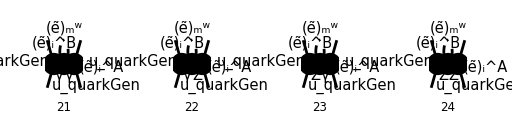

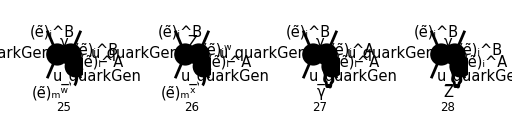

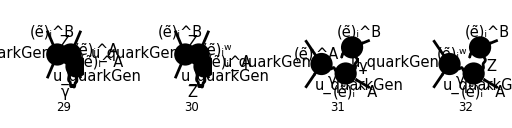

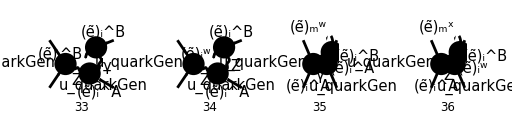

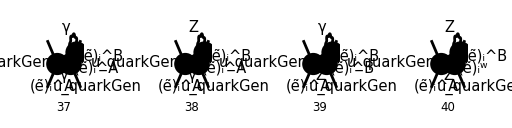

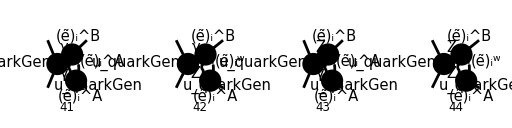

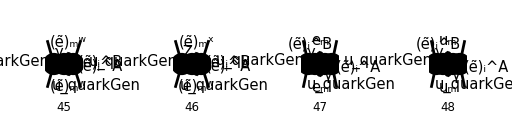

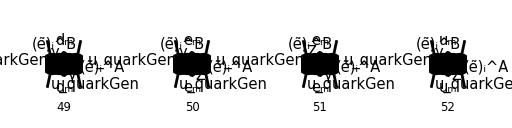

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
V[3],
F[11|12],
S[11|13|14]
}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

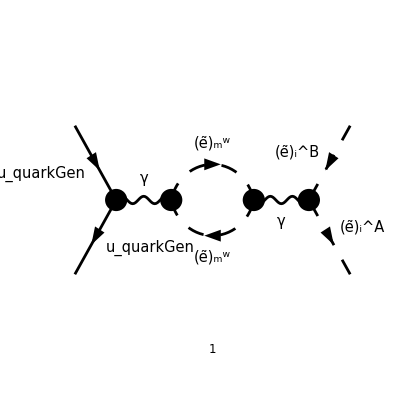

```mathematica
diags[1]=DiagramExtract[diags[0],{60}];
Paint[
diags[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MList[0]=FCFAConvert[
CreateFeynAmp[diags[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{k},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
List->False,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->D
]/.{MQU[quarkGen]->0,MSf[B,2,i]->m1,MSf[A,2,i]->m2}//ZSimplify
```

(e^3 (-2 k+k_1+k_2)^ν (k_2-k_1)^ρ (2 k-k_1-k_2)^σ g^μν g^ρσ IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(φ(p_1)))/(16 π^4 (-k_1-k_2)^2 (k_1+k_2)^2 (k^2-m_l_Gen5Sfe5^2).((k-k_1-k_2)^2-m_l_Gen5Sfe5^2))

```mathematica
MList[0]//TID[#,k,ToPaVe->True]&//Simplify//PaXEvaluateUVIRSplit
```

(((φ(-p_2)).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(φ(p_1))-(φ(-p_2)).(γ·(k_1+k_2)).(φ(p_1))) IndexDelta(A,B) k_1^4 e^4 δ_Col1Col2)/(24 ε_UV (2 ε_UV-3) π^2 (k_1^2+2 (k_1·k_2)+k_2^2) ((k_1+k_2)^2)^2)-1/(24 (2 ε_UV-3) π^2 (k_1^2+2 (k_1·k_2)+k_2^2) ((1)^2)^2)+27+1/1-((1) IndexDelta(A,B) (ℽ-log(4 π)) (k_1·k_2) k_2^2 e^4 δ_Col1Col2)/(12 (2 ε_UV-3) π^2 (k_1^2+2 (k_1·k_2)+k_2^2) (((11)^2)^2)+((((φ(-p_2)).(γ·k_1).(φ(p_1))-1-1) 5 δ_1)/(24 π^2 (1)^2 (((11)^2)^2)+48)/(2 ε_IR-3)
 |  |  |  |

## 19.07

```mathematica
FAD[{k,m1},{p+k,m2}]
%//TID[#,k,ToPaVe->True]&
```

1/((k^2-m_1^2).((k+p)^2-m_2^2))

ⅈ π^2 B_0(p^2,m_1^2,m_2^2)

```mathematica
FAD[{k,m1},{k+p1,m2},{k+p1+p2,m3}]
%//TID[#,k,ToPaVe->True]&
```

1/((k^2-m_1^2).((k+p_1)^2-m_2^2).((k+p_1+p_2)^2-m_3^2))

ⅈ π^2 C_0(p_1^2,p_2^2,p_1^2+2 (p_1·p_2)+p_2^2,m_1^2,m_2^2,m_3^2)

```mathematica
FAD[{k,m1},{k+p1,m2},{k+p1+p2,m3},{k+p1+p2+p3,m4}]
%//TID[#,k,ToPaVe->True]&
```

1/((k^2-m_1^2).((k+p_1)^2-m_2^2).((k+p_1+p_2)^2-m_3^2).((k+p_1+p_2+p3)^2-m4^2))

ⅈ π^2 D_0(p_1^2,p_2^2,p3^2,p_1^2+2 (p_1·p_2)+2 (p_1·p3)+p_2^2+2 (p_2·p3)+p3^2,p_1^2+2 (p_1·p_2)+p_2^2,p_2^2+2 (p_2·p3)+p3^2,m_1^2,m_2^2,m_3^2,m4^2)

## 20.07

```mathematica
FAD[{k,m0},{k+p1,m1},{k+p1+p2,m2},{k+p1+p2+p3,m3}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&
```

-ⅈ/(π^2 (k^2-m_0^2).((k+p_1)^2-m_1^2).((k+p_1+p_2)^2-m_2^2).((k+p_1+p_2+p_3)^2-m_3^2))

D_0(p_1^2,p_2^2,p_3^2,p_1^2+2 (p_1·p_2)+2 (p_1·p_3)+p_2^2+2 (p_2·p_3)+p_3^2,p_1^2+2 (p_1·p_2)+p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,m_0^2,m_1^2,m_2^2,m_3^2)

## 21.07

```mathematica
Eps[α,β,γ,δ]DiracTrace[GA[μ,ν,ρ,σ,α,β,γ,δ]]//DiracSimplify//FullSimplify
```

4 (ϵ̄)^αβγδ ((ḡ)^αν (ḡ)^βσ (ḡ)^γρ (ḡ)^δμ-(ḡ)^αν (ḡ)^βρ (ḡ)^γσ (ḡ)^δμ-(ḡ)^αγ (ḡ)^βσ (ḡ)^νρ (ḡ)^δμ+(ḡ)^αβ (ḡ)^γσ (ḡ)^νρ (ḡ)^δμ+(ḡ)^αγ (ḡ)^βρ (ḡ)^νσ (ḡ)^δμ-(ḡ)^αβ (ḡ)^γρ (ḡ)^νσ (ḡ)^δμ-(ḡ)^αμ (ḡ)^βσ (ḡ)^γρ (ḡ)^δν+(ḡ)^αμ (ḡ)^βρ (ḡ)^γσ (ḡ)^δν-(ḡ)^αν (ḡ)^βσ (ḡ)^γμ (ḡ)^δρ+(ḡ)^αμ (ḡ)^βσ (ḡ)^γν (ḡ)^δρ+(ḡ)^αν (ḡ)^βμ (ḡ)^γσ (ḡ)^δρ-(ḡ)^αμ (ḡ)^βν (ḡ)^γσ (ḡ)^δρ+(ḡ)^αν (ḡ)^βρ (ḡ)^γμ (ḡ)^δσ-(ḡ)^αμ (ḡ)^βρ (ḡ)^γν (ḡ)^δσ-(ḡ)^αν (ḡ)^βμ (ḡ)^γρ (ḡ)^δσ+(ḡ)^αμ (ḡ)^βν (ḡ)^γρ (ḡ)^δσ+(ḡ)^αδ (ḡ)^βσ (ḡ)^γρ (ḡ)^μν-(ḡ)^αδ (ḡ)^βρ (ḡ)^γσ (ḡ)^μν-(ḡ)^αγ (ḡ)^βσ (ḡ)^δρ (ḡ)^μν+(ḡ)^αβ (ḡ)^γσ (ḡ)^δρ (ḡ)^μν+(ḡ)^αγ (ḡ)^βρ (ḡ)^δσ (ḡ)^μν-(ḡ)^αβ (ḡ)^γρ (ḡ)^δσ (ḡ)^μν+(ḡ)^αν (ḡ)^βσ (ḡ)^γδ (ḡ)^μρ-(ḡ)^αδ (ḡ)^βσ (ḡ)^γν (ḡ)^μρ-(ḡ)^αν (ḡ)^βδ (ḡ)^γσ (ḡ)^μρ+(ḡ)^αδ (ḡ)^βν (ḡ)^γσ (ḡ)^μρ+(ḡ)^αγ (ḡ)^βσ (ḡ)^δν (ḡ)^μρ-(ḡ)^αβ (ḡ)^γσ (ḡ)^δν (ḡ)^μρ+(ḡ)^αν (ḡ)^βγ (ḡ)^δσ (ḡ)^μρ-(ḡ)^αγ (ḡ)^βν (ḡ)^δσ (ḡ)^μρ+(ḡ)^αβ (ḡ)^γν (ḡ)^δσ (ḡ)^μρ-(ḡ)^αν (ḡ)^βρ (ḡ)^γδ (ḡ)^μσ+(ḡ)^αδ (ḡ)^βρ (ḡ)^γν (ḡ)^μσ+(ḡ)^αν (ḡ)^βδ (ḡ)^γρ (ḡ)^μσ-(ḡ)^αδ (ḡ)^βν (ḡ)^γρ (ḡ)^μσ-(ḡ)^αγ (ḡ)^βρ (ḡ)^δν (ḡ)^μσ+(ḡ)^αβ (ḡ)^γρ (ḡ)^δν (ḡ)^μσ-(ḡ)^αν (ḡ)^βγ (ḡ)^δρ (ḡ)^μσ+(ḡ)^αγ (ḡ)^βν (ḡ)^δρ (ḡ)^μσ-(ḡ)^αβ (ḡ)^γν (ḡ)^δρ (ḡ)^μσ-(ḡ)^αμ (ḡ)^βσ (ḡ)^γδ (ḡ)^νρ+(ḡ)^αδ (ḡ)^βσ (ḡ)^γμ (ḡ)^νρ+(ḡ)^αμ (ḡ)^βδ (ḡ)^γσ (ḡ)^νρ-(ḡ)^αδ (ḡ)^βμ (ḡ)^γσ (ḡ)^νρ-(ḡ)^αμ (ḡ)^βγ (ḡ)^δσ (ḡ)^νρ+(ḡ)^αγ (ḡ)^βμ (ḡ)^δσ (ḡ)^νρ-(ḡ)^αβ (ḡ)^γμ (ḡ)^δσ (ḡ)^νρ+(ḡ)^αδ (ḡ)^βγ (ḡ)^μσ (ḡ)^νρ-(ḡ)^αγ (ḡ)^βδ (ḡ)^μσ (ḡ)^νρ+(ḡ)^αβ (ḡ)^γδ (ḡ)^μσ (ḡ)^νρ+(ḡ)^ασ ((ḡ)^βμ (ḡ)^γρ (ḡ)^δν-(ḡ)^βγ (ḡ)^μρ (ḡ)^δν-(ḡ)^βμ (ḡ)^γν (ḡ)^δρ-(ḡ)^βδ (ḡ)^γρ (ḡ)^μν+(ḡ)^βγ (ḡ)^δρ (ḡ)^μν+(ḡ)^βρ ((ḡ)^γν (ḡ)^δμ-(ḡ)^γμ (ḡ)^δν+(ḡ)^γδ (ḡ)^μν)+(ḡ)^βδ (ḡ)^γν (ḡ)^μρ-(ḡ)^βν ((ḡ)^γρ (ḡ)^δμ-(ḡ)^γμ (ḡ)^δρ+(ḡ)^γδ (ḡ)^μρ)+((ḡ)^βμ (ḡ)^γδ-(ḡ)^βδ (ḡ)^γμ+(ḡ)^βγ (ḡ)^δμ) (ḡ)^νρ)+(ḡ)^αμ (ḡ)^βρ (ḡ)^γδ (ḡ)^νσ-(ḡ)^αδ (ḡ)^βρ (ḡ)^γμ (ḡ)^νσ-(ḡ)^αμ (ḡ)^βδ (ḡ)^γρ (ḡ)^νσ+(ḡ)^αδ (ḡ)^βμ (ḡ)^γρ (ḡ)^νσ+(ḡ)^αμ (ḡ)^βγ (ḡ)^δρ (ḡ)^νσ-(ḡ)^αγ (ḡ)^βμ (ḡ)^δρ (ḡ)^νσ+(ḡ)^αβ (ḡ)^γμ (ḡ)^δρ (ḡ)^νσ-(ḡ)^αδ (ḡ)^βγ (ḡ)^μρ (ḡ)^νσ+(ḡ)^αγ (ḡ)^βδ (ḡ)^μρ (ḡ)^νσ-(ḡ)^αβ (ḡ)^γδ (ḡ)^μρ (ḡ)^νσ-(ḡ)^αρ ((ḡ)^βμ (ḡ)^γσ (ḡ)^δν-(ḡ)^βγ (ḡ)^μσ (ḡ)^δν-(ḡ)^βμ (ḡ)^γν (ḡ)^δσ-(ḡ)^βδ (ḡ)^γσ (ḡ)^μν+(ḡ)^βγ (ḡ)^δσ (ḡ)^μν+(ḡ)^βσ ((ḡ)^γν (ḡ)^δμ-(ḡ)^γμ (ḡ)^δν+(ḡ)^γδ (ḡ)^μν)+(ḡ)^βδ (ḡ)^γν (ḡ)^μσ-(ḡ)^βν ((ḡ)^γσ (ḡ)^δμ-(ḡ)^γμ (ḡ)^δσ+(ḡ)^γδ (ḡ)^μσ)+((ḡ)^βμ (ḡ)^γδ-(ḡ)^βδ (ḡ)^γμ+(ḡ)^βγ (ḡ)^δμ) (ḡ)^νσ)+((ḡ)^αδ (ḡ)^βν (ḡ)^γμ-(ḡ)^αβ (ḡ)^δν (ḡ)^γμ-(ḡ)^αδ (ḡ)^βμ (ḡ)^γν-(ḡ)^αγ (ḡ)^βν (ḡ)^δμ+(ḡ)^αβ (ḡ)^γν (ḡ)^δμ+(ḡ)^αν ((ḡ)^βμ (ḡ)^γδ-(ḡ)^βδ (ḡ)^γμ+(ḡ)^βγ (ḡ)^δμ)+(ḡ)^αγ (ḡ)^βμ (ḡ)^δν-(ḡ)^αμ ((ḡ)^βν (ḡ)^γδ-(ḡ)^βδ (ḡ)^γν+(ḡ)^βγ (ḡ)^δν)+((ḡ)^αδ (ḡ)^βγ-(ḡ)^αγ (ḡ)^βδ+(ḡ)^αβ (ḡ)^γδ) (ḡ)^μν) (ḡ)^ρσ)

```mathematica
DiracTrace[GA[μ,ν,ρ,σ,5]]//DiracSimplify
DiracTrace[GA[μ,ν,ρ,σ,α,β,5]]//DiracSimplify
DiracTrace[GA[μ,ν,ρ,σ,α,β,γ,δ,5]]//DiracSimplify
```

-4 ⅈ (ϵ̄)^μνρσ

-4 ⅈ (ḡ)^αβ (ϵ̄)^μνρσ+4 ⅈ (ḡ)^αμ (ϵ̄)^βνρσ-4 ⅈ (ḡ)^βμ (ϵ̄)^ανρσ-4 ⅈ (ḡ)^νρ (ϵ̄)^αβμσ+4 ⅈ (ḡ)^νσ (ϵ̄)^αβμρ-4 ⅈ (ḡ)^ρσ (ϵ̄)^αβμν

-4 ⅈ (ḡ)^αδ (ḡ)^βγ (ϵ̄)^μνρσ+4 ⅈ (ḡ)^αμ (ḡ)^βγ (ϵ̄)^δνρσ-4 ⅈ (ḡ)^βγ (ḡ)^δμ (ϵ̄)^ανρσ-4 ⅈ (ḡ)^βγ (ḡ)^νρ (ϵ̄)^αδμσ+4 ⅈ (ḡ)^βγ (ḡ)^νσ (ϵ̄)^αδμρ-4 ⅈ (ḡ)^βγ (ḡ)^ρσ (ϵ̄)^αδμν+4 ⅈ (ḡ)^αγ (ḡ)^βδ (ϵ̄)^μνρσ-4 ⅈ (ḡ)^αμ (ḡ)^βδ (ϵ̄)^γνρσ-4 ⅈ (ḡ)^αγ (ḡ)^βμ (ϵ̄)^δνρσ+4 ⅈ (ḡ)^αδ (ḡ)^βμ (ϵ̄)^γνρσ-4 ⅈ (ḡ)^αβ (ḡ)^γδ (ϵ̄)^μνρσ+4 ⅈ (ḡ)^αμ (ḡ)^γδ (ϵ̄)^βνρσ-4 ⅈ (ḡ)^βμ (ḡ)^γδ (ϵ̄)^ανρσ+4 ⅈ (ḡ)^αβ (ḡ)^γμ (ϵ̄)^δνρσ-4 ⅈ (ḡ)^αδ (ḡ)^γμ (ϵ̄)^βνρσ+4 ⅈ (ḡ)^βδ (ḡ)^γμ (ϵ̄)^ανρσ-4 ⅈ (ḡ)^αβ (ḡ)^δμ (ϵ̄)^γνρσ+4 ⅈ (ḡ)^αγ (ḡ)^δμ (ϵ̄)^βνρσ-4 ⅈ (ḡ)^αβ (ḡ)^νρ (ϵ̄)^γδμσ+4 ⅈ (ḡ)^αγ (ḡ)^νρ (ϵ̄)^βδμσ-4 ⅈ (ḡ)^δμ (ḡ)^νρ (ϵ̄)^αβγσ+4 ⅈ (ḡ)^δσ (ḡ)^νρ (ϵ̄)^αβγμ-4 ⅈ (ḡ)^μσ (ḡ)^νρ (ϵ̄)^αβγδ+4 ⅈ (ḡ)^αβ (ḡ)^νσ (ϵ̄)^γδμρ-4 ⅈ (ḡ)^αγ (ḡ)^νσ (ϵ̄)^βδμρ+4 ⅈ (ḡ)^δμ (ḡ)^νσ (ϵ̄)^αβγρ-4 ⅈ (ḡ)^δρ (ḡ)^νσ (ϵ̄)^αβγμ+4 ⅈ (ḡ)^μρ (ḡ)^νσ (ϵ̄)^αβγδ-4 ⅈ (ḡ)^αβ (ḡ)^ρσ (ϵ̄)^γδμν+4 ⅈ (ḡ)^αγ (ḡ)^ρσ (ϵ̄)^βδμν-4 ⅈ (ḡ)^δμ (ḡ)^ρσ (ϵ̄)^αβγν+4 ⅈ (ḡ)^δν (ḡ)^ρσ (ϵ̄)^αβγμ-4 ⅈ (ḡ)^μν (ḡ)^ρσ (ϵ̄)^αβγδ

## 01.08

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,m1,m2];
```

```mathematica
expr[0]=SpinorVBarD[p2].GAD[μ].SpinorUD[p1]MTD[μ,ν]MTD[ρ,σ]FVD[k2-k1,σ]FVD[p+2k,ν]FVD[p+2k,ρ]FAD[{k,m3},{p+k,m4}]//ReplaceAll[#,p->p1+p2]&//Contract//DiracSimplify//TID[#,k,ToPaVe->True]&//FullSimplify//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//Simplify
```

1/((D-1) s^2)ⅈ π^2 (B_0(s,m_3^2,m4^2) ((m_1^2-m_2^2) (-2 (D-1) s (m_3^2-m4^2) (φ(-p_2)).(γ·p_1).(φ(p_1))-2 (D-1) s (m_3^2-m4^2) (φ(-p_2)).(γ·p_2).(φ(p_1))+(D (m_3^2-m4^2) (m_3^2-m4^2-s)+s (-m_3^2-3 m4^2+s)) (φ(-p_2)).(-(γ·(p_1+p_2))).(φ(p_1)))+s (-2 m_3^2 (m4^2+s)+m_3^4+(m4^2-s)^2) (φ(-p_2)).(γ·k_1).(φ(p_1))-s (-2 m_3^2 (m4^2+s)+m_3^4+(m4^2-s)^2) (φ(-p_2)).(γ·k_2).(φ(p_1)))+A_0(m4^2) (-(m_1^2-m_2^2) ((D (m4^2-m_3^2)+s) (φ(-p_2)).(-(γ·(p_1+p_2))).(φ(p_1))+2 (D-1) s (φ(-p_2)).(γ·p_1).(φ(p_1))+2 (D-1) s (φ(-p_2)).(γ·p_2).(φ(p_1)))+s (m_3^2-m4^2-s) (φ(-p_2)).(γ·k_1).(φ(p_1))+s (-m_3^2+m4^2+s) (φ(-p_2)).(γ·k_2).(φ(p_1)))+A_0(m_3^2) ((m_1^2-m_2^2) ((D (-m_3^2+m4^2+2 s)-3 s) (φ(-p_2)).(-(γ·(p_1+p_2))).(φ(p_1))+2 (D-1) s (φ(-p_2)).(γ·p_1).(φ(p_1))+2 (D-1) s (φ(-p_2)).(γ·p_2).(φ(p_1)))-s (m_3^2-m4^2+s) (φ(-p_2)).(γ·k_1).(φ(p_1))+s (m_3^2-m4^2+s) (φ(-p_2)).(γ·k_2).(φ(p_1))))

```mathematica
expr[0]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//ReplaceAll[#,k2->p1+p2-k1]&//DiracSimplify//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&
```

-(2 ⅈ KK(2231))/(3 ε_UV)-1/9 ⅈ KK(2250)

```mathematica
KK[2231]//FRH//FullSimplify
```

π^2 (3 (m_3^2+m4^2)-s) (φ(-p_2)).(γ·k_1).(φ(p_1))

```mathematica
otherExpr[0]=SpinorVBarD[p2].GAD[μ].SpinorUD[p1]MTD[μ,ν]MTD[ρ,σ]FVD[k2-k1,σ]DiracTrace[GSD[k].GAD[ρ].GSD[p+k].GAD[ν]]FAD[k,p+k]
%//Contract//ReplaceAll[#,{p->p1+p2,k2->p1+p2-k1}]&//DiracSimplify//FullSimplify//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//FullSimplify//TID[#,k,ToPaVe->True]&//FullSimplify//TrickMandelstam[#,{s,t,u,m1^2+m2^2}]&//DiracSimplify//Simplify
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify,IsolateNames->KK]&
```

((k_2-k_1)^σ g^μν g^ρσ v̄(p_2).γ^μ.u(p_1) tr((γ·k).γ^ρ.(γ·(k+p)).γ^ν))/(k^2.(k+p)^2)

-(4 ⅈ π^2 (D-2) s B_0(s,0,0) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(D-1)

8/9 ⅈ KK(5940)-(8 ⅈ KK(5938))/(3 ε_UV)

```mathematica
KK[5938]//FRH
```

π^2 s (φ(-p_2)).(γ·k_1).(φ(p_1))

```mathematica
KK[5940]//FRH
```

π^2 s (-3 log(-(4 π μ^2)/s)+3 ℽ-5) (φ(-p_2)).(γ·k_1).(φ(p_1))

## 06.08

```mathematica
DiracTrace[GAD[μ].GSD[k].GAD[ν].GSD[k+p]]FAD[k,k+p]
%//TID[#,k,ToPaVe->True]&//FullSimplify
%//FCE//SelectNotFree2[#,MTD[μ,ν]]&
%//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&
```

(tr(γ^μ.(γ·k).γ^ν.(γ·(k+p))))/(k^2.(k+p)^2)

-(2 ⅈ π^2 (D-2) B_0(p^2,0,0) (p^μ p^ν-p^2 g^μν))/(D-1)

(2 ⅈ π^2 (D-2) p^2 g^μν B_0(p^2,0,0))/(D-1)

(4 ⅈ π^2 p^2 g^μν)/(3 ε_UV)-4/9 ⅈ π^2 p^2 g^μν (-3 log(-(π μ^2)/p^2)+3 ℽ-5-6 log(2))

### Realized I have wrong expression for L1 in thesis: checking for correct answer here

```mathematica
expr[0]=-1/2 (s^2-(m1^2-m2^2)^2)(1/SPD[k1,k]+1/SPD[k2,k])+(1/4(s-(m1^2+m2^2))^2 -m1^2m2^2)(m1^2/SPD[k1,k]^2+m2^2/SPD[k2,k]^2)+(s-(m1^2+m2^2))(1/4(s+(m1^2+m2^2))^2-1/2(m1^4+m2^4+s Q^2))/(SPD[k1,k]SPD[k2,k])
```

((-m_1^2-m_2^2+s) (1/2 (-m_1^4-m_2^4-Q^2 s)+1/4 (m_1^2+m_2^2+s)^2))/((k·k_1) (k·k_2))-1/2 (1/(k·k_2)+1/(k·k_1)) (s^2-(m_1^2-m_2^2)^2)+(1/4 (-m_1^2-m_2^2+s)^2-m_1^2 m_2^2) (m_1^2/(k·k_1)^2+m_2^2/(k·k_2)^2)

```mathematica
expr[1]=expr[0]//Together//FullSimplify
```

((k·k_2) (k·k_1) (2 (k·k_2) ((m_1^2-m_2^2)^2-s^2)+(m_1^2+m_2^2-s) (-2 s (m_1^2+m_2^2-Q^2)+(m_1^2-m_2^2)^2-s^2))+(k·k_1)^2 (2 (k·k_2) ((m_1^2-m_2^2)^2-s^2)+m_2^2 (-2 m_1^2 (m_2^2+s)+(m_2^2-s)^2+m_1^4))+m_1^2 (k·k_2)^2 ((m_1-m_2)^2-s) ((m_1+m_2)^2-s))/(4 (k·k_1)^2 (k·k_2)^2)

```mathematica
expr[2]=expr[1]//FCE//ReplaceAll[#,{
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x)
}]&//FullSimplify[#,Assumptions->{
s∈PositiveReals,
z∈PositiveReals,
x∈PositiveReals,
Q∈PositiveReals,
m1∈PositiveReals,
m2∈PositiveReals
}]&//ReplaceAll[#,s->Q^2/z]&//FullSimplify
```

(4 ((x-1) (Q^2 (x+1)-2 m_2^2)+2 m_1^2 (x+1)) (-2 (m_1^2+m_2^2) Q^2 z+(m_1^2-m_2^2)^2 z^2+Q^4))/(Q^4 (x^2-1)^2 (z-1)^2)

```mathematica
exprFinal[0]=λs/(4SPD[k1,k]^2SPD[k2,k]^2)(1/2(s-Q^2)(m1^2SPD[k2,k]+m2^2SPD[k1,k])-Q^2SPD[k1,k]SPD[k2,k])
exprFinal[1]=exprFinal[0]//FCE//ReplaceAll[#,{
SPD[k1,k]->s/4(1-z)(1-x),
SPD[k2,k]->s/4(1-z)(1+x),
λs->s^2+m1^4+m2^4-2s(m1^2+m2^2)-2m1^2m2^2
}]&//ReplaceAll[#,s->Q^2/z]&//FullSimplify
```

(λ_s (1/2 (s-Q^2) (m_1^2 (k·k_2)+m_2^2 (k·k_1))-Q^2 (k·k_1) (k·k_2)))/(4 (k·k_1)^2 (k·k_2)^2)

(4 ((x-1) (Q^2 (x+1)-2 m_2^2)+2 m_1^2 (x+1)) (-2 (m_1^2+m_2^2) Q^2 z+(m_1^2-m_2^2)^2 z^2+Q^4))/(Q^4 (x^2-1)^2 (z-1)^2)

```mathematica
expr[2]-exprFinal[1]//FullSimplify
```

0